```mathematica
Needs["Greater2`"]
```

GREATER has been loaded. Some functions = antisymmetrize, CoD (covariant derivative), Contract, ds2met (covert line element to metric), Epsilon, KillingEquations, SimpleDeriv (partial derivative), LieD (Lie derivative), ChangeCoords, DAlembertian , FieldStrength (F = dA), IndexShift, symmetrize, TJacobian, Trans2rules, SelfContract, CottonTensor, wedge, ExtrinsicCurvature, ShowComponents

Needs::nocont: Context Greater2` was not created when Needs was evaluated.

#### Module for getting expanded EFEs

```mathematica
Clear[ExpandEFEsinμ]
Xη= {t,x,y,z,η};
ExpandEFEsinμ[gη_,ϕ_,μc_]:=Module[{detgη,Xη,RTη,Rη,GTη,ϕeqnη,TTη,EFEη,EFEseries,ϕeqnseries,Rηseries},

(*detgη=Simplify[Det[gη]];*)
detgη=Det[gη];

Xη= {t,x,y,z,η};
RTη=Ricci[gη,Xη]; 

(*Rη =Simplify[Tr[RTη.Inverse[gη]]];*)
Rη =Tr[RTη.Inverse[gη]];


(*GTη=Simplify[(RTη-1/2 gη Rη).Inverse[gη]];*)(*1 upper one lower index*)
GTη=(RTη-1/2 gη Rη).Inverse[gη];

(*ϕeqnη=Simplify[1/(√-detgη)D[(√-detgη)/gη[[5,5]] D[ϕ,η],η]]+(D[V[ψ]+λ[ψ] ,ψ]/.ψ->ϕ);*)
ϕeqnη=1/(√-detgη)D[(√-detgη)/gη[[5,5]] D[ϕ,η],η]+(D[V[ψ]+λ[ψ] ,ψ]/.ψ->ϕ);

TTη =( DiagonalMatrix[{0,0,0,0,1}]D[ϕ,η]D[ϕ,η] - gη(gη[[5,5]] 1/2 D[ϕ,η]D[ϕ,η]+12/(κ l^2)-V[ϕ] ) +(gη-DiagonalMatrix[{0,0,0,0,-1}]) λ[ϕ]).Inverse[gη];

EFEη=GTη-κ TTη;

EFEseries=Series[EFEη,{μ,0,μc}]//Normal;

ϕeqnseries=Series[ϕeqnη,{μ,0,μc}]//Normal;

Rηseries = Series[Rη,{μ,0,μc}]//Normal;

<|"detgη"->detgη,"EFE"->EFEη,"ϕeqn"->ϕeqnη,"Rη"->Rη,"EFEseries"->Coefficient[EFEseries,μ,μc],"ϕeqnseries"->Coefficient[ϕeqnseries,μ,μc],"Rηseries"->Coefficient[Rηseries,μ,μc],"gη"->gη|>

]
```

```mathematica
shη=μ^(1/2)Sinh[-2 η/l-1/2 Log[μ]]
chη=μ^(1/2)Cosh[-2 η/l-1/2 Log[μ]]
```

-√μ Sinh[(2 η)/l+Log[μ]/2]

√μ Cosh[(2 η)/l+Log[μ]/2]

```mathematica
μ^(1/2)Sinh[-1/2 Log[ξ]]/.ξ->μ E^(4 η/l)//PowerExpand//Simplify
μ^(1/2)Cosh[-1/2 Log[ξ]]/.ξ->μ E^(4 η/l)//PowerExpand//Simplify
```

-√μ Sinh[(2 η)/l+Log[μ]/2]

√μ Cosh[(2 η)/l+Log[μ]/2]

#### Expand in μ and get GN coordinate

Rescale so that p and μ are dimensionless

```mathematica
p[η]->l p[η]
μ/l^2->μ
dp[η]/(√(p[η]^2/l^2-μ/p[η]^2))-> (l dp[η])/(√(p[η]^2-μ/p[η]^2))
```

p[η]→l p[η]

μ/l^2→μ

dp[η]/(√(-μ/p[η]^2+p[η]^2/l^2))→(l dp[η])/(√(-μ/p[η]^2+p[η]^2))

```mathematica
shη
```

-√μ Sinh[(2 η)/l+Log[μ]/2]

```mathematica
FrontEndExecute[FrontEndToken["Save"]]
```

Then solve for gaussian normal coordinate

```mathematica
pofη=Simplify[p[η]/.DSolve[l D[p[η],η]==-√(p[η]^2-μ/p[η]^2),p[η],η]][[2]]
ηofp=η/.Solve[pofη==p,η][[4]]//Simplify
Simplify[E^(-ηofp/l)]
(*as η gets large, p gets small, these coordinates are only defined for p^4 > μ*)
```

(√(ⅇ^(-2 (η/l+C[1])) (ⅇ^(4 C[1])+ⅇ^((4 η)/l) μ)))/(√2)

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

l (C[1]-1/2 Log[p^2+√(p^4-μ)])

ⅇ^(-C[1]) √(p^2+√(p^4-μ))

```mathematica
shη/.η->ηofp/.C[1]->0//TrigToExp//FullSimplify
chη/.η->ηofp/.C[1]->0//TrigToExp//FullSimplify
```

√(p^4-μ)

p^2

```mathematica
Print["What is the value of η corresponding to the position of the horizon?"]
p[η]^2-μ/p[η]^2/.p[η]->pofη/.C[1]->1/2 Log[2]//FullSimplify
Solve[%==0,μ]
μofηhsol=%[[2]]/.C[1]->0/.η->ηh
Print["So we can write μ in terms of this ηh"]
```

What is the value of η corresponding to the position of the horizon?

(ⅇ^(-(2 η)/l) (-4+ⅇ^((4 η)/l) μ)^2)/(4 (4+ⅇ^((4 η)/l) μ))

{{μ→4 ⅇ^(-(4 η)/l)},{μ→4 ⅇ^(-(4 η)/l)}}

{μ→4 ⅇ^(-(4 ηh)/l)}

So we can write μ in terms of this ηh

Then find the tt and ij metric components (substituting A for η/l and choosing the integration constant so that it reduces to AdS in μ->0 limit)

```mathematica
FullSimplify[p[η]^2/.p[η]->pofη]
gii=%/.C[1]->1/2 Log[2]//Simplify
Simplify[p[η]^2-μ/p[η]^2/.p[η]->pofη]
gtt=Simplify[%/.C[1]->1/2 Log[2]]
```

1/2 ⅇ^(-2 (η/l+C[1])) (ⅇ^(4 C[1])+ⅇ^((4 η)/l) μ)

ⅇ^(-(2 η)/l)+1/4 ⅇ^((2 η)/l) μ

(ⅇ^(-2 (η/l+C[1])) (ⅇ^(4 C[1])-ⅇ^((4 η)/l) μ)^2)/(2 (ⅇ^(4 C[1])+ⅇ^((4 η)/l) μ))

(ⅇ^(-(2 η)/l) (-4+ⅇ^((4 η)/l) μ)^2)/(4 (4+ⅇ^((4 η)/l) μ))

```mathematica
"Same thing with c0 = 0"
FullSimplify[p[η]^2/.p[η]->pofη];
%/.C[1]->0//Simplify
Simplify[p[η]^2-μ/p[η]^2/.p[η]->pofη];
Simplify[%/.C[1]->0]
μ^(1/2)Sinh[-2 η/l-1/2 Log[μ]]//TrigToExp
μ^(1/2)Cosh[-2 η/l-1/2 Log[μ]]//TrigToExp//Simplify
(%%)^2/%//Simplify
```

Same thing with c0 = 0

1/2 ⅇ^(-(2 η)/l) (1+ⅇ^((4 η)/l) μ)

(ⅇ^(-(2 η)/l) (-1+ⅇ^((4 η)/l) μ)^2)/(2 (1+ⅇ^((4 η)/l) μ))

1/2 ⅇ^(-(2 η)/l)-1/2 ⅇ^((2 η)/l) μ

1/2 ⅇ^(-(2 η)/l) (1+ⅇ^((4 η)/l) μ)

(ⅇ^(-(2 η)/l) (-1+ⅇ^((4 η)/l) μ)^2)/(2 (1+ⅇ^((4 η)/l) μ))

Note that these can be represented as hyperbolic trig functions

```mathematica
fht[η]=μ^(1/2)Sinh[-2 η/l-1/2 Log[μ]]
ght[η]=μ^(1/2)Cosh[-2 η/l-1/2 Log[μ]]

TrigToExp[ght[η]]//Simplify
TrigToExp[fht[η]]//Simplify
fht[η]^2/ght[η]//TrigToExp//Simplify
ght[η]//TrigToExp
```

-√μ Sinh[(2 η)/l+Log[μ]/2]

√μ Cosh[(2 η)/l+Log[μ]/2]

1/2 ⅇ^(-(2 η)/l) (1+ⅇ^((4 η)/l) μ)

-1/2 ⅇ^(-(2 η)/l) (-1+ⅇ^((4 η)/l) μ)

(ⅇ^(-(2 η)/l) (-1+ⅇ^((4 η)/l) μ)^2)/(2 (1+ⅇ^((4 η)/l) μ))

1/2 ⅇ^(-(2 η)/l)+1/2 ⅇ^((2 η)/l) μ

```mathematica
fht[η]=μ^(1/2)Sinh[-2 η/l-1/2 Log[μ/4]]
ght[η]=μ^(1/2)Cosh[-2 η/l-1/2 Log[μ/4]]

TrigToExp[ght[η]]//Simplify
TrigToExp[fht[η]]//Simplify
fht[η]^2/ght[η]//TrigToExp//Simplify
ght[η]//TrigToExp
```

-√μ Sinh[(2 η)/l+1/2 Log[μ/4]]

√μ Cosh[(2 η)/l+1/2 Log[μ/4]]

ⅇ^(-(2 η)/l)+1/4 ⅇ^((2 η)/l) μ

ⅇ^(-(2 η)/l)-1/4 ⅇ^((2 η)/l) μ

(ⅇ^(-(2 η)/l) (-4+ⅇ^((4 η)/l) μ)^2)/(4 (4+ⅇ^((4 η)/l) μ))

ⅇ^(-(2 η)/l)+1/4 ⅇ^((2 η)/l) μ

Expand to next to leading order in μ

```mathematica
Series[gii,{μ,0,2}]
Series[gtt,{μ,0,2}]
```

ⅇ^(-(2 η)/l)+1/4 ⅇ^((2 η)/l) μ+O[μ]^3

ⅇ^(-(2 η)/l)-3/4 ⅇ^((2 η)/l) μ+1/4 ⅇ^((6 η)/l) μ^2+O[μ]^3

```mathematica
Series[ght[η],{μ,0,3}]//TrigToExp
Series[fht[η]^2/ght[η],{μ,0,3}]//TrigToExp
```

ⅇ^(-(2 η)/l)-1/4 ⅇ^((2 η)/l) μ+O[μ]^3

ⅇ^(-(2 η)/l)+3/4 ⅇ^((2 η)/l) μ+1/4 ⅇ^((6 η)/l) μ^2+O[μ]^3

```mathematica
√μ Cosh[2 η/l-1/2 Log[μ]]//TrigToExp
√μ Sinh[2 η/l-1/2 Log[μ]]//TrigToExp
(√μ Sinh[2 η/l-1/2 Log[μ]])^2/(√μ Cosh[2 η/l-1/2 Log[μ]])//TrigToExp//Simplify
```

1/2 ⅇ^((2 η)/l)+1/2 ⅇ^(-(2 η)/l) μ

1/2 ⅇ^((2 η)/l)-1/2 ⅇ^(-(2 η)/l) μ

(ⅇ^(-(2 η)/l) (ⅇ^((4 η)/l)-μ)^2)/(2 (ⅇ^((4 η)/l)+μ))

```mathematica
ght[η]=ⅇ^((2 η)/l)+1/4 ⅇ^(-(2 η)/l) μ
fht[η]=ⅇ^((2 η)/l)-1/4 ⅇ^(-(2 η)/l) μ
fht[η]^2/ght[η]//Simplify
TrigToExp[ght[η]]//Simplify
TrigToExp[fht[η]]//Simplify

D[ght[η],η]==2/l fht[η]
D[fht[η],η]==2/l ght[η]
```

ⅇ^((2 η)/l)+1/4 ⅇ^(-(2 η)/l) μ

ⅇ^((2 η)/l)-1/4 ⅇ^(-(2 η)/l) μ

(ⅇ^(-(2 η)/l) (-4 ⅇ^((4 η)/l)+μ)^2)/(4 (4 ⅇ^((4 η)/l)+μ))

ⅇ^((2 η)/l)+1/4 ⅇ^(-(2 η)/l) μ

ⅇ^((2 η)/l)-1/4 ⅇ^(-(2 η)/l) μ

(2 ⅇ^((2 η)/l))/l-(ⅇ^(-(2 η)/l) μ)/(2 l)==(2 (ⅇ^((2 η)/l)-1/4 ⅇ^(-(2 η)/l) μ))/l

(2 ⅇ^((2 η)/l))/l+(ⅇ^(-(2 η)/l) μ)/(2 l)==(2 (ⅇ^((2 η)/l)+1/4 ⅇ^(-(2 η)/l) μ))/l

```mathematica
ght[η]=μ^(1/2)Sinh[-2 η/l-1/2 Log[μ/4]]
fht[η]=μ^(1/2)Cosh[-2 η/l-1/2 Log[μ/4]]
```

-√μ Sinh[(2 η)/l+1/2 Log[μ/4]]

√μ Cosh[(2 η)/l+1/2 Log[μ/4]]

#### Where is this small horizon compared to the IR brane at it’s (minimum?)

```mathematica
Print["Restoring the factors of AdS curvature:"]
μ/l^2 E^(4 ηIR/l)
1/ϵp Log[ϕIR/ϕUV] (*37*)
Log10@(E^(4 37))//N
(*Print["This implies that μ has to be more than 32 orders of magnitude below the AdS curvature. If it is comparable to the planck scale, this means the hierarchy between horizon temperature and the "]*)

Print["What is the horizon temperature in terms of μ?"]
Solve[ph^2-μ/ph^2==0,ph][[4]]
Thofμ = ph/(π l)/.%
Print["μ<< E^(-4 FractionBox[ηIR , l]) implies the horizon temperature T(μ) must be much less than"]
(*Th/.μ->l^2 E^(-4 ηIR/l)//PowerExpand*)
Thofμ/.μ->ξ  E^(-4 ηIR/l)//PowerExpand
Print["Where ξ is the dimensionless expansion parameter. So we have that Th < π E_EW. So there is some supercooling needed to make this work. But not much, eg for ξ of 10^-2 the temperature is"]
%%/.ξ->10^-2
Print["Which for l = (M_(4  D))/10 gives a factor of 100 below the weak scale. The temperature in terms of ηh is"]
Thofηh=Thofμ/.μofηhsol//PowerExpand
```

Restoring the factors of AdS curvature:

(ⅇ^((4 ηIR)/l) μ)/l^2

Log[ϕIR/ϕUV]/ϵp

64.2756

What is the horizon temperature in terms of μ?

{ph→μ^(1/4)}

μ^(1/4)/(l π)

μ<< E^(-4 FractionBox[ηIR , l]) implies the horizon temperature T(μ) must be much less than

(ⅇ^(-ηIR/l) ξ^(1/4))/(l π)

Where ξ is the dimensionless expansion parameter. So we have that Th < π E_EW. So there is some supercooling needed to make this work. But not much, eg for ξ of 10^-2 the temperature is

ⅇ^(-ηIR/l)/(√10 l π)

Which for l = (M_(4  D))/10 gives a factor of 100 below the weak scale. The temperature in terms of ηh is

(√2 ⅇ^(-ηh/l))/(l π)

Which for 1/l= (M_(4  D))/10 gives a factor of 100 below the weak scale

#### Compare to CR far from horizon solution

```mathematica
FullSimplify[p[η]^2/.p[η]->pofη]
%/.C[1]->1/4 Log[μ]//Simplify
Simplify[p[η]^2-μ/p[η]^2/.p[η]->pofη]
Simplify[%/.C[1]->1/4 Log[μ]]
fht[η]=μ^(1/2)Sinh[-2 η/l]
ght[η]=μ^(1/2)Cosh[-2 η/l]

TrigToExp[ght[η]]//Simplify
TrigToExp[fht[η]]//Simplify
fht[η]^2/ght[η]//TrigToExp//Simplify
ght[η]//TrigToExp
```

1/2 ⅇ^(-2 (η/l+C[1])) (ⅇ^(4 C[1])+ⅇ^((4 η)/l) μ)

1/2 ⅇ^(-(2 η)/l) (1+ⅇ^((4 η)/l)) √μ

(ⅇ^(-2 (η/l+C[1])) (ⅇ^(4 C[1])-ⅇ^((4 η)/l) μ)^2)/(2 (ⅇ^(4 C[1])+ⅇ^((4 η)/l) μ))

(ⅇ^(-(2 η)/l) (-1+ⅇ^((4 η)/l))^2 √μ)/(2 (1+ⅇ^((4 η)/l)))

-√μ Sinh[(2 η)/l]

√μ Cosh[(2 η)/l]

1/2 ⅇ^(-(2 η)/l) (1+ⅇ^((4 η)/l)) √μ

-1/2 ⅇ^(-(2 η)/l) (-1+ⅇ^((4 η)/l)) √μ

(ⅇ^(-(2 η)/l) (-1+ⅇ^((4 η)/l))^2 √μ)/(2 (1+ⅇ^((4 η)/l)))

1/2 ⅇ^(-(2 η)/l) √μ+1/2 ⅇ^((2 η)/l) √μ

```mathematica
Print["Note that the reason the horizon didn't show up in our expressions at 1st oder in μ (contrary to eqn 37 of CR) is that η has implicit μ dependence. "]
pofη=Simplify[p[η]/.DSolve[l D[p[η],η]==-√(p[η]^2-μ/p[η]^2),p[η],η]][[2]]
ηofp=η/.Solve[pofη==p,η][[4]]//Simplify
Print["Taking a different integration constant for η to match onto CR we have"]
ϕUV E^((-ϵ η)/l)/.η->ηofp/.C[1]->1/4 Log[μ]/.p->μ^(1/4)ξ//FullSimplify//PowerExpand//Simplify
Series[%,{ξ,∞,4}]//PowerExpand//Simplify//Normal
%/.ξ->p μ^(-1/4)//Simplify
Print["This is almost the expression in (37) of CR "]
ϕUV E^((-ϵ η)/l)/.η->ηofp/.C[1]->1/2 Log[2]/.p->μ^(1/4)ξ//FullSimplify//PowerExpand//Simplify
Series[%,{ξ,∞,4}]//PowerExpand//Simplify//Normal
%/.ξ->p μ^(-1/4)//Simplify//PowerExpand
```

Note that the reason the horizon didn't show up in our expressions at 1st oder in μ (contrary to eqn 37 of CR) is that η has implicit μ dependence.

(√(ⅇ^(-2 (η/l+C[1])) (ⅇ^(4 C[1])+ⅇ^((4 η)/l) μ)))/(√2)

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

l (C[1]-1/2 Log[p^2+√(p^4-μ)])

Taking a different integration constant for η to match onto CR we have

μ^(-ϵ/4) (√μ (ξ^2+√(-1+ξ^4)))^(ϵ/2) ϕUV

ξ^ϵ (2^(ϵ/2) ϕUV-(2^(-3+ϵ/2) ϵ ϕUV)/ξ^4)

(2^(-3+ϵ/2) (p/μ^(1/4))^ϵ (8 p^4-ϵ μ) ϕUV)/p^4

This is almost the expression in (37) of CR

2^(-ϵ/2) (√μ (ξ^2+√(-1+ξ^4)))^(ϵ/2) ϕUV

ξ^ϵ (μ^(ϵ/4) ϕUV-(ϵ μ^(ϵ/4) ϕUV)/(8 ξ^4))

1/8 p^(-4+ϵ) (8 p^4-ϵ μ) ϕUV

#### testing the module

```mathematica
(*gη ={{E^(-6(κ B[η] ξ+ a κ c[η] ξ^2))E^(2(-η/l+κ A[η]))(1-3/4 ξ+ξ^2/4  ),0,0,0,0},{0,-E^(2 ( κ B[η] ξ+κ c[η] ξ^2))E^(2(-η/l+κ A[η]))(1 + ξ/4),0,0,0},{0,0,-E^(2 (κ B[η] ξ+κ c[η] ξ^2))E^(2(-η/l+κ A[η]))(1 + ξ/4),0,0},{0,0,0,-E^(2 ( κ B[η] ξ+κ c[η] ξ^2))E^(2(-η/l+κ A[η]))(1 + ξ/4),0},{0,0,0,0,-1}} /.ξ->μ  E^(4 η/l);*)
gη ={{E^(-6(κ B[η] ξ+ a κ c[η] ξ^2))E^(2( A[η]))(1-3/4 ξ+ξ^2/4  ),0,0,0,0},{0,-E^(2 ( κ B[η] ξ+κ c[η] ξ^2))E^(2( A[η]))(1 + ξ/4),0,0,0},{0,0,-E^(2 (κ B[η] ξ+κ c[η] ξ^2))E^(2( A[η]))(1 + ξ/4),0,0},{0,0,0,-E^(2 ( κ B[η] ξ+κ c[η] ξ^2))E^(2( A[η]))(1 + ξ/4),0},{0,0,0,0,-1}} /.ξ->μ  E^(4 η/l);
ExpandedEFE1 = ExpandEFEsinμ[gη,ϕ0[η]+(ⅇ^((4 η)/l) μ )^2 ϕ2[η],0][[1]];
Series[%,{κ,0,1}]//Normal
```

4 (5 A'[η]^2+2 A''[η])+O[μ]^2

{{12/l^2+1/2 κ (-2 V[ϕ0[η]]-2 λ[ϕ0[η]]-ϕ0'[η]^2)-3 (2 A'[η]^2+A''[η]),0,0,0,0},{0,12/l^2+1/2 κ (-2 V[ϕ0[η]]-2 λ[ϕ0[η]]-ϕ0'[η]^2)-3 (2 A'[η]^2+A''[η]),0,0,0},{0,0,12/l^2+1/2 κ (-2 V[ϕ0[η]]-2 λ[ϕ0[η]]-ϕ0'[η]^2)-3 (2 A'[η]^2+A''[η]),0,0},{0,0,0,12/l^2+1/2 κ (-2 V[ϕ0[η]]-2 λ[ϕ0[η]]-ϕ0'[η]^2)-3 (2 A'[η]^2+A''[η]),0},{0,0,0,0,12/l^2-6 A'[η]^2+κ (-V[ϕ0[η]]+1/2 ϕ0'[η]^2)}}

```mathematica
Print["The constant term will cancel the AdS curvature. The other terms "]
4 (5 A'[η]^2+2 A''[η])+O[μ]^2//Normal
%/.{A''[η]->-(ϵ^2 ϕ0[η]^2)/(l^2 3),A'[η]->(ϵ ϕ0[η]^2)/(l 6)}//FullSimplify
```

The constant term will cancel the AdS curvature. The other terms

4 (5 A'[η]^2+2 A''[η])

(ϵ^2 ϕ0[η]^2 (-24+5 ϕ0[η]^2))/(9 l^2)

```mathematica
"Verify the equality in 14 of DeWolfe"
E^(4 A[η]) 3 (A'[η]+1/3 W[ϕ0[η]])^2//Expand;
-D[E^(4 A[η])(2 A'[η]+1/2 W[ϕ0[η]]),η];
-1/2 E^(4 A[η])(ϕ0'[η]-1/2 W'[ϕ0[η]])^2//Expand;
1/2 E^(4 A[η])D[W[ϕ0[η]],η];
%%%%+%%%+%%+%//Simplify//Expand

-1/4 E^(4 A[η])4 (5 A'[η]^2+2 A''[η])(*R*);
-ⅇ^(4 A[η])(1/8 W'[ϕ0[η]]^2-1/3 W[ϕ0[η]]^2)(*V*);
-1/2 ⅇ^(4 A[η])ϕ0'[η]^2;
%%%+%%+%//Simplify//Expand
"The difference between these two expressions arises from total vs partial derivative of W. See comment I made on the paper. \n\nThis tells us that the action must vanish for a flat brane. Now I think our only recourse is to use the fact that our branes will be curved to compute the transition rate. As they mention in a footnote of the paper, 4D poincare invariance gaurantees that the CC will vanish. This would imply that the only the boundary contribution will contribute for a curved brane. \n\nSo one option would be to try to include a small CC, and give the brane a non-zero curvature by hand. I was toying with the idea of imagining a small CC from the hawking radiation of the horizon changing the position of the brane. If the brane had some FRW / quasi desitter or something. But then we fall into the regime discussed in this paper which is nasty. \n\n Ah but the vanishing of the CC is dependent on Poincare invariance. Which means that this argument would not apply to our first order in ξ solution, which violates poincare invariance. Hence any contributions from the presence of the horizon would allow us to have a non-vanishing lagrangian.\n\n or we must have some way of taking the ηIR dependent parts of the action off shell. But we have to be careful, this analysis tells us that the boundary terms should cancel our GW potential exactly. Unless we have confused the vanishing of the 4D action with the vanishing of the potential somehow. They mention GW so we should understand how they view their results"
```

Verify the equality in 14 of DeWolfe

1/3 ⅇ^(4 A[η]) W[ϕ0[η]]^2-5 ⅇ^(4 A[η]) A'[η]^2-1/8 ⅇ^(4 A[η]) W'[ϕ0[η]]^2+1/2 ⅇ^(4 A[η]) W'[ϕ0[η]] ϕ0'[η]-1/2 ⅇ^(4 A[η]) ϕ0'[η]^2-2 ⅇ^(4 A[η]) A''[η]

1/3 ⅇ^(4 A[η]) W[ϕ0[η]]^2-5 ⅇ^(4 A[η]) A'[η]^2-1/8 ⅇ^(4 A[η]) W'[ϕ0[η]]^2-1/2 ⅇ^(4 A[η]) ϕ0'[η]^2-2 ⅇ^(4 A[η]) A''[η]

The difference between these two expressions arises from total vs partial derivative of W. See comment I made on the paper. 

This tells us that the action must vanish for a flat brane. Now I think our only recourse is to use the fact that our branes will be curved to compute the transition rate. As they mention in a footnote of the paper, 4D poincare invariance gaurantees that the CC will vanish. This would imply that the only the boundary contribution will contribute for a curved brane. 

So one option would be to try to include a small CC, and give the brane a non-zero curvature by hand. I was toying with the idea of imagining a small CC from the hawking radiation of the horizon changing the position of the brane. If the brane had some FRW / quasi desitter or something. But then we fall into the regime discussed in this paper which is nasty. 

 Ah but the vanishing of the CC is dependent on Poincare invariance. Which means that this argument would not apply to our first order in ξ solution, which violates poincare invariance. Hence any contributions from the presence of the horizon would allow us to have a non-vanishing lagrangian.

 or we must have some way of taking the ηIR dependent parts of the action off shell. But we have to be careful, this analysis tells us that the boundary terms should cancel our GW potential exactly. Unless we have confused the vanishing of the 4D action with the vanishing of the potential somehow. They mention GW so we should understand how they view their results

```mathematica
"What is the Ricci tensor at second order in μ?"
gη ={{E^(-6(κ B[η] ξ+ a κ c[η] ξ^2))E^(2( A[η]))(1-3/4 ξ+ξ^2/4  ),0,0,0,0},{0,-E^(2 ( κ B[η] ξ+κ c[η] ξ^2))E^(2( A[η]))(1 + ξ/4),0,0,0},{0,0,-E^(2 (κ B[η] ξ+κ c[η] ξ^2))E^(2( A[η]))(1 + ξ/4),0,0},{0,0,0,-E^(2 ( κ B[η] ξ+κ c[η] ξ^2))E^(2( A[η]))(1 + ξ/4),0},{0,0,0,0,-1}} /.ξ->μ  E^(4 η/l);
ExpandedEFE2 = ExpandEFEsinμ[gη,ϕ0[η]+(ⅇ^((4 η)/l) μ )^2 ϕ2[η],2][[3]]
```

What is the Ricci tensor at second order in μ?

1/l^2 ⅇ^((8 η)/l) (-5+48 κ B[η]+192 κ^2 B[η]^2+384 κ c[η]-384 a κ c[η]-5 l A'[η]+240 l κ c[η] A'[η]-240 a l κ c[η] A'[η]+12 l κ B'[η]+96 l κ^2 B[η] B'[η]+12 l^2 κ^2 B'[η]^2+96 l κ c'[η]-96 a l κ c'[η]+30 l^2 κ A'[η] c'[η]-30 a l^2 κ A'[η] c'[η]+6 l^2 κ c''[η]-6 a l^2 κ c''[η])

```mathematica
ExpandedEFE2[[1,1]]+3 ExpandedEFE2[[2,2]]//Simplify
```

1/(8 l)ⅇ^((8 η)/l) κ (12 (1+κ B[η]) B'[η]+12 At[η] (1+κ B[η]) (4+4 κ B[η]+l κ B'[η])-32 l ϕ2[η] V'[ϕ0[η]]-32 l ϕ2[η] λ'[ϕ0[η]]-256 ϕ2[η] ϕ0'[η]-32 l ϕ0'[η] ϕ2'[η]+3 l B''[η]+3 l κ B[η] B''[η])

Work at second order in μ

```mathematica
ExpandedEFE = ExpandEFEsinμ[gη,ϕ0[η]+(ⅇ^((4 η)/l) μ )^2 ϕ2[η],2];
ExpandedEFE[[2]]/.A'[η]->ϵ/(6 l) ϕ0[η]^2/.{B'[η]->-4/l β1 E^(-4 η/l),B[η]->β0 + β1 E^(-4 η/l)}/.{ϕ0[η]->ϕc E^((-ϵ η)/l),ϕ0'[η]->-ϵ/l ϕc E^((-ϵ η)/l)}//Simplify
Vfunc=((ϵ(ϵ+4))/(2 l^2)#^2-ϵ^2/(6 l^2)κ #^4)&
%%/.{λ''[ⅇ^(-(ϵ η)/l) ϕc]->0,V->Vfunc}//Simplify
Series[%,{κ,0,0}]//Normal
ϕ2sol = DSolve[%==0,ϕ2[η],η][[1]]//Simplify//PowerExpand
```

1/(2 l^2)ⅇ^((8 η)/l) (-ⅇ^(-(ϵ η)/l) ϵ ϕc+48 ⅇ^(-(ϵ η)/l) ϵ κ ϕc c[η]-48 ⅇ^(-(ϵ η)/l) ϵ κ ϕc d[η]-64 ϕ2[η]-32/3 ⅇ^(-(2 ϵ η)/l) ϵ κ ϕc^2 ϕ2[η]+6 ⅇ^(-(ϵ η)/l) l ϵ κ ϕc c'[η]-6 ⅇ^(-(ϵ η)/l) l ϵ κ ϕc d'[η]-24 l ϕ2'[η]-4/3 ⅇ^(-(2 ϵ η)/l) l ϵ κ ϕc^2 ϕ2'[η]+2 l^2 ϕ2[η] V''[ⅇ^(-(ϵ η)/l) ϕc]+2 l^2 ϕ2[η] λ''[ⅇ^(-(ϵ η)/l) ϕc]-2 l^2 ϕ2''[η])

((ϵ (ϵ+4)) #1^2)/(2 l^2)-(ϵ^2 κ #1^4)/(6 l^2)&

1/(2 l^2)ⅇ^((8 η)/l) (-ⅇ^(-(ϵ η)/l) ϵ ϕc+48 ⅇ^(-(ϵ η)/l) ϵ κ ϕc c[η]-48 ⅇ^(-(ϵ η)/l) ϵ κ ϕc d[η]-64 ϕ2[η]+8 ϵ ϕ2[η]+2 ϵ^2 ϕ2[η]-32/3 ⅇ^(-(2 ϵ η)/l) ϵ κ ϕc^2 ϕ2[η]-4 ⅇ^(-(2 ϵ η)/l) ϵ^2 κ ϕc^2 ϕ2[η]+6 ⅇ^(-(ϵ η)/l) l ϵ κ ϕc c'[η]-6 ⅇ^(-(ϵ η)/l) l ϵ κ ϕc d'[η]-24 l ϕ2'[η]-4/3 ⅇ^(-(2 ϵ η)/l) l ϵ κ ϕc^2 ϕ2'[η]-2 l^2 ϕ2''[η])

1/(2 l^2)ⅇ^((8 η)/l) (-ⅇ^(-(ϵ η)/l) ϵ ϕc-64 ϕ2[η]+8 ϵ ϕ2[η]+2 ϵ^2 ϕ2[η]-24 l ϕ2'[η]-2 l^2 ϕ2''[η])

{ϕ2[η]→(ⅇ^(-(ϵ η)/l) ϵ ϕc)/(32 (-2+ϵ))+ⅇ^(-((8+ϵ) η)/l) C[1]+ⅇ^(((-4+ϵ) η)/l) C[2]}

So our junction conditions are given by the below equation

```mathematica
Print["at the UV brane we have"]
-ϵ/l#^2&
(2 l^2 ϕ2[η] λ''[ⅇ^(-(ϵ η)/l) ϕc]-2 (*2 from the bracket*)2 l^2 ϕ2'[η](*reduce derivative from integral over η*)/.λ->%/.ϕ2sol/.D[ϕ2sol,{η,1}])==0//Reduce
Print["Hence we want the integration constants to be 0"]
ϕ2sol/.{C[1]->0,C[2]->0}
Print["So our scalar solution at 0th order in the back reaction is"]
ⅇ^(-(ϵ η)/l) ϕc+ξ^2(ϕ2[η]/.%%)/.ϕc->ϕ0[η] E^(ϵ η/l)//Expand//Simplify
Print["In terms of the value of η at the horizon we have"]
%%/.ξ->(μ  E^(4 η/l)/.μofηhsol)//Simplify
Print["In terms of the temperature we have"]
%%%%/.ξ->(μ  E^(4 η/l)/.Solve[Thofμ==Th,μ][[1]]/.C[1]->0)
```

at the UV brane we have

-(ϵ #1^2)/l&

C[1]==1/4 (-2 ⅇ^(((-4+ϵ) η)/l+((8+ϵ) η)/l) C[2]+ⅇ^(((-4+ϵ) η)/l+((8+ϵ) η)/l) ϵ C[2])

Hence we want the integration constants to be 0

{ϕ2[η]→(ⅇ^(-(ϵ η)/l) ϵ ϕc)/(32 (-2+ϵ))}

So our scalar solution at 0th order in the back reaction is

(1+(ϵ ξ^2)/(32 (-2+ϵ))) ϕ0[η]

In terms of the value of η at the horizon we have

(1+(ⅇ^((8 (η-ηh))/l) ϵ)/(2 (-2+ϵ))) ϕ0[η]

In terms of the temperature we have

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

(1+(ⅇ^((8 η)/l) l^8 π^8 Th^8 ϵ)/(32 (-2+ϵ))) ϕ0[η]

Back reaction solutions

```mathematica
ExpandedEFE[[1]]/.A'[η]->-1/l/.{B'[η]->-4/l β1 E^(-4 η/l),B[η]->β0 + β1 E^(-4 η/l)}/.{ϕ0[η]->ϕc E^((-ϵ η)/l),ϕ0'[η]->-ϵ/l ϕc E^((-ϵ η)/l)}//Simplify;
Vfunc=((ϵ(ϵ+4))/(2 l^2)#^2-ϵ^2/(6 l^2)κ #^4)&;
λfunc=(0 #)&;
%%%/.{λ->λfunc,V->Vfunc}//Simplify;
Series[%,{κ,0,1}]//Normal//Simplify//MatrixForm
```

((ⅇ^((4 η)/l) κ (-ⅇ^(-(2 ϵ η)/l) ϵ (2+ϵ) ϕc^2-4 ⅇ^(-((-2+ϵ) η)/l) ϵ ϕc ((-4+ϵ) ϕ2[η]-l ϕ2'[η])-6 ⅇ^((4 η)/l) (1+16 β0+64 c[η]+24 l c'[η]+2 l^2 c''[η])))/(4 l^2) | 0 | 0 | 0 | 0
0 | (ⅇ^((6 η)/l) (-6+16 ⅇ^((2 η)/l)+4 ⅇ^(-(ϵ η)/l) ϵ κ ϕc ((-4+ϵ) ϕ2[η]-l ϕ2'[η])-2 κ (-6+11 ⅇ^((2 η)/l)+48 ⅇ^((2 η)/l) β0+128 ⅇ^((2 η)/l) c[η]-192 ⅇ^((2 η)/l) d[η]+48 ⅇ^((2 η)/l) l c'[η]-72 ⅇ^((2 η)/l) l d'[η]+4 ⅇ^((2 η)/l) l^2 c''[η]-6 ⅇ^((2 η)/l) l^2 d''[η])))/(4 l^2) | 0 | 0 | 0
0 | 0 | (ⅇ^((6 η)/l) (-6+16 ⅇ^((2 η)/l)+4 ⅇ^(-(ϵ η)/l) ϵ κ ϕc ((-4+ϵ) ϕ2[η]-l ϕ2'[η])-2 κ (-6+11 ⅇ^((2 η)/l)+48 ⅇ^((2 η)/l) β0+128 ⅇ^((2 η)/l) c[η]-192 ⅇ^((2 η)/l) d[η]+48 ⅇ^((2 η)/l) l c'[η]-72 ⅇ^((2 η)/l) l d'[η]+4 ⅇ^((2 η)/l) l^2 c''[η]-6 ⅇ^((2 η)/l) l^2 d''[η])))/(4 l^2) | 0 | 0
0 | 0 | 0 | (ⅇ^((6 η)/l) (-6+16 ⅇ^((2 η)/l)+4 ⅇ^(-(ϵ η)/l) ϵ κ ϕc ((-4+ϵ) ϕ2[η]-l ϕ2'[η])-2 κ (-6+11 ⅇ^((2 η)/l)+48 ⅇ^((2 η)/l) β0+128 ⅇ^((2 η)/l) c[η]-192 ⅇ^((2 η)/l) d[η]+48 ⅇ^((2 η)/l) l c'[η]-72 ⅇ^((2 η)/l) l d'[η]+4 ⅇ^((2 η)/l) l^2 c''[η]-6 ⅇ^((2 η)/l) l^2 d''[η])))/(4 l^2) | 0
0 | 0 | 0 | 0 | (ⅇ^(-((-8+ϵ) η)/l) (9 ⅇ^(((-2+ϵ) η)/l)-12 ⅇ^((ϵ η)/l)+9 ⅇ^(((-2+ϵ) η)/l) κ-18 ⅇ^((ϵ η)/l) κ+96 ⅇ^((ϵ η)/l) β0 κ+288 ⅇ^((ϵ η)/l) κ c[η]-288 ⅇ^((ϵ η)/l) κ d[η]+48 ϵ κ ϕc ϕ2[η]+4 ϵ^2 κ ϕc ϕ2[η]+36 ⅇ^((ϵ η)/l) l κ c'[η]-36 ⅇ^((ϵ η)/l) l κ d'[η]+4 l ϵ κ ϕc ϕ2'[η]))/(4 l^2))

```mathematica
gη ={{E^(-6(κ B[η] ξ+ κ d[η] ξ^2))E^(2(-η/l+κ A[η]))(1-3/4 ξ+ξ^2/4 ⅇ^(-(2 η)/l) ),0,0,0,0},{0,-E^(2 ( κ B[η] ξ+κ c[η] ξ^2))E^(2(-η/l+κ A[η]))(1 + ξ/4),0,0,0},{0,0,-E^(2 (κ B[η] ξ+κ c[η] ξ^2))E^(2(-η/l+κ A[η]))(1 + ξ/4),0,0},{0,0,0,-E^(2 ( κ B[η] ξ+κ c[η] ξ^2))E^(2(-η/l+κ A[η]))(1 + ξ/4),0},{0,0,0,0,-1}} /.ξ->μ  E^(4 η/l)
ExpandEFEsinμ[gη,ϕ0[η]+(ⅇ^((4 η)/l) μ )ϕ1[η]+(ⅇ^((4 η)/l) μ )^2 ϕ2[η],1][[2]]
Vfunc=((ϵ(ϵ+4))/(2 l^2)#^2-ϵ^2/(6 l^2)κ #^4)&;
%%/.{λ''[ⅇ^(-(ϵ η)/l) ϕc]->0,V->Vfunc,A'[η]->ϵ/(6 l)ϕ0[η]^2}//Simplify
Coefficient[Series[%,{κ,0,1}],κ,1]κ
DSolve[(%/.ϕ0[η]->ϕc E^(-ϵ η/l))==0,ϕ1[η],η]
Print["This also tells us that we don't need to worry about the first order contribution to the scalar back reaction when working with the GW potential"]
```

{{ⅇ^(2 (-η/l+κ A[η])-6 (ⅇ^((4 η)/l) κ μ B[η]+ⅇ^((8 η)/l) κ μ^2 d[η])) (1-3/4 ⅇ^((4 η)/l) μ+1/4 ⅇ^((6 η)/l) μ^2),0,0,0,0},{0,-ⅇ^(2 (-η/l+κ A[η])+2 (ⅇ^((4 η)/l) κ μ B[η]+ⅇ^((8 η)/l) κ μ^2 c[η])) (1+1/4 ⅇ^((4 η)/l) μ),0,0,0},{0,0,-ⅇ^(2 (-η/l+κ A[η])+2 (ⅇ^((4 η)/l) κ μ B[η]+ⅇ^((8 η)/l) κ μ^2 c[η])) (1+1/4 ⅇ^((4 η)/l) μ),0,0},{0,0,0,-ⅇ^(2 (-η/l+κ A[η])+2 (ⅇ^((4 η)/l) κ μ B[η]+ⅇ^((8 η)/l) κ μ^2 c[η])) (1+1/4 ⅇ^((4 η)/l) μ),0},{0,0,0,0,-1}}

-1/l ⅇ^((4 η)/l) (16 κ ϕ1[η] A'[η]+4 ϕ1'[η]+4 l κ A'[η] ϕ1'[η]-l ϕ1[η] V''[ϕ0[η]]-l ϕ1[η] λ''[ϕ0[η]]+l ϕ1''[η])

-1/(3 l^2)ⅇ^((4 η)/l) (ϕ1[η] (2 ϵ (4+3 ϵ) κ ϕ0[η]^2-3 (ϵ (4+ϵ)+l^2 λ''[ϕ0[η]]))+l (2 (6+ϵ κ ϕ0[η]^2) ϕ1'[η]+3 l ϕ1''[η]))

-1/(3 l^2)2 ⅇ^((4 η)/l) ϵ κ ϕ0[η]^2 (4 ϕ1[η]+3 ϵ ϕ1[η]+l ϕ1'[η])

{{ϕ1[η]→ⅇ^(-(4 η)/l-(3 ϵ η)/l) C[1]}}

This also tells us that we don't need to worry about the first order contribution to the scalar back reaction when working with the GW potential

```mathematica
gη ={{E^(-6(κ B[η] ξ+ a κ c[η] ξ^2))E^(2(-η/l+κ A[η]))(1-3/4 ξ+ξ^2/4  ),0,0,0,0},{0,-E^(2 ( κ B[η] ξ+κ c[η] ξ^2))E^(2(-η/l+κ A[η]))(1 + ξ/4),0,0,0},{0,0,-E^(2 (κ B[η] ξ+κ c[η] ξ^2))E^(2(-η/l+κ A[η]))(1 + ξ/4),0,0},{0,0,0,-E^(2 ( κ B[η] ξ+κ c[η] ξ^2))E^(2(-η/l+κ A[η]))(1 + ξ/4),0},{0,0,0,0,-1}} /.ξ->μ  E^(4 η/l);
ExpandedEFE1 = ExpandEFEsinμ[gη,ϕ0[η]+(ⅇ^((4 η)/l) μ )^2 ϕ2[η],1][[1]];
Series[%,{κ,0,1}]//Normal
ExpandedEFE2= ExpandEFEsinμ[gη,ϕ0[η]+(ⅇ^((4 η)/l) μ )^2 ϕ2[η],2][[1]];
Series[%,{κ,0,1}]//Normal
```

{{1/(8 l)3 ⅇ^((2 η)/l) κ (2 l V[ϕ0[η]]+2 l λ[ϕ0[η]]-40 A'[η]-32 B'[η]+l ϕ0'[η]^2+6 l A''[η]-8 l B''[η]),0,0,0,0},{0,1/(8 l)ⅇ^((2 η)/l) κ (2 l V[ϕ0[η]]+2 l λ[ϕ0[η]]-40 A'[η]-32 B'[η]+l ϕ0'[η]^2+6 l A''[η]-8 l B''[η]),0,0,0},{0,0,1/(8 l)ⅇ^((2 η)/l) κ (2 l V[ϕ0[η]]+2 l λ[ϕ0[η]]-40 A'[η]-32 B'[η]+l ϕ0'[η]^2+6 l A''[η]-8 l B''[η]),0,0},{0,0,0,1/(8 l)ⅇ^((2 η)/l) κ (2 l V[ϕ0[η]]+2 l λ[ϕ0[η]]-40 A'[η]-32 B'[η]+l ϕ0'[η]^2+6 l A''[η]-8 l B''[η]),0},{0,0,0,0,0}}

{{-1/(8 l^2)ⅇ^((6 η)/l) κ (192 B[η]+768 c[η]+2 l^2 V[ϕ0[η]]+2 l^2 λ[ϕ0[η]]-72 l A'[η]-24 l B'[η]+288 l c'[η]+8 l^2 ϕ2[η] V'[ϕ0[η]]+8 l^2 ϕ2[η] λ'[ϕ0[η]]+64 l ϕ2[η] ϕ0'[η]+l^2 ϕ0'[η]^2+8 l^2 ϕ0'[η] ϕ2'[η]+6 l^2 A''[η]-18 l^2 B''[η]+24 l^2 c''[η]),0,0,0,0},{0,-1/(4 l^2)ⅇ^((6 η)/l) κ (-96 B[η]-256 c[η]+384 a c[η]+8 l A'[η]-20 l B'[η]-96 l c'[η]+144 a l c'[η]-4 l^2 ϕ2[η] V'[ϕ0[η]]-4 l^2 ϕ2[η] λ'[ϕ0[η]]-32 l ϕ2[η] ϕ0'[η]-4 l^2 ϕ0'[η] ϕ2'[η]+l^2 B''[η]-8 l^2 c''[η]+12 a l^2 c''[η]),0,0,0},{0,0,-1/(4 l^2)ⅇ^((6 η)/l) κ (-96 B[η]-256 c[η]+384 a c[η]+8 l A'[η]-20 l B'[η]-96 l c'[η]+144 a l c'[η]-4 l^2 ϕ2[η] V'[ϕ0[η]]-4 l^2 ϕ2[η] λ'[ϕ0[η]]-32 l ϕ2[η] ϕ0'[η]-4 l^2 ϕ0'[η] ϕ2'[η]+l^2 B''[η]-8 l^2 c''[η]+12 a l^2 c''[η]),0,0},{0,0,0,-1/(4 l^2)ⅇ^((6 η)/l) κ (-96 B[η]-256 c[η]+384 a c[η]+8 l A'[η]-20 l B'[η]-96 l c'[η]+144 a l c'[η]-4 l^2 ϕ2[η] V'[ϕ0[η]]-4 l^2 ϕ2[η] λ'[ϕ0[η]]-32 l ϕ2[η] ϕ0'[η]-4 l^2 ϕ0'[η] ϕ2'[η]+l^2 B''[η]-8 l^2 c''[η]+12 a l^2 c''[η]),0},{0,0,0,0,1/(2 l^2)ⅇ^((8 η)/l) κ (-48 B[η]-144 c[η]+144 a c[η]-3 l A'[η]-12 l B'[η]-18 l c'[η]+18 a l c'[η]+2 l^2 ϕ2[η] V'[ϕ0[η]]-16 l ϕ2[η] ϕ0'[η]-2 l^2 ϕ0'[η] ϕ2'[η])}}

```mathematica
ExpandedEFE2;
Series[%,{κ,0,1}]//Normal;
Vfunc=((ϵ(ϵ+4))/(2 l^2)#^2-ϵ^2/(6 l^2)κ #^4)&;
λfunc=(0 #)&;
%%%/.{λ->λfunc,V->Vfunc,A'[η]->ϵ/(6 l)ϕ0[η]^2,A''[η]->-ϵ^2/(6 l^2)ϕ0[η]^2}//Simplify;
%/.{B''[η]->16/l^2 β1 E^(-4 η/l),B'[η]->-4/l β1 E^(-4 η/l),B[η]->β0 + β1 E^(-4 η/l)}/.{ϕ0[η]->ϕc E^((-ϵ η)/l),ϕ0'[η]->-ϵ/l ϕc E^((-ϵ η)/l)}//Simplify;
%/.ϕ2sol/.D[ϕ2sol,η]//Simplify;
SubbedEFE2=Series[%,{κ,0,1}]//Normal//Simplify;
%//MatrixForm
```

(-(ⅇ^(((6-4 ϵ) η)/l) κ (384 ⅇ^((4 ϵ η)/l) β0-16 ⅇ^((2 ϵ η)/l) ϵ ϕc^2+3 ⅇ^((2 ϵ η)/l) ϵ^2 ϕc^2+1536 ⅇ^((4 ϵ η)/l) c[η]+64 ⅇ^((2 (-4+ϵ) η)/l) ϵ ϕc C[1]+32 ⅇ^((2 (-4+ϵ) η)/l) ϵ^2 ϕc C[1]+576 ⅇ^((4 ϵ η)/l) l c'[η]+48 ⅇ^((4 ϵ η)/l) l^2 c''[η]))/(16 l^2) | 0 | 0 | 0 | 0
0 | (ⅇ^(-(3 (-2+ϵ) η)/l) κ (1152 ⅇ^((3 ϵ η)/l) β0-16 ⅇ^((ϵ η)/l) ϵ ϕc^2+3 ⅇ^((ϵ η)/l) ϵ^2 ϕc^2-1536 (-2+3 a) ⅇ^((3 ϵ η)/l) c[η]+192 ⅇ^(((-8+ϵ) η)/l) ϵ ϕc C[1]+96 ⅇ^(((-8+ϵ) η)/l) ϵ^2 ϕc C[1]-576 (-2+3 a) ⅇ^((3 ϵ η)/l) l c'[η]+96 ⅇ^((3 ϵ η)/l) l^2 c''[η]-144 a ⅇ^((3 ϵ η)/l) l^2 c''[η]))/(48 l^2) | 0 | 0 | 0
0 | 0 | (ⅇ^(-(3 (-2+ϵ) η)/l) κ (1152 ⅇ^((3 ϵ η)/l) β0-16 ⅇ^((ϵ η)/l) ϵ ϕc^2+3 ⅇ^((ϵ η)/l) ϵ^2 ϕc^2-1536 (-2+3 a) ⅇ^((3 ϵ η)/l) c[η]+192 ⅇ^(((-8+ϵ) η)/l) ϵ ϕc C[1]+96 ⅇ^(((-8+ϵ) η)/l) ϵ^2 ϕc C[1]-576 (-2+3 a) ⅇ^((3 ϵ η)/l) l c'[η]+96 ⅇ^((3 ϵ η)/l) l^2 c''[η]-144 a ⅇ^((3 ϵ η)/l) l^2 c''[η]))/(48 l^2) | 0 | 0
0 | 0 | 0 | (ⅇ^(-(3 (-2+ϵ) η)/l) κ (1152 ⅇ^((3 ϵ η)/l) β0-16 ⅇ^((ϵ η)/l) ϵ ϕc^2+3 ⅇ^((ϵ η)/l) ϵ^2 ϕc^2-1536 (-2+3 a) ⅇ^((3 ϵ η)/l) c[η]+192 ⅇ^(((-8+ϵ) η)/l) ϵ ϕc C[1]+96 ⅇ^(((-8+ϵ) η)/l) ϵ^2 ϕc C[1]-576 (-2+3 a) ⅇ^((3 ϵ η)/l) l c'[η]+96 ⅇ^((3 ϵ η)/l) l^2 c''[η]-144 a ⅇ^((3 ϵ η)/l) l^2 c''[η]))/(48 l^2) | 0
0 | 0 | 0 | 0 | (ⅇ^(-(2 (-4+ϵ) η)/l) κ (-96 ⅇ^((2 ϵ η)/l) β0-ϵ ϕc^2+(3 ϵ^2 ϕc^2)/(2 (-2+ϵ))+288 (-1+a) ⅇ^((2 ϵ η)/l) c[η]+16 ⅇ^(-(8 η)/l) ϵ ϕc C[1]+32 ⅇ^((2 (-2+ϵ) η)/l) ϵ ϕc C[2]+8 ⅇ^((2 (-2+ϵ) η)/l) ϵ^2 ϕc C[2]+36 (-1+a) ⅇ^((2 ϵ η)/l) l c'[η]))/(4 l^2))

```mathematica
DSolve[SubbedEFE2[[1,1]]==0,c[η],η]//Simplify
DSolve[SubbedEFE2[[2,2]]==0,c[η],η]//Simplify
Solve[(c[η]/.%)==(c[η]/.%%),a][[1]]//Simplify
Print["It looks like we can't assume the tt and ij pert functions are proportional since the resultant pert function isn't constant. "]
```

{{c[η]→-((ⅇ^(-(2 (4+ϵ) η)/l) (48 ⅇ^((2 (4+ϵ) η)/l) β0 (8-6 ϵ+ϵ^2)+ⅇ^((8 η)/l) ϵ (-16+3 ϵ) ϕc^2+32 (8-6 ϵ+ϵ^2) ϕc C[1]-192 ⅇ^((2 ϵ η)/l) (8-6 ϵ+ϵ^2) C[2]-192 ⅇ^((2 (2+ϵ) η)/l) (8-6 ϵ+ϵ^2) C[3]))/(192 (-4+ϵ) (-2+ϵ)))}}

{{c[η]→(ⅇ^(-((4+5 ϵ) η)/l) (144 ⅇ^(((4+5 ϵ) η)/l) β0 (8-6 ϵ+ϵ^2)+ⅇ^(((4+3 ϵ) η)/l) ϵ (-16+3 ϵ) ϕc^2+96 ⅇ^(((-4+3 ϵ) η)/l) (8-6 ϵ+ϵ^2) ϕc C[1]+192 (-2+3 a) ⅇ^(((-4+5 ϵ) η)/l) (8-6 ϵ+ϵ^2) C[2]+192 (-2+3 a) ⅇ^((5 ϵ η)/l) (8-6 ϵ+ϵ^2) C[3]))/(192 (-2+3 a) (-4+ϵ) (-2+ϵ))}}

{a→(-48 ⅇ^((2 (4+ϵ) η)/l) β0 (8-6 ϵ+ϵ^2)+ⅇ^((8 η)/l) ϵ (-16+3 ϵ) ϕc^2-32 (8-6 ϵ+ϵ^2) ϕc C[1])/(3 (48 ⅇ^((2 (4+ϵ) η)/l) β0 (8-6 ϵ+ϵ^2)+ⅇ^((8 η)/l) ϵ (-16+3 ϵ) ϕc^2+32 (8-6 ϵ+ϵ^2) ϕc C[1]))}

It looks like we can't assume the tt and ij pert functions are proportional since the resultant pert function isn't constant.

```mathematica
gη ={{E^(-6(κ B[η] ξ+ κ d[η] ξ^2))E^(2(-η/l+κ A[η]))(1-3/4 ξ+ξ^2/4  ),0,0,0,0},{0,-E^(2 ( κ B[η] ξ+κ c[η] ξ^2))E^(2(-η/l+κ A[η]))(1 + ξ/4),0,0,0},{0,0,-E^(2 (κ B[η] ξ+κ c[η] ξ^2))E^(2(-η/l+κ A[η]))(1 + ξ/4),0,0},{0,0,0,-E^(2 ( κ B[η] ξ+κ c[η] ξ^2))E^(2(-η/l+κ A[η]))(1 + ξ/4),0},{0,0,0,0,-1}} /.ξ->μ  E^(4 η/l);
ExpandedEFE1 = ExpandEFEsinμ[gη,ϕ0[η]+(ⅇ^((4 η)/l) μ )^2 ϕ2[η],1][[1]];
Series[%,{κ,0,1}]//Normal
ExpandedEFE2= ExpandEFEsinμ[gη,ϕ0[η]+(ⅇ^((4 η)/l) μ )^2 ϕ2[η],2][[1]];
Series[%,{κ,0,1}]//Normal
```

{{1/(8 l)3 ⅇ^((2 η)/l) κ (2 l V[ϕ0[η]]+2 l λ[ϕ0[η]]-40 A'[η]-32 B'[η]+l ϕ0'[η]^2+6 l A''[η]-8 l B''[η]),0,0,0,0},{0,1/(8 l)ⅇ^((2 η)/l) κ (2 l V[ϕ0[η]]+2 l λ[ϕ0[η]]-40 A'[η]-32 B'[η]+l ϕ0'[η]^2+6 l A''[η]-8 l B''[η]),0,0,0},{0,0,1/(8 l)ⅇ^((2 η)/l) κ (2 l V[ϕ0[η]]+2 l λ[ϕ0[η]]-40 A'[η]-32 B'[η]+l ϕ0'[η]^2+6 l A''[η]-8 l B''[η]),0,0},{0,0,0,1/(8 l)ⅇ^((2 η)/l) κ (2 l V[ϕ0[η]]+2 l λ[ϕ0[η]]-40 A'[η]-32 B'[η]+l ϕ0'[η]^2+6 l A''[η]-8 l B''[η]),0},{0,0,0,0,0}}

{{-1/(8 l^2)ⅇ^((6 η)/l) κ (192 B[η]+768 c[η]+2 l^2 V[ϕ0[η]]+2 l^2 λ[ϕ0[η]]-72 l A'[η]-24 l B'[η]+288 l c'[η]+8 l^2 ϕ2[η] V'[ϕ0[η]]+8 l^2 ϕ2[η] λ'[ϕ0[η]]+64 l ϕ2[η] ϕ0'[η]+l^2 ϕ0'[η]^2+8 l^2 ϕ0'[η] ϕ2'[η]+6 l^2 A''[η]-18 l^2 B''[η]+24 l^2 c''[η]),0,0,0,0},{0,1/(4 l^2)ⅇ^((6 η)/l) κ (96 B[η]+256 c[η]-384 d[η]-8 l A'[η]+20 l B'[η]+96 l c'[η]-144 l d'[η]+4 l^2 ϕ2[η] V'[ϕ0[η]]+4 l^2 ϕ2[η] λ'[ϕ0[η]]+32 l ϕ2[η] ϕ0'[η]+4 l^2 ϕ0'[η] ϕ2'[η]-l^2 B''[η]+8 l^2 c''[η]-12 l^2 d''[η]),0,0,0},{0,0,1/(4 l^2)ⅇ^((6 η)/l) κ (96 B[η]+256 c[η]-384 d[η]-8 l A'[η]+20 l B'[η]+96 l c'[η]-144 l d'[η]+4 l^2 ϕ2[η] V'[ϕ0[η]]+4 l^2 ϕ2[η] λ'[ϕ0[η]]+32 l ϕ2[η] ϕ0'[η]+4 l^2 ϕ0'[η] ϕ2'[η]-l^2 B''[η]+8 l^2 c''[η]-12 l^2 d''[η]),0,0},{0,0,0,1/(4 l^2)ⅇ^((6 η)/l) κ (96 B[η]+256 c[η]-384 d[η]-8 l A'[η]+20 l B'[η]+96 l c'[η]-144 l d'[η]+4 l^2 ϕ2[η] V'[ϕ0[η]]+4 l^2 ϕ2[η] λ'[ϕ0[η]]+32 l ϕ2[η] ϕ0'[η]+4 l^2 ϕ0'[η] ϕ2'[η]-l^2 B''[η]+8 l^2 c''[η]-12 l^2 d''[η]),0},{0,0,0,0,1/(2 l^2)ⅇ^((8 η)/l) κ (-48 B[η]-144 c[η]+144 d[η]-3 l A'[η]-12 l B'[η]-18 l c'[η]+18 l d'[η]+2 l^2 ϕ2[η] V'[ϕ0[η]]-16 l ϕ2[η] ϕ0'[η]-2 l^2 ϕ0'[η] ϕ2'[η])}}

```mathematica
ExpandedEFE2;
Series[%,{κ,0,1}]//Normal;
Vfunc=((ϵ(ϵ+4))/(2 l^2)#^2-ϵ^2/(6 l^2)κ #^4)&;
λfunc=(0 #)&;
%%%/.{λ->λfunc,V->Vfunc,A'[η]->ϵ/(6 l)ϕ0[η]^2,A''[η]->-ϵ^2/(6 l^2)ϕ0[η]^2}//Simplify;
%/.{B''[η]->16/l^2 β1 E^(-4 η/l),B'[η]->-4/l β1 E^(-4 η/l),B[η]->β0 + β1 E^(-4 η/l)}/.{ϕ0[η]->ϕc E^((-ϵ η)/l),ϕ0'[η]->-ϵ/l ϕc E^((-ϵ η)/l)}//Simplify;
%/.ϕ2sol/.D[ϕ2sol,η]//Simplify;
SubbedEFE2=Series[%,{κ,0,1}]//Normal//Simplify;
%//MatrixForm
```

(-(ⅇ^(((6-4 ϵ) η)/l) κ (384 ⅇ^((4 ϵ η)/l) β0-16 ⅇ^((2 ϵ η)/l) ϵ ϕc^2+3 ⅇ^((2 ϵ η)/l) ϵ^2 ϕc^2+1536 ⅇ^((4 ϵ η)/l) c[η]+64 ⅇ^((2 (-4+ϵ) η)/l) ϵ ϕc C[1]+32 ⅇ^((2 (-4+ϵ) η)/l) ϵ^2 ϕc C[1]+576 ⅇ^((4 ϵ η)/l) l c'[η]+48 ⅇ^((4 ϵ η)/l) l^2 c''[η]))/(16 l^2) | 0 | 0 | 0 | 0
0 | (ⅇ^((6 η)/l) κ (1152 β0-16 ⅇ^(-(2 ϵ η)/l) ϵ ϕc^2+3 ⅇ^(-(2 ϵ η)/l) ϵ^2 ϕc^2+3072 c[η]+192 ⅇ^(-(2 (4+ϵ) η)/l) ϵ ϕc C[1]+96 ⅇ^(-(2 (4+ϵ) η)/l) ϵ^2 ϕc C[1]-4608 d[η]+1152 l c'[η]-1728 l d'[η]+96 l^2 c''[η]-144 l^2 d''[η]))/(48 l^2) | 0 | 0 | 0
0 | 0 | (ⅇ^((6 η)/l) κ (1152 β0-16 ⅇ^(-(2 ϵ η)/l) ϵ ϕc^2+3 ⅇ^(-(2 ϵ η)/l) ϵ^2 ϕc^2+3072 c[η]+192 ⅇ^(-(2 (4+ϵ) η)/l) ϵ ϕc C[1]+96 ⅇ^(-(2 (4+ϵ) η)/l) ϵ^2 ϕc C[1]-4608 d[η]+1152 l c'[η]-1728 l d'[η]+96 l^2 c''[η]-144 l^2 d''[η]))/(48 l^2) | 0 | 0
0 | 0 | 0 | (ⅇ^((6 η)/l) κ (1152 β0-16 ⅇ^(-(2 ϵ η)/l) ϵ ϕc^2+3 ⅇ^(-(2 ϵ η)/l) ϵ^2 ϕc^2+3072 c[η]+192 ⅇ^(-(2 (4+ϵ) η)/l) ϵ ϕc C[1]+96 ⅇ^(-(2 (4+ϵ) η)/l) ϵ^2 ϕc C[1]-4608 d[η]+1152 l c'[η]-1728 l d'[η]+96 l^2 c''[η]-144 l^2 d''[η]))/(48 l^2) | 0
0 | 0 | 0 | 0 | (ⅇ^((8 η)/l) κ (384 β0-192 β0 ϵ+4 ⅇ^(-(2 ϵ η)/l) ϵ ϕc^2+ⅇ^(-(2 ϵ η)/l) ϵ^2 ϕc^2-576 (-2+ϵ) c[η]-64 ⅇ^(-(2 (4+ϵ) η)/l) ϵ ϕc C[1]+32 ⅇ^(-(2 (4+ϵ) η)/l) ϵ^2 ϕc C[1]-128 ⅇ^(-(4 η)/l) ϵ ϕc C[2]+32 ⅇ^(-(4 η)/l) ϵ^2 ϕc C[2]+16 ⅇ^(-(4 η)/l) ϵ^3 ϕc C[2]+576 (-2+ϵ) d[η]+144 l c'[η]-72 l ϵ c'[η]-144 l d'[η]+72 l ϵ d'[η]))/(8 l^2 (-2+ϵ)))

```mathematica
DSolve[SubbedEFE2[[1,1]]==0,c[η],η][[1]]//Simplify
DSolve[SubbedEFE2[[2,2]]==0,c[η],η][[1]]//Simplify
Solve[(c[η]/.%)==(c[η]/.%%),d[η]][[1]]//Simplify
Print["It looks like we can't assume the tt and ij pert functions are proportional since the resultant pert function isn't constant. "]
```

{c[η]→-((ⅇ^(-(2 (4+ϵ) η)/l) (48 ⅇ^((2 (4+ϵ) η)/l) β0 (8-6 ϵ+ϵ^2)+ⅇ^((8 η)/l) ϵ (-16+3 ϵ) ϕc^2+32 (8-6 ϵ+ϵ^2) ϕc C[1]-192 ⅇ^((2 ϵ η)/l) (8-6 ϵ+ϵ^2) C[2]-192 ⅇ^((2 (2+ϵ) η)/l) (8-6 ϵ+ϵ^2) C[3]))/(192 (-4+ϵ) (-2+ϵ)))}

{c[η]→-((ⅇ^(-(4 (4+ϵ) η)/l) (144 ⅇ^((4 (4+ϵ) η)/l) β0 (8-6 ϵ+ϵ^2)+ⅇ^((2 (8+ϵ) η)/l) ϵ (-16+3 ϵ) ϕc^2+96 ⅇ^((2 (4+ϵ) η)/l) (8-6 ϵ+ϵ^2) ϕc C[1]-384 ⅇ^((4 (2+ϵ) η)/l) (8-6 ϵ+ϵ^2) C[2]-384 ⅇ^((4 (3+ϵ) η)/l) (8-6 ϵ+ϵ^2) C[3]-576 ⅇ^((4 (4+ϵ) η)/l) (8-6 ϵ+ϵ^2) d[η]))/(384 (-4+ϵ) (-2+ϵ)))}

{d[η]→(ⅇ^(-(2 (4+ϵ) η)/l) (48 ⅇ^((2 (4+ϵ) η)/l) β0 (8-6 ϵ+ϵ^2)-ⅇ^((8 η)/l) ϵ (-16+3 ϵ) ϕc^2+32 (8-6 ϵ+ϵ^2) ϕc C[1]))/(576 (-4+ϵ) (-2+ϵ))}

It looks like we can't assume the tt and ij pert functions are proportional since the resultant pert function isn't constant.

## Perturb the metric by the horizon and scalar.

### 2 func solve eom - better ansatz for 2nd order in ξ

#### Horizon Ansatz - All order with 2 functions

```mathematica
AtoBby4funcjustB =A[#]&; 
(*AtoBby4funcjustB =A[#]&; *)
(*c[η]->-l/16 B'[η]*)
DiagonalMatrix[{1/√μ,1/√μ,1/√μ,1/√μ,1}];
(*gη =(%.{{2 E^(2( κ A[η]))shη^2/chη,0,0,0,0},{0,-2 E^(2( κ A[η]))chη,0,0,0},{0,0,-2 E^(2( κ A[η]))chη,0,0},{0,0,0,-2 E^(2( κ A[η]))chη,0},{0,0,0,0,-1}} /.μ  ->μ(1-16 κ/l B[η])/.A->AtoBby4funcjustB).Inverse[%]*)
gη =(%.{{2 E^(2( κ A[η]))shη^2/chη,0,0,0,0},{0,-2 E^(2( κ A[η]))chη,0,0,0},{0,0,-2 E^(2( κ A[η]))chη,0,0},{0,0,0,-2 E^(2( κ A[η]))chη,0},{0,0,0,0,-1}} /.μ  ->μ(1-16 κ/l B[η])).Inverse[%]
(*gη =(%.{{2 shη^2/chη,0,0,0,0},{0,-2chη,0,0,0},{0,0,-2chη,0,0},{0,0,0,-2chη,0},{0,0,0,0,-1}} /.η ->η + κ B[η]).Inverse[%]*)
ExpandedEFE1func2func = ExpandEFEsinμ[gη,ϕ0[η],0]//Simplify;
```

{{2 ⅇ^(2 κ A[η]) √μ Sinh[(2 η)/l+1/2 Log[μ (1-(16 κ B[η])/l)]] Tanh[(2 η)/l+1/2 Log[μ (1-(16 κ B[η])/l)]],0,0,0,0},{0,-2 ⅇ^(2 κ A[η]) √μ Cosh[(2 η)/l+1/2 Log[μ (1-(16 κ B[η])/l)]],0,0,0},{0,0,-2 ⅇ^(2 κ A[η]) √μ Cosh[(2 η)/l+1/2 Log[μ (1-(16 κ B[η])/l)]],0,0},{0,0,0,-2 ⅇ^(2 κ A[η]) √μ Cosh[(2 η)/l+1/2 Log[μ (1-(16 κ B[η])/l)]],0},{0,0,0,0,-1}}

```mathematica
ExpandedEFE1func2func[["EFE"]];
Series[%,{κ,0,1}]//Normal//Simplify//TrigReduce//FullSimplify
(*%[[1,1]]/.Solve[%[[5,5]]==0,B[η]][[1]]//Simplify
%%[[1,1]]-%%[[5,5]]//Simplify
%%%[[1,1]]+%%%[[5,5]]//Simplify*)
EFEsDegen2func=%/.B''[η]->A'[η]
EFEsDegen2func[[1,1]]-EFEsDegen2func[[5,5]]//Simplify
```

{{(12+96 κ B'[η]-l κ (l (2 V[ϕ0[η]]+2 λ[ϕ0[η]]+ϕ0'[η]^2+6 A''[η])+24 Tanh[(2 η)/l+Log[μ]/2] (A'[η]-B''[η])))/(2 l^2),0,0,0,0},{0,(12+96 κ B'[η]+l κ (-l (2 V[ϕ0[η]]+2 λ[ϕ0[η]]+ϕ0'[η]^2+6 A''[η])-8 (3 Coth[(4 η)/l+Log[μ]]+Csch[(4 η)/l+Log[μ]]) (A'[η]-B''[η])))/(2 l^2),0,0,0},{0,0,(12+96 κ B'[η]+l κ (-l (2 V[ϕ0[η]]+2 λ[ϕ0[η]]+ϕ0'[η]^2+6 A''[η])-8 (3 Coth[(4 η)/l+Log[μ]]+Csch[(4 η)/l+Log[μ]]) (A'[η]-B''[η])))/(2 l^2),0,0},{0,0,0,(12+96 κ B'[η]+l κ (-l (2 V[ϕ0[η]]+2 λ[ϕ0[η]]+ϕ0'[η]^2+6 A''[η])-8 (3 Coth[(4 η)/l+Log[μ]]+Csch[(4 η)/l+Log[μ]]) (A'[η]-B''[η])))/(2 l^2),0},{0,0,0,0,(12+96 κ B'[η]+l κ (-2 l V[ϕ0[η]]-24 Coth[(4 η)/l+Log[μ]] A'[η]+l ϕ0'[η]^2))/(2 l^2)}}

{{(12+96 κ B'[η]-l^2 κ (2 V[ϕ0[η]]+2 λ[ϕ0[η]]+ϕ0'[η]^2+6 A''[η]))/(2 l^2),0,0,0,0},{0,(12+96 κ B'[η]-l^2 κ (2 V[ϕ0[η]]+2 λ[ϕ0[η]]+ϕ0'[η]^2+6 A''[η]))/(2 l^2),0,0,0},{0,0,(12+96 κ B'[η]-l^2 κ (2 V[ϕ0[η]]+2 λ[ϕ0[η]]+ϕ0'[η]^2+6 A''[η]))/(2 l^2),0,0},{0,0,0,(12+96 κ B'[η]-l^2 κ (2 V[ϕ0[η]]+2 λ[ϕ0[η]]+ϕ0'[η]^2+6 A''[η]))/(2 l^2),0},{0,0,0,0,(12+96 κ B'[η]+l κ (-2 l V[ϕ0[η]]-24 Coth[(4 η)/l+Log[μ]] A'[η]+l ϕ0'[η]^2))/(2 l^2)}}

-(κ (l λ[ϕ0[η]]-12 Coth[(4 η)/l+Log[μ]] A'[η]+l (ϕ0'[η]^2+3 A''[η])))/l

```mathematica
ExpandedEFE1func2func[["ϕeqn"]];
ϕeqn2func = Series[%,{κ,0,1}]//Normal//Simplify
```

V'[ϕ0[η]]+λ'[ϕ0[η]]-(4 (16 κ B[η] Csch[(4 η)/l+Log[μ]]^2+l (l κ A'[η]+Coth[(4 η)/l+Log[μ]] (1-4 κ B'[η]))) ϕ0'[η])/l^2-ϕ0''[η]

```mathematica
16 κ B[η] Csch[(4 η)/l+Log[μ]]^2+l (l κ A'[η]+Coth[(4 η)/l+Log[μ]] (1-4 κ B'[η]))
```

```mathematica
l κ D[l  A[η]-4 Coth[(4 η)/l+Log[μ]]B[η],η]//Simplify
-4/l^2%
"So this term in the scalar equation can be written as the derivative of a simpler expression"
```

κ (16 B[η] Csch[(4 η)/l+Log[μ]]^2+l (l A'[η]-4 Coth[(4 η)/l+Log[μ]] B'[η]))

-1/l^2 4 κ (16 B[η] Csch[(4 η)/l+Log[μ]]^2+l (l A'[η]-4 Coth[(4 η)/l+Log[μ]] B'[η]))

So this term in the scalar equation can be written as the derivative of a simpler expression

#### 2 func solve eom - expand in ξ / μ

```mathematica
"From the EOM we see that the first perturbation of the EOM from the no horizon solution will apear at order ξ^2 (ξ=μe^(4 FractionBox[η, l]))"
ϕexpan=ϕ0[#]+μ^2 E^(8 η/l)ϕ2[#]&;
Bexpan=B[#]+μ^2 E^(8 η/l)B2[#]&;
Aexpan=A[#]+μ^2 E^(8 η/l)A2[#]&;
μexpan2func = {A->Aexpan,B->Bexpan,ϕ0->ϕexpan}
```

From the EOM we see that the first perturbation of the EOM from the no horizon solution will apear at order ξ^2 (ξ=μe^(4 FractionBox[η, l]))

{A→(A[#1]+μ^2 ⅇ^((8 η)/l) A2[#1]&),B→(B[#1]+μ^2 ⅇ^((8 η)/l) B2[#1]&),ϕ0→(ϕ0[#1]+μ^2 ⅇ^((8 η)/l) ϕ2[#1]&)}

```mathematica
"get terms up to order μ^2 in the expansion in μ of the EOM "
ϕeqnμexpn = CoefficientList[Series[ϕeqn2func/.μexpan2func//TrigToExp,{μ,0,2}]//Normal//Simplify,μ]
EFEeqnμexpnij = CoefficientList[Series[EFEsDegen2func[[1,1]]/.μexpan2func//TrigToExp,{μ,0,2}]//Normal//Simplify,μ]
EFEeqnμexpnzz=CoefficientList[Series[EFEsDegen2func[[5,5]]/.μexpan2func//TrigToExp,{μ,0,2}]//Normal//Simplify,μ]
```

get terms up to order μ^2 in the expansion in μ of the EOM

{V'[ϕ0[η]]+λ'[ϕ0[η]]-(4 (-1+l κ A'[η]+4 κ B'[η]) ϕ0'[η])/l-ϕ0''[η],0,-1/l^2 ⅇ^((8 η)/l) (4 (64 κ B[η]+l (-2+l κ A2'[η]+8 κ B'[η]+4 κ B2'[η])) ϕ0'[η]+l (4 (-1+l κ A'[η]+4 κ B'[η]) ϕ2'[η]+l (-ϕ2[η] (V''[ϕ0[η]]+λ''[ϕ0[η]])+ϕ2''[η])))}

{6/l^2-κ V[ϕ0[η]]-κ λ[ϕ0[η]]+(48 κ B'[η])/l^2-1/2 κ ϕ0'[η]^2-3 κ A''[η],0,-(ⅇ^((8 η)/l) κ (-48 B2'[η]+l^2 (ϕ2[η] (V'[ϕ0[η]]+λ'[ϕ0[η]])+ϕ0'[η] ϕ2'[η]+3 A2''[η])))/l^2}

{6/l^2+(48 κ B'[η])/l^2+(κ (-2 l V[ϕ0[η]]+24 A'[η]+l ϕ0'[η]^2))/(2 l),0,(ⅇ^((8 η)/l) κ (24 l A'[η]+12 l A2'[η]+48 B2'[η]-l^2 ϕ2[η] V'[ϕ0[η]]+l^2 ϕ0'[η] ϕ2'[η]))/l^2}

```mathematica
"Find the values of a = A/ϕ^2 needed to match on to the 0th order deWolfe soltuion by solving the ϕ EOM at 0th order in μ."
ϕeqnμexpn[[1]]
%/.A'[η]->a ϕ0[η]^2/.B'[η]->(- l a)/(2 ϵ) ϕ0[η]^2/.V'[ϕ0[η]]->(ϵ(ϵ+4))/l^2 ϕ0[η]+κ  c ϕ0[η]^3/.λ'[ϕ0[η]]->0/.ϕ0'[η]->-ϵ/l ϕ0[η]/.ϕ0''[η]->(ϵ/l)^2 ϕ0[η]//Simplify
Solve[0==%/.c->-(2 ϵ^2)/(3 l^2),a]
"To match onto the dewolfe solution we need "
-1+l κ A'[η]+4 κ B'[η]
"To be equal to l A' in the original DeWolfe solution with the coefficient of Ã' given above"
%%/.A'[η]->a ϕ0[η]^2/.B'[η]->(- l a)/(2 ϵ) ϕ0[η]^2/.%%%%[[1]]//Simplify
"Booyah, so the scalar equation reduces to the DeWolfe Solution.\n\nThis implies though that the limit that reduces to DeWolfe is not simply μ->0"
Asol= DSolve[ϵ/(6 l)C[0]^2 E^(- 2 ϵ η/l)==A'[η]+4/l A[η],A[η],η][[1]]/.C[1]->0//Simplify
Bsol = Integrate[A[η]/.%,η]//Simplify
D[%%,η]//Simplify
"Which matches the solution we just found"
"Check combos appearing in EFEs"
-1/2 D[C[0] E^(- ϵ η/l),η]^2-3 D[A[η]/.Asol,{η,2}]+48/l^2 D[Bsol,η]//Simplify
1/2 D[C[0] E^(- ϵ η/l),η]^2+ 12/l D[A[η]/.Asol,{η,1}]+48/l^2 D[Bsol,η]//Simplify
```

Find the values of a = A/ϕ^2 needed to match on to the 0th order deWolfe soltuion by solving the ϕ EOM at 0th order in μ.

V'[ϕ0[η]]+λ'[ϕ0[η]]-(4 (-1+l κ A'[η]+4 κ B'[η]) ϕ0'[η])/l-ϕ0''[η]

((c l+4 a (-2+ϵ)) κ ϕ0[η]^3)/l

{{a→ϵ^2/(6 l (-2+ϵ))}}

To match onto the dewolfe solution we need

-1+l κ A'[η]+4 κ B'[η]

To be equal to l A' in the original DeWolfe solution with the coefficient of Ã' given above

-1+1/6 ϵ κ ϕ0[η]^2

Booyah, so the scalar equation reduces to the DeWolfe Solution.

This implies though that the limit that reduces to DeWolfe is not simply μ->0

{A[η]→(ⅇ^(-(2 ϵ η)/l) ϵ C[0]^2)/(24-12 ϵ)}

(ⅇ^(-(2 ϵ η)/l) l C[0]^2)/(24 (-2+ϵ))

{A'[η]→(ⅇ^(-(2 ϵ η)/l) ϵ^2 C[0]^2)/(6 l (-2+ϵ))}

Which matches the solution we just found

Check combos appearing in EFEs

(ⅇ^(-(2 ϵ η)/l) ϵ (4+ϵ) C[0]^2)/(2 l^2)

(ⅇ^(-(2 ϵ η)/l) ϵ (4+ϵ) C[0]^2)/(2 l^2)

```mathematica
"What happens when we expand the ij components of the metric"
(*E^(2 κ A[η])(1/(√μ)chη/.μ  ->μ(1-16 κ/l B[η]))√μ//TrigToExp//PowerExpand*)
ExpandedEFE1func2func["gη"][[2,2]]//TrigToExp//PowerExpand
Series[%,{μ,0,0}]
Series[%//Normal,{κ,0,1}]
"So now A[η]+4/l B[η]=A[η]+4/l A'[η] takes the place of the back reacted part of A in the original DeWolfe solution. Which is consistent with what we found above. Solving with this ODE with the Dewolfe solution "
```

What happens when we expand the ij components of the metric

-ⅇ^(-(2 η)/l+2 κ A[η])/(2 √(1-(16 κ B[η])/l))-1/2 ⅇ^((2 η)/l+2 κ A[η]) μ √(1-(16 κ B[η])/l)

-ⅇ^(-(2 η)/l+2 κ A[η])/(2 √(1-(16 κ B[η])/l))+O[μ]^1

-1/2 ⅇ^(-(2 η)/l)-(ⅇ^(-(2 η)/l) (l A[η]+4 B[η]) κ)/l+O[κ]^2

So now A[η]+4/l B[η]=A[η]+4/l A'[η] takes the place of the back reacted part of A in the original DeWolfe solution. Which is consistent with what we found above. Solving with this ODE with the Dewolfe solution

Try not expanding in κ first

Try expanding in μ first

Neither helps

```mathematica
C[0] E^(- 2ϵ #/l)&
Series[c'[η]-4/l Coth[(4 η)/l+Log[μ]]c[η]/.c->%//Simplify//TrigToExp//Simplify,{μ,0,2}]
D[c'[η]-4/l Coth[(4 η)/l+Log[μ]]c[η]/.c->%%,{η,3}]//FullSimplify
```

C[0] ⅇ^(-(2 ϵ #1)/l)&

-(2 (ⅇ^(-(2 ϵ η)/l) (-2+ϵ) C[0]))/l+(8 ⅇ^((8 η)/l-(2 ϵ η)/l) C[0] μ^2)/l+O[μ]^3

1/l^4 16 ⅇ^(-(2 ϵ η)/l) C[0] (ϵ^3 (ϵ+2 Coth[(4 η)/l+Log[μ]])+4 (3 ϵ^2+4 Coth[(4 η)/l+Log[μ]] (3 ϵ+4 Coth[(4 η)/l+Log[μ]])) Csch[(4 η)/l+Log[μ]]^2+32 Csch[(4 η)/l+Log[μ]]^4)

```mathematica
Cosh
```

```mathematica
"Solve for V from constraint as in DeWolfe and sub in to Simplify the equations"
EFEsDegen2func//Simplify
Solve[%[[5,5]]==0,V[ϕ0[η]]][[1]];
Aeom2func=%%/.%//Simplify
(*"Now there's a chance we can do the SuperPotential Method for these equations only the combinations appear"
-4 Coth[(4 η)/l+Log[μ]] A'[η]+l A''[η]
4  A[η]-l  Coth[(4 η)/l+Log[μ]] A'[η]
"What would the potential look like?"
3/(l κ)-ϵ/l#^2&
CoefficientList[1/8(%'[ϕ0[η]])^2-κ/3(%[ϕ0[η]])^2,ϕ0[η]]//Simplify
3/(l κ)-ϵ/l#^2(4 Coth[x]) &
CoefficientList[1/8(%'[ϕ0[η]])^2-κ/3(1+4   A[η]-l  Coth[(4 η)/l+Log[μ]] A'[η])^2,κ]//Simplify*)
```

Solve for V from constraint as in DeWolfe and sub in to Simplify the equations

{{6/l^2+(48 κ B'[η])/l^2-1/2 κ (2 V[ϕ0[η]]+2 λ[ϕ0[η]]+ϕ0'[η]^2+6 A''[η]),0,0,0,0},{0,6/l^2+(48 κ B'[η])/l^2-1/2 κ (2 V[ϕ0[η]]+2 λ[ϕ0[η]]+ϕ0'[η]^2+6 A''[η]),0,0,0},{0,0,6/l^2+(48 κ B'[η])/l^2-1/2 κ (2 V[ϕ0[η]]+2 λ[ϕ0[η]]+ϕ0'[η]^2+6 A''[η]),0,0},{0,0,0,6/l^2+(48 κ B'[η])/l^2-1/2 κ (2 V[ϕ0[η]]+2 λ[ϕ0[η]]+ϕ0'[η]^2+6 A''[η]),0},{0,0,0,0,1/(2 l^2)(12+96 κ B'[η]+l κ (-2 l V[ϕ0[η]]-24 Coth[(4 η)/l+Log[μ]] A'[η]+l ϕ0'[η]^2))}}

{{-1/l κ (l λ[ϕ0[η]]-12 Coth[(4 η)/l+Log[μ]] A'[η]+l (ϕ0'[η]^2+3 A''[η])),0,0,0,0},{0,-1/l κ (l λ[ϕ0[η]]-12 Coth[(4 η)/l+Log[μ]] A'[η]+l (ϕ0'[η]^2+3 A''[η])),0,0,0},{0,0,-1/l κ (l λ[ϕ0[η]]-12 Coth[(4 η)/l+Log[μ]] A'[η]+l (ϕ0'[η]^2+3 A''[η])),0,0},{0,0,0,-1/l κ (l λ[ϕ0[η]]-12 Coth[(4 η)/l+Log[μ]] A'[η]+l (ϕ0'[η]^2+3 A''[η])),0},{0,0,0,0,0}}

Ultimately I think we have no hope of solving these equations analytically. The 0th order in back reaction solution for ϕ is an associated legendre function, which means whatever we get has to be more complicated than that.

#### 2 func solve eom - expand in ξ only - used in notes

```mathematica
"From the EOM we see that the first perturbation of the EOM from the no horizon solution will apear at order ξ^2 (ξ=μe^(4 FractionBox[η, l]))"
(*ϕexpan=ϕ0[#]+ξ^2 ϕ2[#]&;
Bexpan=B[#]+ξ^2 B2[#]&;
Aexpan=A[#]+ξ^2 A2[#]&;*)
ϕexpan=ϕ0[#]+μ^2 E^(8 #/l) ϕ2[#]&;
Bexpan=B[#]+μ^2 E^(8 #/l)B2[#]&;
Aexpan=A[#]+μ^2 E^(8 #/l)A2[#]&;
μexpan2func = {A->Aexpan,B->Bexpan,ϕ0->ϕexpan}
```

From the EOM we see that the first perturbation of the EOM from the no horizon solution will apear at order ξ^2 (ξ=μe^(4 FractionBox[η, l]))

{A→(A[#1]+μ^2 ⅇ^((8 #1)/l) A2[#1]&),B→(B[#1]+μ^2 ⅇ^((8 #1)/l) B2[#1]&),ϕ0→(ϕ0[#1]+μ^2 ⅇ^((8 #1)/l) ϕ2[#1]&)}

```mathematica
"get terms up to order μ^2 in the expansion in μ of the EOM "
ϕeqnμexpn = CoefficientList[Normal@Series[ϕeqn2func/.μexpan2func/.μ->ξ E^(-4 η/l)//TrigToExp,{ξ,0,2}]/.ξ->μ E^(4 η/l)//Simplify,μ]
EFEeqnμexpnij = CoefficientList[Normal@Series[EFEsDegen2func[[1,1]]/.μexpan2func/.μ->ξ E^(-4 η/l)//TrigToExp,{ξ,0,2}]/.ξ->μ E^(4 η/l)//Simplify,μ]//Simplify
EFEeqnμexpnzz=CoefficientList[Normal@Series[EFEsDegen2func[[5,5]]/.μexpan2func/.μ->ξ E^(-4 η/l)//TrigToExp,{ξ,0,2}]/.ξ->μ E^(4 η/l)//Simplify,μ]
```

get terms up to order μ^2 in the expansion in μ of the EOM

{V'[ϕ0[η]]+λ'[ϕ0[η]]-(4 (-1+l κ A'[η]+4 κ B'[η]) ϕ0'[η])/l-ϕ0''[η],0,1/l^2 ⅇ^((8 η)/l) (-4 (-2 l+8 l κ A2[η]+64 κ B[η]+32 κ B2[η]+l^2 κ A2'[η]+8 l κ B'[η]+4 l κ B2'[η]) ϕ0'[η]+ϕ2[η] (-32-32 l κ A'[η]-128 κ B'[η]+l^2 V''[ϕ0[η]]+l^2 λ''[ϕ0[η]])-l (4 (3+l κ A'[η]+4 κ B'[η]) ϕ2'[η]+l ϕ2''[η]))}

{6/l^2-κ V[ϕ0[η]]-κ λ[ϕ0[η]]+(48 κ B'[η])/l^2-1/2 κ ϕ0'[η]^2-3 κ A''[η],0,-(ⅇ^((8 η)/l) κ (192 l A2[η]-384 B2[η]+l (48 l A2'[η]-48 B2'[η]+l (ϕ2[η] (l V'[ϕ0[η]]+l λ'[ϕ0[η]]+8 ϕ0'[η])+l (ϕ0'[η] ϕ2'[η]+3 A2''[η])))))/l^3}

{6/l^2+(48 κ B'[η])/l^2+(κ (-2 l V[ϕ0[η]]+24 A'[η]+l ϕ0'[η]^2))/(2 l),0,(ⅇ^((8 η)/l) κ (96 A2[η]+12 l (2 A'[η]+A2'[η])+(48 (8 B2[η]+l B2'[η]))/l-l^2 ϕ2[η] V'[ϕ0[η]]+l ϕ0'[η] (8 ϕ2[η]+l ϕ2'[η])))/l^2}

```mathematica
"Find the values of a = A/ϕ^2 needed to match on to the 0th order deWolfe soltuion by solving the ϕ EOM at 0th order in μ."
ϕeqnμexpn[[1]]
%/.A'[η]->a ϕ0[η]^2/.B'[η]->(- l a)/(2 ϵ) ϕ0[η]^2/.V'[ϕ0[η]]->(ϵ(ϵ+4))/l^2 ϕ0[η]+κ  c ϕ0[η]^3/.λ'[ϕ0[η]]->0/.ϕ0'[η]->-ϵ/l ϕ0[η]/.ϕ0''[η]->(ϵ/l)^2 ϕ0[η]//Simplify
Solve[0==%/.c->-(2 ϵ^2)/(3 l^2),a]
"To match onto the dewolfe solution we need "
-1+l κ A'[η]+4 κ B'[η]
"To be equal to l A' in the original DeWolfe solution with the coefficient of Ã' given above"
%%/.A'[η]->a ϕ0[η]^2/.B'[η]->(- l a)/(2 ϵ) ϕ0[η]^2/.%%%%[[1]]//Simplify
"Booyah, so the scalar equation reduces to the DeWolfe Solution.\n\nThis implies though that the limit that reduces to DeWolfe is not simply μ->0"
Asol= DSolve[ϵ/(6 l)C[0]^2 E^(- 2 ϵ η/l)==A'[η]+4/l A[η],A[η],η][[1]]/.C[1]->0//Simplify
Bsol = Integrate[A[η]/.%,η]//Simplify
D[%%,η]//Simplify
"Which matches the solution we just found"
"Check combos appearing in EFEs"
-1/2 D[C[0] E^(- ϵ η/l),η]^2-3 D[A[η]/.Asol,{η,2}]+48/l^2 D[Bsol,η]//Simplify
1/2 D[C[0] E^(- ϵ η/l),η]^2+ 12/l D[A[η]/.Asol,{η,1}]+48/l^2 D[Bsol,η]//Simplify
```

Find the values of a = A/ϕ^2 needed to match on to the 0th order deWolfe soltuion by solving the ϕ EOM at 0th order in μ.

V'[ϕ0[η]]+λ'[ϕ0[η]]-(4 (-1+l κ A'[η]+4 κ B'[η]) ϕ0'[η])/l-ϕ0''[η]

((c l+4 a (-2+ϵ)) κ ϕ0[η]^3)/l

{{a→ϵ^2/(6 l (-2+ϵ))}}

To match onto the dewolfe solution we need

-1+l κ A'[η]+4 κ B'[η]

To be equal to l A' in the original DeWolfe solution with the coefficient of Ã' given above

-1+1/6 ϵ κ ϕ0[η]^2

Booyah, so the scalar equation reduces to the DeWolfe Solution.

This implies though that the limit that reduces to DeWolfe is not simply μ->0

{A[η]→(ⅇ^(-(2 ϵ η)/l) ϵ C[0]^2)/(24-12 ϵ)}

(ⅇ^(-(2 ϵ η)/l) l C[0]^2)/(24 (-2+ϵ))

{A'[η]→(ⅇ^(-(2 ϵ η)/l) ϵ^2 C[0]^2)/(6 l (-2+ϵ))}

Which matches the solution we just found

Check combos appearing in EFEs

(ⅇ^(-(2 ϵ η)/l) ϵ (4+ϵ) C[0]^2)/(2 l^2)

(ⅇ^(-(2 ϵ η)/l) ϵ (4+ϵ) C[0]^2)/(2 l^2)

```mathematica
"What happens when we expand the ij components of the metric"
(*E^(2 κ A[η])(1/(√μ)chη/.μ  ->μ(1-16 κ/l B[η]))√μ//TrigToExp//PowerExpand*)
ExpandedEFE1func2func["gη"][[2,2]]//TrigToExp//PowerExpand
Series[%,{μ,0,0}]
Series[%//Normal,{κ,0,1}]
"So now A[η]+4/l B[η]=A[η]+4/l A'[η] takes the place of the back reacted part of A in the original DeWolfe solution. Which is consistent with what we found above. Solving with this ODE with the Dewolfe solution "
```

What happens when we expand the ij components of the metric

-ⅇ^(-(2 η)/l+2 κ A[η])/(2 √(1-(16 κ B[η])/l))-1/2 ⅇ^((2 η)/l+2 κ A[η]) μ √(1-(16 κ B[η])/l)

-ⅇ^(-(2 η)/l+2 κ A[η])/(2 √(1-(16 κ B[η])/l))+O[μ]^1

-1/2 ⅇ^(-(2 η)/l)-(ⅇ^(-(2 η)/l) (l A[η]+4 B[η]) κ)/l+O[κ]^2

So now A[η]+4/l B[η]=A[η]+4/l A'[η] takes the place of the back reacted part of A in the original DeWolfe solution. Which is consistent with what we found above. Solving with this ODE with the Dewolfe solution

Try not expanding in κ first

Try expanding in μ first

Neither helps

```mathematica
C[0] E^(- 2ϵ #/l)&
Series[c'[η]-4/l Coth[(4 η)/l+Log[μ]]c[η]/.c->%//Simplify//TrigToExp//Simplify,{μ,0,2}]
D[c'[η]-4/l Coth[(4 η)/l+Log[μ]]c[η]/.c->%%,{η,3}]//FullSimplify
```

C[0] ⅇ^(-(2 ϵ #1)/l)&

-(2 (ⅇ^(-(2 ϵ η)/l) (-2+ϵ) C[0]))/l+(8 ⅇ^((8 η)/l-(2 ϵ η)/l) C[0] μ^2)/l+O[μ]^3

1/l^4 16 ⅇ^(-(2 ϵ η)/l) C[0] (ϵ^3 (ϵ+2 Coth[(4 η)/l+Log[μ]])+4 (3 ϵ^2+4 Coth[(4 η)/l+Log[μ]] (3 ϵ+4 Coth[(4 η)/l+Log[μ]])) Csch[(4 η)/l+Log[μ]]^2+32 Csch[(4 η)/l+Log[μ]]^4)

```mathematica
Cosh
```

```mathematica
"Solve for V from constraint as in DeWolfe and sub in to Simplify the equations"
EFEsDegen2func//Simplify
Solve[%[[5,5]]==0,V[ϕ0[η]]][[1]];
Aeom2func=%%/.%//Simplify
(*"Now there's a chance we can do the SuperPotential Method for these equations only the combinations appear"
-4 Coth[(4 η)/l+Log[μ]] A'[η]+l A''[η]
4  A[η]-l  Coth[(4 η)/l+Log[μ]] A'[η]
"What would the potential look like?"
3/(l κ)-ϵ/l#^2&
CoefficientList[1/8(%'[ϕ0[η]])^2-κ/3(%[ϕ0[η]])^2,ϕ0[η]]//Simplify
3/(l κ)-ϵ/l#^2(4 Coth[x]) &
CoefficientList[1/8(%'[ϕ0[η]])^2-κ/3(1+4   A[η]-l  Coth[(4 η)/l+Log[μ]] A'[η])^2,κ]//Simplify*)
```

Solve for V from constraint as in DeWolfe and sub in to Simplify the equations

{{6/l^2+(48 κ B'[η])/l^2-1/2 κ (2 V[ϕ0[η]]+2 λ[ϕ0[η]]+ϕ0'[η]^2+6 A''[η]),0,0,0,0},{0,6/l^2+(48 κ B'[η])/l^2-1/2 κ (2 V[ϕ0[η]]+2 λ[ϕ0[η]]+ϕ0'[η]^2+6 A''[η]),0,0,0},{0,0,6/l^2+(48 κ B'[η])/l^2-1/2 κ (2 V[ϕ0[η]]+2 λ[ϕ0[η]]+ϕ0'[η]^2+6 A''[η]),0,0},{0,0,0,6/l^2+(48 κ B'[η])/l^2-1/2 κ (2 V[ϕ0[η]]+2 λ[ϕ0[η]]+ϕ0'[η]^2+6 A''[η]),0},{0,0,0,0,1/(2 l^2)(12+96 κ B'[η]+l κ (-2 l V[ϕ0[η]]-24 Coth[(4 η)/l+Log[μ]] A'[η]+l ϕ0'[η]^2))}}

{{-1/l κ (l λ[ϕ0[η]]-12 Coth[(4 η)/l+Log[μ]] A'[η]+l (ϕ0'[η]^2+3 A''[η])),0,0,0,0},{0,-1/l κ (l λ[ϕ0[η]]-12 Coth[(4 η)/l+Log[μ]] A'[η]+l (ϕ0'[η]^2+3 A''[η])),0,0,0},{0,0,-1/l κ (l λ[ϕ0[η]]-12 Coth[(4 η)/l+Log[μ]] A'[η]+l (ϕ0'[η]^2+3 A''[η])),0,0},{0,0,0,-1/l κ (l λ[ϕ0[η]]-12 Coth[(4 η)/l+Log[μ]] A'[η]+l (ϕ0'[η]^2+3 A''[η])),0},{0,0,0,0,0}}

Ultimately I think we have no hope of solving these equations analytically. The 0th order in back reaction solution for ϕ is an associated legendre function, which means whatever we get has to be more complicated than that.

#### Get Integrating factors for EOM to simplify EOMs

Can we use an integrating factor?

```mathematica
EFEsDegen2func[[5,5]]
ϕeqn2func
```

1/(2 l^2)(12+96 κ B'[η]+l κ (-2 l V[ϕ0[η]]-24 Coth[(4 η)/l+Log[μ]] A'[η]+l ϕ0'[η]^2))

V'[ϕ0[η]]+λ'[ϕ0[η]]-1/l^2 4 (16 κ B[η] Csch[(4 η)/l+Log[μ]]^2+l (l κ A'[η]+Coth[(4 η)/l+Log[μ]] (1-4 κ B'[η]))) ϕ0'[η]-ϕ0''[η]

```mathematica
"The Integrating Factor for the A part of the ϕ eqn is"
Integrate[-4/l Coth[(4 η)/l+Log[μ]],η]//FullSimplify//TrigReduce
D[%,η]//Simplify
(Tanh[(4 η)/l+Log[μ]]Cosh[(4 η)/l+Log[μ]])^-1
```

The Integrating Factor for the A part of the ϕ eqn is

-Log[Cosh[(4 η)/l+Log[μ]]]-Log[Tanh[(4 η)/l+Log[μ]]]

-(4 Coth[(4 η)/l+Log[μ]])/l

Csch[(4 η)/l+Log[μ]]

```mathematica
D[Csch[(4 η)/l+Log[μ]]B[η],η]//TrigReduce
D[Sinh[(4 η)/l+Log[μ]]%,η]//TrigReduce//FullSimplify
```

-(Csch[(4 η)/l+Log[μ]] (4 B[η] Coth[(4 η)/l+Log[μ]]-l B'[η]))/l

-1/l^2 4 (-4 B[η] Csch[(4 η)/l+Log[μ]]^2+l Coth[(4 η)/l+Log[μ]] B'[η])+B''[η]

```mathematica
"The Integrating Factor for ϕ is"
Integrate[4/l Coth[(4 η)/l+Log[μ]],η]//FullSimplify//TrigReduce
D[%,η]//Simplify
Cosh[(4 η)/l+Log[μ]]Tanh[(4 η)/l+Log[μ]]//TrigReduce
```

The Integrating Factor for ϕ is

Log[Cosh[(4 η)/l+Log[μ]]]+Log[Tanh[(4 η)/l+Log[μ]]]

(4 Coth[(4 η)/l+Log[μ]])/l

Sinh[(4 η)/l+Log[μ]]

```mathematica
Csch[(4 η)/l+Log[μ]]D[Sinh[(4 η)/l+Log[μ]]ϕ0'[η],η]//TrigReduce//FullSimplify
```

(4 Coth[(4 η)/l+Log[μ]] ϕ0'[η])/l+ϕ0''[η]

```mathematica
ϕeqn2func
```

V'[ϕ0[η]]+λ'[ϕ0[η]]-(4 (16 κ B[η] Csch[(4 η)/l+Log[μ]]^2+l (l κ A'[η]+Coth[(4 η)/l+Log[μ]] (1-4 κ B'[η]))) ϕ0'[η])/l^2-ϕ0''[η]

```mathematica
ϕeqnTrig=V'[ϕ0[η]]+λ'[ϕ0[η]]-4κ ϕ0'[η]HoldForm@D[Sinh[(4 η)/l+Log[μ]]D[Csch[(4 η)/l+Log[μ]]B[η],η],η]-HoldForm@(Csch[(4 η)/l+Log[μ]]D[Sinh[(4 η)/l+Log[μ]]ϕ0'[η],η])
```

-(Csch[(4 η)/l+Log[μ]] ∂_η (Sinh[(4 η)/l+Log[μ]] ϕ0'[η]))+V'[ϕ0[η]]+λ'[ϕ0[η]]-4 κ ∂_η (Sinh[(4 η)/l+Log[μ]] ∂_η (Csch[(4 η)/l+Log[μ]] B[η])) ϕ0'[η]

```mathematica
EFEsDegen2func[[5,5]]
```

(12+96 κ B'[η]+l κ (-2 l V[ϕ0[η]]-24 Coth[(4 η)/l+Log[μ]] A'[η]+l ϕ0'[η]^2))/(2 l^2)

```mathematica
4/l A[η]- Coth[(4 η)/l+Log[μ]] A'[η]
1/Coth[(4 η)/l+Log[μ]]
```

(4 A[η])/l-Coth[(4 η)/l+Log[μ]] A'[η]

Tanh[(4 η)/l+Log[μ]]

```mathematica
"The Integrating Factor for the constraint is"
Integrate[-4/l Tanh[(4 η)/l+Log[μ]],η]//FullSimplify//TrigReduce
D[%,η]//Simplify
1/Cosh[(4 η)/l+Log[μ]]
```

The Integrating Factor for the constraint is

-Log[Cosh[(4 η)/l+Log[μ]]]

-(4 Tanh[(4 η)/l+Log[μ]])/l

Sech[(4 η)/l+Log[μ]]

```mathematica
Cosh[(4 η)/l+Log[μ]]Coth[(4 η)/l+Log[μ]]==Cosh[(4 η)/l+Log[μ]]^2/Sinh[(4 η)/l+Log[μ]]
```

True

```mathematica
Cosh[(4 η)/l+Log[μ]]Coth[(4 η)/l+Log[μ]]D[l^2/16 Sech[(4 η)/l+Log[μ]]B[η],η]//Simplify
```

1/16 l (-4 B[η]+l Coth[(4 η)/l+Log[μ]] B'[η])

```mathematica
"So we can write for the Constraint"
ConstraintTrig=12+l κ (-2 l V[ϕ0[η]]+l ϕ0'[η]^2)-24l κ HoldForm@(Cosh[(4 η)/l+Log[μ]]Coth[(4 η)/l+Log[μ]]D[Sech[(4 η)/l+Log[μ]]A[η],η])
```

So we can write for the Constraint

12-24 l κ (Cosh[(4 η)/l+Log[μ]] Coth[(4 η)/l+Log[μ]] ∂_η (Sech[(4 η)/l+Log[μ]] A[η]))+l κ (-2 l V[ϕ0[η]]+l ϕ0'[η]^2)

```mathematica
"Now the A eom"
Aeom2func[[1,1]]
```

Now the A eom

-(κ (l λ[ϕ0[η]]-12 Coth[(4 η)/l+Log[μ]] A'[η]+l (ϕ0'[η]^2+3 A''[η])))/l

```mathematica
A''[η]-4/l Coth[(4 η)/l+Log[μ]] A'[η]
```

-(4 Coth[(4 η)/l+Log[μ]] A'[η])/l+A''[η]

```mathematica
"The Integrating Factor for the A eom is"
Integrate[-4/l Coth[(4 η)/l+Log[μ]],η]//FullSimplify//TrigReduce
D[%,η]//Simplify
(Cosh[(4 η)/l+Log[μ]]Tanh[(4 η)/l+Log[μ]])^-1
```

The Integrating Factor for the A eom is

-Log[Cosh[(4 η)/l+Log[μ]]]-Log[Tanh[(4 η)/l+Log[μ]]]

-(4 Coth[(4 η)/l+Log[μ]])/l

Csch[(4 η)/l+Log[μ]]

```mathematica
Sinh[(4 η)/l+Log[μ]]D[Csch[(4 η)/l+Log[μ]]A'[η],η]//Simplify
```

-(4 Coth[(4 η)/l+Log[μ]] A'[η])/l+A''[η]

```mathematica
AeomTrig=l λ[ϕ0[η]]+l ϕ0'[η]^2+3 l HoldForm@(Sinh[(4 η)/l+Log[μ]]D[Csch[(4 η)/l+Log[μ]]A'[η],η])
```

3 l (Sinh[(4 η)/l+Log[μ]] ∂_η (Csch[(4 η)/l+Log[μ]] A'[η]))+l λ[ϕ0[η]]+l ϕ0'[η]^2

```mathematica
ReleaseHold@AeomTrig//Simplify
-l/κ Aeom2func[[1,1]]
%%==%
```

l λ[ϕ0[η]]-12 Coth[(4 η)/l+Log[μ]] A'[η]+l (ϕ0'[η]^2+3 A''[η])

l λ[ϕ0[η]]-12 Coth[(4 η)/l+Log[μ]] A'[η]+l (ϕ0'[η]^2+3 A''[η])

True

```mathematica
ReleaseHold@ϕeqnTrig//Simplify
ϕeqn2func
%==%%//Simplify
```

V'[ϕ0[η]]+λ'[ϕ0[η]]-1/l^2 4 ϕ0'[η] (16 κ B[η] Csch[(4 η)/l+Log[μ]]^2+l (Coth[(4 η)/l+Log[μ]]-4 κ Coth[(4 η)/l+Log[μ]] B'[η]+l κ B''[η]))-ϕ0''[η]

V'[ϕ0[η]]+λ'[ϕ0[η]]-1/l^2 4 (16 κ B[η] Csch[(4 η)/l+Log[μ]]^2+l (l κ A'[η]+Coth[(4 η)/l+Log[μ]] (1-4 κ B'[η]))) ϕ0'[η]-ϕ0''[η]

κ ϕ0'[η] (A'[η]-B''[η])==0

```mathematica
ReleaseHold@ConstraintTrig//Simplify
EFEsDegen2func[[5,5]]2 l^2//Simplify
%%==%//Simplify
```

12+96 κ A[η]-2 l^2 κ V[ϕ0[η]]-24 l κ Coth[(4 η)/l+Log[μ]] A'[η]+l^2 κ ϕ0'[η]^2

12+96 κ B'[η]+l κ (-2 l V[ϕ0[η]]-24 Coth[(4 η)/l+Log[μ]] A'[η]+l ϕ0'[η]^2)

κ A[η]==κ B'[η]

```mathematica
AeomTrig
ConstraintTrig
ϕeqnTrig
```

3 l (Sinh[(4 η)/l+Log[μ]] ∂_η (Csch[(4 η)/l+Log[μ]] A'[η]))+l λ[ϕ0[η]]+l ϕ0'[η]^2

12-24 l κ (Cosh[(4 η)/l+Log[μ]] Coth[(4 η)/l+Log[μ]] ∂_η (Sech[(4 η)/l+Log[μ]] A[η]))+l κ (-2 l V[ϕ0[η]]+l ϕ0'[η]^2)

-(Csch[(4 η)/l+Log[μ]] ∂_η (Sinh[(4 η)/l+Log[μ]] ϕ0'[η]))+V'[ϕ0[η]]+λ'[ϕ0[η]]-4 κ ∂_η (Sinh[(4 η)/l+Log[μ]] ∂_η (Csch[(4 η)/l+Log[μ]] B[η])) ϕ0'[η]

```mathematica
ϕeqnTrig/.κ->0/.V'[ϕ0[η]]->(ϵ(ϵ+4))/l^2 ϕ0[η]/.λ'[ϕ0[η]]->0
DSolve[0==ReleaseHold@%/.ϵ->0,ϕ0[η],η][[1]]//Simplify
```

-(Csch[(4 η)/l+Log[μ]] ∂_η (Sinh[(4 η)/l+Log[μ]] ϕ0'[η]))+(ϵ (4+ϵ) ϕ0[η])/l^2

{ϕ0[η]→C[2]-1/4 l C[1] (Log[Cosh[1/2 ((4 η)/l+Log[μ])]]-Log[Sinh[1/2 ((4 η)/l+Log[μ])]])}

#### Solve eom 2nd order in μ - ϕ_2->0

```mathematica
sub0fn = 0&
```

0&

```mathematica
ϕeqnμexpn[[3]]
EFEeqnμexpnij[[3]]
EFEeqnμexpnzz[[3]]
"So we see that at 2nd order, we can consistently take ϕ_2->0, as we saw in the previous iterations in the EOM solution"
```

-(4 ((64 ⅇ^((8 η)/l) κ B[η]+l (l κ A2'[η]+2 ⅇ^((8 η)/l) (-1+4 κ B'[η])+4 κ B2'[η])) ϕ0'[η]+l (-1+l κ A'[η]+4 κ B'[η]) ϕ2'[η]))/l^2+ϕ2[η] V''[ϕ0[η]]+ϕ2[η] λ''[ϕ0[η]]-ϕ2''[η]

κ ((48 B2'[η])/l^2-ϕ2[η] (V'[ϕ0[η]]+λ'[ϕ0[η]])-ϕ0'[η] ϕ2'[η]-3 A2''[η])

(κ (24 ⅇ^((8 η)/l) l A'[η]+12 l A2'[η]+48 B2'[η]-l^2 ϕ2[η] V'[ϕ0[η]]+l^2 ϕ0'[η] ϕ2'[η]))/l^2

So we see that at 2nd order, we can consistently take ϕ_2->0, as we saw in the previous iterations in the EOM solution

```mathematica
"The perturbations of A and B are, like the 0th order solution, have related derivatives"
EFEeqnμexpnij[[3]]/.ϕ2->sub0fn;
B2dersol = Solve[%==0,B2'[η]][[1]]
"This implies clearly that"
B2sol = {B2[η]->1/16 l^2 A2'[η]+C[1]}
"Subbing in the ϕ_2 and B_2 solutions we then have for the EFEs"
EFEeqnμexpnzz2ndorder =EFEeqnμexpnzz[[3]]/.ϕ2->sub0fn/.B2dersol//Simplify
ϕeqnμexpn2ndorder =ϕeqnμexpn[[3]]/.ϕ2->sub0fn/.B2dersol//Simplify
```

The perturbations of A and B are, like the 0th order solution, have related derivatives

{B2'[η]→1/16 l^2 A2''[η]}

This implies clearly that

{B2[η]→C[1]+1/16 l^2 A2'[η]}

Subbing in the ϕ_2 and B_2 solutions we then have for the EFEs

(3 κ (8 ⅇ^((8 η)/l) A'[η]+4 A2'[η]+l A2''[η]))/l

-(4 ϕ0'[η] (64 ⅇ^((8 η)/l) κ B[η]+l (l κ A2'[η]+2 ⅇ^((8 η)/l) (-1+4 κ B'[η])+1/4 l^2 κ A2''[η])))/l^2

```mathematica
Asol
Bsol
EFEeqnμexpnzz2ndorder/.D[Asol,η]//Simplify
DSolve[%==0,A2[η],η]//Simplify
ϕeqnμexpn2ndorder/.{B[η]->Bsol,D[B[η]->Bsol,η]}//Simplify
DSolve[%==0,A2[η],η]//FullSimplify
"We need to root out inconsistency between these two solutions."
```

{A[η]→(ⅇ^(-(2 ϵ η)/l) ϵ C[0]^2)/(24-12 ϵ)}

(ⅇ^(-(2 ϵ η)/l) l C[0]^2)/(24 (-2+ϵ))

κ ((4 ⅇ^(-(2 (-4+ϵ) η)/l) ϵ^2 C[0]^2)/(l^2 (-2+ϵ))+(12 A2'[η])/l+3 A2''[η])

{{A2[η]→-(ⅇ^(-(2 (-4+ϵ) η)/l) ϵ^2 C[0]^2)/(3 (-6+ϵ) (-4+ϵ) (-2+ϵ))-1/4 ⅇ^(-(4 η)/l) l C[1]+C[2]}}

1/3 ϕ0'[η] ((8 ⅇ^(-(2 (-4+ϵ) η)/l) (3 ⅇ^((2 ϵ η)/l) (-2+ϵ)+(-4+ϵ) κ C[0]^2))/(l (-2+ϵ))-12 κ A2'[η]-3 l κ A2''[η])

{{A2[η]→1/12 (ⅇ^((8 η)/l)/κ+(8 ⅇ^(-(2 (-4+ϵ) η)/l) C[0]^2)/((-6+ϵ) (-2+ϵ))-3 ⅇ^(-(4 η)/l) l C[1])+C[2]}}

We need to root out inconsistency between these two solutions.

#### Solve eom 2nd order in μ - ϕ_2!= 0 - Expand in ξ / μ

```mathematica
sub0fn = 0&
```

0&

```mathematica
ϕeqnμexpn[[3]]
EFEeqnμexpnij[[3]]
EFEeqnμexpnzz[[3]]
"In the previous section we saw that we can't take ϕ_2->0. So what can we do?"
```

-1/l^2 ⅇ^((8 η)/l) (4 (64 κ B[η]+l (-2+l κ A2'[η]+8 κ B'[η]+4 κ B2'[η])) ϕ0'[η]+l (4 (-1+l κ A'[η]+4 κ B'[η]) ϕ2'[η]+l (-ϕ2[η] (V''[ϕ0[η]]+λ''[ϕ0[η]])+ϕ2''[η])))

-(ⅇ^((8 η)/l) κ (-48 B2'[η]+l^2 (ϕ2[η] (V'[ϕ0[η]]+λ'[ϕ0[η]])+ϕ0'[η] ϕ2'[η]+3 A2''[η])))/l^2

(ⅇ^((8 η)/l) κ (24 l A'[η]+12 l A2'[η]+48 B2'[η]-l^2 ϕ2[η] V'[ϕ0[η]]+l^2 ϕ0'[η] ϕ2'[η]))/l^2

In the previous section we saw that we can't take ϕ_2->0. So what can we do?

```mathematica
ϕeqnμexpn[[3]]==0//Simplify
EFEeqnμexpnij[[3]]==0//Simplify
EFEeqnμexpnzz[[3]]==0//Simplify
```

1/l ⅇ^((8 η)/l) (4 (64 κ B[η]+l (-2+l κ A2'[η]+8 κ B'[η]+4 κ B2'[η])) ϕ0'[η]+l (4 (-1+l κ A'[η]+4 κ B'[η]) ϕ2'[η]+l (-ϕ2[η] (V''[ϕ0[η]]+λ''[ϕ0[η]])+ϕ2''[η])))==0

(ⅇ^((8 η)/l) κ (-48 B2'[η]+l^2 (ϕ2[η] (V'[ϕ0[η]]+λ'[ϕ0[η]])+ϕ0'[η] ϕ2'[η]+3 A2''[η])))/l==0

(ⅇ^((8 η)/l) κ (24 l A'[η]+12 l A2'[η]+48 B2'[η]-l^2 ϕ2[η] V'[ϕ0[η]]+l^2 ϕ0'[η] ϕ2'[η]))/l^2==0

```mathematica
"first, we can expand in κ again to solve for ϕ_2"
Vsub = -6/(κ l^2)+1/2(ϵ(ϵ+4))/l^2#^2 &
λ0sub = 0&;
ϕ2eqnκexpn=Series[ϕeqnμexpn[[3]]/.V->Vsub/.λ->λ0sub,{κ,0,0}]//Simplify//Normal
"now sub in ϕ0 sol"
ϕ0sol = C[0] E^(- ϵ #/l)&;
ϕ2eqnκexpn/.ϕ0->ϕ0sol//Simplify
ϕ2sol=DSolve[%==0,ϕ2,η]
"this is non-zero which explains the inconsistency we found when we assumed it was. Now try the other equations"
```

first, we can expand in κ again to solve for ϕ_2

-6/(κ l^2)+((ϵ (ϵ+4)) #1^2)/(2 l^2)&

(ϵ (4+ϵ) ϕ2[η])/l^2+(4 (2 ⅇ^((8 η)/l) ϕ0'[η]+ϕ2'[η]))/l-ϕ2''[η]

now sub in ϕ0 sol

(-8 ⅇ^(-((-8+ϵ) η)/l) ϵ C[0]+ϵ (4+ϵ) ϕ2[η]+4 l ϕ2'[η]-l^2 ϕ2''[η])/l^2

{{ϕ2→Function[{η},(ⅇ^(-((-8+ϵ) η)/l) ϵ C[0])/(2 (-2+ϵ))+ⅇ^(-(ϵ η)/l) C[1]+ⅇ^(((4+ϵ) η)/l) C[2]]}}

this is non-zero which explains the inconsistency we found when we assumed it was. Now try the other equations

```mathematica
EFEeqnμexpnij[[3]]/.ϕ2sol[[1]]/.ϕ0->ϕ0sol/.V->Vsub/.λ->λ0sub//Simplify
B2eqnij =Solve[%==0,B2'[η]]
```

(κ (-ⅇ^(-(2 ϵ η)/l) ϵ C[0] (ⅇ^((8 η)/l) ϵ C[0]+2 (2+ϵ) C[1])+48 B2'[η]-3 l^2 A2''[η]))/l^2

{{B2'[η]→1/48 ⅇ^(-(2 ϵ η)/l) (ⅇ^((8 η)/l) ϵ^2 C[0]^2+4 ϵ C[0] C[1]+2 ϵ^2 C[0] C[1]+3 ⅇ^((2 ϵ η)/l) l^2 A2''[η])}}

```mathematica
Asub = A[η]/.Asol/.η->#&;
EFEeqnμexpnzz[[3]]/.ϕ2sol[[1]]/.ϕ0->ϕ0sol/.V->Vsub/.λ->λ0sub/.A->Asub//Simplify
B2eqnzz = Solve[%==0,B2'[η]]
```

(2 κ (-ⅇ^(-(2 ϵ η)/l) ϵ C[0] (ⅇ^((8 η)/l) ϵ C[0]+2 (-2+ϵ) C[1]+ⅇ^((2 (2+ϵ) η)/l) (-8+2 ϵ+ϵ^2) C[2])+6 l (-2+ϵ) A2'[η]+24 (-2+ϵ) B2'[η]))/(l^2 (-2+ϵ))

{{B2'[η]→-(ⅇ^(-(2 ϵ η)/l) (-ⅇ^((8 η)/l) ϵ^2 C[0]^2+4 ϵ C[0] C[1]-2 ϵ^2 C[0] C[1]+8 ⅇ^((2 (2+ϵ) η)/l) ϵ C[0] C[2]-2 ⅇ^((2 (2+ϵ) η)/l) ϵ^2 C[0] C[2]-ⅇ^((2 (2+ϵ) η)/l) ϵ^3 C[0] C[2]-12 ⅇ^((2 ϵ η)/l) l A2'[η]+6 ⅇ^((2 ϵ η)/l) l ϵ A2'[η]))/(24 (-2+ϵ))}}

```mathematica
(B2'[η]/.B2eqnij[[1]])==(B2'[η]/.B2eqnzz[[1]])//Simplify
A2sol =DSolve[%,A2,η]//Simplify
```

(ⅇ^(-(2 ϵ η)/l) ϵ C[0] (ⅇ^((8 η)/l) (-4+ϵ) ϵ C[0]+2 (-2+ϵ) ϵ C[1]-2 ⅇ^((2 (2+ϵ) η)/l) (-8+2 ϵ+ϵ^2) C[2]))/(-2+ϵ)+12 l A2'[η]+3 l^2 A2''[η]==0

{{A2→Function[{η},(ⅇ^(-(2 ϵ η)/l) (-4 ⅇ^((8 η)/l) ϵ^2 C[0]^2-8 (-6+ϵ) ϵ C[0] C[1]+ⅇ^((2 (2+ϵ) η)/l) ϵ (48-20 ϵ-4 ϵ^2+ϵ^3) C[0] C[2]-12 ⅇ^((2 (-2+ϵ) η)/l) l (12-8 ϵ+ϵ^2) C[3]))/(48 (-6+ϵ) (-2+ϵ))+C[4]]}}

```mathematica
B2'[η]/.B2eqnij[[1]]/.A2sol[[1]]//Simplify
B2sol=DSolve[%==B2'[η],B2,η]//Simplify
```

(ⅇ^(-(2 ϵ η)/l) (-4 ⅇ^((8 η)/l) ϵ^2 C[0]^2-8 (-6+ϵ) ϵ C[0] C[1]+ⅇ^((2 (2+ϵ) η)/l) ϵ (48-20 ϵ-4 ϵ^2+ϵ^3) C[0] C[2]-12 ⅇ^((2 (-2+ϵ) η)/l) l (12-8 ϵ+ϵ^2) C[3]))/(48 (-6+ϵ) (-2+ϵ))

{{B2→Function[{η},(ⅇ^(-(2 ϵ η)/l) l ((8 ⅇ^((8 η)/l) ϵ^2 C[0]^2)/(-4+ϵ)+16 (-6+ϵ) C[0] C[1]+ⅇ^((2 (2+ϵ) η)/l) ϵ (48-20 ϵ-4 ϵ^2+ϵ^3) C[0] C[2]+12 ⅇ^((2 (-2+ϵ) η)/l) l (12-8 ϵ+ϵ^2) C[3]))/(192 (12-8 ϵ+ϵ^2))+C[4]]}}

```mathematica
"We also need to check that these solutions are consistent with A==B'. The condition is:"
(A2[η]/.A2sol[[1]])==(B2'[η]/.B2sol[[1]])//Simplify
"Easy to satisfy!"
```

We also need to check that these solutions are consistent with A==B'. The condition is:

C[4]==0

Easy to satisfy!

#### Solve eom 2nd order in μ - ϕ_2!= 0 - Expand in ξ only - used in notes

```mathematica
sub0fn = 0&
```

0&

```mathematica
ϕeqnμexpn[[3]]
EFEeqnμexpnij[[3]]
EFEeqnμexpnzz[[3]]
"In the previous section we saw that we can't take ϕ_2->0. So what can we do?"
```

1/l^2 ⅇ^((8 η)/l) (-4 (-2 l+8 l κ A2[η]+64 κ B[η]+32 κ B2[η]+l^2 κ A2'[η]+8 l κ B'[η]+4 l κ B2'[η]) ϕ0'[η]+ϕ2[η] (-32-32 l κ A'[η]-128 κ B'[η]+l^2 V''[ϕ0[η]]+l^2 λ''[ϕ0[η]])-l (4 (3+l κ A'[η]+4 κ B'[η]) ϕ2'[η]+l ϕ2''[η]))

-1/l^3 ⅇ^((8 η)/l) κ (192 l A2[η]-384 B2[η]+l (48 l A2'[η]-48 B2'[η]+l (ϕ2[η] (l V'[ϕ0[η]]+l λ'[ϕ0[η]]+8 ϕ0'[η])+l (ϕ0'[η] ϕ2'[η]+3 A2''[η]))))

1/l^2 ⅇ^((8 η)/l) κ (96 A2[η]+12 l (2 A'[η]+A2'[η])+(48 (8 B2[η]+l B2'[η]))/l-l^2 ϕ2[η] V'[ϕ0[η]]+l ϕ0'[η] (8 ϕ2[η]+l ϕ2'[η]))

In the previous section we saw that we can't take ϕ_2->0. So what can we do?

```mathematica
"first, we can expand in κ again to solve for ϕ_2"
Vsub = -6/(κ l^2)+1/2(ϵ(ϵ+4))/l^2#^2 &;
λ0sub = 0&;
ϕ2eqnκexpn=Series[ϕeqnμexpn[[3]]/.V->Vsub/.λ->λ0sub,{κ,0,0}]//Simplify//Normal
"now sub in ϕ0 sol"
ϕ0sol = C[0] E^(- ϵ #/l)&;
ϕ2eqnκexpn/.ϕ0->ϕ0sol//Simplify
ϕ2sol=DSolve[%==0,ϕ2,η]//Simplify//PowerExpand
ϕ2[η]/.ϕ2sol[[1]]//Expand//PowerExpand
"this is non-zero which explains the inconsistency we found when we assumed it was. Now try the other equations"
```

first, we can expand in κ again to solve for ϕ_2

(ⅇ^((8 η)/l) ((-32+ϵ (4+ϵ)) ϕ2[η]+8 l ϕ0'[η]-l (12 ϕ2'[η]+l ϕ2''[η])))/l^2

now sub in ϕ0 sol

(ⅇ^((8 η)/l) (-8 ⅇ^(-(ϵ η)/l) ϵ C[0]+(-32+ϵ (4+ϵ)) ϕ2[η]-l (12 ϕ2'[η]+l ϕ2''[η])))/l^2

{{ϕ2→Function[{η},(ⅇ^(-(ϵ η)/l) ϵ C[0])/(2 (-2+ϵ))+ⅇ^(((-8-ϵ) η)/l) C[1]+ⅇ^(((-4+ϵ) η)/l) C[2]]}}

(ⅇ^(-(ϵ η)/l) ϵ C[0])/(2 (-2+ϵ))+ⅇ^(((-8-ϵ) η)/l) C[1]+ⅇ^(((-4+ϵ) η)/l) C[2]

this is non-zero which explains the inconsistency we found when we assumed it was. Now try the other equations

```mathematica
EFEeqnμexpnij[[3]]/.ϕ2sol[[1]]/.ϕ0->ϕ0sol/.V->Vsub/.λ->λ0sub//Simplify
B2eqnij =Solve[%==0,B2'[η]]
```

-(ⅇ^(-(2 ϵ η)/l) κ (192 ⅇ^((2 (4+ϵ) η)/l) l A2[η]-384 ⅇ^((2 (4+ϵ) η)/l) B2[η]+l (ⅇ^((8 η)/l) ϵ^2 C[0]^2+4 ϵ C[0] C[1]+2 ϵ^2 C[0] C[1]+48 ⅇ^((2 (4+ϵ) η)/l) l A2'[η]-48 ⅇ^((2 (4+ϵ) η)/l) B2'[η]+3 ⅇ^((2 (4+ϵ) η)/l) l^2 A2''[η])))/l^3

{{B2'[η]→(ⅇ^(-(2 (4+ϵ) η)/l) (192 ⅇ^((2 (4+ϵ) η)/l) l A2[η]-384 ⅇ^((2 (4+ϵ) η)/l) B2[η]+ⅇ^((8 η)/l) l ϵ^2 C[0]^2+4 l ϵ C[0] C[1]+2 l ϵ^2 C[0] C[1]+48 ⅇ^((2 (4+ϵ) η)/l) l^2 A2'[η]+3 ⅇ^((2 (4+ϵ) η)/l) l^3 A2''[η]))/(48 l)}}

```mathematica
Asub = A[η]/.Asol/.η->#&;
EFEeqnμexpnzz[[3]]/.ϕ2sol[[1]]/.ϕ0->ϕ0sol/.V->Vsub/.λ->λ0sub/.A->Asub//Simplify
B2eqnzz = Solve[%==0,B2'[η]]//Simplify
```

1/(l^3 (-2+ϵ))2 ⅇ^(-(2 ϵ η)/l) κ (48 ⅇ^((2 (4+ϵ) η)/l) l (-2+ϵ) A2[η]+192 ⅇ^((2 (4+ϵ) η)/l) (-2+ϵ) B2[η]-l ϵ C[0] (ⅇ^((8 η)/l) ϵ C[0]+2 (-2+ϵ) C[1]+ⅇ^((2 (2+ϵ) η)/l) (-8+2 ϵ+ϵ^2) C[2])+6 ⅇ^((2 (4+ϵ) η)/l) l^2 (-2+ϵ) A2'[η]+24 ⅇ^((2 (4+ϵ) η)/l) l (-2+ϵ) B2'[η])

{{B2'[η]→-2 A2[η]-(8 B2[η])/l+(ⅇ^(-(2 (4+ϵ) η)/l) ϵ C[0] (ⅇ^((8 η)/l) ϵ C[0]+2 (-2+ϵ) C[1]+ⅇ^((2 (2+ϵ) η)/l) (-8+2 ϵ+ϵ^2) C[2]))/(24 (-2+ϵ))-1/4 l A2'[η]}}

```mathematica
(B2'[η]/.B2eqnij[[1]])==(B2'[η]/.B2eqnzz[[1]])//Simplify
A2sol =DSolve[%,A2,η]//Simplify;
A2[η]/.A2sol[[1]]//Simplify
```

1/48 (288 A2[η]+ⅇ^(-(2 (4+ϵ) η)/l) ϵ C[0] (ⅇ^((8 η)/l) ϵ C[0]+2 (2+ϵ) C[1])-(2 ⅇ^(-(2 (4+ϵ) η)/l) ϵ C[0] (ⅇ^((8 η)/l) ϵ C[0]+2 (-2+ϵ) C[1]+ⅇ^((2 (2+ϵ) η)/l) (-8+2 ϵ+ϵ^2) C[2]))/(-2+ϵ)+60 l A2'[η]+3 l^2 A2''[η])==0

(ⅇ^(-(4 (2+ϵ) η)/l) (-4 ⅇ^((2 (4+ϵ) η)/l) ϵ^2 C[0]^2-8 ⅇ^((2 ϵ η)/l) (-6+ϵ) ϵ C[0] C[1]+ⅇ^((4 (1+ϵ) η)/l) ϵ (48-20 ϵ-4 ϵ^2+ϵ^3) C[0] C[2]+48 ⅇ^((4 (-1+ϵ) η)/l) (12-8 ϵ+ϵ^2) C[3]+48 ⅇ^((4 ϵ η)/l) (12-8 ϵ+ϵ^2) C[4]))/(48 (-6+ϵ) (-2+ϵ))

```mathematica
"compare A2 sol in both cases"
1/(48 (-6+ϵ) (-2+ϵ))ⅇ^(-(2 ϵ η)/l) (-4 ⅇ^((8 η)/l) ϵ^2 C[0]^2-8 (-6+ϵ) ϵ C[0] C[1]+ⅇ^((2 (2+ϵ) η)/l) ϵ (48-20 ϵ-4 ϵ^2+ϵ^3) C[0] C[2]-12 ⅇ^((2 (-2+ϵ) η)/l) l (12-8 ϵ+ϵ^2) C[3])+C[4]/.C[3]->-4/l C[3]
E^(8 η/l)A2[η]/.A2sol[[1]]//FullSimplify
%%-%//Simplify
"so the only difference is a unit error"
```

compare A2 sol in both cases

1/(48 (-6+ϵ) (-2+ϵ))ⅇ^(-(2 ϵ η)/l) (-4 ⅇ^((8 η)/l) ϵ^2 C[0]^2-8 (-6+ϵ) ϵ C[0] C[1]+ⅇ^((2 (2+ϵ) η)/l) ϵ (48-20 ϵ-4 ϵ^2+ϵ^3) C[0] C[2]+48 ⅇ^((2 (-2+ϵ) η)/l) (12-8 ϵ+ϵ^2) C[3])+C[4]

1/(48 (-6+ϵ) (-2+ϵ))ⅇ^(-(4 ϵ η)/l) (-4 ⅇ^((2 (4+ϵ) η)/l) ϵ^2 C[0]^2+(-6+ϵ) (-8 ⅇ^((2 ϵ η)/l) ϵ C[0] C[1]+ⅇ^((4 (1+ϵ) η)/l) (-2+ϵ) ϵ (4+ϵ) C[0] C[2]+48 ⅇ^((4 (-1+ϵ) η)/l) (-2+ϵ) C[3]+48 ⅇ^((4 ϵ η)/l) (-2+ϵ) C[4]))

0

so the only difference is a unit error

```mathematica
B2'[η]/.B2eqnij[[1]]/.A2sol[[1]]//Simplify
(*B2sol=DSolve[%==B2'[η],B2,η]//Simplify*)
(*B2soldiffcoeff=DSolve[%%==B2'[η],B2,η]/.{C[3]->C[5],C[4]->C[6]}//Simplify*)
B2sol=DSolve[%==B2'[η],B2,η]/.{C[3]->C[5],C[4]->C[6]}//Simplify
```

(-(384 (12-8 ϵ+ϵ^2) B2[η])/l+ⅇ^(-(2 (8+3 ϵ) η)/l) (-4 ⅇ^((4 (4+ϵ) η)/l) ϵ^2 C[0]^2-8 ⅇ^((4 (2+ϵ) η)/l) (-6+ϵ) ϵ C[0] C[1]+ⅇ^((6 (2+ϵ) η)/l) ϵ (48-20 ϵ-4 ϵ^2+ϵ^3) C[0] C[2]+48 ⅇ^((2 (2+3 ϵ) η)/l) (12-8 ϵ+ϵ^2) C[3]))/(48 (-6+ϵ) (-2+ϵ))

{{B2→Function[{η},(ⅇ^(-(8 η)/l-(2 (4+3 ϵ) η)/l) l ((8 ⅇ^((4 (4+ϵ) η)/l) ϵ^2 C[0]^2)/(-4+ϵ)+16 ⅇ^((4 (2+ϵ) η)/l) (-6+ϵ) C[0] C[1]+ⅇ^((6 (2+ϵ) η)/l) ϵ (48-20 ϵ-4 ϵ^2+ϵ^3) C[0] C[2]-48 ⅇ^((2 (2+3 ϵ) η)/l) (12-8 ϵ+ϵ^2) C[5]))/(192 (12-8 ϵ+ϵ^2))+ⅇ^(-(8 η)/l) C[6]]}}

```mathematica
"Now compare B2 solns."
1/(192 (12-8 ϵ+ϵ^2))ⅇ^(-(2 ϵ η)/l) l ((8 ⅇ^((8 η)/l) ϵ^2 C[0]^2)/(-4+ϵ)+16 (-6+ϵ) C[0] C[1]+ⅇ^((2 (2+ϵ) η)/l) ϵ (48-20 ϵ-4 ϵ^2+ϵ^3) C[0] C[2]+12 ⅇ^((2 (-2+ϵ) η)/l) l (12-8 ϵ+ϵ^2) C[3])+C[4]/.C[3]->-4/l C[3]
B2[η]/.B2sol[[1]]//Simplify
%E^(8 η/l)-%%//Simplify
"These should also agree"
```

Now compare B2 solns.

1/(192 (12-8 ϵ+ϵ^2))ⅇ^(-(2 ϵ η)/l) l ((8 ⅇ^((8 η)/l) ϵ^2 C[0]^2)/(-4+ϵ)+16 (-6+ϵ) C[0] C[1]+ⅇ^((2 (2+ϵ) η)/l) ϵ (48-20 ϵ-4 ϵ^2+ϵ^3) C[0] C[2]-48 ⅇ^((2 (-2+ϵ) η)/l) (12-8 ϵ+ϵ^2) C[3])+C[4]

1/192 ⅇ^(-(8 η)/l) (1/(12-8 ϵ+ϵ^2)ⅇ^(-(2 (4+3 ϵ) η)/l) l ((8 ⅇ^((4 (4+ϵ) η)/l) ϵ^2 C[0]^2)/(-4+ϵ)+16 ⅇ^((4 (2+ϵ) η)/l) (-6+ϵ) C[0] C[1]+ⅇ^((6 (2+ϵ) η)/l) ϵ (48-20 ϵ-4 ϵ^2+ϵ^3) C[0] C[2]-48 ⅇ^((2 (2+3 ϵ) η)/l) (12-8 ϵ+ϵ^2) C[3])+192 C[4])

0

These should also agree

```mathematica
"We also need to check that these solutions are consistent with A==B'. The condition is:"
E^(8 η/l)(A2[η]/.A2sol[[1]](*/.C[4]->C[3]*))==D[(E^(8 η/l)B2[η]/.B2soldiffcoeff[[1]]),η]//FullSimplify
"Easy to satisfy, and the same as the μ only expansion! We can have confidence in this now."
```

We also need to check that these solutions are consistent with A==B'. The condition is:

Part::partd: Part specification B2soldiffcoeff⟦1⟧ is longer than depth of object.

ReplaceAll::reps: {B2soldiffcoeff⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

(ⅇ^(-(4 ϵ η)/l) (-4 ⅇ^((2 (4+ϵ) η)/l) ϵ^2 C[0]^2+(-6+ϵ) (-8 ⅇ^((2 ϵ η)/l) ϵ C[0] C[1]+ⅇ^((4 (1+ϵ) η)/l) (-2+ϵ) ϵ (4+ϵ) C[0] C[2]+48 ⅇ^((4 (-1+ϵ) η)/l) (-2+ϵ) C[3]+48 ⅇ^((4 ϵ η)/l) (-2+ϵ) C[4])))/(48 (-6+ϵ) (-2+ϵ))==∂_η (ⅇ^((8 η)/l) B2[η]/.B2soldiffcoeff⟦1⟧)

Easy to satisfy, and the same as the μ only expansion! We can have confidence in this now.

```mathematica
"Simplify the A2 B2 solutions for use in the notes"
```

```mathematica
B2[η]/.B2soldiffcoeff[[1]]//FullSimplify;
%/.C[0]->E^(ϵ η/l)ϕ0/.C[4]->0//Simplify//PowerExpand
(*A2[η]/.A2sol[[1]]//FullSimplify*)
%/.Solve[(ϕ2[η]/.ϕ2sol[[1]])==ϕ2,C[1]][[1]]/.C[0]->E^(ϵ η/l)ϕ0//FullSimplify
```

1/192 ⅇ^(-(8 η)/l) (l ((8 ⅇ^((8 η)/l) ϵ^2 ϕ0^2)/((-6+ϵ) (-4+ϵ) (-2+ϵ))+(16 ⅇ^(-(ϵ η)/l) ϕ0 C[1])/(-2+ϵ)+ⅇ^(((4+ϵ) η)/l) ϵ (4+ϵ) ϕ0 C[2]-48 ⅇ^(-(4 η)/l) C[5])+192 C[6])

1/192 l ((64 (-3+ϵ) ϵ ϕ0^2)/((-6+ϵ) (-4+ϵ) (-2+ϵ)^2)+(16 ϕ0 ϕ2)/(-2+ϵ)+(ⅇ^(((-4+ϵ) η)/l) (2+ϵ) (-8+ϵ^2) ϕ0 C[2])/(-2+ϵ)-48 ⅇ^(-(12 η)/l) C[5])+ⅇ^(-(8 η)/l) C[6]

#### 2 func solve eom - expand in μ

```mathematica
"From the EOM we see that the first perturbation of the EOM from the no horizon solution will apear at order ξ^2"
ϕexpan=ϕ0[#]+μ^2 ϕ2[#]&;
Bexpan=B[#]+μ^2 B2[#]&;
Aexpan=A[#]+μ^2 A2[#]&;
μexpan2func = {A->Aexpan,B->Bexpan,ϕ0->ϕexpan}
```

From the EOM we see that the first perturbation of the EOM from the no horizon solution will apear at order ξ^2

{A→(A[#1]+μ^2 A2[#1]&),B→(B[#1]+μ^2 B2[#1]&),ϕ0→(ϕ0[#1]+μ^2 ϕ2[#1]&)}

```mathematica
"get terms up to order μ^2 in the expansion in μ of the EOM "
ϕeqnμexpn = CoefficientList[Series[ϕeqn2func/.μexpan2func//TrigToExp,{μ,0,2}]//Normal//Simplify,μ]
EFEeqnμexpnij = CoefficientList[Series[EFEsDegen2func[[1,1]]/.μexpan2func//TrigToExp,{μ,0,2}]//Normal//Simplify,μ]
EFEeqnμexpnzz=CoefficientList[Series[EFEsDegen2func[[5,5]]/.μexpan2func//TrigToExp,{μ,0,2}]//Normal//Simplify,μ]
```

get terms up to order μ^2 in the expansion in μ of the EOM

{V'[ϕ0[η]]+λ'[ϕ0[η]]-(4 (-1+l κ A'[η]+4 κ B'[η]) ϕ0'[η])/l-ϕ0''[η],0,-1/l^2 4 ((64 ⅇ^((8 η)/l) κ B[η]+l (l κ A2'[η]+2 ⅇ^((8 η)/l) (-1+4 κ B'[η])+4 κ B2'[η])) ϕ0'[η]+l (-1+l κ A'[η]+4 κ B'[η]) ϕ2'[η])+ϕ2[η] V''[ϕ0[η]]+ϕ2[η] λ''[ϕ0[η]]-ϕ2''[η]}

{6/l^2-κ V[ϕ0[η]]-κ λ[ϕ0[η]]+(48 κ B'[η])/l^2-1/2 κ ϕ0'[η]^2-3 κ A''[η],0,κ ((48 B2'[η])/l^2-ϕ2[η] (V'[ϕ0[η]]+λ'[ϕ0[η]])-ϕ0'[η] ϕ2'[η]-3 A2''[η])}

{6/l^2+(48 κ B'[η])/l^2+(κ (-2 l V[ϕ0[η]]+24 A'[η]+l ϕ0'[η]^2))/(2 l),0,(κ (24 ⅇ^((8 η)/l) l A'[η]+12 l A2'[η]+48 B2'[η]-l^2 ϕ2[η] V'[ϕ0[η]]+l^2 ϕ0'[η] ϕ2'[η]))/l^2}

```mathematica
"Find the values of a = A/ϕ^2 needed to match on to the 0th order deWolfe soltuion by solving the ϕ EOM at 0th order in μ."
ϕeqnμexpn[[1]]
%/.A'[η]->a ϕ0[η]^2/.B'[η]->(- l a)/(2 ϵ) ϕ0[η]^2/.V'[ϕ0[η]]->(ϵ(ϵ+4))/l^2 ϕ0[η]+κ  c ϕ0[η]^3/.λ'[ϕ0[η]]->0/.ϕ0'[η]->-ϵ/l ϕ0[η]/.ϕ0''[η]->(ϵ/l)^2 ϕ0[η]//Simplify
Solve[0==%/.c->-(2 ϵ^2)/(3 l^2),a]
"To match onto the dewolfe solution we need "
-1+l κ A'[η]+4 κ B'[η]
"To be equal to l A' in the original DeWolfe solution with the coefficient of Ã' given above"
%%/.A'[η]->a ϕ0[η]^2/.B'[η]->(- l a)/(2 ϵ) ϕ0[η]^2/.%%%%[[1]]//Simplify
"Booyah, so the scalar equation reduces to the DeWolfe Solution.\n\nThis implies though that the limit that reduces to DeWolfe is not simply μ->0"
Asol= DSolve[ϵ/(6 l)C[0]^2 E^(- 2 ϵ η/l)==A'[η]+4/l A[η],A[η],η][[1]]/.C[1]->0//Simplify
Bsol = Integrate[A[η]/.%,η]//Simplify
D[%%,η]//Simplify
"Which matches the solution we just found"
"Check combos appearing in EFEs"
-1/2 D[C[0] E^(- ϵ η/l),η]^2-3 D[A[η]/.Asol,{η,2}]+48/l^2 D[Bsol,η]//Simplify
1/2 D[C[0] E^(- ϵ η/l),η]^2+ 12/l D[A[η]/.Asol,{η,1}]+48/l^2 D[Bsol,η]//Simplify
```

Find the values of a = A/ϕ^2 needed to match on to the 0th order deWolfe soltuion by solving the ϕ EOM at 0th order in μ.

V'[ϕ0[η]]+λ'[ϕ0[η]]-(4 (-1+l κ A'[η]+4 κ B'[η]) ϕ0'[η])/l-ϕ0''[η]

((c l+4 a (-2+ϵ)) κ ϕ0[η]^3)/l

{{a→ϵ^2/(6 l (-2+ϵ))}}

To match onto the dewolfe solution we need

-1+l κ A'[η]+4 κ B'[η]

To be equal to l A' in the original DeWolfe solution with the coefficient of Ã' given above

-1+1/6 ϵ κ ϕ0[η]^2

Booyah, so the scalar equation reduces to the DeWolfe Solution.

This implies though that the limit that reduces to DeWolfe is not simply μ->0

{A[η]→(ⅇ^(-(2 ϵ η)/l) ϵ C[0]^2)/(24-12 ϵ)}

(ⅇ^(-(2 ϵ η)/l) l C[0]^2)/(24 (-2+ϵ))

{A'[η]→(ⅇ^(-(2 ϵ η)/l) ϵ^2 C[0]^2)/(6 l (-2+ϵ))}

Which matches the solution we just found

Check combos appearing in EFEs

(ⅇ^(-(2 ϵ η)/l) ϵ (4+ϵ) C[0]^2)/(2 l^2)

(ⅇ^(-(2 ϵ η)/l) ϵ (4+ϵ) C[0]^2)/(2 l^2)

```mathematica
V'[ϕ0[η]]+λ'[ϕ0[η]]-1/l 4 (-1+l κ A'[η]+4 κ B'[η]) ϕ0'[η]-ϕ0''[η]
(*%/.A'[η]->a ϕ0[η]^2/.B'[η]->(- l a)/ϵ ϕ0[η]^2/.V'[ϕ0[η]]->(ϵ(ϵ+4))/l^2 ϕ0[η]+κ  c ϕ0[η]^3/.λ'[ϕ0[η]]->0/.ϕ0'[η]->-ϵ/lϕ0[η]/.ϕ0''[η]->(ϵ/l)^2 ϕ0[η]//Simplify*)
%/.A'[η]->a ϕ0[η]^2/.B'[η]->(- l a)/(2 ϵ) ϕ0[η]^2/.V'[ϕ0[η]]->(ϵ(ϵ+4))/l^2 ϕ0[η]+κ  c ϕ0[η]^3/.λ'[ϕ0[η]]->0/.ϕ0'[η]->-ϵ/l ϕ0[η]/.ϕ0''[η]->(ϵ/l)^2 ϕ0[η]//Simplify
Solve[0==%/.c->-(2 ϵ^2)/(3 l^2),a]
"To match onto the dewolfe solution we need "
-1+l κ A'[η]+4 κ B'[η]
"To be equal to l A' in the original DeWolfe solution with the coefficient of Ã' given above"
%%/.A'[η]->a ϕ0[η]^2/.B'[η]->(- l a)/(2 ϵ) ϕ0[η]^2/.%%%%[[1]]//Simplify
"Booyah, so the scalar equation reduces to the DeWolfe Solution.\n\nThis implies though that the limit that reduces to DeWolfe is not simply μ->0"
Asol= DSolve[ϵ/(6 l)C[0]^2 E^(- 2 ϵ η/l)==A'[η]+4/l A[η],A[η],η][[1]]/.C[1]->0//Simplify
Bsol = Integrate[A[η]/.%,η]//Simplify
D[%%,η]//Simplify
"Which matches the solution we just found"
"Check combos appearing in EFEs"
-1/2 D[C[0] E^(- ϵ η/l),η]^2-3 D[A[η]/.Asol,{η,2}]+48/l^2 D[Bsol,η]//Simplify
1/2 D[C[0] E^(- ϵ η/l),η]^2+ 12/l D[A[η]/.Asol,{η,1}]+48/l^2 D[Bsol,η]//Simplify
```

V'[ϕ0[η]]+λ'[ϕ0[η]]-(4 (-1+l κ A'[η]+4 κ B'[η]) ϕ0'[η])/l-ϕ0''[η]

((c l+4 a (-2+ϵ)) κ ϕ0[η]^3)/l

{{a→ϵ^2/(6 l (-2+ϵ))}}

To match onto the dewolfe solution we need

-1+l κ A'[η]+4 κ B'[η]

To be equal to l A' in the original DeWolfe solution with the coefficient of Ã' given above

-1+1/6 ϵ κ ϕ0[η]^2

Booyah, so the scalar equation reduces to the DeWolfe Solution.

This implies though that the limit that reduces to DeWolfe is not simply μ->0

{A[η]→(ⅇ^(-(2 ϵ η)/l) ϵ C[0]^2)/(24-12 ϵ)}

(ⅇ^(-(2 ϵ η)/l) l C[0]^2)/(24 (-2+ϵ))

{A'[η]→(ⅇ^(-(2 ϵ η)/l) ϵ^2 C[0]^2)/(6 l (-2+ϵ))}

Which matches the solution we just found

Check combos appearing in EFEs

(ⅇ^(-(2 ϵ η)/l) ϵ (4+ϵ) C[0]^2)/(2 l^2)

(ⅇ^(-(2 ϵ η)/l) ϵ (4+ϵ) C[0]^2)/(2 l^2)

```mathematica
"What happens when we expand the ij components of the metric"
E^(2 κ A[η])(1/(√μ)chη/.μ  ->μ(1-16 κ/l B[η]))√μ//TrigToExp//PowerExpand
Series[%,{μ,0,0}]
Series[%//Normal,{κ,0,1}]
"So now A[η]+4/l B[η]=A[η]+4/l A'[η] takes the place of the back reacted part of A in the original DeWolfe solution. Which is consistent with what we found above. Solving with this ODE with the Dewolfe solution "
```

What happens when we expand the ij components of the metric

ⅇ^(-(2 η)/l+2 κ A[η])/(2 √(1-(16 κ B[η])/l))+1/2 ⅇ^((2 η)/l+2 κ A[η]) μ √(1-(16 κ B[η])/l)

ⅇ^(-(2 η)/l+2 κ A[η])/(2 √(1-(16 κ B[η])/l))+O[μ]^1

1/2 ⅇ^(-(2 η)/l)+(ⅇ^(-(2 η)/l) (l A[η]+4 B[η]) κ)/l+O[κ]^2

So now A[η]+4/l B[η]=A[η]+4/l A'[η] takes the place of the back reacted part of A in the original DeWolfe solution. Which is consistent with what we found above. Solving with this ODE with the Dewolfe solution

Try not expanding in κ first

Try expanding in μ first

Neither helps

```mathematica
C[0] E^(- 2ϵ #/l)&
Series[c'[η]-4/l Coth[(4 η)/l+Log[μ]]c[η]/.c->%//Simplify//TrigToExp//Simplify,{μ,0,2}]
D[c'[η]-4/l Coth[(4 η)/l+Log[μ]]c[η]/.c->%%,{η,3}]//FullSimplify
```

C[0] ⅇ^(-(2 ϵ #1)/l)&

-(2 (ⅇ^(-(2 ϵ η)/l) (-2+ϵ) C[0]))/l+(8 ⅇ^((8 η)/l-(2 ϵ η)/l) C[0] μ^2)/l+O[μ]^3

1/l^4 16 ⅇ^(-(2 ϵ η)/l) C[0] (ϵ^3 (ϵ+2 Coth[(4 η)/l+Log[μ]])+4 (3 ϵ^2+4 Coth[(4 η)/l+Log[μ]] (3 ϵ+4 Coth[(4 η)/l+Log[μ]])) Csch[(4 η)/l+Log[μ]]^2+32 Csch[(4 η)/l+Log[μ]]^4)

```mathematica
Cosh
```

```mathematica
"Solve for V from constraint as in DeWolfe and sub in to Simplify the equations"
EFEsDegen2func//Simplify
Solve[%[[5,5]]==0,V[ϕ0[η]]][[1]];
Aeom2func=%%/.%//Simplify
(*"Now there's a chance we can do the SuperPotential Method for these equations only the combinations appear"
-4 Coth[(4 η)/l+Log[μ]] A'[η]+l A''[η]
4  A[η]-l  Coth[(4 η)/l+Log[μ]] A'[η]
"What would the potential look like?"
3/(l κ)-ϵ/l#^2&
CoefficientList[1/8(%'[ϕ0[η]])^2-κ/3(%[ϕ0[η]])^2,ϕ0[η]]//Simplify
3/(l κ)-ϵ/l#^2(4 Coth[x]) &
CoefficientList[1/8(%'[ϕ0[η]])^2-κ/3(1+4   A[η]-l  Coth[(4 η)/l+Log[μ]] A'[η])^2,κ]//Simplify*)
```

Solve for V from constraint as in DeWolfe and sub in to Simplify the equations

{{6/l^2+(48 κ B'[η])/l^2-1/2 κ (2 V[ϕ0[η]]+2 λ[ϕ0[η]]+ϕ0'[η]^2+6 A''[η]),0,0,0,0},{0,6/l^2+(48 κ B'[η])/l^2-1/2 κ (2 V[ϕ0[η]]+2 λ[ϕ0[η]]+ϕ0'[η]^2+6 A''[η]),0,0,0},{0,0,6/l^2+(48 κ B'[η])/l^2-1/2 κ (2 V[ϕ0[η]]+2 λ[ϕ0[η]]+ϕ0'[η]^2+6 A''[η]),0,0},{0,0,0,6/l^2+(48 κ B'[η])/l^2-1/2 κ (2 V[ϕ0[η]]+2 λ[ϕ0[η]]+ϕ0'[η]^2+6 A''[η]),0},{0,0,0,0,1/(2 l^2)(12+96 κ B'[η]+l κ (-2 l V[ϕ0[η]]-24 Coth[(4 η)/l+Log[μ]] A'[η]+l ϕ0'[η]^2))}}

{{-1/l κ (l λ[ϕ0[η]]-12 Coth[(4 η)/l+Log[μ]] A'[η]+l (ϕ0'[η]^2+3 A''[η])),0,0,0,0},{0,-1/l κ (l λ[ϕ0[η]]-12 Coth[(4 η)/l+Log[μ]] A'[η]+l (ϕ0'[η]^2+3 A''[η])),0,0,0},{0,0,-1/l κ (l λ[ϕ0[η]]-12 Coth[(4 η)/l+Log[μ]] A'[η]+l (ϕ0'[η]^2+3 A''[η])),0,0},{0,0,0,-1/l κ (l λ[ϕ0[η]]-12 Coth[(4 η)/l+Log[μ]] A'[η]+l (ϕ0'[η]^2+3 A''[η])),0},{0,0,0,0,0}}

Ultimately I think we have no hope of solving these equations analytically. The 0th order in back reaction solution for ϕ is an associated legendre function, which means whatever we get has to be more complicated than that.

#### Solve eom 2nd order in μ - ϕ_2!= 0 - Expand in μ

```mathematica
sub0fn = 0&
```

0&

```mathematica
ϕeqnμexpn[[3]]
EFEeqnμexpnij[[3]]
EFEeqnμexpnzz[[3]]
"In the previous section we saw that we can't take ϕ_2->0. So what can we do?"
```

-1/l^2 4 ((64 ⅇ^((8 η)/l) κ B[η]+l (l κ A2'[η]+2 ⅇ^((8 η)/l) (-1+4 κ B'[η])+4 κ B2'[η])) ϕ0'[η]+l (-1+l κ A'[η]+4 κ B'[η]) ϕ2'[η])+ϕ2[η] V''[ϕ0[η]]+ϕ2[η] λ''[ϕ0[η]]-ϕ2''[η]

κ ((48 B2'[η])/l^2-ϕ2[η] (V'[ϕ0[η]]+λ'[ϕ0[η]])-ϕ0'[η] ϕ2'[η]-3 A2''[η])

(κ (24 ⅇ^((8 η)/l) l A'[η]+12 l A2'[η]+48 B2'[η]-l^2 ϕ2[η] V'[ϕ0[η]]+l^2 ϕ0'[η] ϕ2'[η]))/l^2

In the previous section we saw that we can't take ϕ_2->0. So what can we do?

```mathematica
"first, we can expand in κ again to solve for ϕ_2"
Vsub = -6/(κ l^2)+1/2(ϵ(ϵ+4))/l^2#^2 &
λ0sub = 0&;
ϕ2eqnκexpn=Series[ϕeqnμexpn[[3]]/.V->Vsub/.λ->λ0sub,{κ,0,0}]//Simplify//Normal
"now sub in ϕ0 sol"
ϕ0sol = C[0] E^(- ϵ #/l)&;
ϕ2eqnκexpn/.ϕ0->ϕ0sol//Simplify
ϕ2sol=DSolve[%==0,ϕ2,η]
"this is non-zero which explains the inconsistency we found when we assumed it was. Now try the other equations"
```

first, we can expand in κ again to solve for ϕ_2

-6/(κ l^2)+((ϵ (ϵ+4)) #1^2)/(2 l^2)&

(ϵ (4+ϵ) ϕ2[η])/l^2+(4 (2 ⅇ^((8 η)/l) ϕ0'[η]+ϕ2'[η]))/l-ϕ2''[η]

now sub in ϕ0 sol

(-8 ⅇ^(-((-8+ϵ) η)/l) ϵ C[0]+ϵ (4+ϵ) ϕ2[η]+4 l ϕ2'[η]-l^2 ϕ2''[η])/l^2

{{ϕ2→Function[{η},(ⅇ^(-((-8+ϵ) η)/l) ϵ C[0])/(2 (-2+ϵ))+ⅇ^(-(ϵ η)/l) C[1]+ⅇ^(((4+ϵ) η)/l) C[2]]}}

this is non-zero which explains the inconsistency we found when we assumed it was. Now try the other equations

```mathematica
EFEeqnμexpnij[[3]]/.ϕ2sol[[1]]/.ϕ0->ϕ0sol/.V->Vsub/.λ->λ0sub//Simplify
B2eqnij =Solve[%==0,B2'[η]]
```

(κ (-ⅇ^(-(2 ϵ η)/l) ϵ C[0] (ⅇ^((8 η)/l) ϵ C[0]+2 (2+ϵ) C[1])+48 B2'[η]-3 l^2 A2''[η]))/l^2

{{B2'[η]→1/48 ⅇ^(-(2 ϵ η)/l) (ⅇ^((8 η)/l) ϵ^2 C[0]^2+4 ϵ C[0] C[1]+2 ϵ^2 C[0] C[1]+3 ⅇ^((2 ϵ η)/l) l^2 A2''[η])}}

```mathematica
Asub = A[η]/.Asol/.η->#&;
EFEeqnμexpnzz[[3]]/.ϕ2sol[[1]]/.ϕ0->ϕ0sol/.V->Vsub/.λ->λ0sub/.A->Asub//Simplify
B2eqnzz = Solve[%==0,B2'[η]]
```

1/(l^2 (-2+ϵ))2 κ (-ⅇ^(-(2 ϵ η)/l) ϵ C[0] (ⅇ^((8 η)/l) ϵ C[0]+2 (-2+ϵ) C[1]+ⅇ^((2 (2+ϵ) η)/l) (-8+2 ϵ+ϵ^2) C[2])+6 l (-2+ϵ) A2'[η]+24 (-2+ϵ) B2'[η])

{{B2'[η]→-1/(24 (-2+ϵ))ⅇ^(-(2 ϵ η)/l) (-ⅇ^((8 η)/l) ϵ^2 C[0]^2+4 ϵ C[0] C[1]-2 ϵ^2 C[0] C[1]+8 ⅇ^((2 (2+ϵ) η)/l) ϵ C[0] C[2]-2 ⅇ^((2 (2+ϵ) η)/l) ϵ^2 C[0] C[2]-ⅇ^((2 (2+ϵ) η)/l) ϵ^3 C[0] C[2]-12 ⅇ^((2 ϵ η)/l) l A2'[η]+6 ⅇ^((2 ϵ η)/l) l ϵ A2'[η])}}

```mathematica
(B2'[η]/.B2eqnij[[1]])==(B2'[η]/.B2eqnzz[[1]])//Simplify
A2sol =DSolve[%,A2,η]//Simplify
```

(ⅇ^(-(2 ϵ η)/l) ϵ C[0] (ⅇ^((8 η)/l) (-4+ϵ) ϵ C[0]+2 (-2+ϵ) ϵ C[1]-2 ⅇ^((2 (2+ϵ) η)/l) (-8+2 ϵ+ϵ^2) C[2]))/(-2+ϵ)+12 l A2'[η]+3 l^2 A2''[η]==0

{{A2→Function[{η},1/(48 (-6+ϵ) (-2+ϵ))ⅇ^(-(2 ϵ η)/l) (-4 ⅇ^((8 η)/l) ϵ^2 C[0]^2-8 (-6+ϵ) ϵ C[0] C[1]+ⅇ^((2 (2+ϵ) η)/l) ϵ (48-20 ϵ-4 ϵ^2+ϵ^3) C[0] C[2]-12 ⅇ^((2 (-2+ϵ) η)/l) l (12-8 ϵ+ϵ^2) C[3])+C[4]]}}

```mathematica
B2'[η]/.B2eqnij[[1]]/.A2sol[[1]]//Simplify
B2sol=DSolve[%==B2'[η],B2,η]//Simplify
```

1/(48 (-6+ϵ) (-2+ϵ))ⅇ^(-(2 ϵ η)/l) (-4 ⅇ^((8 η)/l) ϵ^2 C[0]^2-8 (-6+ϵ) ϵ C[0] C[1]+ⅇ^((2 (2+ϵ) η)/l) ϵ (48-20 ϵ-4 ϵ^2+ϵ^3) C[0] C[2]-12 ⅇ^((2 (-2+ϵ) η)/l) l (12-8 ϵ+ϵ^2) C[3])

{{B2→Function[{η},1/(192 (12-8 ϵ+ϵ^2))ⅇ^(-(2 ϵ η)/l) l ((8 ⅇ^((8 η)/l) ϵ^2 C[0]^2)/(-4+ϵ)+16 (-6+ϵ) C[0] C[1]+ⅇ^((2 (2+ϵ) η)/l) ϵ (48-20 ϵ-4 ϵ^2+ϵ^3) C[0] C[2]+12 ⅇ^((2 (-2+ϵ) η)/l) l (12-8 ϵ+ϵ^2) C[3])+C[4]]}}

```mathematica
"We also need to check that these solutions are consistent with A==B'. The condition is:"
(A2[η]/.A2sol[[1]])==(B2'[η]/.B2sol[[1]])//Simplify
"Easy to satisfy!"
```

We also need to check that these solutions are consistent with A==B'. The condition is:

C[4]==0

Easy to satisfy!

### Solve the 2nd order junction conditions

#### ϕ2 junction conditions UV

```mathematica
λUVsub =DiracDelta[η-ηUV]( 6/(l κ) - ϵp/l #^2)&
```

DiracDelta[η-ηUV] (6/(l κ)-(ϵp #1^2)/l)&

```mathematica
"This implies the junction condition is"
 -2 l ϵp E^(8 η/l)ϕ2[η] == 2 l^2 D[E^(8 η/l) ϕ2[η],η]/.ϕ2sol[[1]]/.ϵ->ϵp/.η->0//Simplify
C2psol=Solve[%,C[2]][[1]]//Simplify
```

This implies the junction condition is

(l (2 ϵp C[0]-4 C[2]+ϵp^2 C[2]))/(-2+ϵp)==0

{C[2]→-(2 ϵp C[0])/(-4+ϵp^2)}

```mathematica
"and continuity gives"
ϕ2[η]/.ϕ2sol[[1]]/.C2psol/.η->0/.ϵ->ϵp
C1psol =Solve[%==0,C[1]][[1]]//Simplify
```

and continuity gives

(ϵp C[0])/(2 (-2+ϵp))-(2 ϵp C[0])/(-4+ϵp^2)+C[1]

{C[1]→-(ϵp C[0])/(2 (2+ϵp))}

```mathematica
ϕ2psol={ϕ2p->Function[{η},(ϕ2[η]/.ϕ2sol[[1]]/.C2psol/.C1psol/.ϵ->ϵp)]}
```

{ϕ2p→Function[{η},ϕ2[η]/.ϕ2sol⟦1⟧/.C2psol/.C1psol/.ϵ→ϵp]}

```mathematica
(ϕ2p/.ϕ2psol)'[ηIR]/.C[0]->ϕIR E^(ϵp ηIR/l)//Simplify
```

(ⅇ^(-(8 ηIR)/l) ϵp (-16-4 ⅇ^((2 (2+ϵp) ηIR)/l) (-4+ϵp)+6 ϵp+ϵp^2-ⅇ^((8 ηIR)/l) ϵp (2+ϵp)) ϕIR)/(2 l (-2+ϵp) (2+ϵp))

#### ϕ2 junction conditions UV

```mathematica
λIRsub =(-1/2 (ϵm-ϵp)/l #^2)&
```

-((ϵm-ϵp) #1^2)/(2 l)&

```mathematica
λIRsub''[ϕ0]
```

-(ϵm-ϵp)/l

```mathematica
Series[ϕeqnμexpn[[3]]/.V->Vsub(*/.λ->λUVsub*)/.ϵ->ϵm,{κ,0,0}]//Simplify//Normal
```

1/l^2 ⅇ^((8 η)/l) (8 l ϕ0'[η]+ϕ2[η] (-32+ϵm (4+ϵm)+l^2 λ''[ϕ0[η]])-l (12 ϕ2'[η]+l ϕ2''[η]))

```mathematica
-2 l^2 λIRsub''[ϕ0] E^(8 η/l)ϕ2[η]==l^2 D[E^(8 η/l) ϕ2p[η],η]-  l^2 D[E^(8 η/l) ϕ2[η],η]/.ϕ2psol/.ϕ2sol[[1]]/.η->ηIR/.ϵ->ϵm//Simplify
C2psolIR=Solve[%,C[2]][[1]]//Simplify
```

(ⅇ^(-(ϵm ηIR)/l) l (ϵm-ϵp) (ⅇ^((8 ηIR)/l) ϵm C[0]+2 (-2+ϵm) C[1]+2 ⅇ^((2 (2+ϵm) ηIR)/l) (-2+ϵm) C[2]))/(-2+ϵm)==1/2 ⅇ^((8 ηIR)/l) l ((ⅇ^(-(ϵm ηIR)/l) (-8+ϵm) ϵm C[0])/(-2+ϵm)-(ⅇ^(-(ϵp ηIR)/l) (-8+ϵp) ϵp C[0])/(-2+ϵp)+(ⅇ^(-((8+ϵp) ηIR)/l) ϵp^2 C[0])/(2+ϵp)-(4 ⅇ^(((-4+ϵp) ηIR)/l) ϵp (4+ϵp) C[0])/(-4+ϵp^2)+2 ⅇ^(-((8+ϵm) ηIR)/l) ϵm C[1]-2 ⅇ^(((-4+ϵm) ηIR)/l) (4+ϵm) C[2])

{C[2]→1/(2 (4+3 ϵm-2 ϵp))ⅇ^(-((4+ϵm) ηIR)/l) (-(ⅇ^(-((-8+ϵm) ηIR)/l) ϵm (8+ϵm-2 ϵp) C[0])/(-2+ϵm)-(ⅇ^(-((-8+ϵp) ηIR)/l) (-8+ϵp) ϵp C[0])/(-2+ϵp)+(ⅇ^(-(ϵp ηIR)/l) ϵp^2 C[0])/(2+ϵp)-(4 ⅇ^(((4+ϵp) ηIR)/l) ϵp (4+ϵp) C[0])/(-4+ϵp^2)-2 ⅇ^(-(ϵm ηIR)/l) (ϵm-2 ϵp) C[1])}

```mathematica
"and continuity gives"
ϕ2[η]/.ϕ2sol[[1]]/.C2psolIR/.η->ηIR/.ϵ->ϵm
C1psolIR =Solve[%==0(*C[0] E^(-ϵp ηIR/l)*),C[1]][[1]]//Simplify
```

and continuity gives

(ⅇ^(-(ϵm ηIR)/l) ϵm C[0])/(2 (-2+ϵm))+ⅇ^(((-8-ϵm) ηIR)/l) C[1]+1/(2 (4+3 ϵm-2 ϵp))ⅇ^(((-4+ϵm) ηIR)/l-((4+ϵm) ηIR)/l) (-(ⅇ^(-((-8+ϵm) ηIR)/l) ϵm (8+ϵm-2 ϵp) C[0])/(-2+ϵm)-(ⅇ^(-((-8+ϵp) ηIR)/l) (-8+ϵp) ϵp C[0])/(-2+ϵp)+(ⅇ^(-(ϵp ηIR)/l) ϵp^2 C[0])/(2+ϵp)-(4 ⅇ^(((4+ϵp) ηIR)/l) ϵp (4+ϵp) C[0])/(-4+ϵp^2)-2 ⅇ^(-(ϵm ηIR)/l) (ϵm-2 ϵp) C[1])

{C[1]→(ⅇ^(-(2 ϵp ηIR)/l) (-ⅇ^(((ϵm+ϵp) ηIR)/l) (-2+ϵp) ϵp^2+4 ⅇ^(((4+ϵm+3 ϵp) ηIR)/l) ϵp (4+ϵp)-2 ⅇ^((2 (4+ϵp) ηIR)/l) ϵm (-4+ϵp^2)+ⅇ^(((8+ϵm+ϵp) ηIR)/l) ϵp (-16-6 ϵp+ϵp^2)) C[0])/(4 (2+ϵm) (-2+ϵp) (2+ϵp))}

```mathematica
ϕ2[η]/.ϕ2sol[[1]]/.C2psolIR/.C1psolIR/.ϵ->ϵm//Simplify
```

1/4 ((2 ⅇ^(-(ϵm η)/l) ϵm C[0])/(-2+ϵm)+(ⅇ^(-((8+ϵm) η+2 ϵp ηIR)/l) (-ⅇ^(((ϵm+ϵp) ηIR)/l) (-2+ϵp) ϵp^2+4 ⅇ^(((4+ϵm+3 ϵp) ηIR)/l) ϵp (4+ϵp)-2 ⅇ^((2 (4+ϵp) ηIR)/l) ϵm (-4+ϵp^2)+ⅇ^(((8+ϵm+ϵp) ηIR)/l) ϵp (-16-6 ϵp+ϵp^2)) C[0])/((2+ϵm) (-2+ϵp) (2+ϵp))+1/(4+3 ϵm-2 ϵp)ⅇ^(((-4+ϵm) η-(4+ϵm) ηIR)/l) (-(2 ⅇ^(-((-8+ϵm) ηIR)/l) ϵm (8+ϵm-2 ϵp))/(-2+ϵm)-(2 ⅇ^(-((-8+ϵp) ηIR)/l) (-8+ϵp) ϵp)/(-2+ϵp)+(2 ⅇ^(-(ϵp ηIR)/l) ϵp^2)/(2+ϵp)-(8 ⅇ^(((4+ϵp) ηIR)/l) ϵp (4+ϵp))/(-4+ϵp^2)+(ⅇ^(-((ϵm+2 ϵp) ηIR)/l) (ϵm-2 ϵp) (ⅇ^(((ϵm+ϵp) ηIR)/l) (-2+ϵp) ϵp^2-4 ⅇ^(((4+ϵm+3 ϵp) ηIR)/l) ϵp (4+ϵp)+2 ⅇ^((2 (4+ϵp) ηIR)/l) ϵm (-4+ϵp^2)-ⅇ^(((8+ϵm+ϵp) ηIR)/l) ϵp (-16-6 ϵp+ϵp^2)))/((2+ϵm) (-2+ϵp) (2+ϵp))) C[0])

#### A2 junction conditions

```mathematica
EFEeqnμexpnij[[3]]
```

-1/l^3 ⅇ^((8 η)/l) κ (192 l A2[η]-384 B2[η]+l (48 l A2'[η]-48 B2'[η]+l (ϕ2[η] (l V'[ϕ0[η]]+l λ'[ϕ0[η]]+8 ϕ0'[η])+l (ϕ0'[η] ϕ2'[η]+3 A2''[η]))))

```mathematica
"So the A2 junction condition is"
```

```mathematica
ϕ2[η] (l λ'[ϕ0[η]])+l (3 A2''[η])
```

l ϕ2[η] λ'[ϕ0[η]]+3 l A2''[η]

### Change to z coordinates for comparisons

#### Try to change coordinates to z ϕ

```mathematica
DSolve[z(1-z)ϕ''[z]+(1-2 z)ϕ'[z]+m^2/16 ϕ[z]==0,ϕ[z],z]//Simplify
```

{{ϕ[z]→C[1] LegendreP[1/4 (-2+√(4+m^2)),-1+2 z]+C[2] LegendreQ[1/4 (-2+√(4+m^2)),-1+2 z]}}

```mathematica
pofη/.C[1]->0
```

(√(ⅇ^(-(2 η)/l) (1+ⅇ^((4 η)/l) μ)))/(√2)

```mathematica
LegendreP[ϵ/4 ,0,3,-1+2 p^4/μ]
Series[%,{p,∞,2}]//Normal
%/.p->pofη/.C[1]->0//Simplify
D[%,η]//Simplify
D[%,η]//Simplify
```

LegendreP[ϵ/4,-1+(2 p^4)/μ]

(2^(-ϵ/4) (-2+(2 p^4)/μ)^(ϵ/4) Gamma[1+ϵ/2])/Gamma[1+ϵ/4]^2

(2^(-ϵ/2) (-2+ⅇ^(-(4 η)/l)/μ+ⅇ^((4 η)/l) μ)^(ϵ/4) Gamma[1+ϵ/2])/Gamma[1+ϵ/4]^2

(2^(-ϵ/2) ϵ (1+ⅇ^((4 η)/l) μ) (-2+ⅇ^(-(4 η)/l)/μ+ⅇ^((4 η)/l) μ)^(ϵ/4) Gamma[1+ϵ/2])/(l (-1+ⅇ^((4 η)/l) μ) Gamma[1+ϵ/4]^2)

(2^(-ϵ/2) ϵ (-2+ⅇ^(-(4 η)/l)/μ+ⅇ^((4 η)/l) μ)^(ϵ/4) (-8 ⅇ^((4 η)/l) μ+ϵ (1+ⅇ^((4 η)/l) μ)^2) Gamma[1+ϵ/2])/(l^2 (-1+ⅇ^((4 η)/l) μ)^2 Gamma[1+ϵ/4]^2)

```mathematica
zofp=(p)^4/μ
pofz = (z/μ)^(1/4)
```

p^4/μ

(z/μ)^(1/4)

```mathematica
zofη = zofp/.p->pofη/.C[1]->0
ηofz=η/.Solve[zofη==z,η][[2]]/.C[1]->0//Simplify//PowerExpand//Simplify//PowerExpand//Simplify
```

zofp

Part::partw: Part 2 of {} does not exist.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

η/.{}⟦2⟧

```mathematica
"Convert the scalar equation to z coordinate"
-(Csch[(4 η)/l+Log[μ]] D[(Sinh[(4 η)/l+Log[μ]] ϕ0'[η]), η])+(ϵ (4+ϵ) ϕ0[η])/l^2
Csch[(4 η)/l+Log[μ]]D[pofη/.C[1]->0,η]/.η->ηofp/.C[1]->0//TrigToExp//FullSimplify//PowerExpand
Sinh[(4 η)/l+Log[μ]] D[pofη/.C[1]->0,η]/.η->ηofp/.C[1]->0//TrigToExp//FullSimplify//PowerExpand
-μ/(2 l p^3)D[(2 p (p^4-μ))/(l μ) ϕ0'[p],p]+m^2 ϕ0[p]//Simplify
zofp
```

Convert the scalar equation to z coordinate

-(Csch[(4 η)/l+Log[μ]] ∂_η (Sinh[(4 η)/l+Log[μ]] ϕ0'[η]))+(ϵ (4+ϵ) ϕ0[η])/l^2

μ/(2 l p^3)

(2 p (p^4-μ))/(l μ)

1/(l^2 p^3)(l^2 m^2 p^3 ϕ0[p]+(-5 p^4+μ) ϕ0'[p]+p (-p^4+μ) ϕ0''[p])

p^4/μ

#### Try to change coordinates to z EFEs - from metric

```mathematica
"This is too complicated, try directly substituting into the EOM"
```

```mathematica
zofη = zofp/.p->pofη/.C[1]->0
ηofz=l/2(ArcCosh[√z]-1/2 Log[μ])(*η/.Solve[zofη==z,η][[2]]/.C[1]->0//Simplify//PowerExpand//Simplify//PowerExpand//Simplify*)
```

zofp

1/2 l (ArcCosh[√z]-Log[μ]/2)

```mathematica
zofη=chη^2/μ//TrigToExp//Simplify
```

(ⅇ^(-(4 η)/l) (1+ⅇ^((4 η)/l) μ)^2)/(4 μ)

```mathematica
l/2(ArcCosh[√z]-1/2 Log[μ])==η
chη/.η->l/2(ArcCosh[√z]-1/2 Log[μ])
```

1/2 l (ArcCosh[√z]-Log[μ]/2)==η

√z √μ

```mathematica
(*Xpofη={t,x,y,z,l pofη /.C[1]->0};
Table[D[Xpofη,Xη[[i]]],{i,5}]//Simplify;*)
Xηofp={t,x,y,z,ηofp/l/.C[1]->0};
Xp={t,x,y,z,p};
Table[D[Xηofp,Xp[[i]]],{i,5}]//Simplify;
%.gη.Transpose[%]//Simplify;
(*Transpose[%].gη%/.κ->0//Simplify*)
%/.A[η]->A[p]/.B[η]->B[p]/.η->ηofp/.C[1]->0//TrigToExp//Simplify//PowerExpand//FullSimplify//PowerExpand//Simplify;
gηpcoord=%/.p->η
```

{{(ⅇ^(2 κ A[η]) √μ (l (η^4+η^2 √(η^4-μ)-μ)+8 κ μ B[η])^2)/(l (η^2+√(η^4-μ)) (l η^2 (η^2+√(η^4-μ))-8 κ μ B[η]) √(μ-(16 κ μ B[η])/l)),0,0,0,0},{0,-((ⅇ^(2 κ A[η]) (l η^2+8 κ (-η^2+√(η^4-μ)) B[η]) √(μ-(16 κ μ B[η])/l))/(√μ (l-16 κ B[η]))),0,0,0},{0,0,-((ⅇ^(2 κ A[η]) (l η^2+8 κ (-η^2+√(η^4-μ)) B[η]) √(μ-(16 κ μ B[η])/l))/(√μ (l-16 κ B[η]))),0,0},{0,0,0,-((ⅇ^(2 κ A[η]) (l η^2+8 κ (-η^2+√(η^4-μ)) B[η]) √(μ-(16 κ μ B[η])/l))/(√μ (l-16 κ B[η]))),0},{0,0,0,0,η^2/(-η^4+μ)}}

```mathematica
Xηofz={t,x,y,w,ηofz};
Xz={t,x,y,w,z};
Table[D[Xηofz,Xz[[i]]],{i,5}]//Simplify;
Transpose[%].gη.%//Simplify;
"So the metric is unaffected by the jacobian, no do the coordinate redefinition"
%%/.A[η]->A[z]/.B[η]->B[z]/.η->ηofz//Simplify//TrigToExp//PowerExpand//FullSimplify;
%//FullSimplify;
gηzcoord=%/.z->η
```

So the metric is unaffected by the jacobian, no do the coordinate redefinition

{{(ⅇ^(2 κ A[η]) l (-√(-1+√η) √(1+√η)+√η) μ^2 (l-16 κ B[η]) (-1+1/l(√(-1+√η) √(1+√η)+√η)^2 (l-16 κ B[η]))^3)/(2 (μ-(16 κ μ B[η])/l)^(3/2) (-l^2+(√(-1+√η) √(1+√η)+√η)^4 (l-16 κ B[η])^2)),0,0,0,0},{0,(ⅇ^(2 κ A[η]) (-l √η+8 (√(-1+√η) √(1+√η)+√η) κ B[η]) √(μ-(16 κ μ B[η])/l))/(l-16 κ B[η]),0,0,0},{0,0,(ⅇ^(2 κ A[η]) (-l √η+8 (√(-1+√η) √(1+√η)+√η) κ B[η]) √(μ-(16 κ μ B[η])/l))/(l-16 κ B[η]),0,0},{0,0,0,(ⅇ^(2 κ A[η]) (-l √η+8 (√(-1+√η) √(1+√η)+√η) κ B[η]) √(μ-(16 κ μ B[η])/l))/(l-16 κ B[η]),0},{0,0,0,0,l^2/(16 η-16 η^2)}}

```mathematica
Series[gηzcoord,{κ,0,1}]//Normal//FullSimplify
ExpandedEFE2funczcoord = ExpandEFEsinμ[%,ϕ0[η],0];
```

{{1/(l η)√μ (l (-1+η) √η+2 l (-1+η) √η κ A[η]-8 √(-1+√η) √(1+√η) (1+η) κ B[η]),0,0,0,0},{0,-1/l √μ (l √η+2 l √η κ A[η]-8 √(-1+√η) √(1+√η) κ B[η]),0,0,0},{0,0,-1/l √μ (l √η+2 l √η κ A[η]-8 √(-1+√η) √(1+√η) κ B[η]),0,0},{0,0,0,-1/l √μ (l √η+2 l √η κ A[η]-8 √(-1+√η) √(1+√η) κ B[η]),0},{0,0,0,0,l^2/(16 η-16 η^2)}}

Simplify::time: Time spent on a transformation exceeded 1. seconds, and the transformation was aborted. Increasing the value of the TimeConstraint option may improve the result of simplification.

```mathematica
ExpandedEFE2funczcoord[["EFE"]];
Series[%,{κ,0,1}]//Normal;
(*%[[1,1]]/.Solve[%[[5,5]]==0,B[η]][[1]]//Simplify
%%[[1,1]]-%%[[5,5]]//Simplify
%%%[[1,1]]+%%%[[5,5]]//Simplify*)
EFEsDegen2funczcoord=%[[1,1]]/.B''[η]->A'[η]//Simplify//PowerExpand//FullSimplify
EFEsDegen2func[[1,1]]-EFEsDegen2func[[5,5]]//Simplify
```

-κ V[ϕ0[η]]-κ λ[ϕ0[η]]+1/l^3(6 l+κ (24 (l (3-4 η)+8 √(-1+√η) √(1+√η) (-1+η) √η) A'[η]+(96 √(-1+√η) √(1+√η) (-1+4 η) B'[η])/(√η)+(l^5 ϕ0'[η]^2)/(32 η-32 η^2)-48 l (-1+η) η A''[η]))

(√((-1+√η)/(1+√η)) (-4 l (1+√(-1+√η) √((-1+√η)/(1+√η)) √(1+√η)-√η) η^(3/2) (1+√η+η+η^(3/2)) κ A[η]-8 (√((-1+√η)/(1+√η))-√(-1+√η) √(1+√η)+√((-1+√η)/(1+√η)) √η) (6-13 η+3 η^3) κ B[η]-(1+√η) √η (-3 l-3 l √(-1+√η) √((-1+√η)/(1+√η)) √(1+√η)+3 l √η-2 l η-2 l √(-1+√η) √((-1+√η)/(1+√η)) √(1+√η) η+2 l η^(3/2)+l η^2+l √(-1+√η) √((-1+√η)/(1+√η)) √(1+√η) η^2-l η^(5/2)+16 l √(-1+√η) √((-1+√η)/(1+√η)) √(1+√η) (-1+η)^2 η^2 κ λ[ϕ0[η]]-24 (-1+η) η (8 (-1+√η)^(5/2) (1+√η)^(3/2) √η+l (2 √(-1+√η) √((-1+√η)/(1+√η)) √(1+√η)-η-3 √(-1+√η) √((-1+√η)/(1+√η)) √(1+√η) η+η^(3/2))) κ A'[η]-96 √((-1+√η)/(1+√η)) √η κ B'[η]+192 √(-1+√η) √(1+√η) √η κ B'[η]-192 √(-1+√η) √(1+√η) η κ B'[η]+160 √((-1+√η)/(1+√η)) η^(3/2) κ B'[η]-352 √(-1+√η) √(1+√η) η^(3/2) κ B'[η]+352 √(-1+√η) √(1+√η) η^2 κ B'[η]-96 √((-1+√η)/(1+√η)) η^(5/2) κ B'[η]+224 √(-1+√η) √(1+√η) η^(5/2) κ B'[η]-224 √(-1+√η) √(1+√η) η^3 κ B'[η]+32 √((-1+√η)/(1+√η)) η^(7/2) κ B'[η]+16 l √(-1+√η) √((-1+√η)/(1+√η)) √(1+√η) η^2 κ ϕ0'[η]^2-32 l √(-1+√η) √((-1+√η)/(1+√η)) √(1+√η) η^3 κ ϕ0'[η]^2+16 l √(-1+√η) √((-1+√η)/(1+√η)) √(1+√η) η^4 κ ϕ0'[η]^2+48 l √(-1+√η) √((-1+√η)/(1+√η)) √(1+√η) η^2 κ A''[η]-96 l √(-1+√η) √((-1+√η)/(1+√η)) √(1+√η) η^3 κ A''[η]+48 l √(-1+√η) √((-1+√η)/(1+√η)) √(1+√η) η^4 κ A''[η])))/(l^3 (-1+√η)^(5/2) (1+√η)^(3/2) η^(3/2))

#### Try to change coordinates to z EFEs - direct sub into eom

```mathematica
zofη = zofp/.p->pofη/.C[1]->0
ηofz=l/2(ArcCosh[√z]-1/2 Log[μ])(*η/.Solve[zofη==z,η][[2]]/.C[1]->0//Simplify//PowerExpand//Simplify//PowerExpand//Simplify*)
```

zofp

1/2 l (ArcCosh[√z]-Log[μ]/2)

```mathematica
D[ηofz,z]//Simplify//PowerExpand
```

l/(4 √(-1+√z) √(1+√z) √z)

```mathematica
shη/.η->ηofz//Simplify//PowerExpand
```

-√(-1+√z) √(1+√z) √μ

```mathematica
-(Csch[(4 η)/l+Log[μ]] D[(Sinh[(4 η)/l+Log[μ]] ϕ0'[η]), η])+V'[ϕ0[η]]+λ'[ϕ0[η]]
D[zofη,η]Csch[(4 η)/l+Log[μ]]/.η->ηofz//Simplify//PowerExpand//TrigToExp//FullSimplify
D[zofη,η]Sinh[(4 η)/l+Log[μ]]/.η->ηofz//Simplify//PowerExpand//TrigToExp//FullSimplify
%%D[%ϕ'[z],z]//Simplify
```

-(Csch[(4 η)/l+Log[μ]] ∂_η (Sinh[(4 η)/l+Log[μ]] ϕ0'[η]))+V'[ϕ0[η]]+λ'[ϕ0[η]]

2/l

(8 (-1+z) z)/l

(16 ((-1+2 z) ϕ'[z]+(-1+z) z ϕ''[z]))/l^2

```mathematica
3 l (Sinh[(4 η)/l+Log[μ]] D[(Csch[(4 η)/l+Log[μ]] A'[η]), η])+l λ[ϕ0[η]]+l ϕ0'[η]^2
D[zofη,η]Csch[(4 η)/l+Log[μ]]/.η->ηofz//Simplify//PowerExpand//TrigToExp//FullSimplify
D[zofη,η]Sinh[(4 η)/l+Log[μ]]/.η->ηofz//Simplify//PowerExpand//TrigToExp//FullSimplify
3 %D[%%A'[z],z]+l ϕ0'[η]^2
```

3 l (Sinh[(4 η)/l+Log[μ]] ∂_η (Csch[(4 η)/l+Log[μ]] A'[η]))+l λ[ϕ0[η]]+l ϕ0'[η]^2

2/l

(8 (-1+z) z)/l

l ϕ0'[η]^2+(48 (-1+z) z A''[z])/l^2

```mathematica
ϕ0'[η]^2
D[zofη,η]/.η->ηofz//Simplify//PowerExpand//TrigToExp//FullSimplify
ϕprimez=%ϕ0'[z]
"So the constraint is"
Constraintz=(48 (-1+z) z A''[z])/l^2+l ϕprimez^2
```

ϕ0'[η]^2

(4 √(-1+√z) √(1+√z) √z)/l

(4 √(-1+√z) √(1+√z) √z ϕ0'[z])/l

So the constraint is

(16 (-1+√z) (1+√z) z ϕ0'[z]^2)/l+(48 (-1+z) z A''[z])/l^2

```mathematica
12-24 l κ (Cosh[(4 η)/l+Log[μ]] Coth[(4 η)/l+Log[μ]] D[(Sech[(4 η)/l+Log[μ]] A[η]), η])+l κ (-2 l V[ϕ0[η]]+l ϕ0'[η]^2)
D[zofη,η]Cosh[(4 η)/l+Log[μ]] Coth[(4 η)/l+Log[μ]]/.η->ηofz//Simplify//FullSimplify
D[zofη,η]Sech[(4 η)/l+Log[μ]]/.η->ηofz//Simplify//FullSimplify//TrigToExp//PowerExpand//FullSimplify
24  Simplify[%%D[%A'[z],z]]+ (-2 l V[ϕ0[η]]+l ϕprimez^2)/.V[ϕ0[η]]->ϵ(ϵ+4)/(2 l^2)ϕ0[z]^2
%/.Solve[Constraintz==0,A''[z]][[1]]//FullSimplify//PowerExpand
Solve[%==0,A'[z]][[1]]//Simplify
Series[A'[z]/.%,{z,∞,-2}]//Normal//Simplify
```

12-24 l κ (Cosh[(4 η)/l+Log[μ]] Coth[(4 η)/l+Log[μ]] ∂_η (Sech[(4 η)/l+Log[μ]] A[η]))+l κ (-2 l V[ϕ0[η]]+l ϕ0'[η]^2)

(2 (1-2 z)^2)/l

-(4 √(-1+√z) √(1+√z) √z)/(l-2 l z)

-(ϵ (4+ϵ) ϕ0[z]^2)/l+(16 (-1+√z) (1+√z) z ϕ0'[z]^2)/l+(96 (A'[z]+2 z (1-3 z+2 z^2) A''[z]))/(l^2 √(-1+√z) √(1+√z) √z)

1/l^2(-l ϵ (4+ϵ) ϕ0[z]^2+16 l (-1+z) z ϕ0'[z]^2+(96 A'[z]-64 l (-1+z) z (-1+2 z) ϕ0'[z]^2)/(√(-1+√z) √(1+√z) √z))

{A'[z]→1/96 (l √(-1+√z) √(1+√z) √z ϵ (4+ϵ) ϕ0[z]^2+16 l (-1+z) z (-4-√(-1+√z) √(1+√z) √z+8 z) ϕ0'[z]^2)}

7/12 l z^2 (-3+2 z) ϕ0'[z]^2

#### Horizon Ansatz - all orders 2 functions - no κ on A

```mathematica
"Here I want to compute the jacobian for the coordinate transformation from η to z and use it with this metric"
```

```mathematica
"Don't put κ in for A"
(*AtoBby4funcjustB =A[#]&; *)
(*AtoBby4funcjustB =A[#]&; *)
(*c[η]->-l/16 B'[η]*)
DiagonalMatrix[{1/√μ,1/√μ,1/√μ,1/√μ,1}];
gη =(%.{{E^(2A[η])shη^2/chη,0,0,0,0},{0,-E^(2A[η])chη,0,0,0},{0,0,-E^(2A[η])chη,0,0},{0,0,0,-E^(2 A[η])chη,0},{0,0,0,0,-1}} /.μ  ->μ(1-16 κ/l B[η])).Inverse[%]
(*Series[%,{κ,0,1}]//Normal//Simplify//TrigReduce//FullSimplify*)
ExpandedEFE1func2func = ExpandEFEsinμ[gη,ϕ0[η],0]//Simplify;
```

Don't put κ in for A

{{ⅇ^(2 A[η]) √μ Sinh[(2 η)/l+1/2 Log[μ (1-(16 κ B[η])/l)]] Tanh[(2 η)/l+1/2 Log[μ (1-(16 κ B[η])/l)]],0,0,0,0},{0,-ⅇ^(2 A[η]) √μ Cosh[(2 η)/l+1/2 Log[μ (1-(16 κ B[η])/l)]],0,0,0},{0,0,-ⅇ^(2 A[η]) √μ Cosh[(2 η)/l+1/2 Log[μ (1-(16 κ B[η])/l)]],0,0},{0,0,0,-ⅇ^(2 A[η]) √μ Cosh[(2 η)/l+1/2 Log[μ (1-(16 κ B[η])/l)]],0},{0,0,0,0,-1}}

```mathematica
ExpandedEFE1func2func[["EFE"]];
Series[%,{κ,0,1}]//Normal//Simplify//TrigReduce//FullSimplify;
(*%[[1,1]]/.Solve[%[[5,5]]==0,B[η]][[1]]//Simplify
%%[[1,1]]-%%[[5,5]]//Simplify
%%%[[1,1]]+%%%[[5,5]]//Simplify*)
EFEsDegen2func=%/.B''[η]->A'[η]/κ//Simplify//TrigReduce//Simplify
EFEsDegen2func[[1,1]]-EFEsDegen2func[[5,5]]//Simplify
```

{{-1/(4 l^2)Sech[(2 η)/l+Log[μ]/2]^2 (-12-12 Cosh[(4 η)/l+Log[μ]]+4 l^2 κ Cosh[(2 η)/l+Log[μ]/2]^2 V[ϕ0[η]]+4 l^2 κ Cosh[(2 η)/l+Log[μ]/2]^2 λ[ϕ0[η]]-384 κ B[η] A'[η]+12 l^2 A'[η]^2+12 l^2 Cosh[(4 η)/l+Log[μ]] A'[η]^2-96 κ B'[η]-96 κ Cosh[(4 η)/l+Log[μ]] B'[η]-96 l κ Sinh[(4 η)/l+Log[μ]] A'[η] B'[η]+l^2 κ ϕ0'[η]^2+l^2 κ Cosh[(4 η)/l+Log[μ]] ϕ0'[η]^2+6 l^2 A''[η]+6 l^2 Cosh[(4 η)/l+Log[μ]] A''[η]),0,0,0,0},{0,-1/(4 l^2)Csch[(4 η)/l+Log[μ]]^2 (12-12 Cosh[(8 η)/l+2 Log[μ]]+4 l^2 κ Sinh[(4 η)/l+Log[μ]]^2 V[ϕ0[η]]+4 l^2 κ Sinh[(4 η)/l+Log[μ]]^2 λ[ϕ0[η]]+768 κ B[η] A'[η]+256 κ B[η] Cosh[(4 η)/l+Log[μ]] A'[η]-12 l^2 A'[η]^2+12 l^2 Cosh[(8 η)/l+2 Log[μ]] A'[η]^2+96 κ B'[η]-96 κ Cosh[(8 η)/l+2 Log[μ]] B'[η]-64 l κ Sinh[(4 η)/l+Log[μ]] A'[η] B'[η]-96 l κ Sinh[(8 η)/l+2 Log[μ]] A'[η] B'[η]-l^2 κ ϕ0'[η]^2+l^2 κ Cosh[(8 η)/l+2 Log[μ]] ϕ0'[η]^2-6 l^2 A''[η]+6 l^2 Cosh[(8 η)/l+2 Log[μ]] A''[η]),0,0,0},{0,0,-1/(4 l^2)Csch[(4 η)/l+Log[μ]]^2 (12-12 Cosh[(8 η)/l+2 Log[μ]]+4 l^2 κ Sinh[(4 η)/l+Log[μ]]^2 V[ϕ0[η]]+4 l^2 κ Sinh[(4 η)/l+Log[μ]]^2 λ[ϕ0[η]]+768 κ B[η] A'[η]+256 κ B[η] Cosh[(4 η)/l+Log[μ]] A'[η]-12 l^2 A'[η]^2+12 l^2 Cosh[(8 η)/l+2 Log[μ]] A'[η]^2+96 κ B'[η]-96 κ Cosh[(8 η)/l+2 Log[μ]] B'[η]-64 l κ Sinh[(4 η)/l+Log[μ]] A'[η] B'[η]-96 l κ Sinh[(8 η)/l+2 Log[μ]] A'[η] B'[η]-l^2 κ ϕ0'[η]^2+l^2 κ Cosh[(8 η)/l+2 Log[μ]] ϕ0'[η]^2-6 l^2 A''[η]+6 l^2 Cosh[(8 η)/l+2 Log[μ]] A''[η]),0,0},{0,0,0,-1/(4 l^2)Csch[(4 η)/l+Log[μ]]^2 (12-12 Cosh[(8 η)/l+2 Log[μ]]+4 l^2 κ Sinh[(4 η)/l+Log[μ]]^2 V[ϕ0[η]]+4 l^2 κ Sinh[(4 η)/l+Log[μ]]^2 λ[ϕ0[η]]+768 κ B[η] A'[η]+256 κ B[η] Cosh[(4 η)/l+Log[μ]] A'[η]-12 l^2 A'[η]^2+12 l^2 Cosh[(8 η)/l+2 Log[μ]] A'[η]^2+96 κ B'[η]-96 κ Cosh[(8 η)/l+2 Log[μ]] B'[η]-64 l κ Sinh[(4 η)/l+Log[μ]] A'[η] B'[η]-96 l κ Sinh[(8 η)/l+2 Log[μ]] A'[η] B'[η]-l^2 κ ϕ0'[η]^2+l^2 κ Cosh[(8 η)/l+2 Log[μ]] ϕ0'[η]^2-6 l^2 A''[η]+6 l^2 Cosh[(8 η)/l+2 Log[μ]] A''[η]),0},{0,0,0,0,6/l^2-κ V[ϕ0[η]]-6 A'[η]^2+(48 κ B'[η])/l^2+1/l^2 12 A'[η] (-16 κ B[η] Csch[(4 η)/l+Log[μ]]^2+l Coth[(4 η)/l+Log[μ]] (-1+4 κ B'[η]))+1/2 κ ϕ0'[η]^2}}

-κ λ[ϕ0[η]]+1/l^2 12 Csch[(4 η)/l+Log[μ]] A'[η] (16 κ B[η] Coth[(4 η)/l+Log[μ]]+l (Cosh[(4 η)/l+Log[μ]]-4 κ B'[η]))-κ ϕ0'[η]^2-3 A''[η]

```mathematica
EFEsDegen2func
```

$Aborted

## Find the translation mode in the metric

```mathematica
"It's unclear what the best approach is. Options are:

1 Ignore the detailed analysis, just use GW. 
2 Try to replicate Zamir's results directly, then figuring out how to perturb around it so that we reproduce our solution in the limit of a static brane.
3 Try to reproduce the analysis that led to the metric ansatz, first in the case of RL, then with ours.

It seems to me that 1 isn't sufficiently detailed or sophisticated. And to properly do Zamir's (2) we would need to understand the change in orbifolding at IR brane anyway. So it seems we should do 3 first, ignoring the presence of horizon. Then move on to 2.
"
```

### Index Manipulation Modules

#### Unit testing and brainstorming

```mathematica
"We can use indices as arguments and then manipulate them as needed"
2 ch[η]η0[μ,ν]g[σ,ν]
D[%,η]
```

We can use indices as arguments and then manipulate them as needed

2 ch[η] g[σ,ν] η0[μ,ν]

2 g[σ,ν] η0[μ,ν] ch'[η]

```mathematica
"We can define some index transformation rules as well"
swapind[exp_,μ_,ν_]:=exp/. {μ->μt,ν->νt}/.{μt->ν,νt->μ}
(*antisym[exp_,μ_,ν_] :=1/2(exp -(exp/. {μ->μt,ν->νt}/.{μt->ν,νt->μ}))
sym[exp_,μ_,ν_] :=1/2(exp +(exp/. {μ->μt,ν->νt}/.{μt->ν,νt->μ}))*)
antisym[exp_,μ_,ν_] :=1/2(exp -swapind[exp,μ,ν])
sym[exp_,μ_,ν_] :=1/2(exp +swapind[exp,μ,ν])
antisym[2 ch[η]η0[μ,ν]g[σ,ν],σ,μ]
sym[2 ch[η]η0[μ,ν]g[σ,ν],σ,μ]
```

We can define some index transformation rules as well

1/2 (2 ch[η] g[σ,ν] η0[μ,ν]-2 ch[η] g[μ,ν] η0[σ,ν])

1/2 (2 ch[η] g[σ,ν] η0[μ,ν]+2 ch[η] g[μ,ν] η0[σ,ν])

```mathematica
"We can also encode our derivative identities for ch and sh"
hyperders = {ch'[η]->2 k sh[η],sh'[η]->2 k ch[η],ch''[η]->(2 k)^2 ch[η],sh''[η]->(2 k)^2 sh[η]};
HoldForm[D[2 ch[η]η0[μ,ν]g[σ,ν],η]]==D[2 ch[η]η0[μ,ν]g[σ,ν],η]/.hyperders
```

We can also encode our derivative identities for ch and sh

∂_η (2 ch[η] η0[μ,ν] g[σ,ν])==4 k g[σ,ν] sh[η] η0[μ,ν]

```mathematica
"Eg, lets say we want to compute derivatives of the metric?"
Clear[gη,gt,g0,gη]
(*g0f[μ_,ν_]:=2 ch[η] η0[μ,ν]-(2 μh)/ch[η] ηt[μ,ν]*)
gηf[μ_,ν_]:=2 ch[η] ηη[μ,ν]
gtf[μ_,ν_]:=-(2 μh)/ch[η]ηt[μ,ν]
g0f[μ_,ν_]:=gηf[μ,ν]+gtf[μ,ν]
ηrepls[μ_,ν_]:= {ηη[μ,ν]->1/(2 ch[η])gη[μ,ν],ηt[μ,ν]->(-ch[η])/(2 μh)gt[μ,ν]}
D[g0f[μ,ν],η]/.hyperders
%/.ηrepls[μ,ν]//Simplify
"This agrees with the expression we derived analytically. Note also that the horizon μ -> μh so it doesn't get replaced by index manipulation"
```

Eg, lets say we want to compute derivatives of the metric?

(4 k μh sh[η] ηt[μ,ν])/ch[η]^2+4 k sh[η] ηη[μ,ν]

(2 k (-gt[μ,ν]+gη[μ,ν]) sh[η])/ch[η]

This agrees with the expression we derived analytically. Note also that the horizon μ -> μh so it doesn't get replaced by index manipulation

```mathematica
"How do we handle derivatives of 4D coordinates? We will need to manipulate their indices as well. Well, we don't need to evaluate the derivatives just write them out."
Clear[d]
d[g0[μ,ν],μ]
antisym[%,μ,μ]
sym[%%,μ,μ]
```

How do we handle derivatives of 4D coordinates? We will need to manipulate their indices as well. Well, we don't need to evaluate the derivatives just write them out.

d[g0[μ,ν],μ]

0

d[g0[μ,ν],μ]

```mathematica
"Now let's define the inverse metric. By convention, upper index functions will be given names the same as lower with an extra I (for Inverse)"
Clear[gsumrepl,g0If,gηIf,gtIf]
gηIf[μ_,ν_] := 1/(2 ch[η])ηηI[μ,ν]
gtIf[μ_,ν_]:= μh/(2 ch[η] sh[η]^2)ηtI[μ,ν]
g0If[μ_,ν_]:=gηIf[μ,ν]+gtIf[μ,ν]
ηIrepls[μ_,ν_]:= {ηηI[μ,ν]->2 ch[η]gηI[μ,ν],ηtI[μ,ν]->(2 ch[η] sh[η]^2)/μh gtI[μ,ν]}
D[g0If[μ,ν],η]/.hyperders/.ηIrepls[μ,ν]//Simplify
"We can also simplify the sum of the metric parts"
gsumrepl[μ_,ν_]:={gη[μ,ν]+gt[μ,ν]->g0[μ,ν],gηI[μ,ν]+gtI[μ,ν]->g0I[μ,ν]};
%%%/.gsumrepl[μ,ν]
```

Now let's define the inverse metric. By convention, upper index functions will be given names the same as lower with an extra I (for Inverse)

-(4 k ch[η] gtI[μ,ν])/sh[η]-(2 k (gtI[μ,ν]+gηI[μ,ν]) sh[η])/ch[η]

We can also simplify the sum of the metric parts

-(4 k ch[η] gtI[μ,ν])/sh[η]-(2 k g0I[μ,ν] sh[η])/ch[η]

```mathematica
"We will also need be able to power expand sh and ch in μh"
Clear[powinμh]
powinμh[exp_,ord_,μ_:μ,ν_:ν]:=Assuming[μh ∈Reals,Series[exp/.{gtI[μ,ν]->gtIf[μ,ν],gηI[μ,ν]->gηIf[μ,ν],g0I[μ,ν]->g0If[μ,ν]}/.{gt[μ,ν]->gtf[μ,ν],gη[μ,ν]->gηf[μ,ν],g0[μ,ν]->g0f[μ,ν]}/.α[η]->1/(√μh)(ArcTan[sh[η]/(√μh)]+π/2)/.sh[η]->(*(shη/.μ->μh)*)√μh Sinh[Log[√(μh E^(4 k η))]]/.ch[η]->(*(chη/.μ->μh)*)√μh Cosh[Log[√(μh E^(4 k η))]](*//TrigToExp//PowerExpand*),{μh,0,ord}]]//PowerExpand
powinμh[g0[σ,ρ],2,σ,ρ]
powinμh[α[η],2]
```

We will also need be able to power expand sh and ch in μh

ⅇ^(-2 k η) ηη[σ,ρ]+(-4 ⅇ^(2 k η) ηt[σ,ρ]+ⅇ^(2 k η) ηη[σ,ρ]) μh+4 ⅇ^(6 k η) ηt[σ,ρ] μh^2+O[μh]^(5/2)

2 ⅇ^(2 k η)-2/3 ⅇ^(6 k η) μh+2/5 ⅇ^(10 k η) μh^2+O[μh]^(5/2)

```mathematica
Series[Sinh[Log[√(μh E^(4 k η))]],{μh,0,1}]//PowerExpand
Assuming[μh ∈ Reals,Series[1/2 1/(√μh)(ArcTan[Sinh[Log[√(μh E^(4 k η))]]]+π/2),{μh,0,1}]]//PowerExpand
1/(2k)D[1/2 1/(√μh)(ArcTan[Sinh[Log[√(μh E^(4 k η))]]]+π/2),η]//PowerExpand//Simplify//ExpToTrig//FullSimplify
Series[1/(2 √μh Cosh[Log[√(μh E^(4 k η))]]),{μh,0,1}]//PowerExpand
(*D[1/(√μh)ArcTan[Sinh[Log[√(μh E^(4 k η))]]],μh]//Simplify//PowerExpand
%/.μh->0*)
```

-ⅇ^(-2 k η)/(2 √μh)+1/2 ⅇ^(2 k η) √μh+O[μh]^(3/2)

ⅇ^(2 k η)-1/3 ⅇ^(6 k η) μh+O[μh]^(3/2)

1/(ⅇ^(-2 k η)+ⅇ^(2 k η) μh)

ⅇ^(2 k η)-ⅇ^(6 k η) μh+O[μh]^(3/2)

```mathematica
"NOTES AND TODOS

* It might be useful to define all of this in a way that works for any metric.
	- I think the way would be to pass the temporal and spatial metric coordinates, as well as any derivative identities.
	- the derivative identities could be defined externally, they will just be used for simplification
	- structurally we could do a block (or module and then define global variables internally)
	- that way we can pass the components and we would have variable access to the relevant objects when we do manipulations.

* It would also be good to define the metric with η arguments so we can take derivatives of them. 
	- it may be simpler to not do this and just use the metric sum simplification for writting expressions in the notes.
	- put all of the above (and below) definitions into a block or a package so that we can access them as variables given some input metric

* we also need a good way to perform contractions
	- Done! 

* Define a nicer transformation between a tensor and it's inverse. 
	- one thought is to define two arguments, each with a list of indices. 


"
```

NOTES AND TODOS

* It might be useful to define all of this in a way that works for any metric.
	- I think the way would be to pass the temporal and spatial metric coordinates, as well as any derivative identities.
	- the derivative identities could be defined externally, they will just be used for simplification
	- structurally we could do a block (or module and then define global variables internally)
	- that way we can pass the components and we would have variable access to the relevant objects when we do manipulations.

* It would also be good to define the metric with η arguments so we can take derivatives of them. 
	- it may be simpler to not do this and just use the metric sum simplification for writting expressions in the notes.
	- put all of the above (and below) definitions into a block or a package so that we can access them as variables given some input metric

* we also need a good way to perform contractions
	- Done! 

* Define a nicer transformation between a tensor and it's inverse. 
	- one thought is to define two arguments, each with a list of indices.

#### Index contraction module

```mathematica
arguments[_[inds__]|_[inds__][_]]:=inds
getallargs[exp_]:=arguments/@Cases[exp,_[__],Infinity]
getallargs@(ηtI[ν,μ]ηtI[ν,σ])
```

{ν,μ,ν,σ}

```mathematica
getrepeatedind[exp_]:=Module[{args,argcounts,reptinds,nonreptinds},
(*find which indices are repeated and which are not in an expression*)
args=DeleteElements[#,{η}]&@Union@getallargs[Numerator@exp];(*ignore η since it is not an index, -1 is treated as an argument when you have a denominator*)

argcounts=Table[Count[exp,args[[i]],Infinity],{i,Length[args]}];

reptinds=DeleteCases[args[[#]]&/@Flatten@Position[argcounts,2],_Integer];

nonreptinds=DeleteCases[Quiet@Check[Intersection@@(DeleteCases[args,#]&/@reptinds),{}],_Integer];

<|"rep"->reptinds,"nonrep"->nonreptinds|>
]
getrepeatedind[ηηI[μ,ν]ηη[ν,σ]]
```

<|rep→{ν},nonrep→{μ,σ}|>

```mathematica
Clear[contindrepl]
contindrepl[rep_,nonrep_]:=Module[{ops},
(* replacement rule for contracting 1 pair of 2 index tensors. Arguments are list of indices (list of repeated / to be contracted, and list of nonrepeated / free)

By convention the first index of δ is raised and the second index is lowered
I in the variable name denotes and inverse / raised indices

*** should also do a check for free indices - ie. taking δ δ to ηt
*)
ops = OrderlessPatternSequence[#1,#2]&;

If[Length[nonrep]==2,
If[Length[rep]==1(*replacement for 2 uncontracted indices, 1 contracted*),Flatten@Table[{ηtI[ops[rep[[1]],#1]]ηη[ops[rep[[1]],#2]]->δ[#1,0]δ[0,#2],ηtI[ops[rep[[1]],#1]]ηt[ops[rep[[1]],#2]]->δ[#1,0]δ[0,#2],
ηηI[ops[rep[[1]],#1]]ηt[ops[rep[[1]],#2]]->δ[#1,0]δ[0,#2],
ηηI[ops[rep[[1]],#1]]ηη[ops[rep[[1]],#2]]->δ[#1,#2],δ[ops[rep[[1]],#1]]ηη[ops[rep[[1]],#2]]->ηη[#1,#2],δ[ops[rep[[1]],#1]]ηt[ops[rep[[1]],#2]]->ηt[#1,#2],δ[ops[rep[[1]],#1]]ηηI[ops[rep[[1]],#2]]->ηηI[#1,#2],δ[ops[rep[[1]],#1]]ηtI[ops[rep[[1]],#2]]->ηtI[#1,#2]}&[Sequence@@({nonrep,(Reverse@nonrep)}[[i]])],{i,2}],
(*replacement for no contracted indices, 2 uncontracted indices*)
{δ[ops[0,#1]]δ[ops[0,#2]]->ηtI[#1,#2]}&[Sequence@@nonrep]
],
If[Length[nonrep]==1(*replacement for 1 uncontracted index, 1 contracted*),
{ηt[ops[rep[[1]],nonrep[[1]]]]δ[ops[rep[[1]],0]]->δ[0,nonrep[[1]]],
ηη[ops[rep[[1]],nonrep[[1]]]]δ[ops[rep[[1]],0]]->δ[0,nonrep[[1]]],ηtI[ops[rep[[1]],nonrep[[1]]]]δ[ops[rep[[1]],0]]->δ[nonrep[[1]],0],
ηηI[ops[rep[[1]],nonrep[[1]]]]δ[ops[rep[[1]],0]]->δ[nonrep[[1]],0]}
,
If[Length[rep]==2,
(*replacement for no uncontracted indices, 2 contracted*)
{ηηI[ops[#1,#2]]ηη[ops[#1,#2]]->4}&[Sequence@@rep],
{}
]]]
]

contindrepl[{μ},{ν,σ}]
contindrepl[{μ},{ν}]
contindrepl[{α,β},{}]
```

{ηtI[OrderlessPatternSequence[μ,ν]] ηη[OrderlessPatternSequence[μ,σ]]→δ[0,σ] δ[ν,0],ηt[OrderlessPatternSequence[μ,σ]] ηtI[OrderlessPatternSequence[μ,ν]]→δ[0,σ] δ[ν,0],ηt[OrderlessPatternSequence[μ,σ]] ηηI[OrderlessPatternSequence[μ,ν]]→δ[0,σ] δ[ν,0],ηη[OrderlessPatternSequence[μ,σ]] ηηI[OrderlessPatternSequence[μ,ν]]→δ[ν,σ],δ[OrderlessPatternSequence[μ,ν]] ηη[OrderlessPatternSequence[μ,σ]]→ηη[ν,σ],δ[OrderlessPatternSequence[μ,ν]] ηt[OrderlessPatternSequence[μ,σ]]→ηt[ν,σ],δ[OrderlessPatternSequence[μ,ν]] ηηI[OrderlessPatternSequence[μ,σ]]→ηηI[ν,σ],δ[OrderlessPatternSequence[μ,ν]] ηtI[OrderlessPatternSequence[μ,σ]]→ηtI[ν,σ],ηtI[OrderlessPatternSequence[μ,σ]] ηη[OrderlessPatternSequence[μ,ν]]→δ[0,ν] δ[σ,0],ηt[OrderlessPatternSequence[μ,ν]] ηtI[OrderlessPatternSequence[μ,σ]]→δ[0,ν] δ[σ,0],ηt[OrderlessPatternSequence[μ,ν]] ηηI[OrderlessPatternSequence[μ,σ]]→δ[0,ν] δ[σ,0],ηη[OrderlessPatternSequence[μ,ν]] ηηI[OrderlessPatternSequence[μ,σ]]→δ[σ,ν],δ[OrderlessPatternSequence[μ,σ]] ηη[OrderlessPatternSequence[μ,ν]]→ηη[σ,ν],δ[OrderlessPatternSequence[μ,σ]] ηt[OrderlessPatternSequence[μ,ν]]→ηt[σ,ν],δ[OrderlessPatternSequence[μ,σ]] ηηI[OrderlessPatternSequence[μ,ν]]→ηηI[σ,ν],δ[OrderlessPatternSequence[μ,σ]] ηtI[OrderlessPatternSequence[μ,ν]]→ηtI[σ,ν]}

{δ[OrderlessPatternSequence[0,μ]] ηt[OrderlessPatternSequence[μ,ν]]→δ[0,ν],δ[OrderlessPatternSequence[0,μ]] ηη[OrderlessPatternSequence[μ,ν]]→δ[0,ν],δ[OrderlessPatternSequence[0,μ]] ηtI[OrderlessPatternSequence[μ,ν]]→δ[ν,0],δ[OrderlessPatternSequence[0,μ]] ηηI[OrderlessPatternSequence[μ,ν]]→δ[ν,0]}

{ηη[OrderlessPatternSequence[α,β]] ηηI[OrderlessPatternSequence[α,β]]→4}

```mathematica
Clear[getrepindterms]
getrepindterms[exp_]:=Module[{termlist,allinds,inds,repterms,terminds},

allinds =getrepeatedind[exp];
(*Print@allinds;*)

repterms = Union@Table[Apply[Times,#]&@Flatten@(Cases[exp,#,Infinity]&/@{_[allinds["rep"][[i]],_],_[_,allinds["rep"][[i]]]}),{i,Length[allinds["rep"]]}];
(*Print[repterms];*)

terminds=Table[getrepeatedind[repterms[[i]]],{i,Length[repterms]}];
(*Print[terminds];*)

<|"ind"->terminds,"repterm"->repterms,"exp"->exp|>
]
```

```mathematica
"want to make a module to unify free indices, ie. to take a sum of terms and relabel all the repeated indices so that they are identical"
```

want to make a module to unify free indices, ie. to take a sum of terms and relabel all the repeated indices so that they are identical

```mathematica
ηηI[α,β]ηη[α,σ]ηtI[ν,σ](ch[η]a[η])/(sh[η] a)
getrepindterms[%]
%["exp"]/.Table[%["ind"][[i]]["rep"][[1]]->{ρ,τ}[[i]],{i,Length[%["repterm"]]}]
Table[(%%["ind"])[[i]]["rep"][[1]]->{ρ,τ}[[i]],{i,Length[%%["repterm"]]}]
```

(a[η] ch[η] ηtI[ν,σ] ηη[α,σ] ηηI[α,β])/(a sh[η])

<|ind→{<|rep→{σ},nonrep→{α,ν}|>,<|rep→{α},nonrep→{β,σ}|>},repterm→{ηtI[ν,σ] ηη[α,σ],ηη[α,σ] ηηI[α,β]},exp→(a[η] ch[η] ηtI[ν,σ] ηη[α,σ] ηηI[α,β])/(a sh[η])|>

(a[η] ch[η] ηtI[ν,ρ] ηη[τ,ρ] ηηI[τ,β])/(a sh[η])

{σ→ρ,α→τ}

```mathematica
Clear[unifyrepinds]
unifyrepinds[exp_,repindlist_]:=Module[{termlist,allinds,inds,repterms,terminds,(*repindlist,*)contexp},
(* take a summed index expression and set all repeated indices to repindlist
*)

termlist=<|Plus->Apply[List,Expand[exp]],Times->{exp}|>[Head@exp];

Sum[
(*Print@termlist[[t]];*)

allinds =getrepeatedind[termlist[[t]]];
(*Print[allinds];*)

repterms = Union@Table[Apply[Times,#]&@Flatten@(Cases[termlist[[t]],#,Infinity]&/@{_[allinds["rep"][[i]],_],_[_,allinds["rep"][[i]]]}),{i,Length[allinds["rep"]]}];

(*Print[repterms];*)

terminds=Table[getrepeatedind[repterms[[i]]],{i,Length[repterms]}];
(*Print[terminds];*)

terminds = Flatten@Table[terminds[[i]]["rep"],{i,Length[terminds]}];
(*Print[terminds];*)

(*If[t==1,repindlist=terminds];*)

Print[Table[terminds[[j]]->repindlist[[j]],{j,Length[terminds]}]];

(*contexp=termlist[[t]];
Do[contexp=(contexp/.contindrepl[terminds[[j]]["rep"],terminds[[j]]["nonrep"]]),{j,Length[terminds]}];*)
termlist[[t]]/.Table[terminds[[j]]->repindlist[[j]],{j,Length[terminds]}],
{t,Length[termlist]}](*Apply[List,Expand[exp]]*)
]
(*ηηI[α,β]ηη[α,σ]ηtI[ν,σ](ch[η]a[η])/(sh[η] a)+ηηI[α,β]ηη[α,β]ηtI[ν,σ]ηη[ν,μ](ch[η]a[η])/(sh[η] b)
(*Sum[contractinds[#[[i]]],{i,Length[#]}]&@Apply[List,Expand[%]]*)
(*contractinds@*)unifyrepinds[%,{τ,ω,ξ}]
*)
ηηI[μ,σ]d[h[μ,ν][η],σ]-ηηI[α,ρ]d[h[α,ν][η],ρ](*/.{α->τ,ρ->β}/.{μ->τ,σ->β}*)

unifyrepinds[%,{τ,β}]
(*%%/.contind2[]/.contind2[]/.contind2[]*)
```

-d[h[α,ν][η],ρ] ηηI[α,ρ]+d[h[μ,ν][η],σ] ηηI[μ,σ]

{ρ→τ}

{σ→τ}

-d[h[α,ν][η],τ] ηηI[α,τ]+d[h[μ,ν][η],τ] ηηI[μ,τ]

```mathematica
getrepeatedind[ηηI[μ,σ]d[h[μ,ν][η],σ]]
```

<|rep→{σ},nonrep→{μ,h[μ,ν][η]}|>

```mathematica
g[μ,ν]η[ν,α]γ[β,α]/.{α->ν,ν->α}
```

g[μ,α] γ[β,ν] η[α,ν]

```mathematica
Clear[contractinds]
contractinds[exp_]:=Module[{termlist,allinds,inds,repterms,terminds,repl,contexp},
(* take an expression, find and contract the indices according to rules specified in contindrepl

Note, the input must be a single term or sum of terms, exp may need to be Expanded before being passed.

Assumes that the repeated indices are in 2 index tensors
(*should add a call at the end which will do the simplify the uncontracted indices*)
*)

termlist=<|Plus->Apply[List,Expand[exp]],Times->{exp}|>[Head@exp];

Sum[
(*Print@termlist[[t]];*)

allinds =getrepeatedind[termlist[[t]]];
(*Print@allinds;*)
repterms = Union@Table[Apply[Times,#]&@Flatten@(Cases[termlist[[t]],#,Infinity]&/@{_[allinds["rep"][[i]],_],_[_,allinds["rep"][[i]]]}),{i,Length[allinds["rep"]]}];

(*Print[repterms];*)

terminds=Table[getrepeatedind[repterms[[i]]],{i,Length[repterms]}];
(*Print[terminds];*)

contexp=termlist[[t]];
Do[contexp=(contexp/.contindrepl[terminds[[j]]["rep"],terminds[[j]]["nonrep"]]),{j,Length[terminds]}];
contexp,
{t,Length[termlist]}](*Apply[List,Expand[exp]]*)
]
ηηI[α,β]ηη[α,σ]ηtI[ν,σ](ch[η]a[η])/(sh[η] a)+ηηI[α,β]ηη[α,β]ηtI[ν,σ]ηη[ν,μ](ch[η]a[η])/(sh[η] b)
(*Sum[contractinds[#[[i]]],{i,Length[#]}]&@Apply[List,Expand[%]]*)
(*contractinds@*)contractinds[%]
%/.δcontrepl
%%%/.contind2[]/.contind2[](*/.contind2[]*)
(*%%/.contind2[]/.contind2[]/.contind2[]*)
```

(a[η] ch[η] ηtI[ν,σ] ηη[α,σ] ηηI[α,β])/(a sh[η])+(a[η] ch[η] ηtI[ν,σ] ηη[α,β] ηη[ν,μ] ηηI[α,β])/(b sh[η])

(4 a[η] ch[η] δ[0,μ] δ[σ,0])/(b sh[η])+(a[η] ch[η] δ[0,α] δ[ν,0] ηηI[α,β])/(a sh[η])

ReplaceAll::reps: {δcontrepl} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

(4 a[η] ch[η] δ[0,μ] δ[σ,0])/(b sh[η])+(a[η] ch[η] δ[0,α] δ[ν,0] ηηI[α,β])/(a sh[η])/.δcontrepl

ReplaceAll::reps: {contind2[]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

(a[η] ch[η] ηtI[ν,σ] ηη[α,σ] ηηI[α,β])/(a sh[η])+(a[η] ch[η] ηtI[ν,σ] ηη[α,β] ηη[ν,μ] ηηI[α,β])/(b sh[η])/.contind2[]/.contind2[]

```mathematica
(*Clear[δcontrepl]
δcontrepl={Times[x:pre__ δ[OrderlessPatternSequence[ν_,μ_]]η_[OrderlessPatternSequence[μ_,σ_]]/;!IntegerQ[μ]]->pre η[ν,σ],Times[x:δ[OrderlessPatternSequence[ν_,μ_]]η_[OrderlessPatternSequence[μ_,σ_]]/;!IntegerQ[μ]]-> η[ν,σ](*Times[x:δ[OrderlessPatternSequence[0,μ_]]δ[OrderlessPatternSequence[0,σ_]]/;(!IntegerQ[μ]&&!IntegerQ[σ])]-> ηt[ν,σ]*)(*Times[x:pre__ δ[OrderlessPatternSequence[ν_,μ_]]d[ηη_[OrderlessPatternSequence[μ_,σ_][η],__]]/;!IntegerQ[μ]]->pre ηη[ν,σ],Times[x:δ[OrderlessPatternSequence[ν_,μ_]]d[ηη_[OrderlessPatternSequence[μ_,σ_][η],__]]/;!IntegerQ[μ]]-> ηη[ν,σ]*)};*)
```

```mathematica
d[h[ν,ρ][η],μ] δ[ν,σ] ηηI[μ,ρ]/.δcontrepl
```

d[h[ν,ρ][η],μ] δ[ν,σ] ηηI[μ,ρ]

#### Updated Contraction Module

```mathematica
(*Clear[contindreptable]
contindreptable[]:=Module[{ops,δgen,ηs,trs,repltable,redexp,ηhder},
ops = OrderlessPatternSequence[#1,#2]&;

δgen=Flatten[{Times[x:#[[1]] δ[ops[ν_,μ_]]η_[μ_,σ_]/;!MatchQ[ν,σ]&&!IntegerQ[μ]]->#[[2]] η[ν,σ],Times[x:#[[1]] δ[ops[ν_,μ_]]η_[σ_,μ_]/;!MatchQ[ν,σ]&&!IntegerQ[μ]]->#[[2]] η[σ,ν],Times[x:#[[1]] δ[ops[ν_,μ_]]d[ηη_[μ_,σ_][η],ρ_]/;!MatchQ[ν,σ]&&!IntegerQ[μ]]->#[[2]] d[ηη[ν,σ][η],ρ],Times[x:#[[1]] δ[ops[ν_,μ_]]d[ηη_[σ_,μ_][η],ρ_]/;!MatchQ[ν,σ]&&!IntegerQ[μ]]->#[[2]] d[ηη[σ,ν][η],ρ]}&/@{{pre__,pre} ,{1,1}}];

ηhder= Flatten[{Times[x:#[[1]] ηtI[ops[ν_,μ_]]d[h[ops[ν_,μ_]][η],ρ_]/;!IntegerQ[ν]&&!IntegerQ[μ]]->#[[2]] d[ht[η],ρ],Times[x:#[[1]] ηηI[ops[ν_,μ_]]d[h[ops[ν_,μ_]][η],ρ_]/;!IntegerQ[ν]&&!IntegerQ[μ]]->#[[2]] d[h[η],ρ],Times[x:#[[1]] ηtI[ops[ν_,μ_]]d[h[ops[ν_,ρ_]][η],μ_]/;!IntegerQ[ν]&&!IntegerQ[μ]]->#[[2]] trht[ρ][η],Times[x:#[[1]] ηηI[ops[ν_,μ_]]d[h[ops[ν_,ρ_]][η],μ_]/;!IntegerQ[ν]&&!IntegerQ[μ]]->#[[2]] trh[ρ][η],Times[x:#[[1]] ηt[ops[ν_,μ_]]d[h[ops[ν_,μ_]][η],ρ_]/;!IntegerQ[ν]&&!IntegerQ[μ]]->#[[2]] d[ht[η],ρ],Times[x:#[[1]] ηη[ops[ν_,μ_]]d[h[ops[ν_,μ_]][η],ρ_]/;!IntegerQ[ν]&&!IntegerQ[μ]]->#[[2]] d[h[η],ρ],Times[x:#[[1]] ηt[ops[ν_,μ_]]d[h[ops[ν_,ρ_]][η],μ_]/;!IntegerQ[ν]&&!IntegerQ[μ]]->#[[2]] trht[ρ][η],Times[x:#[[1]] ηη[ops[ν_,μ_]]d[h[ops[ν_,ρ_]][η],μ_]/;!IntegerQ[ν]&&!IntegerQ[μ]]->#[[2]] trh[ρ][η]}&/@{{pre__,pre} ,{1,1}}];

ηs=Flatten[{Times[x:#[[1]] ηtI[ops[ν_,μ_]]ηt[ops[μ_,σ_]]/;!MatchQ[ν,σ]&&!IntegerQ[μ]]->#[[2]] δ[ν,0]δ[σ,0],Times[x:#[[1]] ηηI[ops[ν_,μ_]]ηη[ops[μ_,σ_]]/;!MatchQ[ν,σ]&&!IntegerQ[μ]]->#[[2]] δ[ν,σ],Times[x:#[[1]]ηtI[ops[ν_,μ_]]ηη[ops[μ_,σ_]]/;!MatchQ[ν,σ]&&!IntegerQ[μ]]->#[[2]] δ[ν,0]δ[σ,0],Times[x:#[[1]] ηηI[ops[ν_,μ_]]ηt[ops[μ_,σ_]]/;!MatchQ[ν,σ]&&!IntegerQ[μ]]-> #[[2]] δ[ν,0]δ[σ,0],
Times[x:#[[1]] δ[ops[ν_,0]]δ[ops[σ_,0]]/;!MatchQ[ν,σ]]->#[[2]] ηt[ν,σ]}&/@{{pre__,pre} ,{1,1}}];

trs=Flatten[{Times[x:#[[1]] δ[ops[ν_,0]]δ[ops[ν_,0]]/;!IntegerQ[ν]]->#[[2]] 1,Times[x:#[[1]] δ[ops[ν_,μ_]]δ[ops[ν_,μ_]]/;(!IntegerQ[ν]&&!IntegerQ[μ])]->#[[2]] 4,Times[x:#[[1]] ηηI[ops[ν_,μ_]]ηη[ops[ν_,μ_]]/;(!IntegerQ[ν]&&!IntegerQ[μ])]->#[[2]] 4,Times[x:#[[1]] ηtI[ops[ν_,μ_]]ηt[ops[ν_,μ_]]/;(!IntegerQ[ν]&&!IntegerQ[μ])]->#[[2]] 1,Times[x:#[[1]] ηηI[ops[ν_,μ_]]ηt[ops[ν_,μ_]]/;(!IntegerQ[ν]&&!IntegerQ[μ])]->#[[2]] 1,Times[x:#[[1]] ηtI[ops[ν_,μ_]]ηη[ops[ν_,μ_]]/;(!IntegerQ[ν]&&!IntegerQ[μ])]->#[[2]] 1}&/@{{pre__,pre} ,{1,1}}](*@{pre__,pre}]*);


(*trs=(*Flatten[*){(*Times[x:#[[1]] δ[ops[ν_,0]]δ[ops[ν_,0]]/;!IntegerQ[ν]]->#[[2]] 1,Times[x:#[[1]] δ[ops[ν_,μ_]]δ[ops[ν_,μ_]]/;(!IntegerQ[ν]&&!IntegerQ[μ])]->#[[2]] 4,Times[x:#[[1]] ηηI[ops[ν_,μ_]]ηη[ops[ν_,μ_]]/;(!IntegerQ[ν]&&!IntegerQ[μ])]->#[[2]] 4,*)Times[x:#[[1]] ηtI[ops[ν_,μ_]]ηt[ops[ν_,μ_]]/;(!IntegerQ[ν]&&!IntegerQ[μ])]->#[[2]] 1(*,Times[x:#[[1]] ηηI[ops[ν_,μ_]]ηt[ops[ν_,μ_]]/;(!IntegerQ[ν]&&!IntegerQ[μ])]->#[[2]] 1,Times[x:#[[1]] ηtI[ops[ν_,μ_]]ηη[ops[ν_,μ_]]/;(!IntegerQ[ν]&&!IntegerQ[μ])]->#[[2]] 1*)}&(*/@{{pre__,pre} ,{1,1}}]*)@{pre__,pre};*)

(*need to also do this without pre incase we only have tensors*)

repltable=Join[(*ηs,δgen,*)trs(*,ηhder*)];

repltable
]
*)
```

```mathematica
Clear[contindreptable]
contindreptable[]:=Module[{ops,δgen,ηs,trs,repltable,redexp,ηhder},
ops = OrderlessPatternSequence[#1,#2]&;

(*δgen=Flatten[{Times[x:#[[1]] δ[ops[ν_,μ_]]η_[μ_,σ_]/;!MatchQ[ν,σ]&&!IntegerQ[μ]]->#[[2]] η[ν,σ],Times[x:#[[1]] δ[ops[ν_,μ_]]η_[σ_,μ_]/;!MatchQ[ν,σ]&&!IntegerQ[μ]]->#[[2]] η[σ,ν],Times[x:#[[1]] δ[ops[ν_,μ_]]d[ηη_[μ_,σ_][η],ρ_]/;!MatchQ[ν,σ]&&!IntegerQ[μ]]->#[[2]] d[ηη[ν,σ][η],ρ],Times[x:#[[1]] δ[ops[ν_,μ_]]d[ηη_[σ_,μ_][η],ρ_]/;!MatchQ[ν,σ]&&!IntegerQ[μ]]->#[[2]] d[ηη[σ,ν][η],ρ]}&/@{{pre_,pre} ,{1,1}}];
*)
δgen=Flatten[{Times[x:#[[1]] δ[ops[ν_,μ_]]η_[μ_,σ_]/;!MatchQ[ν,σ]&&!IntegerQ[μ]]->#[[2]] η[ν,σ],Times[x:#[[1]] δ[ops[ν_,μ_]]η_[σ_,μ_]/;!MatchQ[ν,σ]&&!IntegerQ[μ]]->#[[2]] η[σ,ν],Times[x:#[[1]]δ[ops[ν_,μ_]]ηη_[μ_,σ_][η]/;!MatchQ[ν,σ]&&!IntegerQ[μ]]->#[[2]] ηη[ν,σ][η],Times[x:#[[1]] δ[ops[ν_,μ_]]ηη_[σ_,μ_][η]/;!MatchQ[ν,σ]&&!IntegerQ[μ]]->#[[2]] ηη[σ,ν][η],Times[x:#[[1]] δ[ops[ν_,μ_]]d[ηη_[μ_,σ_][η],ρ_]/;!MatchQ[ν,σ]&&!IntegerQ[μ]]->#[[2]] d[ηη[ν,σ][η],ρ],Times[x:#[[1]] δ[ops[ν_,μ_]]d[ηη_[σ_,μ_][η],ρ_]/;!MatchQ[ν,σ]&&!IntegerQ[μ]]->#[[2]] d[ηη[σ,ν][η],ρ]}&/@{{pre_,pre} ,{1,1}}];

ηhder= Flatten[{Times[x:#[[1]] ηtI[ops[ν_,μ_]]d[h[ops[ν_,μ_]][η],ρ_]/;!IntegerQ[ν]&&!IntegerQ[μ]]->#[[2]] d[ht[η],ρ],Times[x:#[[1]] ηηI[ops[ν_,μ_]]d[h[ops[ν_,μ_]][η],ρ_]/;!IntegerQ[ν]&&!IntegerQ[μ]]->#[[2]] d[h[η],ρ],Times[x:#[[1]] ηtI[ops[ν_,μ_]]d[h[ops[ν_,ρ_]][η],μ_]/;!IntegerQ[ν]&&!IntegerQ[μ]]->#[[2]] trht[ρ][η],Times[x:#[[1]] ηηI[ops[ν_,μ_]]d[h[ops[ν_,ρ_]][η],μ_]/;!IntegerQ[ν]&&!IntegerQ[μ]]->#[[2]] trh[ρ][η],Times[x:#[[1]] ηt[ops[ν_,μ_]]d[h[ops[ν_,μ_]][η],ρ_]/;!IntegerQ[ν]&&!IntegerQ[μ]]->#[[2]] d[ht[η],ρ],Times[x:#[[1]] ηη[ops[ν_,μ_]]d[h[ops[ν_,μ_]][η],ρ_]/;!IntegerQ[ν]&&!IntegerQ[μ]]->#[[2]] d[h[η],ρ],Times[x:#[[1]] ηt[ops[ν_,μ_]]d[h[ops[ν_,ρ_]][η],μ_]/;!IntegerQ[ν]&&!IntegerQ[μ]]->#[[2]] trht[ρ][η],Times[x:#[[1]] ηη[ops[ν_,μ_]]d[h[ops[ν_,ρ_]][η],μ_]/;!IntegerQ[ν]&&!IntegerQ[μ]]->#[[2]] trh[ρ][η]}&/@{{pre_,pre} ,{1,1}}];

ηs=Flatten[{Times[x:#[[1]] ηtI[ops[ν_,μ_]]ηt[ops[μ_,σ_]]/;!MatchQ[ν,σ]&&!IntegerQ[μ]]->#[[2]] δ[ν,0]δ[σ,0],Times[x:#[[1]] ηηI[ops[ν_,μ_]]ηη[ops[μ_,σ_]]/;!MatchQ[ν,σ]&&!IntegerQ[μ]]->#[[2]] δ[ν,σ],Times[x:#[[1]]ηtI[ops[ν_,μ_]]ηη[ops[μ_,σ_]]/;!MatchQ[ν,σ]&&!IntegerQ[μ]]->#[[2]] δ[ν,0]δ[σ,0],Times[x:#[[1]] ηηI[ops[ν_,μ_]]ηt[ops[μ_,σ_]]/;!MatchQ[ν,σ]&&!IntegerQ[μ]]-> #[[2]] δ[ν,0]δ[σ,0],
Times[x:#[[1]] δ[ops[ν_,0]]δ[ops[σ_,0]]/;!MatchQ[ν,σ]]->#[[2]] ηt[ν,σ]}&/@{{pre_,pre} ,{1,1}}];

(*trs=Flatten[{Times[x:#[[1]] δ[ops[ν_,0]]δ[ops[ν_,0]]/;!IntegerQ[ν]]->#[[2]] 1,Times[x:#[[1]] δ[ops[ν_,μ_]]δ[ops[ν_,μ_]]/;(!IntegerQ[ν]&&!IntegerQ[μ])]->#[[2]] 4,Times[x:#[[1]] ηηI[ops[ν_,μ_]]ηη[ops[ν_,μ_]]/;(!IntegerQ[ν]&&!IntegerQ[μ])]->#[[2]] 4,Times[x:#[[1]] ηtI[ops[ν_,μ_]]ηt[ops[ν_,μ_]]/;(!IntegerQ[ν]&&!IntegerQ[μ])]->#[[2]] 1,Times[x:#[[1]] ηηI[ops[ν_,μ_]]ηt[ops[ν_,μ_]]/;(!IntegerQ[ν]&&!IntegerQ[μ])]->#[[2]] 1,Times[x:#[[1]] ηtI[ops[ν_,μ_]]ηη[ops[ν_,μ_]]/;(!IntegerQ[ν]&&!IntegerQ[μ])]->#[[2]] 1}&/@{{pre_,pre} ,{1,1}}](*@{pre__,pre}]*);
*)
trs=Flatten[{Times[x:#[[1]] δ[ops[ν_,0]]δ[ops[ν_,0]]/;!IntegerQ[ν]]->#[[2]] 1,Times[x:#[[1]] ,δ[ops[ν_,μ_]],δ[ops[ν_,μ_]]/;(!IntegerQ[ν]&&!IntegerQ[μ])]->#[[2]] 4,Times[x:#[[1]] ,δ[ops[μ_,μ_]]/;(!IntegerQ[μ])]->#[[2]] 4,Times[x:#[[1]] ,ηt[ops[μ_,μ_]]/;(!IntegerQ[μ])]->#[[2]] ,Times[x:#[[1]] ,ηtI[ops[μ_,μ_]]/;(!IntegerQ[μ])]->#[[2]] ,Times[x:#[[1]] ηηI[ops[ν_,μ_]]ηη[ops[ν_,μ_]]/;(!IntegerQ[ν]&&!IntegerQ[μ])]->#[[2]] 4,Times[x:#[[1]] ηtI[ops[ν_,μ_]]ηt[ops[ν_,μ_]]/;(!IntegerQ[ν]&&!IntegerQ[μ])]->#[[2]] 1,Times[x:#[[1]] ηηI[ops[ν_,μ_]]ηt[ops[ν_,μ_]]/;(!IntegerQ[ν]&&!IntegerQ[μ])]->#[[2]] 1,Times[x:#[[1]] ηtI[ops[ν_,μ_]]ηη[ops[ν_,μ_]]/;(!IntegerQ[ν]&&!IntegerQ[μ])]->#[[2]] 1}&/@{{pre_,pre} ,{1,1}}](*@{pre__,pre}]*);



(*trs=(*Flatten[*){(*Times[x:#[[1]] δ[ops[ν_,0]]δ[ops[ν_,0]]/;!IntegerQ[ν]]->#[[2]] 1,Times[x:#[[1]] δ[ops[ν_,μ_]]δ[ops[ν_,μ_]]/;(!IntegerQ[ν]&&!IntegerQ[μ])]->#[[2]] 4,Times[x:#[[1]] ηηI[ops[ν_,μ_]]ηη[ops[ν_,μ_]]/;(!IntegerQ[ν]&&!IntegerQ[μ])]->#[[2]] 4,*)Times[x:#[[1]] ηtI[ops[ν_,μ_]]ηt[ops[ν_,μ_]]/;(!IntegerQ[ν]&&!IntegerQ[μ])]->#[[2]] 1(*,Times[x:#[[1]] ηηI[ops[ν_,μ_]]ηt[ops[ν_,μ_]]/;(!IntegerQ[ν]&&!IntegerQ[μ])]->#[[2]] 1,Times[x:#[[1]] ηtI[ops[ν_,μ_]]ηη[ops[ν_,μ_]]/;(!IntegerQ[ν]&&!IntegerQ[μ])]->#[[2]] 1*)}&(*/@{{pre__,pre} ,{1,1}}]*)@{pre__,pre};*)

(*need to also do this without pre incase we only have tensors*)

repltable=Join[ηs,δgen,trs,ηhder];

repltable
]
```

```mathematica
μh ηη[ρ,σ]ηηI[ρ,σ]h[μ,ν]'[η]/.contindreptable[]
μh ηt[ρ,σ]ηtI[ρ,σ]h[μ,ν]'[η]/.contindreptable[]
```

4 μh h[μ,ν]'[η]

μh h[μ,ν]'[η]

```mathematica
μh ηt[μ,ν] ηtI[μ,ν] h[μ,ν]'[η]
%/.contindreptable[]
```

μh ηt[μ,ν] ηtI[μ,ν] h[μ,ν]'[η]

Sequence[μh,h[μ,ν]'[η]]

```mathematica
Clear[contind]
contind[exp_,Nmax_:5]:=Module[{ops,δgen,ηs,trs,repltable,redexp,ηhder},
(*ops = OrderlessPatternSequence[#1,#2]&;

δgen=Flatten[{Times[x:#[[1]] δ[ops[ν_,μ_]]η_[μ_,σ_]/;!MatchQ[ν,σ]&&!IntegerQ[μ]]->#[[2]] η[ν,σ],Times[x:#[[1]] δ[ops[ν_,μ_]]η_[σ_,μ_]/;!MatchQ[ν,σ]&&!IntegerQ[μ]]->#[[2]] η[σ,ν],Times[x:#[[1]] δ[ops[ν_,μ_]]d[ηη_[μ_,σ_][η],ρ_]/;!MatchQ[ν,σ]&&!IntegerQ[μ]]->#[[2]] d[ηη[ν,σ][η],ρ],Times[x:#[[1]] δ[ops[ν_,μ_]]d[ηη_[σ_,μ_][η],ρ_]/;!MatchQ[ν,σ]&&!IntegerQ[μ]]->#[[2]] d[ηη[σ,ν][η],ρ]}&/@{{pre__,pre} ,{1,1}}];

ηhder= Flatten[{Times[x:#[[1]] ηtI[ops[ν_,μ_]]d[h[ops[ν_,μ_]][η],ρ_]/;!IntegerQ[ν]&&!IntegerQ[μ]]->#[[2]] d[ht[η],ρ],Times[x:#[[1]] ηηI[ops[ν_,μ_]]d[h[ops[ν_,μ_]][η],ρ_]/;!IntegerQ[ν]&&!IntegerQ[μ]]->#[[2]] d[h[η],ρ],Times[x:#[[1]] ηtI[ops[ν_,μ_]]d[h[ops[ν_,ρ_]][η],μ_]/;!IntegerQ[ν]&&!IntegerQ[μ]]->#[[2]] trht[ρ][η],Times[x:#[[1]] ηηI[ops[ν_,μ_]]d[h[ops[ν_,ρ_]][η],μ_]/;!IntegerQ[ν]&&!IntegerQ[μ]]->#[[2]] trh[ρ][η],Times[x:#[[1]] ηt[ops[ν_,μ_]]d[h[ops[ν_,μ_]][η],ρ_]/;!IntegerQ[ν]&&!IntegerQ[μ]]->#[[2]] d[ht[η],ρ],Times[x:#[[1]] ηη[ops[ν_,μ_]]d[h[ops[ν_,μ_]][η],ρ_]/;!IntegerQ[ν]&&!IntegerQ[μ]]->#[[2]] d[h[η],ρ],Times[x:#[[1]] ηt[ops[ν_,μ_]]d[h[ops[ν_,ρ_]][η],μ_]/;!IntegerQ[ν]&&!IntegerQ[μ]]->#[[2]] trht[ρ][η],Times[x:#[[1]] ηη[ops[ν_,μ_]]d[h[ops[ν_,ρ_]][η],μ_]/;!IntegerQ[ν]&&!IntegerQ[μ]]->#[[2]] trh[ρ][η]}&/@{{pre__,pre} ,{1,1}}];

ηs=Flatten[{Times[x:#[[1]] ηtI[ops[ν_,μ_]]ηt[ops[μ_,σ_]]/;!MatchQ[ν,σ]&&!IntegerQ[μ]]->#[[2]] δ[ν,0]δ[σ,0],Times[x:#[[1]] ηηI[ops[ν_,μ_]]ηη[ops[μ_,σ_]]/;!MatchQ[ν,σ]&&!IntegerQ[μ]]->#[[2]] δ[ν,σ],Times[x:#[[1]]ηtI[ops[ν_,μ_]]ηη[ops[μ_,σ_]]/;!MatchQ[ν,σ]&&!IntegerQ[μ]]->#[[2]] δ[ν,0]δ[σ,0],Times[x:#[[1]] ηηI[ops[ν_,μ_]]ηt[ops[μ_,σ_]]/;!MatchQ[ν,σ]&&!IntegerQ[μ]]-> #[[2]] δ[ν,0]δ[σ,0],
Times[x:#[[1]] δ[ops[ν_,0]]δ[ops[σ_,0]]/;!MatchQ[ν,σ]]->#[[2]] ηt[ν,σ]}&/@{{pre__,pre} ,{1,1}}];

trs=Flatten[{Times[x:#[[1]] δ[ops[ν_,0]]δ[ops[ν_,0]]/;!IntegerQ[ν]]->#[[2]] 1,Times[x:#[[1]] δ[ops[ν_,μ_]]δ[ops[ν_,μ_]]/;(!IntegerQ[ν]&&!IntegerQ[μ])]->#[[2]] 4,Times[x:#[[1]] ηηI[ops[ν_,μ_]]ηη[ops[ν_,μ_]]/;(!IntegerQ[ν]&&!IntegerQ[μ])]->#[[2]] 4,Times[x:#[[1]] ηtI[ops[ν_,μ_]]ηt[ops[ν_,μ_]]/;(!IntegerQ[ν]&&!IntegerQ[μ])]->#[[2]] 1}&/@{{pre__,pre} ,{1,1}}];

(*need to also do this without pre incase we only have tensors*)

repltable=Join[ηs,δgen,trs,ηhder];*)
(*Unevaluated[δgen/.ηs/.trs]*)
(*exp/.δgen/.ηs/.trs*)

repltable = contindreptable[];

redexp = exp;
Do[(*Print[redexp];*)redexp=(redexp/.repltable),{i,Nmax}];
redexp
]
ηηI[α,β]ηη[α,β]ηtI[ν,σ]ηη[ν,μ](ch[η]a[η])/(sh[η] b)+ηηI[α,β]ηη[α,σ]ηtI[ν,γ]ηη[ν,μ](ch[η]a[η])/(sh[η] a)
(*contind3[%]
contind3[2ηtI[ν,σ]  ηη[ν,μ]]
contind3[δ[ν,σ]  ηη[ν,μ]]
contind3[δ[ν,σ]  d[h[ρ,μ][η],ν]]
contind3[δ[ν,σ]  d[h[ρ,ν][η],μ]]
contind3[4 d[h[μ,ν][η],α] ηtI[ν,μ]]
contind3[4 d[h[μ,ν][η],α] ηtI[ν,α]]*)
contind[%]
contind[2ηtI[ν,σ]  ηη[ν,μ]]
contind[2 δ[ν,σ]  ηη[ν,μ]]
contind[δ[ν,σ]  d[h[ρ,μ][η],ν]]
contind[δ[ν,σ]  d[h[ρ,ν][η],μ]]
contind[4 d[h[μ,ν][η],α] ηtI[ν,μ]]
contind[4 d[h[μ,ν][η],α] ηtI[ν,α]]
(*δ[ν,σ]  d[h[ρ,ν][η],μ]/.Times[x: δ[OrderlessPatternSequence[ν_,μ_]]d[ηη_[σ_,μ_][η],ρ_]/;!MatchQ[ν,σ]&&!IntegerQ[μ]]-> d[ηη[σ,ν][η],ρ]*)
```

(a[η] ch[η] ηtI[ν,σ] ηη[α,β] ηη[ν,μ] ηηI[α,β])/(b sh[η])+(a[η] ch[η] ηtI[ν,γ] ηη[α,σ] ηη[ν,μ] ηηI[α,β])/(a sh[η])

(a[η] ch[η] δ[β,σ] ηt[γ,μ])/(a sh[η])+(4 a[η] ch[η] ηt[μ,σ])/(b sh[η])

2 ηt[μ,σ]

2 ηη[σ,μ]

d[h[ρ,μ][η],σ]

d[h[ρ,σ][η],μ]

4 d[ht[η],α]

4 trht[μ][η]

```mathematica
MatchQ[ δ[ν,σ]  ηη[ν,μ],Times[x: δ[OrderlessPatternSequence[ν_,μ_]]η_[μ_,σ_]/;!MatchQ[ν,σ]&&!IntegerQ[μ]]]
MatchQ[ 2 δ[ν,σ]  ηη[ν,μ],Times[x: pre_ δ[OrderlessPatternSequence[ν_,μ_]]η_[μ_,σ_]/;!MatchQ[ν,σ]&&!IntegerQ[μ]]]
```

True

True

#### unit test / brainstorm contraction module

```mathematica
Expand[g0If[μ,ν]g0f[ν,σ]][[1]]
(*Count[%,_[ν,_],Infinity]*)
Count[%,ν,Infinity]
```

-(μh^2 ηt[ν,σ] ηtI[μ,ν])/(ch[η]^2 sh[η]^2)

2

```mathematica
Apply[List,g0If[μ,ν]g0f[ν,σ]]
```

{-(2 μh ηt[ν,σ])/ch[η]+2 ch[η] ηη[ν,σ],(μh ηtI[μ,ν])/(2 ch[η] sh[η]^2)+ηηI[μ,ν]/(2 ch[η])}

```mathematica
Apply[List,Expand[g0If[μ,ν]g0f[ν,σ]]]
List@@Expand[g0If[μ,ν]g0f[ν,σ]]
Table[Count[%[[i]],ν,Infinity],{i,Length[%]}]
```

{-(μh^2 ηt[ν,σ] ηtI[μ,ν])/(ch[η]^2 sh[η]^2),(μh ηtI[μ,ν] ηη[ν,σ])/sh[η]^2,-(μh ηt[ν,σ] ηηI[μ,ν])/ch[η]^2,ηη[ν,σ] ηηI[μ,ν]}

{-(μh^2 ηt[ν,σ] ηtI[μ,ν])/(ch[η]^2 sh[η]^2),(μh ηtI[μ,ν] ηη[ν,σ])/sh[η]^2,-(μh ηt[ν,σ] ηηI[μ,ν])/ch[η]^2,ηη[ν,σ] ηηI[μ,ν]}

{2,2,2,2}

```mathematica
g0I[μ,ν]/.{g0I[_,μ]->a}
```

g0I[μ,ν]

```mathematica
swapind[g0I[_,μ],μ,_]
```

μ

```mathematica
ηt[μ,ν,-1]
```

ηt[μ,ν,-1]

```mathematica
ηtI[μ,ν]ηη[ν,σ]/.ηtI[_,ν]ηη[ν,_]->δ[_,0]δ[0,_]
```

δ[0,_] δ[_,0]

```mathematica
arguments[ηtI[μ,ν]]
arguments[ηtI[μ,ν]ηη[ν,σ]]
```

Sequence[μ,ν]

Sequence[ηtI[μ,ν],ηη[ν,σ]]

```mathematica
Cases[a b c ηtI[ν,μ]ηη[ν,σ],_[ν,_],Infinity]
```

{ηtI[ν,μ],ηη[ν,σ]}

```mathematica
Apply[Times,{a,b,c}]
```

a b c

```mathematica
"finds factors with repeated indices, gets the non-repeated arguments, and uses them as an argument in a replacement rule"
ηtI[ν,μ]ηη[ν,σ] a b c
Cases[(*ηtI[ν,μ]ηη[ν,σ]*)%,_[ν,_],Infinity]
(*arguments/@Cases[ηtI[ν,μ]ηη[ν,σ],_[ν,_],Infinity]*)
%%/.Apply[Times,%](*ηtI[ν,μ]ηη[ν,σ]*)->δ[#1,0]δ[0,#2]&[Sequence@@DeleteCases[arguments/@%,ν]]
```

finds factors with repeated indices, gets the non-repeated arguments, and uses them as an argument in a replacement rule

a b c ηtI[ν,μ] ηη[ν,σ]

{ηtI[ν,μ],ηη[ν,σ]}

a b c δ[0,σ] δ[μ,0]

```mathematica
#/.{_[inds__]->inds}&[ηtI[ν,μ]]
```

Sequence[ν,μ]

```mathematica
contind[expi_,expf_,ind_]:=expf@(Sequence@@DeleteCases[ReplaceAll[#,{_[inds__]->inds}]&/@Cases[expi,_[ind,_],Infinity],ind])
```

```mathematica
contind[ηtI[ν,μ]ηη[ν,σ],δ[#1,0]δ[0,#2]&,ν]
```

δ[0,σ] δ[μ,0]

```mathematica
ηtI[ν,μ]ηη[ν,σ]δ[σ,0]
(*arguments/@Cases[%,_[__],Infinity]*)
getallargs[%]
Table[Count[%%,%[[i]],Infinity],{i,Length[%]}]
%%[[#]]&/@Flatten@Position[%,2]
```

δ[σ,0] ηtI[ν,μ] ηη[ν,σ]

{0,μ,ν,σ}

{1,1,2,2}

{ν,σ}

```mathematica
getrepeatedind[exp_]:=Module[{args,argcounts,reptinds,nonreptinds},
args=DeleteElements[#,{η}]&@Union@getallargs[Numerator@exp];(*ignore η since it is not an index, -1 is treated as an argument when you have a denominator*)
(*Print[args];*)
argcounts=Table[Count[exp,args[[i]],Infinity],{i,Length[args]}];
(*Print[argcounts];*)
reptinds=args[[#]]&/@Flatten@Position[argcounts,2];
(*Print[reptinds];*)
nonreptinds=Intersection@@(DeleteCases[args,#]&/@reptinds);
<|"rep"->reptinds,"nonrep"->nonreptinds|>
]
```

```mathematica
δ[#1,0]δ[0,#2]&
```

δ[#1,0] δ[0,#2]&

```mathematica
DeleteCases[{μ,ν,σ,ν},]
```

{μ,ν,σ,ν}

```mathematica
Intersection@@{{0,μ,σ},{0,μ,ν}}
```

{0,μ}

```mathematica
Assuming[Array[ηtest,{4,4}]∈Arrays[{4,4},Reals,Symmetric[{1,2}]],Print[ηtest];ηtest[μ,ν]==ηtest[ν,μ]//TensorReduce]
```

{}

{}[μ,ν]=={}[ν,μ]

```mathematica
Clear[ηtest]
ηtest[OrderlessPatternSequence[μ,ν]]==ηtest[OrderlessPatternSequence[ν,μ]]//TensorReduce
```

True

```mathematica
ηtest[μ,ν]/.ηtest[OrderlessPatternSequence[μ,ν]]->x
ηtest[ν,μ]/.ηtest[OrderlessPatternSequence[μ,ν]]->x
```

x

x

```mathematica
Reverse[{1,2}]
```

{2,1}

```mathematica
contindrepl[rep_,nonrep_]:={ηtI[OrderlessPatternSequence[rep,#1]]ηη[OrderlessPatternSequence[rep,#2]]->δ[0,#1]δ[#2,0]}&[Sequence@@({nonrep,(Reverse@nonrep)}[[1]])]
contindrepl[μ,{ν,σ}]
```

{ηtI[OrderlessPatternSequence[μ,ν]] ηη[OrderlessPatternSequence[μ,σ]]→δ[0,ν] δ[σ,0]}

```mathematica
Sequence@@({{ν,σ},(Reverse@{ν,σ})}[[1]])
```

Sequence[ν,σ]

```mathematica
contindrepl[rep_,nonrep_]:=(* replacement rule for contracting 1 pair of 2 index tensors. Arguments are list of indices (either repeated / to be contracted, or nonrepeated / free)*) If[Length[nonrep]==2(*replacement for 2 uncontracted indices, 1 contracted*),Flatten@Table[{ηtI[OrderlessPatternSequence[rep[[1]],#1]]ηη[OrderlessPatternSequence[rep[[1]],#2]]->δ[0,#1]δ[#2,0],ηtI[OrderlessPatternSequence[rep[[1]],#1]]ηt[OrderlessPatternSequence[rep[[1]],#2]]->δ[0,#1]δ[#2,0],ηηI[OrderlessPatternSequence[rep[[1]],#1]]ηη[OrderlessPatternSequence[rep[[1]],#2]]->δ[#1,#2]}&[Sequence@@({nonrep,(Reverse@nonrep)}[[i]])],{i,2}],
If[Length[nonrep]==1(*replacement for 1 uncontracted index, 1 contracted*),
{}
,
(*replacement for no uncontracted indices, 2 contracted*)
{ηηI[OrderlessPatternSequence[#1,#2]]ηη[OrderlessPatternSequence[#1,#2]]->4}&[Sequence@@rep]
]]

contindrepl[{μ},{ν,σ}]
contindrepl[{α,β},{}]
```

{ηtI[OrderlessPatternSequence[μ,ν]] ηη[OrderlessPatternSequence[μ,σ]]→δ[0,ν] δ[σ,0],ηt[OrderlessPatternSequence[μ,σ]] ηtI[OrderlessPatternSequence[μ,ν]]→δ[0,ν] δ[σ,0],ηη[OrderlessPatternSequence[μ,σ]] ηηI[OrderlessPatternSequence[μ,ν]]→δ[ν,σ],ηtI[OrderlessPatternSequence[μ,σ]] ηη[OrderlessPatternSequence[μ,ν]]→δ[0,σ] δ[ν,0],ηt[OrderlessPatternSequence[μ,ν]] ηtI[OrderlessPatternSequence[μ,σ]]→δ[0,σ] δ[ν,0],ηη[OrderlessPatternSequence[μ,ν]] ηηI[OrderlessPatternSequence[μ,σ]]→δ[σ,ν]}

{ηη[OrderlessPatternSequence[α,β]] ηηI[OrderlessPatternSequence[α,β]]→4}

```mathematica
contractinds[exp_]:=Module[{allinds,inds,repterms,terminds,repl,contexp},

allinds =getrepeatedind[exp];
repterms = Union@Table[Apply[Times,#]&@Flatten@(Cases[exp,#,Infinity]&/@{_[allinds["rep"][[i]],_],_[_,allinds["rep"][[i]]]}),{i,Length[allinds["rep"]]}];

terminds=Table[getrepeatedind[repterms[[i]]],{i,Length[repterms]}];

contexp=exp;
Do[contexp=(contexp/.contindrepl[terminds[[j]]["rep"],terminds[[j]]["nonrep"]]),{j,Length[terminds]}];
contexp
]
```

```mathematica
contractinds[ηηI[α,β]ηη[α,β]ηtI[ν,σ]ηη[ν,μ](ch[η]a[η])/(sh[η] a)]
```

(4 a[η] ch[η] δ[0,σ] δ[μ,0])/(a sh[η])

```mathematica
ηηI[α,β]ηη[α,β]ηtI[ν,σ]ηη[ν,μ](ch[η]a[η])/(sh[η] a)/.{ηtI[OrderlessPatternSequence[μ,ν]] ηη[OrderlessPatternSequence[ν,σ]]->δ[0,μ] δ[σ,0],ηtI[OrderlessPatternSequence[ν,σ]] ηη[OrderlessPatternSequence[μ,ν]]->δ[0,σ] δ[μ,0],ηη[OrderlessPatternSequence[α,β]] ηηI[OrderlessPatternSequence[α,β]]->4}/.{ηη[OrderlessPatternSequence[α,β]] ηηI[OrderlessPatternSequence[α,β]]->4}
```

(4 a[η] ch[η] δ[0,σ] δ[μ,0])/(a sh[η])

```mathematica
getrepeatedind[g[α,β](*η[α,β]*)ηtI[ν,σ]ηη[ν,μ](ch[η]a[η])/(sh[η] a)]
```

{α,β,μ,ν,σ}

{1,1,1,2,1}

{ν}

<|rep→{ν},nonrep→{α,β,μ,σ}|>

```mathematica
g[α,β](*η[α,β]*)ηtI[ν,σ]ηη[ν,μ](ch[η]a[η])/(sh[η] a)
getrepeatedind[%]
Union@Table[Apply[Times,#]&@Flatten@(Cases[%%,#,Infinity]&/@{_[%["rep"][[i]],_],_[_,%["rep"][[i]]]}),{i,Length[%["rep"]]}]
(*Flatten@(Cases[%%%,#,Infinity]&/@{_[%%["rep"][[1]],_],_[_,%%["rep"][[1]]]})*)
getrepeatedind[%[[1]]]
Flatten@Table[contindrepl[%["rep"][[i]],%["nonrep"]],{i,Length[%["rep"]]}]
%%%%%/.%
```

(a[η] ch[η] g[α,β] ηtI[ν,σ] ηη[ν,μ])/(a sh[η])

<|rep→{ν},nonrep→{α,β,μ,σ}|>

{ηtI[ν,σ] ηη[ν,μ]}

<|rep→{ν},nonrep→{μ,σ}|>

{ηtI[OrderlessPatternSequence[μ,ν]] ηη[OrderlessPatternSequence[ν,σ]]→δ[0,μ] δ[σ,0],ηtI[OrderlessPatternSequence[ν,σ]] ηη[OrderlessPatternSequence[μ,ν]]→δ[0,σ] δ[μ,0]}

(a[η] ch[η] g[α,β] δ[0,σ] δ[μ,0])/(a sh[η])

```mathematica
"how do we handle symmetric indices?"
```

```mathematica
ηtI[ν,μ]ηη[ν,σ] ch[η]/sh[η]
Cases[%,_[ν,_],Infinity]
getrepeatedind[%]
Cases[%,_[ν,_],Infinity](*terms w repeated indices*)
contind[%%,]
```

(ch[η] ηtI[ν,μ] ηη[ν,σ])/sh[η]

{ηtI[ν,μ],ηη[ν,σ]}

{μ,ν,σ}

{1,2,1}

{ν}

<|rep→{ν},nonrep→{μ,σ}|>

{}

contind[<|rep→{ν},nonrep→{μ,σ}|>,Null]

```mathematica
contind[δ[σ,0] ηtI[ν,μ] ηη[ν,σ],Null]
```

```mathematica
"psuedo code for index contraction:
- for each term in an expression
	- check for repeated indices
	- if repeated indices, 
		- collect pairs of factors with repeated indices
		- collect the repeated index corresponding to each, as well as any non-repeated indices
		- apply all replacement rules with the final answer substituted with the non-repeated indicess

"
```

```mathematica
Length[]
```

#### unit test / brainstrom for updated contraction module

```mathematica
Clear[contind2]
contind2[]:=Module[{ops,δgen,ηs,trs},
ops = OrderlessPatternSequence[#1,#2]&;

δgen={Times[x:pre__ δ[ops[ν_,μ_]]η_[ops[μ_,σ_]]/;!MatchQ[ν,σ]&&!IntegerQ[μ](*(IntegerQ[σ]&&IntegerQ[ν])*)]->pre η[ν,σ]};

ηs={Times[x:pre__ ηtI[ops[ν_,μ_]]ηt[ops[μ_,σ_]]/;!MatchQ[ν,σ]]->pre δ[ν,0]δ[σ,0],Times[x: pre__ ηηI[ops[ν_,μ_]]ηη[ops[μ_,σ_]]/;!MatchQ[ν,σ]]->pre δ[ν,σ],Times[x:pre__ ηtI[ops[ν_,μ_]]ηη[ops[μ_,σ_]]/;!MatchQ[ν,σ]]->pre δ[ν,0]δ[σ,0],Times[x:pre__ ηηI[ops[ν_,μ_]]ηt[ops[μ_,σ_]]/;!MatchQ[ν,σ]]-> pre δ[ν,0]δ[σ,0]};

trs={Times[x:pre__ δ[ops[ν_,0]]δ[ops[ν_,0]]]->pre 1,Times[x:pre__ δ[ops[ν_,μ_]]δ[ops[ν_,μ_]]]->pre 4,Times[x:pre__ ηηI[ops[ν_,μ_]]ηη[ops[ν_,μ_]]]->pre 4,Times[x:pre__ ηtI[ops[ν_,μ_]]ηt[ops[ν_,μ_]]]->pre 1};

(*need to also do this without pre incase we only have tensors*)

Join[δgen,ηs,trs]
(*Unevaluated[δgen/.ηs/.trs]*)
]
(*Clear[contind3]
contind3[exp_]:=Module[{ops,δgen,ηs,trs,repltable,redexp,Nmax=5},
ops = OrderlessPatternSequence[#1,#2]&;

δgen={Times[x:pre__ δ[ops[ν_,μ_]]η_[ops[μ_,σ_]]/;!MatchQ[ν,σ]&&!IntegerQ[μ]]->pre η[ν,σ]};

ηs={Times[x:pre__ ηtI[ops[ν_,μ_]]ηt[ops[μ_,σ_]]/;!MatchQ[ν,σ]&&!IntegerQ[μ]]->pre δ[ν,0]δ[σ,0],Times[x: pre__ ηηI[ops[ν_,μ_]]ηη[ops[μ_,σ_]]/;!MatchQ[ν,σ]&&!IntegerQ[μ]]->pre δ[ν,σ],Times[x:pre__ ηtI[ops[ν_,μ_]]ηη[ops[μ_,σ_]]/;!MatchQ[ν,σ]&&!IntegerQ[μ]]->pre δ[ν,0]δ[σ,0],Times[x:pre__ ηηI[ops[ν_,μ_]]ηt[ops[μ_,σ_]]/;!MatchQ[ν,σ]&&!IntegerQ[μ]]-> pre δ[ν,0]δ[σ,0],
Times[x:pre__ δ[ops[ν_,0]]δ[ops[σ_,0]]/;!MatchQ[ν,σ]]->pre ηtI[ν,σ]};

trs={Times[x:pre__ δ[ops[ν_,0]]δ[ops[ν_,0]]/;!IntegerQ[ν]]->pre 1,Times[x:pre__ δ[ops[ν_,μ_]]δ[ops[ν_,μ_]]/;(!IntegerQ[ν]&&!IntegerQ[μ])]->pre 4,Times[x:pre__ ηηI[ops[ν_,μ_]]ηη[ops[ν_,μ_]]/;(!IntegerQ[ν]&&!IntegerQ[μ])]->pre 4,Times[x:pre__ ηtI[ops[ν_,μ_]]ηt[ops[ν_,μ_]]/;(!IntegerQ[ν]&&!IntegerQ[μ])]->pre 1};

(*need to also do this without pre incase we only have tensors*)

repltable=Join[δgen,ηs,trs];
(*Unevaluated[δgen/.ηs/.trs]*)
(*exp/.δgen/.ηs/.trs*)

redexp = exp;
Do[redexp=(redexp/.repltable),{i,Nmax}];
redexp
]*)

 (*ηtI[ν,σ]  ηη[ν,μ]/.({Times[x:#1 ηtI[OrderlessPatternSequence[ν_,μ_]]ηη[OrderlessPatternSequence[μ_,σ_]]/;!MatchQ[ν,σ]&&!IntegerQ[μ]]->#2δ[ν,0]δ[σ,0]}&@(Sequence@@{{pre__,pre} ,{1,1}}[[1]]))
1ηtI[ν,σ]  ηη[ν,μ]/.Sequence@(Times[x:#[[1]] ηtI[OrderlessPatternSequence[ν_,μ_]]ηη[OrderlessPatternSequence[μ_,σ_]]/;!MatchQ[ν,σ]&&!IntegerQ[μ]]->#[[2]]δ[ν,0]δ[σ,0]&/@{{pre__,pre} ,{1,1}})*)
```

(a[η] ch[η] ηtI[ν,σ] ηη[α,β] ηη[ν,μ] ηηI[α,β])/(b sh[η])+(a[η] ch[η] ηtI[ν,γ] ηη[α,σ] ηη[ν,μ] ηηI[α,β])/(a sh[η])

(a[η] ch[η] δ[β,σ] ηtI[γ,μ])/(a sh[η])+(4 a[η] ch[η] ηtI[μ,σ])/(b sh[η])

2 ηtI[μ,σ]

ηη[σ,μ]

```mathematica
Sequence@(Times[x:#[[1]] ηtI[OrderlessPatternSequence[ν_,μ_]]ηη[OrderlessPatternSequence[μ_,σ_]]/;!MatchQ[ν,σ]&&!IntegerQ[μ]]->#[[2]]δ[ν,0]δ[σ,0]&/@{{pre__,pre} ,{1,1}})
```

Sequence[{x:pre__ ηtI[OrderlessPatternSequence[μ_,ν_]] ηη[OrderlessPatternSequence[μ_,σ_]]/;!MatchQ[ν,σ]&&!IntegerQ[μ]→pre δ[ν,0] δ[σ,0],x:ηtI[OrderlessPatternSequence[μ_,ν_]] ηη[OrderlessPatternSequence[μ_,σ_]]/;!MatchQ[ν,σ]&&!IntegerQ[μ]→δ[ν,0] δ[σ,0]}]

```mathematica
Flatten[{Times[x:#[[1]] δ[ops[ν_,μ_]]η_[ops[μ_,σ_]]/;!MatchQ[ν,σ]&&!IntegerQ[μ]]->#[[2]] η[ν,σ]}&/@{{pre__,pre} ,{1,1}}]
```

{x:pre__ δ[ops[ν_,μ_]] η_[ops[μ_,σ_]]/;!MatchQ[ν,σ]&&!IntegerQ[μ]→pre η[ν,σ],x:δ[ops[ν_,μ_]] η_[ops[μ_,σ_]]/;!MatchQ[ν,σ]&&!IntegerQ[μ]→η[ν,σ]}

```mathematica
(*Sequence@*)(Times[x:#[[1]] δ[ops[ν_,μ_]]η_[ops[μ_,σ_]]/;!MatchQ[ν,σ]&&!IntegerQ[μ]]->#[[2]] η[ν,σ]&/@{{pre__,pre} ,{1,1}})
Sequence@%
```

{x:pre__ δ[ops[ν_,μ_]] η_[ops[μ_,σ_]]/;!MatchQ[ν,σ]&&!IntegerQ[μ]→pre η[ν,σ],x:δ[ops[ν_,μ_]] η_[ops[μ_,σ_]]/;!MatchQ[ν,σ]&&!IntegerQ[μ]→η[ν,σ]}

Sequence[{x:pre__ δ[ops[ν_,μ_]] η_[ops[μ_,σ_]]/;!MatchQ[ν,σ]&&!IntegerQ[μ]→pre η[ν,σ],x:δ[ops[ν_,μ_]] η_[ops[μ_,σ_]]/;!MatchQ[ν,σ]&&!IntegerQ[μ]→η[ν,σ]}]

```mathematica
Sequence@@{{pre__,pre} ,{1,1}}[[1]]
```

Sequence[pre__,pre]

```mathematica
ηηI[μ,σ]d[h[μ,ν][η],σ]/.Times[x_:ηηI[OrderlessPatternSequence[α_,β_]]d[h_[OrderlessPatternSequence[α_,β_]][η],μ_]]->d[h[η],μ]
```

Optional::optloose: Optional pattern x_:d[h_[OrderlessPatternSequence[α_,β_]][η],μ_] ηηI[OrderlessPatternSequence[α_,β_]] has no enclosing pattern so no optional value can be matched.

d[h[η],μ]

```mathematica
FullForm[ηηI[μ,σ]d[h[μ,ν][η],σ]]
Head@Extract[%,{1,1}]
```

Times[d[h[\[Mu],\[Nu]][\[Eta]],\[Sigma]],\[Eta]\[Eta]I[\[Mu],\[Sigma]]]

h[μ,ν]

```mathematica
Times[x:pre__ δ[ops[ν_,0]]δ[ops[ν_,0]]]->pre 1
```

x:pre__ δ[ops[ν_,0]]^2→pre

```mathematica
(*Clear[contind2]
contind2[]:=Module[{ops,δgen,ηs,trs},
ops = OrderlessPatternSequence[#1,#2]&;

δgen={Times[x:pre__ δ[ops[ν_,μ_]]η_[ops[μ_,σ_]]/;!BooleanQ[ν==σ]&&(IntegerQ[σ]&&IntegerQ[ν])]->pre η[ν,σ]};

ηs={Times[x:pre__ ηtI[ops[ν_,μ_]]ηt[ops[μ_,σ_]]/;!BooleanQ[ν==σ]]->pre δ[ν,0]δ[σ,0],Times[x: pre__ ηηI[ops[ν_,μ_]]ηη[ops[μ_,σ_]]/;!BooleanQ[ν==σ]]->pre δ[ν,σ],Times[x:pre__ ηtI[ops[ν_,μ_]]ηη[ops[μ_,σ_]]/;!BooleanQ[ν==σ]]->pre δ[ν,0]δ[σ,0],Times[x:pre__ ηηI[ops[ν_,μ_]]ηt[ops[μ_,σ_]]/;!BooleanQ[ν==σ]]-> pre δ[ν,0]δ[σ,0]};

trs={Times[x:pre__ δ[ops[ν_,0]]δ[ops[ν_,0]]]->pre 1,Times[x:pre__ δ[ops[ν_,μ_]]δ[ops[ν_,μ_]]]->pre 4,Times[x:pre__ ηηI[ops[ν_,μ_]]ηη[ops[ν_,μ_]]]->pre 4,Times[x:pre__ ηtI[ops[ν_,μ_]]ηt[ops[ν_,μ_]]]->pre 1};

(*need to also do this without pre incase we only have tensors*)

Join[δgen,ηs,trs]
(*Unevaluated[δgen/.ηs/.trs]*)
]*)
```

```mathematica
getrepeatedind[δ[μ,ν]ηη[ν,σ]]
(*δ[μ,ν]ηη[ν,σ]*)
(*testgetvar[x:__[__]]:=x*)
(*testgetvar[ηη[ν,σ]]*)
(*Unevaluated[ηη[ν,σ]]
Cases[ηη[ν,σ],_[__],Infinity]*)
(*δ[μ,ν]ηη[ν,σ]/.(x_Times:δ[ν_,μ_]η_[μ_,σ_],η[])->δ[_,_]η[_,_]*)
Clear[testgetvar]
(*testgetvar[x_Times:δ[ν_,μ_]η_[μ_,σ_]]:=η[ν,σ]*)
testgetvar[exp_]:=<|Times->Head@exp,|>[exp//Head]
testgetvar[δ[μ,ν]]
δ[μ,ν]ηη[ν,ρ]/.Times[x:δ[ν_,μ_]η_[μ_,σ_]]->η[ν,σ]
δ[ν,μ]ηη[ν,α]/.Times[x:δ[OrderlessPatternSequence[ν_,μ_]]η_[OrderlessPatternSequence[μ_,σ_]]]->η[ν,σ]
```

<|rep→{ν},nonrep→{μ,σ}|>

Missing[KeyAbsent,δ]

ηη[μ,ρ]

ηη[μ,α]

(a[η] ch[η] ηtI[ν,σ] ηη[α,β] ηη[ν,μ] ηηI[α,β])/(b sh[η])+(a[η] ch[η] ηtI[ν,γ] ηη[α,σ] ηη[ν,μ] ηηI[α,β])/(a sh[η])

(a[η] ch[η] δ[β,σ] δ[γ,0] δ[μ,0])/(a sh[η])+(4 a[η] ch[η] δ[μ,0] δ[σ,0])/(b sh[η])

```mathematica
ηηI[α,β]ηη[α,β]ηtI[ν,σ]ηη[ν,μ](ch[η]a[η])/(sh[η] b)+ηηI[α,β]ηη[α,σ]ηtI[ν,γ]ηη[ν,μ](ch[η]a[η])/(sh[η] a)
%/.contind2[]/.contind2[](*/.contind2[]*)
(*%

 %%%/.Times[x:pre__ ηtI[OrderlessPatternSequence[ν_,μ_]]ηη[OrderlessPatternSequence[μ_,σ_]]/;!BooleanQ[ν==σ]]->pre δ[ν,0]δ[σ,0]
%/.{(Times[x: pre__ ηηI[OrderlessPatternSequence[ν_,μ_]]ηη[OrderlessPatternSequence[μ_,σ_]]/;!BooleanQ[ν==σ]])-> pre δ[ν,σ]}
%/.Times[x: pre__ δ[OrderlessPatternSequence[μ_,μ_]]]-> pre 4
(*/.{Times[x: pre__ ηηI[OrderlessPatternSequence[ν_,μ_]]ηη[OrderlessPatternSequence[μ_,σ_]]/;BooleanQ[ν==σ]]->pre 4}*)

(*a ηη[α,β]ηηI[α,γ]/.{Times[x: pre__ ηηI[OrderlessPatternSequence[ν_,μ_]]ηη[OrderlessPatternSequence[μ_,σ_]]]->pre δ[ν,μ]/;BooleanQ[ν==σ]}*)
a ηη[α,β]ηη[σ,ν] ηηI[α,γ]/.{Times[x: pre__ ηηI[OrderlessPatternSequence[ν_,μ_]]ηη[OrderlessPatternSequence[μ_,σ_]]/;!BooleanQ[ν==σ]]->pre δ[ν,σ]}*)
```

(a[η] ch[η] ηtI[ν,σ] ηη[α,β] ηη[ν,μ] ηηI[α,β])/(b sh[η])+(a[η] ch[η] ηtI[ν,γ] ηη[α,σ] ηη[ν,μ] ηηI[α,β])/(a sh[η])

(a[η] ch[η] δ[β,σ] δ[γ,0] δ[μ,0])/(a sh[η])+(4 a[η] ch[η] δ[μ,0] δ[σ,0])/(b sh[η])

```mathematica
d[h[μ,ν][η],σ]
getallargs[%]
```

d[h[μ,ν][η],σ]

{η}

```mathematica
ηηI[μ,σ]d[h[μ,ν][η],σ]
getrepeatedind[%]
getallargs[%%]
```

d[h[μ,ν][η],σ] ηηI[μ,σ]

<|rep→{σ},nonrep→{μ,h[μ,ν][η]}|>

{η,h[μ,ν][η],σ,μ,σ}

```mathematica
Cases[h[μ,ν],_[__],Infinity]
Cases[d[h[μ,ν][η],σ],_[__],Infinity]
```

{}

{h[μ,ν][η]}

```mathematica
MatchQ[μ,ν]
```

False

```mathematica
ηηI[μ,σ]d[h[μ,ν][η],σ]/.Times[x_:ηηI[OrderlessPatternSequence[α_,β_]]d[h[OrderlessPatternSequence[α_,β_]][η],μ_]]->d[h[η],μ]
```

Optional::optloose: Optional pattern x_:d[h[OrderlessPatternSequence[α_,β_]][η],μ_] ηηI[OrderlessPatternSequence[α_,β_]] has no enclosing pattern so no optional value can be matched.

d[h[η],μ]

```mathematica
ν==μ
BooleanQ[%]
```

ν==μ

False

```mathematica
ηηI[α,β]ηη[α,β]ηtI[ν,σ]ηη[ν,μ](ch[η]a[η])/(sh[η] b)+ηηI[α,β]ηη[α,σ]ηtI[ν,γ]ηη[ν,μ](ch[η]a[η])/(sh[η] a)
%/.contind2[]/.contind2[](*/.contind2[]*)
(*%

 %%%/.Times[x:pre__ ηtI[OrderlessPatternSequence[ν_,μ_]]ηη[OrderlessPatternSequence[μ_,σ_]]/;!BooleanQ[ν==σ]]->pre δ[ν,0]δ[σ,0]
%/.{(Times[x: pre__ ηηI[OrderlessPatternSequence[ν_,μ_]]ηη[OrderlessPatternSequence[μ_,σ_]]/;!BooleanQ[ν==σ]])-> pre δ[ν,σ]}
%/.Times[x: pre__ δ[OrderlessPatternSequence[μ_,μ_]]]-> pre 4
(*/.{Times[x: pre__ ηηI[OrderlessPatternSequence[ν_,μ_]]ηη[OrderlessPatternSequence[μ_,σ_]]/;BooleanQ[ν==σ]]->pre 4}*)

(*a ηη[α,β]ηηI[α,γ]/.{Times[x: pre__ ηηI[OrderlessPatternSequence[ν_,μ_]]ηη[OrderlessPatternSequence[μ_,σ_]]]->pre δ[ν,μ]/;BooleanQ[ν==σ]}*)
a ηη[α,β]ηη[σ,ν] ηηI[α,γ]/.{Times[x: pre__ ηηI[OrderlessPatternSequence[ν_,μ_]]ηη[OrderlessPatternSequence[μ_,σ_]]/;!BooleanQ[ν==σ]]->pre δ[ν,σ]}*)
```

(a[η] ch[η] ηtI[ν,σ] ηη[α,β] ηη[ν,μ] ηηI[α,β])/(b sh[η])+(a[η] ch[η] ηtI[ν,γ] ηη[α,σ] ηη[ν,μ] ηηI[α,β])/(a sh[η])

(a[η] ch[η] δ[β,σ] δ[γ,0] δ[μ,0])/(a sh[η])+(4 a[η] ch[η] δ[μ,0] δ[σ,0])/(b sh[η])

```mathematica
δ[γ,0]//Head
```

δ

```mathematica
BooleanQ[σ!=σ]
```

True

```mathematica
δ[0,ν]ηη[ν,ρ]/.contind2[]
ηtI[μ,ν]ηt[ν,ρ]/.contind2[]
ηηI[μ,ν]ηη[ν,ρ]/.contind2[]
a ηηI[μ,ν]ηη[ν,ρ]/.contind2[]
```

ηη[0,ρ]

δ[μ,0] δ[ρ,0]

δ[μ,ν]

a δ[μ,ν]

```mathematica
FullForm[δ[μ,ν] ηη[ν,σ]]
```

Times[\[Delta][\[Mu],\[Nu]],\[Eta]\[Eta][\[Nu],\[Sigma]]]

#### ηη EFE - no expansion

```mathematica
1/2 hμν[η](D[g0If[μ,ν],{η,2}]-g0f[σ,ρ]D[g0If[ρ,μ],η]D[g0If[σ,ν],η]) - 1/2 D[g0If[μ,ν]D[hμν[η],η],η]/.hyperders
%//Expand//contind//Simplify
(CoefficientList[%,ηηI[μ,ν]]/.ηt[μ,ν]->ηtI[μ,ν])
%[[1]]ηt[μ,ν]/.μh->ch[η]^2-sh[η]^2//Expand//contind//PowerExpand//Simplify
CoefficientList[%,hμν[η]]//Simplify
```

1/2 hμν[η] ((μh ((24 k^2 ch[η]^2)/sh[η]^4-(8 k^2)/sh[η]^2) ηtI[μ,ν])/(2 ch[η])+(8 k^2 μh ηtI[μ,ν])/(ch[η] sh[η]^2)+(μh (-(4 k^2)/ch[η]+(8 k^2 sh[η]^2)/ch[η]^3) ηtI[μ,ν])/(2 sh[η]^2)+1/2 (-(4 k^2)/ch[η]+(8 k^2 sh[η]^2)/ch[η]^3) ηηI[μ,ν]-(-(2 μh ηt[σ,ρ])/ch[η]+2 ch[η] ηη[σ,ρ]) (-(2 k μh ηtI[ρ,μ])/sh[η]^3-(k μh ηtI[ρ,μ])/(ch[η]^2 sh[η])-(k sh[η] ηηI[ρ,μ])/ch[η]^2) (-(2 k μh ηtI[σ,ν])/sh[η]^3-(k μh ηtI[σ,ν])/(ch[η]^2 sh[η])-(k sh[η] ηηI[σ,ν])/ch[η]^2))+1/2 (-((-(2 k μh ηtI[μ,ν])/sh[η]^3-(k μh ηtI[μ,ν])/(ch[η]^2 sh[η])-(k sh[η] ηηI[μ,ν])/ch[η]^2) hμν'[η])-((μh ηtI[μ,ν])/(2 ch[η] sh[η]^2)+ηηI[μ,ν]/(2 ch[η])) hμν''[η])

1/(4 ch[η]^5 sh[η]^6)(4 k^2 μh hμν[η] sh[η]^4 (μh+sh[η]^2)^2 ηt[μ,ν]-8 k^2 μh ch[η]^6 hμν[η] (2 μh ηt[μ,ν]-3 sh[η]^2 ηtI[μ,ν])+4 k^2 ch[η]^2 hμν[η] sh[η]^2 (μh^2 (4 μh+3 sh[η]^2) ηt[μ,ν]+sh[η]^4 (μh ηtI[μ,ν]-μh ηtI[ν,μ]+sh[η]^2 ηηI[μ,ν]))+4 k μh ch[η]^5 sh[η]^3 ηtI[μ,ν] hμν'[η]+2 k ch[η]^3 sh[η]^5 (μh ηtI[μ,ν]+sh[η]^2 ηηI[μ,ν]) hμν'[η]+ch[η]^4 (4 k^2 hμν[η] (4 μh^2 (μh-sh[η]^2) ηt[μ,ν]-sh[η]^4 (μh ηtI[μ,ν]+2 μh ηtI[ν,μ]+sh[η]^2 ηηI[μ,ν]))-sh[η]^4 (μh ηtI[μ,ν]+sh[η]^2 ηηI[μ,ν]) hμν''[η]))

{(k^2 μh hμν[η] ηtI[μ,ν])/ch[η]^3-(k^2 μh hμν[η] ηtI[μ,ν])/(ch[η] sh[η]^2)+(4 k^2 μh^2 hμν[η] (μh-sh[η]^2) ηtI[μ,ν])/(ch[η] sh[η]^6)+(k^2 μh hμν[η] (μh+sh[η]^2)^2 ηtI[μ,ν])/(ch[η]^5 sh[η]^2)+(k^2 μh^2 hμν[η] (4 μh+3 sh[η]^2) ηtI[μ,ν])/(ch[η]^3 sh[η]^4)-(2 k^2 μh ch[η] hμν[η] (2 μh ηtI[μ,ν]-3 sh[η]^2 ηtI[μ,ν]))/sh[η]^6-(k^2 μh hμν[η] ηtI[ν,μ])/ch[η]^3-(2 k^2 μh hμν[η] ηtI[ν,μ])/(ch[η] sh[η]^2)+(k μh ηtI[μ,ν] hμν'[η])/sh[η]^3+(k μh ηtI[μ,ν] hμν'[η])/(2 ch[η]^2 sh[η])-(μh ηtI[μ,ν] hμν''[η])/(4 ch[η] sh[η]^2),-(k^2 hμν[η])/ch[η]+(k^2 hμν[η] sh[η]^2)/ch[η]^3+(k sh[η] hμν'[η])/(2 ch[η]^2)-hμν''[η]/(4 ch[η])}

1/(4 ch[η]^3 sh[η]^4)(ch[η]^2-sh[η]^2) (8 k^2 ch[η]^4 hμν[η]+4 k^2 hμν[η] sh[η]^4+4 k ch[η]^3 sh[η] hμν'[η]+2 k ch[η] sh[η]^3 hμν'[η]+ch[η]^2 sh[η]^2 (4 k^2 hμν[η]-hμν''[η]))

{((ch[η]^2-sh[η]^2) (4 k ch[η]^2 hμν'[η]+2 k sh[η]^2 hμν'[η]-ch[η] sh[η] hμν''[η]))/(4 ch[η]^2 sh[η]^3),(k^2 (2 ch[η]^6-ch[η]^4 sh[η]^2-sh[η]^6))/(ch[η]^3 sh[η]^4)}

```mathematica
(2 ch[η]^6-ch[η]^4 sh[η]^2-sh[η]^6)/.ch[η]->√(μh+sh[η]^2)//Simplify
```

μh (2 μh^2+5 μh sh[η]^2+4 sh[η]^4)

```mathematica
μh ηt[μ,ν]ηtI[μ,ν]/.contindreptable[]
```

μh

```mathematica
μh ηt[μ,ν] ηtI[μ,ν] hμν'[η]
%/.contindreptable[]
FullForm[%%]
```

μh ηt[μ,ν] ηtI[μ,ν] hμν'[η]

Sequence[μh,hμν'[η]]

Times[\[Mu]h,\[Eta]t[\[Mu],\[Nu]],\[Eta]tI[\[Mu],\[Nu]],Derivative[1][h\[Mu]\[Nu]][\[Eta]]]

```mathematica
(k μh ηt[μ,ν] ηtI[μ,ν] hμν'[η])/sh[η]^3//contind
```

(k μh ηt[μ,ν] ηtI[μ,ν] hμν'[η])/sh[η]^3

kμh 1/sh[η]^3 hμν'[η]

ReplaceAll::argt: ReplaceAll called with 5 arguments; 1 or 2 arguments are expected.

ReplaceAll[k,μh,1/sh[η]^3,hμν'[η],{x:pre__ ηt[OrderlessPatternSequence[μ_,σ_]] ηtI[OrderlessPatternSequence[μ_,ν_]]/;!MatchQ[ν,σ]&&!IntegerQ[μ]→pre δ[ν,0] δ[σ,0],x:pre__ ηη[OrderlessPatternSequence[μ_,σ_]] ηηI[OrderlessPatternSequence[μ_,ν_]]/;!MatchQ[ν,σ]&&!IntegerQ[μ]→pre δ[ν,σ],x:pre__ ηtI[OrderlessPatternSequence[μ_,ν_]] ηη[OrderlessPatternSequence[μ_,σ_]]/;!MatchQ[ν,σ]&&!IntegerQ[μ]→pre δ[ν,0] δ[σ,0],x:pre__ ηt[OrderlessPatternSequence[μ_,σ_]] ηηI[OrderlessPatternSequence[μ_,ν_]]/;!MatchQ[ν,σ]&&!IntegerQ[μ]→pre δ[ν,0] δ[σ,0],x:pre__ δ[OrderlessPatternSequence[0,ν_]] δ[OrderlessPatternSequence[0,σ_]]/;!MatchQ[ν,σ]→pre ηt[ν,σ],x:ηt[OrderlessPatternSequence[μ_,σ_]] ηtI[OrderlessPatternSequence[μ_,ν_]]/;!MatchQ[ν,σ]&&!IntegerQ[μ]→δ[ν,0] δ[σ,0],x:ηη[OrderlessPatternSequence[μ_,σ_]] ηηI[OrderlessPatternSequence[μ_,ν_]]/;!MatchQ[ν,σ]&&!IntegerQ[μ]→δ[ν,σ],x:ηtI[OrderlessPatternSequence[μ_,ν_]] ηη[OrderlessPatternSequence[μ_,σ_]]/;!MatchQ[ν,σ]&&!IntegerQ[μ]→δ[ν,0] δ[σ,0],x:ηt[OrderlessPatternSequence[μ_,σ_]] ηηI[OrderlessPatternSequence[μ_,ν_]]/;!MatchQ[ν,σ]&&!IntegerQ[μ]→δ[ν,0] δ[σ,0],x:δ[OrderlessPatternSequence[0,ν_]] δ[OrderlessPatternSequence[0,σ_]]/;!MatchQ[ν,σ]→ηt[ν,σ],x:pre__ δ[OrderlessPatternSequence[μ_,ν_]] η_[μ_,σ_]/;!MatchQ[ν,σ]&&!IntegerQ[μ]→pre η[ν,σ],x:pre__ δ[OrderlessPatternSequence[μ_,ν_]] η_[σ_,μ_]/;!MatchQ[ν,σ]&&!IntegerQ[μ]→pre η[σ,ν],x:d[ηη_[μ_,σ_][η],ρ_] pre__ δ[OrderlessPatternSequence[μ_,ν_]]/;!MatchQ[ν,σ]&&!IntegerQ[μ]→pre d[ηη[ν,σ][η],ρ],x:d[ηη_[σ_,μ_][η],ρ_] pre__ δ[OrderlessPatternSequence[μ_,ν_]]/;!MatchQ[ν,σ]&&!IntegerQ[μ]→pre d[ηη[σ,ν][η],ρ],x:δ[OrderlessPatternSequence[μ_,ν_]] η_[μ_,σ_]/;!MatchQ[ν,σ]&&!IntegerQ[μ]→η[ν,σ],x:δ[OrderlessPatternSequence[μ_,ν_]] η_[σ_,μ_]/;!MatchQ[ν,σ]&&!IntegerQ[μ]→η[σ,ν],x:d[ηη_[μ_,σ_][η],ρ_] δ[OrderlessPatternSequence[μ_,ν_]]/;!MatchQ[ν,σ]&&!IntegerQ[μ]→d[ηη[ν,σ][η],ρ],x:d[ηη_[σ_,μ_][η],ρ_] δ[OrderlessPatternSequence[μ_,ν_]]/;!MatchQ[ν,σ]&&!IntegerQ[μ]→d[ηη[σ,ν][η],ρ],x:pre__ δ[OrderlessPatternSequence[0,ν_]]^2/;!IntegerQ[ν]→pre,x:pre__ δ[OrderlessPatternSequence[μ_,ν_]]^2/;!IntegerQ[ν]&&!IntegerQ[μ]→4 pre,x:pre__ ηη[OrderlessPatternSequence[μ_,ν_]] ηηI[OrderlessPatternSequence[μ_,ν_]]/;!IntegerQ[ν]&&!IntegerQ[μ]→4 pre,x:pre__ ηt[OrderlessPatternSequence[μ_,ν_]] ηtI[OrderlessPatternSequence[μ_,ν_]]/;!IntegerQ[ν]&&!IntegerQ[μ]→pre,x:pre__ ηt[OrderlessPatternSequence[μ_,ν_]] ηηI[OrderlessPatternSequence[μ_,ν_]]/;!IntegerQ[ν]&&!IntegerQ[μ]→pre,x:pre__ ηtI[OrderlessPatternSequence[μ_,ν_]] ηη[OrderlessPatternSequence[μ_,ν_]]/;!IntegerQ[ν]&&!IntegerQ[μ]→pre,x:δ[OrderlessPatternSequence[0,ν_]]^2/;!IntegerQ[ν]→1,x:δ[OrderlessPatternSequence[μ_,ν_]]^2/;!IntegerQ[ν]&&!IntegerQ[μ]→4,x:ηη[OrderlessPatternSequence[μ_,ν_]] ηηI[OrderlessPatternSequence[μ_,ν_]]/;!IntegerQ[ν]&&!IntegerQ[μ]→4,x:ηt[OrderlessPatternSequence[μ_,ν_]] ηtI[OrderlessPatternSequence[μ_,ν_]]/;!IntegerQ[ν]&&!IntegerQ[μ]→1,x:ηt[OrderlessPatternSequence[μ_,ν_]] ηηI[OrderlessPatternSequence[μ_,ν_]]/;!IntegerQ[ν]&&!IntegerQ[μ]→1,x:ηtI[OrderlessPatternSequence[μ_,ν_]] ηη[OrderlessPatternSequence[μ_,ν_]]/;!IntegerQ[ν]&&!IntegerQ[μ]→1,x:d[h[OrderlessPatternSequence[μ_,ν_]][η],ρ_] pre__ ηtI[OrderlessPatternSequence[μ_,ν_]]/;!IntegerQ[ν]&&!IntegerQ[μ]→pre d[ht[η],ρ],x:d[h[OrderlessPatternSequence[μ_,ν_]][η],ρ_] pre__ ηηI[OrderlessPatternSequence[μ_,ν_]]/;!IntegerQ[ν]&&!IntegerQ[μ]→pre d[h[η],ρ],x:d[h[OrderlessPatternSequence[ν_,ρ_]][η],μ_] pre__ ηtI[OrderlessPatternSequence[μ_,ν_]]/;!IntegerQ[ν]&&!IntegerQ[μ]→pre trht[ρ][η],x:d[h[OrderlessPatternSequence[ν_,ρ_]][η],μ_] pre__ ηηI[OrderlessPatternSequence[μ_,ν_]]/;!IntegerQ[ν]&&!IntegerQ[μ]→pre trh[ρ][η],x:d[h[OrderlessPatternSequence[μ_,ν_]][η],ρ_] pre__ ηt[OrderlessPatternSequence[μ_,ν_]]/;!IntegerQ[ν]&&!IntegerQ[μ]→pre d[ht[η],ρ],x:d[h[OrderlessPatternSequence[μ_,ν_]][η],ρ_] pre__ ηη[OrderlessPatternSequence[μ_,ν_]]/;!IntegerQ[ν]&&!IntegerQ[μ]→pre d[h[η],ρ],x:d[h[OrderlessPatternSequence[ν_,ρ_]][η],μ_] pre__ ηt[OrderlessPatternSequence[μ_,ν_]]/;!IntegerQ[ν]&&!IntegerQ[μ]→pre trht[ρ][η],x:d[h[OrderlessPatternSequence[ν_,ρ_]][η],μ_] pre__ ηη[OrderlessPatternSequence[μ_,ν_]]/;!IntegerQ[ν]&&!IntegerQ[μ]→pre trh[ρ][η],x:d[h[OrderlessPatternSequence[μ_,ν_]][η],ρ_] ηtI[OrderlessPatternSequence[μ_,ν_]]/;!IntegerQ[ν]&&!IntegerQ[μ]→d[ht[η],ρ],x:d[h[OrderlessPatternSequence[μ_,ν_]][η],ρ_] ηηI[OrderlessPatternSequence[μ_,ν_]]/;!IntegerQ[ν]&&!IntegerQ[μ]→d[h[η],ρ],x:d[h[OrderlessPatternSequence[ν_,ρ_]][η],μ_] ηtI[OrderlessPatternSequence[μ_,ν_]]/;!IntegerQ[ν]&&!IntegerQ[μ]→trht[ρ][η],x:d[h[OrderlessPatternSequence[ν_,ρ_]][η],μ_] ηηI[OrderlessPatternSequence[μ_,ν_]]/;!IntegerQ[ν]&&!IntegerQ[μ]→trh[ρ][η],x:d[h[OrderlessPatternSequence[μ_,ν_]][η],ρ_] ηt[OrderlessPatternSequence[μ_,ν_]]/;!IntegerQ[ν]&&!IntegerQ[μ]→d[ht[η],ρ],x:d[h[OrderlessPatternSequence[μ_,ν_]][η],ρ_] ηη[OrderlessPatternSequence[μ_,ν_]]/;!IntegerQ[ν]&&!IntegerQ[μ]→d[h[η],ρ],x:d[h[OrderlessPatternSequence[ν_,ρ_]][η],μ_] ηt[OrderlessPatternSequence[μ_,ν_]]/;!IntegerQ[ν]&&!IntegerQ[μ]→trht[ρ][η],x:d[h[OrderlessPatternSequence[ν_,ρ_]][η],μ_] ηη[OrderlessPatternSequence[μ_,ν_]]/;!IntegerQ[ν]&&!IntegerQ[μ]→trh[ρ][η]}]

ReplaceAll::argt: ReplaceAll called with 5 arguments; 1 or 2 arguments are expected.

ReplaceAll[k,μh,1/sh[η]^3,hμν'[η],{x:pre__ ηt[OrderlessPatternSequence[μ_,σ_]] ηtI[OrderlessPatternSequence[μ_,ν_]]/;!MatchQ[ν,σ]&&!IntegerQ[μ]→pre ηt[ν,σ],x:pre__ ηη[OrderlessPatternSequence[μ_,σ_]] ηηI[OrderlessPatternSequence[μ_,ν_]]/;!MatchQ[ν,σ]&&!IntegerQ[μ]→pre δ[ν,σ],x:pre__ ηtI[OrderlessPatternSequence[μ_,ν_]] ηη[OrderlessPatternSequence[μ_,σ_]]/;!MatchQ[ν,σ]&&!IntegerQ[μ]→pre ηt[ν,σ],x:pre__ ηt[OrderlessPatternSequence[μ_,σ_]] ηηI[OrderlessPatternSequence[μ_,ν_]]/;!MatchQ[ν,σ]&&!IntegerQ[μ]→pre ηt[ν,σ],x:pre__ δ[OrderlessPatternSequence[0,ν_]] δ[OrderlessPatternSequence[0,σ_]]/;!MatchQ[ν,σ]→pre ηt[ν,σ],x:ηt[OrderlessPatternSequence[μ_,σ_]] ηtI[OrderlessPatternSequence[μ_,ν_]]/;!MatchQ[ν,σ]&&!IntegerQ[μ]→ηt[ν,σ],x:ηη[OrderlessPatternSequence[μ_,σ_]] ηηI[OrderlessPatternSequence[μ_,ν_]]/;!MatchQ[ν,σ]&&!IntegerQ[μ]→δ[ν,σ],x:ηtI[OrderlessPatternSequence[μ_,ν_]] ηη[OrderlessPatternSequence[μ_,σ_]]/;!MatchQ[ν,σ]&&!IntegerQ[μ]→ηt[ν,σ],x:ηt[OrderlessPatternSequence[μ_,σ_]] ηηI[OrderlessPatternSequence[μ_,ν_]]/;!MatchQ[ν,σ]&&!IntegerQ[μ]→ηt[ν,σ],x:δ[OrderlessPatternSequence[0,ν_]] δ[OrderlessPatternSequence[0,σ_]]/;!MatchQ[ν,σ]→ηt[ν,σ],x:pre__ δ[OrderlessPatternSequence[μ_,ν_]] η_[μ_,σ_]/;!MatchQ[ν,σ]&&!IntegerQ[μ]→pre η[ν,σ],x:pre__ δ[OrderlessPatternSequence[μ_,ν_]] η_[σ_,μ_]/;!MatchQ[ν,σ]&&!IntegerQ[μ]→pre η[σ,ν],x:d[ηη_[μ_,σ_][η],ρ_] pre__ δ[OrderlessPatternSequence[μ_,ν_]]/;!MatchQ[ν,σ]&&!IntegerQ[μ]→pre d[ηη[ν,σ][η],ρ],x:d[ηη_[σ_,μ_][η],ρ_] pre__ δ[OrderlessPatternSequence[μ_,ν_]]/;!MatchQ[ν,σ]&&!IntegerQ[μ]→pre d[ηη[σ,ν][η],ρ],x:δ[OrderlessPatternSequence[μ_,ν_]] η_[μ_,σ_]/;!MatchQ[ν,σ]&&!IntegerQ[μ]→η[ν,σ],x:δ[OrderlessPatternSequence[μ_,ν_]] η_[σ_,μ_]/;!MatchQ[ν,σ]&&!IntegerQ[μ]→η[σ,ν],x:d[ηη_[μ_,σ_][η],ρ_] δ[OrderlessPatternSequence[μ_,ν_]]/;!MatchQ[ν,σ]&&!IntegerQ[μ]→d[ηη[ν,σ][η],ρ],x:d[ηη_[σ_,μ_][η],ρ_] δ[OrderlessPatternSequence[μ_,ν_]]/;!MatchQ[ν,σ]&&!IntegerQ[μ]→d[ηη[σ,ν][η],ρ],x:pre__ δ[OrderlessPatternSequence[0,ν_]]^2/;!IntegerQ[ν]→pre,x:pre__ δ[OrderlessPatternSequence[μ_,ν_]]^2/;!IntegerQ[ν]&&!IntegerQ[μ]→4 pre,x:pre__ ηη[OrderlessPatternSequence[μ_,ν_]] ηηI[OrderlessPatternSequence[μ_,ν_]]/;!IntegerQ[ν]&&!IntegerQ[μ]→4 pre,x:pre__ ηt[OrderlessPatternSequence[μ_,ν_]] ηtI[OrderlessPatternSequence[μ_,ν_]]/;!IntegerQ[ν]&&!IntegerQ[μ]→pre,x:pre__ ηt[OrderlessPatternSequence[μ_,ν_]] ηηI[OrderlessPatternSequence[μ_,ν_]]/;!IntegerQ[ν]&&!IntegerQ[μ]→pre,x:pre__ ηtI[OrderlessPatternSequence[μ_,ν_]] ηη[OrderlessPatternSequence[μ_,ν_]]/;!IntegerQ[ν]&&!IntegerQ[μ]→pre,x:δ[OrderlessPatternSequence[0,ν_]]^2/;!IntegerQ[ν]→1,x:δ[OrderlessPatternSequence[μ_,ν_]]^2/;!IntegerQ[ν]&&!IntegerQ[μ]→4,x:ηη[OrderlessPatternSequence[μ_,ν_]] ηηI[OrderlessPatternSequence[μ_,ν_]]/;!IntegerQ[ν]&&!IntegerQ[μ]→4,x:ηt[OrderlessPatternSequence[μ_,ν_]] ηtI[OrderlessPatternSequence[μ_,ν_]]/;!IntegerQ[ν]&&!IntegerQ[μ]→1,x:ηt[OrderlessPatternSequence[μ_,ν_]] ηηI[OrderlessPatternSequence[μ_,ν_]]/;!IntegerQ[ν]&&!IntegerQ[μ]→1,x:ηtI[OrderlessPatternSequence[μ_,ν_]] ηη[OrderlessPatternSequence[μ_,ν_]]/;!IntegerQ[ν]&&!IntegerQ[μ]→1,x:d[h[OrderlessPatternSequence[μ_,ν_]][η],ρ_] pre__ ηtI[OrderlessPatternSequence[μ_,ν_]]/;!IntegerQ[ν]&&!IntegerQ[μ]→pre d[ht[η],ρ],x:d[h[OrderlessPatternSequence[μ_,ν_]][η],ρ_] pre__ ηηI[OrderlessPatternSequence[μ_,ν_]]/;!IntegerQ[ν]&&!IntegerQ[μ]→pre d[h[η],ρ],x:d[h[OrderlessPatternSequence[ν_,ρ_]][η],μ_] pre__ ηtI[OrderlessPatternSequence[μ_,ν_]]/;!IntegerQ[ν]&&!IntegerQ[μ]→pre trht[ρ][η],x:d[h[OrderlessPatternSequence[ν_,ρ_]][η],μ_] pre__ ηηI[OrderlessPatternSequence[μ_,ν_]]/;!IntegerQ[ν]&&!IntegerQ[μ]→pre trh[ρ][η],x:d[h[OrderlessPatternSequence[μ_,ν_]][η],ρ_] pre__ ηt[OrderlessPatternSequence[μ_,ν_]]/;!IntegerQ[ν]&&!IntegerQ[μ]→pre d[ht[η],ρ],x:d[h[OrderlessPatternSequence[μ_,ν_]][η],ρ_] pre__ ηη[OrderlessPatternSequence[μ_,ν_]]/;!IntegerQ[ν]&&!IntegerQ[μ]→pre d[h[η],ρ],x:d[h[OrderlessPatternSequence[ν_,ρ_]][η],μ_] pre__ ηt[OrderlessPatternSequence[μ_,ν_]]/;!IntegerQ[ν]&&!IntegerQ[μ]→pre trht[ρ][η],x:d[h[OrderlessPatternSequence[ν_,ρ_]][η],μ_] pre__ ηη[OrderlessPatternSequence[μ_,ν_]]/;!IntegerQ[ν]&&!IntegerQ[μ]→pre trh[ρ][η],x:d[h[OrderlessPatternSequence[μ_,ν_]][η],ρ_] ηtI[OrderlessPatternSequence[μ_,ν_]]/;!IntegerQ[ν]&&!IntegerQ[μ]→d[ht[η],ρ],x:d[h[OrderlessPatternSequence[μ_,ν_]][η],ρ_] ηηI[OrderlessPatternSequence[μ_,ν_]]/;!IntegerQ[ν]&&!IntegerQ[μ]→d[h[η],ρ],x:d[h[OrderlessPatternSequence[ν_,ρ_]][η],μ_] ηtI[OrderlessPatternSequence[μ_,ν_]]/;!IntegerQ[ν]&&!IntegerQ[μ]→trht[ρ][η],x:d[h[OrderlessPatternSequence[ν_,ρ_]][η],μ_] ηηI[OrderlessPatternSequence[μ_,ν_]]/;!IntegerQ[ν]&&!IntegerQ[μ]→trh[ρ][η],x:d[h[OrderlessPatternSequence[μ_,ν_]][η],ρ_] ηt[OrderlessPatternSequence[μ_,ν_]]/;!IntegerQ[ν]&&!IntegerQ[μ]→d[ht[η],ρ],x:d[h[OrderlessPatternSequence[μ_,ν_]][η],ρ_] ηη[OrderlessPatternSequence[μ_,ν_]]/;!IntegerQ[ν]&&!IntegerQ[μ]→d[h[η],ρ],x:d[h[OrderlessPatternSequence[ν_,ρ_]][η],μ_] ηt[OrderlessPatternSequence[μ_,ν_]]/;!IntegerQ[ν]&&!IntegerQ[μ]→trht[ρ][η],x:d[h[OrderlessPatternSequence[ν_,ρ_]][η],μ_] ηη[OrderlessPatternSequence[μ_,ν_]]/;!IntegerQ[ν]&&!IntegerQ[μ]→trh[ρ][η]}]

ReplaceAll[k,μh,1/sh[η]^3,hμν'[η],{x:pre__ ηt[OrderlessPatternSequence[μ_,σ_]] ηtI[OrderlessPatternSequence[μ_,ν_]]/;!MatchQ[ν,σ]&&!IntegerQ[μ]→pre ηt[ν,σ],x:pre__ ηη[OrderlessPatternSequence[μ_,σ_]] ηηI[OrderlessPatternSequence[μ_,ν_]]/;!MatchQ[ν,σ]&&!IntegerQ[μ]→pre δ[ν,σ],x:pre__ ηtI[OrderlessPatternSequence[μ_,ν_]] ηη[OrderlessPatternSequence[μ_,σ_]]/;!MatchQ[ν,σ]&&!IntegerQ[μ]→pre ηt[ν,σ],x:pre__ ηt[OrderlessPatternSequence[μ_,σ_]] ηηI[OrderlessPatternSequence[μ_,ν_]]/;!MatchQ[ν,σ]&&!IntegerQ[μ]→pre ηt[ν,σ],x:pre__ δ[OrderlessPatternSequence[0,ν_]] δ[OrderlessPatternSequence[0,σ_]]/;!MatchQ[ν,σ]→pre ηt[ν,σ],x:ηt[OrderlessPatternSequence[μ_,σ_]] ηtI[OrderlessPatternSequence[μ_,ν_]]/;!MatchQ[ν,σ]&&!IntegerQ[μ]→ηt[ν,σ],x:ηη[OrderlessPatternSequence[μ_,σ_]] ηηI[OrderlessPatternSequence[μ_,ν_]]/;!MatchQ[ν,σ]&&!IntegerQ[μ]→δ[ν,σ],x:ηtI[OrderlessPatternSequence[μ_,ν_]] ηη[OrderlessPatternSequence[μ_,σ_]]/;!MatchQ[ν,σ]&&!IntegerQ[μ]→ηt[ν,σ],x:ηt[OrderlessPatternSequence[μ_,σ_]] ηηI[OrderlessPatternSequence[μ_,ν_]]/;!MatchQ[ν,σ]&&!IntegerQ[μ]→ηt[ν,σ],x:δ[OrderlessPatternSequence[0,ν_]] δ[OrderlessPatternSequence[0,σ_]]/;!MatchQ[ν,σ]→ηt[ν,σ],x:pre__ δ[OrderlessPatternSequence[μ_,ν_]] η_[μ_,σ_]/;!MatchQ[ν,σ]&&!IntegerQ[μ]→pre η[ν,σ],x:pre__ δ[OrderlessPatternSequence[μ_,ν_]] η_[σ_,μ_]/;!MatchQ[ν,σ]&&!IntegerQ[μ]→pre η[σ,ν],x:d[ηη_[μ_,σ_][η],ρ_] pre__ δ[OrderlessPatternSequence[μ_,ν_]]/;!MatchQ[ν,σ]&&!IntegerQ[μ]→pre d[ηη[ν,σ][η],ρ],x:d[ηη_[σ_,μ_][η],ρ_] pre__ δ[OrderlessPatternSequence[μ_,ν_]]/;!MatchQ[ν,σ]&&!IntegerQ[μ]→pre d[ηη[σ,ν][η],ρ],x:δ[OrderlessPatternSequence[μ_,ν_]] η_[μ_,σ_]/;!MatchQ[ν,σ]&&!IntegerQ[μ]→η[ν,σ],x:δ[OrderlessPatternSequence[μ_,ν_]] η_[σ_,μ_]/;!MatchQ[ν,σ]&&!IntegerQ[μ]→η[σ,ν],x:d[ηη_[μ_,σ_][η],ρ_] δ[OrderlessPatternSequence[μ_,ν_]]/;!MatchQ[ν,σ]&&!IntegerQ[μ]→d[ηη[ν,σ][η],ρ],x:d[ηη_[σ_,μ_][η],ρ_] δ[OrderlessPatternSequence[μ_,ν_]]/;!MatchQ[ν,σ]&&!IntegerQ[μ]→d[ηη[σ,ν][η],ρ],x:pre__ δ[OrderlessPatternSequence[0,ν_]]^2/;!IntegerQ[ν]→pre,x:pre__ δ[OrderlessPatternSequence[μ_,ν_]]^2/;!IntegerQ[ν]&&!IntegerQ[μ]→4 pre,x:pre__ ηη[OrderlessPatternSequence[μ_,ν_]] ηηI[OrderlessPatternSequence[μ_,ν_]]/;!IntegerQ[ν]&&!IntegerQ[μ]→4 pre,x:pre__ ηt[OrderlessPatternSequence[μ_,ν_]] ηtI[OrderlessPatternSequence[μ_,ν_]]/;!IntegerQ[ν]&&!IntegerQ[μ]→pre,x:pre__ ηt[OrderlessPatternSequence[μ_,ν_]] ηηI[OrderlessPatternSequence[μ_,ν_]]/;!IntegerQ[ν]&&!IntegerQ[μ]→pre,x:pre__ ηtI[OrderlessPatternSequence[μ_,ν_]] ηη[OrderlessPatternSequence[μ_,ν_]]/;!IntegerQ[ν]&&!IntegerQ[μ]→pre,x:δ[OrderlessPatternSequence[0,ν_]]^2/;!IntegerQ[ν]→1,x:δ[OrderlessPatternSequence[μ_,ν_]]^2/;!IntegerQ[ν]&&!IntegerQ[μ]→4,x:ηη[OrderlessPatternSequence[μ_,ν_]] ηηI[OrderlessPatternSequence[μ_,ν_]]/;!IntegerQ[ν]&&!IntegerQ[μ]→4,x:ηt[OrderlessPatternSequence[μ_,ν_]] ηtI[OrderlessPatternSequence[μ_,ν_]]/;!IntegerQ[ν]&&!IntegerQ[μ]→1,x:ηt[OrderlessPatternSequence[μ_,ν_]] ηηI[OrderlessPatternSequence[μ_,ν_]]/;!IntegerQ[ν]&&!IntegerQ[μ]→1,x:ηtI[OrderlessPatternSequence[μ_,ν_]] ηη[OrderlessPatternSequence[μ_,ν_]]/;!IntegerQ[ν]&&!IntegerQ[μ]→1,x:d[h[OrderlessPatternSequence[μ_,ν_]][η],ρ_] pre__ ηtI[OrderlessPatternSequence[μ_,ν_]]/;!IntegerQ[ν]&&!IntegerQ[μ]→pre d[ht[η],ρ],x:d[h[OrderlessPatternSequence[μ_,ν_]][η],ρ_] pre__ ηηI[OrderlessPatternSequence[μ_,ν_]]/;!IntegerQ[ν]&&!IntegerQ[μ]→pre d[h[η],ρ],x:d[h[OrderlessPatternSequence[ν_,ρ_]][η],μ_] pre__ ηtI[OrderlessPatternSequence[μ_,ν_]]/;!IntegerQ[ν]&&!IntegerQ[μ]→pre trht[ρ][η],x:d[h[OrderlessPatternSequence[ν_,ρ_]][η],μ_] pre__ ηηI[OrderlessPatternSequence[μ_,ν_]]/;!IntegerQ[ν]&&!IntegerQ[μ]→pre trh[ρ][η],x:d[h[OrderlessPatternSequence[μ_,ν_]][η],ρ_] pre__ ηt[OrderlessPatternSequence[μ_,ν_]]/;!IntegerQ[ν]&&!IntegerQ[μ]→pre d[ht[η],ρ],x:d[h[OrderlessPatternSequence[μ_,ν_]][η],ρ_] pre__ ηη[OrderlessPatternSequence[μ_,ν_]]/;!IntegerQ[ν]&&!IntegerQ[μ]→pre d[h[η],ρ],x:d[h[OrderlessPatternSequence[ν_,ρ_]][η],μ_] pre__ ηt[OrderlessPatternSequence[μ_,ν_]]/;!IntegerQ[ν]&&!IntegerQ[μ]→pre trht[ρ][η],x:d[h[OrderlessPatternSequence[ν_,ρ_]][η],μ_] pre__ ηη[OrderlessPatternSequence[μ_,ν_]]/;!IntegerQ[ν]&&!IntegerQ[μ]→pre trh[ρ][η],x:d[h[OrderlessPatternSequence[μ_,ν_]][η],ρ_] ηtI[OrderlessPatternSequence[μ_,ν_]]/;!IntegerQ[ν]&&!IntegerQ[μ]→d[ht[η],ρ],x:d[h[OrderlessPatternSequence[μ_,ν_]][η],ρ_] ηηI[OrderlessPatternSequence[μ_,ν_]]/;!IntegerQ[ν]&&!IntegerQ[μ]→d[h[η],ρ],x:d[h[OrderlessPatternSequence[ν_,ρ_]][η],μ_] ηtI[OrderlessPatternSequence[μ_,ν_]]/;!IntegerQ[ν]&&!IntegerQ[μ]→trht[ρ][η],x:d[h[OrderlessPatternSequence[ν_,ρ_]][η],μ_] ηηI[OrderlessPatternSequence[μ_,ν_]]/;!IntegerQ[ν]&&!IntegerQ[μ]→trh[ρ][η],x:d[h[OrderlessPatternSequence[μ_,ν_]][η],ρ_] ηt[OrderlessPatternSequence[μ_,ν_]]/;!IntegerQ[ν]&&!IntegerQ[μ]→d[ht[η],ρ],x:d[h[OrderlessPatternSequence[μ_,ν_]][η],ρ_] ηη[OrderlessPatternSequence[μ_,ν_]]/;!IntegerQ[ν]&&!IntegerQ[μ]→d[h[η],ρ],x:d[h[OrderlessPatternSequence[ν_,ρ_]][η],μ_] ηt[OrderlessPatternSequence[μ_,ν_]]/;!IntegerQ[ν]&&!IntegerQ[μ]→trht[ρ][η],x:d[h[OrderlessPatternSequence[ν_,ρ_]][η],μ_] ηη[OrderlessPatternSequence[μ_,ν_]]/;!IntegerQ[ν]&&!IntegerQ[μ]→trh[ρ][η]}]

ReplaceAll[k,μh,1/sh[η]^3,hμν'[η],{x:pre__ ηt[OrderlessPatternSequence[μ_,σ_]] ηtI[OrderlessPatternSequence[μ_,ν_]]/;!MatchQ[ν,σ]&&!IntegerQ[μ]→pre ηt[ν,σ],x:pre__ ηη[OrderlessPatternSequence[μ_,σ_]] ηηI[OrderlessPatternSequence[μ_,ν_]]/;!MatchQ[ν,σ]&&!IntegerQ[μ]→pre δ[ν,σ],x:pre__ ηtI[OrderlessPatternSequence[μ_,ν_]] ηη[OrderlessPatternSequence[μ_,σ_]]/;!MatchQ[ν,σ]&&!IntegerQ[μ]→pre ηt[ν,σ],x:pre__ ηt[OrderlessPatternSequence[μ_,σ_]] ηηI[OrderlessPatternSequence[μ_,ν_]]/;!MatchQ[ν,σ]&&!IntegerQ[μ]→pre ηt[ν,σ],x:pre__ δ[OrderlessPatternSequence[0,ν_]] δ[OrderlessPatternSequence[0,σ_]]/;!MatchQ[ν,σ]→pre ηt[ν,σ],x:ηt[OrderlessPatternSequence[μ_,σ_]] ηtI[OrderlessPatternSequence[μ_,ν_]]/;!MatchQ[ν,σ]&&!IntegerQ[μ]→ηt[ν,σ],x:ηη[OrderlessPatternSequence[μ_,σ_]] ηηI[OrderlessPatternSequence[μ_,ν_]]/;!MatchQ[ν,σ]&&!IntegerQ[μ]→δ[ν,σ],x:ηtI[OrderlessPatternSequence[μ_,ν_]] ηη[OrderlessPatternSequence[μ_,σ_]]/;!MatchQ[ν,σ]&&!IntegerQ[μ]→ηt[ν,σ],x:ηt[OrderlessPatternSequence[μ_,σ_]] ηηI[OrderlessPatternSequence[μ_,ν_]]/;!MatchQ[ν,σ]&&!IntegerQ[μ]→ηt[ν,σ],x:δ[OrderlessPatternSequence[0,ν_]] δ[OrderlessPatternSequence[0,σ_]]/;!MatchQ[ν,σ]→ηt[ν,σ],x:pre__ δ[OrderlessPatternSequence[μ_,ν_]] η_[μ_,σ_]/;!MatchQ[ν,σ]&&!IntegerQ[μ]→pre η[ν,σ],x:pre__ δ[OrderlessPatternSequence[μ_,ν_]] η_[σ_,μ_]/;!MatchQ[ν,σ]&&!IntegerQ[μ]→pre η[σ,ν],x:d[ηη_[μ_,σ_][η],ρ_] pre__ δ[OrderlessPatternSequence[μ_,ν_]]/;!MatchQ[ν,σ]&&!IntegerQ[μ]→pre d[ηη[ν,σ][η],ρ],x:d[ηη_[σ_,μ_][η],ρ_] pre__ δ[OrderlessPatternSequence[μ_,ν_]]/;!MatchQ[ν,σ]&&!IntegerQ[μ]→pre d[ηη[σ,ν][η],ρ],x:δ[OrderlessPatternSequence[μ_,ν_]] η_[μ_,σ_]/;!MatchQ[ν,σ]&&!IntegerQ[μ]→η[ν,σ],x:δ[OrderlessPatternSequence[μ_,ν_]] η_[σ_,μ_]/;!MatchQ[ν,σ]&&!IntegerQ[μ]→η[σ,ν],x:d[ηη_[μ_,σ_][η],ρ_] δ[OrderlessPatternSequence[μ_,ν_]]/;!MatchQ[ν,σ]&&!IntegerQ[μ]→d[ηη[ν,σ][η],ρ],x:d[ηη_[σ_,μ_][η],ρ_] δ[OrderlessPatternSequence[μ_,ν_]]/;!MatchQ[ν,σ]&&!IntegerQ[μ]→d[ηη[σ,ν][η],ρ],x:pre__ δ[OrderlessPatternSequence[0,ν_]]^2/;!IntegerQ[ν]→pre,x:pre__ δ[OrderlessPatternSequence[μ_,ν_]]^2/;!IntegerQ[ν]&&!IntegerQ[μ]→4 pre,x:pre__ ηη[OrderlessPatternSequence[μ_,ν_]] ηηI[OrderlessPatternSequence[μ_,ν_]]/;!IntegerQ[ν]&&!IntegerQ[μ]→4 pre,x:pre__ ηt[OrderlessPatternSequence[μ_,ν_]] ηtI[OrderlessPatternSequence[μ_,ν_]]/;!IntegerQ[ν]&&!IntegerQ[μ]→pre,x:pre__ ηt[OrderlessPatternSequence[μ_,ν_]] ηηI[OrderlessPatternSequence[μ_,ν_]]/;!IntegerQ[ν]&&!IntegerQ[μ]→pre,x:pre__ ηtI[OrderlessPatternSequence[μ_,ν_]] ηη[OrderlessPatternSequence[μ_,ν_]]/;!IntegerQ[ν]&&!IntegerQ[μ]→pre,x:δ[OrderlessPatternSequence[0,ν_]]^2/;!IntegerQ[ν]→1,x:δ[OrderlessPatternSequence[μ_,ν_]]^2/;!IntegerQ[ν]&&!IntegerQ[μ]→4,x:ηη[OrderlessPatternSequence[μ_,ν_]] ηηI[OrderlessPatternSequence[μ_,ν_]]/;!IntegerQ[ν]&&!IntegerQ[μ]→4,x:ηt[OrderlessPatternSequence[μ_,ν_]] ηtI[OrderlessPatternSequence[μ_,ν_]]/;!IntegerQ[ν]&&!IntegerQ[μ]→1,x:ηt[OrderlessPatternSequence[μ_,ν_]] ηηI[OrderlessPatternSequence[μ_,ν_]]/;!IntegerQ[ν]&&!IntegerQ[μ]→1,x:ηtI[OrderlessPatternSequence[μ_,ν_]] ηη[OrderlessPatternSequence[μ_,ν_]]/;!IntegerQ[ν]&&!IntegerQ[μ]→1,x:d[h[OrderlessPatternSequence[μ_,ν_]][η],ρ_] pre__ ηtI[OrderlessPatternSequence[μ_,ν_]]/;!IntegerQ[ν]&&!IntegerQ[μ]→pre d[ht[η],ρ],x:d[h[OrderlessPatternSequence[μ_,ν_]][η],ρ_] pre__ ηηI[OrderlessPatternSequence[μ_,ν_]]/;!IntegerQ[ν]&&!IntegerQ[μ]→pre d[h[η],ρ],x:d[h[OrderlessPatternSequence[ν_,ρ_]][η],μ_] pre__ ηtI[OrderlessPatternSequence[μ_,ν_]]/;!IntegerQ[ν]&&!IntegerQ[μ]→pre trht[ρ][η],x:d[h[OrderlessPatternSequence[ν_,ρ_]][η],μ_] pre__ ηηI[OrderlessPatternSequence[μ_,ν_]]/;!IntegerQ[ν]&&!IntegerQ[μ]→pre trh[ρ][η],x:d[h[OrderlessPatternSequence[μ_,ν_]][η],ρ_] pre__ ηt[OrderlessPatternSequence[μ_,ν_]]/;!IntegerQ[ν]&&!IntegerQ[μ]→pre d[ht[η],ρ],x:d[h[OrderlessPatternSequence[μ_,ν_]][η],ρ_] pre__ ηη[OrderlessPatternSequence[μ_,ν_]]/;!IntegerQ[ν]&&!IntegerQ[μ]→pre d[h[η],ρ],x:d[h[OrderlessPatternSequence[ν_,ρ_]][η],μ_] pre__ ηt[OrderlessPatternSequence[μ_,ν_]]/;!IntegerQ[ν]&&!IntegerQ[μ]→pre trht[ρ][η],x:d[h[OrderlessPatternSequence[ν_,ρ_]][η],μ_] pre__ ηη[OrderlessPatternSequence[μ_,ν_]]/;!IntegerQ[ν]&&!IntegerQ[μ]→pre trh[ρ][η],x:d[h[OrderlessPatternSequence[μ_,ν_]][η],ρ_] ηtI[OrderlessPatternSequence[μ_,ν_]]/;!IntegerQ[ν]&&!IntegerQ[μ]→d[ht[η],ρ],x:d[h[OrderlessPatternSequence[μ_,ν_]][η],ρ_] ηηI[OrderlessPatternSequence[μ_,ν_]]/;!IntegerQ[ν]&&!IntegerQ[μ]→d[h[η],ρ],x:d[h[OrderlessPatternSequence[ν_,ρ_]][η],μ_] ηtI[OrderlessPatternSequence[μ_,ν_]]/;!IntegerQ[ν]&&!IntegerQ[μ]→trht[ρ][η],x:d[h[OrderlessPatternSequence[ν_,ρ_]][η],μ_] ηηI[OrderlessPatternSequence[μ_,ν_]]/;!IntegerQ[ν]&&!IntegerQ[μ]→trh[ρ][η],x:d[h[OrderlessPatternSequence[μ_,ν_]][η],ρ_] ηt[OrderlessPatternSequence[μ_,ν_]]/;!IntegerQ[ν]&&!IntegerQ[μ]→d[ht[η],ρ],x:d[h[OrderlessPatternSequence[μ_,ν_]][η],ρ_] ηη[OrderlessPatternSequence[μ_,ν_]]/;!IntegerQ[ν]&&!IntegerQ[μ]→d[h[η],ρ],x:d[h[OrderlessPatternSequence[ν_,ρ_]][η],μ_] ηt[OrderlessPatternSequence[μ_,ν_]]/;!IntegerQ[ν]&&!IntegerQ[μ]→trht[ρ][η],x:d[h[OrderlessPatternSequence[ν_,ρ_]][η],μ_] ηη[OrderlessPatternSequence[μ_,ν_]]/;!IntegerQ[ν]&&!IntegerQ[μ]→trh[ρ][η]}]

#### ηη EFE simplify by hand

```mathematica
"Consider each term in the non-derivative term of R_ηη and see if we can simplify by hand. Firts the (∂^2)_ηg term"
1/2 h[μ,ν][η](D[g0If[μ,ν],{η,2}])/.hyperders//Simplify;
CoefficientList[%/.μh->ch[η]^2-sh[η]^2,ηηI[μ,ν]]//Simplify
"Now the other term"
-1/2 h[μ,ν][η]g0f[σ,ρ]D[g0If[ρ,μ],η]D[g0If[σ,ν],η]/.hyperders//Expand//contind;
%/.ηt[μ,ν]->ηtI[μ,ν]/.ηtI[ν,μ]->ηtI[μ,ν]/.μh->ch[η]^2-sh[η]^2//Simplify;
CoefficientList[%,ηηI[μ,ν]]//Simplify
nondertermsRηη=%%%%%+%/.ηtI[μ,ν]->1//Simplify
(*%/.sh[η]->√(ch[η]^2-μh)//Expand*)
(*CoefficientList[g0If[μ,ν],ηηI[μ,ν]]/.ηtI[μ,ν]->1/.μh->ch[η]^2-sh[η]^2(*//Simplify*)
% (%%[[2]])/(%[[2]])//Simplify*)
```

Consider each term in the non-derivative term of R_ηη and see if we can simplify by hand. Firts the (∂^2)_ηg term

{1/(ch[η]^3 sh[η]^4)k^2 (ch[η]^2-sh[η]^2) (6 ch[η]^4+ch[η]^2 sh[η]^2+2 sh[η]^4) ηtI[μ,ν] h[μ,ν][η],-(k^2 (ch[η]^2-2 sh[η]^2) h[μ,ν][η])/ch[η]^3}

Now the other term

{-1/(ch[η]^3 sh[η]^4)k^2 (4 ch[η]^6-4 ch[η]^4 sh[η]^2+ch[η]^2 sh[η]^4-sh[η]^6) ηtI[μ,ν] h[μ,ν][η],-(k^2 sh[η]^2 h[μ,ν][η])/ch[η]^3}

{(k^2 (2 ch[η]^6-ch[η]^4 sh[η]^2-sh[η]^6) h[μ,ν][η])/(ch[η]^3 sh[η]^4),(k^2 (-ch[η]^2+sh[η]^2) h[μ,ν][η])/ch[η]^3}

```mathematica
-1/2 D[g0If[μ,ν]D[h[μ,ν][η],η],η]/.hyperders(*/.μh->ch[η]^2-sh[η]^2*)//Simplify;
dertermsRηη=CoefficientList[%,ηηI[μ,ν]]/.ηtI[μ,ν]->1/.μh->ch[η]^2-sh[η]^2//Simplify
```

{((ch[η]^2-sh[η]^2) (4 k ch[η]^2 h[μ,ν]'[η]+2 k sh[η]^2 h[μ,ν]'[η]-ch[η] sh[η] h[μ,ν]''[η]))/(4 ch[η]^2 sh[η]^3),(2 k sh[η] h[μ,ν]'[η]-ch[η] h[μ,ν]''[η])/(4 ch[η]^2)}

```mathematica
"So the ODEs are"
dertermsRηη+nondertermsRηη//Simplify;
Solve[%[[1]]==0,h[μ,ν]''[η]][[1]]//Expand
Solve[%%[[2]]==0,h[μ,ν]''[η]][[1]]//Expand
```

So the ODEs are

{h[μ,ν]''[η]→4 k^2 h[μ,ν][η]+(8 k^2 ch[η]^2 h[μ,ν][η])/sh[η]^2+(4 k^2 sh[η]^2 h[μ,ν][η])/ch[η]^2+(4 k ch[η] h[μ,ν]'[η])/sh[η]+(2 k sh[η] h[μ,ν]'[η])/ch[η]}

{h[μ,ν]''[η]→-4 k^2 h[μ,ν][η]+(4 k^2 sh[η]^2 h[μ,ν][η])/ch[η]^2+(2 k sh[η] h[μ,ν]'[η])/ch[η]}

#### ηη EFE simplify by hand - corrected sign

```mathematica
"Consider each term in the non-derivative term of R_ηη and see if we can simplify by hand. Firts the (∂^2)_ηg term"
-1/2 h[μ,ν][η](D[g0If[μ,ν],{η,2}])/.hyperders//Simplify;
CoefficientList[%/.μh->ch[η]^2-sh[η]^2,ηηI[μ,ν]]//Simplify
"Now the other term"
1/2 h[μ,ν][η]g0f[σ,ρ]D[g0If[ρ,μ],η]D[g0If[σ,ν],η]/.hyperders//Expand//contind;
%/.ηt[μ,ν]->ηtI[μ,ν]/.ηtI[ν,μ]->ηtI[μ,ν]/.μh->ch[η]^2-sh[η]^2//Simplify//Expand//contind
CoefficientList[%,ηηI[μ,ν]]//Simplify
nondertermsRηη=%%%%%+%/.ηtI[μ,ν]->1//Simplify
(*%/.sh[η]->√(ch[η]^2-μh)//Expand*)
(*CoefficientList[g0If[μ,ν],ηηI[μ,ν]]/.ηtI[μ,ν]->1/.μh->ch[η]^2-sh[η]^2(*//Simplify*)
% (%%[[2]])/(%[[2]])//Simplify*)
```

Consider each term in the non-derivative term of R_ηη and see if we can simplify by hand. Firts the (∂^2)_ηg term

{-1/(ch[η]^3 sh[η]^4)k^2 (ch[η]^2-sh[η]^2) (6 ch[η]^4+ch[η]^2 sh[η]^2+2 sh[η]^4) ηtI[μ,ν] h[μ,ν][η],(k^2 (ch[η]^2-2 sh[η]^2) h[μ,ν][η])/ch[η]^3}

Now the other term

(k^2 ηtI[μ,ν] h[μ,ν][η])/ch[η]+(4 k^2 ch[η]^3 ηtI[μ,ν] h[μ,ν][η])/sh[η]^4-(4 k^2 ch[η] ηtI[μ,ν] h[μ,ν][η])/sh[η]^2-(k^2 sh[η]^2 ηtI[μ,ν] h[μ,ν][η])/ch[η]^3+(k^2 sh[η]^2 ηηI[μ,ν] h[μ,ν][η])/ch[η]^3

{(k^2 (4 ch[η]^6-4 ch[η]^4 sh[η]^2+ch[η]^2 sh[η]^4-sh[η]^6) ηtI[μ,ν] h[μ,ν][η])/(ch[η]^3 sh[η]^4),(k^2 sh[η]^2 h[μ,ν][η])/ch[η]^3}

{(k^2 (-2 ch[η]^6+ch[η]^4 sh[η]^2+sh[η]^6) h[μ,ν][η])/(ch[η]^3 sh[η]^4),(k^2 (ch[η]^2-sh[η]^2) h[μ,ν][η])/ch[η]^3}

```mathematica
-1/2 D[g0If[μ,ν]D[h[μ,ν][η],η],η]/.hyperders(*/.μh->ch[η]^2-sh[η]^2*)//Simplify;
dertermsRηη=CoefficientList[%,ηηI[μ,ν]]/.ηtI[μ,ν]->1/.μh->ch[η]^2-sh[η]^2//Simplify
```

{1/(4 ch[η]^2 sh[η]^3)(ch[η]^2-sh[η]^2) (4 k ch[η]^2 h[μ,ν]'[η]+2 k sh[η]^2 h[μ,ν]'[η]-ch[η] sh[η] h[μ,ν]''[η]),(2 k sh[η] h[μ,ν]'[η]-ch[η] h[μ,ν]''[η])/(4 ch[η]^2)}

```mathematica
"So the ODEs are"
dertermsRηη+nondertermsRηη//Simplify;
%
Solve[%[[1]]==0,h[μ,ν]''[η]][[1]]//Expand
Solve[%%[[2]]==0,h[μ,ν]''[η]][[1]]//Expand
```

So the ODEs are

{1/(4 ch[η]^3 sh[η]^4)(4 k^2 (-2 ch[η]^6+ch[η]^4 sh[η]^2+sh[η]^6) h[μ,ν][η]+ch[η] sh[η] (ch[η]^2-sh[η]^2) (4 k ch[η]^2 h[μ,ν]'[η]+2 k sh[η]^2 h[μ,ν]'[η]-ch[η] sh[η] h[μ,ν]''[η])),1/(4 ch[η]^3)(4 k^2 (ch[η]^2-sh[η]^2) h[μ,ν][η]+ch[η] (2 k sh[η] h[μ,ν]'[η]-ch[η] h[μ,ν]''[η]))}

{h[μ,ν]''[η]→-4 k^2 h[μ,ν][η]-(8 k^2 ch[η]^2 h[μ,ν][η])/sh[η]^2-(4 k^2 sh[η]^2 h[μ,ν][η])/ch[η]^2+(4 k ch[η] h[μ,ν]'[η])/sh[η]+(2 k sh[η] h[μ,ν]'[η])/ch[η]}

{h[μ,ν]''[η]→4 k^2 h[μ,ν][η]-(4 k^2 sh[η]^2 h[μ,ν][η])/ch[η]^2+(2 k sh[η] h[μ,ν]'[η])/ch[η]}

#### Expansions of g

```mathematica
D[g0If[μ,ν]D[h[μ,ν][η],η],η]/.hyperders;
powinμh[%,3]//Simplify
-g0f[ρ,σ]D[g0If[ν,σ],{η,1}]D[g0If[μ,ρ],{η,1}]/.hyperders//Expand//contind;
powinμh[%,3]//Simplify
D[g0If[μ,ν],{η,2}]/.hyperders//Expand//contind;
powinμh[%,3]//Simplify
"notice they're all have the same η dependence order by order in μh. If this always holds (which I think we should be able to prove, then we can argue that an analogue of TT gauge can always be taken.)"
```

ⅇ^(2 k η) ηηI[μ,ν] (2 k h[μ,ν]'[η]+h[μ,ν]''[η])+ⅇ^(6 k η) (4 ηtI[μ,ν]-ηηI[μ,ν]) (6 k h[μ,ν]'[η]+h[μ,ν]''[η]) μh+ⅇ^(10 k η) (4 ηtI[μ,ν]+ηηI[μ,ν]) (10 k h[μ,ν]'[η]+h[μ,ν]''[η]) μh^2+ⅇ^(14 k η) (8 ηtI[μ,ν]-ηηI[μ,ν]) (14 k h[μ,ν]'[η]+h[μ,ν]''[η]) μh^3+O[μh]^(7/2)

-4 (ⅇ^(2 k η) k^2 ηηI[ν,μ])+4 ⅇ^(6 k η) k^2 (4 ηt[μ,ν]-12 ηtI[μ,ν]-12 ηtI[ν,μ]+5 ηηI[ν,μ]) μh-4 (ⅇ^(10 k η) k^2 (76 ηt[μ,ν]-4 ηtI[μ,ν]-4 ηtI[ν,μ]+13 ηηI[ν,μ])) μh^2-4 (ⅇ^(14 k η) k^2 (168 ηt[μ,ν]+5 (8 ηtI[μ,ν]+8 ηtI[ν,μ]-5 ηηI[ν,μ]))) μh^3+O[μh]^(7/2)

4 ⅇ^(2 k η) k^2 ηηI[μ,ν]+36 ⅇ^(6 k η) k^2 (4 ηtI[μ,ν]-ηηI[μ,ν]) μh+100 ⅇ^(10 k η) k^2 (4 ηtI[μ,ν]+ηηI[μ,ν]) μh^2+196 ⅇ^(14 k η) k^2 (8 ηtI[μ,ν]-ηηI[μ,ν]) μh^3+O[μh]^(7/2)

notice they're all have the same η dependence order by order in μh. If this always holds (which I think we should be able to prove, then we can argue that an analogue of TT gauge can always be taken.)

```mathematica
D[g0If[μ,ν],η]/.hyperders;
powinμh[%,3]//Simplify
D[g0If[μ,ν],{η,2}]/.hyperders;
powinμh[%,3]//Simplify
g0f[μ,σ]D[g0If[μ,ν],{η,2}]/.hyperders;
powinμh[%,3]//Simplify
g0f[μ,σ]D[g0If[μ,ν],{η,1}]D[g0If[σ,ρ],{η,2}]/.hyperders;
powinμh[%,3]//Simplify
g0f[μ,σ]/.hyperders;
powinμh[%,3]//Simplify
g0If[μ,σ]/.hyperders;
powinμh[%,3]//Simplify
"notice they're all have the same η dependence order by order in μh"
```

2 ⅇ^(2 k η) k ηηI[μ,ν]+6 ⅇ^(6 k η) k (4 ηtI[μ,ν]-ηηI[μ,ν]) μh+10 ⅇ^(10 k η) k (4 ηtI[μ,ν]+ηηI[μ,ν]) μh^2+14 ⅇ^(14 k η) k (8 ηtI[μ,ν]-ηηI[μ,ν]) μh^3+O[μh]^(7/2)

4 ⅇ^(2 k η) k^2 ηηI[μ,ν]+36 ⅇ^(6 k η) k^2 (4 ηtI[μ,ν]-ηηI[μ,ν]) μh+100 ⅇ^(10 k η) k^2 (4 ηtI[μ,ν]+ηηI[μ,ν]) μh^2+196 ⅇ^(14 k η) k^2 (8 ηtI[μ,ν]-ηηI[μ,ν]) μh^3+O[μh]^(7/2)

4 k^2 ηη[μ,σ] ηηI[μ,ν]-16 (ⅇ^(4 k η) k^2 (-9 ηtI[μ,ν] ηη[μ,σ]+(ηt[μ,σ]+2 ηη[μ,σ]) ηηI[μ,ν])) μh+32 ⅇ^(8 k η) k^2 (ηη[μ,σ] (17 ηtI[μ,ν]+2 ηηI[μ,ν])+ηt[μ,σ] (-18 ηtI[μ,ν]+5 ηηI[μ,ν])) μh^2-16 (ⅇ^(12 k η) k^2 (3 ηη[μ,σ] (-41 ηtI[μ,ν]+2 ηηI[μ,ν])+ηt[μ,σ] (64 ηtI[μ,ν]+35 ηηI[μ,ν]))) μh^3+O[μh]^(7/2)

8 ⅇ^(2 k η) k^3 ηη[μ,σ] ηηI[μ,ν] ηηI[σ,ρ]+8 ⅇ^(6 k η) k^3 (36 ηtI[σ,ρ] ηη[μ,σ] ηηI[μ,ν]+(12 ηtI[μ,ν] ηη[μ,σ]-(4 ηt[μ,σ]+11 ηη[μ,σ]) ηηI[μ,ν]) ηηI[σ,ρ]) μh+8 ⅇ^(10 k η) k^3 (ηtI[μ,ν] (432 ηtI[σ,ρ] ηη[μ,σ]-4 (12 ηt[μ,σ]+19 ηη[μ,σ]) ηηI[σ,ρ])+ηηI[μ,ν] (ηη[μ,σ] (28 ηtI[σ,ρ]+45 ηηI[σ,ρ])+ηt[μ,σ] (-144 ηtI[σ,ρ]+52 ηηI[σ,ρ]))) μh^2-8 (ⅇ^(14 k η) k^3 (-ηη[μ,σ] (ηηI[μ,ν] (264 ηtI[σ,ρ]-119 ηηI[σ,ρ])+8 ηtI[μ,ν] (294 ηtI[σ,ρ]+11 ηηI[σ,ρ]))+8 ηt[μ,σ] (ηtI[μ,ν] (216 ηtI[σ,ρ]-50 ηηI[σ,ρ])+ηηI[μ,ν] (-22 ηtI[σ,ρ]+35 ηηI[σ,ρ])))) μh^3+O[μh]^(7/2)

ⅇ^(-2 k η) ηη[μ,σ]+ⅇ^(2 k η) (-4 ηt[μ,σ]+ηη[μ,σ]) μh+4 ⅇ^(6 k η) ηt[μ,σ] μh^2-4 (ⅇ^(10 k η) ηt[μ,σ]) μh^3+O[μh]^(7/2)

ⅇ^(2 k η) ηηI[μ,σ]+ⅇ^(6 k η) (4 ηtI[μ,σ]-ηηI[μ,σ]) μh+ⅇ^(10 k η) (4 ηtI[μ,σ]+ηηI[μ,σ]) μh^2+ⅇ^(14 k η) (8 ηtI[μ,σ]-ηηI[μ,σ]) μh^3+O[μh]^(7/2)

notice they're all have the same η dependence order by order in μh

#### ηη EFE

```mathematica
(*-1/2 D[g0If[μ,ν]D[h[μ,ν][η],η],η]/.hyperders//Simplify
contind3[Expand@%]
powinμh[%,μ,ν,1]//Normal//Simplify*)
```

1/(4 ch[η]^2 sh[η]^3)(4 k μh ch[η]^2 ηtI[μ,ν] h[μ,ν]'[η]+2 k sh[η]^2 (μh ηtI[μ,ν]+sh[η]^2 ηηI[μ,ν]) h[μ,ν]'[η]-ch[η] sh[η] (μh ηtI[μ,ν]+sh[η]^2 ηηI[μ,ν]) h[μ,ν]''[η])

(k μh ηtI[μ,ν] h[μ,ν]'[η])/sh[η]^3+(k μh ηtI[μ,ν] h[μ,ν]'[η])/(2 ch[η]^2 sh[η])+(k sh[η] ηηI[μ,ν] h[μ,ν]'[η])/(2 ch[η]^2)-(μh ηtI[μ,ν] h[μ,ν]''[η])/(4 ch[η] sh[η]^2)-(ηηI[μ,ν] h[μ,ν]''[η])/(4 ch[η])

-1/2 ⅇ^(2 k η) ηηI[μ,ν] (2 k h[μ,ν]'[η]+h[μ,ν]''[η])-1/2 ⅇ^(6 k η) μh (4 ηtI[μ,ν]-ηηI[μ,ν]) (6 k h[μ,ν]'[η]+h[μ,ν]''[η])

```mathematica
"So with this, we can for example compute the 2nd derivative term in Rηη, then simplify it in terms of the inverse metric and the Lorentz violating piece"
-1/2 D[g0If[μ,ν]D[h[μ,ν][η],η],η]/.hyperders//Simplify
Rηηderterm=contractinds[Expand@%]
powinμh[%,1,μ,ν]//Normal//Simplify
```

So with this, we can for example compute the 2nd derivative term in Rηη, then simplify it in terms of the inverse metric and the Lorentz violating piece

1/(4 ch[η]^2 sh[η]^3)(4 k μh ch[η]^2 ηtI[μ,ν] h[μ,ν]'[η]+2 k sh[η]^2 (μh ηtI[μ,ν]+sh[η]^2 ηηI[μ,ν]) h[μ,ν]'[η]-ch[η] sh[η] (μh ηtI[μ,ν]+sh[η]^2 ηηI[μ,ν]) h[μ,ν]''[η])

(k μh ηtI[μ,ν] h[μ,ν]'[η])/sh[η]^3+(k μh ηtI[μ,ν] h[μ,ν]'[η])/(2 ch[η]^2 sh[η])+(k sh[η] ηηI[μ,ν] h[μ,ν]'[η])/(2 ch[η]^2)-(μh ηtI[μ,ν] h[μ,ν]''[η])/(4 ch[η] sh[η]^2)-(ηηI[μ,ν] h[μ,ν]''[η])/(4 ch[η])

-2 ⅇ^(6 k η) μh ηtI[μ,ν] (6 k h[μ,ν]'[η]+h[μ,ν]''[η])+1/2 ⅇ^(2 k η) ηηI[μ,ν] (2 k (-1+3 ⅇ^(4 k η) μh) h[μ,ν]'[η]+(-1+ⅇ^(4 k η) μh) h[μ,ν]''[η])

```mathematica
??contind
```

```mathematica
1/2 h[μ,ν][η](D[g0If[μ,ν],{η,2}]-g0f[σ,ρ]D[g0If[ρ,μ],η]D[g0If[σ,ν],η])/.hyperders//Simplify
(*CoefficientList[contractinds@contractinds[Expand@%]/.{δ[μ,0] δ[ν,0]->ηtI[μ,ν]},ηtI[μ,ν]].DiagonalMatrix[{1,ηtI[μ,ν]}]//Simplify*)
Rηηmetricterm =contractinds@contractinds[Expand@%]/.contindrepl[{},{μ,ν}]//Simplify
powinμh[%,1,μ,ν]//Simplify//Normal
```

(k^2 (4 μh ch[η]^4 sh[η]^4 ηtI[μ,ν]-μh ch[η]^2 sh[η]^4 (ch[η]^2-2 sh[η]^2) ηtI[μ,ν]+2 μh ch[η]^4 sh[η]^2 (3 ch[η]^2-sh[η]^2) ηtI[μ,ν]-ch[η]^2 sh[η]^6 (ch[η]^2-2 sh[η]^2) ηηI[μ,ν]+(μh ηt[σ,ρ]-ch[η]^2 ηη[σ,ρ]) (2 μh ch[η]^2 ηtI[ρ,μ]+μh sh[η]^2 ηtI[ρ,μ]+sh[η]^4 ηηI[ρ,μ]) (2 μh ch[η]^2 ηtI[σ,ν]+μh sh[η]^2 ηtI[σ,ν]+sh[η]^4 ηηI[σ,ν])) h[μ,ν][η])/(ch[η]^5 sh[η]^6)

(k^2 (μh sh[η]^4 (μh+sh[η]^2)^2 ηtI[μ,ν]+2 μh ch[η]^6 (-2 μh+3 sh[η]^2) ηtI[μ,ν]+ch[η]^4 (μh (4 μh^2-4 μh sh[η]^2-3 sh[η]^4) ηtI[μ,ν]-sh[η]^6 ηηI[μ,ν])+ch[η]^2 (4 μh^3 sh[η]^2 ηtI[μ,ν]+3 μh^2 sh[η]^4 ηtI[μ,ν]+sh[η]^8 ηηI[μ,ν])) h[μ,ν][η])/(ch[η]^5 sh[η]^6)

8 ⅇ^(6 k η) k^2 μh (4 ηtI[μ,ν]-ηηI[μ,ν]) h[μ,ν][η]

```mathematica
hξtrrepl[μ_,ν_]:=hξ[#]/(4 ηtI[μ,ν]-ηηI[μ,ν])&;
htrrepl[μ_,ν_]:=h[#]/(ηηI[μ,ν])&;
Rηηmetricterm+Rηηderterm//Simplify;
powinμh[%,1,μ,ν]//Normal//Simplify
CoefficientList[%,μh]//Simplify
{%[[1]]/.h[μ,ν]->htrrepl[μ,ν],%[[2]]/.h[μ,ν]->hξtrrepl[μ,ν]}//Simplify
DSolve[%[[1]]==0,h,η]
DSolve[%%[[2]]==0,hξ,η]
```

2 ⅇ^(6 k η) μh ηtI[μ,ν] (16 k^2 h[μ,ν][η]-6 k h[μ,ν]'[η]-h[μ,ν]''[η])-1/2 ⅇ^(2 k η) ηηI[μ,ν] (16 ⅇ^(4 k η) k^2 μh h[μ,ν][η]-2 k (-1+3 ⅇ^(4 k η) μh) h[μ,ν]'[η]-(-1+ⅇ^(4 k η) μh) h[μ,ν]''[η])

{-1/2 ⅇ^(2 k η) ηηI[μ,ν] (2 k h[μ,ν]'[η]+h[μ,ν]''[η]),-1/2 ⅇ^(6 k η) (-4 ηtI[μ,ν]+ηηI[μ,ν]) (16 k^2 h[μ,ν][η]-6 k h[μ,ν]'[η]-h[μ,ν]''[η])}

{-1/2 ⅇ^(2 k η) (2 k h'[η]+h''[η]),1/2 ⅇ^(6 k η) (16 k^2 hξ[η]-6 k hξ'[η]-hξ''[η])}

{{h→Function[{η},-(ⅇ^(-2 k η) C[1])/(2 k)+C[2]]}}

{{hξ→Function[{η},ⅇ^(-8 k η) C[1]+ⅇ^(2 k η) C[2]]}}

```mathematica
1/2 ⅇ^(6 k η) (16 k^2 ⅇ^(2 k η)-6 k D[ⅇ^(2k η),η]-D[ⅇ^(2k η),{η,2}])
16 k^2 ⅇ^(2 k η)
-6 k D[ⅇ^(2k η),η]
-D[ⅇ^(2k η),{η,2}]
```

0

16 ⅇ^(2 k η) k^2

-12 ⅇ^(2 k η) k^2

-4 ⅇ^(2 k η) k^2

```mathematica
-1/2 E^(2k η)(D[h1[η],{η,2}]+ 2 k D[h1[η],η]) - 32 k μh E^(6k η)d00f
DSolve[%==0,h1,η]
```

-32 d00f ⅇ^(6 k η) k μh-1/2 ⅇ^(2 k η) (2 k h1'[η]+h1''[η])

{{h1→Function[{η},-(8 d00f ⅇ^(4 k η) μh)/(3 k)-(ⅇ^(-2 k η) C[1])/(2 k)+C[2]]}}

```mathematica
-(8 d00f ⅇ^(4 k η) μh)/(3 k)
-1/2 E^(2k η)(D[%,{η,2}]+ 2 k D[%,η])
```

-(8 d00f ⅇ^(4 k η) μh)/(3 k)

32 d00f ⅇ^(6 k η) k μh

```mathematica
-1/2 ⅇ^(2 k η) ηηI[μ,ν] (2 k h[μ,ν]'[η]+h[μ,ν]''[η])-1/2 ⅇ^(6 k η) μh (4 ηtI[μ,ν]-ηηI[μ,ν]) (6 k h[μ,ν]'[η]+h[μ,ν]''[η])-powinμh[Rηηderterm,μ,ν,1]//Normal//Simplify
```

0

```mathematica
8 ⅇ^(6 k η) k^2 μh (4 ηtI[μ,ν]-ηηI[μ,ν]) h[μ,ν][η]-powinμh[Rηηmetricterm,μ,ν,1]//Normal
```

0

```mathematica
"This agrees with the below"
```

#### ηη EFE - old

```mathematica
"So with this, we can for example compute the 2nd derivative term in Rηη, then simplify it in terms of the inverse metric and the Lorentz violating piece"
-1/2 D[g0If[μ,ν]D[h[μ,ν][η],η],η]/.hyperders/.ηIrepls[μ,ν]//Simplify
%/.gsumrepl[μ,ν]
powinμh[%,μ,ν,1]//Normal//Simplify
```

So with this, we can for example compute the 2nd derivative term in Rηη, then simplify it in terms of the inverse metric and the Lorentz violating piece

(2 k ch[η] gtI[μ,ν] h[μ,ν]'[η])/sh[η]+(k (gtI[μ,ν]+gηI[μ,ν]) sh[η] h[μ,ν]'[η])/ch[η]-1/2 (gtI[μ,ν]+gηI[μ,ν]) h[μ,ν]''[η]

(2 k ch[η] gtI[μ,ν] h[μ,ν]'[η])/sh[η]+(k g0I[μ,ν] sh[η] h[μ,ν]'[η])/ch[η]-1/2 g0I[μ,ν] h[μ,ν]''[η]

-1/2 ⅇ^(2 k η) ηηI[μ,ν] (2 k h[μ,ν]'[η]+h[μ,ν]''[η])-1/2 ⅇ^(6 k η) μh (4 ηtI[μ,ν]-ηηI[μ,ν]) (6 k h[μ,ν]'[η]+h[μ,ν]''[η])

```mathematica
"The other part of the ηη equation is"
-g0f[σ,ρ]D[g0If[ρ,μ],η]D[g0If[σ,ν],η]/.hyperders//Simplify;
(*%/.ηIrepls[ρ,μ]/.ηIrepls[σ,ν]/.ηrepls[σ,ρ]//Simplify*)
(*%/.gsumrepl[ρ,μ]/.gsumrepl[σ,ν]//Simplify*)
Expand[%]/.ηη[σ,ρ]ηηI[ρ,μ]->δ[μ,σ]/.ηη[σ,ρ]ηtI[ρ,μ]->δ[μ,0]δ[0,σ]/.ηt[σ,ρ]ηtI[ρ,μ]->δ[μ,0]δ[0,σ]/.ηt[σ,ρ]ηηI[ρ,μ]->δ[μ,0]δ[0,σ]//Simplify
Expand[%]/.δ[μ,σ] ηηI[σ,ν]->ηηI[μ,ν]/.δ[μ,σ] ηtI[σ,ν]->ηtI[μ,ν]/.δ[0,σ] ηηI[σ,ν]->δ[ν,0]/.δ[0,σ] ηtI[σ,ν]->δ[ν,0]/.δ[μ,0]δ[ν,0]->ηtI[μ,ν]//FullSimplify
%/.ηIrepls[μ,ν]//FullSimplify
"plus "
D[g0If[μ,ν],{η,2}]/.hyperders(*/.ηIrepls[μ,ν]*)//Simplify
(*%/.gsumrepl[μ,ν]//Simplify;*)
Out[-4]+%(*/.g0I[μ,ν]->gηI[μ,ν]+gtI[μ,ν]*)//Simplify
CoefficientList[%,ηηI[μ,ν]]/.sh[η]->√(ch[η]^2-μh)//Simplify;
"This gives the final answer"
1/2 h[μ,ν][η]powinμh[%%,μ,ν,1].{1,ηηI[μ,ν]}//Normal//Simplify
"As required by our AdS analysis, this term only appears at order μh"
```

The other part of the ηη equation is

1/(ch[η]^5 sh[η]^6)2 k^2 (-2 μh ch[η]^4 δ[0,σ] δ[μ,0]+μh sh[η]^2 (μh+sh[η]^2) δ[0,σ] δ[μ,0]+ch[η]^2 (μh (2 μh-sh[η]^2) δ[0,σ] δ[μ,0]-sh[η]^4 δ[μ,σ])) (2 μh ch[η]^2 ηtI[σ,ν]+μh sh[η]^2 ηtI[σ,ν]+sh[η]^4 ηηI[σ,ν])

1/(ch[η]^5 sh[η]^6)2 k^2 (μh (-4 μh ch[η]^6+sh[η]^4 (μh+sh[η]^2)^2+ch[η]^2 (4 μh^2 sh[η]^2+3 μh sh[η]^4-2 sh[η]^6)+4 ch[η]^4 (μh^2-sh[η]^2 (μh+sh[η]^2))) ηtI[μ,ν]-ch[η]^2 sh[η]^8 ηηI[μ,ν])

1/(ch[η]^4 sh[η]^4)4 k^2 (-ch[η]^2 gηI[μ,ν] sh[η]^6+gtI[μ,ν] (-4 μh ch[η]^6+sh[η]^4 (μh+sh[η]^2)^2+ch[η]^2 (4 μh^2 sh[η]^2+3 μh sh[η]^4-2 sh[η]^6)+4 ch[η]^4 (μh^2-sh[η]^2 (μh+sh[η]^2))))

plus

(2 k^2 (6 μh ch[η]^4 ηtI[μ,ν]+2 sh[η]^4 (μh ηtI[μ,ν]+sh[η]^2 ηηI[μ,ν])+ch[η]^2 (μh sh[η]^2 ηtI[μ,ν]-sh[η]^4 ηηI[μ,ν])))/(ch[η]^3 sh[η]^4)

1/(ch[η]^5 sh[η]^6)2 k^2 (μh sh[η]^4 (μh+sh[η]^2)^2 ηtI[μ,ν]+2 μh ch[η]^6 (-2 μh+3 sh[η]^2) ηtI[μ,ν]+ch[η]^4 (μh (4 μh^2-4 μh sh[η]^2-3 sh[η]^4) ηtI[μ,ν]-sh[η]^6 ηηI[μ,ν])+ch[η]^2 (4 μh^3 sh[η]^2 ηtI[μ,ν]+3 μh^2 sh[η]^4 ηtI[μ,ν]+sh[η]^8 ηηI[μ,ν]))

This gives the final answer

8 ⅇ^(6 k η) k^2 μh (4 ηtI[μ,ν]-ηηI[μ,ν]) h[μ,ν][η]

As required by our AdS analysis, this term only appears at order μh

```mathematica
ⅇ^(6 k η) μh (4 ηtI[μ,ν]-ηηI[μ,ν]) (6 k h[μ,ν]'[η]+h[μ,ν]''[η])+8 ⅇ^(6 k η) k^2 μh h[μ,ν] [η](4 ηtI[μ,ν]-ηηI[μ,ν])
(*CoefficientList[%,ηηI[μ,ν]].{{ηtI[μ,ν]^-1,0},{0,1}}//Simplify*)
```

8 ⅇ^(6 k η) k^2 μh (4 ηtI[μ,ν]-ηηI[μ,ν]) h[μ,ν][η]+ⅇ^(6 k η) μh (4 ηtI[μ,ν]-ηηI[μ,ν]) (6 k h[μ,ν]'[η]+h[μ,ν]''[η])

```mathematica
-1/2 ⅇ^(6 k η) μh (4 ηtI[μ,ν]-ηηI[μ,ν]) (6 k h[μ,ν]'[η]+h[μ,ν]''[η])+8 ⅇ^(6 k η) k^2 μh h[μ,ν] [η](4 ηtI[μ,ν]-ηηI[μ,ν])
```

8 ⅇ^(6 k η) k^2 μh (4 ηtI[μ,ν]-ηηI[μ,ν]) h[μ,ν][η]-1/2 ⅇ^(6 k η) μh (4 ηtI[μ,ν]-ηηI[μ,ν]) (6 k h[μ,ν]'[η]+h[μ,ν]''[η])

```mathematica
"So with"
hξ[η]==(4 ηtI[μ,ν]-ηηI[μ,ν]) h[μ,ν][η]
"we have"
(*DSolve[8 k^2 hξ[η]+6 k hξ'[η]+hξ''[η]==0,hξ,η]*)
DSolve[8 k^2 hξ[η]-1/2(6 k hξ'[η]+hξ''[η])==0,hξ,η]
"Okay, that's not so bad!"
```

So with

hξ[η]==(4 ηtI[μ,ν]-ηηI[μ,ν]) h[μ,ν][η]

we have

{{hξ→Function[{η},ⅇ^(-8 k η) C[1]+ⅇ^(2 k η) C[2]]}}

Okay, that's not so bad!

#### μη EFE - dirty

```mathematica
"this term contributes, the δ is non-zero"
contind[powinμh[g0If[σ,ρ](1/2 g0If[ν,α]D[g0f[μ,α],η]+k δ[ν,μ])/.hyperders,1]]//Normal
"but this term is 0"
contind[powinμh[(g0If[σ,ρ]-ⅇ^(2 k η) ηηI[σ,ρ])1/2 g0If[ν,α]D[g0f[μ,α],η]/.hyperders,1]]//Normal//Simplify
"so we have the below (with σ and μ anti-symmetrized)"
Out[-4](sym[d[h[ν,ρ][η],σ],σ,ν]-1/2 d[h[σ,ν][η],ρ])//Simplify
ηηI[σ,ρ]antisym[%/ηηI[σ,ρ]//Simplify,σ,μ]
```

this term contributes, the δ is non-zero

-2 ⅇ^(6 k η) k μh (-δ[ν,μ]+4 ηt[μ,ν]) ηηI[σ,ρ]

but this term is 0

-ⅇ^(6 k η) k μh δ[ν,μ] (4 ηtI[σ,ρ]-ηηI[σ,ρ])

so we have the below (with σ and μ anti-symmetrized)

ⅇ^(6 k η) k μh (d[h[ν,ρ][η],σ]-d[h[σ,ν][η],ρ]+d[h[σ,ρ][η],ν]) (δ[ν,μ]-4 ηt[μ,ν]) ηηI[σ,ρ]

1/2 (ⅇ^(6 k η) k μh (d[h[ν,ρ][η],σ]-d[h[σ,ν][η],ρ]+d[h[σ,ρ][η],ν]) (δ[ν,μ]-4 ηt[μ,ν])-ⅇ^(6 k η) k μh (-d[h[μ,ν][η],ρ]+d[h[μ,ρ][η],ν]+d[h[ν,ρ][η],μ]) (δ[ν,σ]-4 ηt[σ,ν])) ηηI[σ,ρ]

```mathematica
(*"We can do the same thing with the 2nd derivative term in Rμη"
-2 D[g0If[ν,σ]antisym[d[h[ν,σ],μ],μ,ν],η]/.hyperders/.ηIrepls[ν,σ]//Simplify
%/.gsumrepl[ν,σ]*)
```

We can do the same thing with the 2nd derivative term in Rμη

-(2 k (d[h[μ,σ],ν]-d[h[ν,σ],μ]) (2 ch[η]^2 gtI[ν,σ]+(gtI[ν,σ]+gηI[ν,σ]) sh[η]^2))/(ch[η] sh[η])

-(2 k (d[h[μ,σ],ν]-d[h[ν,σ],μ]) (2 ch[η]^2 gtI[ν,σ]+g0I[ν,σ] sh[η]^2))/(ch[η] sh[η])

```mathematica
(*"We can even use these to define the terms of the Ricci tensor"
dμΓ1ννη[μ_]:=-2 D[gηIf[ν,σ]antisym[d[h[ν,σ],μ],μ,ν],η]/.hyperders/.ηIrepls[ν,σ]//Simplify
sym[gηIf[ρ]dμΓ1ννη[μ],ρ,σ]//Simplify*)
```

We can even use these to define the terms of the Ricci tensor

1/(ch[η] sh[η])k (-((d[h[μ,ρ],ν]-d[h[ν,ρ],μ]) gηIf[σ] (2 ch[η]^2 gtI[ν,ρ]+(g0I[ν,ρ]+gtI[ν,ρ]) sh[η]^2))-(d[h[μ,σ],ν]-d[h[ν,σ],μ]) gηIf[ρ] (2 ch[η]^2 gtI[ν,σ]+(g0I[ν,σ]+gtI[ν,σ]) sh[η]^2))

```mathematica
hcontrepl={d[h[η],μ_]->ηηI[α,β]ηη[μ,ν]d[h[α,β],ν],d[ht[η],μ_]->ηtI[α,β]ηη[μ,ν]d[h[α,β],ν],trh[μ_][η]->ηηI[α,β]ηη[μ,ν]d[h[α,ν],β],trht[μ_][η]->ηtI[α,β]ηη[μ,ν]d[h[α,ν],β]}
```

{d[h[η],μ_]→d[h[α,β],ν] ηη[μ,ν] ηηI[α,β],d[ht[η],μ_]→d[h[α,β],ν] ηtI[α,β] ηη[μ,ν],trh[μ_][η]→d[h[α,ν],β] ηη[μ,ν] ηηI[α,β],trht[μ_][η]→d[h[α,ν],β] ηtI[α,β] ηη[μ,ν]}

```mathematica
"without the η derivative"
-2 g0If[ν,σ]antisym[d[h[ν,σ][η],μ],μ,ν]/.hyperders(*/.h[μ_,ν_]->h[μ,ν][η]*)//Simplify
(*Rμηderterm=*)contind[Expand@%,10]
powinμh[%,1,ν,σ]
%/.hcontrepl//Simplify
(*"the leading correction is proportional to \n ∂_μ h - 4 ∂_μ h_00 - η^αβ∂_α h_μβ + 4 η^(t, αβ)∂_α h_μβ = (η^αβ - 4η^(t, αβ))(∂_μ h_αβ - ∂_α h_μβ)"*)
"the leading correction is \n ∂_η [e^(6 k η)(∂_μ h - 4 ∂_μ h_00 - η^αβ∂_α h_μβ + 4 η^(t, αβ)∂_α h_μβ)] = ∂_η [e^(6 k η)(η^αβ - 4η^(t, αβ))(∂_μ h_αβ - ∂_α h_μβ)]"
"\n so ignoring indices for the moment, the homogeneous solution is "
DSolve[D[E^(6k η)f[η],η]==0,f,η]
```

without the η derivative

((d[h[μ,σ][η],ν]-d[h[ν,σ][η],μ]) (μh ηtI[ν,σ]+sh[η]^2 ηηI[ν,σ]))/(2 ch[η] sh[η]^2)

-d[h[η],μ]/(2 ch[η])-(μh d[ht[η],μ])/(2 ch[η] sh[η]^2)+(trh[μ][η])/(2 ch[η])+(μh trht[μ][η])/(2 ch[η] sh[η]^2)

(-ⅇ^(2 k η) d[h[η],μ]+ⅇ^(2 k η) trh[μ][η])+(ⅇ^(6 k η) d[h[η],μ]-4 ⅇ^(6 k η) d[ht[η],μ]-ⅇ^(6 k η) trh[μ][η]+4 ⅇ^(6 k η) trht[μ][η]) μh+O[μh]^(3/2)

-ⅇ^(2 k η) (d[h[α,β],ν]-d[h[α,ν],β]) ηη[μ,ν] ηηI[α,β]-ⅇ^(6 k η) (d[h[α,β],ν]-d[h[α,ν],β]) ηη[μ,ν] (4 ηtI[α,β]-ηηI[α,β]) μh+O[μh]^(3/2)

the leading correction is 
 ∂_η [e^(6 k η)(∂_μ h - 4 ∂_μ h_00 - η^αβ∂_α h_μβ + 4 η^(t, αβ)∂_α h_μβ)] = ∂_η [e^(6 k η)(η^αβ - 4η^(t, αβ))(∂_μ h_αβ - ∂_α h_μβ)]

so ignoring indices for the moment, the homogeneous solution is

{{f→Function[{η},ⅇ^(-6 k η) C[1]]}}

```mathematica
HoldForm[1/2 g0If[ν,α]D[g0f[μ,α],η]]
"The Γ^0 in the der term can be simplified"
(*contind3[Expand[1/2 g0If[ν,α]D[g0f[μ,α],η]]]*)
contind[Expand[1/2 g0If[ν,α]D[g0f[μ,α],η]]]
"the δ term contributes nothing at all orders in μ_h"
g0If[σ,ρ]antisym[δ[μ,ν](sym[d[h[ν,ρ][η],σ],σ,ν]-1/2 d[h[σ,ν][η],ρ])/.hyperders,μ,σ]//Expand//contind3
"so let's remove it and simplify"
contind[Expand[1/2 g0If[ν,α]D[g0f[μ,α],η]]]/.δ[_,_]->0/.hyperders//Simplify
"we can reduce this using ch^2-sh^2=μ_h"
%%/.μh->ch[η]^2-sh[η]^2;
Γ0νημmodδ=((Numerator[%]/.ch[η]->√(μh+sh[η]^2))/Denominator[%])
```

1/2 g0If[ν,α] ∂_η g0f[μ,α]

The Γ^0 in the der term can be simplified

(δ[ν,μ] ch'[η])/(2 ch[η])+(μh ηt[μ,ν] ch'[η])/(2 ch[η]^3)+(μh^2 ηt[μ,ν] ch'[η])/(2 ch[η]^3 sh[η]^2)+(μh ηt[μ,ν] ch'[η])/(2 ch[η] sh[η]^2)

the δ term contributes nothing at all orders in μ_h

0

so let's remove it and simplify

(k μh (μh+ch[η]^2+sh[η]^2) ηt[μ,ν])/(ch[η]^3 sh[η])

we can reduce this using ch^2-sh^2=μ_h

(2 k μh ηt[μ,ν])/(ch[η] sh[η])

```mathematica
g0If[σ,ρ]
powinμh[%,1]
```

(μh ηtI[σ,ρ])/(2 ch[η] sh[η]^2)+ηηI[σ,ρ]/(2 ch[η])

ⅇ^(2 k η) ηηI[σ,ρ]+(4 ⅇ^(6 k η) ηtI[σ,ρ]-ⅇ^(6 k η) ηηI[σ,ρ]) μh+O[μh]^(3/2)

```mathematica
powinμh[g0If[σ,ρ],1]
powinμh[Γ0νημmodδ,1]
powinμh[1/2 g0If[ν,α]D[g0f[μ,α],η]/.hyperders//Expand//contind,1]
```

ⅇ^(2 k η) ηηI[σ,ρ]+(4 ⅇ^(6 k η) ηtI[σ,ρ]-ⅇ^(6 k η) ηηI[σ,ρ]) μh+O[μh]^(3/2)

-8 (ⅇ^(4 k η) k ηt[μ,ν]) μh+O[μh]^2

-k δ[ν,μ]+2 ⅇ^(4 k η) k (δ[ν,μ]-4 ηt[μ,ν]) μh+O[μh]^2

```mathematica
powinμh[g0If[σ,ρ],1]
contind[powinμh[g0If[σ,ρ](1/2 g0If[ν,α]D[g0f[μ,α],η]+k δ[ν,μ])/.hyperders,1]]
contind[powinμh[(g0If[σ,ρ]-ⅇ^(2 k η) ηηI[σ,ρ])1/2 g0If[ν,α]D[g0f[μ,α],η]/.hyperders,1]]//Simplify
%%+%
(*contind[powinμh[g0If[σ,ρ](1/2 g0If[ν,α]D[g0f[μ,α],η])/.hyperders,1]//Normal//Expand]//Simplify*)
```

ⅇ^(2 k η) ηηI[σ,ρ]+(4 ⅇ^(6 k η) ηtI[σ,ρ]-ⅇ^(6 k η) ηηI[σ,ρ]) μh+O[μh]^(3/2)

-2 (ⅇ^(6 k η) k (-δ[ν,μ]+4 ηt[μ,ν]) ηηI[σ,ρ]) μh+O[μh]^(3/2)

-ⅇ^(6 k η) k δ[ν,μ] (4 ηtI[σ,ρ]-ηηI[σ,ρ]) μh+O[μh]^(3/2)

(-ⅇ^(6 k η) k δ[ν,μ] (4 ηtI[σ,ρ]-ηηI[σ,ρ])-2 ⅇ^(6 k η) k (-δ[ν,μ]+4 ηt[μ,ν]) ηηI[σ,ρ]) μh+O[μh]^(3/2)

```mathematica
-2powinμh[g0If[σ,ρ],1]powinμh[(1/2 g0If[ν,α]D[g0f[μ,α],η]+k δ[ν,μ]),1](sym[d[h[ν,ρ][η],σ],σ,ν]-1/2 d[h[σ,ν][η],ρ])/.hyperders
```

-2 (ⅇ^(2 k η) (-1/2 d[h[σ,ν][η],ρ]+1/2 (d[h[ν,ρ][η],σ]+d[h[σ,ρ][η],ν])) (k δ[ν,μ]+2 ⅇ^(2 k η) k sh[η] ηη[μ,α] ηηI[ν,α]) ηηI[σ,ρ])-2 ((-1/2 d[h[σ,ν][η],ρ]+1/2 (d[h[ν,ρ][η],σ]+d[h[σ,ρ][η],ν])) (1/2 ⅇ^(2 k η) (16 ⅇ^(6 k η) k sh[η] ηt[μ,α] ηηI[ν,α]+4 k sh[η] ηη[μ,α] (4 ⅇ^(6 k η) ηtI[ν,α]-ⅇ^(6 k η) ηηI[ν,α])) ηηI[σ,ρ]+(k δ[ν,μ]+2 ⅇ^(2 k η) k sh[η] ηη[μ,α] ηηI[ν,α]) (4 ⅇ^(6 k η) ηtI[σ,ρ]-ⅇ^(6 k η) ηηI[σ,ρ]))) μh+O[μh]^(3/2)

```mathematica
-2g0If[σ,ρ]antisym[(1/2 g0If[ν,α]D[g0f[μ,α],η]+k δ[ν,μ])(sym[d[h[ν,ρ][η],σ],σ,ν]-1/2 d[h[σ,ν][η],ρ])/.hyperders,μ,σ]
contind[Expand@%]//Simplify
powinμh[%,1,μ,ν]
```

-(((-1/2 d[h[σ,ν][η],ρ]+1/2 (d[h[ν,ρ][η],σ]+d[h[σ,ρ][η],ν])) (k δ[ν,μ]+1/2 ((4 k μh sh[η] ηt[μ,α])/ch[η]^2+4 k sh[η] ηη[μ,α]) ((μh ηtI[ν,α])/(2 ch[η] sh[η]^2)+ηηI[ν,α]/(2 ch[η])))-(-1/2 d[h[μ,ν][η],ρ]+1/2 (d[h[μ,ρ][η],ν]+d[h[ν,ρ][η],μ])) (k δ[ν,σ]+1/2 ((4 k μh sh[η] ηt[σ,α])/ch[η]^2+4 k sh[η] ηη[σ,α]) ((μh ηtI[ν,α])/(2 ch[η] sh[η]^2)+ηηI[ν,α]/(2 ch[η])))) ((μh ηtI[σ,ρ])/(2 ch[η] sh[η]^2)+ηηI[σ,ρ]/(2 ch[η])))

(k μh (μh+ch[η]^2+sh[η]^2) (d[ht[η],μ] (μh+sh[η]^2)-(μh d[ht[η],ν]+d[h[η],ν] sh[η]^2) ηt[μ,ν]))/(4 ch[η]^4 sh[η]^3)

-4 (ⅇ^(6 k η) k (d[ht[η],μ]-d[h[η],ν] ηt[μ,ν])) μh+O[μh]^(3/2)

```mathematica
sym[d[h[ν,ρ][η],σ],σ,ν]
```

```mathematica
-2g0If[σ,ρ]antisym[Γ0νημmodδ 1/2(d[h[ν,ρ][η],σ]+d[h[σ,ρ][η],ν]-d[h[σ,ν][η],ρ])/.hyperders,μ,σ]
Rμηmetricterm=contind[Expand@%]//Simplify
powinμh[%,1,μ,ν]
```

-(((k μh (d[h[ν,ρ][η],σ]-d[h[σ,ν][η],ρ]+d[h[σ,ρ][η],ν]) ηt[μ,ν])/(ch[η] sh[η])-(k μh (-d[h[μ,ν][η],ρ]+d[h[μ,ρ][η],ν]+d[h[ν,ρ][η],μ]) ηt[σ,ν])/(ch[η] sh[η])) ((μh ηtI[σ,ρ])/(2 ch[η] sh[η]^2)+ηηI[σ,ρ]/(2 ch[η])))

(k μh (d[ht[η],μ] (μh+sh[η]^2)-(μh d[ht[η],ν]+d[h[η],ν] sh[η]^2) ηt[μ,ν]))/(2 ch[η]^2 sh[η]^3)

-4 (ⅇ^(6 k η) k (d[ht[η],μ]-d[h[η],ν] ηt[μ,ν])) μh+O[μh]^(3/2)

```mathematica
-2g0If[σ,ρ]antisym[Γ0νημmodδ(sym[d[h[ν,ρ][η],σ],σ,ν]-1/2 d[h[σ,ν][η],ρ])/.hyperders,μ,σ]
Rμηmetricterm=contind[Expand@%]//Simplify
powinμh[%,1,μ,ν]
(*%/.d[h[η],ν_]->ηηI[α,β]d[h[α,β][η],ν]/.d[ht[η],μ_]->ηtI[α,β]ηη[μ,ν]d[h[α,β][η],ν](*/.hcontrepl*)//Simplify*)
(*contind[Expand@(Normal@%)]*)
"propto \n -4k e^(6  k η)((η^ν)_μη^(t, αβ)∂_ν h_αβ - η^αβ(η^(t, ν))_μ∂_ν h_αβ) = ∂_μ h_00 - (δ^0)_μ∂_0 h \n\n so we can write the EFE as 3(η^αβ - 4η^(t, αβ))η_μν(∂^ν h_αβ - ∂_α (h^ν)_β) = 2(η_μνη^(t, αβ) - η^αβ(η^t)_μν)∂^ν h_αβ "
```

-(((2 k μh (-1/2 d[h[σ,ν][η],ρ]+1/2 (d[h[ν,ρ][η],σ]+d[h[σ,ρ][η],ν])) ηt[μ,ν])/(ch[η] sh[η])-(2 k μh (-1/2 d[h[μ,ν][η],ρ]+1/2 (d[h[μ,ρ][η],ν]+d[h[ν,ρ][η],μ])) ηt[σ,ν])/(ch[η] sh[η])) ((μh ηtI[σ,ρ])/(2 ch[η] sh[η]^2)+ηηI[σ,ρ]/(2 ch[η])))

(k μh (d[ht[η],μ] (μh+sh[η]^2)-(μh d[ht[η],ν]+d[h[η],ν] sh[η]^2) ηt[μ,ν]))/(2 ch[η]^2 sh[η]^3)

-4 (ⅇ^(6 k η) k (d[ht[η],μ]-d[h[η],ν] ηt[μ,ν])) μh+O[μh]^(3/2)

propto 
 -4k e^(6  k η)((η^ν)_μη^(t, αβ)∂_ν h_αβ - η^αβ(η^(t, ν))_μ∂_ν h_αβ) = ∂_μ h_00 - (δ^0)_μ∂_0 h 

 so we can write the EFE as 3(η^αβ - 4η^(t, αβ))η_μν(∂^ν h_αβ - ∂_α (h^ν)_β) = 2(η_μνη^(t, αβ) - η^αβ(η^t)_μν)∂^ν h_αβ

```mathematica
-2g0If[σ,ρ] 1/2 g0If[ν,α]D[g0f[μ,α],η](sym[d[h[ν,ρ][η],σ],σ,ν]-1/2 d[h[σ,ν][η],ρ])/.hyperders
contind[Expand@%]//Simplify
powinμh[%,1]//Simplify
```

-((-1/2 d[h[σ,ν][η],ρ]+1/2 (d[h[ν,ρ][η],σ]+d[h[σ,ρ][η],ν])) ((4 k μh sh[η] ηt[μ,α])/ch[η]^2+4 k sh[η] ηη[μ,α]) ((μh ηtI[ν,α])/(2 ch[η] sh[η]^2)+ηηI[ν,α]/(2 ch[η])) ((μh ηtI[σ,ρ])/(2 ch[η] sh[η]^2)+ηηI[σ,ρ]/(2 ch[η])))

-1/(2 ch[η]^4 sh[η]^3)k (μh (d[h[ν,ρ][η],σ]-d[h[σ,ν][η],ρ]+d[h[σ,ρ][η],ν]) (μh+sh[η]^2) ηt[μ,ν]+ch[η]^2 (d[h[μ,ρ][η],σ] sh[η]^2-d[h[σ,μ][η],ρ] sh[η]^2+d[h[σ,ρ][η],μ] sh[η]^2+μh d[h[ν,ρ][η],σ] ηt[μ,ν]-μh d[h[σ,ν][η],ρ] ηt[μ,ν]+μh d[h[σ,ρ][η],ν] ηt[μ,ν])) (μh ηtI[σ,ρ]+sh[η]^2 ηηI[σ,ρ])

ⅇ^(2 k η) k (d[h[μ,ρ][η],σ]-d[h[σ,μ][η],ρ]+d[h[σ,ρ][η],μ]) ηηI[σ,ρ]+ⅇ^(6 k η) k (4 d[h[σ,ρ][η],μ] ηtI[σ,ρ]+d[h[μ,ρ][η],σ] (4 ηtI[σ,ρ]-3 ηηI[σ,ρ])-3 d[h[σ,ρ][η],μ] ηηI[σ,ρ]+8 d[h[ν,ρ][η],σ] ηt[μ,ν] ηηI[σ,ρ]-8 d[h[σ,ν][η],ρ] ηt[μ,ν] ηηI[σ,ρ]+8 d[h[σ,ρ][η],ν] ηt[μ,ν] ηηI[σ,ρ]+d[h[σ,μ][η],ρ] (-4 ηtI[σ,ρ]+3 ηηI[σ,ρ])) μh+O[μh]^2

```mathematica
Rμηderterm
Rμηmetricterm
```

-d[h[η],μ]/(2 ch[η])-(μh d[ht[η],μ])/(2 ch[η] sh[η]^2)+(trh[μ][η])/(2 ch[η])+(μh trht[μ][η])/(2 ch[η] sh[η]^2)

(k μh^2 d[ht[η],μ])/(2 ch[η]^2 sh[η]^3)+(k μh d[ht[η],μ])/(2 ch[η]^2 sh[η])-(k μh^2 d[ht[η],ν] ηt[μ,ν])/(2 ch[η]^2 sh[η]^3)-(k μh d[h[η],ν] ηt[μ,ν])/(2 ch[η]^2 sh[η])

```mathematica
Rμηderterm+Rμηmetricterm//Simplify
powinμh[%,1,μ,ν]
Solve[Coefficient[%,μh,0]==0,trh[μ][η]]//Simplify
(Coefficient[%%,μh,1]/.%[[1]])==0//Simplify
"how do we interpret d[h[η],ν] ηt[μ,ν]? is it just δ_μ^0∂_0  h "
"also are we sure that the the linear term is right? that it shouldn't be - δ_μ^0∂_0  h_t instead of"
```

1/(2 ch[η]^2 sh[η]^3)(μh d[ht[η],μ] (-ch[η] sh[η]+k (μh+sh[η]^2))-k μh (μh d[ht[η],ν]+d[h[η],ν] sh[η]^2) ηt[μ,ν]+ch[η] (-d[h[η],μ] sh[η]^3+sh[η]^3 trh[μ][η]+μh sh[η] trht[μ][η]))

-ⅇ^(2 k η) (d[h[η],μ]-trh[μ][η])+ⅇ^(6 k η) (d[h[η],μ]-4 d[ht[η],μ]-4 k d[ht[η],μ]+4 k d[h[η],ν] ηt[μ,ν]-trh[μ][η]+4 trht[μ][η]) μh+O[μh]^2

{{trh[μ][η]→d[h[η],μ]}}

ⅇ^(6 k η) ((1+k) d[ht[η],μ]-k d[h[η],ν] ηt[μ,ν]-trht[μ][η])==0

how do we interpret d[h[η],ν] ηt[μ,ν]? is it just δ_μ^0∂_0  h

also are we sure that the the linear term is right? that it shouldn't be - δ_μ^0∂_0  h_t instead of

```mathematica
(*g0If[σ,ρ]antisym[1/2 g0If[ν,α]D[g0f[μ,α],η](sym[d[h[ν,ρ][η],σ],σ,ν]-1/2 d[h[σ,ν][η],ρ])/.hyperders,μ,σ]
Rμηmetricterm=contind3[Expand@%,10]
powinμh[%,μ,ν,1]
"propto (η^ν)_μη^(t, αβ)∂_ν h_αβ - η^αβ(η^(t, ν))_μ∂_ν h_αβ = ∂_μ h_00 - (δ^0)_μ∂_0 h"*)
```

1/2 (1/2 (-1/2 d[h[σ,ν][η],ρ]+1/2 (d[h[ν,ρ][η],σ]+d[h[σ,ρ][η],ν])) ((4 k μh sh[η] ηt[μ,α])/ch[η]^2+4 k sh[η] ηη[μ,α]) ((μh ηtI[ν,α])/(2 ch[η] sh[η]^2)+ηηI[ν,α]/(2 ch[η]))-1/2 (-1/2 d[h[μ,ν][η],ρ]+1/2 (d[h[μ,ρ][η],ν]+d[h[ν,ρ][η],μ])) ((4 k μh sh[η] ηt[σ,α])/ch[η]^2+4 k sh[η] ηη[σ,α]) ((μh ηtI[ν,α])/(2 ch[η] sh[η]^2)+ηηI[ν,α]/(2 ch[η]))) ((μh ηtI[σ,ρ])/(2 ch[η] sh[η]^2)+ηηI[σ,ρ]/(2 ch[η]))

-(k μh^3 d[ht[η],μ])/(8 ch[η]^4 sh[η]^3)-(k μh^2 d[ht[η],μ])/(8 ch[η]^2 sh[η]^3)-(k μh^2 d[ht[η],μ])/(4 ch[η]^4 sh[η])-(k μh d[ht[η],μ])/(8 ch[η]^2 sh[η])-(k μh d[ht[η],μ] sh[η])/(8 ch[η]^4)+(k μh^3 d[ht[η],ν] ηt[μ,ν])/(8 ch[η]^4 sh[η]^3)+(k μh^2 d[ht[η],ν] ηt[μ,ν])/(8 ch[η]^2 sh[η]^3)+(k μh^2 d[h[η],ν] ηt[μ,ν])/(8 ch[η]^4 sh[η])+(k μh d[h[η],ν] ηt[μ,ν])/(8 ch[η]^2 sh[η])+(k μh^2 d[ht[η],ν] ηt[μ,ν])/(8 ch[η]^4 sh[η])+(k μh d[h[η],ν] sh[η] ηt[μ,ν])/(8 ch[η]^4)

2 ⅇ^(6 k η) k (d[ht[η],μ]-d[h[η],ν] ηt[μ,ν]) μh+O[μh]^2

propto (η^ν)_μη^(t, αβ)∂_ν h_αβ - η^αβ(η^(t, ν))_μ∂_ν h_αβ = ∂_μ h_00 - (δ^0)_μ∂_0 h

```mathematica
(*g0If[σ,ρ]antisym[1/2 g0If[ν,α]D[g0f[μ,α],η](sym[d[h[ν,ρ][η],σ],σ,ν]-1/2 d[h[σ,ν][η],ρ])/.hyperders,μ,σ]
Rμηmetricterm=contind3[Expand@%,10]
powinμh[%,μ,ν,1]
(*contind3[Expand@(powinμh[%,μ,ν,1]//Normal)]//Simplify*)*)
```

1/2 (1/2 (-1/2 d[h[σ,ν][η],ρ]+1/2 (d[h[ν,ρ][η],σ]+d[h[σ,ρ][η],ν])) ((4 k μh sh[η] ηt[μ,α])/ch[η]^2+4 k sh[η] ηη[μ,α]) ((μh ηtI[ν,α])/(2 ch[η] sh[η]^2)+ηηI[ν,α]/(2 ch[η]))-1/2 (-1/2 d[h[μ,ν][η],ρ]+1/2 (d[h[μ,ρ][η],ν]+d[h[ν,ρ][η],μ])) ((4 k μh sh[η] ηt[σ,α])/ch[η]^2+4 k sh[η] ηη[σ,α]) ((μh ηtI[ν,α])/(2 ch[η] sh[η]^2)+ηηI[ν,α]/(2 ch[η]))) ((μh ηtI[σ,ρ])/(2 ch[η] sh[η]^2)+ηηI[σ,ρ]/(2 ch[η]))

-(k μh^3 d[ht[η],μ])/(8 ch[η]^4 sh[η]^3)-(k μh^2 d[ht[η],μ])/(8 ch[η]^2 sh[η]^3)-(k μh^2 d[ht[η],μ])/(4 ch[η]^4 sh[η])-(k μh d[ht[η],μ])/(8 ch[η]^2 sh[η])-(k μh d[ht[η],μ] sh[η])/(8 ch[η]^4)+(k μh^3 d[ht[η],ν] ηt[μ,ν])/(8 ch[η]^4 sh[η]^3)+(k μh^2 d[ht[η],ν] ηt[μ,ν])/(8 ch[η]^2 sh[η]^3)+(k μh^2 d[h[η],ν] ηt[μ,ν])/(8 ch[η]^4 sh[η])+(k μh d[h[η],ν] ηt[μ,ν])/(8 ch[η]^2 sh[η])+(k μh^2 d[ht[η],ν] ηt[μ,ν])/(8 ch[η]^4 sh[η])+(k μh d[h[η],ν] sh[η] ηt[μ,ν])/(8 ch[η]^4)

2 ⅇ^(6 k η) k (d[ht[η],μ]-d[h[η],ν] ηt[μ,ν]) μh+O[μh]^2

```mathematica
Rμηderterm+Rμηmetricterm//Simplify
powinμh[%,μ,ν,1]
Solve[Coefficient[%,μh,0]==0,trh[μ][η]]//Simplify
(Coefficient[%%,μh,1]/.%[[1]])==0//Simplify
"how do we interpret d[h[η],ν] ηt[μ,ν]? is it just δ_μ^0∂_0  h "
"also are we sure that the the linear term is right? that it shouldn't be - δ_μ^0∂_0  h_t instead of"
```

1/(8 ch[η]^4 sh[η]^3)k (-μh d[ht[η],μ] (-16 ch[η]^4+ch[η]^2 (μh-7 sh[η]^2)+(μh+sh[η]^2)^2)+μh (μh+sh[η]^2) (μh d[ht[η],ν]+d[h[η],ν] sh[η]^2) ηt[μ,ν]-16 μh ch[η]^4 trht[μ][η]+ch[η]^2 (8 d[h[η],μ] sh[η]^4+μh^2 d[ht[η],ν] ηt[μ,ν]+sh[η]^2 (μh d[h[η],ν] ηt[μ,ν]-8 sh[η]^2 trh[μ][η]-8 μh trht[μ][η])))

-2 (ⅇ^(2 k η) k (d[h[η],μ]-trh[μ][η]))+2 ⅇ^(6 k η) k (3 d[h[η],μ]-11 d[ht[η],μ]-d[h[η],ν] ηt[μ,ν]-3 trh[μ][η]+12 trht[μ][η]) μh+O[μh]^2

{{trh[μ][η]→d[h[η],μ]}}

ⅇ^(6 k η) k (11 d[ht[η],μ]+d[h[η],ν] ηt[μ,ν]-12 trht[μ][η])==0

how do we interpret d[h[η],ν] ηt[μ,ν]? is it just δ_μ^0∂_0  h

#### μη EFE - clean

```mathematica
"this term contributes, the δ is non-zero"
contind[powinμh[g0If[σ,ρ](1/2 g0If[ν,α]D[g0f[μ,α],η]+k δ[ν,μ])/.hyperders,1]]//Normal
"but this term is 0"
contind[powinμh[(g0If[σ,ρ]-ⅇ^(2 k η) ηηI[σ,ρ])1/2 g0If[ν,α]D[g0f[μ,α],η]/.hyperders,1]]//Normal//Simplify
"so we have the below (with σ and μ anti-symmetrized)"
Out[-4](sym[d[h[ν,ρ][η],σ],σ,ν]-1/2 d[h[σ,ν][η],ρ])//Simplify
ηηI[σ,ρ]antisym[%/ηηI[σ,ρ]//Simplify,σ,μ]
```

this term contributes, the δ is non-zero

-2 ⅇ^(6 k η) k μh (-δ[ν,μ]+4 ηt[μ,ν]) ηηI[σ,ρ]

but this term is 0

-ⅇ^(6 k η) k μh δ[ν,μ] (4 ηtI[σ,ρ]-ηηI[σ,ρ])

so we have the below (with σ and μ anti-symmetrized)

ⅇ^(6 k η) k μh (d[h[ν,ρ][η],σ]-d[h[σ,ν][η],ρ]+d[h[σ,ρ][η],ν]) (δ[ν,μ]-4 ηt[μ,ν]) ηηI[σ,ρ]

1/2 (ⅇ^(6 k η) k μh (d[h[ν,ρ][η],σ]-d[h[σ,ν][η],ρ]+d[h[σ,ρ][η],ν]) (δ[ν,μ]-4 ηt[μ,ν])-ⅇ^(6 k η) k μh (-d[h[μ,ν][η],ρ]+d[h[μ,ρ][η],ν]+d[h[ν,ρ][η],μ]) (δ[ν,σ]-4 ηt[σ,ν])) ηηI[σ,ρ]

```mathematica
(*"We can do the same thing with the 2nd derivative term in Rμη"
-2 D[g0If[ν,σ]antisym[d[h[ν,σ],μ],μ,ν],η]/.hyperders/.ηIrepls[ν,σ]//Simplify
%/.gsumrepl[ν,σ]*)
```

We can do the same thing with the 2nd derivative term in Rμη

-(2 k (d[h[μ,σ],ν]-d[h[ν,σ],μ]) (2 ch[η]^2 gtI[ν,σ]+(gtI[ν,σ]+gηI[ν,σ]) sh[η]^2))/(ch[η] sh[η])

-(2 k (d[h[μ,σ],ν]-d[h[ν,σ],μ]) (2 ch[η]^2 gtI[ν,σ]+g0I[ν,σ] sh[η]^2))/(ch[η] sh[η])

```mathematica
(*"We can even use these to define the terms of the Ricci tensor"
dμΓ1ννη[μ_]:=-2 D[gηIf[ν,σ]antisym[d[h[ν,σ],μ],μ,ν],η]/.hyperders/.ηIrepls[ν,σ]//Simplify
sym[gηIf[ρ]dμΓ1ννη[μ],ρ,σ]//Simplify*)
```

We can even use these to define the terms of the Ricci tensor

1/(ch[η] sh[η])k (-((d[h[μ,ρ],ν]-d[h[ν,ρ],μ]) gηIf[σ] (2 ch[η]^2 gtI[ν,ρ]+(g0I[ν,ρ]+gtI[ν,ρ]) sh[η]^2))-(d[h[μ,σ],ν]-d[h[ν,σ],μ]) gηIf[ρ] (2 ch[η]^2 gtI[ν,σ]+(g0I[ν,σ]+gtI[ν,σ]) sh[η]^2))

```mathematica
hcontrepl={d[h[η],μ_]->ηηI[α,β]ηη[μ,ν]d[h[α,β],ν],d[ht[η],μ_]->ηtI[α,β]ηη[μ,ν]d[h[α,β],ν],trh[μ_][η]->ηηI[α,β]ηη[μ,ν]d[h[α,ν],β],trht[μ_][η]->ηtI[α,β]ηη[μ,ν]d[h[α,ν],β]}
```

{d[h[η],μ_]→d[h[α,β],ν] ηη[μ,ν] ηηI[α,β],d[ht[η],μ_]→d[h[α,β],ν] ηtI[α,β] ηη[μ,ν],trh[μ_][η]→d[h[α,ν],β] ηη[μ,ν] ηηI[α,β],trht[μ_][η]→d[h[α,ν],β] ηtI[α,β] ηη[μ,ν]}

```mathematica
"without the η derivative"
-2 g0If[ν,σ]antisym[d[h[ν,σ][η],μ],μ,ν]/.hyperders(*/.h[μ_,ν_]->h[μ,ν][η]*)//Simplify
(*Rμηderterm=*)contind[Expand@%,10]
powinμh[%,1,ν,σ]
%/.hcontrepl//Simplify
(*"the leading correction is proportional to \n ∂_μ h - 4 ∂_μ h_00 - η^αβ∂_α h_μβ + 4 η^(t, αβ)∂_α h_μβ = (η^αβ - 4η^(t, αβ))(∂_μ h_αβ - ∂_α h_μβ)"*)
"the leading correction is \n ∂_η [e^(6 k η)(∂_μ h - 4 ∂_μ h_00 - η^αβ∂_α h_μβ + 4 η^(t, αβ)∂_α h_μβ)] = ∂_η [e^(6 k η)(η^αβ - 4η^(t, αβ))(∂_μ h_αβ - ∂_α h_μβ)]"
"\n so ignoring indices for the moment, the homogeneous solution is "
DSolve[D[E^(6k η)f[η],η]==0,f,η]
```

without the η derivative

((d[h[μ,σ][η],ν]-d[h[ν,σ][η],μ]) (μh ηtI[ν,σ]+sh[η]^2 ηηI[ν,σ]))/(2 ch[η] sh[η]^2)

-d[h[η],μ]/(2 ch[η])-(μh d[ht[η],μ])/(2 ch[η] sh[η]^2)+(trh[μ][η])/(2 ch[η])+(μh trht[μ][η])/(2 ch[η] sh[η]^2)

(-ⅇ^(2 k η) d[h[η],μ]+ⅇ^(2 k η) trh[μ][η])+(ⅇ^(6 k η) d[h[η],μ]-4 ⅇ^(6 k η) d[ht[η],μ]-ⅇ^(6 k η) trh[μ][η]+4 ⅇ^(6 k η) trht[μ][η]) μh+O[μh]^(3/2)

-ⅇ^(2 k η) (d[h[α,β],ν]-d[h[α,ν],β]) ηη[μ,ν] ηηI[α,β]-ⅇ^(6 k η) (d[h[α,β],ν]-d[h[α,ν],β]) ηη[μ,ν] (4 ηtI[α,β]-ηηI[α,β]) μh+O[μh]^(3/2)

the leading correction is 
 ∂_η [e^(6 k η)(∂_μ h - 4 ∂_μ h_00 - η^αβ∂_α h_μβ + 4 η^(t, αβ)∂_α h_μβ)] = ∂_η [e^(6 k η)(η^αβ - 4η^(t, αβ))(∂_μ h_αβ - ∂_α h_μβ)]

so ignoring indices for the moment, the homogeneous solution is

{{f→Function[{η},ⅇ^(-6 k η) C[1]]}}

```mathematica
HoldForm[1/2 g0If[ν,α]D[g0f[μ,α],η]]
"The Γ^0 in the der term can be simplified"
(*contind3[Expand[1/2 g0If[ν,α]D[g0f[μ,α],η]]]*)
contind[Expand[1/2 g0If[ν,α]D[g0f[μ,α],η]]]
"the δ term contributes nothing at all orders in μ_h"
g0If[σ,ρ]antisym[δ[μ,ν](sym[d[h[ν,ρ][η],σ],σ,ν]-1/2 d[h[σ,ν][η],ρ])/.hyperders,μ,σ]//Expand//contind3
"so let's remove it and simplify"
contind[Expand[1/2 g0If[ν,α]D[g0f[μ,α],η]]]/.δ[_,_]->0/.hyperders//Simplify
"we can reduce this using ch^2-sh^2=μ_h"
%%/.μh->ch[η]^2-sh[η]^2;
Γ0νημmodδ=((Numerator[%]/.ch[η]->√(μh+sh[η]^2))/Denominator[%])
```

1/2 g0If[ν,α] ∂_η g0f[μ,α]

The Γ^0 in the der term can be simplified

(δ[ν,μ] ch'[η])/(2 ch[η])+(μh ηt[μ,ν] ch'[η])/(2 ch[η]^3)+(μh^2 ηt[μ,ν] ch'[η])/(2 ch[η]^3 sh[η]^2)+(μh ηt[μ,ν] ch'[η])/(2 ch[η] sh[η]^2)

the δ term contributes nothing at all orders in μ_h

0

so let's remove it and simplify

(k μh (μh+ch[η]^2+sh[η]^2) ηt[μ,ν])/(ch[η]^3 sh[η])

we can reduce this using ch^2-sh^2=μ_h

(2 k μh ηt[μ,ν])/(ch[η] sh[η])

```mathematica
g0If[σ,ρ]
powinμh[%,1]
```

(μh ηtI[σ,ρ])/(2 ch[η] sh[η]^2)+ηηI[σ,ρ]/(2 ch[η])

ⅇ^(2 k η) ηηI[σ,ρ]+(4 ⅇ^(6 k η) ηtI[σ,ρ]-ⅇ^(6 k η) ηηI[σ,ρ]) μh+O[μh]^(3/2)

```mathematica
powinμh[g0If[σ,ρ],1]
powinμh[Γ0νημmodδ,1]
powinμh[1/2 g0If[ν,α]D[g0f[μ,α],η]/.hyperders//Expand//contind,1]
```

ⅇ^(2 k η) ηηI[σ,ρ]+(4 ⅇ^(6 k η) ηtI[σ,ρ]-ⅇ^(6 k η) ηηI[σ,ρ]) μh+O[μh]^(3/2)

-8 (ⅇ^(4 k η) k ηt[μ,ν]) μh+O[μh]^2

-k δ[ν,μ]+2 ⅇ^(4 k η) k (δ[ν,μ]-4 ηt[μ,ν]) μh+O[μh]^2

```mathematica
powinμh[g0If[σ,ρ],1]
contind[powinμh[g0If[σ,ρ](1/2 g0If[ν,α]D[g0f[μ,α],η]+k δ[ν,μ])/.hyperders,1]]
contind[powinμh[(g0If[σ,ρ]-ⅇ^(2 k η) ηηI[σ,ρ])1/2 g0If[ν,α]D[g0f[μ,α],η]/.hyperders,1]]//Simplify
%%+%
(*contind[powinμh[g0If[σ,ρ](1/2 g0If[ν,α]D[g0f[μ,α],η])/.hyperders,1]//Normal//Expand]//Simplify*)
```

ⅇ^(2 k η) ηηI[σ,ρ]+(4 ⅇ^(6 k η) ηtI[σ,ρ]-ⅇ^(6 k η) ηηI[σ,ρ]) μh+O[μh]^(3/2)

-2 (ⅇ^(6 k η) k (-δ[ν,μ]+4 ηt[μ,ν]) ηηI[σ,ρ]) μh+O[μh]^(3/2)

-ⅇ^(6 k η) k δ[ν,μ] (4 ηtI[σ,ρ]-ηηI[σ,ρ]) μh+O[μh]^(3/2)

(-ⅇ^(6 k η) k δ[ν,μ] (4 ηtI[σ,ρ]-ηηI[σ,ρ])-2 ⅇ^(6 k η) k (-δ[ν,μ]+4 ηt[μ,ν]) ηηI[σ,ρ]) μh+O[μh]^(3/2)

```mathematica
-2powinμh[g0If[σ,ρ],1]powinμh[(1/2 g0If[ν,α]D[g0f[μ,α],η]+k δ[ν,μ]),1](sym[d[h[ν,ρ][η],σ],σ,ν]-1/2 d[h[σ,ν][η],ρ])/.hyperders
```

-2 (ⅇ^(2 k η) (-1/2 d[h[σ,ν][η],ρ]+1/2 (d[h[ν,ρ][η],σ]+d[h[σ,ρ][η],ν])) (k δ[ν,μ]+2 ⅇ^(2 k η) k sh[η] ηη[μ,α] ηηI[ν,α]) ηηI[σ,ρ])-2 ((-1/2 d[h[σ,ν][η],ρ]+1/2 (d[h[ν,ρ][η],σ]+d[h[σ,ρ][η],ν])) (1/2 ⅇ^(2 k η) (16 ⅇ^(6 k η) k sh[η] ηt[μ,α] ηηI[ν,α]+4 k sh[η] ηη[μ,α] (4 ⅇ^(6 k η) ηtI[ν,α]-ⅇ^(6 k η) ηηI[ν,α])) ηηI[σ,ρ]+(k δ[ν,μ]+2 ⅇ^(2 k η) k sh[η] ηη[μ,α] ηηI[ν,α]) (4 ⅇ^(6 k η) ηtI[σ,ρ]-ⅇ^(6 k η) ηηI[σ,ρ]))) μh+O[μh]^(3/2)

```mathematica
-2g0If[σ,ρ]antisym[(1/2 g0If[ν,α]D[g0f[μ,α],η]+k δ[ν,μ])(sym[d[h[ν,ρ][η],σ],σ,ν]-1/2 d[h[σ,ν][η],ρ])/.hyperders,μ,σ]
contind[Expand@%]//Simplify
powinμh[%,1,μ,ν]
```

-(((-1/2 d[h[σ,ν][η],ρ]+1/2 (d[h[ν,ρ][η],σ]+d[h[σ,ρ][η],ν])) (k δ[ν,μ]+1/2 ((4 k μh sh[η] ηt[μ,α])/ch[η]^2+4 k sh[η] ηη[μ,α]) ((μh ηtI[ν,α])/(2 ch[η] sh[η]^2)+ηηI[ν,α]/(2 ch[η])))-(-1/2 d[h[μ,ν][η],ρ]+1/2 (d[h[μ,ρ][η],ν]+d[h[ν,ρ][η],μ])) (k δ[ν,σ]+1/2 ((4 k μh sh[η] ηt[σ,α])/ch[η]^2+4 k sh[η] ηη[σ,α]) ((μh ηtI[ν,α])/(2 ch[η] sh[η]^2)+ηηI[ν,α]/(2 ch[η])))) ((μh ηtI[σ,ρ])/(2 ch[η] sh[η]^2)+ηηI[σ,ρ]/(2 ch[η])))

(k μh (μh+ch[η]^2+sh[η]^2) (d[ht[η],μ] (μh+sh[η]^2)-(μh d[ht[η],ν]+d[h[η],ν] sh[η]^2) ηt[μ,ν]))/(4 ch[η]^4 sh[η]^3)

-4 (ⅇ^(6 k η) k (d[ht[η],μ]-d[h[η],ν] ηt[μ,ν])) μh+O[μh]^(3/2)

```mathematica
sym[d[h[ν,ρ][η],σ],σ,ν]
```

```mathematica
-2g0If[σ,ρ]antisym[Γ0νημmodδ 1/2(d[h[ν,ρ][η],σ]+d[h[σ,ρ][η],ν]-d[h[σ,ν][η],ρ])/.hyperders,μ,σ]
Rμηmetricterm=contind[Expand@%]//Simplify
powinμh[%,1,μ,ν]
```

-(((k μh (d[h[ν,ρ][η],σ]-d[h[σ,ν][η],ρ]+d[h[σ,ρ][η],ν]) ηt[μ,ν])/(ch[η] sh[η])-(k μh (-d[h[μ,ν][η],ρ]+d[h[μ,ρ][η],ν]+d[h[ν,ρ][η],μ]) ηt[σ,ν])/(ch[η] sh[η])) ((μh ηtI[σ,ρ])/(2 ch[η] sh[η]^2)+ηηI[σ,ρ]/(2 ch[η])))

(k μh (d[ht[η],μ] (μh+sh[η]^2)-(μh d[ht[η],ν]+d[h[η],ν] sh[η]^2) ηt[μ,ν]))/(2 ch[η]^2 sh[η]^3)

-4 (ⅇ^(6 k η) k (d[ht[η],μ]-d[h[η],ν] ηt[μ,ν])) μh+O[μh]^(3/2)

```mathematica
-2g0If[σ,ρ]antisym[Γ0νημmodδ(sym[d[h[ν,ρ][η],σ],σ,ν]-1/2 d[h[σ,ν][η],ρ])/.hyperders,μ,σ]
Rμηmetricterm=contind[Expand@%]//Simplify
powinμh[%,1,μ,ν]
(*%/.d[h[η],ν_]->ηηI[α,β]d[h[α,β][η],ν]/.d[ht[η],μ_]->ηtI[α,β]ηη[μ,ν]d[h[α,β][η],ν](*/.hcontrepl*)//Simplify*)
(*contind[Expand@(Normal@%)]*)
"propto \n -4k e^(6  k η)((η^ν)_μη^(t, αβ)∂_ν h_αβ - η^αβ(η^(t, ν))_μ∂_ν h_αβ) = ∂_μ h_00 - (δ^0)_μ∂_0 h \n\n so we can write the EFE as 3(η^αβ - 4η^(t, αβ))η_μν(∂^ν h_αβ - ∂_α (h^ν)_β) = 2(η_μνη^(t, αβ) - η^αβ(η^t)_μν)∂^ν h_αβ "
```

-(((2 k μh (-1/2 d[h[σ,ν][η],ρ]+1/2 (d[h[ν,ρ][η],σ]+d[h[σ,ρ][η],ν])) ηt[μ,ν])/(ch[η] sh[η])-(2 k μh (-1/2 d[h[μ,ν][η],ρ]+1/2 (d[h[μ,ρ][η],ν]+d[h[ν,ρ][η],μ])) ηt[σ,ν])/(ch[η] sh[η])) ((μh ηtI[σ,ρ])/(2 ch[η] sh[η]^2)+ηηI[σ,ρ]/(2 ch[η])))

(k μh (d[ht[η],μ] (μh+sh[η]^2)-(μh d[ht[η],ν]+d[h[η],ν] sh[η]^2) ηt[μ,ν]))/(2 ch[η]^2 sh[η]^3)

-4 (ⅇ^(6 k η) k (d[ht[η],μ]-d[h[η],ν] ηt[μ,ν])) μh+O[μh]^(3/2)

propto 
 -4k e^(6  k η)((η^ν)_μη^(t, αβ)∂_ν h_αβ - η^αβ(η^(t, ν))_μ∂_ν h_αβ) = ∂_μ h_00 - (δ^0)_μ∂_0 h 

 so we can write the EFE as 3(η^αβ - 4η^(t, αβ))η_μν(∂^ν h_αβ - ∂_α (h^ν)_β) = 2(η_μνη^(t, αβ) - η^αβ(η^t)_μν)∂^ν h_αβ

```mathematica
-2g0If[σ,ρ] 1/2 g0If[ν,α]D[g0f[μ,α],η](sym[d[h[ν,ρ][η],σ],σ,ν]-1/2 d[h[σ,ν][η],ρ])/.hyperders
contind[Expand@%]//Simplify
powinμh[%,1]//Simplify
```

-((-1/2 d[h[σ,ν][η],ρ]+1/2 (d[h[ν,ρ][η],σ]+d[h[σ,ρ][η],ν])) ((4 k μh sh[η] ηt[μ,α])/ch[η]^2+4 k sh[η] ηη[μ,α]) ((μh ηtI[ν,α])/(2 ch[η] sh[η]^2)+ηηI[ν,α]/(2 ch[η])) ((μh ηtI[σ,ρ])/(2 ch[η] sh[η]^2)+ηηI[σ,ρ]/(2 ch[η])))

-1/(2 ch[η]^4 sh[η]^3)k (μh (d[h[ν,ρ][η],σ]-d[h[σ,ν][η],ρ]+d[h[σ,ρ][η],ν]) (μh+sh[η]^2) ηt[μ,ν]+ch[η]^2 (d[h[μ,ρ][η],σ] sh[η]^2-d[h[σ,μ][η],ρ] sh[η]^2+d[h[σ,ρ][η],μ] sh[η]^2+μh d[h[ν,ρ][η],σ] ηt[μ,ν]-μh d[h[σ,ν][η],ρ] ηt[μ,ν]+μh d[h[σ,ρ][η],ν] ηt[μ,ν])) (μh ηtI[σ,ρ]+sh[η]^2 ηηI[σ,ρ])

ⅇ^(2 k η) k (d[h[μ,ρ][η],σ]-d[h[σ,μ][η],ρ]+d[h[σ,ρ][η],μ]) ηηI[σ,ρ]+ⅇ^(6 k η) k (4 d[h[σ,ρ][η],μ] ηtI[σ,ρ]+d[h[μ,ρ][η],σ] (4 ηtI[σ,ρ]-3 ηηI[σ,ρ])-3 d[h[σ,ρ][η],μ] ηηI[σ,ρ]+8 d[h[ν,ρ][η],σ] ηt[μ,ν] ηηI[σ,ρ]-8 d[h[σ,ν][η],ρ] ηt[μ,ν] ηηI[σ,ρ]+8 d[h[σ,ρ][η],ν] ηt[μ,ν] ηηI[σ,ρ]+d[h[σ,μ][η],ρ] (-4 ηtI[σ,ρ]+3 ηηI[σ,ρ])) μh+O[μh]^2

```mathematica
Rμηderterm
Rμηmetricterm
```

-d[h[η],μ]/(2 ch[η])-(μh d[ht[η],μ])/(2 ch[η] sh[η]^2)+(trh[μ][η])/(2 ch[η])+(μh trht[μ][η])/(2 ch[η] sh[η]^2)

(k μh^2 d[ht[η],μ])/(2 ch[η]^2 sh[η]^3)+(k μh d[ht[η],μ])/(2 ch[η]^2 sh[η])-(k μh^2 d[ht[η],ν] ηt[μ,ν])/(2 ch[η]^2 sh[η]^3)-(k μh d[h[η],ν] ηt[μ,ν])/(2 ch[η]^2 sh[η])

```mathematica
Rμηderterm+Rμηmetricterm//Simplify
powinμh[%,1,μ,ν]
Solve[Coefficient[%,μh,0]==0,trh[μ][η]]//Simplify
(Coefficient[%%,μh,1]/.%[[1]])==0//Simplify
"how do we interpret d[h[η],ν] ηt[μ,ν]? is it just δ_μ^0∂_0  h "
"also are we sure that the the linear term is right? that it shouldn't be - δ_μ^0∂_0  h_t instead of"
```

1/(2 ch[η]^2 sh[η]^3)(μh d[ht[η],μ] (-ch[η] sh[η]+k (μh+sh[η]^2))-k μh (μh d[ht[η],ν]+d[h[η],ν] sh[η]^2) ηt[μ,ν]+ch[η] (-d[h[η],μ] sh[η]^3+sh[η]^3 trh[μ][η]+μh sh[η] trht[μ][η]))

-ⅇ^(2 k η) (d[h[η],μ]-trh[μ][η])+ⅇ^(6 k η) (d[h[η],μ]-4 d[ht[η],μ]-4 k d[ht[η],μ]+4 k d[h[η],ν] ηt[μ,ν]-trh[μ][η]+4 trht[μ][η]) μh+O[μh]^2

{{trh[μ][η]→d[h[η],μ]}}

ⅇ^(6 k η) ((1+k) d[ht[η],μ]-k d[h[η],ν] ηt[μ,ν]-trht[μ][η])==0

how do we interpret d[h[η],ν] ηt[μ,ν]? is it just δ_μ^0∂_0  h

also are we sure that the the linear term is right? that it shouldn't be - δ_μ^0∂_0  h_t instead of

```mathematica
(*g0If[σ,ρ]antisym[1/2 g0If[ν,α]D[g0f[μ,α],η](sym[d[h[ν,ρ][η],σ],σ,ν]-1/2 d[h[σ,ν][η],ρ])/.hyperders,μ,σ]
Rμηmetricterm=contind3[Expand@%,10]
powinμh[%,μ,ν,1]
"propto (η^ν)_μη^(t, αβ)∂_ν h_αβ - η^αβ(η^(t, ν))_μ∂_ν h_αβ = ∂_μ h_00 - (δ^0)_μ∂_0 h"*)
```

1/2 (1/2 (-1/2 d[h[σ,ν][η],ρ]+1/2 (d[h[ν,ρ][η],σ]+d[h[σ,ρ][η],ν])) ((4 k μh sh[η] ηt[μ,α])/ch[η]^2+4 k sh[η] ηη[μ,α]) ((μh ηtI[ν,α])/(2 ch[η] sh[η]^2)+ηηI[ν,α]/(2 ch[η]))-1/2 (-1/2 d[h[μ,ν][η],ρ]+1/2 (d[h[μ,ρ][η],ν]+d[h[ν,ρ][η],μ])) ((4 k μh sh[η] ηt[σ,α])/ch[η]^2+4 k sh[η] ηη[σ,α]) ((μh ηtI[ν,α])/(2 ch[η] sh[η]^2)+ηηI[ν,α]/(2 ch[η]))) ((μh ηtI[σ,ρ])/(2 ch[η] sh[η]^2)+ηηI[σ,ρ]/(2 ch[η]))

-(k μh^3 d[ht[η],μ])/(8 ch[η]^4 sh[η]^3)-(k μh^2 d[ht[η],μ])/(8 ch[η]^2 sh[η]^3)-(k μh^2 d[ht[η],μ])/(4 ch[η]^4 sh[η])-(k μh d[ht[η],μ])/(8 ch[η]^2 sh[η])-(k μh d[ht[η],μ] sh[η])/(8 ch[η]^4)+(k μh^3 d[ht[η],ν] ηt[μ,ν])/(8 ch[η]^4 sh[η]^3)+(k μh^2 d[ht[η],ν] ηt[μ,ν])/(8 ch[η]^2 sh[η]^3)+(k μh^2 d[h[η],ν] ηt[μ,ν])/(8 ch[η]^4 sh[η])+(k μh d[h[η],ν] ηt[μ,ν])/(8 ch[η]^2 sh[η])+(k μh^2 d[ht[η],ν] ηt[μ,ν])/(8 ch[η]^4 sh[η])+(k μh d[h[η],ν] sh[η] ηt[μ,ν])/(8 ch[η]^4)

2 ⅇ^(6 k η) k (d[ht[η],μ]-d[h[η],ν] ηt[μ,ν]) μh+O[μh]^2

propto (η^ν)_μη^(t, αβ)∂_ν h_αβ - η^αβ(η^(t, ν))_μ∂_ν h_αβ = ∂_μ h_00 - (δ^0)_μ∂_0 h

```mathematica
(*g0If[σ,ρ]antisym[1/2 g0If[ν,α]D[g0f[μ,α],η](sym[d[h[ν,ρ][η],σ],σ,ν]-1/2 d[h[σ,ν][η],ρ])/.hyperders,μ,σ]
Rμηmetricterm=contind3[Expand@%,10]
powinμh[%,μ,ν,1]
(*contind3[Expand@(powinμh[%,μ,ν,1]//Normal)]//Simplify*)*)
```

1/2 (1/2 (-1/2 d[h[σ,ν][η],ρ]+1/2 (d[h[ν,ρ][η],σ]+d[h[σ,ρ][η],ν])) ((4 k μh sh[η] ηt[μ,α])/ch[η]^2+4 k sh[η] ηη[μ,α]) ((μh ηtI[ν,α])/(2 ch[η] sh[η]^2)+ηηI[ν,α]/(2 ch[η]))-1/2 (-1/2 d[h[μ,ν][η],ρ]+1/2 (d[h[μ,ρ][η],ν]+d[h[ν,ρ][η],μ])) ((4 k μh sh[η] ηt[σ,α])/ch[η]^2+4 k sh[η] ηη[σ,α]) ((μh ηtI[ν,α])/(2 ch[η] sh[η]^2)+ηηI[ν,α]/(2 ch[η]))) ((μh ηtI[σ,ρ])/(2 ch[η] sh[η]^2)+ηηI[σ,ρ]/(2 ch[η]))

-(k μh^3 d[ht[η],μ])/(8 ch[η]^4 sh[η]^3)-(k μh^2 d[ht[η],μ])/(8 ch[η]^2 sh[η]^3)-(k μh^2 d[ht[η],μ])/(4 ch[η]^4 sh[η])-(k μh d[ht[η],μ])/(8 ch[η]^2 sh[η])-(k μh d[ht[η],μ] sh[η])/(8 ch[η]^4)+(k μh^3 d[ht[η],ν] ηt[μ,ν])/(8 ch[η]^4 sh[η]^3)+(k μh^2 d[ht[η],ν] ηt[μ,ν])/(8 ch[η]^2 sh[η]^3)+(k μh^2 d[h[η],ν] ηt[μ,ν])/(8 ch[η]^4 sh[η])+(k μh d[h[η],ν] ηt[μ,ν])/(8 ch[η]^2 sh[η])+(k μh^2 d[ht[η],ν] ηt[μ,ν])/(8 ch[η]^4 sh[η])+(k μh d[h[η],ν] sh[η] ηt[μ,ν])/(8 ch[η]^4)

2 ⅇ^(6 k η) k (d[ht[η],μ]-d[h[η],ν] ηt[μ,ν]) μh+O[μh]^2

```mathematica
Rμηderterm+Rμηmetricterm//Simplify
powinμh[%,μ,ν,1]
Solve[Coefficient[%,μh,0]==0,trh[μ][η]]//Simplify
(Coefficient[%%,μh,1]/.%[[1]])==0//Simplify
"how do we interpret d[h[η],ν] ηt[μ,ν]? is it just δ_μ^0∂_0  h "
"also are we sure that the the linear term is right? that it shouldn't be - δ_μ^0∂_0  h_t instead of"
```

1/(8 ch[η]^4 sh[η]^3)k (-μh d[ht[η],μ] (-16 ch[η]^4+ch[η]^2 (μh-7 sh[η]^2)+(μh+sh[η]^2)^2)+μh (μh+sh[η]^2) (μh d[ht[η],ν]+d[h[η],ν] sh[η]^2) ηt[μ,ν]-16 μh ch[η]^4 trht[μ][η]+ch[η]^2 (8 d[h[η],μ] sh[η]^4+μh^2 d[ht[η],ν] ηt[μ,ν]+sh[η]^2 (μh d[h[η],ν] ηt[μ,ν]-8 sh[η]^2 trh[μ][η]-8 μh trht[μ][η])))

-2 (ⅇ^(2 k η) k (d[h[η],μ]-trh[μ][η]))+2 ⅇ^(6 k η) k (3 d[h[η],μ]-11 d[ht[η],μ]-d[h[η],ν] ηt[μ,ν]-3 trh[μ][η]+12 trht[μ][η]) μh+O[μh]^2

{{trh[μ][η]→d[h[η],μ]}}

ⅇ^(6 k η) k (11 d[ht[η],μ]+d[h[η],ν] ηt[μ,ν]-12 trht[μ][η])==0

how do we interpret d[h[η],ν] ηt[μ,ν]? is it just δ_μ^0∂_0  h

#### Rμη scrap

```mathematica
g0If[σ,ρ]antisym[1/2 g0If[ν,α]D[g0f[μ,α],η](sym[d[h[ν,ρ][η],σ],σ,ν]-1/2 d[h[σ,ν][η],ρ])/.hyperders,μ,σ]
contractinds[Expand@%](*/.δcontrepl*)(*/.contindrepl[{},{μ,ν}]/.contindrepl[{},{σ,ν}]*)(*//contind3*)//Simplify;
powinμh[%,σ,ρ,1](*/.δcontrepl*)//FullSimplify//Normal
"we desperately need to implement 2 index δ simplifications"
```

1/2 (1/2 (-1/2 d[h[σ,ν][η],ρ]+1/2 (d[h[ν,ρ][η],σ]+d[h[σ,ρ][η],ν])) ((4 k μh sh[η] ηt[μ,α])/ch[η]^2+4 k sh[η] ηη[μ,α]) ((μh ηtI[ν,α])/(2 ch[η] sh[η]^2)+ηηI[ν,α]/(2 ch[η]))-1/2 (-1/2 d[h[μ,ν][η],ρ]+1/2 (d[h[μ,ρ][η],ν]+d[h[ν,ρ][η],μ])) ((4 k μh sh[η] ηt[σ,α])/ch[η]^2+4 k sh[η] ηη[σ,α]) ((μh ηtI[ν,α])/(2 ch[η] sh[η]^2)+ηηI[ν,α]/(2 ch[η]))) ((μh ηtI[σ,ρ])/(2 ch[η] sh[η]^2)+ηηI[σ,ρ]/(2 ch[η]))

-1/4 ⅇ^(2 k η) k ((d[h[ν,ρ][η],σ]-d[h[σ,ν][η],ρ]+d[h[σ,ρ][η],ν]) δ[ν,μ]+(d[h[μ,ν][η],ρ]-d[h[μ,ρ][η],ν]-d[h[ν,ρ][η],μ]) δ[ν,σ]) ηηI[σ,ρ]+1/4 ⅇ^(6 k η) k μh (-4 (d[h[ν,ρ][η],σ]-d[h[σ,ν][η],ρ]+d[h[σ,ρ][η],ν]) δ[ν,μ] ηtI[σ,ρ]+4 (-d[h[μ,ν][η],ρ]+d[h[μ,ρ][η],ν]+d[h[ν,ρ][η],μ]) δ[0,α] δ[ρ,0] ηηI[ν,α]+(-8 d[h[σ,ρ][η],ν] δ[0,μ] δ[ν,0]-8 d[h[μ,ν][η],ρ] δ[0,σ] δ[ν,0]+8 d[h[μ,ρ][η],ν] δ[0,σ] δ[ν,0]+8 d[h[ν,ρ][η],μ] δ[0,σ] δ[ν,0]+d[h[σ,ν][η],ρ] (8 δ[0,μ] δ[ν,0]-3 δ[ν,μ])+3 d[h[σ,ρ][η],ν] δ[ν,μ]+d[h[ν,ρ][η],σ] (-8 δ[0,μ] δ[ν,0]+3 δ[ν,μ])+3 (d[h[μ,ν][η],ρ]-d[h[μ,ρ][η],ν]-d[h[ν,ρ][η],μ]) δ[ν,σ]) ηηI[σ,ρ])

we desperately need to implement 2 index δ simplifications

```mathematica
(d[h[μ,σ],ρ]-d[h[μ,ρ][η],σ]-d[h[σ,ρ][η],μ])(4 ηtI[μ,ρ]-3 ηηI[μ,ρ])+ (d[h[σ,μ],ρ]-d[h[μ,ρ][η],σ]-d[h[σ,ρ][η],μ]) (4 ηtI[σ,ρ]-3 ηηI[σ,ρ])+
" "
(d[h[μ,ν],ρ]-d[h[μ,ρ][η],ν]-d[h[ν,ρ][η],μ])8 ηtI[σ,ν] ηηI[μ,ρ]-(d[h[σ,ν],ρ]-d[h[ν,ρ][η],σ]-d[h[σ,ρ][η],ν])8 ηtI[μ,ν] ηηI[σ,ρ]
```

+(d[h[μ,σ],ρ]-d[h[μ,ρ][η],σ]-d[h[σ,ρ][η],μ]) (4 ηtI[μ,ρ]-3 ηηI[μ,ρ])+(d[h[σ,μ],ρ]-d[h[μ,ρ][η],σ]-d[h[σ,ρ][η],μ]) (4 ηtI[σ,ρ]-3 ηηI[σ,ρ])

8 (d[h[μ,ν],ρ]-d[h[μ,ρ][η],ν]-d[h[ν,ρ][η],μ]) ηtI[σ,ν] ηηI[μ,ρ]-8 (d[h[σ,ν],ρ]-d[h[ν,ρ][η],σ]-d[h[σ,ρ][η],ν]) ηtI[μ,ν] ηηI[σ,ρ]

```mathematica
(d[h[μ,ν][η],ρ]-d[h[μ,ρ][η],ν]-d[h[ν,ρ][η],μ])8 ηtI[σ,ν] ηηI[μ,ρ]-(d[h[σ,ν][η],ρ]-d[h[ν,ρ][η],σ]-d[h[σ,ρ][η],ν])8 ηtI[μ,ν] ηηI[σ,ρ](*/.ϵ_[μ_,ν_][η]->ϵ[OrderlessPatternSequence[μ,ν]][η]
%/.ηtI[μ_,ν_]->ηtI[OrderlessPatternSequence[μ,ν]]/.ηηI[μ_,ν_]->ηηI[OrderlessPatternSequence[μ,ν]]//Simplify*)
(*getrepeatedind[Expand@%]*)
unifyrepinds[%,{,β}]
```

8 (d[h[μ,ν][η],ρ]-d[h[μ,ρ][η],ν]-d[h[ν,ρ][η],μ]) ηtI[σ,ν] ηηI[μ,ρ]-8 (-d[h[ν,ρ][η],σ]+d[h[σ,ν][η],ρ]-d[h[σ,ρ][η],ν]) ηtI[μ,ν] ηηI[σ,ρ]

<|rep→{h[ν,ρ][η]},nonrep→{μ,ν,ρ,σ,d[h[μ,ν][η],ρ],d[h[μ,ρ][η],ν],d[h[ν,ρ][η],μ],d[h[ν,ρ][η],σ],d[h[σ,ν][η],ρ],d[h[σ,ρ][η],ν],ηtI[μ,ν],ηtI[σ,ν],ηηI[μ,ρ],ηηI[σ,ρ],h[μ,ν][η],h[μ,ρ][η],h[σ,ν][η],h[σ,ρ][η]}|>

```mathematica
MatchQ[ηtI[μ,ν],ϵ_[μ_,ν_]]
```

True

```mathematica
d[h[μ,ρ][η],ν]/.h[μ_,ν_][η]->h[OrderlessPatternSequence[μ,ν]][η]
```

d[h[OrderlessPatternSequence[μ,ρ]][η],ν]

```mathematica
1/2 g0If[ν,α]D[g0f[μ,α],η]
contractinds[Expand@%]/.contindrepl[{},{μ,ν}]//Simplify
powinμh[%,μ,ν,1]
```

1/2 ((μh ηtI[ν,α])/(2 ch[η] sh[η]^2)+ηηI[ν,α]/(2 ch[η])) ((2 μh ηt[μ,α] ch'[η])/ch[η]^2+2 ηη[μ,α] ch'[η])

((μh (μh+sh[η]^2) ηtI[μ,ν]+ch[η]^2 (sh[η]^2 δ[ν,μ]+μh ηtI[μ,ν])) ch'[η])/(2 ch[η]^3 sh[η]^2)

ⅇ^(2 k η) δ[ν,μ] ch'[η]-ⅇ^(6 k η) (δ[ν,μ]-8 ηtI[μ,ν]) ch'[η] μh+O[μh]^2

```mathematica
G
```

#### μ ν EFE

```mathematica
1/2 D[h[μ,ν][η],{η,2}]+ 1/2 g0If[σ,ρ](2 sym[d[d[h[μ,ρ][η],ν],σ],ν,μ]-d[σ])
Rμνderterm =
```

#### Gauge Transformation

```mathematica
"There are 3 terms in the gauge transformation of h. They are"
"ϵ^η[X]∂_η (g^0)_μν + 2 (g^0)_(σ (μ)∂_(ν)) ϵ^σ[X]+ 2 (g^0)_(σ (μ)(∫g^(0, σρ)ⅆη)∂_(ν)) ∂_ρ ϵ^η[X]"
```

There are 3 terms in the gauge transformation of h. They are

ϵ^η[X]∂_η (g^0)_μν + 2 (g^0)_(σ (μ)∂_(ν)) ϵ^σ[X]+ 2 (g^0)_(σ (μ)(∫g^(0, σρ)ⅆη)∂_(ν)) ∂_ρ ϵ^η[X]

```mathematica
"So let's start with the first term, it's simple"
GTterm1=ϵη[X]D[g0f[μ,ν],η]/.hyperders(*/.ηrepls[μ,ν]*)//Simplify
"The second term is "
GTterm2=2sym[ g0f[σ,μ]d[ϵ[σ][X],ν],μ,ν](*/.ηrepls[σ,μ]/.ηrepls[σ,ν]/.gsumrepl[σ,μ]/.gsumrepl[σ,ν]*)
"The integral term is "
GTterm3=2 1/(4 k)(α[η] ηηI[σ,ρ]-(1/sh[η]+α[η])ηtI[σ,ρ])sym[g0f[σ,μ]d[d[ϵη[X],ρ],ν],μ,ν]//Expand//contind//Simplify
(*contind[Expand@%]//Simplify*)
```

So let's start with the first term, it's simple

4 k sh[η] ϵη[X] ((μh ηt[μ,ν])/ch[η]^2+ηη[μ,ν])

The second term is

d[ϵ[σ][X],ν] (-(2 μh ηt[σ,μ])/ch[η]+2 ch[η] ηη[σ,μ])+d[ϵ[σ][X],μ] (-(2 μh ηt[σ,ν])/ch[η]+2 ch[η] ηη[σ,ν])

The integral term is

1/(2 k ch[η] sh[η])(ch[η]^2 (d[d[ϵη[X],ρ],ν] (sh[η] α[η] (δ[ρ,μ]-ηt[μ,ρ])-ηt[μ,ρ])+d[d[ϵη[X],ρ],μ] (sh[η] α[η] (δ[ρ,ν]-ηt[ν,ρ])-ηt[ν,ρ]))+μh (d[d[ϵη[X],ρ],ν] ηt[μ,ρ]+d[d[ϵη[X],ρ],μ] ηt[ν,ρ]))

```mathematica
GTterm1+GTterm2+GTterm3;
powinμh[%,1]//Simplify
%/.Plus[x:δ[OrderlessPatternSequence[ρ_,ν_]]-4 ηt[OrderlessPatternSequence[ν_,ρ_]]]->ηη[ρ,ν]-4 ηt[ρ,ν]/.Plus[x:ηη[OrderlessPatternSequence[ρ_,ν_]]-4 ηt[OrderlessPatternSequence[ν_,ρ_]]]->ηξ[ρ,ν]/.σ->ρ//FullSimplify
Normal[%]/.μh->E^(-4 k η) ξ[η]//Simplify ;
Series[%,{ξ[η],0,1}]
"it looks like there are gauge transformations that can take us out of this. "
```

1/2 ((d[d[ϵη[X],ρ],ν] δ[ρ,μ])/k+(d[d[ϵη[X],ρ],μ] δ[ρ,ν])/k+2 ⅇ^(-2 k η) (-2 k ϵη[X] ηη[μ,ν]+d[ϵ[σ][X],ν] ηη[σ,μ]+d[ϵ[σ][X],μ] ηη[σ,ν]))+1/(3 k)(ⅇ^(4 k η) d[d[ϵη[X],ρ],ν] (δ[ρ,μ]-4 ηt[μ,ρ])+ⅇ^(4 k η) d[d[ϵη[X],ρ],μ] (δ[ρ,ν]-4 ηt[ν,ρ])+3 ⅇ^(2 k η) k (2 k ϵη[X] (-4 ηt[μ,ν]+ηη[μ,ν])+d[ϵ[σ][X],ν] (-4 ηt[σ,μ]+ηη[σ,μ])+d[ϵ[σ][X],μ] (-4 ηt[σ,ν]+ηη[σ,ν]))) μh+O[μh]^(3/2)

1/2 ((d[d[ϵη[X],ρ],ν] δ[ρ,μ])/k+(d[d[ϵη[X],ρ],μ] δ[ρ,ν])/k+2 ⅇ^(-2 k η) (-2 k ϵη[X] ηη[μ,ν]+d[ϵ[ρ][X],ν] ηη[ρ,μ]+d[ϵ[ρ][X],μ] ηη[ρ,ν]))+(1/(3 k)ⅇ^(4 k η) (d[d[ϵη[X],ρ],ν] ηξ[ρ,μ]+d[d[ϵη[X],ρ],μ] ηξ[ρ,ν])+ⅇ^(2 k η) (2 k ϵη[X] ηξ[ν,μ]+d[ϵ[ρ][X],ν] ηξ[ρ,μ]+d[ϵ[ρ][X],μ] ηξ[ρ,ν])) μh+O[μh]^(3/2)

1/6 ((3 d[d[ϵη[X],ρ],ν] δ[ρ,μ])/k+(3 d[d[ϵη[X],ρ],μ] δ[ρ,ν])/k+6 ⅇ^(-2 k η) (-2 k ϵη[X] ηη[μ,ν]+d[ϵ[ρ][X],ν] ηη[ρ,μ]+d[ϵ[ρ][X],μ] ηη[ρ,ν]))+1/6 ((2 d[d[ϵη[X],ρ],ν] ηξ[ρ,μ])/k+(2 d[d[ϵη[X],ρ],μ] ηξ[ρ,ν])/k+6 ⅇ^(-2 k η) (2 k ϵη[X] ηξ[ν,μ]+d[ϵ[ρ][X],ν] ηξ[ρ,μ]+d[ϵ[ρ][X],μ] ηξ[ρ,ν])) ξ[η]+O[ξ[η]]^2

it looks like there are gauge transformations that can take us out of this.

```mathematica
powinμh[g0If[μ,ν],2]//Normal
(4 ηtI[μ,ν]-ηηI[μ,ν]) ( ηη[μ,ν])//Expand//contind//contind//contind
```

ⅇ^(2 k η) ηηI[μ,ν]+ⅇ^(10 k η) μh^2 (4 ηtI[μ,ν]+ηηI[μ,ν])+μh (4 ⅇ^(6 k η) ηtI[μ,ν]-ⅇ^(6 k η) ηηI[μ,ν])

0

### Perturbing the horizon Ansatz

#### a first attempt at brainstorming

```mathematica
"What if we took the lesson from our AdS-S back reaction ansatz and leveraged it for this analysis? Our metric components would be something like"
shηpert=E^(2 κ h[x,η])√μ Sinh[(2η)/l+1/2 Log[μ (1- (16 κ)/l∫h[x,η]ⅆη)]];
chηpert=E^(2 κ h[x,η])√μ Cosh[(2η)/l+1/2 Log[μ (1- (16 κ)/l∫h[x,η]ⅆη)]];
shηpert//TrigToExp//Simplify
shηpert//TrigToExp//Simplify
```

What if we took the lesson from our AdS-S back reaction ansatz and leveraged it for this analysis? Our metric components would be something like

(ⅇ^(-(2 η)/l+2 κ h[x,η]) √μ (l (-1+ⅇ^((4 η)/l) μ)-16 ⅇ^((4 η)/l) κ μ ∫h[x,η]ⅆη))/(2 l √(μ-(16 κ μ ∫h[x,η]ⅆη)/l))

(ⅇ^(-(2 η)/l+2 κ h[x,η]) √μ (l (-1+ⅇ^((4 η)/l) μ)-16 ⅇ^((4 η)/l) κ μ ∫h[x,η]ⅆη))/(2 l √(μ-(16 κ μ ∫h[x,η]ⅆη)/l))

```mathematica
(*(√(μ(1- (16 κ)/l∫h[x,η]ⅆη))Sinh[(2η)/l+1/2 Log[μ (1- (16 κ)/l∫h[x,η]ⅆη)]])^2/(√(μ(1- (16 κ)/l∫h[x,η]ⅆη))Cosh[(2η)/l+1/2 Log[μ (1- (16 κ)/l∫h[x,η]ⅆη)]])
√(μ(1- (16 κ)/l∫h[x,η]ⅆη))Cosh[(2η)/l+1/2 Log[μ (1- (16 κ)/l∫h[x,η]ⅆη)]]
Series[%%,{κ,0,1}]
Series[%%,{κ,0,1}]
"And we would take h in our current equations to"
hniceansatz=Expand@DiagonalMatrix[{Coefficient[%%%,κ,1],Coefficient[%%,κ,1],Coefficient[%%,κ,1],Coefficient[%%,κ,1]}]/.√μ Cosh[(2η)/l+Log[μ]/2]->ch[η]/.√μ Sinh[(2η)/l+Log[μ]/2]->sh[η]/.Tanh[(2 η)/l+Log[μ]/2]->sh[η]/ch[η]/.l->1/k
(*D[%,η]/.hyperders/.k->1/l//Simplify*)
"we would need to figure out how the indices would go. Ie. we can't treat it as a scalar perturbation, it has indices."*)
```

(μ (1-(16 κ ∫h[x,η]ⅆη)/l) Sinh[(2 η)/l+1/2 Log[μ (1-(16 κ ∫h[x,η]ⅆη)/l)]] Tanh[(2 η)/l+1/2 Log[μ (1-(16 κ ∫h[x,η]ⅆη)/l)]])/(√(μ (1-(16 κ ∫h[x,η]ⅆη)/l)))

Cosh[(2 η)/l+1/2 Log[μ (1-(16 κ ∫h[x,η]ⅆη)/l)]] √(μ (1-(16 κ ∫h[x,η]ⅆη)/l))

√μ Sinh[(2 η)/l+Log[μ]/2] Tanh[(2 η)/l+Log[μ]/2]-1/l 8 (√μ (2 (∫h[x,η]ⅆη) Sinh[(2 η)/l+Log[μ]/2]+(∫h[x,η]ⅆη) Sinh[(2 η)/l+Log[μ]/2] Tanh[(2 η)/l+Log[μ]/2]-(∫h[x,η]ⅆη) Sinh[(2 η)/l+Log[μ]/2] Tanh[(2 η)/l+Log[μ]/2]^2)) κ+O[κ]^2

√μ Cosh[(2 η)/l+Log[μ]/2]-(8 (√μ Cosh[(2 η)/l+Log[μ]/2] ∫h[x,η]ⅆη+√μ (∫h[x,η]ⅆη) Sinh[(2 η)/l+Log[μ]/2]) κ)/l+O[κ]^2

And we would take h in our current equations to

{{-16 k (∫h[x,η]ⅆη) sh[η]-(8 k (∫h[x,η]ⅆη) sh[η]^2)/ch[η]+(8 k (∫h[x,η]ⅆη) sh[η]^3)/ch[η]^2,0,0,0},{0,-8 k ch[η] ∫h[x,η]ⅆη-8 k (∫h[x,η]ⅆη) sh[η],0,0},{0,0,-8 k ch[η] ∫h[x,η]ⅆη-8 k (∫h[x,η]ⅆη) sh[η],0},{0,0,0,-8 k ch[η] ∫h[x,η]ⅆη-8 k (∫h[x,η]ⅆη) sh[η]}}

we would need to figure out how the indices would go. Ie. we can't treat it as a scalar perturbation, it has indices.

```mathematica
"compute the metric"
shηpert^2/chηpert
chηpert
Series[%%,{κ,0,1}]
Series[%%,{κ,0,1}]
"And we would take h in our current equations to"
hniceansatz=Expand@DiagonalMatrix[{Coefficient[%%%,κ,1],Coefficient[%%,κ,1],Coefficient[%%,κ,1],Coefficient[%%,κ,1]}]/.√μ Cosh[(2η)/l+Log[μ]/2]->ch[η]/.√μ Sinh[(2η)/l+Log[μ]/2]->sh[η]/.Tanh[(2 η)/l+Log[μ]/2]->sh[η]/ch[η]/.l->1/k
(*D[%,η]/.hyperders/.k->1/l//Simplify*)
"we would need to figure out how the indices would go. Ie. we can't treat it as a scalar perturbation, it has indices."
```

compute the metric

ⅇ^(2 κ h[x,η]) √μ Sinh[(2 η)/l+1/2 Log[μ (1-(16 κ ∫h[x,η]ⅆη)/l)]] Tanh[(2 η)/l+1/2 Log[μ (1-(16 κ ∫h[x,η]ⅆη)/l)]]

ⅇ^(2 κ h[x,η]) √μ Cosh[(2 η)/l+1/2 Log[μ (1-(16 κ ∫h[x,η]ⅆη)/l)]]

√μ Sinh[(2 η)/l+Log[μ]/2] Tanh[(2 η)/l+Log[μ]/2]+1/l 2 √μ (-8 (∫h[x,η]ⅆη) Sinh[(2 η)/l+Log[μ]/2]+l h[x,η] Sinh[(2 η)/l+Log[μ]/2] Tanh[(2 η)/l+Log[μ]/2]+4 (∫h[x,η]ⅆη) Sinh[(2 η)/l+Log[μ]/2] Tanh[(2 η)/l+Log[μ]/2]^2) κ+O[κ]^2

√μ Cosh[(2 η)/l+Log[μ]/2]+√μ (2 Cosh[(2 η)/l+Log[μ]/2] h[x,η]-(8 (∫h[x,η]ⅆη) Sinh[(2 η)/l+Log[μ]/2])/l) κ+O[κ]^2

And we would take h in our current equations to

{{-16 k (∫h[x,η]ⅆη) sh[η]+(2 h[x,η] sh[η]^2)/ch[η]+(8 k (∫h[x,η]ⅆη) sh[η]^3)/ch[η]^2,0,0,0},{0,2 ch[η] h[x,η]-8 k (∫h[x,η]ⅆη) sh[η],0,0},{0,0,2 ch[η] h[x,η]-8 k (∫h[x,η]ⅆη) sh[η],0},{0,0,0,2 ch[η] h[x,η]-8 k (∫h[x,η]ⅆη) sh[η]}}

we would need to figure out how the indices would go. Ie. we can't treat it as a scalar perturbation, it has indices.

```mathematica
D[sh[η]^2/ch[η],η]/.hyperders
```

4 k sh[η]-(2 k sh[η]^3)/ch[η]^2

```mathematica
D[shηpert^2/chηpert,κ]/.κ->0
```

-(8 √μ (∫h[x,η]ⅆη) Sinh[(2 η)/l+Log[μ]/2])/l-(8 √μ (∫h[x,η]ⅆη) Sech[(2 η)/l+Log[μ]/2] Tanh[(2 η)/l+Log[μ]/2])/l+2 √μ h[x,η] Sinh[(2 η)/l+Log[μ]/2] Tanh[(2 η)/l+Log[μ]/2]

```mathematica
"Expand the metric perturbation in κ, then we find that the leading order term δg - ∂_η  ∫ h g ∝ 3 ∫ h ∂_η g or δg = g h  + 4 ∫ h ∂_η g"
Expand@Coefficient[Series[shηpert^2/chηpert,{κ,0,1}],κ,1]/.√μ Cosh[(2η)/l+Log[μ]/2]->ch[η]/.√μ Sinh[(2η)/l+Log[μ]/2]->sh[η]/.Tanh[(2 η)/l+Log[μ]/2]->sh[η]/ch[η]/.l->1/k;
(*-16 k (∫h[x,η]ⅆη) sh[η]+(2 h[x,η] sh[η]^2)/ch[η]+(8 k (∫h[x,η]ⅆη) sh[η]^3)/ch[η]^2;*)
D[(2 (∫h[x,η]ⅆη) sh[η]^2)/ch[η],η]/.hyperders;
%%-%//Expand
Expand@Coefficient[Series[chηpert,{κ,0,1}],κ,1]/.√μ Cosh[(2η)/l+Log[μ]/2]->ch[η]/.√μ Sinh[(2η)/l+Log[μ]/2]->sh[η]/.Tanh[(2 η)/l+Log[μ]/2]->sh[η]/ch[η]/.l->1/k;
D[2 (∫h[x,η]ⅆη) ch[η],η]/.hyperders;
%%-%//Simplify
D[g0f[μ,ν],η]/.hyperders/.μh->ch[η]^2-sh[η]^2//Expand
"So with this parametrization (which is what we used for horizon ansatz) the metric has the form"
g0[μ,ν][η]+ κ C[1]HoldForm@D[(∫h[x,η]ⅆη) g0[μ,ν][η],η]
"clearly this only works for scalar perturbations, but maybe this can be generalized to tensor perturbations. To me it looks like this maybe related to the conformal symmetry. ie. of the rescaling η->α η then μ -> E^(-4 α) μ then ξ -> ξ or something like that. This could be understood and generalized, after all we are looking for a scalar perturbation which is x dependent. Maybe we can neglect the graviton term and just look for the radion."
```

Expand the metric perturbation in κ, then we find that the leading order term δg - ∂_η  ∫ h g ∝ 3 ∫ h ∂_η g or δg = g h  + 4 ∫ h ∂_η g

-24 k (∫h[x,η]ⅆη) sh[η]+(12 k (∫h[x,η]ⅆη) sh[η]^3)/ch[η]^2

-12 k (∫h[x,η]ⅆη) sh[η]

4 k sh[η] ηt[μ,ν]-(4 k sh[η]^3 ηt[μ,ν])/ch[η]^2+4 k sh[η] ηη[μ,ν]

So with this parametrization (which is what we used for horizon ansatz) the metric has the form

κ C[1] ∂_η ((∫h[x,η]ⅆη) g0[μ,ν][η])+g0[μ,ν][η]

clearly this only works for scalar perturbations, but maybe this can be generalized to tensor perturbations. To me it looks like this maybe related to the conformal symmetry. ie. of the rescaling η->α η then μ -> E^(-4 α) μ then ξ -> ξ or something like that. This could be understood and generalized, after all we are looking for a scalar perturbation which is x dependent. Maybe we can neglect the graviton term and just look for the radion.

```mathematica
D[hniceansatz,η]/.hyperders//Simplify
Tr[hniceansatz]//Simplify
```

{{-32 k^2 ch[η] ∫h[x,η]ⅆη-8 k h[x,η] sh[η]+(4 k h[x,η] sh[η]^3)/ch[η]^2-(32 k^2 (∫h[x,η]ⅆη) sh[η]^4)/ch[η]^3+(2 sh[η]^2 (24 k^2 ∫h[x,η]ⅆη+h^(0,1)[x,η]))/ch[η],0,0,0},{0,-4 k h[x,η] sh[η]+2 ch[η] (-8 k^2 ∫h[x,η]ⅆη+h^(0,1)[x,η]),0,0},{0,0,-4 k h[x,η] sh[η]+2 ch[η] (-8 k^2 ∫h[x,η]ⅆη+h^(0,1)[x,η]),0},{0,0,0,-4 k h[x,η] sh[η]+2 ch[η] (-8 k^2 ∫h[x,η]ⅆη+h^(0,1)[x,η])}}

6 ch[η] h[x,η]-40 k (∫h[x,η]ⅆη) sh[η]+(2 h[x,η] sh[η]^2)/ch[η]+(8 k (∫h[x,η]ⅆη) sh[η]^3)/ch[η]^2

```mathematica
Solve[shη^2/chη==chη,η]
shη^2/chη==chη
shη^2-chη^2//Simplify
```

{}

√μ Sinh[(2 η)/l+Log[μ]/2] Tanh[(2 η)/l+Log[μ]/2]==√μ Cosh[(2 η)/l+Log[μ]/2]

-μ

```mathematica
D[η+f[x]r[η],η]
```

1+f[x] r'[η]

### Radion Analysis ansatz (generic h)

#### Rηη

```mathematica
-1/2 D[g0If[μ,ν]D[h[μ,ν][η],η],η]/.hyperders;
%//Expand//contind//Simplify;
CoefficientList[%,ηηI[μ,ν]]//Simplify//contind
Rηηderterms=%/.ηtI[μ,ν]->1/.μh->ch[η]^2-sh[η]^2//FullSimplify
```

{(μh ηtI[μ,ν] (4 k ch[η]^2 h[μ,ν]'[η]+2 k sh[η]^2 h[μ,ν]'[η]-ch[η] sh[η] h[μ,ν]''[η]))/(4 ch[η]^2 sh[η]^3),(2 k sh[η] h[μ,ν]'[η]-ch[η] h[μ,ν]''[η])/(4 ch[η]^2)}

{((ch[η]^2-sh[η]^2) (2 k (2 ch[η]^2+sh[η]^2) h[μ,ν]'[η]-ch[η] sh[η] h[μ,ν]''[η]))/(4 ch[η]^2 sh[η]^3),(2 k sh[η] h[μ,ν]'[η]-ch[η] h[μ,ν]''[η])/(4 ch[η]^2)}

```mathematica
-1/2 h[μ,ν][η](D[g0If[μ,ν],{η,2}])/.hyperders//Simplify;
CoefficientList[%/.μh->ch[η]^2-sh[η]^2,ηηI[μ,ν]]//Simplify
"Now the other term"
1/2 h[μ,ν][η]g0f[σ,ρ]D[g0If[ρ,μ],η]D[g0If[σ,ν],η]/.hyperders//Expand//contind//Simplify;
%/.ηt[μ,ν]->ηtI[μ,ν]/.ηtI[ν,μ]->ηtI[μ,ν]/.μh->ch[η]^2-sh[η]^2//Simplify//Expand//contind;
CoefficientList[%,ηηI[μ,ν]]//Simplify//contind
nondertermsRηη=%%%%%+%/.ηtI[μ,ν]->1//Simplify
```

{-(k^2 (ch[η]^2-sh[η]^2) (6 ch[η]^4+ch[η]^2 sh[η]^2+2 sh[η]^4) ηtI[μ,ν] h[μ,ν][η])/(ch[η]^3 sh[η]^4),(k^2 (ch[η]^2-2 sh[η]^2) h[μ,ν][η])/ch[η]^3}

Now the other term

{(k^2 (4 ch[η]^6-4 ch[η]^4 sh[η]^2+ch[η]^2 sh[η]^4-sh[η]^6) ηtI[μ,ν] h[μ,ν][η])/(ch[η]^3 sh[η]^4),(k^2 sh[η]^2 h[μ,ν][η])/ch[η]^3}

{(k^2 (-2 ch[η]^6+ch[η]^4 sh[η]^2+sh[η]^6) h[μ,ν][η])/(ch[η]^3 sh[η]^4),(k^2 (ch[η]^2-sh[η]^2) h[μ,ν][η])/ch[η]^3}

```mathematica
Rηηderterms+nondertermsRηη//Simplify
Coefficient[%,r[η]]//Simplify
"So how does this become a first order constraint for the η dependence of h?"
```

{1/(4 ch[η]^3 sh[η]^4)(4 k^2 (-2 ch[η]^6+ch[η]^4 sh[η]^2+sh[η]^6) h[μ,ν][η]+ch[η] sh[η] (ch[η]^2-sh[η]^2) (2 k (2 ch[η]^2+sh[η]^2) h[μ,ν]'[η]-ch[η] sh[η] h[μ,ν]''[η])),(4 k^2 (ch[η]^2-sh[η]^2) h[μ,ν][η]+ch[η] (2 k sh[η] h[μ,ν]'[η]-ch[η] h[μ,ν]''[η]))/(4 ch[η]^3)}

{0,0}

So how does this become a first order constraint for the η dependence of h?

### Radion Analysis ansatz (η -> η + κ f r)

#### Metric

```mathematica
"If we follow the ansatz of the radion analysis we simply take η -> η + κ f[x]r[η] and work at leading order in κ. "
shηpert=√μ Sinh[(2(η+κ f[x]r[η]))/l+1/2 Log[μ ]];
chηpert=√μ Cosh[(2(η+κ f[x]r[η]))/l+1/2 Log[μ]];
Expand@Coefficient[Series[2 shηpert^2/chηpert,{κ,0,1}],κ,1]/.√μ Cosh[(2η)/l+Log[μ]/2]->ch[η]/.√μ Sinh[(2η)/l+Log[μ]/2]->sh[η]/.Tanh[(2 η)/l+Log[μ]/2]->sh[η]/ch[η]/.l->1/k//Simplify
Expand@Coefficient[Series[-2chηpert,{κ,0,1}],κ,1]/.√μ Cosh[(2η)/l+Log[μ]/2]->ch[η]/.√μ Sinh[(2η)/l+Log[μ]/2]->sh[η]/.Tanh[(2 η)/l+Log[μ]/2]->sh[η]/ch[η]/.l->1/k
D[g0f[μ,ν],η]/.hyperders/.μh->ch[η]^2-sh[η]^2(*/.sh[η]->√(μh-ch[η]^2)*)/.{ηt[μ,ν]->DiagonalMatrix[{1,0,0,0}],ηη[μ,ν]->DiagonalMatrix[{1,-1,-1,-1}]}//Simplify(*//Expand//Simplify*)
"So we find that we take h_μν->κ f[x]r[η] ∂_η (g^0)_μν, we'd just need to check that this solves the EFEs and then work backwards for the gauge transformation analysis."
```

If we follow the ansatz of the radion analysis we simply take η -> η + κ f[x]r[η] and work at leading order in κ.

4 k f[x] r[η] sh[η] (2-sh[η]^2/ch[η]^2)

-4 k f[x] r[η] sh[η]

{{8 k sh[η]-(4 k sh[η]^3)/ch[η]^2,0,0,0},{0,-4 k sh[η],0,0},{0,0,-4 k sh[η],0},{0,0,0,-4 k sh[η]}}

So we find that we take h_μν->κ f[x]r[η] ∂_η (g^0)_μν, we'd just need to check that this solves the EFEs and then work backwards for the gauge transformation analysis.

#### Rηη

```mathematica
-1/2 D[g0If[μ,ν]D[f[x]r[η]D[g0f[μ,ν],η]/.hyperders,η],η]/.hyperders;
%//Expand//contind//Simplify;
Rηηderterms=%/.μh->ch[η]^2-sh[η]^2//FullSimplify
```

2 k f[x] ((8 k^2 r[η] (ch[η]^2-sh[η]^2)^2 (ch[η]^2+sh[η]^2))/(ch[η]^3 sh[η]^3)-4 k r'[η]-((ch[η]^2+sh[η]^2) r''[η])/(ch[η] sh[η]))

```mathematica
(*"Consider each term in the non-derivative term of R_ηη and see if we can simplify by hand. Firts the (∂^2)_ηg term"
1/2 h[μ,ν][η](D[g0If[μ,ν],{η,2}])/.hyperders//Simplify;
CoefficientList[%/.μh->ch[η]^2-sh[η]^2,ηηI[μ,ν]]//Simplify
"Now the other term"
-1/2h[μ,ν][η]g0f[σ,ρ]D[g0If[ρ,μ],η]D[g0If[σ,ν],η]/.hyperders//Expand//contind;
%/.ηt[μ,ν]->ηtI[μ,ν]/.ηtI[ν,μ]->ηtI[μ,ν]/.μh->ch[η]^2-sh[η]^2//Simplify;
CoefficientList[%,ηηI[μ,ν]]//Simplify
nondertermsRηη=%%%%%+%/.ηtI[μ,ν]->1//Simplify*)
```

Consider each term in the non-derivative term of R_ηη and see if we can simplify by hand. Firts the (∂^2)_ηg term

{(k^2 (ch[η]^2-sh[η]^2) (6 ch[η]^4+ch[η]^2 sh[η]^2+2 sh[η]^4) ηtI[μ,ν] h[μ,ν][η])/(ch[η]^3 sh[η]^4),-(k^2 (ch[η]^2-2 sh[η]^2) h[μ,ν][η])/ch[η]^3}

Now the other term

{-(k^2 (4 ch[η]^6-4 ch[η]^4 sh[η]^2+ch[η]^2 sh[η]^4-sh[η]^6) ηtI[μ,ν] h[μ,ν][η])/(ch[η]^3 sh[η]^4),-(k^2 sh[η]^2 h[μ,ν][η])/ch[η]^3}

{(k^2 (2 ch[η]^6-ch[η]^4 sh[η]^2-sh[η]^6) h[μ,ν][η])/(ch[η]^3 sh[η]^4),(k^2 (-ch[η]^2+sh[η]^2) h[μ,ν][η])/ch[η]^3}

```mathematica
-1/2 h[μ,ν][η](D[g0If[μ,ν],{η,2}])/.hyperders//Simplify;
CoefficientList[%/.μh->ch[η]^2-sh[η]^2,ηηI[μ,ν]]//Simplify
"Now the other term"
1/2 h[μ,ν][η]g0f[σ,ρ]D[g0If[ρ,μ],η]D[g0If[σ,ν],η]/.hyperders//Expand//contind//Simplify;
%/.ηt[μ,ν]->ηtI[μ,ν]/.ηtI[ν,μ]->ηtI[μ,ν]/.μh->ch[η]^2-sh[η]^2//Simplify//Expand//contind;
CoefficientList[%,ηηI[μ,ν]]//Simplify//contind
nondertermsRηη=%%%%%+%/.ηtI[μ,ν]->1//Simplify
```

{-(k^2 (ch[η]^2-sh[η]^2) (6 ch[η]^4+ch[η]^2 sh[η]^2+2 sh[η]^4) ηtI[μ,ν] h[μ,ν][η])/(ch[η]^3 sh[η]^4),(k^2 (ch[η]^2-2 sh[η]^2) h[μ,ν][η])/ch[η]^3}

Now the other term

{(k^2 (4 ch[η]^6-4 ch[η]^4 sh[η]^2+ch[η]^2 sh[η]^4-sh[η]^6) ηtI[μ,ν] h[μ,ν][η])/(ch[η]^3 sh[η]^4),(k^2 sh[η]^2 h[μ,ν][η])/ch[η]^3}

{(k^2 (-2 ch[η]^6+ch[η]^4 sh[η]^2+sh[η]^6) h[μ,ν][η])/(ch[η]^3 sh[η]^4),(k^2 (ch[η]^2-sh[η]^2) h[μ,ν][η])/ch[η]^3}

```mathematica
nondertermsRηη/.h[μ,ν][η]->f[x]r[η]D[g0f[μ,ν],η]/.hyperders//Simplify;
%.{ηtI[μ,ν],ηηI[μ,ν]}//Expand//contind//Simplify;
nondertermsRηη=%/.μh->ch[η]^2-sh[η]^2//Simplify
```

-(16 k^3 f[x] r[η] (ch[η]^2-sh[η]^2)^2 (ch[η]^2+sh[η]^2))/(ch[η]^3 sh[η]^3)

```mathematica
Rηηderterms+nondertermsRηη//Simplify
Coefficient[%,r[η]]//Simplify
"So this has become a first order constraint for r! Now solve for r"
r''[η]/.Solve[%%%==0,r''[η]][[1]]
%/.ch[η]->chη/.sh[η]->shη/.l->1/k//Simplify
Rηηrsol = DSolve[r''[η]==%,r,η]
```

-(2 k f[x] (4 k ch[η] sh[η] r'[η]+ch[η]^2 r''[η]+sh[η]^2 r''[η]))/(ch[η] sh[η])

0

So this has become a first order constraint for r! Now solve for r

-(4 k ch[η] sh[η] r'[η])/(ch[η]^2+sh[η]^2)

2 k Tanh[4 k η+Log[μ]] r'[η]

{{r→Function[{η},C[2]-(ⅈ C[1] EllipticE[1/2 ⅈ (4 k η+Log[μ]),2])/(2 k)]}}

From 
https://reference.wolfram.com/language/ref/EllipticE.html.en
and 
https://mathworld.wolfram.com/EllipticIntegraloftheSecondKind.html
Note also that these can be written in terms of hypergeometric functions. Just like the GW solution

-ⅈ EllipticE[ⅈ x,2]

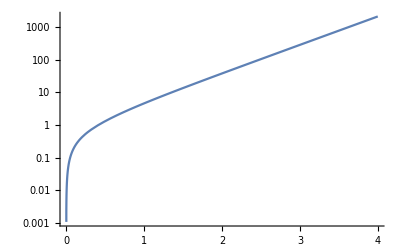

```mathematica
Integrate[√(1+(2) Sinh[x]^2),x]
LogPlot[%/.x->2(η),{η,0,4}]
(*Series[%%,{x,∞,0}]//TrigToExp*)
```

The AdS limit of this is ξ -> 0 which implies 4 k η + Log μ -> - ∞, we should be able to recover the radion profile of a^2 = e^{-2 k η}

```mathematica
2 k Tanh[4 k η+Log[μ]] r'[η]
r''[η]==Limit[%,μ->0]
"This is the ODE for standard AdS profile"
```

2 k Tanh[4 k η+Log[μ]] r'[η]

r''[η]==-2 k r'[η]

This is the ODE for standard AdS profile

```mathematica
"Try solving order by order in μ (to second order)"
r''[η]==2 k Tanh[4 k η+Log[μ]] r'[η]
(*DSolve[%,r,η]*)
Series[%//TrigToExp,{μ,0,2}]
DSolve[%//Normal,r,η]
"Now expand again in μ"
r[η]/.%%[[1]]
Assuming[{{η,k,μ}∈ Reals,μ>0},Series[%,{μ,0,2}]]
```

Try solving order by order in μ (to second order)

r''[η]==2 k Tanh[4 k η+Log[μ]] r'[η]

r''[η]==-2 (k r'[η])+4 ⅇ^(8 k η) k r'[η] μ^2+O[μ]^3

{{r→Function[{η},C[2]-(ⅇ^(-2 k η) (-ⅇ^(8 k η) μ^2)^(1/4) C[1] Gamma[-1/4,-1/2 ⅇ^(8 k η) μ^2])/(8 2^(1/4) k)]}}

Now expand again in μ

C[2]-(ⅇ^(-2 k η) (-ⅇ^(8 k η) μ^2)^(1/4) C[1] Gamma[-1/4,-1/2 ⅇ^(8 k η) μ^2])/(8 2^(1/4) k)

(-(ⅇ^(-2 k η) C[1])/(2 k)+C[2])-(((-1/2)^(1/4) C[1] Gamma[-1/4]) √μ)/(8 k)+(ⅇ^(6 k η) C[1] μ^2)/(12 k)+O[μ]^(5/2)

```mathematica
"I think we should be able to make this argument analytically somehow. 
Ie. maybe we can make this ansatz in overleaf and see what happens. 

Before we do that we would need to understand what we are trying to do. 

Because we would need ot make sure we can still retain the gauge transformation so we can find the transition function. 

Upshot, they used 5 GTs to solve the 5D and mixed equations, then performed another gauge transformation in 5D only on the metric perturbation. This gave two equations, which were then solved for arbitrary GT. Matching gave the transition function. 

What we are trying to do here is make an ansatz for the form of the perturbation, it will transform the same way under GT so this should work. We just need to make sure we can solve for it. 

*** also if the EFEs are gauge invariant, why did we need to do a GT to satisfy the non 4D equations?

*** I think there may be a work around we can find to doing the analysis for the 5D. 
"
```

#### Rμη

```mathematica
g0If[μ,σ]D[r[η]g0f[μ,ν],η]/.hyperders/.μh->ch[η]^2-sh[η]^2//Expand//contind//Simplify
g0If[μ,ν]D[r[η]f[x]g0f[μ,ν],x]/.hyperders/.μh->ch[η]^2-sh[η]^2//Expand//contind//Simplify
g0If[μ,σ]D[r[η]f[x]D[g0f[μ,ν],η],x]/.hyperders/.μh->ch[η]^2-sh[η]^2//Expand//contind//Simplify
```

(2 k r[η] sh[η] (δ[σ,ν]-2 ηt[ν,σ]))/ch[η]+(4 k ch[η] r[η] ηt[ν,σ])/sh[η]+δ[σ,ν] r'[η]

4 r[η] f'[x]

(2 k r[η] (sh[η]^2 (δ[σ,ν]-2 ηt[ν,σ])+2 ch[η]^2 ηt[ν,σ]) f'[x])/(ch[η] sh[η])

```mathematica
(*r[η]g0If[σ,ρ](sym[d[f[x],σ]D[g0f[ν,ρ],η],σ,ν]-1/2 d[f[x],ρ] D[g0f[σ,ν],η])//Expand//contind;
%/.μh->ch[η]^2-sh[η]^2//Simplify//Expand//contind
1/2 g0If[ν,α]D[g0f[μ,α],η]/.hyperders/.μh->ch[η]^2-sh[η]^2//Expand//contind//Simplify
"So this is the Γ1 non der term. And for the der term we have"*)
```

(d[f[x],ν] r[η] ch'[η])/ch[η]+(ch[η] d[f[x],ν] r[η] ch'[η])/sh[η]^2+(d[f[x],ρ] r[η] ηt[ν,ρ] ch'[η])/ch[η]-(ch[η] d[f[x],ρ] r[η] ηt[ν,ρ] ch'[η])/sh[η]^2-(d[f[x],σ] r[η] ηt[ν,σ] ch'[η])/ch[η]+(ch[η] d[f[x],σ] r[η] ηt[ν,σ] ch'[η])/sh[η]^2

(k sh[η] (δ[ν,μ]-2 ηt[μ,ν]))/ch[η]+(2 k ch[η] ηt[μ,ν])/sh[η]

```mathematica
r[η]g0If[σ,ρ](sym[d[f[x],σ]D[g0f[ν,ρ],η],σ,ν]-1/2 d[f[x],ρ] D[g0f[σ,ν],η])//Expand//contind;
%/.μh->ch[η]^2-sh[η]^2//Simplify//Expand//contind
1/2 g0If[ν,α]D[g0f[μ,α],η]/.hyperders/.μh->ch[η]^2-sh[η]^2//Expand//contind//Simplify
"So this is the Γ1 non der term. And for the der term we have"
```

So this is the Γ1 non der term. And for the der term we have

```mathematica
1/2 g0If[σ,ρ]antisym[g0If[ν,α]D[g0f[μ,α],η]r[η](sym[d[f[x],σ]g0f[ν,ρ],σ,ν]-1/2 d[f[x],ρ] g0f[σ,ν]),μ,σ]/.hyperders/.μh->ch[η]^2-sh[η]^2//Expand//contind//Simplify;(*/.μh->ch[η]^2-sh[η]^2//Expand//contind//Simplify;
%/.ηt[a_,b_]->ηtI[a,b]//Expand//contind//contind*)
(*%/.μh->ch[η]^2-sh[η]^2//Simplify//Expand//contind*)
(*1/2 g0If[ν,α]D[g0f[μ,α],η]/.hyperders/.μh->ch[η]^2-sh[η]^2//Expand//contind//Simplify*)
powinμh[%,1]//Normal//Expand//contind//contind
%/.Times[x:pre_,d[f[y_],ν_],ηt[OrderlessPatternSequence[ν_,μ_]]]->pre  δ[μ,0]d[f[y],0]/.ηt[ρ_,ρ_]->1//Simplify//contind
"So this is the Γ1 non der term. And for the der term we have, notice that now this is proportional to η^ξ, so this may have become tractable."
```

-8 ⅇ^(4 k η) k μh d[f[x],ν] r[η] ηt[μ,ν]-ⅇ^(4 k η) k μh d[f[x],σ] r[η] ηt[μ,σ]+2 ⅇ^(4 k η) k μh d[f[x],ν] r[η] ηt[ν,μ]-ⅇ^(4 k η) k μh d[f[x],ρ] r[η] ηt[ρ,μ]+2 ⅇ^(4 k η) k μh d[f[x],μ] r[η] ηt[ρ,ρ]

2 ⅇ^(4 k η) k μh r[η] (d[f[x],μ]-4 d[f[x],0] δ[μ,0])

So this is the Γ1 non der term. And for the der term we have, notice that now this is proportional to η^ξ, so this may have become tractable.

### Radion Analysis ansatz (η -> η + κ f )

#### Metric

```mathematica
"If we follow the ansatz of the radion analysis we simply take η -> η + κ f[x]r[η] and work at leading order in κ. "
shηpert=√μ Sinh[(2(η+κ f[x]))/l+1/2 Log[μ ]];
chηpert=√μ Cosh[(2(η+κ f[x]))/l+1/2 Log[μ]];
Expand@Coefficient[Series[2 shηpert^2/chηpert,{κ,0,1}],κ,1]/.√μ Cosh[(2η)/l+Log[μ]/2]->ch[η]/.√μ Sinh[(2η)/l+Log[μ]/2]->sh[η]/.Tanh[(2 η)/l+Log[μ]/2]->sh[η]/ch[η]/.l->1/k//Simplify
Expand@Coefficient[Series[-2chηpert,{κ,0,1}],κ,1]/.√μ Cosh[(2η)/l+Log[μ]/2]->ch[η]/.√μ Sinh[(2η)/l+Log[μ]/2]->sh[η]/.Tanh[(2 η)/l+Log[μ]/2]->sh[η]/ch[η]/.l->1/k
D[g0f[μ,ν],η]/.hyperders/.μh->ch[η]^2-sh[η]^2(*/.sh[η]->√(μh-ch[η]^2)*)/.{ηt[μ,ν]->DiagonalMatrix[{1,0,0,0}],ηη[μ,ν]->DiagonalMatrix[{1,-1,-1,-1}]}//Simplify(*//Expand//Simplify*)
"So we find that we take h_μν->κ f[x]∂_η (g^0)_μν, we'd just need to check that this solves the EFEs and then work backwards for the gauge transformation analysis."
```

If we follow the ansatz of the radion analysis we simply take η -> η + κ f[x]r[η] and work at leading order in κ.

4 k f[x] sh[η] (2-sh[η]^2/ch[η]^2)

-4 k f[x] sh[η]

{{8 k sh[η]-(4 k sh[η]^3)/ch[η]^2,0,0,0},{0,-4 k sh[η],0,0},{0,0,-4 k sh[η],0},{0,0,0,-4 k sh[η]}}

So we find that we take h_μν->κ f[x]∂_η (g^0)_μν, we'd just need to check that this solves the EFEs and then work backwards for the gauge transformation analysis.

#### Rηη

```mathematica
g0f[μ,ν]
%/.sh[η]->√μ(shη/(√μ)/.μ->μ E^(-4 f[x]))/.ch[η]->√μ(chη/(√μ)/.μ->μ E^(-4 f[x]/l))/.η->η + f[x]//PowerExpand//Simplify
Series[%,{f[x],0,0}]//Simplify//Simplify
```

-(2 μh ηt[μ,ν])/ch[η]+2 ch[η] ηη[μ,ν]

(Sech[(2 η)/l+Log[μ]/2] (-2 μh ηt[μ,ν]+μ (1+Cosh[(4 η)/l+Log[μ]]) ηη[μ,ν]))/(√μ)

(Sech[(2 η)/l+Log[μ]/2] (-2 μh ηt[μ,ν]+μ (1+Cosh[(4 η)/l+Log[μ]]) ηη[μ,ν]))/(√μ)

```mathematica
-1/2 D[g0If[μ,ν]D[f[x]D[g0f[μ,ν],η]/.hyperders,η],η]/.hyperders;
%//Expand//contind//Simplify;
Rηηderterms=%/.μh->ch[η]^2-sh[η]^2//FullSimplify
```

(16 k^3 f[x] (ch[η]^2-sh[η]^2)^2 (ch[η]^2+sh[η]^2))/(ch[η]^3 sh[η]^3)

```mathematica
"Consider each term in the non-derivative term of R_ηη and see if we can simplify by hand. Firts the (∂^2)_ηg term"
-1/2 h[μ,ν](D[g0If[μ,ν],{η,2}])/.hyperders//Simplify;
CoefficientList[%/.μh->ch[η]^2-sh[η]^2,ηηI[μ,ν]]//Simplify
"Now the other term"
1/2 h[μ,ν]g0f[σ,ρ]D[g0If[ρ,μ],η]D[g0If[σ,ν],η]/.hyperders//Expand//contind;
%/.ηt[μ,ν]->ηtI[μ,ν]/.ηtI[ν,μ]->ηtI[μ,ν]/.δ[μ,σ]->1/.ηηI[σ,ν]->ηηI[μ,ν]/.μh->ch[η]^2-sh[η]^2//Expand//contind//contind
CoefficientList[%//Expand,ηηI[μ,ν]]//Simplify
nondertermsRηηh=%%%%%+%/.ηtI[μ,ν]->1/.ηtI[σ,ν]->1//Simplify
```

Consider each term in the non-derivative term of R_ηη and see if we can simplify by hand. Firts the (∂^2)_ηg term

{-(k^2 h[μ,ν] (ch[η]^2-sh[η]^2) (6 ch[η]^4+ch[η]^2 sh[η]^2+2 sh[η]^4) ηtI[μ,ν])/(ch[η]^3 sh[η]^4),(k^2 h[μ,ν] (ch[η]^2-2 sh[η]^2))/ch[η]^3}

Now the other term

(2 k^2 h[μ,ν] ηtI[μ,ν])/ch[η]+(4 k^2 ch[η]^3 h[μ,ν] ηtI[μ,ν])/sh[η]^4-(6 k^2 ch[η] h[μ,ν] ηtI[μ,ν])/sh[η]^2-(k^2 h[μ,ν] ηtI[σ,ν])/ch[η]+(2 k^2 ch[η] h[μ,ν] ηtI[σ,ν])/sh[η]^2-(k^2 h[μ,ν] sh[η]^2 ηtI[σ,ν])/ch[η]^3+(k^2 h[μ,ν] sh[η]^2 ηηI[μ,ν])/ch[η]^3

{1/(ch[η]^3 sh[η]^4)k^2 h[μ,ν] (ch[η]^2-sh[η]^2) (4 ch[η]^4 ηtI[μ,ν]+sh[η]^4 ηtI[σ,ν]+2 ch[η]^2 sh[η]^2 (-ηtI[μ,ν]+ηtI[σ,ν])),(k^2 h[μ,ν] sh[η]^2)/ch[η]^3}

{(k^2 h[μ,ν] (-2 ch[η]^6+ch[η]^4 sh[η]^2+sh[η]^6))/(ch[η]^3 sh[η]^4),(k^2 h[μ,ν] (ch[η]^2-sh[η]^2))/ch[η]^3}

```mathematica
nondertermsRηηh/.h[μ,ν]->f[x]D[g0f[μ,ν],η]/.hyperders//Simplify
%.{ηtI[μ,ν],ηηI[μ,ν]}//Expand//contind//Simplify;
nondertermsRηη=%/.μh->ch[η]^2-sh[η]^2//Simplify
```

{-(4 k^3 f[x] (2 ch[η]^6-ch[η]^4 sh[η]^2-sh[η]^6) (μh ηt[μ,ν]+ch[η]^2 ηη[μ,ν]))/(ch[η]^5 sh[η]^3),(4 k^3 f[x] sh[η] (ch[η]^2-sh[η]^2) (μh ηt[μ,ν]+ch[η]^2 ηη[μ,ν]))/ch[η]^5}

-(16 k^3 f[x] (ch[η]^2-sh[η]^2)^2 (ch[η]^2+sh[η]^2))/(ch[η]^3 sh[η]^3)

```mathematica
Rηηderterms+nondertermsRηη//Simplify
"This should vanish, it is an η independent coordinate transformation in η. And so is consistent with the GN gauge conditions, note that all field equations should vanish under this GT. This should give a non-trivial check for signs etc. "
(*Solve[%==0,r''[η]]//Simplify*)
(*1/(2k f[x])Coefficient[%,r''[η]]/.sh[η]->shη/.ch[η]->chη//Simplify//TrigToExp//Simplify
1/(2k f[x])Coefficient[%%,r'[η]]/.sh[η]->shη/.ch[η]->chη//Simplify//TrigToExp//Simplify
1/(2k f[x])Coefficient[%%%,r[η]]/.sh[η]->shη/.ch[η]->chη//Simplify//TrigToExp//Simplify*)
```

0

This should vanish, it is an η independent coordinate transformation in η. And so is consistent with the GN gauge conditions, note that all field equations should vanish under this GT. This should give a non-trivial check for signs etc.

#### Rμη

```mathematica
g0If[μ,σ]D[r[η]g0f[μ,ν],η]/.hyperders/.μh->ch[η]^2-sh[η]^2//Expand//contind//Simplify
g0If[μ,ν]D[r[η]f[x]g0f[μ,ν],x]/.hyperders/.μh->ch[η]^2-sh[η]^2//Expand//contind//Simplify
g0If[μ,σ]D[r[η]f[x]D[g0f[μ,ν],η],x]/.hyperders/.μh->ch[η]^2-sh[η]^2//Expand//contind//Simplify
```

(2 k r[η] sh[η] (δ[σ,ν]-2 ηt[ν,σ]))/ch[η]+(4 k ch[η] r[η] ηt[ν,σ])/sh[η]+δ[σ,ν] r'[η]

4 r[η] f'[x]

(2 k r[η] (sh[η]^2 (δ[σ,ν]-2 ηt[ν,σ])+2 ch[η]^2 ηt[ν,σ]) f'[x])/(ch[η] sh[η])

```mathematica
(*r[η]g0If[σ,ρ](sym[d[f[x],σ]D[g0f[ν,ρ],η],σ,ν]-1/2 d[f[x],ρ] D[g0f[σ,ν],η])//Expand//contind;
%/.μh->ch[η]^2-sh[η]^2//Simplify//Expand//contind
1/2 g0If[ν,α]D[g0f[μ,α],η]/.hyperders/.μh->ch[η]^2-sh[η]^2//Expand//contind//Simplify
"So this is the Γ1 non der term. And for the der term we have"*)
```

(d[f[x],ν] r[η] ch'[η])/ch[η]+(ch[η] d[f[x],ν] r[η] ch'[η])/sh[η]^2+(d[f[x],ρ] r[η] ηt[ν,ρ] ch'[η])/ch[η]-(ch[η] d[f[x],ρ] r[η] ηt[ν,ρ] ch'[η])/sh[η]^2-(d[f[x],σ] r[η] ηt[ν,σ] ch'[η])/ch[η]+(ch[η] d[f[x],σ] r[η] ηt[ν,σ] ch'[η])/sh[η]^2

(k sh[η] (δ[ν,μ]-2 ηt[μ,ν]))/ch[η]+(2 k ch[η] ηt[μ,ν])/sh[η]

```mathematica
g0If[σ,ρ](sym[d[f[x],σ]D[g0f[ν,ρ],η],σ,ν]-1/2 d[f[x],ρ] D[g0f[σ,ν],η])//Expand//contind;
%/.μh->ch[η]^2-sh[η]^2//Simplify//Expand//contind
1/2 g0If[ν,α]D[g0f[μ,α],η]/.hyperders/.μh->ch[η]^2-sh[η]^2//Expand//contind//Simplify
"So this is the Γ1 non der term. And for the der term we have"
```

(d[f[x],ν] ch'[η])/ch[η]+(ch[η] d[f[x],ν] ch'[η])/sh[η]^2+(d[f[x],ρ] ηt[ν,ρ] ch'[η])/ch[η]-(ch[η] d[f[x],ρ] ηt[ν,ρ] ch'[η])/sh[η]^2-(d[f[x],σ] ηt[ν,σ] ch'[η])/ch[η]+(ch[η] d[f[x],σ] ηt[ν,σ] ch'[η])/sh[η]^2

(k sh[η] (δ[ν,μ]-2 ηt[μ,ν]))/ch[η]+(2 k ch[η] ηt[μ,ν])/sh[η]

So this is the Γ1 non der term. And for the der term we have

```mathematica
1/2 g0If[σ,ρ]antisym[g0If[ν,α]D[g0f[μ,α],η]r[η](sym[d[f[x],σ]g0f[ν,ρ],σ,ν]-1/2 d[f[x],ρ] g0f[σ,ν]),μ,σ]/.hyperders/.μh->ch[η]^2-sh[η]^2//Expand//contind//Simplify;(*/.μh->ch[η]^2-sh[η]^2//Expand//contind//Simplify;
%/.ηt[a_,b_]->ηtI[a,b]//Expand//contind//contind*)
(*%/.μh->ch[η]^2-sh[η]^2//Simplify//Expand//contind*)
(*1/2 g0If[ν,α]D[g0f[μ,α],η]/.hyperders/.μh->ch[η]^2-sh[η]^2//Expand//contind//Simplify*)
powinμh[%,1]//Normal//Expand//contind//contind
%/.Times[x:pre_,d[f[y_],ν_],ηt[OrderlessPatternSequence[ν_,μ_]]]->pre  δ[μ,0]d[f[y],0]/.ηt[ρ_,ρ_]->1//Simplify//contind
"So this is the Γ1 non der term. And for the der term we have, notice that now this is proportional to η^ξ, so this may have become tractable."
```

2 ⅇ^(4 k η) k μh d[f[x],μ] r[η] δ[α,ρ] ηt[α,ρ]-8 ⅇ^(4 k η) k μh d[f[x],ν] r[η] ηt[μ,ν]-ⅇ^(4 k η) k μh d[f[x],σ] r[η] ηt[μ,σ]+2 ⅇ^(4 k η) k μh d[f[x],ν] r[η] ηt[ν,μ]-ⅇ^(4 k η) k μh d[f[x],μ] r[η] δ[ν,σ] ηt[ν,σ]+ⅇ^(4 k η) k μh d[f[x],μ] r[η] δ[σ,ν] ηt[ν,σ]-ⅇ^(4 k η) k μh d[f[x],ρ] r[η] ηt[ρ,μ]

-ⅇ^(4 k η) k μh r[η] (8 d[f[x],0] δ[μ,0]+d[f[x],μ] (-2 δ[α,ρ] ηt[α,ρ]+(δ[ν,σ]-δ[σ,ν]) ηt[ν,σ]))

So this is the Γ1 non der term. And for the der term we have, notice that now this is proportional to η^ξ, so this may have become tractable.

#### ηη EFE simplify by hand - corrected sign

```mathematica
"Consider each term in the non-derivative term of R_ηη and see if we can simplify by hand. Firts the (∂^2)_ηg term"
-1/2 h[μ,ν][η](D[g0If[μ,ν],{η,2}])/.hyperders//Simplify;
CoefficientList[%/.μh->ch[η]^2-sh[η]^2,ηηI[μ,ν]]//Simplify
"Now the other term"
1/2 h[μ,ν][η]g0f[σ,ρ]D[g0If[ρ,μ],η]D[g0If[σ,ν],η]/.hyperders//Expand//contind;
%/.ηt[μ,ν]->ηtI[μ,ν]/.ηtI[ν,μ]->ηtI[μ,ν]/.μh->ch[η]^2-sh[η]^2//Simplify//Expand//contind
CoefficientList[%,ηηI[μ,ν]]//Simplify
nondertermsRηη=%%%%%+%/.ηtI[μ,ν]->1//Simplify
(*%/.sh[η]->√(ch[η]^2-μh)//Expand*)
(*CoefficientList[g0If[μ,ν],ηηI[μ,ν]]/.ηtI[μ,ν]->1/.μh->ch[η]^2-sh[η]^2(*//Simplify*)
% (%%[[2]])/(%[[2]])//Simplify*)
```

Consider each term in the non-derivative term of R_ηη and see if we can simplify by hand. Firts the (∂^2)_ηg term

{-1/(ch[η]^3 sh[η]^4)k^2 (ch[η]^2-sh[η]^2) (6 ch[η]^4+ch[η]^2 sh[η]^2+2 sh[η]^4) ηtI[μ,ν] h[μ,ν][η],(k^2 (ch[η]^2-2 sh[η]^2) h[μ,ν][η])/ch[η]^3}

Now the other term

(k^2 ηtI[μ,ν] h[μ,ν][η])/ch[η]+(4 k^2 ch[η]^3 ηtI[μ,ν] h[μ,ν][η])/sh[η]^4-(4 k^2 ch[η] ηtI[μ,ν] h[μ,ν][η])/sh[η]^2-(k^2 sh[η]^2 ηtI[μ,ν] h[μ,ν][η])/ch[η]^3+(k^2 sh[η]^2 ηηI[μ,ν] h[μ,ν][η])/ch[η]^3

{(k^2 (4 ch[η]^6-4 ch[η]^4 sh[η]^2+ch[η]^2 sh[η]^4-sh[η]^6) ηtI[μ,ν] h[μ,ν][η])/(ch[η]^3 sh[η]^4),(k^2 sh[η]^2 h[μ,ν][η])/ch[η]^3}

{(k^2 (-2 ch[η]^6+ch[η]^4 sh[η]^2+sh[η]^6) h[μ,ν][η])/(ch[η]^3 sh[η]^4),(k^2 (ch[η]^2-sh[η]^2) h[μ,ν][η])/ch[η]^3}

```mathematica
-1/2 D[g0If[μ,ν]D[h[μ,ν][η],η],η]/.hyperders(*/.μh->ch[η]^2-sh[η]^2*)//Simplify;
dertermsRηη=CoefficientList[%,ηηI[μ,ν]]/.ηtI[μ,ν]->1/.μh->ch[η]^2-sh[η]^2//Simplify
```

{1/(4 ch[η]^2 sh[η]^3)(ch[η]^2-sh[η]^2) (4 k ch[η]^2 h[μ,ν]'[η]+2 k sh[η]^2 h[μ,ν]'[η]-ch[η] sh[η] h[μ,ν]''[η]),(2 k sh[η] h[μ,ν]'[η]-ch[η] h[μ,ν]''[η])/(4 ch[η]^2)}

```mathematica
"So the ODEs are"
dertermsRηη+nondertermsRηη//Simplify;
%
Solve[%[[1]]==0,h[μ,ν]''[η]][[1]]//Expand
Solve[%%[[2]]==0,h[μ,ν]''[η]][[1]]//Expand
```

So the ODEs are

{1/(4 ch[η]^3 sh[η]^4)(4 k^2 (-2 ch[η]^6+ch[η]^4 sh[η]^2+sh[η]^6) h[μ,ν][η]+ch[η] sh[η] (ch[η]^2-sh[η]^2) (4 k ch[η]^2 h[μ,ν]'[η]+2 k sh[η]^2 h[μ,ν]'[η]-ch[η] sh[η] h[μ,ν]''[η])),1/(4 ch[η]^3)(4 k^2 (ch[η]^2-sh[η]^2) h[μ,ν][η]+ch[η] (2 k sh[η] h[μ,ν]'[η]-ch[η] h[μ,ν]''[η]))}

{h[μ,ν]''[η]→-4 k^2 h[μ,ν][η]-(8 k^2 ch[η]^2 h[μ,ν][η])/sh[η]^2-(4 k^2 sh[η]^2 h[μ,ν][η])/ch[η]^2+(4 k ch[η] h[μ,ν]'[η])/sh[η]+(2 k sh[η] h[μ,ν]'[η])/ch[η]}

{h[μ,ν]''[η]→4 k^2 h[μ,ν][η]-(4 k^2 sh[η]^2 h[μ,ν][η])/ch[η]^2+(2 k sh[η] h[μ,ν]'[η])/ch[η]}

#### μη

```mathematica
1/2 g0If[σ,ρ]antisym[g0If[ν,α]D[g0f[μ,α],η](sym[d[f[x],σ]g0f[ν,ρ],σ,ν]-1/2 d[f[x],ρ] g0f[σ,ν]),μ,σ]/.hyperders/.μh->ch[η]^2-sh[η]^2//Expand//contind//FullSimplify(*/.μh->ch[η]^2-sh[η]^2//Expand//contind//Simplify;
%/.ηt[a_,b_]->ηtI[a,b]//Expand//contind//contind*)
(*%/.μh->ch[η]^2-sh[η]^2//Simplify//Expand//contind*)
(*1/2 g0If[ν,α]D[g0f[μ,α],η]/.hyperders/.μh->ch[η]^2-sh[η]^2//Expand//contind//Simplify*)
powinμh[%,1]//Normal//Expand//contind
%/.Times[x:pre_,d[f[y_],ν_],ηt[OrderlessPatternSequence[ν_,μ_]]]->pre  δ[μ,0]d[f[y],0]/.ηt[ρ_,ρ_]->1//Simplify//contind
"So this is the Γ1 non der term. And for the der term we have, notice that now this is proportional to η^ξ, so this may have become tractable."
```

1/(4 ch[η]^3 sh[η]^3)k (ch[η]^2-sh[η]^2) (ch[η]^4 (d[f[x],σ] (ηt[μ,σ]-ηt[α,σ] ηη[μ,α])+d[f[x],ρ] (-2 ηt[μ,ρ]+ηt[α,ρ] ηη[μ,α]+ηt[ν,ρ] ηη[μ,ν]))+sh[η]^4 (d[f[x],σ] ηt[μ,σ]+d[f[x],ρ] (-2 ηt[μ,ρ]+ηt[ρ,μ])+d[f[x],ν] (-ηt[μ,ν]+ηt[ν,ρ] ηη[μ,ρ]))-ch[η]^2 sh[η]^2 (2 d[f[x],μ]+d[f[x],σ] (ηt[μ,σ]-ηt[α,σ] ηη[μ,α])+d[f[x],ρ] (-4 ηt[μ,ρ]+ηt[α,ρ] ηη[μ,α]+ηt[ν,ρ] ηη[μ,ν])+d[f[x],ν] (-9 ηt[μ,ν]+2 ηt[ν,μ]+ηt[ν,ρ] ηη[μ,ρ])))

2 ⅇ^(4 k η) k μh d[f[x],μ]-8 ⅇ^(4 k η) k μh d[f[x],ν] ηt[μ,ν]-ⅇ^(4 k η) k μh d[f[x],σ] ηt[μ,σ]+2 ⅇ^(4 k η) k μh d[f[x],ν] ηt[ν,μ]-ⅇ^(4 k η) k μh d[f[x],ρ] ηt[ρ,μ]

2 ⅇ^(4 k η) k μh (d[f[x],μ]-4 d[f[x],0] δ[μ,0])

So this is the Γ1 non der term. And for the der term we have, notice that now this is proportional to η^ξ, so this may have become tractable.

```mathematica
d[f[x],μ] (-δ[ρ,α] ηt[α,ρ]+δ[σ,ν] ηt[ν,σ])//Expand//contind
```

-d[f[x],μ] δ[ρ,α] ηt[α,ρ]+d[f[x],μ] δ[σ,ν] ηt[ν,σ]

```mathematica
1/2 D[g0If[ν,σ](d[f[x],ν]D[g0f[μ,σ],η]-d[f[x],μ]D[g0f[ν,σ],η]),η]/.hyperders//Expand//contind//Simplify
```

1/(ch[η]^4 sh[η]^2)2 k^2 (3 μh sh[η]^2 (μh+sh[η]^2) (d[f[x],μ]-d[f[x],ν] ηt[μ,ν])+ch[η]^4 (d[f[x],μ] (μh-3 sh[η]^2)-μh d[f[x],ν] ηt[μ,ν])+ch[η]^2 (d[f[x],μ] (μh^2+3 sh[η]^4)-μh^2 d[f[x],ν] ηt[μ,ν]))

### Radion Analysis ansatz (arbitrary h)

#### Rηη

```mathematica
-1/2 D[g0If[μ,ν]D[h[μ,ν][η],η],η]/.hyperders;
%//Expand//contind//Simplify;
Rηηderterms=%/.μh->ch[η]^2-sh[η]^2//FullSimplify
```

1/(4 ch[η]^2 sh[η]^3)(2 k ((ch[η]-sh[η]) (ch[η]+sh[η]) (2 ch[η]^2+sh[η]^2) ηtI[μ,ν]+sh[η]^4 ηηI[μ,ν]) h[μ,ν]'[η]-ch[η] sh[η] (ch[η]^2 ηtI[μ,ν]+sh[η]^2 (-ηtI[μ,ν]+ηηI[μ,ν])) h[μ,ν]''[η])

```mathematica
-1/2 h[μ,ν][η](D[g0If[μ,ν],{η,2}])/.hyperders//Simplify;
(*CoefficientList[%/.μh->ch[η]^2-sh[η]^2,ηηI[μ,ν]]//Simplify*)
"Now the other term"
1/2 h[μ,ν][η]g0f[σ,ρ]D[g0If[ρ,μ],η]D[g0If[σ,ν],η]/.hyperders//Expand//contind//Simplify;
(*%/.ηt[μ,ν]->ηtI[μ,ν]/.ηtI[ν,μ]->ηtI[μ,ν]/.μh->ch[η]^2-sh[η]^2//Simplify//Expand//contind;*)
(*CoefficientList[%,ηηI[μ,ν]]//Simplify//contind*)
(*nondertermsRηη=%%%%%+%/.ηtI[μ,ν]->1//Simplify*)
nondertermsRηη=%%%+%
```

Now the other term

-1/(ch[η]^3 sh[η]^4)k^2 (6 μh ch[η]^4 ηtI[μ,ν]+2 sh[η]^4 (μh ηtI[μ,ν]+sh[η]^2 ηηI[μ,ν])+ch[η]^2 (μh sh[η]^2 ηtI[μ,ν]-sh[η]^4 ηηI[μ,ν])) h[μ,ν][η]+1/(ch[η]^5 sh[η]^6)k^2 (4 μh^2 ch[η]^6 ηt[μ,ν]-μh sh[η]^4 (μh+sh[η]^2)^2 ηt[μ,ν]+2 μh ch[η]^4 (-2 μh (μh-sh[η]^2) ηt[μ,ν]+sh[η]^4 (ηtI[μ,ν]+ηtI[ν,μ]))+ch[η]^2 (-4 μh^3 sh[η]^2 ηt[μ,ν]-3 μh^2 sh[η]^4 ηt[μ,ν]+μh sh[η]^6 (ηtI[μ,ν]+ηtI[ν,μ])+sh[η]^8 ηηI[μ,ν])) h[μ,ν][η]

```mathematica
Rηηderterms+nondertermsRηη//Simplify;
(*Solve[%==0,h[μ,ν][η]]//Simplify*)
%/.ηt[μ,ν]->ηtI[μ,ν]/.ηtI[ν,μ]->ηtI[μ,ν]/.μh->ch[η]^2-sh[η]^2//Simplify//Expand//contind;
CoefficientList[%,ηηI[μ,ν]]//Simplify//contind;
totalRηηterms=%/.ηtI[μ,ν]->1//Simplify
```

{-1/(4 ch[η]^3 sh[η]^4)(ch[η]^2-sh[η]^2) (8 k^2 ch[η]^4 h[μ,ν][η]+4 k^2 sh[η]^4 h[μ,ν][η]-4 k ch[η]^3 sh[η] h[μ,ν]'[η]-2 k ch[η] sh[η]^3 h[μ,ν]'[η]+ch[η]^2 sh[η]^2 (4 k^2 h[μ,ν][η]+h[μ,ν]''[η])),(-4 k^2 sh[η]^2 h[μ,ν][η]+2 k ch[η] sh[η] h[μ,ν]'[η]+ch[η]^2 (4 k^2 h[μ,ν][η]-h[μ,ν]''[η]))/(4 ch[η]^3)}

#### Rμη

```mathematica
g0If[μ,σ]D[r[η]g0f[μ,ν],η]/.hyperders/.μh->ch[η]^2-sh[η]^2//Expand//contind//Simplify
g0If[μ,ν]D[r[η]f[x]g0f[μ,ν],x]/.hyperders/.μh->ch[η]^2-sh[η]^2//Expand//contind//Simplify
g0If[μ,σ]D[r[η]f[x]D[g0f[μ,ν],η],x]/.hyperders/.μh->ch[η]^2-sh[η]^2//Expand//contind//Simplify
```

(2 k r[η] sh[η] (δ[σ,ν]-2 ηt[ν,σ]))/ch[η]+(4 k ch[η] r[η] ηt[ν,σ])/sh[η]+δ[σ,ν] r'[η]

4 r[η] f'[x]

(2 k r[η] (sh[η]^2 (δ[σ,ν]-2 ηt[ν,σ])+2 ch[η]^2 ηt[ν,σ]) f'[x])/(ch[η] sh[η])

```mathematica
(*r[η]g0If[σ,ρ](sym[d[f[x],σ]D[g0f[ν,ρ],η],σ,ν]-1/2 d[f[x],ρ] D[g0f[σ,ν],η])//Expand//contind;
%/.μh->ch[η]^2-sh[η]^2//Simplify//Expand//contind
1/2 g0If[ν,α]D[g0f[μ,α],η]/.hyperders/.μh->ch[η]^2-sh[η]^2//Expand//contind//Simplify
"So this is the Γ1 non der term. And for the der term we have"*)
```

(d[f[x],ν] r[η] ch'[η])/ch[η]+(ch[η] d[f[x],ν] r[η] ch'[η])/sh[η]^2+(d[f[x],ρ] r[η] ηt[ν,ρ] ch'[η])/ch[η]-(ch[η] d[f[x],ρ] r[η] ηt[ν,ρ] ch'[η])/sh[η]^2-(d[f[x],σ] r[η] ηt[ν,σ] ch'[η])/ch[η]+(ch[η] d[f[x],σ] r[η] ηt[ν,σ] ch'[η])/sh[η]^2

(k sh[η] (δ[ν,μ]-2 ηt[μ,ν]))/ch[η]+(2 k ch[η] ηt[μ,ν])/sh[η]

```mathematica
r[η]g0If[σ,ρ](sym[d[f[x],σ]D[g0f[ν,ρ],η],σ,ν]-1/2 d[f[x],ρ] D[g0f[σ,ν],η])//Expand//contind;
%/.μh->ch[η]^2-sh[η]^2//Simplify//Expand//contind
1/2 g0If[ν,α]D[g0f[μ,α],η]/.hyperders/.μh->ch[η]^2-sh[η]^2//Expand//contind//Simplify
"So this is the Γ1 non der term. And for the der term we have"
```

So this is the Γ1 non der term. And for the der term we have

```mathematica
1/2 g0If[σ,ρ]antisym[g0If[ν,α]D[g0f[μ,α],η]r[η](sym[d[f[x],σ]g0f[ν,ρ],σ,ν]-1/2 d[f[x],ρ] g0f[σ,ν]),μ,σ]/.hyperders/.μh->ch[η]^2-sh[η]^2//Expand//contind//Simplify;(*/.μh->ch[η]^2-sh[η]^2//Expand//contind//Simplify;
%/.ηt[a_,b_]->ηtI[a,b]//Expand//contind//contind*)
(*%/.μh->ch[η]^2-sh[η]^2//Simplify//Expand//contind*)
(*1/2 g0If[ν,α]D[g0f[μ,α],η]/.hyperders/.μh->ch[η]^2-sh[η]^2//Expand//contind//Simplify*)
powinμh[%,1]//Normal//Expand//contind//contind
%/.Times[x:pre_,d[f[y_],ν_],ηt[OrderlessPatternSequence[ν_,μ_]]]->pre  δ[μ,0]d[f[y],0]/.ηt[ρ_,ρ_]->1//Simplify//contind
"So this is the Γ1 non der term. And for the der term we have, notice that now this is proportional to η^ξ, so this may have become tractable."
```

-8 ⅇ^(4 k η) k μh d[f[x],ν] r[η] ηt[μ,ν]-ⅇ^(4 k η) k μh d[f[x],σ] r[η] ηt[μ,σ]+2 ⅇ^(4 k η) k μh d[f[x],ν] r[η] ηt[ν,μ]-ⅇ^(4 k η) k μh d[f[x],ρ] r[η] ηt[ρ,μ]+2 ⅇ^(4 k η) k μh d[f[x],μ] r[η] ηt[ρ,ρ]

2 ⅇ^(4 k η) k μh r[η] (d[f[x],μ]-4 d[f[x],0] δ[μ,0])

So this is the Γ1 non der term. And for the der term we have, notice that now this is proportional to η^ξ, so this may have become tractable.

### Reproduce CGR paper - AdS

```mathematica
afunc=Function[{η},E^(-k η)];
```

#### Reproduce CGR paper EOM

```mathematica
Rη
```

```mathematica
Clear[h]
Xη= {t,x,η};
d=3;
δgη = μ (*{{h[Sequence@@Xη],0},{0,-1}};*)Table[Table[h[i,j][Sequence@@Xη](1-KroneckerDelta[i,d])(1-KroneckerDelta[j,d]),{i,d}],{j,d}]
g0η = {{a[η]^2,0,0},{0,-a[η]^2,0},{0,0,-1}} 
ηη = {{1,0,0},{0,-1,0},{0,0,-1}} ;
gη = g0η  +δgη
RTη=Ricci[gη,Xη];

(*Rη =Simplify[Tr[RTη.Inverse[gη]]];*)
Rη =Tr[RTη.Inverse[gη]];


(*GTη=Simplify[(RTη-1/2 gη Rη).Inverse[gη]];*)(*1 upper one lower index*)
GTη=(RTη-1/2 gη Rη).Inverse[gη];
```

{{μ h[1,1][t,x,η],μ h[2,1][t,x,η],0},{μ h[1,2][t,x,η],μ h[2,2][t,x,η],0},{0,0,0}}

{{a[η]^2,0,0},{0,-a[η]^2,0},{0,0,-1}}

{{a[η]^2+μ h[1,1][t,x,η],μ h[2,1][t,x,η],0},{μ h[1,2][t,x,η],-a[η]^2+μ h[2,2][t,x,η],0},{0,0,-1}}

```mathematica
trh=1/μ Tr[δgη.{{a[η]^2,0,0},{0,-a[η]^2,0},{0,0,-1}}]//Simplify;
1/(2 a[η]^2)D[D[trh,η] a[η]^-2,η]//Simplify
Coefficient[Series[RTη[[3,3]],{μ,0,1}],μ,1]//Simplify
%%-%//Simplify
```

1/(2 a[η]^4)(-2 h[1,1][t,x,η] (a'[η]^2-a[η] a''[η])+2 h[2,2][t,x,η] (a'[η]^2-a[η] a''[η])+a[η] (2 a'[η] (h[1,1]^(0,0,1)[t,x,η]-h[2,2]^(0,0,1)[t,x,η])+a[η] (h[1,1]^(0,0,2)[t,x,η]-h[2,2]^(0,0,2)[t,x,η])))

1/(2 a[η]^4)(-2 h[1,1][t,x,η] (a'[η]^2-a[η] a''[η])+2 h[2,2][t,x,η] (a'[η]^2-a[η] a''[η])+a[η] (2 a'[η] (h[1,1]^(0,0,1)[t,x,η]-h[2,2]^(0,0,1)[t,x,η])+a[η] (-h[1,1]^(0,0,2)[t,x,η]+h[2,2]^(0,0,2)[t,x,η])))

(h[1,1]^(0,0,2)[t,x,η]-h[2,2]^(0,0,2)[t,x,η])/a[η]^2

```mathematica
With[{j=2},D[1/(2 a[η]^2)(1/μ Sum[D[(Inverse[ηη].δgη)[[i,j]],Xη[[i]]],{i,d}]-D[trh/a[η]^2,Xη[[j]]]),η]//Simplify]
(*With[{j=2},D[1/(2 a[η]^2)(1/μ Sum[D[(Inverse[g0η].δgη)[[i,j]],Xη[[i]]],{i,d}]-D[trh,Xη[[j]]]),η]//Simplify]*)
Coefficient[Series[RTη[[3,2]],{μ,0,1}],μ,1]//Simplify
%%-%//Simplify/.Function[{t,x,η},h[1,2][Sequence@@Xη]]->Function[{t,x,η},h[2,1][Sequence@@Xη]]
```

(2 a'[η] (h[1,1]^(0,1,0)[t,x,η]-h[2,1]^(1,0,0)[t,x,η])+a[η] (-h[1,1]^(0,1,1)[t,x,η]+h[2,1]^(1,0,1)[t,x,η]))/(2 a[η]^3)

(2 a'[η] (h[1,1]^(0,1,0)[t,x,η]-h[1,2]^(1,0,0)[t,x,η])+a[η] (-h[1,1]^(0,1,1)[t,x,η]+h[1,2]^(1,0,1)[t,x,η]))/(2 a[η]^3)

(2 a'[η] (h[1,2]^(1,0,0)[t,x,η]-h[2,1]^(1,0,0)[t,x,η])+a[η] (-h[1,2]^(1,0,1)[t,x,η]+h[2,1]^(1,0,1)[t,x,η]))/(2 a[η]^3)

```mathematica
With[{j=2},D[1/(2 a[η]^2)(-D[trh,Xη[[j]]]),η]//Simplify]
```

1/2 (-h[1,1]^(0,1,1)[t,x,η]+h[2,2]^(0,1,1)[t,x,η])

```mathematica
trh
```

a[η]^2 (h[1,1][t,x,η]-h[2,2][t,x,η])

#### Reproduce CGR paper EOM - corrected

```mathematica
Rη
```

```mathematica
Clear[h]
Xη= {t,x,η};
d=3;
δgη = μ (*{{h[Sequence@@Xη],0},{0,-1}};*)Table[Table[h[i,j][Sequence@@Xη](1-KroneckerDelta[i,d])(1-KroneckerDelta[j,d]),{i,d}],{j,d}]
g0η = {{a[η]^2,0,0},{0,-a[η]^2,0},{0,0,-1}} ;
ηη = {{1,0,0},{0,-1,0},{0,0,-1}} ;
gη = g0η  +δgη
RTη=Ricci[gη,Xη];

(*Rη =Simplify[Tr[RTη.Inverse[gη]]];*)
Rη =Tr[RTη.Inverse[gη]];


(*GTη=Simplify[(RTη-1/2 gη Rη).Inverse[gη]];*)(*1 upper one lower index*)
GTη=(RTη-1/2 gη Rη).Inverse[gη];
```

{{μ h[1,1][t,x,η],μ h[2,1][t,x,η],0},{μ h[1,2][t,x,η],μ h[2,2][t,x,η],0},{0,0,0}}

{{a[η]^2+μ h[1,1][t,x,η],μ h[2,1][t,x,η],0},{μ h[1,2][t,x,η],-a[η]^2+μ h[2,2][t,x,η],0},{0,0,-1}}

```mathematica
trhfunc=h[#1,#2,#3]+h[2,2][#1,#2,#3]&
trhrepl = {h[1,1]->trhfunc}
trh/.trhrepl
```

h[#1,#2,#3]+h[2,2][#1,#2,#3]&

{h[1,1]→(h[#1,#2,#3]+h[2,2][#1,#2,#3]&)}

h[t,x,η]

```mathematica
symhfunc=h[1,2][#1,#2,#3]&
symhrepl = {h[2,1]->symhfunc}
```

h[1,2][#1,#2,#3]&

{h[2,1]→(h[1,2][#1,#2,#3]&)}

```mathematica
trh=1/μ Tr[δgη.ηη]//Simplify
```

h[1,1][t,x,η]-h[2,2][t,x,η]

```mathematica
"The ηη term"
-D[D[trh,η]/(2 a[η]^2),η]/.trhrepl//Simplify
Coefficient[Series[RTη[[3,3]],{μ,0,1}],μ,1]/.trhrepl//Simplify
%%-%//Simplify
%/.a->afunc
```

The ηη term

(2 a'[η] h^(0,0,1)[t,x,η]-a[η] h^(0,0,2)[t,x,η])/(2 a[η]^3)

(-2 h[t,x,η] (a'[η]^2-a[η] a''[η])+a[η] (2 a'[η] h^(0,0,1)[t,x,η]-a[η] h^(0,0,2)[t,x,η]))/(2 a[η]^4)

(h[t,x,η] (a'[η]^2-a[η] a''[η]))/a[η]^4

0

```mathematica
"The μη term"
With[{j=2},D[1/(2 a[η]^2)(1/μ Sum[D[(Inverse[ηη].δgη)[[i,j]],Xη[[i]]],{i,d}]-D[trh,Xη[[j]]]),η]//Simplify]
Coefficient[Series[RTη[[3,2]],{μ,0,1}],μ,1]//Simplify
%%-%/.symhrepl//Simplify
```

The μη term

(2 a'[η] (h[1,1]^(0,1,0)[t,x,η]-h[2,1]^(1,0,0)[t,x,η])+a[η] (-h[1,1]^(0,1,1)[t,x,η]+h[2,1]^(1,0,1)[t,x,η]))/(2 a[η]^3)

(2 a'[η] (h[1,1]^(0,1,0)[t,x,η]-h[1,2]^(1,0,0)[t,x,η])+a[η] (-h[1,1]^(0,1,1)[t,x,η]+h[1,2]^(1,0,1)[t,x,η]))/(2 a[η]^3)

0

#### TT condition

```mathematica
"The TT decomposition claims to be"
hbarμν= Table[Table[h[i,j][Sequence@@Xη](1-KroneckerDelta[i,5])(1-KroneckerDelta[j,5]),{i,4}],{j,4}]
fcμν= Table[Table[D[f[Sequence@@Xη],{Xη[[i]]},{Xη[[j]]}](1-KroneckerDelta[i,5])(1-KroneckerDelta[j,5]),{i,4}],{j,4}]
ημν= Table[Table[If[i==1,1,-1]If[i==j,1,0],{i,4}],{j,4}]
```

The TT decomposition claims to be

{{h[1,1][t,x,y,z,η],h[2,1][t,x,y,z,η],h[3,1][t,x,y,z,η],h[4,1][t,x,y,z,η]},{h[1,2][t,x,y,z,η],h[2,2][t,x,y,z,η],h[3,2][t,x,y,z,η],h[4,2][t,x,y,z,η]},{h[1,3][t,x,y,z,η],h[2,3][t,x,y,z,η],h[3,3][t,x,y,z,η],h[4,3][t,x,y,z,η]},{h[1,4][t,x,y,z,η],h[2,4][t,x,y,z,η],h[3,4][t,x,y,z,η],h[4,4][t,x,y,z,η]}}

{{f^(2,0,0,0,0)[t,x,y,z,η],f^(1,1,0,0,0)[t,x,y,z,η],f^(1,0,1,0,0)[t,x,y,z,η],f^(1,0,0,1,0)[t,x,y,z,η]},{f^(1,1,0,0,0)[t,x,y,z,η],f^(0,2,0,0,0)[t,x,y,z,η],f^(0,1,1,0,0)[t,x,y,z,η],f^(0,1,0,1,0)[t,x,y,z,η]},{f^(1,0,1,0,0)[t,x,y,z,η],f^(0,1,1,0,0)[t,x,y,z,η],f^(0,0,2,0,0)[t,x,y,z,η],f^(0,0,1,1,0)[t,x,y,z,η]},{f^(1,0,0,1,0)[t,x,y,z,η],f^(0,1,0,1,0)[t,x,y,z,η],f^(0,0,1,1,0)[t,x,y,z,η],f^(0,0,0,2,0)[t,x,y,z,η]}}

{{1,0,0,0},{0,-1,0,0},{0,0,-1,0},{0,0,0,-1}}

```mathematica
hTTdecomp=hbarμν + 1/k fcμν - 2 k a^2 ημν f[Sequence@@Xη]//Simplify
```

{{-2 a^2 k f[t,x,y,z,η]+h[1,1][t,x,y,z,η]+(f^(2,0,0,0,0)[t,x,y,z,η])/k,h[2,1][t,x,y,z,η]+(f^(1,1,0,0,0)[t,x,y,z,η])/k,h[3,1][t,x,y,z,η]+(f^(1,0,1,0,0)[t,x,y,z,η])/k,h[4,1][t,x,y,z,η]+(f^(1,0,0,1,0)[t,x,y,z,η])/k},{h[1,2][t,x,y,z,η]+(f^(1,1,0,0,0)[t,x,y,z,η])/k,2 a^2 k f[t,x,y,z,η]+h[2,2][t,x,y,z,η]+(f^(0,2,0,0,0)[t,x,y,z,η])/k,h[3,2][t,x,y,z,η]+(f^(0,1,1,0,0)[t,x,y,z,η])/k,h[4,2][t,x,y,z,η]+(f^(0,1,0,1,0)[t,x,y,z,η])/k},{h[1,3][t,x,y,z,η]+(f^(1,0,1,0,0)[t,x,y,z,η])/k,h[2,3][t,x,y,z,η]+(f^(0,1,1,0,0)[t,x,y,z,η])/k,2 a^2 k f[t,x,y,z,η]+h[3,3][t,x,y,z,η]+(f^(0,0,2,0,0)[t,x,y,z,η])/k,h[4,3][t,x,y,z,η]+(f^(0,0,1,1,0)[t,x,y,z,η])/k},{h[1,4][t,x,y,z,η]+(f^(1,0,0,1,0)[t,x,y,z,η])/k,h[2,4][t,x,y,z,η]+(f^(0,1,0,1,0)[t,x,y,z,η])/k,h[3,4][t,x,y,z,η]+(f^(0,0,1,1,0)[t,x,y,z,η])/k,2 a^2 k f[t,x,y,z,η]+h[4,4][t,x,y,z,η]+(f^(0,0,0,2,0)[t,x,y,z,η])/k}}

```mathematica
Tr[hTTdecomp.ημν]//Simplify
(*%/.f[Sequence@@Xη]->1/(10 a^2 k)Sum[ημν[[i,i]]h[i,i][Sequence@@Xη],{i,4}]//Simplify*)
%-Sum[ημν[[i,i]]h[i,i][Sequence@@Xη],{i,4}]//Simplify
"Hence provided □_(4)f=0, then f is proportional to the trace of h (Tr(h)=-8a^2k f)"
```

-1/k(8 a^2 k^2 f[t,x,y,z,η]-k h[1,1][t,x,y,z,η]+k h[2,2][t,x,y,z,η]+k h[3,3][t,x,y,z,η]+k h[4,4][t,x,y,z,η]+f^(0,0,0,2,0)[t,x,y,z,η]+f^(0,0,2,0,0)[t,x,y,z,η]+f^(0,2,0,0,0)[t,x,y,z,η]-f^(2,0,0,0,0)[t,x,y,z,η])

-1/k(8 a^2 k^2 f[t,x,y,z,η]+f^(0,0,0,2,0)[t,x,y,z,η]+f^(0,0,2,0,0)[t,x,y,z,η]+f^(0,2,0,0,0)[t,x,y,z,η]-f^(2,0,0,0,0)[t,x,y,z,η])

Hence provided □_(4)f=0, then f is proportional to the trace of h (Tr(h)=-8a^2k f)

```mathematica
Table[Sum[D[hTTdecomp[[i,j]]ημν[[j,j]],{Xη[[j]]}],{j,4}],{i,4}]//Simplify;
(*%[[1]];*)
%-Table[Sum[D[hbarμν[[i,j]]ημν[[j,j]],{Xη[[j]]}],{j,4}],{i,4}]//Simplify
"Most of the terms are derivatives of □f (which is 0)."
```

{-1/k(2 a^2 k^2 f^(1,0,0,0,0)[t,x,y,z,η]+f^(1,0,0,2,0)[t,x,y,z,η]+f^(1,0,2,0,0)[t,x,y,z,η]+f^(1,2,0,0,0)[t,x,y,z,η]-f^(3,0,0,0,0)[t,x,y,z,η]),-1/k(2 a^2 k^2 f^(0,1,0,0,0)[t,x,y,z,η]+f^(0,1,0,2,0)[t,x,y,z,η]+f^(0,1,2,0,0)[t,x,y,z,η]+f^(0,3,0,0,0)[t,x,y,z,η]-f^(2,1,0,0,0)[t,x,y,z,η]),-1/k(2 a^2 k^2 f^(0,0,1,0,0)[t,x,y,z,η]+f^(0,0,1,2,0)[t,x,y,z,η]+f^(0,0,3,0,0)[t,x,y,z,η]+f^(0,2,1,0,0)[t,x,y,z,η]-f^(2,0,1,0,0)[t,x,y,z,η]),-1/k(2 a^2 k^2 f^(0,0,0,1,0)[t,x,y,z,η]+f^(0,0,0,3,0)[t,x,y,z,η]+f^(0,0,2,1,0)[t,x,y,z,η]+f^(0,2,0,1,0)[t,x,y,z,η]-f^(2,0,0,1,0)[t,x,y,z,η])}

Most of the terms are derivatives of □f (which is 0).

```mathematica
"Ah no, "
```

#### Try to reproduce eqn 8 via CT alone

```mathematica
"Assume a coordinate transformation x -> x' = x + ξ. Can we derive eqn 8 from this transformation alone?"
```

```mathematica
hμν= δ Table[Table[h[i,j][Sequence@@Xη](1-KroneckerDelta[i,5])(1-KroneckerDelta[j,5])(*+KroneckerDelta[i,5]KroneckerDelta[j,5]*),{i,5}],{j,5}]
g0μν= Table[Table[If[i!=5,a[η]^2,1]If[i==1,1,-1]If[i==j,1,0],{i,5}],{j,5}]
ημν= Table[Table[If[i==1,1,-1]If[i==j,1,0],{i,5}],{j,5}]
```

{{δ h[1,1][t,x,y,z,η],δ h[2,1][t,x,y,z,η],δ h[3,1][t,x,y,z,η],δ h[4,1][t,x,y,z,η],0},{δ h[1,2][t,x,y,z,η],δ h[2,2][t,x,y,z,η],δ h[3,2][t,x,y,z,η],δ h[4,2][t,x,y,z,η],0},{δ h[1,3][t,x,y,z,η],δ h[2,3][t,x,y,z,η],δ h[3,3][t,x,y,z,η],δ h[4,3][t,x,y,z,η],0},{δ h[1,4][t,x,y,z,η],δ h[2,4][t,x,y,z,η],δ h[3,4][t,x,y,z,η],δ h[4,4][t,x,y,z,η],0},{0,0,0,0,0}}

{{a[η]^2,0,0,0,0},{0,-a[η]^2,0,0,0},{0,0,-a[η]^2,0,0},{0,0,0,-a[η]^2,0},{0,0,0,0,-1}}

{{1,0,0,0,0},{0,-1,0,0,0},{0,0,-1,0,0},{0,0,0,-1,0},{0,0,0,0,-1}}

```mathematica
ξfunc=Function[{i},Function[{t,x,y,z,η},(1-KroneckerDelta[i,5])(ϵ[i][Sequence@@Xη[[;;4]]]+Sum[ημν[[i,j]]/(2 k a[η]^2)D[ϵ[5][Sequence@@Xη[[;;4]]],{Xη[[j]]}],{j,5}])+KroneckerDelta[i,5]ϵ[5][Sequence@@Xη[[;;4]]]]];
```

```mathematica
"This is right I think, up to the trace term. it says at the top of page 2, that indices are raised and lowered with η_μν so that ϵ^t=-ϵ_t"
-Table[Table[ Sum[g0μν[[l,j]] D[ξfunc[l][Sequence@@Xη],{Xη[[i]]}],{l,5}]+Sum[g0μν[[i,l]] D[ξfunc[l][Sequence@@Xη],{Xη[[j]]}],{l,5}],{j,5}],{i,5}] //Simplify;
afunc=Function[{η},E^(-k η)];
%%/.a->afunc
```

This is right I think, up to the trace term. it says at the top of page 2, that indices are raised and lowered with η_μν so that ϵ^t=-ϵ_t

{{-(2 ⅇ^(-2 k η) k ϵ[1]^(1,0,0,0)[t,x,y,z]+ϵ[5]^(2,0,0,0)[t,x,y,z])/k,ⅇ^(-2 k η) (-ϵ[1]^(0,1,0,0)[t,x,y,z]+ϵ[2]^(1,0,0,0)[t,x,y,z])-(ϵ[5]^(1,1,0,0)[t,x,y,z])/k,ⅇ^(-2 k η) (-ϵ[1]^(0,0,1,0)[t,x,y,z]+ϵ[3]^(1,0,0,0)[t,x,y,z])-(ϵ[5]^(1,0,1,0)[t,x,y,z])/k,ⅇ^(-2 k η) (-ϵ[1]^(0,0,0,1)[t,x,y,z]+ϵ[4]^(1,0,0,0)[t,x,y,z])-(ϵ[5]^(1,0,0,1)[t,x,y,z])/k,0},{ⅇ^(-2 k η) (-ϵ[1]^(0,1,0,0)[t,x,y,z]+ϵ[2]^(1,0,0,0)[t,x,y,z])-(ϵ[5]^(1,1,0,0)[t,x,y,z])/k,2 ⅇ^(-2 k η) ϵ[2]^(0,1,0,0)[t,x,y,z]-(ϵ[5]^(0,2,0,0)[t,x,y,z])/k,ⅇ^(-2 k η) (ϵ[2]^(0,0,1,0)[t,x,y,z]+ϵ[3]^(0,1,0,0)[t,x,y,z])-(ϵ[5]^(0,1,1,0)[t,x,y,z])/k,ⅇ^(-2 k η) (ϵ[2]^(0,0,0,1)[t,x,y,z]+ϵ[4]^(0,1,0,0)[t,x,y,z])-(ϵ[5]^(0,1,0,1)[t,x,y,z])/k,0},{ⅇ^(-2 k η) (-ϵ[1]^(0,0,1,0)[t,x,y,z]+ϵ[3]^(1,0,0,0)[t,x,y,z])-(ϵ[5]^(1,0,1,0)[t,x,y,z])/k,ⅇ^(-2 k η) (ϵ[2]^(0,0,1,0)[t,x,y,z]+ϵ[3]^(0,1,0,0)[t,x,y,z])-(ϵ[5]^(0,1,1,0)[t,x,y,z])/k,2 ⅇ^(-2 k η) ϵ[3]^(0,0,1,0)[t,x,y,z]-(ϵ[5]^(0,0,2,0)[t,x,y,z])/k,ⅇ^(-2 k η) (ϵ[3]^(0,0,0,1)[t,x,y,z]+ϵ[4]^(0,0,1,0)[t,x,y,z])-(ϵ[5]^(0,0,1,1)[t,x,y,z])/k,0},{ⅇ^(-2 k η) (-ϵ[1]^(0,0,0,1)[t,x,y,z]+ϵ[4]^(1,0,0,0)[t,x,y,z])-(ϵ[5]^(1,0,0,1)[t,x,y,z])/k,ⅇ^(-2 k η) (ϵ[2]^(0,0,0,1)[t,x,y,z]+ϵ[4]^(0,1,0,0)[t,x,y,z])-(ϵ[5]^(0,1,0,1)[t,x,y,z])/k,ⅇ^(-2 k η) (ϵ[3]^(0,0,0,1)[t,x,y,z]+ϵ[4]^(0,0,1,0)[t,x,y,z])-(ϵ[5]^(0,0,1,1)[t,x,y,z])/k,2 ⅇ^(-2 k η) ϵ[4]^(0,0,0,1)[t,x,y,z]-(ϵ[5]^(0,0,0,2)[t,x,y,z])/k,0},{0,0,0,0,0}}

```mathematica
"I think the trace may be a residual gauge transformation."
```

```mathematica
Sum[g0μν[[l,2]] D[ξfunc[l][Sequence@@Xη],{Xη[[5]]}],{l,5}]
Sum[g0μν[[5,l]] D[ξfunc[l][Sequence@@Xη],{Xη[[2]]}],{l,5}]
```

(a'[η] ϵ[5]^(0,1,0,0)[t,x,y,z])/(k a[η])

-ϵ[5]^(0,1,0,0)[t,x,y,z]

#### Trace GT

```mathematica
"See what effect the g0 -> g0 - 2 k a^2η ϵ^z (the trace term) has on the EFEs"
```

See what effect the g0 -> g0 - 2 k a^2η ϵ^z (the trace term) has on the EFEs

```mathematica
Clear[h]
Xη= {t,x,η};
d=3;
δgη = μ (*{{h[Sequence@@Xη],0},{0,-1}};*)Table[Table[h[i,j][Sequence@@Xη](1-KroneckerDelta[i,d])(1-KroneckerDelta[j,d]),{i,d}],{j,d}]
tshiftη = {{-2 k a[η]^2 ϵz[Sequence@@Xη[[;;2]]],0,0},{0,2 k a[η]^2 ϵz[Sequence@@Xη[[;;2]]],0},{0,0,0}} 
ηη = {{1,0,0},{0,-1,0},{0,0,-1}} ;
g0η = {{a[η]^2,0,0},{0,-a[η]^2,0},{0,0,-1}} 
gη =g0η+ tshiftη
RTη=Ricci[gη,Xη];

(*Rη =Simplify[Tr[RTη.Inverse[gη]]];*)
Rη =Tr[RTη.Inverse[gη]];


(*GTη=Simplify[(RTη-1/2 gη Rη).Inverse[gη]];*)(*1 upper one lower index*)
GTη=(RTη-1/2 gη Rη).Inverse[gη];
```

{{μ h[1,1][t,x,η],μ h[2,1][t,x,η],0},{μ h[1,2][t,x,η],μ h[2,2][t,x,η],0},{0,0,0}}

{{-2 k a[η]^2 ϵz[t,x],0,0},{0,2 k a[η]^2 ϵz[t,x],0},{0,0,0}}

{{a[η]^2,0,0},{0,-a[η]^2,0},{0,0,-1}}

{{a[η]^2-2 k a[η]^2 ϵz[t,x],0,0},{0,-a[η]^2+2 k a[η]^2 ϵz[t,x],0},{0,0,-1}}

```mathematica
RTη//Simplify;
Series[%,{k,0,1}]//Normal(*proxy for ϵz << 1*)
(*afunc=Function[{η},E^(-k η)];*)
(*%%/.a->afunc//Simplify*)
%-4 k^2 tshiftη//Simplify;
%/.a->afunc//Simplify
"We see that as in 7a of the paper, the zz component is invariant under the trace shift"
```

{{a'[η]^2+a[η] a''[η]+k (-2 ϵz[t,x] a'[η]^2-2 a[η] ϵz[t,x] a''[η]-ϵz^(0,2)[t,x]+ϵz^(2,0)[t,x]),0,0},{0,-a'[η]^2-a[η] a''[η]+k (2 ϵz[t,x] a'[η]^2+2 a[η] ϵz[t,x] a''[η]+ϵz^(0,2)[t,x]-ϵz^(2,0)[t,x]),0},{0,0,-(2 a''[η])/a[η]}}

{{k (2 ⅇ^(-2 k η) k+4 ⅇ^(-2 k η) k^2 ϵz[t,x]-ϵz^(0,2)[t,x]+ϵz^(2,0)[t,x]),0,0},{0,k (-2 ⅇ^(-2 k η) k-4 ⅇ^(-2 k η) k^2 ϵz[t,x]+ϵz^(0,2)[t,x]-ϵz^(2,0)[t,x]),0},{0,0,-2 k^2}}

We see that as in 7a of the paper, the zz component is invariant under the trace shift

```mathematica
Rη//Simplify;
Series[%,{k,0,1}]//Normal
```

(2 (a'[η]^2+2 a[η] a''[η]))/a[η]^2+(2 k (-ϵz^(0,2)[t,x]+ϵz^(2,0)[t,x]))/a[η]^2

```mathematica
GTη//Simplify
Series[%,{k,0,1}]//Normal(*proxy for ϵz << 1*)
afunc=Function[{η},E^(-k η)];
%%/.a->afunc//Simplify
"so we see that the trace term contributes only up to terms which are proportional to □ϵ^z. 
I wonder if these are cancelled by the other gauge term of ϵ^z?

Wait, it only appears in G_zz, which according to (7a) of the paper, should not be affected
"
```

{{-a''[η]/a[η],0,0},{0,-a''[η]/a[η],0},{0,0,(-a'[η]^2+(k (-2 k (ϵz^(0,1)[t,x])^2+(-1+2 k ϵz[t,x]) ϵz^(0,2)[t,x]+2 k (ϵz^(1,0)[t,x])^2+ϵz^(2,0)[t,x]-2 k ϵz[t,x] ϵz^(2,0)[t,x]))/(-1+2 k ϵz[t,x])^3)/a[η]^2}}

{{-a''[η]/a[η],0,0},{0,-a''[η]/a[η],0},{0,0,-a'[η]^2/a[η]^2+(k (ϵz^(0,2)[t,x]-ϵz^(2,0)[t,x]))/a[η]^2}}

{{-k^2,0,0},{0,-k^2,0},{0,0,k (-k+ⅇ^(2 k η) (ϵz^(0,2)[t,x]-ϵz^(2,0)[t,x]))}}

so we see that the trace term contributes only up to terms which are proportional to □ϵ^z. 
I wonder if these are cancelled by the other gauge term of ϵ^z?

Wait, it only appears in G_zz, which according to (7a) of the paper, should not be affected

#### ϵz GT

```mathematica
"See what effect the g0_μν -> g0_μν+ 1/k(ϵ^2)_(,μν)- 2 k a^2η_μν ϵ^z (the trace term) has on the EFEs"
```

See what effect the g0_μν -> g0_μν+ 1/k(ϵ^2)_(,μν)- 2 k a^2η_μν ϵ^z (the trace term) has on the EFEs

```mathematica
Clear[h]
Xη= {t,x,η};
d=3;
δgη = (*{{h[Sequence@@Xη],0},{0,-1}};*)Table[Table[1/k δ D[ϵz[Sequence@@Xη[[;;2]]](1-KroneckerDelta[i,d])(1-KroneckerDelta[j,d]),{Xη[[i]]},{Xη[[j]]}],{i,d}],{j,d}]
tshiftη = {{-2 k a[η]^2 δ ϵz[Sequence@@Xη[[;;2]]],0,0},{0,2 k a[η]^2 δ ϵz[Sequence@@Xη[[;;2]]],0},{0,0,0}} 
ηη = {{1,0,0},{0,-1,0},{0,0,-1}} ;
g0η = {{a[η]^2,0,0},{0,-a[η]^2,0},{0,0,-1}} 
gη =g0η+ δgη +tshiftη
RTη=Ricci[gη,Xη];

(*Rη =Simplify[Tr[RTη.Inverse[gη]]];*)
Rη =Tr[RTη.Inverse[gη]];


(*GTη=Simplify[(RTη-1/2 gη Rη).Inverse[gη]];*)(*1 upper one lower index*)
GTη=(RTη-1/2 gη Rη).Inverse[gη];
```

{{(δ ϵz^(2,0)[t,x])/k,(δ ϵz^(1,1)[t,x])/k,0},{(δ ϵz^(1,1)[t,x])/k,(δ ϵz^(0,2)[t,x])/k,0},{0,0,0}}

{{-2 k δ a[η]^2 ϵz[t,x],0,0},{0,2 k δ a[η]^2 ϵz[t,x],0},{0,0,0}}

{{a[η]^2,0,0},{0,-a[η]^2,0},{0,0,-1}}

{{a[η]^2-2 k δ a[η]^2 ϵz[t,x]+(δ ϵz^(2,0)[t,x])/k,(δ ϵz^(1,1)[t,x])/k,0},{(δ ϵz^(1,1)[t,x])/k,-a[η]^2+2 k δ a[η]^2 ϵz[t,x]+(δ ϵz^(0,2)[t,x])/k,0},{0,0,-1}}

```mathematica
Rη//Simplify;
Series[%,{δ,0,1}]//Normal
```

(2 (a'[η]^2+2 a[η] a''[η]))/a[η]^2-(2 δ (k^2 a[η] ϵz^(0,2)[t,x]-a''[η] ϵz^(0,2)[t,x]-k^2 a[η] ϵz^(2,0)[t,x]+a''[η] ϵz^(2,0)[t,x]))/(k a[η]^3)

```mathematica
"expand EFEs to leading order in ϵz"
GTη//Simplify;
Series[%,{δ,0,1}]//Normal(*proxy for ϵz << 1*)
"sub in the defn of a[η]"
afunc=Function[{η},E^(-k η)];
%%%/.a->afunc//Simplify
"So in the presence of both ϵz terms we are invariant
"
```

expand EFEs to leading order in ϵz

{{-a''[η]/a[η]+(δ (a'[η]^2 ϵz^(0,2)[t,x]-a[η] a''[η] ϵz^(0,2)[t,x]))/(k a[η]^4),(δ (-a'[η]^2+a[η] a''[η]) ϵz^(1,1)[t,x])/(k a[η]^4),0},{-(δ (-a'[η]^2+a[η] a''[η]) ϵz^(1,1)[t,x])/(k a[η]^4),-a''[η]/a[η]+(δ (-a'[η]^2 ϵz^(2,0)[t,x]+a[η] a''[η] ϵz^(2,0)[t,x]))/(k a[η]^4),0},{0,0,-a'[η]^2/a[η]^2+(δ (k^2 a[η]^2 ϵz^(0,2)[t,x]-a'[η]^2 ϵz^(0,2)[t,x]-k^2 a[η]^2 ϵz^(2,0)[t,x]+a'[η]^2 ϵz^(2,0)[t,x]))/(k a[η]^4)}}

sub in the defn of a[η]

{{-k^2,0,0},{0,-k^2,0},{0,0,-k^2}}

So in the presence of both ϵz terms we are invariant

#### ϵz GT - only from coord (not trace)

```mathematica
"See what effect the g0_μν -> g0_μν+ 1/k(ϵ^2)_(,μν) (not the trace term) has on the EFEs, see if we can recover the trace part"
```

See what effect the g0_μν -> g0_μν+ 1/k(ϵ^2)_(,μν)- 2 k a^2η_μν ϵ^z (the trace term) has on the EFEs

```mathematica
Clear[h]
Xη= {t,x,η};
d=3;
δgη = (*{{h[Sequence@@Xη],0},{0,-1}};*)Table[Table[1/k δ D[ϵz[Sequence@@Xη[[;;2]]](1-KroneckerDelta[i,d])(1-KroneckerDelta[j,d]),{Xη[[i]]},{Xη[[j]]}],{i,d}],{j,d}]
tshiftη = {{-2 k a[η]^2 δ ϵz[Sequence@@Xη[[;;2]]],0,0},{0,2 k a[η]^2 δ ϵz[Sequence@@Xη[[;;2]]],0},{0,0,0}} 
ηη = {{1,0,0},{0,-1,0},{0,0,-1}} ;
g0η = {{a[η]^2,0,0},{0,-a[η]^2,0},{0,0,-1}} 
gη =g0η+ δgη (*+tshiftη*)
RTη=Ricci[gη,Xη];

(*Rη =Simplify[Tr[RTη.Inverse[gη]]];*)
Rη =Tr[RTη.Inverse[gη]];


(*GTη=Simplify[(RTη-1/2 gη Rη).Inverse[gη]];*)(*1 upper one lower index*)
GTη=(RTη-1/2 gη Rη).Inverse[gη];
```

{{(δ ϵz^(2,0)[t,x])/k,(δ ϵz^(1,1)[t,x])/k,0},{(δ ϵz^(1,1)[t,x])/k,(δ ϵz^(0,2)[t,x])/k,0},{0,0,0}}

{{-2 k δ a[η]^2 ϵz[t,x],0,0},{0,2 k δ a[η]^2 ϵz[t,x],0},{0,0,0}}

{{a[η]^2,0,0},{0,-a[η]^2,0},{0,0,-1}}

{{a[η]^2+(δ ϵz^(2,0)[t,x])/k,(δ ϵz^(1,1)[t,x])/k,0},{(δ ϵz^(1,1)[t,x])/k,-a[η]^2+(δ ϵz^(0,2)[t,x])/k,0},{0,0,-1}}

```mathematica
Rη//Simplify;
Series[%,{δ,0,1}]//Normal
```

(2 (a'[η]^2+2 a[η] a''[η]))/a[η]^2+(2 δ (a''[η] ϵz^(0,2)[t,x]-a''[η] ϵz^(2,0)[t,x]))/(k a[η]^3)

```mathematica
"expand EFEs to leading order in ϵz"
GTη//Simplify;
Series[%,{δ,0,1}]//Normal(*proxy for ϵz << 1*)
"sub in the defn of a[η]"
afunc=Function[{η},E^(-k η)];
%%%/.a->afunc//Simplify
"This yields the same effect as just the trace term.

It seems the coord transformation does not leave the EOM invariant. 

EOM are covariant, so we are essentially doing a coord transform. 
"
```

expand EFEs to leading order in ϵz

{{-a''[η]/a[η]+(δ (a'[η]^2 ϵz^(0,2)[t,x]-a[η] a''[η] ϵz^(0,2)[t,x]))/(k a[η]^4),(δ (-a'[η]^2+a[η] a''[η]) ϵz^(1,1)[t,x])/(k a[η]^4),0},{-(δ (-a'[η]^2+a[η] a''[η]) ϵz^(1,1)[t,x])/(k a[η]^4),-a''[η]/a[η]+(δ (-a'[η]^2 ϵz^(2,0)[t,x]+a[η] a''[η] ϵz^(2,0)[t,x]))/(k a[η]^4),0},{0,0,-a'[η]^2/a[η]^2+(δ a'[η]^2 (-ϵz^(0,2)[t,x]+ϵz^(2,0)[t,x]))/(k a[η]^4)}}

sub in the defn of a[η]

{{-k^2,0,0},{0,-k^2,0},{0,0,k (-k+ⅇ^(2 k η) δ (-ϵz^(0,2)[t,x]+ϵz^(2,0)[t,x]))}}

This yields the same effect as just the trace term.

It seems the coord transformation does not leave the EOM invariant. 

EOM are covariant, so we are essentially doing a coord transform.

#### Traceless condition for AdS

```mathematica
D[a[η]^-2 D[h[η],η],η]/.a->afunc
DSolve[%==0,h,η]//Simplify
h[η]/.%[[1]]//Simplify
```

2 ⅇ^(2 k η) k h'[η]+ⅇ^(2 k η) h''[η]

{{h→Function[{η},-(ⅇ^(-2 k η) C[1])/(2 k)+C[2]]}}

-(ⅇ^(-2 k η) C[1])/(2 k)+C[2]

#### Compute Extrinsic curvature

```mathematica
"Since the brane is static, our basis is simply"
"u.u = 1 => u^μg_μνu^ν = 1 => u^μ= δ_0^μ/(√g_00)
n.n = -1 => n^Mg_MNn^N= -1 => n^M = δ_η^M
(e_(ν))^μ = δ_ν^μ"
"K_μν = (e_(μ))^M(e_(ν))^N ∇_M  n_N = - (e_(μ))^M(e_(ν))^N (Γ^J)_MN n_J = - (e_(μ))^M(e_(ν))^N (Γ^η)_MN"
```

Since the brane is static, our basis is simply

u.u = 1 => u^μg_μνu^ν = 1 => u^μ= δ_0^μ/(√g_00)
n.n = -1 => n^Mg_MNn^N= -1 => n^M = δ_η^M
(e_(ν))^μ = δ_ν^μ

K_μν = (e_(μ))^M(e_(ν))^N ∇_M  n_N = - (e_(μ))^M(e_(ν))^N (Γ^J)_MN n_J = - (e_(μ))^M(e_(ν))^N (Γ^η)_MN

```mathematica
gηNTLO=Series[gη//TrigToExp//PowerExpand,{μ,0,1}]//Normal
Xη={t,x,y,z,η};
```

{{ⅇ^(-(2 η)/l)-3 ⅇ^((2 η)/l) μ,0,0,0,0},{0,-ⅇ^(-(2 η)/l)-ⅇ^((2 η)/l) μ,0,0,0},{0,0,-ⅇ^(-(2 η)/l)-ⅇ^((2 η)/l) μ,0,0},{0,0,0,-ⅇ^(-(2 η)/l)-ⅇ^((2 η)/l) μ,0},{0,0,0,0,-1}}

```mathematica
"Do we need to include h_μν in these definitions?
If so we can compute Γ using definitions in Appendix-A of chapter 1 in my notes. Ie express Γ in terms of derivatives of e (can also use citation 10 - Blau and Guth - for christoffel in terms of metric when using GN coords.)

Also Appendix D for the source. Specifically (1.227). 

This looks like it will give (9) of the radion paper exactly.

These two expressions allow us to get the junction conditions analytically, and linearly in terms of the metric, with no reference to the EFEs. Which will allow us to write the JCs simply in terms of the metric perturbations. 
"
```

Do we need to include h_μν in these definitions?
If so we can compute Γ using definitions in Appendix-A of chapter 1 in my notes. Ie express Γ in terms of derivatives of e (can also use citation 10 - Blau and Guth - for christoffel in terms of metric when using GN coords.)

Also Appendix D for the source. Specifically (1.227). 

This looks like it will give (9) of the radion paper exactly.

These two expressions allow us to get the junction conditions analytically, and linearly in terms of the metric, with no reference to the EFEs. Which will allow us to write the JCs simply in terms of the metric perturbations.

```mathematica
Series[Sinh[Log[√ξ]]Cosh[Log[√ξ]],{ξ,0,5}]
Series[Sinh[Log[√ξ]],{ξ,0,5}]
Series[Cosh[Log[√ξ]],{ξ,0,5}]
```

-1/(4 ξ)+ξ/4+O[ξ]^6

-1/(2 √ξ)+(√ξ)/2+O[ξ]^(11/2)

1/(2 √ξ)+(√ξ)/2+O[ξ]^(11/2)

```mathematica
Series[Coth[Log[ξ]],{ξ,0,5}]
```

-1-2 ξ^2-2 ξ^4+O[ξ]^6

```mathematica
"The divergence of η in AdS-S FFHL"
Christoffel[gηNTLO,Xη][[5]]
"The divergence of η in AdS"
DiagonalMatrix[{Sequence@@(Table[gμνAdS[[i,i]],{i,4}]),-1}];
Christoffel[%,Xη][[5]]
(*-1/l%%*)
D[1/2%%,η]
"So (Γ^η)_μν = 1/2∂g_μν"
```

The divergence of η in AdS-S FFHL

{{-(ⅇ^(-(2 η)/l)+3 ⅇ^((2 η)/l) μ)/l,0,0,0,0},{0,(ⅇ^(-(2 η)/l)-ⅇ^((2 η)/l) μ)/l,0,0,0},{0,0,(ⅇ^(-(2 η)/l)-ⅇ^((2 η)/l) μ)/l,0,0},{0,0,0,(ⅇ^(-(2 η)/l)-ⅇ^((2 η)/l) μ)/l,0},{0,0,0,0,0}}

The divergence of η in AdS

{{-ⅇ^(-(2 η)/l)/l,0,0,0,0},{0,ⅇ^(-(2 η)/l)/l,0,0,0},{0,0,ⅇ^(-(2 η)/l)/l,0,0},{0,0,0,ⅇ^(-(2 η)/l)/l,0},{0,0,0,0,0}}

{{-ⅇ^(-(2 η)/l)/l,0,0,0,0},{0,ⅇ^(-(2 η)/l)/l,0,0,0},{0,0,ⅇ^(-(2 η)/l)/l,0,0},{0,0,0,ⅇ^(-(2 η)/l)/l,0},{0,0,0,0,0}}

So (Γ^η)_μν = 1/2∂g_μν

```mathematica
1-DΣ/(DΣ-1)//Simplify
```

1/(1-DΣ)

```mathematica
D[E^(4 η k)E^(-2 η k),η] 2 k  + 4 k^2 E^(4 η k)E^(-2 η k)
D[4/(3 k)E^(4 η k),η]+8/3 E^(4 η k)
```

8 ⅇ^(2 k η) k^2

8 ⅇ^(4 k η)

```mathematica
Tr[DiagonalMatrix[{3,1,1,1}].ημν]
```

0

```mathematica
DiagonalMatrix[{3,1,1,1}] - ημν
```

{{2,0,0,0},{0,2,0,0},{0,0,2,0},{0,0,0,2}}

#### EOM in AdS

```mathematica
Clear[h,gη,Xη]
Xη= {t,x,y,z,η};
d=5;
g0η = DiagonalMatrix[{a[η]^2,-a[η]^2,-a[η]^2,-a[η]^2,-1}];
ηη = DiagonalMatrix[{1,-1,-1,-1,-1}];
gη = g0η;
RTη=Ricci[gη,Xη];

(*Rη =Simplify[Tr[RTη.Inverse[gη]]];*)
Rη =Tr[RTη.Inverse[gη]];


(*GTη=Simplify[(RTη-1/2 gη Rη).Inverse[gη]];*)(*1 upper one lower index*)
GTη=(RTη-1/2 gη Rη)(*.Inverse[gη]*);
```

```mathematica
RTη
%/.a->afunc
```

{{3 a'[η]^2+a[η] a''[η],0,0,0,0},{0,-3 a'[η]^2-a[η] a''[η],0,0,0},{0,0,-3 a'[η]^2-a[η] a''[η],0,0},{0,0,0,-3 a'[η]^2-a[η] a''[η],0},{0,0,0,0,-(4 a''[η])/a[η]}}

{{4 ⅇ^(-2 k η) k^2,0,0,0,0},{0,-4 ⅇ^(-2 k η) k^2,0,0,0},{0,0,-4 ⅇ^(-2 k η) k^2,0,0},{0,0,0,-4 ⅇ^(-2 k η) k^2,0},{0,0,0,0,-4 k^2}}

```mathematica
Sum[1/(√Det[gη])D[Inverse[gη][[i,j]] √Det[gη] D[f[μ][Sequence@@Xη],{Xη[[j]]}],{Xη[[i]]}],{i,d},{j,d}]//PowerExpand//Simplify
Table[%+((RTη.Inverse[gη]).Table[f[ν][Sequence@@Xη],{ν,d}])[[μ]],{μ,5}][[1]]
%/.a->afunc//Simplify
```

-1/a[η]^2(4 a[η] a'[η] f[μ]^(0,0,0,0,1)[t,x,y,z,η]+a[η]^2 f[μ]^(0,0,0,0,2)[t,x,y,z,η]+f[μ]^(0,0,0,2,0)[t,x,y,z,η]+f[μ]^(0,0,2,0,0)[t,x,y,z,η]+f[μ]^(0,2,0,0,0)[t,x,y,z,η]-f[μ]^(2,0,0,0,0)[t,x,y,z,η])

(f[1][t,x,y,z,η] (3 a'[η]^2+a[η] a''[η]))/a[η]^2-1/a[η]^2(4 a[η] a'[η] f[1]^(0,0,0,0,1)[t,x,y,z,η]+a[η]^2 f[1]^(0,0,0,0,2)[t,x,y,z,η]+f[1]^(0,0,0,2,0)[t,x,y,z,η]+f[1]^(0,0,2,0,0)[t,x,y,z,η]+f[1]^(0,2,0,0,0)[t,x,y,z,η]-f[1]^(2,0,0,0,0)[t,x,y,z,η])

4 k^2 f[1][t,x,y,z,η]-ⅇ^(2 k η) (-4 ⅇ^(-2 k η) k f[1]^(0,0,0,0,1)[t,x,y,z,η]+ⅇ^(-2 k η) f[1]^(0,0,0,0,2)[t,x,y,z,η]+f[1]^(0,0,0,2,0)[t,x,y,z,η]+f[1]^(0,0,2,0,0)[t,x,y,z,η]+f[1]^(0,2,0,0,0)[t,x,y,z,η]-f[1]^(2,0,0,0,0)[t,x,y,z,η])

```mathematica
RTη.Inverse[gη]/.a->afunc
```

{{4 k^2,0,0,0,0},{0,4 k^2,0,0,0},{0,0,4 k^2,0,0},{0,0,0,4 k^2,0},{0,0,0,0,4 k^2}}

```mathematica
RTη[[5,5]]
%/.a->afunc
```

-(4 a''[η])/a[η]

-4 k^2

```mathematica
GTη[[5,5]]//Simplify
%/.a->afunc
```

(6 a'[η]^2)/a[η]^2

6 k^2

```mathematica
Rη//Simplify
%/.a->afunc
```

(12 a'[η]^2+8 a[η] a''[η])/a[η]^2

20 k^2

```mathematica
RTη[[4,4]]
```

-3 a'[η]^2-a[η] a''[η]

```mathematica
gη
```

{{a[η]^2,0,0,0,0},{0,-a[η]^2,0,0,0},{0,0,-a[η]^2,0,0},{0,0,0,-a[η]^2,0},{0,0,0,0,-1}}

### Reproduce CGR paper - AdS-S

#### GT for AdS-S

```mathematica
Series[shη^2/chη//TrigToExp//PowerExpand,{μ,0,1}]
Series[-chη//TrigToExp//PowerExpand,{μ,0,1}]
```

1/2 ⅇ^(-(2 η)/l)-3/2 ⅇ^((2 η)/l) μ+O[μ]^(3/2)

-1/2 ⅇ^(-(2 η)/l)-1/2 ⅇ^((2 η)/l) μ+O[μ]^2

```mathematica
DiagonalMatrix[{1/√μ,1/√μ,1/√μ,1/√μ,1}];
gη =((*%.*){{2 shη^2/chη,0,0,0,0},{0,-2chη,0,0,0},{0,0,-2chη,0,0},{0,0,0,-2chη,0},{0,0,0,0,-1}} )
```

{{2 √μ Sinh[(2 η)/l+Log[μ]/2] Tanh[(2 η)/l+Log[μ]/2],0,0,0,0},{0,-2 √μ Cosh[(2 η)/l+Log[μ]/2],0,0,0},{0,0,-2 √μ Cosh[(2 η)/l+Log[μ]/2],0,0},{0,0,0,-2 √μ Cosh[(2 η)/l+Log[μ]/2],0},{0,0,0,0,-1}}

```mathematica
"useful metric defns"
δξg=Table[Table[Quiet@Check[CoefficientList[Series[gη[[i,j]]//TrigToExp//PowerExpand,{μ,0,1}]//Normal,μ][[2]],0],{i,4}],{j,4}]
gμνAdS = E^(- 2 η/l)DiagonalMatrix[{1,-1,-1,-1}]
ημν = DiagonalMatrix[{1,-1,-1,-1}]
```

useful metric defns

{{-3 ⅇ^((2 η)/l),0,0,0},{0,-ⅇ^((2 η)/l),0,0},{0,0,-ⅇ^((2 η)/l),0},{0,0,0,-ⅇ^((2 η)/l)}}

{{ⅇ^(-(2 η)/l),0,0,0},{0,-ⅇ^(-(2 η)/l),0,0},{0,0,-ⅇ^(-(2 η)/l),0},{0,0,0,-ⅇ^(-(2 η)/l)}}

{{1,0,0,0},{0,-1,0,0},{0,0,-1,0},{0,0,0,-1}}

```mathematica
Xη={t,x,y,z,η};
Inverse[gη[[;;4,;;4]]];
2Transpose[gη[[;;4,;;4]]].Integrate[%[[;;4,;;4]],η];
Table[Table[D[ϵz[Sequence@@Xη[[;;4]]],{Xη[[i]]},{Xη[[j]]}],{i,4}],{j,4}].%
```

{{-l Tanh[(2 η)/l+Log[μ]/2] ϵz^(2,0,0,0)[t,x,y,z],l ArcTan[Sinh[(2 η)/l+Log[μ]/2]] Cosh[(2 η)/l+Log[μ]/2] ϵz^(1,1,0,0)[t,x,y,z],l ArcTan[Sinh[(2 η)/l+Log[μ]/2]] Cosh[(2 η)/l+Log[μ]/2] ϵz^(1,0,1,0)[t,x,y,z],l ArcTan[Sinh[(2 η)/l+Log[μ]/2]] Cosh[(2 η)/l+Log[μ]/2] ϵz^(1,0,0,1)[t,x,y,z]},{-l Tanh[(2 η)/l+Log[μ]/2] ϵz^(1,1,0,0)[t,x,y,z],l ArcTan[Sinh[(2 η)/l+Log[μ]/2]] Cosh[(2 η)/l+Log[μ]/2] ϵz^(0,2,0,0)[t,x,y,z],l ArcTan[Sinh[(2 η)/l+Log[μ]/2]] Cosh[(2 η)/l+Log[μ]/2] ϵz^(0,1,1,0)[t,x,y,z],l ArcTan[Sinh[(2 η)/l+Log[μ]/2]] Cosh[(2 η)/l+Log[μ]/2] ϵz^(0,1,0,1)[t,x,y,z]},{-l Tanh[(2 η)/l+Log[μ]/2] ϵz^(1,0,1,0)[t,x,y,z],l ArcTan[Sinh[(2 η)/l+Log[μ]/2]] Cosh[(2 η)/l+Log[μ]/2] ϵz^(0,1,1,0)[t,x,y,z],l ArcTan[Sinh[(2 η)/l+Log[μ]/2]] Cosh[(2 η)/l+Log[μ]/2] ϵz^(0,0,2,0)[t,x,y,z],l ArcTan[Sinh[(2 η)/l+Log[μ]/2]] Cosh[(2 η)/l+Log[μ]/2] ϵz^(0,0,1,1)[t,x,y,z]},{-l Tanh[(2 η)/l+Log[μ]/2] ϵz^(1,0,0,1)[t,x,y,z],l ArcTan[Sinh[(2 η)/l+Log[μ]/2]] Cosh[(2 η)/l+Log[μ]/2] ϵz^(0,1,0,1)[t,x,y,z],l ArcTan[Sinh[(2 η)/l+Log[μ]/2]] Cosh[(2 η)/l+Log[μ]/2] ϵz^(0,0,1,1)[t,x,y,z],l ArcTan[Sinh[(2 η)/l+Log[μ]/2]] Cosh[(2 η)/l+Log[μ]/2] ϵz^(0,0,0,2)[t,x,y,z]}}

```mathematica
Series[2shη//TrigToExp,{μ,0,1}]
```

ⅇ^(-(2 η)/l)-ⅇ^((2 η)/l) μ+O[μ]^2

```mathematica
"The ϵz derivative term"
Xη={t,x,y,z,η};
Integrate[Series[Inverse[gη[[;;4,;;4]]]//TrigToExp//PowerExpand,{μ,0,1}]//Normal,η]//Simplify;
Series[gη[[;;4,;;4]]//TrigToExp//PowerExpand,{μ,0,1}]//Normal//Simplify;
(*2 %.%%//Simplify;*)
Table[Table[Sum[ Sum[%%[[s,r]]%[[s,m]]D[ϵz[Sequence@@Xη[[;;4]]],{Xη[[r]]},{Xη[[n]]}]+%%[[s,r]]%[[s,n]]D[ϵz[Sequence@@Xη[[;;4]]],{Xη[[r]]},{Xη[[m]]}],{s,4}],{r,4}],{m,4}],{n,4}]//Simplify;
ϵzderterm=Series[%,{μ,0,1}]//Normal
(*ϵzderterm=Table[Table[D[ϵz[Sequence@@Xη[[;;4]]],{Xη[[i]]},{Xη[[j]]}],{i,4}],{j,4}].%//Simplify*)
"This also matches on to the paper in the limit of ξ->0"
```

The ϵz derivative term

{{l ϵz^(2,0,0,0)[t,x,y,z]-2 ⅇ^((4 η)/l) l μ ϵz^(2,0,0,0)[t,x,y,z],l ϵz^(1,1,0,0)[t,x,y,z]-2/3 ⅇ^((4 η)/l) l μ ϵz^(1,1,0,0)[t,x,y,z],l ϵz^(1,0,1,0)[t,x,y,z]-2/3 ⅇ^((4 η)/l) l μ ϵz^(1,0,1,0)[t,x,y,z],l ϵz^(1,0,0,1)[t,x,y,z]-2/3 ⅇ^((4 η)/l) l μ ϵz^(1,0,0,1)[t,x,y,z]},{l ϵz^(1,1,0,0)[t,x,y,z]-2/3 ⅇ^((4 η)/l) l μ ϵz^(1,1,0,0)[t,x,y,z],l ϵz^(0,2,0,0)[t,x,y,z]+2/3 ⅇ^((4 η)/l) l μ ϵz^(0,2,0,0)[t,x,y,z],l ϵz^(0,1,1,0)[t,x,y,z]+2/3 ⅇ^((4 η)/l) l μ ϵz^(0,1,1,0)[t,x,y,z],l ϵz^(0,1,0,1)[t,x,y,z]+2/3 ⅇ^((4 η)/l) l μ ϵz^(0,1,0,1)[t,x,y,z]},{l ϵz^(1,0,1,0)[t,x,y,z]-2/3 ⅇ^((4 η)/l) l μ ϵz^(1,0,1,0)[t,x,y,z],l ϵz^(0,1,1,0)[t,x,y,z]+2/3 ⅇ^((4 η)/l) l μ ϵz^(0,1,1,0)[t,x,y,z],l ϵz^(0,0,2,0)[t,x,y,z]+2/3 ⅇ^((4 η)/l) l μ ϵz^(0,0,2,0)[t,x,y,z],l ϵz^(0,0,1,1)[t,x,y,z]+2/3 ⅇ^((4 η)/l) l μ ϵz^(0,0,1,1)[t,x,y,z]},{l ϵz^(1,0,0,1)[t,x,y,z]-2/3 ⅇ^((4 η)/l) l μ ϵz^(1,0,0,1)[t,x,y,z],l ϵz^(0,1,0,1)[t,x,y,z]+2/3 ⅇ^((4 η)/l) l μ ϵz^(0,1,0,1)[t,x,y,z],l ϵz^(0,0,1,1)[t,x,y,z]+2/3 ⅇ^((4 η)/l) l μ ϵz^(0,0,1,1)[t,x,y,z],l ϵz^(0,0,0,2)[t,x,y,z]+2/3 ⅇ^((4 η)/l) l μ ϵz^(0,0,0,2)[t,x,y,z]}}

This also matches on to the paper in the limit of ξ->0

```mathematica
Xη={t,x,y,z,η};
Series[gη[[;;4,;;4]]//TrigToExp//PowerExpand,{μ,0,1}]//Normal//Simplify
trterm=ϵz[Sequence@@Xη[[;;4]]]D[%,η]//Simplify
"With this parametrization, we match on to (8) of the paper in the limit ξ->0"
```

{{ⅇ^(-(2 η)/l)-3 ⅇ^((2 η)/l) μ,0,0,0},{0,-ⅇ^(-(2 η)/l) (1+ⅇ^((4 η)/l) μ),0,0},{0,0,-ⅇ^(-(2 η)/l) (1+ⅇ^((4 η)/l) μ),0},{0,0,0,-ⅇ^(-(2 η)/l) (1+ⅇ^((4 η)/l) μ)}}

{{-(2 ⅇ^(-(2 η)/l) (1+3 ⅇ^((4 η)/l) μ) ϵz[t,x,y,z])/l,0,0,0},{0,-(2 ⅇ^(-(2 η)/l) (-1+ⅇ^((4 η)/l) μ) ϵz[t,x,y,z])/l,0,0},{0,0,-(2 ⅇ^(-(2 η)/l) (-1+ⅇ^((4 η)/l) μ) ϵz[t,x,y,z])/l,0},{0,0,0,-(2 ⅇ^(-(2 η)/l) (-1+ⅇ^((4 η)/l) μ) ϵz[t,x,y,z])/l}}

With this parametrization, we match on to (8) of the paper in the limit ξ->0

```mathematica
Xη={t,x,y,z,η};
Series[gη[[;;4,;;4]]//TrigToExp//PowerExpand,{μ,0,1}]//Normal//Simplify;
GT4term=Table[Table[Sum[(%[[c,a]]D[ϵ[c][Sequence@@Xη[[;;4]]],{Xη[[b]]}]+%[[c,b]]D[ϵ[c][Sequence@@Xη[[;;4]]],{Xη[[a]]}]),{c,4}],{b,4}],{a,4}](*//MatrixForm*)
```

{{2 (ⅇ^(-(2 η)/l)-3 ⅇ^((2 η)/l) μ) ϵ[1]^(1,0,0,0)[t,x,y,z],(ⅇ^(-(2 η)/l)-3 ⅇ^((2 η)/l) μ) ϵ[1]^(0,1,0,0)[t,x,y,z]-ⅇ^(-(2 η)/l) (1+ⅇ^((4 η)/l) μ) ϵ[2]^(1,0,0,0)[t,x,y,z],(ⅇ^(-(2 η)/l)-3 ⅇ^((2 η)/l) μ) ϵ[1]^(0,0,1,0)[t,x,y,z]-ⅇ^(-(2 η)/l) (1+ⅇ^((4 η)/l) μ) ϵ[3]^(1,0,0,0)[t,x,y,z],(ⅇ^(-(2 η)/l)-3 ⅇ^((2 η)/l) μ) ϵ[1]^(0,0,0,1)[t,x,y,z]-ⅇ^(-(2 η)/l) (1+ⅇ^((4 η)/l) μ) ϵ[4]^(1,0,0,0)[t,x,y,z]},{(ⅇ^(-(2 η)/l)-3 ⅇ^((2 η)/l) μ) ϵ[1]^(0,1,0,0)[t,x,y,z]-ⅇ^(-(2 η)/l) (1+ⅇ^((4 η)/l) μ) ϵ[2]^(1,0,0,0)[t,x,y,z],-2 ⅇ^(-(2 η)/l) (1+ⅇ^((4 η)/l) μ) ϵ[2]^(0,1,0,0)[t,x,y,z],-ⅇ^(-(2 η)/l) (1+ⅇ^((4 η)/l) μ) ϵ[2]^(0,0,1,0)[t,x,y,z]-ⅇ^(-(2 η)/l) (1+ⅇ^((4 η)/l) μ) ϵ[3]^(0,1,0,0)[t,x,y,z],-ⅇ^(-(2 η)/l) (1+ⅇ^((4 η)/l) μ) ϵ[2]^(0,0,0,1)[t,x,y,z]-ⅇ^(-(2 η)/l) (1+ⅇ^((4 η)/l) μ) ϵ[4]^(0,1,0,0)[t,x,y,z]},{(ⅇ^(-(2 η)/l)-3 ⅇ^((2 η)/l) μ) ϵ[1]^(0,0,1,0)[t,x,y,z]-ⅇ^(-(2 η)/l) (1+ⅇ^((4 η)/l) μ) ϵ[3]^(1,0,0,0)[t,x,y,z],-ⅇ^(-(2 η)/l) (1+ⅇ^((4 η)/l) μ) ϵ[2]^(0,0,1,0)[t,x,y,z]-ⅇ^(-(2 η)/l) (1+ⅇ^((4 η)/l) μ) ϵ[3]^(0,1,0,0)[t,x,y,z],-2 ⅇ^(-(2 η)/l) (1+ⅇ^((4 η)/l) μ) ϵ[3]^(0,0,1,0)[t,x,y,z],-ⅇ^(-(2 η)/l) (1+ⅇ^((4 η)/l) μ) ϵ[3]^(0,0,0,1)[t,x,y,z]-ⅇ^(-(2 η)/l) (1+ⅇ^((4 η)/l) μ) ϵ[4]^(0,0,1,0)[t,x,y,z]},{(ⅇ^(-(2 η)/l)-3 ⅇ^((2 η)/l) μ) ϵ[1]^(0,0,0,1)[t,x,y,z]-ⅇ^(-(2 η)/l) (1+ⅇ^((4 η)/l) μ) ϵ[4]^(1,0,0,0)[t,x,y,z],-ⅇ^(-(2 η)/l) (1+ⅇ^((4 η)/l) μ) ϵ[2]^(0,0,0,1)[t,x,y,z]-ⅇ^(-(2 η)/l) (1+ⅇ^((4 η)/l) μ) ϵ[4]^(0,1,0,0)[t,x,y,z],-ⅇ^(-(2 η)/l) (1+ⅇ^((4 η)/l) μ) ϵ[3]^(0,0,0,1)[t,x,y,z]-ⅇ^(-(2 η)/l) (1+ⅇ^((4 η)/l) μ) ϵ[4]^(0,0,1,0)[t,x,y,z],-2 ⅇ^(-(2 η)/l) (1+ⅇ^((4 η)/l) μ) ϵ[4]^(0,0,0,1)[t,x,y,z]}}

```mathematica
"Leading order, agree with (8)"
Table[Table[CoefficientList[(GT4term+ϵzderterm+trterm)[[i,j]],μ][[1]],{i,4}],{j,4}]//Simplify//MatrixForm
```

Leading order, agree with (8)

(-(2 ⅇ^(-(2 η)/l) ϵz[t,x,y,z])/l+2 ⅇ^(-(2 η)/l) ϵ[1]^(1,0,0,0)[t,x,y,z]+l ϵz^(2,0,0,0)[t,x,y,z] | ⅇ^(-(2 η)/l) (ϵ[1]^(0,1,0,0)[t,x,y,z]-ϵ[2]^(1,0,0,0)[t,x,y,z]+ⅇ^((2 η)/l) l ϵz^(1,1,0,0)[t,x,y,z]) | ⅇ^(-(2 η)/l) (ϵ[1]^(0,0,1,0)[t,x,y,z]-ϵ[3]^(1,0,0,0)[t,x,y,z]+ⅇ^((2 η)/l) l ϵz^(1,0,1,0)[t,x,y,z]) | ⅇ^(-(2 η)/l) (ϵ[1]^(0,0,0,1)[t,x,y,z]-ϵ[4]^(1,0,0,0)[t,x,y,z]+ⅇ^((2 η)/l) l ϵz^(1,0,0,1)[t,x,y,z])
ⅇ^(-(2 η)/l) (ϵ[1]^(0,1,0,0)[t,x,y,z]-ϵ[2]^(1,0,0,0)[t,x,y,z]+ⅇ^((2 η)/l) l ϵz^(1,1,0,0)[t,x,y,z]) | (2 ⅇ^(-(2 η)/l) ϵz[t,x,y,z])/l-2 ⅇ^(-(2 η)/l) ϵ[2]^(0,1,0,0)[t,x,y,z]+l ϵz^(0,2,0,0)[t,x,y,z] | ⅇ^(-(2 η)/l) (-ϵ[2]^(0,0,1,0)[t,x,y,z]-ϵ[3]^(0,1,0,0)[t,x,y,z]+ⅇ^((2 η)/l) l ϵz^(0,1,1,0)[t,x,y,z]) | ⅇ^(-(2 η)/l) (-ϵ[2]^(0,0,0,1)[t,x,y,z]-ϵ[4]^(0,1,0,0)[t,x,y,z]+ⅇ^((2 η)/l) l ϵz^(0,1,0,1)[t,x,y,z])
ⅇ^(-(2 η)/l) (ϵ[1]^(0,0,1,0)[t,x,y,z]-ϵ[3]^(1,0,0,0)[t,x,y,z]+ⅇ^((2 η)/l) l ϵz^(1,0,1,0)[t,x,y,z]) | ⅇ^(-(2 η)/l) (-ϵ[2]^(0,0,1,0)[t,x,y,z]-ϵ[3]^(0,1,0,0)[t,x,y,z]+ⅇ^((2 η)/l) l ϵz^(0,1,1,0)[t,x,y,z]) | (2 ⅇ^(-(2 η)/l) ϵz[t,x,y,z])/l-2 ⅇ^(-(2 η)/l) ϵ[3]^(0,0,1,0)[t,x,y,z]+l ϵz^(0,0,2,0)[t,x,y,z] | ⅇ^(-(2 η)/l) (-ϵ[3]^(0,0,0,1)[t,x,y,z]-ϵ[4]^(0,0,1,0)[t,x,y,z]+ⅇ^((2 η)/l) l ϵz^(0,0,1,1)[t,x,y,z])
ⅇ^(-(2 η)/l) (ϵ[1]^(0,0,0,1)[t,x,y,z]-ϵ[4]^(1,0,0,0)[t,x,y,z]+ⅇ^((2 η)/l) l ϵz^(1,0,0,1)[t,x,y,z]) | ⅇ^(-(2 η)/l) (-ϵ[2]^(0,0,0,1)[t,x,y,z]-ϵ[4]^(0,1,0,0)[t,x,y,z]+ⅇ^((2 η)/l) l ϵz^(0,1,0,1)[t,x,y,z]) | ⅇ^(-(2 η)/l) (-ϵ[3]^(0,0,0,1)[t,x,y,z]-ϵ[4]^(0,0,1,0)[t,x,y,z]+ⅇ^((2 η)/l) l ϵz^(0,0,1,1)[t,x,y,z]) | (2 ⅇ^(-(2 η)/l) ϵz[t,x,y,z])/l-2 ⅇ^(-(2 η)/l) ϵ[4]^(0,0,0,1)[t,x,y,z]+l ϵz^(0,0,0,2)[t,x,y,z])

```mathematica
"NTLO, μ corrections"
μ Table[Table[CoefficientList[(GT4term+ϵzderterm+trterm)[[i,j]],μ][[2]],{i,4}],{j,4}]//Simplify//MatrixForm
```

NTLO, μ corrections

(-(2 ⅇ^((2 η)/l) μ (3 ϵz[t,x,y,z]+l (3 ϵ[1]^(1,0,0,0)[t,x,y,z]+ⅇ^((2 η)/l) l ϵz^(2,0,0,0)[t,x,y,z])))/l | -ⅇ^((2 η)/l) μ (3 ϵ[1]^(0,1,0,0)[t,x,y,z]+ϵ[2]^(1,0,0,0)[t,x,y,z]+2 ⅇ^((2 η)/l) l ϵz^(1,1,0,0)[t,x,y,z]) | -ⅇ^((2 η)/l) μ (3 ϵ[1]^(0,0,1,0)[t,x,y,z]+ϵ[3]^(1,0,0,0)[t,x,y,z]+2 ⅇ^((2 η)/l) l ϵz^(1,0,1,0)[t,x,y,z]) | -ⅇ^((2 η)/l) μ (3 ϵ[1]^(0,0,0,1)[t,x,y,z]+ϵ[4]^(1,0,0,0)[t,x,y,z]+2 ⅇ^((2 η)/l) l ϵz^(1,0,0,1)[t,x,y,z])
1/3 ⅇ^((2 η)/l) μ (-9 ϵ[1]^(0,1,0,0)[t,x,y,z]-3 ϵ[2]^(1,0,0,0)[t,x,y,z]+2 ⅇ^((2 η)/l) l ϵz^(1,1,0,0)[t,x,y,z]) | (2 ⅇ^((2 η)/l) μ (-3 ϵz[t,x,y,z]+l (-3 ϵ[2]^(0,1,0,0)[t,x,y,z]+ⅇ^((2 η)/l) l ϵz^(0,2,0,0)[t,x,y,z])))/(3 l) | 1/3 ⅇ^((2 η)/l) μ (-3 ϵ[2]^(0,0,1,0)[t,x,y,z]-3 ϵ[3]^(0,1,0,0)[t,x,y,z]+2 ⅇ^((2 η)/l) l ϵz^(0,1,1,0)[t,x,y,z]) | 1/3 ⅇ^((2 η)/l) μ (-3 ϵ[2]^(0,0,0,1)[t,x,y,z]-3 ϵ[4]^(0,1,0,0)[t,x,y,z]+2 ⅇ^((2 η)/l) l ϵz^(0,1,0,1)[t,x,y,z])
1/3 ⅇ^((2 η)/l) μ (-9 ϵ[1]^(0,0,1,0)[t,x,y,z]-3 ϵ[3]^(1,0,0,0)[t,x,y,z]+2 ⅇ^((2 η)/l) l ϵz^(1,0,1,0)[t,x,y,z]) | 1/3 ⅇ^((2 η)/l) μ (-3 ϵ[2]^(0,0,1,0)[t,x,y,z]-3 ϵ[3]^(0,1,0,0)[t,x,y,z]+2 ⅇ^((2 η)/l) l ϵz^(0,1,1,0)[t,x,y,z]) | (2 ⅇ^((2 η)/l) μ (-3 ϵz[t,x,y,z]+l (-3 ϵ[3]^(0,0,1,0)[t,x,y,z]+ⅇ^((2 η)/l) l ϵz^(0,0,2,0)[t,x,y,z])))/(3 l) | 1/3 ⅇ^((2 η)/l) μ (-3 ϵ[3]^(0,0,0,1)[t,x,y,z]-3 ϵ[4]^(0,0,1,0)[t,x,y,z]+2 ⅇ^((2 η)/l) l ϵz^(0,0,1,1)[t,x,y,z])
1/3 ⅇ^((2 η)/l) μ (-9 ϵ[1]^(0,0,0,1)[t,x,y,z]-3 ϵ[4]^(1,0,0,0)[t,x,y,z]+2 ⅇ^((2 η)/l) l ϵz^(1,0,0,1)[t,x,y,z]) | 1/3 ⅇ^((2 η)/l) μ (-3 ϵ[2]^(0,0,0,1)[t,x,y,z]-3 ϵ[4]^(0,1,0,0)[t,x,y,z]+2 ⅇ^((2 η)/l) l ϵz^(0,1,0,1)[t,x,y,z]) | 1/3 ⅇ^((2 η)/l) μ (-3 ϵ[3]^(0,0,0,1)[t,x,y,z]-3 ϵ[4]^(0,0,1,0)[t,x,y,z]+2 ⅇ^((2 η)/l) l ϵz^(0,0,1,1)[t,x,y,z]) | (2 ⅇ^((2 η)/l) μ (-3 ϵz[t,x,y,z]+l (-3 ϵ[4]^(0,0,0,1)[t,x,y,z]+ⅇ^((2 η)/l) l ϵz^(0,0,0,2)[t,x,y,z])))/(3 l))

```mathematica
"Split the NTLO terms so we can do pert seperately"
```

```mathematica
GT4termNTLO=((*μ*) Table[Table[(*1/(μ E^(4 η/l))*)CoefficientList[(GT4term)[[i,j]],μ][[2]],{i,4}],{j,4}]//Simplify);
%//MatrixForm
ϵzdertermNTLO=(*μ*) Table[Table[(*3/(2μ E^(4 η/l))*)CoefficientList[(ϵzderterm)[[i,j]],μ][[2]],{i,4}],{j,4}]//Simplify;
%//MatrixForm
μ Table[Table[(*1/(2μ E^(4 η/l))*)Quiet@Check[CoefficientList[(trterm)[[i,j]],μ][[2]],0],{i,4}],{j,4}]//Simplify//MatrixForm
```

(-6 ⅇ^((2 η)/l) ϵ[1]^(1,0,0,0)[t,x,y,z] | -ⅇ^((2 η)/l) (3 ϵ[1]^(0,1,0,0)[t,x,y,z]+ϵ[2]^(1,0,0,0)[t,x,y,z]) | -ⅇ^((2 η)/l) (3 ϵ[1]^(0,0,1,0)[t,x,y,z]+ϵ[3]^(1,0,0,0)[t,x,y,z]) | -ⅇ^((2 η)/l) (3 ϵ[1]^(0,0,0,1)[t,x,y,z]+ϵ[4]^(1,0,0,0)[t,x,y,z])
-ⅇ^((2 η)/l) (3 ϵ[1]^(0,1,0,0)[t,x,y,z]+ϵ[2]^(1,0,0,0)[t,x,y,z]) | -2 ⅇ^((2 η)/l) ϵ[2]^(0,1,0,0)[t,x,y,z] | -ⅇ^((2 η)/l) (ϵ[2]^(0,0,1,0)[t,x,y,z]+ϵ[3]^(0,1,0,0)[t,x,y,z]) | -ⅇ^((2 η)/l) (ϵ[2]^(0,0,0,1)[t,x,y,z]+ϵ[4]^(0,1,0,0)[t,x,y,z])
-ⅇ^((2 η)/l) (3 ϵ[1]^(0,0,1,0)[t,x,y,z]+ϵ[3]^(1,0,0,0)[t,x,y,z]) | -ⅇ^((2 η)/l) (ϵ[2]^(0,0,1,0)[t,x,y,z]+ϵ[3]^(0,1,0,0)[t,x,y,z]) | -2 ⅇ^((2 η)/l) ϵ[3]^(0,0,1,0)[t,x,y,z] | -ⅇ^((2 η)/l) (ϵ[3]^(0,0,0,1)[t,x,y,z]+ϵ[4]^(0,0,1,0)[t,x,y,z])
-ⅇ^((2 η)/l) (3 ϵ[1]^(0,0,0,1)[t,x,y,z]+ϵ[4]^(1,0,0,0)[t,x,y,z]) | -ⅇ^((2 η)/l) (ϵ[2]^(0,0,0,1)[t,x,y,z]+ϵ[4]^(0,1,0,0)[t,x,y,z]) | -ⅇ^((2 η)/l) (ϵ[3]^(0,0,0,1)[t,x,y,z]+ϵ[4]^(0,0,1,0)[t,x,y,z]) | -2 ⅇ^((2 η)/l) ϵ[4]^(0,0,0,1)[t,x,y,z])

(-2 ⅇ^((4 η)/l) l ϵz^(2,0,0,0)[t,x,y,z] | -2/3 ⅇ^((4 η)/l) l ϵz^(1,1,0,0)[t,x,y,z] | -2/3 ⅇ^((4 η)/l) l ϵz^(1,0,1,0)[t,x,y,z] | -2/3 ⅇ^((4 η)/l) l ϵz^(1,0,0,1)[t,x,y,z]
-2/3 ⅇ^((4 η)/l) l ϵz^(1,1,0,0)[t,x,y,z] | 2/3 ⅇ^((4 η)/l) l ϵz^(0,2,0,0)[t,x,y,z] | 2/3 ⅇ^((4 η)/l) l ϵz^(0,1,1,0)[t,x,y,z] | 2/3 ⅇ^((4 η)/l) l ϵz^(0,1,0,1)[t,x,y,z]
-2/3 ⅇ^((4 η)/l) l ϵz^(1,0,1,0)[t,x,y,z] | 2/3 ⅇ^((4 η)/l) l ϵz^(0,1,1,0)[t,x,y,z] | 2/3 ⅇ^((4 η)/l) l ϵz^(0,0,2,0)[t,x,y,z] | 2/3 ⅇ^((4 η)/l) l ϵz^(0,0,1,1)[t,x,y,z]
-2/3 ⅇ^((4 η)/l) l ϵz^(1,0,0,1)[t,x,y,z] | 2/3 ⅇ^((4 η)/l) l ϵz^(0,1,0,1)[t,x,y,z] | 2/3 ⅇ^((4 η)/l) l ϵz^(0,0,1,1)[t,x,y,z] | 2/3 ⅇ^((4 η)/l) l ϵz^(0,0,0,2)[t,x,y,z])

(-(6 ⅇ^((2 η)/l) μ ϵz[t,x,y,z])/l | 0 | 0 | 0
0 | -(2 ⅇ^((2 η)/l) μ ϵz[t,x,y,z])/l | 0 | 0
0 | 0 | -(2 ⅇ^((2 η)/l) μ ϵz[t,x,y,z])/l | 0
0 | 0 | 0 | -(2 ⅇ^((2 η)/l) μ ϵz[t,x,y,z])/l)

```mathematica
Xη={t,x,y,z,η};
Series[δξg//TrigToExp//PowerExpand,{μ,0,1}]//Normal//Simplify;
Table[Table[Sum[(%[[c,a]]D[ϵ[c][Sequence@@Xη[[;;4]]],{Xη[[b]]}]+%[[c,b]]D[ϵ[c][Sequence@@Xη[[;;4]]],{Xη[[a]]}]),{c,4}],{b,4}],{a,4}]
GT4termNTLO-%(* E^(2 η/l)*)//Simplify
(*%//Simplify//MatrixForm*)
```

{{-6 ⅇ^((2 η)/l) ϵ[1]^(1,0,0,0)[t,x,y,z],-3 ⅇ^((2 η)/l) ϵ[1]^(0,1,0,0)[t,x,y,z]-ⅇ^((2 η)/l) ϵ[2]^(1,0,0,0)[t,x,y,z],-3 ⅇ^((2 η)/l) ϵ[1]^(0,0,1,0)[t,x,y,z]-ⅇ^((2 η)/l) ϵ[3]^(1,0,0,0)[t,x,y,z],-3 ⅇ^((2 η)/l) ϵ[1]^(0,0,0,1)[t,x,y,z]-ⅇ^((2 η)/l) ϵ[4]^(1,0,0,0)[t,x,y,z]},{-3 ⅇ^((2 η)/l) ϵ[1]^(0,1,0,0)[t,x,y,z]-ⅇ^((2 η)/l) ϵ[2]^(1,0,0,0)[t,x,y,z],-2 ⅇ^((2 η)/l) ϵ[2]^(0,1,0,0)[t,x,y,z],-ⅇ^((2 η)/l) ϵ[2]^(0,0,1,0)[t,x,y,z]-ⅇ^((2 η)/l) ϵ[3]^(0,1,0,0)[t,x,y,z],-ⅇ^((2 η)/l) ϵ[2]^(0,0,0,1)[t,x,y,z]-ⅇ^((2 η)/l) ϵ[4]^(0,1,0,0)[t,x,y,z]},{-3 ⅇ^((2 η)/l) ϵ[1]^(0,0,1,0)[t,x,y,z]-ⅇ^((2 η)/l) ϵ[3]^(1,0,0,0)[t,x,y,z],-ⅇ^((2 η)/l) ϵ[2]^(0,0,1,0)[t,x,y,z]-ⅇ^((2 η)/l) ϵ[3]^(0,1,0,0)[t,x,y,z],-2 ⅇ^((2 η)/l) ϵ[3]^(0,0,1,0)[t,x,y,z],-ⅇ^((2 η)/l) ϵ[3]^(0,0,0,1)[t,x,y,z]-ⅇ^((2 η)/l) ϵ[4]^(0,0,1,0)[t,x,y,z]},{-3 ⅇ^((2 η)/l) ϵ[1]^(0,0,0,1)[t,x,y,z]-ⅇ^((2 η)/l) ϵ[4]^(1,0,0,0)[t,x,y,z],-ⅇ^((2 η)/l) ϵ[2]^(0,0,0,1)[t,x,y,z]-ⅇ^((2 η)/l) ϵ[4]^(0,1,0,0)[t,x,y,z],-ⅇ^((2 η)/l) ϵ[3]^(0,0,0,1)[t,x,y,z]-ⅇ^((2 η)/l) ϵ[4]^(0,0,1,0)[t,x,y,z],-2 ⅇ^((2 η)/l) ϵ[4]^(0,0,0,1)[t,x,y,z]}}

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

```mathematica
Xη={t,x,y,z,η};
Integrate[Series[Inverse[gμνAdS(*δξg*)]//TrigToExp//PowerExpand,{μ,0,1}]//Normal,η]//Simplify
Series[δξg(*gμνAdS*)//TrigToExp//PowerExpand,{μ,0,1}]//Normal//Simplify
(*2 %.%%//Simplify;*)
Table[Table[Sum[ Sum[%%[[s,r]]%[[s,m]]D[ϵz[Sequence@@Xη[[;;4]]],{Xη[[r]]},{Xη[[n]]}]+%%[[s,r]]%[[s,n]]D[ϵz[Sequence@@Xη[[;;4]]],{Xη[[r]]},{Xη[[m]]}],{s,4}],{r,4}],{m,4}],{n,4}]//Simplify;
Series[%,{μ,0,1}]//Normal

ϵzdertermNTLO-2/3%
```

{{1/2 ⅇ^((2 η)/l) l,0,0,0},{0,-1/2 ⅇ^((2 η)/l) l,0,0},{0,0,-1/2 ⅇ^((2 η)/l) l,0},{0,0,0,-1/2 ⅇ^((2 η)/l) l}}

{{-3 ⅇ^((2 η)/l),0,0,0},{0,-ⅇ^((2 η)/l),0,0},{0,0,-ⅇ^((2 η)/l),0},{0,0,0,-ⅇ^((2 η)/l)}}

{{-3 ⅇ^((4 η)/l) l ϵz^(2,0,0,0)[t,x,y,z],-ⅇ^((4 η)/l) l ϵz^(1,1,0,0)[t,x,y,z],-ⅇ^((4 η)/l) l ϵz^(1,0,1,0)[t,x,y,z],-ⅇ^((4 η)/l) l ϵz^(1,0,0,1)[t,x,y,z]},{-ⅇ^((4 η)/l) l ϵz^(1,1,0,0)[t,x,y,z],ⅇ^((4 η)/l) l ϵz^(0,2,0,0)[t,x,y,z],ⅇ^((4 η)/l) l ϵz^(0,1,1,0)[t,x,y,z],ⅇ^((4 η)/l) l ϵz^(0,1,0,1)[t,x,y,z]},{-ⅇ^((4 η)/l) l ϵz^(1,0,1,0)[t,x,y,z],ⅇ^((4 η)/l) l ϵz^(0,1,1,0)[t,x,y,z],ⅇ^((4 η)/l) l ϵz^(0,0,2,0)[t,x,y,z],ⅇ^((4 η)/l) l ϵz^(0,0,1,1)[t,x,y,z]},{-ⅇ^((4 η)/l) l ϵz^(1,0,0,1)[t,x,y,z],ⅇ^((4 η)/l) l ϵz^(0,1,0,1)[t,x,y,z],ⅇ^((4 η)/l) l ϵz^(0,0,1,1)[t,x,y,z],ⅇ^((4 η)/l) l ϵz^(0,0,0,2)[t,x,y,z]}}

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

```mathematica
"write the inverse of g in terms of δ_ξg"
Series[gη//TrigToExp//PowerExpand,{μ,0,1}]//Normal
Series[Inverse[%]//TrigToExp//PowerExpand,{μ,0,1}]//Normal//Simplify
Inverse[gμνAdS] -μ E^(4 η/l)δξg//Simplify
%%[[;;4,;;4]]-%
"what effect would this have on ϵz der term?"
ημν.Table[Table[Integrate[Quiet@Check[CoefficientList[Series[%%%[[i,j]]//TrigToExp//PowerExpand,{μ,0,1}]//Normal,μ][[2]],0],η],{i,4}],{j,4}].ημν
```

write the inverse of g in terms of δ_ξg

{{ⅇ^(-(2 η)/l)-3 ⅇ^((2 η)/l) μ,0,0,0,0},{0,-ⅇ^(-(2 η)/l)-ⅇ^((2 η)/l) μ,0,0,0},{0,0,-ⅇ^(-(2 η)/l)-ⅇ^((2 η)/l) μ,0,0},{0,0,0,-ⅇ^(-(2 η)/l)-ⅇ^((2 η)/l) μ,0},{0,0,0,0,-1}}

{{ⅇ^((2 η)/l)+3 ⅇ^((6 η)/l) μ,0,0,0,0},{0,ⅇ^((2 η)/l) (-1+ⅇ^((4 η)/l) μ),0,0,0},{0,0,ⅇ^((2 η)/l) (-1+ⅇ^((4 η)/l) μ),0,0},{0,0,0,ⅇ^((2 η)/l) (-1+ⅇ^((4 η)/l) μ),0},{0,0,0,0,-1}}

{{ⅇ^((2 η)/l)+3 ⅇ^((6 η)/l) μ,0,0,0},{0,ⅇ^((2 η)/l) (-1+ⅇ^((4 η)/l) μ),0,0},{0,0,ⅇ^((2 η)/l) (-1+ⅇ^((4 η)/l) μ),0},{0,0,0,ⅇ^((2 η)/l) (-1+ⅇ^((4 η)/l) μ)}}

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

what effect would this have on ϵz der term?

{{1/2 ⅇ^((6 η)/l) l,0,0,0},{0,1/6 ⅇ^((6 η)/l) l,0,0},{0,0,1/6 ⅇ^((6 η)/l) l,0},{0,0,0,1/6 ⅇ^((6 η)/l) l}}

#### EOM AdS-S

```mathematica
Xη= {t,x,y,z,η};
gη =((*%.*){{2 shη^2/chη,0,0,0,0},{0,-2chη,0,0,0},{0,0,-2chη,0,0},{0,0,0,-2chη,0},{0,0,0,0,-1}} )

RTη=Ricci[gη,Xη]

(*(*Rη =Simplify[Tr[RTη.Inverse[gη]]];*)
Rη =Tr[RTη.Inverse[gη]];


(*GTη=Simplify[(RTη-1/2 gη Rη).Inverse[gη]];*)(*1 upper one lower index*)
GTη=(RTη-1/2 gη Rη)(*.Inverse[gη]*);
*)
```

{{2 √μ Sinh[(2 η)/l+Log[μ]/2] Tanh[(2 η)/l+Log[μ]/2],0,0,0,0},{0,-2 √μ Cosh[(2 η)/l+Log[μ]/2],0,0,0},{0,0,-2 √μ Cosh[(2 η)/l+Log[μ]/2],0,0},{0,0,0,-2 √μ Cosh[(2 η)/l+Log[μ]/2],0},{0,0,0,0,-1}}

{{(8 √μ Sinh[(2 η)/l+Log[μ]/2] Tanh[(2 η)/l+Log[μ]/2])/l^2,0,0,0,0},{0,-(8 √μ Cosh[(2 η)/l+Log[μ]/2])/l^2,0,0,0},{0,0,-(8 √μ Cosh[(2 η)/l+Log[μ]/2])/l^2,0,0},{0,0,0,-(8 √μ Cosh[(2 η)/l+Log[μ]/2])/l^2,0},{0,0,0,0,-4/l^2}}

```mathematica
Sum[1/(√Det[gη])D[Inverse[gη][[i,j]] √Det[gη] D[ξ[Sequence@@Xη],Xη[[j]]],Xη[[i]]],{i,5},{j,5}]//FullSimplify
```

-1/l 2 (1+Coth[(2 η)/l+Log[μ]/2]^2) Tanh[(2 η)/l+Log[μ]/2] ξ^(0,0,0,0,1)[t,x,y,z,η]-1/(2 √μ)Sech[(2 η)/l+Log[μ]/2] (2 √μ Cosh[(2 η)/l+Log[μ]/2] ξ^(0,0,0,0,2)[t,x,y,z,η]+ξ^(0,0,0,2,0)[t,x,y,z,η]+ξ^(0,0,2,0,0)[t,x,y,z,η]+ξ^(0,2,0,0,0)[t,x,y,z,η]-Coth[(2 η)/l+Log[μ]/2]^2 ξ^(2,0,0,0,0)[t,x,y,z,η])

```mathematica
Sum[1/(√Det[gη])D[Inverse[gη][[i,j]] √Det[gη] D[ξ[(*Sequence@@Xη*)η],Xη[[j]]],Xη[[i]]],{i,5},{j,5}]//FullSimplify
DSolve[%==0,ξ,η]
Sum[1/(√Det[gη])D[Inverse[gη][[i,j]] √Det[gη] D[ξ[Sequence@@Xη[[;;4]]],Xη[[j]]],Xη[[i]]],{i,5},{j,5}]//FullSimplify
```

-(2 (1+Coth[(2 η)/l+Log[μ]/2]^2) Tanh[(2 η)/l+Log[μ]/2] ξ'[η])/l-ξ''[η]

{{ξ→Function[{η},C[2]+C[1] (-1/4 l Log[Cosh[1/2 ((4 η)/l+Log[μ])]]+1/4 l Log[Sinh[1/2 ((4 η)/l+Log[μ])]])]}}

-1/(2 √μ)Sech[(2 η)/l+Log[μ]/2] (ξ^(0,0,0,2)[t,x,y,z]+ξ^(0,0,2,0)[t,x,y,z]+ξ^(0,2,0,0)[t,x,y,z]-Coth[(2 η)/l+Log[μ]/2]^2 ξ^(2,0,0,0)[t,x,y,z])

```mathematica
Sum[1/(√Det[gη])D[Inverse[gη][[i,j]] √Det[gη] D[ξ[(*Sequence@@Xη*)η],Xη[[j]]],Xη[[i]]],{i,5},{j,5}]//FullSimplify
%+4/l( gη[[#,#]]ξ[η])&[2]
Series[%//TrigToExp//PowerExpand,{μ,0,0}]//Normal
DSolve[%==0,ξ,η]
```

-(2 (1+Coth[(2 η)/l+Log[μ]/2]^2) Tanh[(2 η)/l+Log[μ]/2] ξ'[η])/l-ξ''[η]

-(8 √μ Cosh[(2 η)/l+Log[μ]/2] ξ[η])/l-(2 (1+Coth[(2 η)/l+Log[μ]/2]^2) Tanh[(2 η)/l+Log[μ]/2] ξ'[η])/l-ξ''[η]

-(4 ⅇ^(-(2 η)/l) ξ[η])/l+(4 ξ'[η])/l-ξ''[η]

{{ξ→Function[{η},(2 ⅇ^((2 η)/l) BesselJ[2,2 √(ⅇ^(-(2 η)/l)) √l] C[1])/l-(2 ⅇ^((2 η)/l) BesselY[2,2 √(ⅇ^(-(2 η)/l)) √l] C[2])/l]}}

```mathematica
√Det[gη]//PowerExpand
```

4 μ Cosh[(2 η)/l+Log[μ]/2] Sinh[(2 η)/l+Log[μ]/2]

```mathematica
Cosh[x]Sech[x]
```

1

#### Junction Conditions AdS-S

```mathematica
DiagonalMatrix[{1/√μ,1/√μ,1/√μ,1/√μ,1}];
gη =((*%.*){{2 shη^2/chη,0,0,0,0},{0,-2chη,0,0,0},{0,0,-2chη,0,0},{0,0,0,-2chη,0},{0,0,0,0,-1}} )
```

{{2 √μ Sinh[(2 η)/l+Log[μ]/2] Tanh[(2 η)/l+Log[μ]/2],0,0,0,0},{0,-2 √μ Cosh[(2 η)/l+Log[μ]/2],0,0,0},{0,0,-2 √μ Cosh[(2 η)/l+Log[μ]/2],0,0},{0,0,0,-2 √μ Cosh[(2 η)/l+Log[μ]/2],0},{0,0,0,0,-1}}

```mathematica
"useful metric defns"
g0AdSS=Table[Table[Series[gη[[i,j]]//TrigToExp//PowerExpand,{μ,0,1}]//Normal,{i,4}],{j,4}]
gμνAdS = E^(- 2 η/l)DiagonalMatrix[{1,-1,-1,-1}]
ημν = DiagonalMatrix[{1,-1,-1,-1}]
```

useful metric defns

{{ⅇ^(-(2 η)/l)-3 ⅇ^((2 η)/l) μ,0,0,0},{0,-ⅇ^(-(2 η)/l)-ⅇ^((2 η)/l) μ,0,0},{0,0,-ⅇ^(-(2 η)/l)-ⅇ^((2 η)/l) μ,0},{0,0,0,-ⅇ^(-(2 η)/l)-ⅇ^((2 η)/l) μ}}

{{ⅇ^(-(2 η)/l),0,0,0},{0,-ⅇ^(-(2 η)/l),0,0},{0,0,-ⅇ^(-(2 η)/l),0},{0,0,0,-ⅇ^(-(2 η)/l)}}

{{1,0,0,0},{0,-1,0,0},{0,0,-1,0},{0,0,0,-1}}

```mathematica
Series[Integrate[Inverse[g0AdSS],η]//TrigToExp//PowerExpand,{μ,0,1}]//Normal
D[g0AdSS,η]
Series[%.%%//TrigToExp//PowerExpand,{μ,0,1}]//Normal
```

{{1/2 ⅇ^((2 η)/l) l+1/2 ⅇ^((6 η)/l) l μ,0,0,0},{0,-1/2 ⅇ^((2 η)/l) l+1/6 ⅇ^((6 η)/l) l μ,0,0},{0,0,-1/2 ⅇ^((2 η)/l) l+1/6 ⅇ^((6 η)/l) l μ,0},{0,0,0,-1/2 ⅇ^((2 η)/l) l+1/6 ⅇ^((6 η)/l) l μ}}

{{-(2 ⅇ^(-(2 η)/l))/l-(6 ⅇ^((2 η)/l) μ)/l,0,0,0},{0,(2 ⅇ^(-(2 η)/l))/l-(2 ⅇ^((2 η)/l) μ)/l,0,0},{0,0,(2 ⅇ^(-(2 η)/l))/l-(2 ⅇ^((2 η)/l) μ)/l,0},{0,0,0,(2 ⅇ^(-(2 η)/l))/l-(2 ⅇ^((2 η)/l) μ)/l}}

{{-1-4 ⅇ^((4 η)/l) μ,0,0,0},{0,-1+4/3 ⅇ^((4 η)/l) μ,0,0},{0,0,-1+4/3 ⅇ^((4 η)/l) μ,0},{0,0,0,-1+4/3 ⅇ^((4 η)/l) μ}}

```mathematica
Series[Integrate[Inverse[g0AdSS],η]//TrigToExp//PowerExpand,{μ,0,1}]//Normal
g0AdSS
Series[%.%%//TrigToExp//PowerExpand,{μ,0,1}]//Normal
```

{{1/2 ⅇ^((2 η)/l) l+1/2 ⅇ^((6 η)/l) l μ,0,0,0},{0,-1/2 ⅇ^((2 η)/l) l+1/6 ⅇ^((6 η)/l) l μ,0,0},{0,0,-1/2 ⅇ^((2 η)/l) l+1/6 ⅇ^((6 η)/l) l μ,0},{0,0,0,-1/2 ⅇ^((2 η)/l) l+1/6 ⅇ^((6 η)/l) l μ}}

{{ⅇ^(-(2 η)/l)-3 ⅇ^((2 η)/l) μ,0,0,0},{0,-ⅇ^(-(2 η)/l)-ⅇ^((2 η)/l) μ,0,0},{0,0,-ⅇ^(-(2 η)/l)-ⅇ^((2 η)/l) μ,0},{0,0,0,-ⅇ^(-(2 η)/l)-ⅇ^((2 η)/l) μ}}

{{l/2-ⅇ^((4 η)/l) l μ,0,0,0},{0,l/2+1/3 ⅇ^((4 η)/l) l μ,0,0},{0,0,l/2+1/3 ⅇ^((4 η)/l) l μ,0},{0,0,0,l/2+1/3 ⅇ^((4 η)/l) l μ}}

#### Second order expansion of AdS-S

```mathematica
DiagonalMatrix[{1/√μ,1/√μ,1/√μ,1/√μ,1}];
gη =((*%.*){{2 shη^2/chη,0,0,0,0},{0,-2chη,0,0,0},{0,0,-2chη,0,0},{0,0,0,-2chη,0},{0,0,0,0,-1}} )
```

{{2 √μ Sinh[(2 η)/l+Log[μ]/2] Tanh[(2 η)/l+Log[μ]/2],0,0,0,0},{0,-2 √μ Cosh[(2 η)/l+Log[μ]/2],0,0,0},{0,0,-2 √μ Cosh[(2 η)/l+Log[μ]/2],0,0},{0,0,0,-2 √μ Cosh[(2 η)/l+Log[μ]/2],0},{0,0,0,0,-1}}

```mathematica
gηAdSS2ndorder = Table[Table[Series[gη[[i,j]]//TrigToExp//PowerExpand,{μ,0,2}]//Normal,{i,4}],{j,4}]
Series[1/2 D[gηAdSS2ndorder,η].Inverse[gηAdSS2ndorder]//TrigToExp//PowerExpand,{μ,0,2}]//Normal
```

{{ⅇ^(-(2 η)/l)-3 ⅇ^((2 η)/l) μ+4 ⅇ^((6 η)/l) μ^2,0,0,0},{0,-ⅇ^(-(2 η)/l)-ⅇ^((2 η)/l) μ,0,0},{0,0,-ⅇ^(-(2 η)/l)-ⅇ^((2 η)/l) μ,0},{0,0,0,-ⅇ^(-(2 η)/l)-ⅇ^((2 η)/l) μ}}

{{-1/l-(6 ⅇ^((4 η)/l) μ)/l-(2 ⅇ^((8 η)/l) μ^2)/l,0,0,0},{0,-1/l+(2 ⅇ^((4 η)/l) μ)/l-(2 ⅇ^((8 η)/l) μ^2)/l,0,0},{0,0,-1/l+(2 ⅇ^((4 η)/l) μ)/l-(2 ⅇ^((8 η)/l) μ^2)/l,0},{0,0,0,-1/l+(2 ⅇ^((4 η)/l) μ)/l-(2 ⅇ^((8 η)/l) μ^2)/l}}

```mathematica
Series[D[Inverse@gηAdSS2ndorder,{η,2}]-D[Inverse@gηAdSS2ndorder,{η,1}].gηAdSS2ndorder.D[Inverse@gηAdSS2ndorder,{η,1}],{μ,0,2}]//Normal
```

{{(48 ⅇ^((6 η)/l) μ)/l^2+(176 ⅇ^((10 η)/l) μ^2)/l^2,0,0,0},{0,(16 ⅇ^((6 η)/l) μ)/l^2-(48 ⅇ^((10 η)/l) μ^2)/l^2,0,0},{0,0,(16 ⅇ^((6 η)/l) μ)/l^2-(48 ⅇ^((10 η)/l) μ^2)/l^2,0},{0,0,0,(16 ⅇ^((6 η)/l) μ)/l^2-(48 ⅇ^((10 η)/l) μ^2)/l^2}}

```mathematica
Series[D[Inverse@gηAdSS2ndorder,{η,1}].gηAdSS2ndorder,{μ,0,2}]//Normal
```

{{2/l+(12 ⅇ^((4 η)/l) μ)/l+(4 ⅇ^((8 η)/l) μ^2)/l,0,0,0},{0,2/l-(4 ⅇ^((4 η)/l) μ)/l+(4 ⅇ^((8 η)/l) μ^2)/l,0,0},{0,0,2/l-(4 ⅇ^((4 η)/l) μ)/l+(4 ⅇ^((8 η)/l) μ^2)/l,0},{0,0,0,2/l-(4 ⅇ^((4 η)/l) μ)/l+(4 ⅇ^((8 η)/l) μ^2)/l}}

#### Traceless equation for AdS-S

```mathematica
DiagonalMatrix[{1/√μ,1/√μ,1/√μ,1/√μ,1}];
gη =((*%.*){{2 shη^2/chη,0,0,0,0},{0,-2chη,0,0,0},{0,0,-2chη,0,0},{0,0,0,-2chη,0},{0,0,0,0,-1}} )
```

{{2 √μ Sinh[(2 η)/l+Log[μ]/2] Tanh[(2 η)/l+Log[μ]/2],0,0,0,0},{0,-2 √μ Cosh[(2 η)/l+Log[μ]/2],0,0,0},{0,0,-2 √μ Cosh[(2 η)/l+Log[μ]/2],0,0},{0,0,0,-2 √μ Cosh[(2 η)/l+Log[μ]/2],0},{0,0,0,0,-1}}

```mathematica
gηAdSS1storder = Table[Table[Series[gη[[i,j]]//TrigToExp//PowerExpand,{μ,0,1}]//Normal,{i,4}],{j,4}]
```

{{ⅇ^(-(2 η)/l)-3 ⅇ^((2 η)/l) μ,0,0,0},{0,-ⅇ^(-(2 η)/l)-ⅇ^((2 η)/l) μ,0,0},{0,0,-ⅇ^(-(2 η)/l)-ⅇ^((2 η)/l) μ,0},{0,0,0,-ⅇ^(-(2 η)/l)-ⅇ^((2 η)/l) μ}}

```mathematica
Series[D[Inverse@gηAdSS1storder,{η,2}]-D[Inverse@gηAdSS1storder,{η,1}].gηAdSS1storder.D[Inverse@gηAdSS1storder,{η,1}],{μ,0,1}]//Normal
```

{{(48 ⅇ^((6 η)/l) μ)/l^2,0,0,0},{0,(16 ⅇ^((6 η)/l) μ)/l^2,0,0},{0,0,(16 ⅇ^((6 η)/l) μ)/l^2,0},{0,0,0,(16 ⅇ^((6 η)/l) μ)/l^2}}

```mathematica
Series[D[Inverse[gηAdSS1storder]],{μ,0,1}]//Normal
```

{{ⅇ^((2 η)/l)+3 ⅇ^((6 η)/l) μ,0,0,0},{0,-ⅇ^((2 η)/l)+ⅇ^((6 η)/l) μ,0,0},{0,0,-ⅇ^((2 η)/l)+ⅇ^((6 η)/l) μ,0},{0,0,0,-ⅇ^((2 η)/l)+ⅇ^((6 η)/l) μ}}

```mathematica
-1/2 D[a[η]^-2 D[h[η],η],η] + 8 k a[η]^-6 f000/.a->afunc
DSolve[%==0,h,η]
```

8 ⅇ^(6 k η) f000 k+1/2 (-2 ⅇ^(2 k η) k h'[η]-ⅇ^(2 k η) h''[η])

{{h→Function[{η},(2 ⅇ^(4 k η) f000)/(3 k)-(ⅇ^(-2 k η) C[1])/(2 k)+C[2]]}}

### TT gauge using wald

#### Ricci Tensor in AdS-S

```mathematica
Xη= {t,x,y,z,η};
gη ={{2 sh[η]^2/ch[η],0,0,0,0},{0,-2ch[η],0,0,0},{0,0,-2ch[η],0,0},{0,0,0,-2ch[η],0},{0,0,0,0,-1}} /.sh[η]->shη/.ch[η]->chη
RTη=Ricci[gη,Xη]; 

(*Rη =Simplify[Tr[RTη.Inverse[gη]]];*)
Rη =Tr[RTη.Inverse[gη]];
```

{{2 √μ Sinh[(2 η)/l+Log[μ]/2] Tanh[(2 η)/l+Log[μ]/2],0,0,0,0},{0,-2 √μ Cosh[(2 η)/l+Log[μ]/2],0,0,0},{0,0,-2 √μ Cosh[(2 η)/l+Log[μ]/2],0,0},{0,0,0,-2 √μ Cosh[(2 η)/l+Log[μ]/2],0},{0,0,0,0,-1}}

```mathematica
(*-1/2 D[Tr[Inverse[gη].D[gη,{η,2}]],η]//FullSimplify
-1/2 Tr[D[gη,η].D[Inverse[gη],{η,2}]]//FullSimplify
1/2 Tr[D[gη,η].D[Inverse[gη],η].gη.D[Inverse[gη],η]]//FullSimplify
%%%+%%+%//FullSimplify*)
-1/2 D[Tr[Inverse[gη].D[#,η]],η]-1/2 Tr[#.D[Inverse[gη],{η,2}]]+1/2 Tr[#.D[Inverse[gη],η].gη.D[Inverse[gη],η]]&[D[gη,η]]//FullSimplify
-1/2 D[Tr[Inverse[gη].D[#,η]],η]-1/2 Tr[#.D[Inverse[gη],{η,2}]]+1/2 Tr[#.D[Inverse[gη],η].gη.D[Inverse[gη],η]]&[Integrate[Inverse[gη],η].gη]//FullSimplify
```

0

0

```mathematica
Christoffel[gη,Xη][[;;,;;,5]]//Simplify
(*1/2 Inverse[gη].D[gη,η]//Simplify*)
(*DiagonalMatrix@Table[%[[i,i]]/gη[[i,i]],{i,5}]//Simplify*)
%-(%.Inverse[gη])[[4,4]]gη//FullSimplify
```

{{((3+Cosh[(4 η)/l+Log[μ]]) Csch[(4 η)/l+Log[μ]])/l,0,0,0,0},{0,Tanh[(2 η)/l+Log[μ]/2]/l,0,0,0},{0,0,Tanh[(2 η)/l+Log[μ]/2]/l,0,0},{0,0,0,Tanh[(2 η)/l+Log[μ]/2]/l,0},{0,0,0,0,0}}

{{1/l(Coth[(4 η)/l+Log[μ]]+3 Csch[(4 η)/l+Log[μ]]+Tanh[(2 η)/l+Log[μ]/2]^3),0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,-Sinh[(2 η)/l+Log[μ]/2]/(l √μ (1+Cosh[(4 η)/l+Log[μ]]))}}

```mathematica
Inverse[gη].D[gη,η]//Simplify
(*%/%[[3,3]]*)
Inverse[gη].D[%,η]//Simplify
```

{{((3+Cosh[(4 η)/l+Log[μ]]) Csch[(2 η)/l+Log[μ]/2] Sech[(2 η)/l+Log[μ]/2])/l,0,0,0,0},{0,(2 Tanh[(2 η)/l+Log[μ]/2])/l,0,0,0},{0,0,(2 Tanh[(2 η)/l+Log[μ]/2])/l,0,0},{0,0,0,(2 Tanh[(2 η)/l+Log[μ]/2])/l,0},{0,0,0,0,0}}

{{-((1+3 Cosh[(4 η)/l+Log[μ]]) Csch[(2 η)/l+Log[μ]/2]^4 Sech[(2 η)/l+Log[μ]/2])/(l^2 √μ),0,0,0,0},{0,-(2 Sech[(2 η)/l+Log[μ]/2]^3)/(l^2 √μ),0,0,0},{0,0,-(2 Sech[(2 η)/l+Log[μ]/2]^3)/(l^2 √μ),0,0},{0,0,0,-(2 Sech[(2 η)/l+Log[μ]/2]^3)/(l^2 √μ),0},{0,0,0,0,0}}

```mathematica
RTη
DiagonalMatrix[Table[%[[i,i]]/gη[[i,i]],{i,5}]]
"So the Ricci Tensor in AdS-S is just proportional to the 4 k^2"
"I think AdS-S is maximally symmetric."
```

{{(8 √μ Sinh[(2 η)/l+Log[μ]/2] Tanh[(2 η)/l+Log[μ]/2])/l^2,0,0,0,0},{0,-(8 √μ Cosh[(2 η)/l+Log[μ]/2])/l^2,0,0,0},{0,0,-(8 √μ Cosh[(2 η)/l+Log[μ]/2])/l^2,0,0},{0,0,0,-(8 √μ Cosh[(2 η)/l+Log[μ]/2])/l^2,0},{0,0,0,0,-4/l^2}}

{{4/l^2,0,0,0,0},{0,4/l^2,0,0,0},{0,0,4/l^2,0,0},{0,0,0,4/l^2,0},{0,0,0,0,4/l^2}}

So the Ricci Tensor in AdS-S is just proportional to the 4 k^2

I think AdS-S is maximally symmetric.

```mathematica
Riemann=Riemann[gη,Xη]
```

{{{{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}},{{0,-(√μ (3+Cosh[(4 η)/l+Log[μ]]) Sech[(2 η)/l+Log[μ]/2])/l^2,0,0,0},{(√μ (3+Cosh[(4 η)/l+Log[μ]]) Sech[(2 η)/l+Log[μ]/2])/l^2,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}},{{0,0,-(√μ (3+Cosh[(4 η)/l+Log[μ]]) Sech[(2 η)/l+Log[μ]/2])/l^2,0,0},{0,0,0,0,0},{(√μ (3+Cosh[(4 η)/l+Log[μ]]) Sech[(2 η)/l+Log[μ]/2])/l^2,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}},{{0,0,0,-(√μ (3+Cosh[(4 η)/l+Log[μ]]) Sech[(2 η)/l+Log[μ]/2])/l^2,0},{0,0,0,0,0},{0,0,0,0,0},{(√μ (3+Cosh[(4 η)/l+Log[μ]]) Sech[(2 η)/l+Log[μ]/2])/l^2,0,0,0,0},{0,0,0,0,0}},{{0,0,0,0,-((-5+Cosh[(4 η)/l+Log[μ]]) Sech[(2 η)/l+Log[μ]/2]^2)/(2 l^2)},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{((-5+Cosh[(4 η)/l+Log[μ]]) Sech[(2 η)/l+Log[μ]/2]^2)/(2 l^2),0,0,0,0}}},{{{0,-(√μ (3+Cosh[(4 η)/l+Log[μ]]) Sech[(2 η)/l+Log[μ]/2] Tanh[(2 η)/l+Log[μ]/2]^2)/l^2,0,0,0},{(√μ (3+Cosh[(4 η)/l+Log[μ]]) Sech[(2 η)/l+Log[μ]/2] Tanh[(2 η)/l+Log[μ]/2]^2)/l^2,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}},{{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}},{{0,0,0,0,0},{0,0,-(2 √μ Sinh[(2 η)/l+Log[μ]/2] Tanh[(2 η)/l+Log[μ]/2])/l^2,0,0},{0,(2 √μ Sinh[(2 η)/l+Log[μ]/2] Tanh[(2 η)/l+Log[μ]/2])/l^2,0,0,0},{0,0,0,0,0},{0,0,0,0,0}},{{0,0,0,0,0},{0,0,0,-(2 √μ Sinh[(2 η)/l+Log[μ]/2] Tanh[(2 η)/l+Log[μ]/2])/l^2,0},{0,0,0,0,0},{0,(2 √μ Sinh[(2 η)/l+Log[μ]/2] Tanh[(2 η)/l+Log[μ]/2])/l^2,0,0,0},{0,0,0,0,0}},{{0,0,0,0,0},{0,0,0,0,-((3+Cosh[(4 η)/l+Log[μ]]) Sech[(2 η)/l+Log[μ]/2]^2)/(2 l^2)},{0,0,0,0,0},{0,0,0,0,0},{0,((3+Cosh[(4 η)/l+Log[μ]]) Sech[(2 η)/l+Log[μ]/2]^2)/(2 l^2),0,0,0}}},{{{0,0,-(√μ (3+Cosh[(4 η)/l+Log[μ]]) Sech[(2 η)/l+Log[μ]/2] Tanh[(2 η)/l+Log[μ]/2]^2)/l^2,0,0},{0,0,0,0,0},{(√μ (3+Cosh[(4 η)/l+Log[μ]]) Sech[(2 η)/l+Log[μ]/2] Tanh[(2 η)/l+Log[μ]/2]^2)/l^2,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}},{{0,0,0,0,0},{0,0,(2 √μ Sinh[(2 η)/l+Log[μ]/2] Tanh[(2 η)/l+Log[μ]/2])/l^2,0,0},{0,-(2 √μ Sinh[(2 η)/l+Log[μ]/2] Tanh[(2 η)/l+Log[μ]/2])/l^2,0,0,0},{0,0,0,0,0},{0,0,0,0,0}},{{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}},{{0,0,0,0,0},{0,0,0,0,0},{0,0,0,-(2 √μ Sinh[(2 η)/l+Log[μ]/2] Tanh[(2 η)/l+Log[μ]/2])/l^2,0},{0,0,(2 √μ Sinh[(2 η)/l+Log[μ]/2] Tanh[(2 η)/l+Log[μ]/2])/l^2,0,0},{0,0,0,0,0}},{{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,-((3+Cosh[(4 η)/l+Log[μ]]) Sech[(2 η)/l+Log[μ]/2]^2)/(2 l^2)},{0,0,0,0,0},{0,0,((3+Cosh[(4 η)/l+Log[μ]]) Sech[(2 η)/l+Log[μ]/2]^2)/(2 l^2),0,0}}},{{{0,0,0,-(√μ (3+Cosh[(4 η)/l+Log[μ]]) Sech[(2 η)/l+Log[μ]/2] Tanh[(2 η)/l+Log[μ]/2]^2)/l^2,0},{0,0,0,0,0},{0,0,0,0,0},{(√μ (3+Cosh[(4 η)/l+Log[μ]]) Sech[(2 η)/l+Log[μ]/2] Tanh[(2 η)/l+Log[μ]/2]^2)/l^2,0,0,0,0},{0,0,0,0,0}},{{0,0,0,0,0},{0,0,0,(2 √μ Sinh[(2 η)/l+Log[μ]/2] Tanh[(2 η)/l+Log[μ]/2])/l^2,0},{0,0,0,0,0},{0,-(2 √μ Sinh[(2 η)/l+Log[μ]/2] Tanh[(2 η)/l+Log[μ]/2])/l^2,0,0,0},{0,0,0,0,0}},{{0,0,0,0,0},{0,0,0,0,0},{0,0,0,(2 √μ Sinh[(2 η)/l+Log[μ]/2] Tanh[(2 η)/l+Log[μ]/2])/l^2,0},{0,0,-(2 √μ Sinh[(2 η)/l+Log[μ]/2] Tanh[(2 η)/l+Log[μ]/2])/l^2,0,0},{0,0,0,0,0}},{{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}},{{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,-((3+Cosh[(4 η)/l+Log[μ]]) Sech[(2 η)/l+Log[μ]/2]^2)/(2 l^2)},{0,0,0,((3+Cosh[(4 η)/l+Log[μ]]) Sech[(2 η)/l+Log[μ]/2]^2)/(2 l^2),0}}},{{{0,0,0,0,-(√μ (-5+Cosh[(4 η)/l+Log[μ]]) Sech[(2 η)/l+Log[μ]/2] Tanh[(2 η)/l+Log[μ]/2]^2)/l^2},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{(√μ (-5+Cosh[(4 η)/l+Log[μ]]) Sech[(2 η)/l+Log[μ]/2] Tanh[(2 η)/l+Log[μ]/2]^2)/l^2,0,0,0,0}},{{0,0,0,0,0},{0,0,0,0,(√μ (3+Cosh[(4 η)/l+Log[μ]]) Sech[(2 η)/l+Log[μ]/2])/l^2},{0,0,0,0,0},{0,0,0,0,0},{0,-(√μ (3+Cosh[(4 η)/l+Log[μ]]) Sech[(2 η)/l+Log[μ]/2])/l^2,0,0,0}},{{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,(√μ (3+Cosh[(4 η)/l+Log[μ]]) Sech[(2 η)/l+Log[μ]/2])/l^2},{0,0,0,0,0},{0,0,-(√μ (3+Cosh[(4 η)/l+Log[μ]]) Sech[(2 η)/l+Log[μ]/2])/l^2,0,0}},{{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,(√μ (3+Cosh[(4 η)/l+Log[μ]]) Sech[(2 η)/l+Log[μ]/2])/l^2},{0,0,0,-(√μ (3+Cosh[(4 η)/l+Log[μ]]) Sech[(2 η)/l+Log[μ]/2])/l^2,0}},{{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}}}}

#### Killing Equation in AdS-S

```mathematica
KillingEquations[Table[ξ[i][Sequence@@Xη],{i,5}],gη,Xη]//Simplify//MatrixForm
```

(-(√μ Sech[(2 η)/l+Log[μ]/2]^2 (5 Sinh[(2 η)/l+Log[μ]/2]+Sinh[(6 η)/l+(3 Log[μ])/2]) ξ[5][t,x,y,z,η])/l+2 ξ[1]^(1,0,0,0,0)[t,x,y,z,η] | ξ[1]^(0,1,0,0,0)[t,x,y,z,η]+ξ[2]^(1,0,0,0,0)[t,x,y,z,η] | ξ[1]^(0,0,1,0,0)[t,x,y,z,η]+ξ[3]^(1,0,0,0,0)[t,x,y,z,η] | ξ[1]^(0,0,0,1,0)[t,x,y,z,η]+ξ[4]^(1,0,0,0,0)[t,x,y,z,η] | -(2 (3+Cosh[(4 η)/l+Log[μ]]) Csch[(4 η)/l+Log[μ]] ξ[1][t,x,y,z,η])/l+ξ[1]^(0,0,0,0,1)[t,x,y,z,η]+ξ[5]^(1,0,0,0,0)[t,x,y,z,η]
ξ[1]^(0,1,0,0,0)[t,x,y,z,η]+ξ[2]^(1,0,0,0,0)[t,x,y,z,η] | (4 √μ Sinh[(2 η)/l+Log[μ]/2] ξ[5][t,x,y,z,η])/l+2 ξ[2]^(0,1,0,0,0)[t,x,y,z,η] | ξ[2]^(0,0,1,0,0)[t,x,y,z,η]+ξ[3]^(0,1,0,0,0)[t,x,y,z,η] | ξ[2]^(0,0,0,1,0)[t,x,y,z,η]+ξ[4]^(0,1,0,0,0)[t,x,y,z,η] | -(2 Tanh[(2 η)/l+Log[μ]/2] ξ[2][t,x,y,z,η])/l+ξ[2]^(0,0,0,0,1)[t,x,y,z,η]+ξ[5]^(0,1,0,0,0)[t,x,y,z,η]
ξ[1]^(0,0,1,0,0)[t,x,y,z,η]+ξ[3]^(1,0,0,0,0)[t,x,y,z,η] | ξ[2]^(0,0,1,0,0)[t,x,y,z,η]+ξ[3]^(0,1,0,0,0)[t,x,y,z,η] | (4 √μ Sinh[(2 η)/l+Log[μ]/2] ξ[5][t,x,y,z,η])/l+2 ξ[3]^(0,0,1,0,0)[t,x,y,z,η] | ξ[3]^(0,0,0,1,0)[t,x,y,z,η]+ξ[4]^(0,0,1,0,0)[t,x,y,z,η] | -(2 Tanh[(2 η)/l+Log[μ]/2] ξ[3][t,x,y,z,η])/l+ξ[3]^(0,0,0,0,1)[t,x,y,z,η]+ξ[5]^(0,0,1,0,0)[t,x,y,z,η]
ξ[1]^(0,0,0,1,0)[t,x,y,z,η]+ξ[4]^(1,0,0,0,0)[t,x,y,z,η] | ξ[2]^(0,0,0,1,0)[t,x,y,z,η]+ξ[4]^(0,1,0,0,0)[t,x,y,z,η] | ξ[3]^(0,0,0,1,0)[t,x,y,z,η]+ξ[4]^(0,0,1,0,0)[t,x,y,z,η] | (4 √μ Sinh[(2 η)/l+Log[μ]/2] ξ[5][t,x,y,z,η])/l+2 ξ[4]^(0,0,0,1,0)[t,x,y,z,η] | -(2 Tanh[(2 η)/l+Log[μ]/2] ξ[4][t,x,y,z,η])/l+ξ[4]^(0,0,0,0,1)[t,x,y,z,η]+ξ[5]^(0,0,0,1,0)[t,x,y,z,η]
-(2 (3+Cosh[(4 η)/l+Log[μ]]) Csch[(4 η)/l+Log[μ]] ξ[1][t,x,y,z,η])/l+ξ[1]^(0,0,0,0,1)[t,x,y,z,η]+ξ[5]^(1,0,0,0,0)[t,x,y,z,η] | -(2 Tanh[(2 η)/l+Log[μ]/2] ξ[2][t,x,y,z,η])/l+ξ[2]^(0,0,0,0,1)[t,x,y,z,η]+ξ[5]^(0,1,0,0,0)[t,x,y,z,η] | -(2 Tanh[(2 η)/l+Log[μ]/2] ξ[3][t,x,y,z,η])/l+ξ[3]^(0,0,0,0,1)[t,x,y,z,η]+ξ[5]^(0,0,1,0,0)[t,x,y,z,η] | -(2 Tanh[(2 η)/l+Log[μ]/2] ξ[4][t,x,y,z,η])/l+ξ[4]^(0,0,0,0,1)[t,x,y,z,η]+ξ[5]^(0,0,0,1,0)[t,x,y,z,η] | 2 ξ[5]^(0,0,0,0,1)[t,x,y,z,η])

```mathematica
KillingEquations[Table[ξ[i][Sequence@@Xη],{i,5}],DiagonalMatrix[{a[η]^2,-a[η]^2,-a[η]^2,-a[η]^2,-1}],Xη]//Simplify//MatrixForm
```

(-2 a[η] ξ[5][t,x,y,z,η] a'[η]+2 ξ[1]^(1,0,0,0,0)[t,x,y,z,η] | ξ[1]^(0,1,0,0,0)[t,x,y,z,η]+ξ[2]^(1,0,0,0,0)[t,x,y,z,η] | ξ[1]^(0,0,1,0,0)[t,x,y,z,η]+ξ[3]^(1,0,0,0,0)[t,x,y,z,η] | ξ[1]^(0,0,0,1,0)[t,x,y,z,η]+ξ[4]^(1,0,0,0,0)[t,x,y,z,η] | -(2 ξ[1][t,x,y,z,η] a'[η])/a[η]+ξ[1]^(0,0,0,0,1)[t,x,y,z,η]+ξ[5]^(1,0,0,0,0)[t,x,y,z,η]
ξ[1]^(0,1,0,0,0)[t,x,y,z,η]+ξ[2]^(1,0,0,0,0)[t,x,y,z,η] | 2 (a[η] ξ[5][t,x,y,z,η] a'[η]+ξ[2]^(0,1,0,0,0)[t,x,y,z,η]) | ξ[2]^(0,0,1,0,0)[t,x,y,z,η]+ξ[3]^(0,1,0,0,0)[t,x,y,z,η] | ξ[2]^(0,0,0,1,0)[t,x,y,z,η]+ξ[4]^(0,1,0,0,0)[t,x,y,z,η] | -(2 ξ[2][t,x,y,z,η] a'[η])/a[η]+ξ[2]^(0,0,0,0,1)[t,x,y,z,η]+ξ[5]^(0,1,0,0,0)[t,x,y,z,η]
ξ[1]^(0,0,1,0,0)[t,x,y,z,η]+ξ[3]^(1,0,0,0,0)[t,x,y,z,η] | ξ[2]^(0,0,1,0,0)[t,x,y,z,η]+ξ[3]^(0,1,0,0,0)[t,x,y,z,η] | 2 (a[η] ξ[5][t,x,y,z,η] a'[η]+ξ[3]^(0,0,1,0,0)[t,x,y,z,η]) | ξ[3]^(0,0,0,1,0)[t,x,y,z,η]+ξ[4]^(0,0,1,0,0)[t,x,y,z,η] | -(2 ξ[3][t,x,y,z,η] a'[η])/a[η]+ξ[3]^(0,0,0,0,1)[t,x,y,z,η]+ξ[5]^(0,0,1,0,0)[t,x,y,z,η]
ξ[1]^(0,0,0,1,0)[t,x,y,z,η]+ξ[4]^(1,0,0,0,0)[t,x,y,z,η] | ξ[2]^(0,0,0,1,0)[t,x,y,z,η]+ξ[4]^(0,1,0,0,0)[t,x,y,z,η] | ξ[3]^(0,0,0,1,0)[t,x,y,z,η]+ξ[4]^(0,0,1,0,0)[t,x,y,z,η] | 2 (a[η] ξ[5][t,x,y,z,η] a'[η]+ξ[4]^(0,0,0,1,0)[t,x,y,z,η]) | -(2 ξ[4][t,x,y,z,η] a'[η])/a[η]+ξ[4]^(0,0,0,0,1)[t,x,y,z,η]+ξ[5]^(0,0,0,1,0)[t,x,y,z,η]
-(2 ξ[1][t,x,y,z,η] a'[η])/a[η]+ξ[1]^(0,0,0,0,1)[t,x,y,z,η]+ξ[5]^(1,0,0,0,0)[t,x,y,z,η] | -(2 ξ[2][t,x,y,z,η] a'[η])/a[η]+ξ[2]^(0,0,0,0,1)[t,x,y,z,η]+ξ[5]^(0,1,0,0,0)[t,x,y,z,η] | -(2 ξ[3][t,x,y,z,η] a'[η])/a[η]+ξ[3]^(0,0,0,0,1)[t,x,y,z,η]+ξ[5]^(0,0,1,0,0)[t,x,y,z,η] | -(2 ξ[4][t,x,y,z,η] a'[η])/a[η]+ξ[4]^(0,0,0,0,1)[t,x,y,z,η]+ξ[5]^(0,0,0,1,0)[t,x,y,z,η] | 2 ξ[5]^(0,0,0,0,1)[t,x,y,z,η])

```mathematica
DiagonalMatrix[{a[η]^2,-a[η]^2,-a[η]^2,-a[η]^2,-1}]
KillingEquations[{0,0,0,0,ξ[η]},%,Xη];
%-Ω[Sequence@@Xη] %%//MatrixForm
DSolve[%[[5,5]]==0,Ω[Sequence@@Xη],η]
DSolve[%%[[1,1]]==0,Ω[Sequence@@Xη],η]
DSolve[%%%[[2,2]]==0,Ω[Sequence@@Xη],η]
DSolve[(Ω[Sequence@@Xη]/.%%%)==(Ω[Sequence@@Xη]/.%),ξ[η],η]
```

{{a[η]^2,0,0,0,0},{0,-a[η]^2,0,0,0},{0,0,-a[η]^2,0,0},{0,0,0,-a[η]^2,0},{0,0,0,0,-1}}

(-a[η]^2 Ω[t,x,y,z,η]-2 a[η] ξ[η] a'[η] | 0 | 0 | 0 | 0
0 | a[η]^2 Ω[t,x,y,z,η]+2 a[η] ξ[η] a'[η] | 0 | 0 | 0
0 | 0 | a[η]^2 Ω[t,x,y,z,η]+2 a[η] ξ[η] a'[η] | 0 | 0
0 | 0 | 0 | a[η]^2 Ω[t,x,y,z,η]+2 a[η] ξ[η] a'[η] | 0
0 | 0 | 0 | 0 | Ω[t,x,y,z,η]+2 ξ'[η])

{{Ω[t,x,y,z,η]→-2 ξ'[η]}}

{{Ω[t,x,y,z,η]→-(2 ξ[η] a'[η])/a[η]}}

{{Ω[t,x,y,z,η]→-(2 ξ[η] a'[η])/a[η]}}

{{ξ[η]→a[η] C[1]}}

```mathematica
DiagonalMatrix[{a[η]^2,-a[η]^2,-a[η]^2,-a[η]^2,-1}]
KillingEquations[{0,0,0,0,a[η]},%,Xη]
-2 a'[η]%%
```

{{a[η]^2,0,0,0,0},{0,-a[η]^2,0,0,0},{0,0,-a[η]^2,0,0},{0,0,0,-a[η]^2,0},{0,0,0,0,-1}}

{{-2 a[η]^2 a'[η],0,0,0,0},{0,2 a[η]^2 a'[η],0,0,0},{0,0,2 a[η]^2 a'[η],0,0},{0,0,0,2 a[η]^2 a'[η],0},{0,0,0,0,2 a'[η]}}

{{-2 a[η]^2 a'[η],0,0,0,0},{0,2 a[η]^2 a'[η],0,0,0},{0,0,2 a[η]^2 a'[η],0,0},{0,0,0,2 a[η]^2 a'[η],0},{0,0,0,0,2 a'[η]}}

```mathematica
DiagonalMatrix[{a[η]^2,-a[η]^2,-a[η]^2,-a[η]^2,-1}]
KillingEquations[{0,0,0,0,1},%,Xη]
```

{{a[η]^2,0,0,0,0},{0,-a[η]^2,0,0,0},{0,0,-a[η]^2,0,0},{0,0,0,-a[η]^2,0},{0,0,0,0,-1}}

{{-2 a[η] a'[η],0,0,0,0},{0,2 a[η] a'[η],0,0,0},{0,0,2 a[η] a'[η],0,0},{0,0,0,2 a[η] a'[η],0},{0,0,0,0,0}}

```mathematica
DiagonalMatrix[{a[η]^2,-a[η]^2,-a[η]^2,-a[η]^2,-1}]
KillingEquations[{0,0,0,0,1},%,Xη]
```

{{a[η]^2,0,0,0,0},{0,-a[η]^2,0,0,0},{0,0,-a[η]^2,0,0},{0,0,0,-a[η]^2,0},{0,0,0,0,-1}}

{{-2 a[η] a'[η],0,0,0,0},{0,2 a[η] a'[η],0,0,0},{0,0,2 a[η] a'[η],0,0},{0,0,0,2 a[η] a'[η],0},{0,0,0,0,0}}

```mathematica
C[1]'[t]
```

C[1]'[t]

```mathematica
KillingEquations[{ψ[t,η],0,0,0,ξ[η]},gη,Xη];
%-Ω[Sequence@@Xη] gη//MatrixForm
DSolve[%[[1,5]]==0,ψ,{η,t}][[1]]//PowerExpand//FullSimplify//PowerExpand
CKI=%%/.%//FullSimplify//MatrixForm
DSolve[%[[5,5]]==0,Ω[Sequence@@Xη],η]
DSolve[%%[[2,2]]==0,Ω[Sequence@@Xη],η]
DSolve[(Ω[Sequence@@Xη]/.%%)==(Ω[Sequence@@Xη]/.%),ξ,η][[1]]
%%%[[1]]/.%
CKI[[1,1,1]]/.%%/.%//FullSimplify
Solve[%==0,C[1]'[t]]//PowerExpand//FullSimplify
"violates the ansatz, so no, this doesn't work anymore."
(*Solve[%==0,C[1]'[t]]*)
(*DSolve[%[[5,5]]==0,Ω[Sequence@@Xη],η]
DSolve[%%[[1,1]]==0,Ω[Sequence@@Xη],η]//Simplify
DSolve[%%%[[2,2]]==0,Ω[Sequence@@Xη],η]
DSolve[(Ω[Sequence@@Xη]/.%%%)==(Ω[Sequence@@Xη]/.%),ξ[η],η]
DSolve[(Ω[Sequence@@Xη]/.%%%%)==(Ω[Sequence@@Xη]/.%%%),ξ[η],η]//FullSimplify*)
```

(-(√μ Sech[(2 η)/l+Log[μ]/2]^2 (5 Sinh[(2 η)/l+Log[μ]/2]+Sinh[(6 η)/l+(3 Log[μ])/2]) ξ[η])/l-2 √μ Sinh[(2 η)/l+Log[μ]/2] Tanh[(2 η)/l+Log[μ]/2] Ω[t,x,y,z,η]+2 ψ^(1,0)[t,η] | 0 | 0 | 0 | -(2 (3+Cosh[(4 η)/l+Log[μ]]) Csch[(4 η)/l+Log[μ]] ψ[t,η])/l+ψ^(0,1)[t,η]
0 | (4 √μ Sinh[(2 η)/l+Log[μ]/2] ξ[η])/l+2 √μ Cosh[(2 η)/l+Log[μ]/2] Ω[t,x,y,z,η] | 0 | 0 | 0
0 | 0 | (4 √μ Sinh[(2 η)/l+Log[μ]/2] ξ[η])/l+2 √μ Cosh[(2 η)/l+Log[μ]/2] Ω[t,x,y,z,η] | 0 | 0
0 | 0 | 0 | (4 √μ Sinh[(2 η)/l+Log[μ]/2] ξ[η])/l+2 √μ Cosh[(2 η)/l+Log[μ]/2] Ω[t,x,y,z,η] | 0
-(2 (3+Cosh[(4 η)/l+Log[μ]]) Csch[(4 η)/l+Log[μ]] ψ[t,η])/l+ψ^(0,1)[t,η] | 0 | 0 | 0 | Ω[t,x,y,z,η]+2 ξ'[η])

{ψ→Function[{t,η},(ⅇ^(1/2 (Log[Cosh[(4 η)/l+Log[μ]]]+Log[Tanh[(4 η)/l+Log[μ]]])) Sinh[1/2 ((4 η)/l+Log[μ])]^(3/2) C[1][t])/Cosh[1/2 ((4 η)/l+Log[μ])]^(3/2)]}

(-(√μ Sech[(2 η)/l+Log[μ]/2] Tanh[(2 η)/l+Log[μ]/2] (2 (3+Cosh[(4 η)/l+Log[μ]]) ξ[η]+l Sinh[(4 η)/l+Log[μ]] Ω[t,x,y,z,η]))/l+(2 √Cosh[(4 η)/l+Log[μ]] Sinh[(2 η)/l+Log[μ]/2]^(3/2) √Tanh[(4 η)/l+Log[μ]] C[1]'[t])/Cosh[(2 η)/l+Log[μ]/2]^(3/2) | 0 | 0 | 0 | 0
0 | (2 √μ (2 Sinh[(2 η)/l+Log[μ]/2] ξ[η]+l Cosh[(2 η)/l+Log[μ]/2] Ω[t,x,y,z,η]))/l | 0 | 0 | 0
0 | 0 | (2 √μ (2 Sinh[(2 η)/l+Log[μ]/2] ξ[η]+l Cosh[(2 η)/l+Log[μ]/2] Ω[t,x,y,z,η]))/l | 0 | 0
0 | 0 | 0 | (2 √μ (2 Sinh[(2 η)/l+Log[μ]/2] ξ[η]+l Cosh[(2 η)/l+Log[μ]/2] Ω[t,x,y,z,η]))/l | 0
0 | 0 | 0 | 0 | Ω[t,x,y,z,η]+2 ξ'[η])

{{Ω[t,x,y,z,η]→-2 ξ'[η]}}

{{Ω[t,x,y,z,η]→-(2 Tanh[(2 η)/l+Log[μ]/2] ξ[η])/l}}

{ξ→Function[{η},C[1] √Cosh[(2 η)/l+Log[μ]/2]]}

{Ω[t,x,y,z,η]→-(2 C[1] Sinh[(2 η)/l+Log[μ]/2])/(l √Cosh[(2 η)/l+Log[μ]/2])}

(2 (-4 √μ C[1] Sinh[(2 η)/l+Log[μ]/2]+l √Cosh[(4 η)/l+Log[μ]] Sinh[(2 η)/l+Log[μ]/2]^(3/2) √Tanh[(4 η)/l+Log[μ]] C[1]'[t]))/(l Cosh[(2 η)/l+Log[μ]/2]^(3/2))

{{C[1]'[t]→(4 √μ C[1])/(l √Cosh[(4 η)/l+Log[μ]] √Sinh[(2 η)/l+Log[μ]/2] √Tanh[(4 η)/l+Log[μ]])}}

violates the ansatz, so no, this doesn't work anymore.

```mathematica
gη.DiagonalMatrix[1/(√μ){1,1,1,1,√μ}]
%/.μ->ξμ E^(-4 η/l)//FullSimplify//PowerExpand//Simplify
%.DiagonalMatrix[√μ{1,1,1,1,1/(√μ)}]//TrigToExp//Simplify
```

{{2 Sinh[(2 η)/l+Log[μ]/2] Tanh[(2 η)/l+Log[μ]/2],0,0,0,0},{0,-2 Cosh[(2 η)/l+Log[μ]/2],0,0,0},{0,0,-2 Cosh[(2 η)/l+Log[μ]/2],0,0},{0,0,0,-2 Cosh[(2 η)/l+Log[μ]/2],0},{0,0,0,0,-1}}

{{((-1+ξμ)^2 Sech[Log[ξμ]/2])/(2 ξμ),0,0,0,0},{0,-2 Cosh[Log[ξμ]/2],0,0,0},{0,0,-2 Cosh[Log[ξμ]/2],0,0},{0,0,0,-2 Cosh[Log[ξμ]/2],0},{0,0,0,0,-1}}

{{(√μ (-1+ξμ)^2)/(√ξμ (1+ξμ)),0,0,0,0},{0,-(√μ (1+ξμ))/(√ξμ),0,0,0},{0,0,-(√μ (1+ξμ))/(√ξμ),0,0},{0,0,0,-(√μ (1+ξμ))/(√ξμ),0},{0,0,0,0,-1}}

```mathematica
gη.DiagonalMatrix[1/(√μ){1,1,1,1,√μ}]
%/.μ->ξμ E^(-4 η/l)//FullSimplify//PowerExpand//Simplify
%.DiagonalMatrix[√μ{1,1,1,1,1/(√μ)}]//TrigToExp//Simplify
KillingEquations[{0,0,0,0,ξ[η]},%/.ξμ->η,Xη];
CKI=%-Ω[Sequence@@Xη] %%/.ξμ->η(*MatrixForm*)
(*DSolve[%[[1,5]]==0,ψ,{η,t}][[1]]//PowerExpand//FullSimplify//PowerExpand*)
(*=%%/.%//FullSimplify(*//MatrixForm*)*)
DSolve[%[[5,5]]==0,Ω[Sequence@@Xη],η]//Simplify
DSolve[%%[[2,2]]==0,Ω[Sequence@@Xη],η]
DSolve[(Ω[Sequence@@Xη]/.%%)==(Ω[Sequence@@Xη]/.%),ξ,η][[1]]//FullSimplify
%%%[[1]]/.%
CKI[[1,1,1]]/.%%/.%//FullSimplify
Solve[%==0,C[1]'[t]]//PowerExpand//FullSimplify
```

{{2 Sinh[(2 η)/l+Log[μ]/2] Tanh[(2 η)/l+Log[μ]/2],0,0,0,0},{0,-2 Cosh[(2 η)/l+Log[μ]/2],0,0,0},{0,0,-2 Cosh[(2 η)/l+Log[μ]/2],0,0},{0,0,0,-2 Cosh[(2 η)/l+Log[μ]/2],0},{0,0,0,0,-1}}

{{((-1+ξμ)^2 Sech[Log[ξμ]/2])/(2 ξμ),0,0,0,0},{0,-2 Cosh[Log[ξμ]/2],0,0,0},{0,0,-2 Cosh[Log[ξμ]/2],0,0},{0,0,0,-2 Cosh[Log[ξμ]/2],0},{0,0,0,0,-1}}

{{(√μ (-1+ξμ)^2)/(√ξμ (1+ξμ)),0,0,0,0},{0,-(√μ (1+ξμ))/(√ξμ),0,0,0},{0,0,-(√μ (1+ξμ))/(√ξμ),0,0},{0,0,0,-(√μ (1+ξμ))/(√ξμ),0},{0,0,0,0,-1}}

{{-((-1+η) (1+6 η+η^2) √μ ξ[η])/(2 η^(3/2) (1+η)^2)-((-1+η)^2 √μ Ω[t,x,y,z,η])/(√η (1+η)),0,0,0,0},{0,((-1+η) √μ ξ[η])/(2 η^(3/2))+((1+η) √μ Ω[t,x,y,z,η])/(√η),0,0,0},{0,0,((-1+η) √μ ξ[η])/(2 η^(3/2))+((1+η) √μ Ω[t,x,y,z,η])/(√η),0,0},{0,0,0,((-1+η) √μ ξ[η])/(2 η^(3/2))+((1+η) √μ Ω[t,x,y,z,η])/(√η),0},{0,0,0,0,Ω[t,x,y,z,η]+2 ξ'[η]}}

{{Ω[t,x,y,z,η]→-2 ξ'[η]}}

{{Ω[t,x,y,z,η]→-((-1+η) ξ[η])/(2 η (1+η))}}

{ξ→Function[{η},ⅇ^(1/4 (-Log[η]+2 Log[1+η])) C[1]]}

{Ω[t,x,y,z,η]→-1/2 ⅇ^(1/4 (-Log[η]+2 Log[1+η])) (-1/η+2/(1+η)) C[1]}

-((-1+η) (1+η (6+η)) √μ C[1])/(2 η^(7/4) (1+η)^(3/2))

{}

```mathematica
ⅇ^(1/4 (-Log[η]+2 Log[1+η]))//Simplify
%/.η->μ E^(4 η/l)//PowerExpand//Simplify
```

(√(1+η))/η^(1/4)

(ⅇ^(-η/l) √(1+ⅇ^((4 η)/l) μ))/μ^(1/4)

```mathematica
DiagonalMatrix[{a[η]^2,-a[η]^2,-a[η]^2,-a[η]^2,-1}]
KillingEquations[{0,0,0,0,ξ[η]},%,Xη];
%-Ω[Sequence@@Xη] %%//MatrixForm
DSolve[%[[5,5]]==0,Ω[Sequence@@Xη],η]
DSolve[%%[[1,1]]==0,Ω[Sequence@@Xη],η]
DSolve[%%%[[2,2]]==0,Ω[Sequence@@Xη],η]
DSolve[(Ω[Sequence@@Xη]/.%%%)==(Ω[Sequence@@Xη]/.%),ξ[η],η]
```

{{a[η]^2,0,0,0,0},{0,-a[η]^2,0,0,0},{0,0,-a[η]^2,0,0},{0,0,0,-a[η]^2,0},{0,0,0,0,-1}}

(-a[η]^2 Ω[t,x,y,z,η]-2 a[η] ξ[η] a'[η] | 0 | 0 | 0 | 0
0 | a[η]^2 Ω[t,x,y,z,η]+2 a[η] ξ[η] a'[η] | 0 | 0 | 0
0 | 0 | a[η]^2 Ω[t,x,y,z,η]+2 a[η] ξ[η] a'[η] | 0 | 0
0 | 0 | 0 | a[η]^2 Ω[t,x,y,z,η]+2 a[η] ξ[η] a'[η] | 0
0 | 0 | 0 | 0 | Ω[t,x,y,z,η]+2 ξ'[η])

{{Ω[t,x,y,z,η]→-2 ξ'[η]}}

{{Ω[t,x,y,z,η]→-(2 ξ[η] a'[η])/a[η]}}

{{Ω[t,x,y,z,η]→-(2 ξ[η] a'[η])/a[η]}}

{{ξ[η]→a[η] C[1]}}

```mathematica
KillingEquations[{ψ[t,η],0,0,0,ξ[t,η]},gη,Xη];
%-Ω[Sequence@@Xη] gη//MatrixForm
DSolve[%[[1,5]]==0,ψ,{η,t}][[1]]//PowerExpand//FullSimplify//PowerExpand
CKI=%%/.%//FullSimplify//MatrixForm
DSolve[%[[5,5]]==0,Ω[Sequence@@Xη],η]
DSolve[%%[[2,2]]==0,Ω[Sequence@@Xη],η]
DSolve[(Ω[Sequence@@Xη]/.%%)==(Ω[Sequence@@Xη]/.%),ξ,η][[1]]
%%%[[1]]/.%
CKI[[1,1,1]]/.%%/.%//FullSimplify
Solve[%==0,C[1]'[t]]//PowerExpand//FullSimplify
"violates the ansatz, so no, this doesn't work anymore."
(*Solve[%==0,C[1]'[t]]*)
```

(-(√μ Sech[(2 η)/l+Log[μ]/2]^2 (5 Sinh[(2 η)/l+Log[μ]/2]+Sinh[(6 η)/l+(3 Log[μ])/2]) ξ[t,η])/l-2 √μ Sinh[(2 η)/l+Log[μ]/2] Tanh[(2 η)/l+Log[μ]/2] Ω[t,x,y,z,η]+2 ψ^(1,0)[t,η] | 0 | 0 | 0 | -(2 (3+Cosh[(4 η)/l+Log[μ]]) Csch[(4 η)/l+Log[μ]] ψ[t,η])/l+ψ^(0,1)[t,η]+ξ^(1,0)[t,η]
0 | (4 √μ Sinh[(2 η)/l+Log[μ]/2] ξ[t,η])/l+2 √μ Cosh[(2 η)/l+Log[μ]/2] Ω[t,x,y,z,η] | 0 | 0 | 0
0 | 0 | (4 √μ Sinh[(2 η)/l+Log[μ]/2] ξ[t,η])/l+2 √μ Cosh[(2 η)/l+Log[μ]/2] Ω[t,x,y,z,η] | 0 | 0
0 | 0 | 0 | (4 √μ Sinh[(2 η)/l+Log[μ]/2] ξ[t,η])/l+2 √μ Cosh[(2 η)/l+Log[μ]/2] Ω[t,x,y,z,η] | 0
-(2 (3+Cosh[(4 η)/l+Log[μ]]) Csch[(4 η)/l+Log[μ]] ψ[t,η])/l+ψ^(0,1)[t,η]+ξ^(1,0)[t,η] | 0 | 0 | 0 | Ω[t,x,y,z,η]+2 ξ^(0,1)[t,η])

{ψ→Function[{t,η},(ⅇ^(1/2 (Log[Cosh[(4 η)/l+Log[μ]]]+Log[Tanh[(4 η)/l+Log[μ]]])) Sinh[1/2 ((4 η)/l+Log[μ])]^(3/2) C[1][t])/Cosh[1/2 ((4 η)/l+Log[μ])]^(3/2)+(ⅇ^(1/2 (Log[Cosh[(4 η)/l+Log[μ]]]+Log[Tanh[(4 η)/l+Log[μ]]])) Sinh[1/2 ((4 η)/l+Log[μ])]^(3/2) -(ⅇ^(1/2 (-Log[Cosh[(4 K[1])/l+Log[μ]]]-Log[Tanh[(4 K[1])/l+Log[μ]]])) Cosh[1/2 ((4 K[1])/l+Log[μ])]^(3/2) ξ^(1,0)[t,K[1]])/Sinh[1/2 ((4 K[1])/l+Log[μ])]^(3/2)K[1]1η)/Cosh[1/2 ((4 η)/l+Log[μ])]^(3/2)]}

(-(Sech[(2 η)/l+Log[μ]/2]^2 (√μ (5 Sinh[(2 η)/l+Log[μ]/2]+Sinh[(6 η)/l+(3 Log[μ])/2]) ξ[t,η]+l √μ Sinh[(2 η)/l+Log[μ]/2] Sinh[(4 η)/l+Log[μ]] Ω[t,x,y,z,η]-2 l √Cosh[(2 η)/l+Log[μ]/2] √Cosh[(4 η)/l+Log[μ]] Sinh[(2 η)/l+Log[μ]/2]^(3/2) √Tanh[(4 η)/l+Log[μ]] (-(Cosh[(2 K[1])/l+Log[μ]/2]^(3/2) ξ^(2,0)[t,K[1]])/(√Cosh[(4 K[1])/l+Log[μ]] Sinh[(2 K[1])/l+Log[μ]/2]^(3/2) √Tanh[(4 K[1])/l+Log[μ]])K[1]1η+C[1]'[t])))/l | 0 | 0 | 0 | 0
0 | (2 √μ (2 Sinh[(2 η)/l+Log[μ]/2] ξ[t,η]+l Cosh[(2 η)/l+Log[μ]/2] Ω[t,x,y,z,η]))/l | 0 | 0 | 0
0 | 0 | (2 √μ (2 Sinh[(2 η)/l+Log[μ]/2] ξ[t,η]+l Cosh[(2 η)/l+Log[μ]/2] Ω[t,x,y,z,η]))/l | 0 | 0
0 | 0 | 0 | (2 √μ (2 Sinh[(2 η)/l+Log[μ]/2] ξ[t,η]+l Cosh[(2 η)/l+Log[μ]/2] Ω[t,x,y,z,η]))/l | 0
0 | 0 | 0 | 0 | Ω[t,x,y,z,η]+2 ξ^(0,1)[t,η])

{{Ω[t,x,y,z,η]→-2 ξ^(0,1)[t,η]}}

{{Ω[t,x,y,z,η]→-(2 Tanh[(2 η)/l+Log[μ]/2] ξ[t,η])/l}}

DSolve::derlen: The length of the derivative operator Derivative[0,1] in ξ^(0,1)[t,η] is not the same as the number of arguments.

{-2 ξ^(0,1)[t,η]}=={-(2 Tanh[(2 η)/l+Log[μ]/2] ξ[t,η])/l}

ReplaceAll::reps: {{-2 ξ^(0,1)[t,η]}=={-(2 Tanh[2 Power[«2»] η+1/2 Log[«1»]] ξ[t,η])/l}} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

{Ω[t,x,y,z,η]→-2 ξ^(0,1)[t,η]}/.{-2 ξ^(0,1)[t,η]}=={-(2 Tanh[(2 η)/l+Log[μ]/2] ξ[t,η])/l}

ReplaceAll::reps: {{-2 ξ^(0,1)[t,η]}=={-(2 Tanh[2 Power[«2»] η+1/2 Log[«1»]] ξ[t,η])/l}} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {{Ω[t,x,y,z,η]→-2 ξ^(0,1)[t,η]}/.{-2 ξ^(0,1)[t,η]}=={-(2 Tanh[Times[«3»]+Times[«2»]] ξ[t,η])/l}} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

-1/l Sech[(2 η)/l+Log[μ]/2]^2 (√μ (5 Sinh[(2 η)/l+Log[μ]/2]+Sinh[(6 η)/l+(3 Log[μ])/2]) ξ[t,η]+l √μ Sinh[(2 η)/l+Log[μ]/2] Sinh[(4 η)/l+Log[μ]] Ω[t,x,y,z,η]-2 l √Cosh[(2 η)/l+Log[μ]/2] √Cosh[(4 η)/l+Log[μ]] Sinh[(2 η)/l+Log[μ]/2]^(3/2) √Tanh[(4 η)/l+Log[μ]] (-(Cosh[(2 K[1])/l+Log[μ]/2]^(3/2) ξ^(2,0)[t,K[1]])/(√Cosh[(4 K[1])/l+Log[μ]] Sinh[(2 K[1])/l+Log[μ]/2]^(3/2) √Tanh[(4 K[1])/l+Log[μ]])K[1]1η+C[1]'[t]))/.{-2 ξ^(0,1)[t,η]}=={-(2 Tanh[(2 η)/l+Log[μ]/2] ξ[t,η])/l}/.({Ω[t,x,y,z,η]→-2 ξ^(0,1)[t,η]}/.{-2 ξ^(0,1)[t,η]}=={-(2 Tanh[(2 η)/l+Log[μ]/2] ξ[t,η])/l})

ReplaceAll::reps: {-2 ξ^(0,1)[t,η]==-(2 Tanh[(2 η)/l+Log[μ]/2] ξ[t,η])/l} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {{Ω[t,x,y,z,η]→-2 ξ^(0,1)[t,η]}/.-2 ξ^(0,1)[t,η]==-(2 Tanh[2 Power[«2»] η+1/2 Log[«1»]] ξ[t,η])/l} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[(-1/l Sech[(2 η)/l+Log[μ]/2]^2 (√μ (5 Sinh[(2 η)/l+Log[μ]/2]+Sinh[(6 η)/l+(3 Log[μ])/2]) ξ[t,η]+l √μ Sinh[(2 η)/l+Log[μ]/2] Sinh[(4 η)/l+Log[μ]] Ω[t,x,y,z,η]-2 l √Cosh[(2 η)/l+Log[μ]/2] √Cosh[(4 η)/l+Log[μ]] Sinh[(2 η)/l+Log[μ]/2]^(3/2) √Tanh[(4 η)/l+Log[μ]] (-(Cosh[(2 K[1])/l+Log[μ]/2]^(3/2) ξ^(2,0)[t,K[1]])/(√Cosh[(4 K[1])/l+Log[μ]] Sinh[(2 K[1])/l+Log[μ]/2]^(3/2) √Tanh[(4 K[1])/l+Log[μ]])K[1]1η+C[1]'[t]))/.{-2 ξ^(0,1)[t,η]}=={-(2 Tanh[(2 η)/l+Log[μ]/2] ξ[t,η])/l}/.({Ω[t,x,y,z,η]→-2 ξ^(0,1)[t,η]}/.{-2 ξ^(0,1)[t,η]}=={-(2 Tanh[(2 η)/l+Log[μ]/2] ξ[t,η])/l}))==0,C[1]'[t]]

violates the ansatz, so no, this doesn't work anymore.

#### Maximally simple AdS-S killing equations

```mathematica
KillingEquations[{0,0,0,0,ξ[η]},2 DiagonalMatrix[{ch[η] - μh/ch[η],-ch[η],-ch[η],-ch[η],-1}],Xη];
%-Ω[Sequence@@Xη]2 DiagonalMatrix[{ch[η] - μh/ch[η],-ch[η],-ch[η],-ch[η],-1}]//Simplify//MatrixForm
%/.Ω[Sequence@@Xη]->- ξ'[η]//Simplify//MatrixForm
DSolve[ξ[η] ch'[η]-2 ch[η] ξ'[η]==0,ξ,η][[1]]
%%/.%//Simplify
```

((2 ch[η] (μh-ch[η]^2) Ω[t,x,y,z,η]-(μh+ch[η]^2) ξ[η] ch'[η])/ch[η]^2 | 0 | 0 | 0 | 0
0 | 2 ch[η] Ω[t,x,y,z,η]+ξ[η] ch'[η] | 0 | 0 | 0
0 | 0 | 2 ch[η] Ω[t,x,y,z,η]+ξ[η] ch'[η] | 0 | 0
0 | 0 | 0 | 2 ch[η] Ω[t,x,y,z,η]+ξ[η] ch'[η] | 0
0 | 0 | 0 | 0 | 2 (Ω[t,x,y,z,η]+ξ'[η]))

((-((μh+ch[η]^2) ξ[η] ch'[η])+2 ch[η] (-μh+ch[η]^2) ξ'[η])/ch[η]^2 | 0 | 0 | 0 | 0
0 | ξ[η] ch'[η]-2 ch[η] ξ'[η] | 0 | 0 | 0
0 | 0 | ξ[η] ch'[η]-2 ch[η] ξ'[η] | 0 | 0
0 | 0 | 0 | ξ[η] ch'[η]-2 ch[η] ξ'[η] | 0
0 | 0 | 0 | 0 | 0)

{ξ→Function[{η},C[1] √ch[η]]}

{{-(2 μh C[1] ch'[η])/ch[η]^(3/2),0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}}

```mathematica
"Is there a way to impose that μh is also affected by the transformation? We expect that doing a η trans and one on the horizon should leave the spacetime invariant."
gAdSS = 2 DiagonalMatrix[{ch[η] - μh/ch[η],-ch[η],-ch[η],-ch[η],-1}]/.μh ->μh f[η];
KillingEquations[{0,0,0,0,ξ[η]},gAdSS,Xη];
%-Ω[Sequence@@Xη]gAdSS//Simplify//MatrixForm
%/.Ω[Sequence@@Xη]->- ξ'[η]//Simplify//MatrixForm
DSolve[ξ[η] ch'[η]-2 ch[η] ξ'[η]==0,ξ,η][[1]]
%%/.%//FullSimplify
DSolve[%[[1,1]]==0,f,η]
"this is nice, except for the fact that ch[η] also depends on μh"
```

Is there a way to impose that μh is also affected by the transformation? We expect that doing a η trans and one on the horizon should leave the spacetime invariant.

(-2 (ch[η]-(μh f[η])/ch[η]) Ω[t,x,y,z,η]+(ξ[η] (-((ch[η]^2+μh f[η]) ch'[η])+μh ch[η] f'[η]))/ch[η]^2 | 0 | 0 | 0 | 0
0 | 2 ch[η] Ω[t,x,y,z,η]+ξ[η] ch'[η] | 0 | 0 | 0
0 | 0 | 2 ch[η] Ω[t,x,y,z,η]+ξ[η] ch'[η] | 0 | 0
0 | 0 | 0 | 2 ch[η] Ω[t,x,y,z,η]+ξ[η] ch'[η] | 0
0 | 0 | 0 | 0 | 2 (Ω[t,x,y,z,η]+ξ'[η]))

((ξ[η] (-((ch[η]^2+μh f[η]) ch'[η])+μh ch[η] f'[η]))/ch[η]^2+2 (ch[η]-(μh f[η])/ch[η]) ξ'[η] | 0 | 0 | 0 | 0
0 | ξ[η] ch'[η]-2 ch[η] ξ'[η] | 0 | 0 | 0
0 | 0 | ξ[η] ch'[η]-2 ch[η] ξ'[η] | 0 | 0
0 | 0 | 0 | ξ[η] ch'[η]-2 ch[η] ξ'[η] | 0
0 | 0 | 0 | 0 | 0)

{ξ→Function[{η},C[1] √ch[η]]}

{{(μh C[1] (-2 f[η] ch'[η]+ch[η] f'[η]))/ch[η]^(3/2),0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}}

{{f→Function[{η},C[2] ch[η]^2]}}

this is nice, except for the fact that ch[η] also depends on μh

```mathematica
(*KillingEquations[{0,0,0,0,ξ[η]},2 DiagonalMatrix[{ch[η] - μh/ch[η],-ch[η],-ch[η],-ch[η],-1}],Xη];
%-Ω[Sequence@@Xη]2 DiagonalMatrix[{ch[η] - μh/ch[η],-ch[η],-ch[η],-ch[η],-1}]//Simplify//MatrixForm
%/.Ω[Sequence@@Xη]->- ξ'[η]//Simplify//MatrixForm
DSolve[%[[1,1]]==%[[2,2]],ξ,η][[1]]
%%/.%//Simplify*)
```

((2 ch[η] (μh-ch[η]^2) Ω[t,x,y,z,η]-(μh+ch[η]^2) ξ[η] ch'[η])/ch[η]^2 | 0 | 0 | 0 | 0
0 | 2 ch[η] Ω[t,x,y,z,η]+ξ[η] ch'[η] | 0 | 0 | 0
0 | 0 | 2 ch[η] Ω[t,x,y,z,η]+ξ[η] ch'[η] | 0 | 0
0 | 0 | 0 | 2 ch[η] Ω[t,x,y,z,η]+ξ[η] ch'[η] | 0
0 | 0 | 0 | 0 | 2 (Ω[t,x,y,z,η]+ξ'[η]))

((-((μh+ch[η]^2) ξ[η] ch'[η])+2 ch[η] (-μh+ch[η]^2) ξ'[η])/ch[η]^2 | 0 | 0 | 0 | 0
0 | ξ[η] ch'[η]-2 ch[η] ξ'[η] | 0 | 0 | 0
0 | 0 | ξ[η] ch'[η]-2 ch[η] ξ'[η] | 0 | 0
0 | 0 | 0 | ξ[η] ch'[η]-2 ch[η] ξ'[η] | 0
0 | 0 | 0 | 0 | 0)

{ξ→Function[{η},(C[1] √(-μh+2 ch[η]^2))/(√ch[η])]}

{{-(2 μh C[1] ch'[η])/(√ch[η] √(-μh+2 ch[η]^2)),0,0,0,0},{0,-(2 μh C[1] ch'[η])/(√ch[η] √(-μh+2 ch[η]^2)),0,0,0},{0,0,-(2 μh C[1] ch'[η])/(√ch[η] √(-μh+2 ch[η]^2)),0,0},{0,0,0,-(2 μh C[1] ch'[η])/(√ch[η] √(-μh+2 ch[η]^2)),0},{0,0,0,0,0}}

```mathematica
"Can we just solve for the first two equations to be Equal, then say something something induced metric killing vector."
gAdSS = 2 DiagonalMatrix[{ch[η] - μh/ch[η],-ch[η],-ch[η],-ch[η],-1/2}](*/.μh ->μh f[η]*);
KillingEquations[{0,0,0,0,ξ[η]},gAdSS,Xη]
%-Ω[Sequence@@Xη]gAdSS//Simplify//MatrixForm
(*DSolve[%[[1,1]]==%[[2,2]],ξ,η][[1]]//Simplify*)
Ωsol = Ω[Sequence@@Xη]/.DSolve[%[[1,1]]==%[[2,2]],Ω,Sequence@@Xη][[1]]//Simplify
(*%/.Ω[Sequence@@Xη]->- ξ'[η]//Simplify//MatrixForm*)
(*%%%/.Ω[Sequence@@Xη]->%//FullSimplify*)
%%%-gAdSS Ωsol//Simplify
```

Can we just solve for the first two equations to be Equal, then say something something induced metric killing vector.

{{-(2 (μh+ch[η]^2) ξ[η] ch'[η])/ch[η]^2,0,0,0,0},{0,2 ξ[η] ch'[η],0,0,0},{0,0,2 ξ[η] ch'[η],0,0},{0,0,0,2 ξ[η] ch'[η],0},{0,0,0,0,2 ξ'[η]}}

((2 (ch[η] (μh-ch[η]^2) Ω[t,x,y,z,η]-(μh+ch[η]^2) ξ[η] ch'[η]))/ch[η]^2 | 0 | 0 | 0 | 0
0 | 2 (ch[η] Ω[t,x,y,z,η]+ξ[η] ch'[η]) | 0 | 0 | 0
0 | 0 | 2 (ch[η] Ω[t,x,y,z,η]+ξ[η] ch'[η]) | 0 | 0
0 | 0 | 0 | 2 (ch[η] Ω[t,x,y,z,η]+ξ[η] ch'[η]) | 0
0 | 0 | 0 | 0 | Ω[t,x,y,z,η]+2 ξ'[η])

((μh+2 ch[η]^2) ξ[η] ch'[η])/(ch[η] (μh-2 ch[η]^2))

{{(4 μh ξ[η] ch'[η])/(μh-2 ch[η]^2),0,0,0,0},{0,(4 μh ξ[η] ch'[η])/(μh-2 ch[η]^2),0,0,0},{0,0,(4 μh ξ[η] ch'[η])/(μh-2 ch[η]^2),0,0},{0,0,0,(4 μh ξ[η] ch'[η])/(μh-2 ch[η]^2),0},{0,0,0,0,((μh+2 ch[η]^2) ξ[η] ch'[η])/(ch[η] (μh-2 ch[η]^2))+2 ξ'[η]}}

```mathematica
"Can we just solve for the first two equations to be Equal, then say something something induced metric killing vector."
gAdSS = 2 DiagonalMatrix[{ch[η] - μh/ch[η],-ch[η],-ch[η],-ch[η],-1/2}](*/.μh ->μh f[η]*);
KillingEquations[{ξt[t,η],0,0,0,ξ[η]},gAdSS,Xη]
%-Ω[Sequence@@Xη]gAdSS//Simplify//MatrixForm
(*DSolve[%[[1,1]]==%[[2,2]],ξ,η][[1]]//Simplify*)
Ωsol = DSolve[%[[1,1]]==0,Ω,Sequence@@Xη][[1]]//Simplify
%%/.%//Simplify
ξtsol=DSolve[%[[2,2]]==0,ξt,{t,η}][[1]]
%%/.ξtsol//FullSimplify
DSolve[%[[1,5]]==0,C[1],η]
"So this contradicts assumption that C[1][η]. So we need more time dependence"
(*%/.Ω[Sequence@@Xη]->- ξ'[η]//Simplify//MatrixForm*)
(*%%%/.Ω[Sequence@@Xη]->%//FullSimplify*)
```

Can we just solve for the first two equations to be Equal, then say something something induced metric killing vector.

{{-(2 (μh+ch[η]^2) ξ[η] ch'[η])/ch[η]^2+2 ξt^(1,0)[t,η],0,0,0,((μh+ch[η]^2) ξt[t,η] ch'[η])/(μh ch[η]-ch[η]^3)+ξt^(0,1)[t,η]},{0,2 ξ[η] ch'[η],0,0,0},{0,0,2 ξ[η] ch'[η],0,0},{0,0,0,2 ξ[η] ch'[η],0},{((μh+ch[η]^2) ξt[t,η] ch'[η])/(μh ch[η]-ch[η]^3)+ξt^(0,1)[t,η],0,0,0,2 ξ'[η]}}

(-2 (-μh/ch[η]+ch[η]) Ω[t,x,y,z,η]-(2 (μh+ch[η]^2) ξ[η] ch'[η])/ch[η]^2+2 ξt^(1,0)[t,η] | 0 | 0 | 0 | ((μh+ch[η]^2) ξt[t,η] ch'[η])/(μh ch[η]-ch[η]^3)+ξt^(0,1)[t,η]
0 | 2 (ch[η] Ω[t,x,y,z,η]+ξ[η] ch'[η]) | 0 | 0 | 0
0 | 0 | 2 (ch[η] Ω[t,x,y,z,η]+ξ[η] ch'[η]) | 0 | 0
0 | 0 | 0 | 2 (ch[η] Ω[t,x,y,z,η]+ξ[η] ch'[η]) | 0
((μh+ch[η]^2) ξt[t,η] ch'[η])/(μh ch[η]-ch[η]^3)+ξt^(0,1)[t,η] | 0 | 0 | 0 | Ω[t,x,y,z,η]+2 ξ'[η])

{Ω→Function[{t,x,y,z,η},(-μh ξ[η] ch'[η]-ch[η]^2 ξ[η] ch'[η]+ch[η]^2 ξt^(1,0)[t,η])/(ch[η] (-μh+ch[η]^2))]}

{{0,0,0,0,((μh+ch[η]^2) ξt[t,η] ch'[η])/(μh ch[η]-ch[η]^3)+ξt^(0,1)[t,η]},{0,(4 μh ξ[η] ch'[η]-2 ch[η]^2 ξt^(1,0)[t,η])/(μh-ch[η]^2),0,0,0},{0,0,(4 μh ξ[η] ch'[η]-2 ch[η]^2 ξt^(1,0)[t,η])/(μh-ch[η]^2),0,0},{0,0,0,(4 μh ξ[η] ch'[η]-2 ch[η]^2 ξt^(1,0)[t,η])/(μh-ch[η]^2),0},{((μh+ch[η]^2) ξt[t,η] ch'[η])/(μh ch[η]-ch[η]^3)+ξt^(0,1)[t,η],0,0,0,2 ξ'[η]+(-((μh+ch[η]^2) ξ[η] ch'[η])+ch[η]^2 ξt^(1,0)[t,η])/(-μh ch[η]+ch[η]^3)}}

{ξt→Function[{t,η},C[1][η]+(2 t μh ξ[η] ch'[η])/ch[η]^2]}

{{0,0,0,0,-(4 t μh ξ[η] ch'[η]^2)/ch[η]^3+((μh+ch[η]^2) ch'[η] (C[1][η]+(2 t μh ξ[η] ch'[η])/ch[η]^2))/(μh ch[η]-ch[η]^3)+(2 t μh ch'[η] ξ'[η])/ch[η]^2+C[1]'[η]+(2 t μh ξ[η] ch''[η])/ch[η]^2},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{-(4 t μh ξ[η] ch'[η]^2)/ch[η]^3+((μh+ch[η]^2) ch'[η] (C[1][η]+(2 t μh ξ[η] ch'[η])/ch[η]^2))/(μh ch[η]-ch[η]^3)+(2 t μh ch'[η] ξ'[η])/ch[η]^2+C[1]'[η]+(2 t μh ξ[η] ch''[η])/ch[η]^2,0,0,0,-(ξ[η] ch'[η])/ch[η]+2 ξ'[η]}}

{{C[1]→Function[{η},(C[2] (-μh+ch[η]^2))/ch[η]-(2 t μh ξ[η] ch'[η])/ch[η]^2]}}

So this contradicts assumption that C[1][η]. So we need more time dependence

```mathematica
"Add in time dependence to ξ"
gAdSS = 2 DiagonalMatrix[{ch[η] - μh/ch[η],-ch[η],-ch[η],-ch[η],-1/2}](*/.μh ->μh f[η]*);
KillingEquations[{C[0][η]C[1][t] +ξt[η],0,0,0,C[2][η]C[3][t] + ξ[η]},gAdSS,Xη]
%-Ω[Sequence@@Xη]gAdSS//Simplify//MatrixForm
(*DSolve[%[[1,1]]==%[[2,2]],ξ,η][[1]]//Simplify*)
Ωsol = DSolve[%[[1,1]]==0,Ω,Sequence@@Xη][[1]]//Simplify
%%/.%//Simplify
Solve[%[[5,1]]==0,C[3]'[t]]//Simplify
(*(ξtsol=DSolve[%[[2,2]]==0,ξt,{t,η}][[1]]
%%/.ξtsol//FullSimplify
DSolve[%[[1,5]]==0,C[1],η])/□*)
```

Add in time dependence to ξ

{{-(2 (μh+ch[η]^2) (ξ[η]+C[2][η] C[3][t]) ch'[η])/ch[η]^2+2 C[0][η] C[1]'[t],0,0,0,((μh+ch[η]^2) (ξt[η]+C[0][η] C[1][t]) ch'[η])/(μh ch[η]-ch[η]^3)+ξt'[η]+C[1][t] C[0]'[η]+C[2][η] C[3]'[t]},{0,2 (ξ[η]+C[2][η] C[3][t]) ch'[η],0,0,0},{0,0,2 (ξ[η]+C[2][η] C[3][t]) ch'[η],0,0},{0,0,0,2 (ξ[η]+C[2][η] C[3][t]) ch'[η],0},{((μh+ch[η]^2) (ξt[η]+C[0][η] C[1][t]) ch'[η])/(μh ch[η]-ch[η]^3)+ξt'[η]+C[1][t] C[0]'[η]+C[2][η] C[3]'[t],0,0,0,2 (ξ'[η]+C[3][t] C[2]'[η])}}

(-2 (-μh/ch[η]+ch[η]) Ω[t,x,y,z,η]-(2 (μh+ch[η]^2) (ξ[η]+C[2][η] C[3][t]) ch'[η])/ch[η]^2+2 C[0][η] C[1]'[t] | 0 | 0 | 0 | ((μh+ch[η]^2) (ξt[η]+C[0][η] C[1][t]) ch'[η])/(μh ch[η]-ch[η]^3)+ξt'[η]+C[1][t] C[0]'[η]+C[2][η] C[3]'[t]
0 | 2 ch[η] Ω[t,x,y,z,η]+2 (ξ[η]+C[2][η] C[3][t]) ch'[η] | 0 | 0 | 0
0 | 0 | 2 ch[η] Ω[t,x,y,z,η]+2 (ξ[η]+C[2][η] C[3][t]) ch'[η] | 0 | 0
0 | 0 | 0 | 2 ch[η] Ω[t,x,y,z,η]+2 (ξ[η]+C[2][η] C[3][t]) ch'[η] | 0
((μh+ch[η]^2) (ξt[η]+C[0][η] C[1][t]) ch'[η])/(μh ch[η]-ch[η]^3)+ξt'[η]+C[1][t] C[0]'[η]+C[2][η] C[3]'[t] | 0 | 0 | 0 | Ω[t,x,y,z,η]+2 (ξ'[η]+C[3][t] C[2]'[η]))

{Ω→Function[{t,x,y,z,η},-(μh ξ[η] ch'[η]+ch[η]^2 ξ[η] ch'[η]+μh C[2][η] C[3][t] ch'[η]+ch[η]^2 C[2][η] C[3][t] ch'[η]-ch[η]^2 C[0][η] C[1]'[t])/(ch[η] (-μh+ch[η]^2))]}

{{0,0,0,0,((μh+ch[η]^2) (ξt[η]+C[0][η] C[1][t]) ch'[η])/(μh ch[η]-ch[η]^3)+ξt'[η]+C[1][t] C[0]'[η]+C[2][η] C[3]'[t]},{0,(4 μh ξ[η] ch'[η]+4 μh C[2][η] C[3][t] ch'[η]-2 ch[η]^2 C[0][η] C[1]'[t])/(μh-ch[η]^2),0,0,0},{0,0,(4 μh ξ[η] ch'[η]+4 μh C[2][η] C[3][t] ch'[η]-2 ch[η]^2 C[0][η] C[1]'[t])/(μh-ch[η]^2),0,0},{0,0,0,(4 μh ξ[η] ch'[η]+4 μh C[2][η] C[3][t] ch'[η]-2 ch[η]^2 C[0][η] C[1]'[t])/(μh-ch[η]^2),0},{((μh+ch[η]^2) (ξt[η]+C[0][η] C[1][t]) ch'[η])/(μh ch[η]-ch[η]^3)+ξt'[η]+C[1][t] C[0]'[η]+C[2][η] C[3]'[t],0,0,0,(-((μh+ch[η]^2) ξ[η] ch'[η])-(μh+ch[η]^2) C[2][η] C[3][t] ch'[η]+ch[η]^2 C[0][η] C[1]'[t])/(-μh ch[η]+ch[η]^3)+2 (ξ'[η]+C[3][t] C[2]'[η])}}

{{C[3]'[t]→-(((μh+ch[η]^2) (ξt[η]+C[0][η] C[1][t]) ch'[η])/(μh ch[η]-ch[η]^3)+ξt'[η]+C[1][t] C[0]'[η])/(C[2][η])}}

#### induced killing vector

```mathematica
"Can we target just the 00 component?"
gAdSS = 2 DiagonalMatrix[{ch[η] - μh/ch[η],-ch[η],-ch[η],-ch[η],-1/2}](*/.μh ->μh f[η]*);
KillingEquations[{C[0][η]C[1][t],0,0,0, 0},gAdSS,Xη]
(*%-Ω[Sequence@@Xη]gAdSS//Simplify//MatrixForm*)
(*DSolve[%[[1,1]]==%[[2,2]],ξ,η][[1]]//Simplify*)
(*Ωsol = DSolve[%[[1,1]]==0,Ω,Sequence@@Xη][[1]]//Simplify
%%/.%//Simplify
Solve[%[[5,1]]==0,C[3]'[t]]//Simplify*)
ξtηsol = DSolve[%[[5,1]]==0,C[0],η][[1]]//Simplify
KillingEquations[{C[0][η]C[1][t]/.ξtηsol,0,0,0, 0},gAdSS,Xη]
```

Can we target just the 00 component?

{{2 C[0][η] C[1]'[t],0,0,0,C[1][t] (((μh+ch[η]^2) C[0][η] ch'[η])/(μh ch[η]-ch[η]^3)+C[0]'[η])},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{C[1][t] (((μh+ch[η]^2) C[0][η] ch'[η])/(μh ch[η]-ch[η]^3)+C[0]'[η]),0,0,0,0}}

{C[0]→Function[{η},(C[2] (-μh+ch[η]^2))/ch[η]]}

{{(2 C[2] (-μh+ch[η]^2) C[1]'[t])/ch[η],0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}}

```mathematica
gAdSS = 2 DiagonalMatrix[{ch[η] - μh/ch[η],-ch[η],-ch[η],-ch[η],-1/2}](*/.μh ->μh f[η]*);
KillingEquations[{C[0][η]t/.ξtηsol,0,0,0,ξ[η]},gAdSS,Xη]
%-Ω[Sequence@@Xη]gAdSS//Simplify//MatrixForm
(*DSolve[%[[1,1]]==%[[2,2]],ξ,η][[1]]//Simplify*)
Ωsol = Ω[Sequence@@Xη]/.DSolve[%[[1,1]]==%[[2,2]],Ω,Sequence@@Xη][[1]]//Simplify
(*%/.Ω[Sequence@@Xη]->- ξ'[η]//Simplify//MatrixForm*)
(*%%%/.Ω[Sequence@@Xη]->%//FullSimplify*)
%%%-gAdSS Ωsol//Simplify
ξηsol = Solve[%[[2,2]]==0,ξ[η]][[1]]
{C[0][η]t/.ξtηsol,0,0,0,ξ[η]/.ξηsol}//FullSimplify
Table[KillingEquations[%,gAdSS,Xη][[i,i]] / gAdSS[[i,i]],{i,5}]//Simplify
"Great, induced metric at least has a conformal killing vector, or something like that. Now what is the ηη component. Ie. this would solve something like (g^ind()^M)_μ(g^ind()^N)_νL_ξg_MN"

(*DSolve[%%[[5]]==(C[2] (μh-ch[η]^2))/(2 μh),ch,η]*)
```

{{(2 (C[2] ch[η] (-μh+ch[η]^2)-(μh+ch[η]^2) ξ[η] ch'[η]))/ch[η]^2,0,0,0,0},{0,2 ξ[η] ch'[η],0,0,0},{0,0,2 ξ[η] ch'[η],0,0},{0,0,0,2 ξ[η] ch'[η],0},{0,0,0,0,2 ξ'[η]}}

((2 (C[2] ch[η] (-μh+ch[η]^2)+ch[η] (μh-ch[η]^2) Ω[t,x,y,z,η]-(μh+ch[η]^2) ξ[η] ch'[η]))/ch[η]^2 | 0 | 0 | 0 | 0
0 | 2 (ch[η] Ω[t,x,y,z,η]+ξ[η] ch'[η]) | 0 | 0 | 0
0 | 0 | 2 (ch[η] Ω[t,x,y,z,η]+ξ[η] ch'[η]) | 0 | 0
0 | 0 | 0 | 2 (ch[η] Ω[t,x,y,z,η]+ξ[η] ch'[η]) | 0
0 | 0 | 0 | 0 | Ω[t,x,y,z,η]+2 ξ'[η])

(μh C[2] ch[η]-C[2] ch[η]^3+μh ξ[η] ch'[η]+2 ch[η]^2 ξ[η] ch'[η])/(μh ch[η]-2 ch[η]^3)

{{(2 μh C[2] ch[η]-2 C[2] ch[η]^3+4 μh ξ[η] ch'[η])/(μh-2 ch[η]^2),0,0,0,0},{0,(2 μh C[2] ch[η]-2 C[2] ch[η]^3+4 μh ξ[η] ch'[η])/(μh-2 ch[η]^2),0,0,0},{0,0,(2 μh C[2] ch[η]-2 C[2] ch[η]^3+4 μh ξ[η] ch'[η])/(μh-2 ch[η]^2),0,0},{0,0,0,(2 μh C[2] ch[η]-2 C[2] ch[η]^3+4 μh ξ[η] ch'[η])/(μh-2 ch[η]^2),0},{0,0,0,0,(μh C[2] ch[η]-C[2] ch[η]^3+μh ξ[η] ch'[η]+2 ch[η]^2 ξ[η] ch'[η])/(μh ch[η]-2 ch[η]^3)+2 ξ'[η]}}

{ξ[η]→(-μh C[2] ch[η]+C[2] ch[η]^3)/(2 μh ch'[η])}

{(t C[2] (-μh+ch[η]^2))/ch[η],0,0,0,(C[2] ch[η] (-μh+ch[η]^2))/(2 μh ch'[η])}

{(C[2] (μh-ch[η]^2))/(2 μh),(C[2] (μh-ch[η]^2))/(2 μh),(C[2] (μh-ch[η]^2))/(2 μh),(C[2] (μh-ch[η]^2))/(2 μh),-(C[2] (-μh+3 ch[η]^2+(ch[η] (μh-ch[η]^2) ch''[η])/ch'[η]^2))/μh}

Great, induced metric at least has a conformal killing vector, or something like that. Now what is the ηη component. Ie. this would solve something like (g^ind()^M)_μ(g^ind()^N)_νL_ξg_MN

```mathematica
gAdSS = 2 DiagonalMatrix[{ch[η] - μh/ch[η],-ch[η],-ch[η],-ch[η],-1/2}](*/.μh ->μh f[η]*);
KillingEquations[{ξt[##],ξx[##],ξy[##],ξz[##],ξη[##]}&[Sequence@@Xη],gAdSS,Xη]
"This shows that there is no way to affect only the ηη equation"
```

{{-(2 (μh+ch[η]^2) ξη[t,x,y,z,η] ch'[η])/ch[η]^2+2 ξt^(1,0,0,0,0)[t,x,y,z,η],ξt^(0,1,0,0,0)[t,x,y,z,η]+ξx^(1,0,0,0,0)[t,x,y,z,η],ξt^(0,0,1,0,0)[t,x,y,z,η]+ξy^(1,0,0,0,0)[t,x,y,z,η],ξt^(0,0,0,1,0)[t,x,y,z,η]+ξz^(1,0,0,0,0)[t,x,y,z,η],((μh+ch[η]^2) ξt[t,x,y,z,η] ch'[η])/(μh ch[η]-ch[η]^3)+ξt^(0,0,0,0,1)[t,x,y,z,η]+ξη^(1,0,0,0,0)[t,x,y,z,η]},{ξt^(0,1,0,0,0)[t,x,y,z,η]+ξx^(1,0,0,0,0)[t,x,y,z,η],2 (ξη[t,x,y,z,η] ch'[η]+ξx^(0,1,0,0,0)[t,x,y,z,η]),ξx^(0,0,1,0,0)[t,x,y,z,η]+ξy^(0,1,0,0,0)[t,x,y,z,η],ξx^(0,0,0,1,0)[t,x,y,z,η]+ξz^(0,1,0,0,0)[t,x,y,z,η],-(ξx[t,x,y,z,η] ch'[η])/ch[η]+ξx^(0,0,0,0,1)[t,x,y,z,η]+ξη^(0,1,0,0,0)[t,x,y,z,η]},{ξt^(0,0,1,0,0)[t,x,y,z,η]+ξy^(1,0,0,0,0)[t,x,y,z,η],ξx^(0,0,1,0,0)[t,x,y,z,η]+ξy^(0,1,0,0,0)[t,x,y,z,η],2 (ξη[t,x,y,z,η] ch'[η]+ξy^(0,0,1,0,0)[t,x,y,z,η]),ξy^(0,0,0,1,0)[t,x,y,z,η]+ξz^(0,0,1,0,0)[t,x,y,z,η],-(ξy[t,x,y,z,η] ch'[η])/ch[η]+ξy^(0,0,0,0,1)[t,x,y,z,η]+ξη^(0,0,1,0,0)[t,x,y,z,η]},{ξt^(0,0,0,1,0)[t,x,y,z,η]+ξz^(1,0,0,0,0)[t,x,y,z,η],ξx^(0,0,0,1,0)[t,x,y,z,η]+ξz^(0,1,0,0,0)[t,x,y,z,η],ξy^(0,0,0,1,0)[t,x,y,z,η]+ξz^(0,0,1,0,0)[t,x,y,z,η],2 (ξη[t,x,y,z,η] ch'[η]+ξz^(0,0,0,1,0)[t,x,y,z,η]),-(ξz[t,x,y,z,η] ch'[η])/ch[η]+ξz^(0,0,0,0,1)[t,x,y,z,η]+ξη^(0,0,0,1,0)[t,x,y,z,η]},{((μh+ch[η]^2) ξt[t,x,y,z,η] ch'[η])/(μh ch[η]-ch[η]^3)+ξt^(0,0,0,0,1)[t,x,y,z,η]+ξη^(1,0,0,0,0)[t,x,y,z,η],-(ξx[t,x,y,z,η] ch'[η])/ch[η]+ξx^(0,0,0,0,1)[t,x,y,z,η]+ξη^(0,1,0,0,0)[t,x,y,z,η],-(ξy[t,x,y,z,η] ch'[η])/ch[η]+ξy^(0,0,0,0,1)[t,x,y,z,η]+ξη^(0,0,1,0,0)[t,x,y,z,η],-(ξz[t,x,y,z,η] ch'[η])/ch[η]+ξz^(0,0,0,0,1)[t,x,y,z,η]+ξη^(0,0,0,1,0)[t,x,y,z,η],2 ξη^(0,0,0,0,1)[t,x,y,z,η]}}

This shows that there is no way to affect only the ηη equation

#### 4D field equations - corrected corrected

```mathematica
gAdSS = 2 DiagonalMatrix[{ch[η] - μh/ch[η],-ch[η],-ch[η],-ch[η],-1/2}](*/.μh ->μh f[η]*);
gAdSS
```

{{2 (-μh/ch[η]+ch[η]),0,0,0,0},{0,-2 ch[η],0,0,0},{0,0,-2 ch[η],0,0},{0,0,0,-2 ch[η],0},{0,0,0,0,-1}}

```mathematica
hmatrix =Table[Table[h[i,j][η],{i,5}],{j,5}]/.h[OrderlessPatternSequence[5,μ_]][η_]->0;
-2 (# + Transpose[#])&[D[gAdSS,η].Inverse[gAdSS].D[hmatrix,η]](*/.μh->0*)//Simplify;
Tr[ D[gAdSS,η].Inverse[gAdSS]]D[hmatrix,η](*Table[Table[h[i,j],{i,5}],{j,5}]*)(*/.μh->0*)//Simplify;
2 D[gAdSS,η].Inverse[gAdSS].hmatrix.Inverse[gAdSS].D[gAdSS,η](*/.μh->0*)//Simplify;
1/4(%%%+%%+%)(*/.μh->0*)//FullSimplify;
1/2 D[hmatrix,{η,2}]+%/.h[μ_,ν_][η]->h[OrderlessPatternSequence[μ,ν]][η]/.h[μ_,ν_]'[η]->h[OrderlessPatternSequence[μ,ν]]'[η]//Simplify;
hηeqns={%[[1,1]],%[[1,2]],%[[2,2]]}/.OrderlessPatternSequence[μ_,ν_]->Sequence[μ,ν]//Expand;
(*%/.μh->0//Simplify;
%%/.ch->Function[{ηt},1/2 √(μh/ξ[ηt])(1+ξ[ηt])]/.ξ'[η]->4k ξ[η]//Simplify;
*)
%/.ch[η]->√(μh/(4 ξ))(1+ξ)/.ch'[η]-> - 4 k √(μh/(4 ξ))(1-ξ)//Simplify
```

{(16 k^2 (1+6 ξ+ξ^2)^2 h[OrderlessPatternSequence[1,1]][η]+(-1+ξ^2) (-48 k ξ h[OrderlessPatternSequence[1,1]]'[η]+(-1+ξ^2) h[1,1]''[η]))/(2 (-1+ξ^2)^2),(16 k^2 (-1-5 ξ+5 ξ^2+ξ^3) h[OrderlessPatternSequence[1,2]][η]+(1+ξ) (-16 k ξ h[OrderlessPatternSequence[1,2]]'[η]+(-1+ξ^2) h[2,1]''[η]))/(2 (-1+ξ) (1+ξ)^2),(16 k^2 (-1+ξ)^3 h[OrderlessPatternSequence[2,2]][η]+(1+ξ) (16 k ξ h[OrderlessPatternSequence[2,2]]'[η]+(-1+ξ^2) h[2,2]''[η]))/(2 (-1+ξ) (1+ξ)^2)}

```mathematica
(*hmatrix =Table[Table[h[i,j][η],{i,5}],{j,5}]/.h[OrderlessPatternSequence[5,μ_]][η_]->0;
-2 (# + Transpose[#])&[D[gAdSS,η].Inverse[gAdSS].D[hmatrix,η]](*/.μh->0*)//Simplify;
Tr[ D[gAdSS,η].Inverse[gAdSS]]D[hmatrix,η](*Table[Table[h[i,j],{i,5}],{j,5}]*)(*/.μh->0*)//Simplify;
2 D[gAdSS,η].Inverse[gAdSS].hmatrix.Inverse[gAdSS].D[gAdSS,η](*/.μh->0*)//Simplify;
1/4(%%%(*+%%*)+%)(*/.μh->0*)//FullSimplify
(*1/2 D[hmatrix,{η,2}]+%/.h[μ_,ν_][η]->h[OrderlessPatternSequence[μ,ν]][η]/.h[μ_,ν_]'[η]->h[OrderlessPatternSequence[μ,ν]]'[η]//Simplify;
hηeqns={%[[1,1]],%[[1,2]],%[[2,2]]}/.OrderlessPatternSequence[μ_,ν_]->Sequence[μ,ν]//Expand
%/.μh->0//Simplify;
%%/.ch->Function[{ηt},1/2 √(μh/ξ[ηt])(1+ξ[ηt])]/.ξ'[η]->4k ξ[η]//Simplify;*)*)
```

{{(ch'[η] ((μh+ch[η]^2)^2 h[1,1][η] ch'[η]+2 ch[η] (μh^2-ch[η]^4) h[1,1]'[η]))/(2 (-μh ch[η]+ch[η]^3)^2),(ch'[η] ((μh+ch[η]^2) h[2,1][η] ch'[η]+ch[η] ((μh-ch[η]^2) h[1,2]'[η]-(μh+ch[η]^2) h[2,1]'[η])))/(2 ch[η]^2 (-μh+ch[η]^2)),(ch'[η] ((μh+ch[η]^2) h[3,1][η] ch'[η]+ch[η] ((μh-ch[η]^2) h[1,3]'[η]-(μh+ch[η]^2) h[3,1]'[η])))/(2 ch[η]^2 (-μh+ch[η]^2)),(ch'[η] ((μh+ch[η]^2) h[4,1][η] ch'[η]+ch[η] ((μh-ch[η]^2) h[1,4]'[η]-(μh+ch[η]^2) h[4,1]'[η])))/(2 ch[η]^2 (-μh+ch[η]^2)),0},{(ch'[η] ((μh+ch[η]^2) h[1,2][η] ch'[η]+ch[η] ((μh-ch[η]^2) h[1,2]'[η]-(μh+ch[η]^2) h[2,1]'[η])))/(2 ch[η]^2 (-μh+ch[η]^2)),(ch'[η] (h[2,2][η] ch'[η]-2 ch[η] h[2,2]'[η]))/(2 ch[η]^2),(ch'[η] (h[3,2][η] ch'[η]-ch[η] (h[2,3]'[η]+h[3,2]'[η])))/(2 ch[η]^2),(ch'[η] (h[4,2][η] ch'[η]-ch[η] (h[2,4]'[η]+h[4,2]'[η])))/(2 ch[η]^2),0},{(ch'[η] ((μh+ch[η]^2) h[1,3][η] ch'[η]+ch[η] ((μh-ch[η]^2) h[1,3]'[η]-(μh+ch[η]^2) h[3,1]'[η])))/(2 ch[η]^2 (-μh+ch[η]^2)),(ch'[η] (h[2,3][η] ch'[η]-ch[η] (h[2,3]'[η]+h[3,2]'[η])))/(2 ch[η]^2),(ch'[η] (h[3,3][η] ch'[η]-2 ch[η] h[3,3]'[η]))/(2 ch[η]^2),(ch'[η] (h[4,3][η] ch'[η]-ch[η] (h[3,4]'[η]+h[4,3]'[η])))/(2 ch[η]^2),0},{(ch'[η] ((μh+ch[η]^2) h[1,4][η] ch'[η]+ch[η] ((μh-ch[η]^2) h[1,4]'[η]-(μh+ch[η]^2) h[4,1]'[η])))/(2 ch[η]^2 (-μh+ch[η]^2)),(ch'[η] (h[2,4][η] ch'[η]-ch[η] (h[2,4]'[η]+h[4,2]'[η])))/(2 ch[η]^2),(ch'[η] (h[3,4][η] ch'[η]-ch[η] (h[3,4]'[η]+h[4,3]'[η])))/(2 ch[η]^2),(ch'[η] (h[4,4][η] ch'[η]-2 ch[η] h[4,4]'[η]))/(2 ch[η]^2),0},{0,0,0,0,0}}

```mathematica
hmatrix =Table[Table[h[i,j][η],{i,5}],{j,5}]/.h[OrderlessPatternSequence[5,μ_]][η_]->0;
-2 (# + Transpose[#])&[D[gAdSS,η].Inverse[gAdSS].D[hmatrix,η]](*/.μh->0*)//Simplify;
Tr[ D[gAdSS,η].Inverse[gAdSS]]D[hmatrix,η](*Table[Table[h[i,j],{i,5}],{j,5}]*)(*/.μh->0*)//Simplify;
2 D[gAdSS,η].Inverse[gAdSS].hmatrix.Inverse[gAdSS].D[gAdSS,η](*/.μh->0*)//Simplify;
1/4(%%%+%%+%)(*/.μh->0*)//FullSimplify;
%/.h[μ_,ν_][η]->h[OrderlessPatternSequence[μ,ν]][η]/.h[μ_,ν_]'[η]->h[OrderlessPatternSequence[μ,ν]]'[η]//Simplify;
hηeqns={%[[1,1]],%[[1,2]],%[[2,2]]}/.OrderlessPatternSequence[μ_,ν_]->Sequence[μ,ν]//Expand;
(*%/.μh->0//Simplify;
%%/.ch->Function[{ηt},1/2 √(μh/ξ[ηt])(1+ξ[ηt])]/.ξ'[η]->4k ξ[η]//Simplify;
*)
%/.ch[η]->√(μh/(4 ξ))(1+ξ)/.ch'[η]-> - 2k √(μh/(4 ξ))(1-ξ)//Simplify
Table[CoefficientList[(%[[i]](-1+ξ)^2 (1+ξ)^2)/(2 k)//FullSimplify,k],{i,Length[%]}]
%%/.ξ->0
```

{(2 k (k (1+6 ξ+ξ^2)^2 h[OrderlessPatternSequence[1,1]][η]-6 ξ (-1+ξ^2) h[OrderlessPatternSequence[1,1]]'[η]))/((-1+ξ^2)^2),(2 k (k (-1-5 ξ+5 ξ^2+ξ^3) h[OrderlessPatternSequence[1,2]][η]-2 ξ (1+ξ) h[OrderlessPatternSequence[1,2]]'[η]))/((-1+ξ) (1+ξ)^2),(2 k (k (-1+ξ)^3 h[OrderlessPatternSequence[2,2]][η]+2 ξ (1+ξ) h[OrderlessPatternSequence[2,2]]'[η]))/((-1+ξ) (1+ξ)^2)}

{{-6 ξ (-1+ξ^2) h[OrderlessPatternSequence[1,1]]'[η],(1+ξ (6+ξ))^2 h[OrderlessPatternSequence[1,1]][η]},{-2 (-1+ξ) ξ (1+ξ) h[OrderlessPatternSequence[1,2]]'[η],(-1+ξ)^2 (1+ξ (6+ξ)) h[OrderlessPatternSequence[1,2]][η]},{2 ξ (-1+ξ^2) h[OrderlessPatternSequence[2,2]]'[η],(-1+ξ)^4 h[OrderlessPatternSequence[2,2]][η]}}

{2 k^2 h[OrderlessPatternSequence[1,1]][η],2 k^2 h[OrderlessPatternSequence[1,2]][η],2 k^2 h[OrderlessPatternSequence[2,2]][η]}

```mathematica
(1+ξ)(-1+ξ)//Expand
```

-1+ξ^2

```mathematica
"The second line can be written (by factoring out 1-ξ)"
(-1+ξ)(-1-5 ξ+5 ξ^2+ξ^3)//Expand//Simplify
(-1+ξ)^4//Expand//Simplify
```

The second line can be written (by factoring out 1-ξ)

(-1+ξ)^2 (1+6 ξ+ξ^2)

(-1+ξ)^4

```mathematica
(-1-5 ξ+5 ξ^2+ξ^3)/.ξ->1+ξ//FullSimplify
```

ξ (8+ξ (8+ξ))

```mathematica
(1+6 ξ+ξ^2)/.ξ->1+ξ//FullSimplify
```

8+ξ (8+ξ)

```mathematica
(1+6 ξ+ξ^2)/(1+ξ)//FullSimplify

(1+ξ)^2+4 ξ//FullSimplify
```

5+ξ-4/(1+ξ)

1+ξ (6+ξ)

```mathematica
(1+6 ξ+ξ^2)/(1+ξ)^2//FullSimplify
```

(1+ξ (6+ξ))/(1+ξ)^2

```mathematica
(1+6 ξ+ξ^2)/((1+ξ)(1-ξ))//FullSimplify
```

(1+ξ (6+ξ))/(1-ξ^2)

#### 4D Field Equations - CORRECT

```mathematica
gAdSS = 2 DiagonalMatrix[{ch[η] - μh/ch[η],-ch[η],-ch[η],-ch[η],-1/2}](*/.μh ->μh f[η]*);
gAdSS
```

{{2 (-μh/ch[η]+ch[η]),0,0,0,0},{0,-2 ch[η],0,0,0},{0,0,-2 ch[η],0,0},{0,0,0,-2 ch[η],0},{0,0,0,0,-1}}

```mathematica
hmatrix =Table[Table[h[i,j][η],{i,5}],{j,5}]/.h[OrderlessPatternSequence[5,μ_]][η_]->0;
-4 (# + Transpose[#])&[D[gAdSS,η].Inverse[gAdSS].D[hmatrix,η]]//Simplify;
Tr[ D[gAdSS,η].Inverse[gAdSS]]D[hmatrix,η](*Table[Table[h[i,j],{i,5}],{j,5}]*)//Simplify;
2 D[gAdSS,η].hmatrix.D[gAdSS,η]//Simplify;
%%%+%%+%//FullSimplify;(*//MatrixForm*)
D[hmatrix,{η,2}]+%/.h[μ_,ν_][η]->h[OrderlessPatternSequence[μ,ν]][η]/.h[μ_,ν_]'[η]->h[OrderlessPatternSequence[μ,ν]]'[η]//Simplify//MatrixForm
hηeqns={%[[1,1]],%[[1,2]],%[[2,2]]}/.OrderlessPatternSequence[μ_,ν_]->Sequence[μ,ν]
```

((2 ch'[η] (4 (μh+ch[η]^2)^2 h[OrderlessPatternSequence[1,1]][η] ch'[η]+(ch[η]^3 (5 μh+2 ch[η]^2) h[OrderlessPatternSequence[1,1]]'[η])/(μh-ch[η]^2)))/ch[η]^4+h[1,1]''[η] | (2 ch'[η] (4 (-μh^2+ch[η]^4) h[OrderlessPatternSequence[1,2]][η] ch'[η]+ch[η] (μh+2 ch[η]^2) h[OrderlessPatternSequence[1,2]]'[η]))/(ch[η]^2 (μh-ch[η]^2))+h[2,1]''[η] | (2 ch'[η] (4 (-μh^2+ch[η]^4) h[OrderlessPatternSequence[1,3]][η] ch'[η]+ch[η] (μh+2 ch[η]^2) h[OrderlessPatternSequence[1,3]]'[η]))/(ch[η]^2 (μh-ch[η]^2))+h[3,1]''[η] | (2 ch'[η] (4 (-μh^2+ch[η]^4) h[OrderlessPatternSequence[1,4]][η] ch'[η]+ch[η] (μh+2 ch[η]^2) h[OrderlessPatternSequence[1,4]]'[η]))/(ch[η]^2 (μh-ch[η]^2))+h[4,1]''[η] | 0
(2 ch'[η] (4 (-μh^2+ch[η]^4) h[OrderlessPatternSequence[1,2]][η] ch'[η]+ch[η] (μh+2 ch[η]^2) h[OrderlessPatternSequence[1,2]]'[η]))/(ch[η]^2 (μh-ch[η]^2))+h[1,2]''[η] | 2 ch'[η] (4 h[OrderlessPatternSequence[2,2]][η] ch'[η]+((3 μh-2 ch[η]^2) h[OrderlessPatternSequence[2,2]]'[η])/(-μh ch[η]+ch[η]^3))+h[2,2]''[η] | 2 ch'[η] (4 h[OrderlessPatternSequence[2,3]][η] ch'[η]+((3 μh-2 ch[η]^2) h[OrderlessPatternSequence[2,3]]'[η])/(-μh ch[η]+ch[η]^3))+h[3,2]''[η] | 2 ch'[η] (4 h[OrderlessPatternSequence[2,4]][η] ch'[η]+((3 μh-2 ch[η]^2) h[OrderlessPatternSequence[2,4]]'[η])/(-μh ch[η]+ch[η]^3))+h[4,2]''[η] | 0
(2 ch'[η] (4 (-μh^2+ch[η]^4) h[OrderlessPatternSequence[1,3]][η] ch'[η]+ch[η] (μh+2 ch[η]^2) h[OrderlessPatternSequence[1,3]]'[η]))/(ch[η]^2 (μh-ch[η]^2))+h[1,3]''[η] | 2 ch'[η] (4 h[OrderlessPatternSequence[2,3]][η] ch'[η]+((3 μh-2 ch[η]^2) h[OrderlessPatternSequence[2,3]]'[η])/(-μh ch[η]+ch[η]^3))+h[2,3]''[η] | 2 ch'[η] (4 h[OrderlessPatternSequence[3,3]][η] ch'[η]+((3 μh-2 ch[η]^2) h[OrderlessPatternSequence[3,3]]'[η])/(-μh ch[η]+ch[η]^3))+h[3,3]''[η] | 2 ch'[η] (4 h[OrderlessPatternSequence[3,4]][η] ch'[η]+((3 μh-2 ch[η]^2) h[OrderlessPatternSequence[3,4]]'[η])/(-μh ch[η]+ch[η]^3))+h[4,3]''[η] | 0
(2 ch'[η] (4 (-μh^2+ch[η]^4) h[OrderlessPatternSequence[1,4]][η] ch'[η]+ch[η] (μh+2 ch[η]^2) h[OrderlessPatternSequence[1,4]]'[η]))/(ch[η]^2 (μh-ch[η]^2))+h[1,4]''[η] | 2 ch'[η] (4 h[OrderlessPatternSequence[2,4]][η] ch'[η]+((3 μh-2 ch[η]^2) h[OrderlessPatternSequence[2,4]]'[η])/(-μh ch[η]+ch[η]^3))+h[2,4]''[η] | 2 ch'[η] (4 h[OrderlessPatternSequence[3,4]][η] ch'[η]+((3 μh-2 ch[η]^2) h[OrderlessPatternSequence[3,4]]'[η])/(-μh ch[η]+ch[η]^3))+h[3,4]''[η] | 2 ch'[η] (4 h[OrderlessPatternSequence[4,4]][η] ch'[η]+((3 μh-2 ch[η]^2) h[OrderlessPatternSequence[4,4]]'[η])/(-μh ch[η]+ch[η]^3))+h[4,4]''[η] | 0
0 | 0 | 0 | 0 | 0)

{(2 ch'[η] (4 (μh+ch[η]^2)^2 h[OrderlessPatternSequence[1,1]][η] ch'[η]+(ch[η]^3 (5 μh+2 ch[η]^2) h[OrderlessPatternSequence[1,1]]'[η])/(μh-ch[η]^2)))/ch[η]^4+h[1,1]''[η],1/(ch[η]^2 (μh-ch[η]^2))2 ch'[η] (4 (-μh^2+ch[η]^4) h[OrderlessPatternSequence[1,2]][η] ch'[η]+ch[η] (μh+2 ch[η]^2) h[OrderlessPatternSequence[1,2]]'[η])+h[2,1]''[η],2 ch'[η] (4 h[OrderlessPatternSequence[2,2]][η] ch'[η]+((3 μh-2 ch[η]^2) h[OrderlessPatternSequence[2,2]]'[η])/(-μh ch[η]+ch[η]^3))+h[2,2]''[η]}

```mathematica
{(2 ch'[η] (4 (μh+ch[η]^2)^2 h[1,1][η] ch'[η]+(ch[η]^3 (5 μh+2 ch[η]^2) h[1,1]'[η])/(μh-ch[η]^2)))/ch[η]^4+h[1,1]''[η],1/(ch[η]^2 (μh-ch[η]^2))2 ch'[η] (4 (-μh^2+ch[η]^4) h[1,2][η] ch'[η]+ch[η] (μh+2 ch[η]^2) h[1,2]'[η])+h[2,1]''[η],2 ch'[η] (4 h[2,2][η] ch'[η]+((3 μh-2 ch[η]^2) h[2,2]'[η])/(-μh ch[η]+ch[η]^3))+h[2,2]''[η]};
(%[[1]]/.h[1,1]->h)/.{ch[η]->chη,ch'[η]->D[chη,η]}/.μ->μh//Simplify
Series[%//TrigToExp,{μh,0,0}]
(%%%[[2]]/.h[1,2]->h/.h[2,1]->h)/.{ch[η]->chη,ch'[η]->D[chη,η]}/.μ->μh//Simplify
Series[%//TrigToExp,{μh,0,0}]
(%%%%%[[3]]/.h[2,2]->h)/.{ch[η]->chη,ch'[η]->D[chη,η]}/.μ->μh//Simplify
Series[%//TrigToExp,{μh,0,0}]
(*DSolve[%==0,h,η]*)
```

1/(2 l^2)Csch[(2 η)/l+Log[μh]/2] Sech[(2 η)/l+Log[μh]/2] (16 μh (3+Cosh[(4 η)/l+Log[μh]])^2 h[η] Tanh[(2 η)/l+Log[μh]/2]^3+l (-8 (6+Cosh[(4 η)/l+Log[μh]]) h'[η]+l Sinh[(4 η)/l+Log[μh]] h''[η]))

(ⅇ^(-(4 η)/l) (8 h[η]+8 ⅇ^((4 η)/l) l h'[η]+ⅇ^((4 η)/l) l^2 h''[η]))/l^2+O[μh]^1

1/l^2 Csch[(2 η)/l+Log[μh]/2]^2 (-8 μh h[η] (Sinh[(4 η)/l+Log[μh]]^2-4 Tanh[(2 η)/l+Log[μh]/2]^2)+1/2 l Tanh[(2 η)/l+Log[μh]/2] (-8 (2+Cosh[(4 η)/l+Log[μh]]) h'[η]+l Sinh[(4 η)/l+Log[μh]] h''[η]))

(ⅇ^(-(4 η)/l) (-8 h[η]+8 ⅇ^((4 η)/l) l h'[η]+ⅇ^((4 η)/l) l^2 h''[η]))/l^2+√O[μh]

1/(2 l^2)Csch[(2 η)/l+Log[μh]/2] Sech[(2 η)/l+Log[μh]/2] (8 μh h[η] (-2 Sinh[(4 η)/l+Log[μh]]+Sinh[(8 η)/l+2 Log[μh]])+l (-8 (-2+Cosh[(4 η)/l+Log[μh]]) h'[η]+l Sinh[(4 η)/l+Log[μh]] h''[η]))

(ⅇ^(-(4 η)/l) (8 h[η]+8 ⅇ^((4 η)/l) l h'[η]+ⅇ^((4 η)/l) l^2 h''[η]))/l^2+O[μh]^1

```mathematica
{(2 ch'[η] (4 (μh+ch[η]^2)^2 h[1,1][η] ch'[η]+(ch[η]^3 (5 μh+2 ch[η]^2) h[1,1]'[η])/(μh-ch[η]^2)))/ch[η]^4+h[1,1]''[η],1/(ch[η]^2 (μh-ch[η]^2))2 ch'[η] (4 (-μh^2+ch[η]^4) h[1,2][η] ch'[η]+ch[η] (μh+2 ch[η]^2) h[1,2]'[η])+h[2,1]''[η],2 ch'[η] (4 h[2,2][η] ch'[η]+((3 μh-2 ch[η]^2) h[2,2]'[η])/(-μh ch[η]+ch[η]^3))+h[2,2]''[η]}
%/.μh->0
```

{(2 ch'[η] (4 (μh+ch[η]^2)^2 h[1,1][η] ch'[η]+(ch[η]^3 (5 μh+2 ch[η]^2) h[1,1]'[η])/(μh-ch[η]^2)))/ch[η]^4+h[1,1]''[η],(2 ch'[η] (4 (-μh^2+ch[η]^4) h[1,2][η] ch'[η]+ch[η] (μh+2 ch[η]^2) h[1,2]'[η]))/(ch[η]^2 (μh-ch[η]^2))+h[2,1]''[η],2 ch'[η] (4 h[2,2][η] ch'[η]+((3 μh-2 ch[η]^2) h[2,2]'[η])/(-μh ch[η]+ch[η]^3))+h[2,2]''[η]}

{(2 ch'[η] (4 ch[η]^4 h[1,1][η] ch'[η]-2 ch[η]^3 h[1,1]'[η]))/ch[η]^4+h[1,1]''[η],-(2 ch'[η] (4 ch[η]^4 h[1,2][η] ch'[η]+2 ch[η]^3 h[1,2]'[η]))/ch[η]^4+h[2,1]''[η],2 ch'[η] (4 h[2,2][η] ch'[η]-(2 h[2,2]'[η])/ch[η])+h[2,2]''[η]}

{{2 ch[η],0,0,0,0},{0,-2 ch[η],0,0,0},{0,0,-2 ch[η],0,0},{0,0,0,-2 ch[η],0},{0,0,0,0,-1}}

```mathematica
gAdS= gAdSS/.μh->0/.ch[η]->a[η]^2/2
hmatrix =Table[Table[h[i,j][η],{i,5}],{j,5}]/.h[OrderlessPatternSequence[5,μ_]][η_]->0;
-2 (# + Transpose[#])&[D[gAdS,η].Inverse[gAdS].D[hmatrix,η]]/.μh->0//Simplify;
Tr[ D[gAdS,η].Inverse[gAdS]]D[hmatrix,η](*Table[Table[h[i,j],{i,5}],{j,5}]*)/.μh->0//Simplify;
2 D[gAdS,η].Inverse[gAdS].hmatrix.Inverse[gAdS].D[gAdS,η]/.μh->0//Simplify
1/4(%%%+%%+%)/.μh->0//FullSimplify;
D[hmatrix,{η,2}]+%/.h[μ_,ν_][η]->h[OrderlessPatternSequence[μ,ν]][η]/.h[μ_,ν_]'[η]->h[OrderlessPatternSequence[μ,ν]]'[η]//Simplify;
hηeqns={%[[1,1]],%[[1,2]],%[[2,2]]}/.OrderlessPatternSequence[μ_,ν_]->Sequence[μ,ν]
```

{{a[η]^2,0,0,0,0},{0,-a[η]^2,0,0,0},{0,0,-a[η]^2,0,0},{0,0,0,-a[η]^2,0},{0,0,0,0,-1}}

{{(8 h[1,1][η] a'[η]^2)/a[η]^2,(8 h[2,1][η] a'[η]^2)/a[η]^2,(8 h[3,1][η] a'[η]^2)/a[η]^2,(8 h[4,1][η] a'[η]^2)/a[η]^2,0},{(8 h[1,2][η] a'[η]^2)/a[η]^2,(8 h[2,2][η] a'[η]^2)/a[η]^2,(8 h[3,2][η] a'[η]^2)/a[η]^2,(8 h[4,2][η] a'[η]^2)/a[η]^2,0},{(8 h[1,3][η] a'[η]^2)/a[η]^2,(8 h[2,3][η] a'[η]^2)/a[η]^2,(8 h[3,3][η] a'[η]^2)/a[η]^2,(8 h[4,3][η] a'[η]^2)/a[η]^2,0},{(8 h[1,4][η] a'[η]^2)/a[η]^2,(8 h[2,4][η] a'[η]^2)/a[η]^2,(8 h[3,4][η] a'[η]^2)/a[η]^2,(8 h[4,4][η] a'[η]^2)/a[η]^2,0},{0,0,0,0,0}}

{(2 h[OrderlessPatternSequence[1,1]][η] a'[η]^2)/a[η]^2+h[1,1]''[η],(2 h[OrderlessPatternSequence[1,2]][η] a'[η]^2)/a[η]^2+h[2,1]''[η],(2 h[OrderlessPatternSequence[2,2]][η] a'[η]^2)/a[η]^2+h[2,2]''[η]}

```mathematica
(*gAdS= gAdSS/.μh->0/.ch[η]->a[η]^2/2*)
gAdSS
hmatrix =Table[Table[h[i,j][η],{i,5}],{j,5}]/.h[OrderlessPatternSequence[5,μ_]][η_]->0;
-2 (# + Transpose[#])&[D[gAdSS,η].Inverse[gAdSS].D[hmatrix,η]]/.μh->0//Simplify;
Tr[ D[gAdSS,η].Inverse[gAdSS]]D[hmatrix,η](*Table[Table[h[i,j],{i,5}],{j,5}]*)/.μh->0//Simplify;
2 D[gAdSS,η].Inverse[gAdSS].hmatrix.Inverse[gAdSS].D[gAdSS,η]/.μh->0//Simplify;
1/4(%%%+%%+%)/.μh->0//FullSimplify;
1/2 D[hmatrix,{η,2}]+%/.h[μ_,ν_][η]->h[OrderlessPatternSequence[μ,ν]][η]/.h[μ_,ν_]'[η]->h[OrderlessPatternSequence[μ,ν]]'[η]//Simplify;
hηeqns={%[[1,1]],%[[1,2]],%[[2,2]]}/.OrderlessPatternSequence[μ_,ν_]->Sequence[μ,ν]
```

{{2 (-μh/ch[η]+ch[η]),0,0,0,0},{0,-2 ch[η],0,0,0},{0,0,-2 ch[η],0,0},{0,0,0,-2 ch[η],0},{0,0,0,0,-1}}

{1/2 ((h[OrderlessPatternSequence[1,1]][η] ch'[η]^2)/ch[η]^2+h[1,1]''[η]),1/2 ((h[OrderlessPatternSequence[1,2]][η] ch'[η]^2)/ch[η]^2+h[2,1]''[η]),1/2 ((h[OrderlessPatternSequence[2,2]][η] ch'[η]^2)/ch[η]^2+h[2,2]''[η])}

```mathematica
D[chη,η]/chη
Series[-%//TrigToExp,{μ,0,1}]
```

(2 Tanh[(2 η)/l+Log[μ]/2])/l

2/l-(4 ⅇ^((4 η)/l) μ)/l+O[μ]^(3/2)

```mathematica
D[shη,η]/chη
D[chη,η]/shη
```

-2/l

-2/l

```mathematica
D[chη,η]/shη
D[-2 μ/chη,η] chη^2/shη
- 4 k shη/chη g
```

-2/l

-(4 μ)/l

4 g k Tanh[(2 η)/l+Log[μ]/2]

```mathematica
chη/(√μ) /. μ -> ξ E^(-4 η/l)//TrigToExp//Simplify//PowerExpand
-shη/(√μ) /. μ -> ξ E^(-4 η/l)//TrigToExp//Simplify//PowerExpand
```

(1+ξ)/(2 √ξ)

(-1+ξ)/(2 √ξ)

```mathematica
shη
Series[%//TrigToExp,{μ,0,5}]
```

-√μ Sinh[(2 η)/l+Log[μ]/2]

1/2 ⅇ^(-(2 η)/l)-1/2 ⅇ^((2 η)/l) μ+O[μ]^6

```mathematica
(4 μ)/chη chη^2/(2^2 shη^4)//Simplify
```

(Coth[(2 η)/l+Log[μ]/2] Csch[(2 η)/l+Log[μ]/2]^3)/(√μ)

```mathematica
DSolve[l D[p[η],η]==- √(p[η]^2-μ/p[η]^2),p,η]
Solve[(p[η]/.%[[2]])==p,η]
```

{{p→Function[{η},-(√(ⅇ^(-(2 η)/l+2 C[1])+ⅇ^((2 η)/l-2 C[1]) μ))/(√2)]},{p→Function[{η},(√(ⅇ^(-(2 η)/l+2 C[1])+ⅇ^((2 η)/l-2 C[1]) μ))/(√2)]}}

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{η→l (C[1]-Log[-√(p^2-√(p^4-μ))])},{η→l (C[1]-Log[√(p^2-√(p^4-μ))])},{η→l (C[1]-Log[-√(p^2+√(p^4-μ))])},{η→l (C[1]-Log[√(p^2+√(p^4-μ))])}}

```mathematica
D[chη,η]
```

(2 √μ Sinh[(2 η)/l+Log[μ]/2])/l

```mathematica
DSolve[ h''[η]+(D[chη,η]/chη)^2 h[η]==0,h,η]//Simplify
"If this is right (which will need to be checked) then this h[η] will also contain the [] solution. so that h[η]E^ikx (with k η dependent) will be equal to the hypergeometric function."
```

{{h→Function[{η},(ⅇ^((4 η)/l))^(-1/2+1/2 ((-10-ⅈ)+18 (1-ⅈ √3)-45/4 (1-ⅈ √3)^2+5 (1-ⅈ √3)^3-15/16 (1-ⅈ √3)^4+3/16 (1-ⅈ √3)^5)) (ⅇ^((4 η)/l)+1/μ)^(1/2 (11-17 (1-ⅈ √3)+45/4 (1-ⅈ √3)^2-5 (1-ⅈ √3)^3+15/16 (1-ⅈ √3)^4-3/16 (1-ⅈ √3)^5)) C[1] Hypergeometric2F1[1/2 (1-ⅈ √3),-ⅈ+1/2 (1-ⅈ √3),(-10-ⅈ)+18 (1-ⅈ √3)-45/4 (1-ⅈ √3)^2+5 (1-ⅈ √3)^3-15/16 (1-ⅈ √3)^4+3/16 (1-ⅈ √3)^5,-ⅇ^((4 η)/l) μ]+(-1)^((11+ⅈ)-18 (1-ⅈ √3)+45/4 (1-ⅈ √3)^2-5 (1-ⅈ √3)^3+15/16 (1-ⅈ √3)^4-3/16 (1-ⅈ √3)^5) (ⅇ^((4 η)/l))^(-1/2+1/2 ((-10-ⅈ)+18 (1-ⅈ √3)-45/4 (1-ⅈ √3)^2+5 (1-ⅈ √3)^3-15/16 (1-ⅈ √3)^4+3/16 (1-ⅈ √3)^5)) (ⅇ^((4 η)/l)+1/μ)^(1/2 (11-17 (1-ⅈ √3)+45/4 (1-ⅈ √3)^2-5 (1-ⅈ √3)^3+15/16 (1-ⅈ √3)^4-3/16 (1-ⅈ √3)^5)) (-ⅇ^((4 η)/l) μ)^((11+ⅈ)-18 (1-ⅈ √3)+45/4 (1-ⅈ √3)^2-5 (1-ⅈ √3)^3+15/16 (1-ⅈ √3)^4-3/16 (1-ⅈ √3)^5) C[2] Hypergeometric2F1[11-35/2 (1-ⅈ √3)+45/4 (1-ⅈ √3)^2-5 (1-ⅈ √3)^3+15/16 (1-ⅈ √3)^4-3/16 (1-ⅈ √3)^5,(11+ⅈ)-35/2 (1-ⅈ √3)+45/4 (1-ⅈ √3)^2-5 (1-ⅈ √3)^3+15/16 (1-ⅈ √3)^4-3/16 (1-ⅈ √3)^5,(12+ⅈ)-18 (1-ⅈ √3)+45/4 (1-ⅈ √3)^2-5 (1-ⅈ √3)^3+15/16 (1-ⅈ √3)^4-3/16 (1-ⅈ √3)^5,-ⅇ^((4 η)/l) μ]]}}

If this is right (which will need to be checked) then this h[η] will also contain the [] solution. so that h[η]E^ikx (with k η dependent) will be equal to the hypergeometric function.

```mathematica
(ⅇ^((4 η)/l))^(-1/2+1/2 ((-10-ⅈ)+18 (1-ⅈ √3)-45/4 (1-ⅈ √3)^2+5 (1-ⅈ √3)^3-15/16 (1-ⅈ √3)^4+3/16 (1-ⅈ √3)^5)) (ⅇ^((4 η)/l)+1/μ)^(1/2 (11-17 (1-ⅈ √3)+45/4 (1-ⅈ √3)^2-5 (1-ⅈ √3)^3+15/16 (1-ⅈ √3)^4-3/16 (1-ⅈ √3)^5)) C[1] Hypergeometric2F1[1/2 (1-ⅈ √3),-ⅈ+1/2 (1-ⅈ √3),(-10-ⅈ)+18 (1-ⅈ √3)-45/4 (1-ⅈ √3)^2+5 (1-ⅈ √3)^3-15/16 (1-ⅈ √3)^4+3/16 (1-ⅈ √3)^5,-ⅇ^((4 η)/l) μ]+(-1)^((11+ⅈ)-18 (1-ⅈ √3)+45/4 (1-ⅈ √3)^2-5 (1-ⅈ √3)^3+15/16 (1-ⅈ √3)^4-3/16 (1-ⅈ √3)^5) (ⅇ^((4 η)/l))^(-1/2+1/2 ((-10-ⅈ)+18 (1-ⅈ √3)-45/4 (1-ⅈ √3)^2+5 (1-ⅈ √3)^3-15/16 (1-ⅈ √3)^4+3/16 (1-ⅈ √3)^5)) (ⅇ^((4 η)/l)+1/μ)^(1/2 (11-17 (1-ⅈ √3)+45/4 (1-ⅈ √3)^2-5 (1-ⅈ √3)^3+15/16 (1-ⅈ √3)^4-3/16 (1-ⅈ √3)^5)) (-ⅇ^((4 η)/l) μ)^((11+ⅈ)-18 (1-ⅈ √3)+45/4 (1-ⅈ √3)^2-5 (1-ⅈ √3)^3+15/16 (1-ⅈ √3)^4-3/16 (1-ⅈ √3)^5) C[2] Hypergeometric2F1[11-35/2 (1-ⅈ √3)+45/4 (1-ⅈ √3)^2-5 (1-ⅈ √3)^3+15/16 (1-ⅈ √3)^4-3/16 (1-ⅈ √3)^5,(11+ⅈ)-35/2 (1-ⅈ √3)+45/4 (1-ⅈ √3)^2-5 (1-ⅈ √3)^3+15/16 (1-ⅈ √3)^4-3/16 (1-ⅈ √3)^5,(12+ⅈ)-18 (1-ⅈ √3)+45/4 (1-ⅈ √3)^2-5 (1-ⅈ √3)^3+15/16 (1-ⅈ √3)^4-3/16 (1-ⅈ √3)^5,-ⅇ^((4 η)/l) μ]//Simplify
```

ⅇ^-π (ⅇ^((4 η)/l))^(-ⅈ/2) (ⅇ^((4 η)/l)+1/μ)^(1/2 (1-ⅈ √3)) ((-ⅇ^((4 η)/l) μ)^ⅈ C[2] Hypergeometric2F1[1/2-(ⅈ √3)/2,(1/2+ⅈ)-(ⅈ √3)/2,1+ⅈ,-ⅇ^((4 η)/l) μ]+ⅇ^π C[1] Hypergeometric2F1[1/2 (1-ⅈ √3),-1/2 ⅈ ((2+ⅈ)+√3),1-ⅈ,-ⅇ^((4 η)/l) μ])

#### solve 4D DAlambertian

```mathematica
Table[k[i],{i,5}]/.k[5]->0
Solve[%.Inverse[gAdSS].%==0,k[1]]//Simplify//PowerExpand
"So we have "
{k0,√((ch[η]^2-μh)/ch[η]^2)k1,√((ch[η]^2-μh)/ch[η]^2)k2,√((ch[η]^2-μh)/ch[η]^2)k3,0}.gAdSS.{k0,√((ch[η]^2-μh)/ch[η]^2)k1,√((ch[η]^2-μh)/ch[η]^2)k2,√((ch[η]^2-μh)/ch[η]^2)k3,0}//Simplify
Table[Inverse[gAdSS][[i,i]]D[E^(I {√((ch[η]^2-μh)/ch[η]^2)k0,k1,k2,k3,0}.Xη),{Xη[[i]],2}],{i,4}]//Simplify
Total@%//Simplify
Table[Inverse[gAdSS][[i,i]]D[E^({√((ch[η]^2-μh)/ch[η]^2)k0,k1,k2,k3,0}.Xη),{Xη[[i]],2}],{i,4}]//Simplify
Total@%//Simplify
```

{k[1],k[2],k[3],k[4],0}

{{k[1]→-(ⅈ √(μh-ch[η]^2) √(k[2]^2+k[3]^2+k[4]^2))/ch[η]},{k[1]→(ⅈ √(μh-ch[η]^2) √(k[2]^2+k[3]^2+k[4]^2))/ch[η]}}

So we have

(2 (k0^2-k1^2-k2^2-k3^2) (-μh+ch[η]^2))/ch[η]

{-(ⅇ^(ⅈ (k1 x+k2 y+k3 z+k0 t √(1-μh/ch[η]^2))) k0^2)/(2 ch[η]),(ⅇ^(ⅈ (k1 x+k2 y+k3 z+k0 t √(1-μh/ch[η]^2))) k1^2)/(2 ch[η]),(ⅇ^(ⅈ (k1 x+k2 y+k3 z+k0 t √(1-μh/ch[η]^2))) k2^2)/(2 ch[η]),(ⅇ^(ⅈ (k1 x+k2 y+k3 z+k0 t √(1-μh/ch[η]^2))) k3^2)/(2 ch[η])}

(ⅇ^(ⅈ (k1 x+k2 y+k3 z+k0 t √(1-μh/ch[η]^2))) (-k0^2+k1^2+k2^2+k3^2))/(2 ch[η])

{(ⅇ^(k1 x+k2 y+k3 z+k0 t √(1-μh/ch[η]^2)) k0^2)/(2 ch[η]),-(ⅇ^(k1 x+k2 y+k3 z+k0 t √(1-μh/ch[η]^2)) k1^2)/(2 ch[η]),-(ⅇ^(k1 x+k2 y+k3 z+k0 t √(1-μh/ch[η]^2)) k2^2)/(2 ch[η]),-(ⅇ^(k1 x+k2 y+k3 z+k0 t √(1-μh/ch[η]^2)) k3^2)/(2 ch[η])}

-(ⅇ^(k1 x+k2 y+k3 z+k0 t √(1-μh/ch[η]^2)) (-k0^2+k1^2+k2^2+k3^2))/(2 ch[η])

```mathematica
√((ch[η]^2-μh)/ch[η]^2)/.ch[η]->chη/.μ->μh//Simplify//PowerExpand
```

Tanh[(2 η)/l+Log[μh]/2]

```mathematica
2 E^(- (k0 x0 √((ch[η]^2-μh)/ch[η]^2)+ xi ki))D[h[η] E^(k0 x0 √((ch[η]^2-μh)/ch[η]^2)+xi ki),{η,2}]+ h[η](D[ch[η],{η,1}]/ch[η])^2//Simplify
Solve[%==0,h''[η]][[1]]//Simplify
(*DSolve[%==0,h,η]*)
```

1/(√(1-μh/ch[η]^2) ch[η]^4 (-μh+ch[η]^2))(h[η] ((2 k0 x0 μh^2 (2+k0 x0 √(1-μh/ch[η]^2))-μh (6 k0 x0+√(1-μh/ch[η]^2)) ch[η]^2+√(1-μh/ch[η]^2) ch[η]^4) ch'[η]^2+2 k0 x0 μh ch[η] (-μh+ch[η]^2) ch''[η])+2 ch[η] (-μh+ch[η]^2) (2 k0 x0 μh ch'[η] h'[η]+√(1-μh/ch[η]^2) ch[η]^3 h''[η]))

{h''[η]→1/(2 √(1-μh/ch[η]^2) ch[η]^4 (-μh+ch[η]^2))(4 k0 x0 μh ch[η] (μh-ch[η]^2) ch'[η] h'[η]+h[η] ((-2 k0 x0 μh^2 (2+k0 x0 √(1-μh/ch[η]^2))+μh (6 k0 x0+√(1-μh/ch[η]^2)) ch[η]^2-√(1-μh/ch[η]^2) ch[η]^4) ch'[η]^2+2 k0 x0 μh ch[η] (μh-ch[η]^2) ch''[η]))}

```mathematica
gη
```

{{2 √μ Sinh[(2 η)/l+Log[μ]/2] Tanh[(2 η)/l+Log[μ]/2],0,0,0,0},{0,-2 √μ Cosh[(2 η)/l+Log[μ]/2],0,0,0},{0,0,-2 √μ Cosh[(2 η)/l+Log[μ]/2],0,0},{0,0,0,-2 √μ Cosh[(2 η)/l+Log[μ]/2],0},{0,0,0,0,-1}}

```mathematica
D[h[η,t,x],{η,2}]+ h[η,t,x](D[chη,{η,1}]/chη)^2+√μ Inverse[gη][[1,1]] D[h[η,t,x],{t,2}]- √μ Inverse[gη][[2,2]]D[h[η,t,x],{x,2}]//Simplify
DSolve[%==0,h,{η,t,x}]
```

(4 h[η,t,x] Tanh[(2 η)/l+Log[μ]/2]^2)/l^2+1/2 Sech[(2 η)/l+Log[μ]/2] h^(0,0,2)[η,t,x]+1/2 Coth[(2 η)/l+Log[μ]/2] Csch[(2 η)/l+Log[μ]/2] h^(0,2,0)[η,t,x]+h^(2,0,0)[η,t,x]

DSolve[(4 h[η,t,x] Tanh[(2 η)/l+Log[μ]/2]^2)/l^2+1/2 Sech[(2 η)/l+Log[μ]/2] h^(0,0,2)[η,t,x]+1/2 Coth[(2 η)/l+Log[μ]/2] Csch[(2 η)/l+Log[μ]/2] h^(0,2,0)[η,t,x]+h^(2,0,0)[η,t,x]==0,h,{η,t,x}]

```mathematica
Table[Inverse[gAdSS][[i,i]]D[E^({√((ch[η]^2-μh)/ch[η]^2)k0,k1,k2,k3,0}.Xη),{Xη[[i]],2}],{i,4}]//Simplify
Total@%//Simplify
%/.ch[η]->chη/.μ->μh//TrigToExp
Series[%,{μh,0,1}]
```

{(ⅇ^(k1 x+k2 y+k3 z+k0 t √(1-μh/ch[η]^2)) k0^2)/(2 ch[η]),-(ⅇ^(k1 x+k2 y+k3 z+k0 t √(1-μh/ch[η]^2)) k1^2)/(2 ch[η]),-(ⅇ^(k1 x+k2 y+k3 z+k0 t √(1-μh/ch[η]^2)) k2^2)/(2 ch[η]),-(ⅇ^(k1 x+k2 y+k3 z+k0 t √(1-μh/ch[η]^2)) k3^2)/(2 ch[η])}

-(ⅇ^(k1 x+k2 y+k3 z+k0 t √(1-μh/ch[η]^2)) (-k0^2+k1^2+k2^2+k3^2))/(2 ch[η])

-(ⅇ^(k1 x+k2 y+k3 z+k0 t √(1-4/((ⅇ^(-(2 η)/l)/(√μh)+ⅇ^((2 η)/l) √μh)^2))) (-k0^2+k1^2+k2^2+k3^2))/((ⅇ^(-(2 η)/l)/(√μh)+ⅇ^((2 η)/l) √μh) √μh)

-ⅇ^(k0 t+k1 x+k2 y+k3 z+(2 η)/l) (-k0^2+k1^2+k2^2+k3^2)-ⅇ^(k0 t+k1 x+k2 y+k3 z+(6 η)/l) (k0^2-k1^2-k2^2-k3^2) (1+2 k0 t) μh+O[μh]^(3/2)

```mathematica
h''[η]+(D[chη,η]/chη)^2 h[η]/.μ->μh/.h->Function[{η},E^({√((ch[η]^2-μh)/ch[η]^2)k0,k1,k2,k3,0}.Xη)h[η]]/.{ch[η]->chη}/.D[{ch[η]->chη},η]/.D[{ch[η]->chη},{η,2}]/.μ->μh//TrigToExp
Series[%,{μh,0,1}]//Simplify
"the two don't factor. It is inconsistent to assume []h=0 unless it is totally independent of the 4D coords."
```

(4 ⅇ^(k1 x+k2 y+k3 z+2 k0 t √((-μh+1/4 (ⅇ^(-(2 η)/l)/(√μh)+ⅇ^((2 η)/l) √μh)^2 μh)/((ⅇ^(-(2 η)/l)/(√μh)+ⅇ^((2 η)/l) √μh)^2 μh))) (-ⅇ^(-(2 η)/l)/(√μh)+ⅇ^((2 η)/l) √μh)^2 h[η])/(l^2 (ⅇ^(-(2 η)/l)/(√μh)+ⅇ^((2 η)/l) √μh)^2)+(ⅇ^(k1 x+k2 y+k3 z+2 k0 t √((-μh+1/4 (ⅇ^(-(2 η)/l)/(√μh)+ⅇ^((2 η)/l) √μh)^2 μh)/((ⅇ^(-(2 η)/l)/(√μh)+ⅇ^((2 η)/l) √μh)^2 μh))) k0^2 t^2 (ⅇ^(-(2 η)/l)/(√μh)+ⅇ^((2 η)/l) √μh)^2 μh ((4 (-ⅇ^(-(2 η)/l)/(√μh)+ⅇ^((2 η)/l) √μh))/(l (ⅇ^(-(2 η)/l)/(√μh)+ⅇ^((2 η)/l) √μh))-(16 (-ⅇ^(-(2 η)/l)/(√μh)+ⅇ^((2 η)/l) √μh) (-μh+1/4 (ⅇ^(-(2 η)/l)/(√μh)+ⅇ^((2 η)/l) √μh)^2 μh))/(l (ⅇ^(-(2 η)/l)/(√μh)+ⅇ^((2 η)/l) √μh)^3 μh))^2 h[η])/(16 (-μh+1/4 (ⅇ^(-(2 η)/l)/(√μh)+ⅇ^((2 η)/l) √μh)^2 μh))+ⅇ^(k1 x+k2 y+k3 z+2 k0 t √((-μh+1/4 (ⅇ^(-(2 η)/l)/(√μh)+ⅇ^((2 η)/l) √μh)^2 μh)/((ⅇ^(-(2 η)/l)/(√μh)+ⅇ^((2 η)/l) √μh)^2 μh))) t (-(k0 ((4 (-ⅇ^(-(2 η)/l)/(√μh)+ⅇ^((2 η)/l) √μh))/(l (ⅇ^(-(2 η)/l)/(√μh)+ⅇ^((2 η)/l) √μh))-(16 (-ⅇ^(-(2 η)/l)/(√μh)+ⅇ^((2 η)/l) √μh) (-μh+1/4 (ⅇ^(-(2 η)/l)/(√μh)+ⅇ^((2 η)/l) √μh)^2 μh))/(l (ⅇ^(-(2 η)/l)/(√μh)+ⅇ^((2 η)/l) √μh)^3 μh))^2)/(32 ((-μh+1/4 (ⅇ^(-(2 η)/l)/(√μh)+ⅇ^((2 η)/l) √μh)^2 μh)/((ⅇ^(-(2 η)/l)/(√μh)+ⅇ^((2 η)/l) √μh)^2 μh))^(3/2))+(k0 (8/l^2-(24 (-ⅇ^(-(2 η)/l)/(√μh)+ⅇ^((2 η)/l) √μh)^2)/(l^2 (ⅇ^(-(2 η)/l)/(√μh)+ⅇ^((2 η)/l) √μh)^2)+(96 (-ⅇ^(-(2 η)/l)/(√μh)+ⅇ^((2 η)/l) √μh)^2 (-μh+1/4 (ⅇ^(-(2 η)/l)/(√μh)+ⅇ^((2 η)/l) √μh)^2 μh))/(l^2 (ⅇ^(-(2 η)/l)/(√μh)+ⅇ^((2 η)/l) √μh)^4 μh)-(32 (-μh+1/4 (ⅇ^(-(2 η)/l)/(√μh)+ⅇ^((2 η)/l) √μh)^2 μh))/(l^2 (ⅇ^(-(2 η)/l)/(√μh)+ⅇ^((2 η)/l) √μh)^2 μh)))/(4 √((-μh+1/4 (ⅇ^(-(2 η)/l)/(√μh)+ⅇ^((2 η)/l) √μh)^2 μh)/((ⅇ^(-(2 η)/l)/(√μh)+ⅇ^((2 η)/l) √μh)^2 μh)))) h[η]+(ⅇ^(k1 x+k2 y+k3 z+2 k0 t √((-μh+1/4 (ⅇ^(-(2 η)/l)/(√μh)+ⅇ^((2 η)/l) √μh)^2 μh)/((ⅇ^(-(2 η)/l)/(√μh)+ⅇ^((2 η)/l) √μh)^2 μh))) k0 t ((4 (-ⅇ^(-(2 η)/l)/(√μh)+ⅇ^((2 η)/l) √μh))/(l (ⅇ^(-(2 η)/l)/(√μh)+ⅇ^((2 η)/l) √μh))-(16 (-ⅇ^(-(2 η)/l)/(√μh)+ⅇ^((2 η)/l) √μh) (-μh+1/4 (ⅇ^(-(2 η)/l)/(√μh)+ⅇ^((2 η)/l) √μh)^2 μh))/(l (ⅇ^(-(2 η)/l)/(√μh)+ⅇ^((2 η)/l) √μh)^3 μh)) h'[η])/(2 √((-μh+1/4 (ⅇ^(-(2 η)/l)/(√μh)+ⅇ^((2 η)/l) √μh)^2 μh)/((ⅇ^(-(2 η)/l)/(√μh)+ⅇ^((2 η)/l) √μh)^2 μh)))+ⅇ^(k1 x+k2 y+k3 z+2 k0 t √((-μh+1/4 (ⅇ^(-(2 η)/l)/(√μh)+ⅇ^((2 η)/l) √μh)^2 μh)/((ⅇ^(-(2 η)/l)/(√μh)+ⅇ^((2 η)/l) √μh)^2 μh))) h''[η]

(ⅇ^(k0 t+k1 x+k2 y+k3 z) (4 h[η]+l^2 h''[η]))/l^2-(2 (ⅇ^(k0 t+k1 x+k2 y+k3 z+(4 η)/l) (4 (2+5 k0 t) h[η]+k0 l t (8 h'[η]+l h''[η]))) μh)/l^2+O[μh]^(3/2)

the two don't factor. It is inconsistent to assume []h=0 unless it is totally independent of the 4D coords.

#### Solve by expanding in μ

```mathematica
"The problem is that the notion of a change in time varies with η. So to have them factor we need a notion of time which doesn't vary with η. "
```

```mathematica
Table[Inverse[gAdSS][[i,i]]D[h[Sequence@@Xη],{Xη[[i]],2}],{i,5}](*//Total*)//Simplify
(*h''[η]*)Total@%+(D[chη,η]/chη)^2 h[η]/.μ->μh(*/.h->Function[{η},E^({√((ch[η]^2-μh)/ch[η]^2)k0,k1,k2,k3,0}.Xη)h[η]]*)/.{ch[η]->chη}/.D[{ch[η]->chη},η]/.D[{ch[η]->chη},{η,2}]/.μ->μh//TrigToExp
Series[%,{μh,0,2}]//Simplify
"We'd need to expand h as well, but this could work in principle. It looks like it would involve interference of waves of different speeds. As well as a laplace equations. "
```

{(ch[η] h^(2,0,0,0,0)[t,x,y,z,η])/(2 (-μh+ch[η]^2)),-(h^(0,2,0,0,0)[t,x,y,z,η])/(2 ch[η]),-(h^(0,0,2,0,0)[t,x,y,z,η])/(2 ch[η]),-(h^(0,0,0,2,0)[t,x,y,z,η])/(2 ch[η]),-h^(0,0,0,0,2)[t,x,y,z,η]}

-(8 h[η])/(l^2 (ⅇ^(-(2 η)/l)/(√μh)+ⅇ^((2 η)/l) √μh)^2)+(4 ⅇ^(-(4 η)/l) h[η])/(l^2 (ⅇ^(-(2 η)/l)/(√μh)+ⅇ^((2 η)/l) √μh)^2 μh)+(4 ⅇ^((4 η)/l) μh h[η])/(l^2 (ⅇ^(-(2 η)/l)/(√μh)+ⅇ^((2 η)/l) √μh)^2)-h^(0,0,0,0,2)[t,x,y,z,η]-(h^(0,0,0,2,0)[t,x,y,z,η])/((ⅇ^(-(2 η)/l)/(√μh)+ⅇ^((2 η)/l) √μh) √μh)-(h^(0,0,2,0,0)[t,x,y,z,η])/((ⅇ^(-(2 η)/l)/(√μh)+ⅇ^((2 η)/l) √μh) √μh)-(h^(0,2,0,0,0)[t,x,y,z,η])/((ⅇ^(-(2 η)/l)/(√μh)+ⅇ^((2 η)/l) √μh) √μh)+(ⅇ^(-(2 η)/l) h^(2,0,0,0,0)[t,x,y,z,η])/(4 (-μh+1/4 (ⅇ^(-(2 η)/l)/(√μh)+ⅇ^((2 η)/l) √μh)^2 μh))+(ⅇ^((2 η)/l) μh h^(2,0,0,0,0)[t,x,y,z,η])/(4 (-μh+1/4 (ⅇ^(-(2 η)/l)/(√μh)+ⅇ^((2 η)/l) √μh)^2 μh))

((4 h[η])/l^2-h^(0,0,0,0,2)[t,x,y,z,η]-ⅇ^((2 η)/l) (h^(0,0,0,2,0)[t,x,y,z,η]+h^(0,0,2,0,0)[t,x,y,z,η]+h^(0,2,0,0,0)[t,x,y,z,η]-h^(2,0,0,0,0)[t,x,y,z,η]))+(-(16 ⅇ^((4 η)/l) h[η])/l^2+ⅇ^((6 η)/l) (h^(0,0,0,2,0)[t,x,y,z,η]+h^(0,0,2,0,0)[t,x,y,z,η]+h^(0,2,0,0,0)[t,x,y,z,η]+3 h^(2,0,0,0,0)[t,x,y,z,η])) μh+((32 ⅇ^((8 η)/l) h[η])/l^2-ⅇ^((10 η)/l) (h^(0,0,0,2,0)[t,x,y,z,η]+h^(0,0,2,0,0)[t,x,y,z,η]+h^(0,2,0,0,0)[t,x,y,z,η]-5 h^(2,0,0,0,0)[t,x,y,z,η])) μh^2+O[μh]^(5/2)

We'd need to expand h as well, but this could work in principle. It looks like it would involve interference of waves of different speeds. As well as a laplace equations.

```mathematica
Table[Inverse[gAdSS][[i,i]]D[h[Sequence@@Xη,μh],{Xη[[i]],2}],{i,5}](*//Total*)//Simplify
(*h''[η]*)Total@%+(D[chη,η]/chη)^2 h[Sequence@@Xη,μh]/.μ->μh(*/.h->Function[{η},E^({√((ch[η]^2-μh)/ch[η]^2)k0,k1,k2,k3,0}.Xη)h[η]]*)/.{ch[η]->chη}/.D[{ch[η]->chη},η]/.D[{ch[η]->chη},{η,2}]/.μ->μh//TrigToExp
Series[%,{μh,0,1}]//Simplify
"We'd need to expand h as well, but this could work in principle. It looks like it would involve interference of waves of different speeds. As well as a laplace equations. "
```

{(ch[η] h^(2,0,0,0,0,0)[t,x,y,z,η,μh])/(2 (-μh+ch[η]^2)),-(h^(0,2,0,0,0,0)[t,x,y,z,η,μh])/(2 ch[η]),-(h^(0,0,2,0,0,0)[t,x,y,z,η,μh])/(2 ch[η]),-(h^(0,0,0,2,0,0)[t,x,y,z,η,μh])/(2 ch[η]),-h^(0,0,0,0,2,0)[t,x,y,z,η,μh]}

-(8 h[t,x,y,z,η,μh])/(l^2 (ⅇ^(-(2 η)/l)/(√μh)+ⅇ^((2 η)/l) √μh)^2)+(4 ⅇ^(-(4 η)/l) h[t,x,y,z,η,μh])/(l^2 (ⅇ^(-(2 η)/l)/(√μh)+ⅇ^((2 η)/l) √μh)^2 μh)+(4 ⅇ^((4 η)/l) μh h[t,x,y,z,η,μh])/(l^2 (ⅇ^(-(2 η)/l)/(√μh)+ⅇ^((2 η)/l) √μh)^2)-h^(0,0,0,0,2,0)[t,x,y,z,η,μh]-(h^(0,0,0,2,0,0)[t,x,y,z,η,μh])/((ⅇ^(-(2 η)/l)/(√μh)+ⅇ^((2 η)/l) √μh) √μh)-(h^(0,0,2,0,0,0)[t,x,y,z,η,μh])/((ⅇ^(-(2 η)/l)/(√μh)+ⅇ^((2 η)/l) √μh) √μh)-(h^(0,2,0,0,0,0)[t,x,y,z,η,μh])/((ⅇ^(-(2 η)/l)/(√μh)+ⅇ^((2 η)/l) √μh) √μh)+(ⅇ^(-(2 η)/l) h^(2,0,0,0,0,0)[t,x,y,z,η,μh])/(4 (-μh+1/4 (ⅇ^(-(2 η)/l)/(√μh)+ⅇ^((2 η)/l) √μh)^2 μh))+(ⅇ^((2 η)/l) μh h^(2,0,0,0,0,0)[t,x,y,z,η,μh])/(4 (-μh+1/4 (ⅇ^(-(2 η)/l)/(√μh)+ⅇ^((2 η)/l) √μh)^2 μh))

((4 h[t,x,y,z,η,0])/l^2-h^(0,0,0,0,2,0)[t,x,y,z,η,0]-ⅇ^((2 η)/l) (h^(0,0,0,2,0,0)[t,x,y,z,η,0]+h^(0,0,2,0,0,0)[t,x,y,z,η,0]+h^(0,2,0,0,0,0)[t,x,y,z,η,0]-h^(2,0,0,0,0,0)[t,x,y,z,η,0]))+1/l^2(-16 ⅇ^((4 η)/l) h[t,x,y,z,η,0]+4 h^(0,0,0,0,0,1)[t,x,y,z,η,0]-l^2 (h^(0,0,0,0,2,1)[t,x,y,z,η,0]+ⅇ^((2 η)/l) (-ⅇ^((4 η)/l) h^(0,0,0,2,0,0)[t,x,y,z,η,0]+h^(0,0,0,2,0,1)[t,x,y,z,η,0]-ⅇ^((4 η)/l) h^(0,0,2,0,0,0)[t,x,y,z,η,0]+h^(0,0,2,0,0,1)[t,x,y,z,η,0]-ⅇ^((4 η)/l) h^(0,2,0,0,0,0)[t,x,y,z,η,0]+h^(0,2,0,0,0,1)[t,x,y,z,η,0]-3 ⅇ^((4 η)/l) h^(2,0,0,0,0,0)[t,x,y,z,η,0]-h^(2,0,0,0,0,1)[t,x,y,z,η,0]))) μh+O[μh]^(3/2)

We'd need to expand h as well, but this could work in principle. It looks like it would involve interference of waves of different speeds. As well as a laplace equations.

```mathematica
Inverse@gAdSS//Simplify
Series[Tanh[1/2 Log[μ E^(4 η/l)]]^-2//TrigToExp,{μ,0,12}]//PowerExpand
Series[1/(√μ)Cosh[1/2 Log[μ E^(4 η/l)]]^-1 Tanh[1/2 Log[μ E^(4 η/l)]]^-2//TrigToExp,{μ,0,12}]//PowerExpand
Series[1/(√μ)Cosh[1/2 Log[μ E^(4 η/l)]]^-1//TrigToExp,{μ,0,12}]//PowerExpand
(*1 +Sum[4 n (μ E^(4 η/l))^(2 n),{n,4}]*)
%%% %
"Note the laplace operator parts are artificial if we consider ch^-1(th^-2(∂_t)^2-(∂_x)^2) and expand only the term in brackets, then we good. "
```

{{ch[η]/(2 (-μh+ch[η]^2)),0,0,0,0},{0,-1/(2 ch[η]),0,0,0},{0,0,-1/(2 ch[η]),0,0},{0,0,0,-1/(2 ch[η]),0},{0,0,0,0,-1}}

1+4 ⅇ^((4 η)/l) μ+8 ⅇ^((8 η)/l) μ^2+12 ⅇ^((12 η)/l) μ^3+16 ⅇ^((16 η)/l) μ^4+20 ⅇ^((20 η)/l) μ^5+24 ⅇ^((24 η)/l) μ^6+28 ⅇ^((28 η)/l) μ^7+32 ⅇ^((32 η)/l) μ^8+36 ⅇ^((36 η)/l) μ^9+40 ⅇ^((40 η)/l) μ^10+44 ⅇ^((44 η)/l) μ^11+48 ⅇ^((48 η)/l) μ^12+O[μ]^(25/2)

2 ⅇ^((2 η)/l)+6 ⅇ^((6 η)/l) μ+10 ⅇ^((10 η)/l) μ^2+14 ⅇ^((14 η)/l) μ^3+18 ⅇ^((18 η)/l) μ^4+22 ⅇ^((22 η)/l) μ^5+26 ⅇ^((26 η)/l) μ^6+30 ⅇ^((30 η)/l) μ^7+34 ⅇ^((34 η)/l) μ^8+38 ⅇ^((38 η)/l) μ^9+42 ⅇ^((42 η)/l) μ^10+46 ⅇ^((46 η)/l) μ^11+50 ⅇ^((50 η)/l) μ^12+O[μ]^(25/2)

2 ⅇ^((2 η)/l)-2 ⅇ^((6 η)/l) μ+2 ⅇ^((10 η)/l) μ^2-2 ⅇ^((14 η)/l) μ^3+2 ⅇ^((18 η)/l) μ^4-2 ⅇ^((22 η)/l) μ^5+2 ⅇ^((26 η)/l) μ^6-2 ⅇ^((30 η)/l) μ^7+2 ⅇ^((34 η)/l) μ^8-2 ⅇ^((38 η)/l) μ^9+2 ⅇ^((42 η)/l) μ^10-2 ⅇ^((46 η)/l) μ^11+2 ⅇ^((50 η)/l) μ^12+O[μ]^(25/2)

2 ⅇ^((2 η)/l)+6 ⅇ^((6 η)/l) μ+10 ⅇ^((10 η)/l) μ^2+14 ⅇ^((14 η)/l) μ^3+18 ⅇ^((18 η)/l) μ^4+22 ⅇ^((22 η)/l) μ^5+26 ⅇ^((26 η)/l) μ^6+30 ⅇ^((30 η)/l) μ^7+34 ⅇ^((34 η)/l) μ^8+38 ⅇ^((38 η)/l) μ^9+42 ⅇ^((42 η)/l) μ^10+46 ⅇ^((46 η)/l) μ^11+50 ⅇ^((50 η)/l) μ^12+O[μ]^(25/2)

Note the laplace operator parts are artificial if we consider ch^-1(th^-2(∂_t)^2-(∂_x)^2) and expand only the term in brackets, then we good.

```mathematica
D[Tanh[2 η/l+1/2 Log[μ]],{η,2}]+8/l^2 Tanh[2 η/l+1/2 Log[μ]]//ExpToTrig//Simplify
1-Sech[x]^2//Simplify
```

(8 Tanh[(2 η)/l+Log[μ]/2]^3)/l^2

Tanh[x]^2

```mathematica
Series[-2μ 1/(√μ)Cosh[1/2 Log[μ E^(4 η/l)]]^-1//TrigToExp,{μ,0,4}]//PowerExpand
Series[2 √μ Cosh[1/2 Log[μ E^(4 η/l)]]//TrigToExp,{μ,0,4}]//PowerExpand
```

-4 ⅇ^((2 η)/l) μ+4 ⅇ^((6 η)/l) μ^2-4 ⅇ^((10 η)/l) μ^3+4 ⅇ^((14 η)/l) μ^4+O[μ]^5

ⅇ^(-(2 η)/l)+ⅇ^((2 η)/l) μ+O[μ]^(9/2)

```mathematica
gAdSS/.ch[η]->chη/.μ->μh//Simplify;
%/.η->0//TrigToExp//Simplify
D[gAdSS/.ch[η]->chη,η]/.μ->μh//FullSimplify;
(1+μh)/(1-μh)%/.η->0//TrigToExp//Simplify
```

{{(-1+μh)^2/(1+μh),0,0,0,0},{0,-1-μh,0,0,0},{0,0,-1-μh,0,0},{0,0,0,-1-μh,0},{0,0,0,0,-1}}

{{-(2 (1+6 μh+μh^2))/(l (1+μh)),0,0,0,0},{0,(2 (1+μh))/l,0,0,0},{0,0,(2 (1+μh))/l,0,0},{0,0,0,(2 (1+μh))/l,0},{0,0,0,0,0}}

```mathematica
DSolve[D[f[x],{x,2}]==C[0],f,x]
DSolve[D[f[x,y],{x,2}]+D[f[x,y],{y,2}]==C[0],f,{x,y}]
```

{{f→Function[{x},(x^2 C[0])/2+C[1]+x C[2]]}}

{{f→Function[{x,y},(x^2 C[0])/2+C[1][-ⅈ x+y]+C[2][ⅈ x+y]]}}

#### Solve by expanding in μ Corrected and Continued.

```mathematica
Table[Inverse[gAdSS][[i,i]]D[h[Sequence@@Xη]/.h->Function[{t,x,y,z,η},h0[Sequence@@Xη]+μ E^(4 η/l) h1[Sequence@@Xη]+μ^2 E^(8 η/l) h2[Sequence@@Xη]],{Xη[[i]],2}],{i,5}](*//Total*)//Simplify;
(*h''[η]*)Total@%+(D[chη,η]/chη)^2 h[Sequence@@Xη]/.h->Function[{t,x,y,z,η},h0[Sequence@@Xη]+μ E^(4 η/l) h1[Sequence@@Xη]+μ^2 E^(8 η/l) h2[Sequence@@Xη]](*/.h->Function[{t,x,y,z,η},h0[Sequence@@Xη]+μ h1[Sequence@@Xη]]*)/.μ->μh/.{ch[η]->chη}/.D[{ch[η]->chη},η]/.D[{ch[η]->chη},{η,2}]/.μ->μh//TrigToExp;
Series[%,{μh,0,2}]//Simplify
```

((4 h0[t,x,y,z,η])/l^2-h0^(0,0,0,0,2)[t,x,y,z,η]-ⅇ^((2 η)/l) (h0^(0,0,0,2,0)[t,x,y,z,η]+h0^(0,0,2,0,0)[t,x,y,z,η]+h0^(0,2,0,0,0)[t,x,y,z,η]-h0^(2,0,0,0,0)[t,x,y,z,η]))+1/l^2 ⅇ^((4 η)/l) (-16 h0[t,x,y,z,η]-12 h1[t,x,y,z,η]-l (8 h1^(0,0,0,0,1)[t,x,y,z,η]+l (h1^(0,0,0,0,2)[t,x,y,z,η]-ⅇ^((2 η)/l) (h0^(0,0,0,2,0)[t,x,y,z,η]-h1^(0,0,0,2,0)[t,x,y,z,η]+h0^(0,0,2,0,0)[t,x,y,z,η]-h1^(0,0,2,0,0)[t,x,y,z,η]+h0^(0,2,0,0,0)[t,x,y,z,η]-h1^(0,2,0,0,0)[t,x,y,z,η]+3 h0^(2,0,0,0,0)[t,x,y,z,η]+h1^(2,0,0,0,0)[t,x,y,z,η])))) μh+ⅇ^((8 η)/l) ((4 (8 h0[t,x,y,z,η]-4 h1[t,x,y,z,η]+h2[t,x,y,z,η]))/l^2-(64 h2[t,x,y,z,η]+16 l h2^(0,0,0,0,1)[t,x,y,z,η]+l^2 h2^(0,0,0,0,2)[t,x,y,z,η])/l^2-ⅇ^((2 η)/l) (h0^(0,0,0,2,0)[t,x,y,z,η]-h1^(0,0,0,2,0)[t,x,y,z,η]+h2^(0,0,0,2,0)[t,x,y,z,η])-ⅇ^((2 η)/l) (h0^(0,0,2,0,0)[t,x,y,z,η]-h1^(0,0,2,0,0)[t,x,y,z,η]+h2^(0,0,2,0,0)[t,x,y,z,η])-ⅇ^((2 η)/l) (h0^(0,2,0,0,0)[t,x,y,z,η]-h1^(0,2,0,0,0)[t,x,y,z,η]+h2^(0,2,0,0,0)[t,x,y,z,η])+ⅇ^((2 η)/l) (5 h0^(2,0,0,0,0)[t,x,y,z,η]+3 h1^(2,0,0,0,0)[t,x,y,z,η]+h2^(2,0,0,0,0)[t,x,y,z,η])) μh^2+O[μh]^(5/2)

```mathematica
"So that, for example the 1st order homogeneous solution is"
DSolve[-12 h1[η]-l 8 h1'[η]-l^2 h1''[η]==0,h1,{η}]
"Where this will also solve the 4D D'Alembertian, and will also have a source from the 0th order term."
DSolve[-12 h1[η]-l 8 h1'[η]-l^2 h1''[η]== A E^(n η/l),h1,{η}]
```

So that, for example the 1st order homogeneous solution is

{{h1→Function[{η},ⅇ^(-(6 η)/l) C[1]+ⅇ^(-(2 η)/l) C[2]]}}

Where this will also solve the 4D D'Alembertian, and will also have a source from the 0th order term.

{{h1→Function[{η},-(A ⅇ^((n η)/l))/(12+8 n+n^2)+ⅇ^(-(6 η)/l) C[1]+ⅇ^(-(2 η)/l) C[2]]}}

```mathematica
(Derivative[0,0,0,2,0][h0][t,x,y,z,η]-Derivative[0,0,0,2,0][h1][t,x,y,z,η]+Derivative[0,0,2,0,0][h0][t,x,y,z,η]-Derivative[0,0,2,0,0][h1][t,x,y,z,η]+Derivative[0,2,0,0,0][h0][t,x,y,z,η]-Derivative[0,2,0,0,0][h1][t,x,y,z,η]+3 Derivative[2,0,0,0,0][h0][t,x,y,z,η]+Derivative[2,0,0,0,0][h1][t,x,y,z,η])
```

h0^(0,0,0,2,0)[t,x,y,z,η]-h1^(0,0,0,2,0)[t,x,y,z,η]+h0^(0,0,2,0,0)[t,x,y,z,η]-h1^(0,0,2,0,0)[t,x,y,z,η]+h0^(0,2,0,0,0)[t,x,y,z,η]-h1^(0,2,0,0,0)[t,x,y,z,η]+3 h0^(2,0,0,0,0)[t,x,y,z,η]+h1^(2,0,0,0,0)[t,x,y,z,η]

#### Gauge stuff

```mathematica
Tr[D[gAdSS,η].Inverse[gAdSS]//Simplify]//Simplify
%/.ch[η]->chη/.ch'[η]->D[chη,η]/.μ->μh//FullSimplify

Tr[D[gAdSS,{η,2}].Inverse[gAdSS]//Simplify]//Simplify
%/.ch[η]->chη/.ch'[η]->D[chη,η]/.ch''[η]->D[chη,{η,2}]/.μ->μh//FullSimplify
```

-(2 (μh-2 ch[η]^2) ch'[η])/(-μh ch[η]+ch[η]^3)

(8 Coth[(4 η)/l+Log[μh]])/l

-(2 (μh ch'[η]^2+ch[η] (μh-2 ch[η]^2) ch''[η]))/(-μh ch[η]^2+ch[η]^4)

(16 (1+2 Csch[(4 η)/l+Log[μh]]^2))/l^2

#### 4D manifestly Lorentz invariant coordinates

```mathematica
"Can we make the 4D and 5D parts factor? So graviton and radion decouple as in radion paper? try painleve"
(dη + dt h[η] + t h'[η]dη)^2//Expand
%/.h->Function[{η},√(μh/ch[η])]
(*CoefficientList[%,dη]*)
{dt,dx,dy,dz,dη}.gAdSS.{dt,dx,dy,dz,dη}
2%%+%//FullSimplify
CoefficientList[%,dη]//Simplify
"This works but is too convoluted, can we find another transformation? Say rescaling t?"
{dt,dx,dy,dz,dη}.gAdSS.{dt,dx,dy,dz,dη}/.dt->(dt h[η] + t h'[η] dη)/.h->Function[{η},(-μh/ch[η]^2+1)^(-1/2)]//FullSimplify
CoefficientList[%,dη]//Simplify
(*((%[[2]])/(%[[3]]+1))^-1/.dt->1//Simplify*)
{%[[2]],√(%[[3]]+1)}/.dt->1//Simplify//PowerExpand
```

Can we make the 4D and 5D parts factor? So graviton and radion decouple as in radion paper? try painleve

dη^2+2 dt dη h[η]+dt^2 h[η]^2+2 dη^2 t h'[η]+2 dt dη t h[η] h'[η]+dη^2 t^2 h'[η]^2

dη^2+2 dt dη √(μh/ch[η])+(dt^2 μh)/ch[η]-(dt dη t μh ch'[η])/ch[η]^2-(dη^2 t μh ch'[η])/(√(μh/ch[η]) ch[η]^2)+(dη^2 t^2 μh ch'[η]^2)/(4 ch[η]^3)

-dη^2-2 dx^2 ch[η]-2 dy^2 ch[η]-2 dz^2 ch[η]+2 dt^2 (-μh/ch[η]+ch[η])

dη (dη+4 dt √(μh/ch[η]))+2 (dt^2-dx^2-dy^2-dz^2) ch[η]-(2 dη^2 t (μh/ch[η])^(3/2) ch'[η])/μh-(2 dt dη t μh ch'[η])/ch[η]^2+(dη^2 t^2 μh ch'[η]^2)/(2 ch[η]^3)

{2 (dt^2-dx^2-dy^2-dz^2) ch[η],4 dt √(μh/ch[η])-(2 dt t μh ch'[η])/ch[η]^2,1-(2 t (μh/ch[η])^(3/2) ch'[η])/μh+(t^2 μh ch'[η]^2)/(2 ch[η]^3)}

This works but is too convoluted, can we find another transformation? Say rescaling t?

-dη^2-2 dx^2 ch[η]-2 dy^2 ch[η]-2 dz^2 ch[η]+(2 (dt μh ch[η]-dt ch[η]^3+dη t μh ch'[η])^2)/(ch[η] (μh-ch[η]^2)^2)

{-2 (-dt^2+dx^2+dy^2+dz^2) ch[η],(4 dt t μh ch'[η])/(μh-ch[η]^2),-1+(2 t^2 μh^2 ch'[η]^2)/(ch[η] (μh-ch[η]^2)^2)}

{(4 t μh ch'[η])/(μh-ch[η]^2),(√2 t μh ch'[η])/(√ch[η] (μh-ch[η]^2))}

```mathematica
"consider a transformation between t and η"
(dηp +dtp hη[η]+ dηp t hη'[η])(*/.hη->Function[{t,η},hη[η]]*)
(dtp +dtp ht[η]+ dηp t ht'[η])(*/.ht->Function[{t,η},ht[η]]*)
{dt,dx,dy,dz,dη}.gAdSS.{dt,dx,dy,dz,dη}/.dη->%%/.dt->%//Expand
CoefficientList[%,dηp]//FullSimplify
CoefficientList[%[[1]],dtp]//Simplify
%[[3]]==2ch[η]
Solve[%,  hη[η]]//FullSimplify
%%%%/.%[[2]]//Simplify
```

consider a transformation between t and η

dηp+dtp hη[η]+dηp t hη'[η]

dtp+dtp ht[η]+dηp t ht'[η]

-dηp^2-(2 dtp^2 μh)/ch[η]+2 dtp^2 ch[η]-2 dx^2 ch[η]-2 dy^2 ch[η]-2 dz^2 ch[η]-(4 dtp^2 μh ht[η])/ch[η]+4 dtp^2 ch[η] ht[η]-(2 dtp^2 μh ht[η]^2)/ch[η]+2 dtp^2 ch[η] ht[η]^2-2 dtp dηp hη[η]-dtp^2 hη[η]^2-(4 dtp dηp t μh ht'[η])/ch[η]+4 dtp dηp t ch[η] ht'[η]-(4 dtp dηp t μh ht[η] ht'[η])/ch[η]+4 dtp dηp t ch[η] ht[η] ht'[η]-(2 dηp^2 t^2 μh ht'[η]^2)/ch[η]+2 dηp^2 t^2 ch[η] ht'[η]^2-2 dηp^2 t hη'[η]-2 dtp dηp t hη[η] hη'[η]-dηp^2 t^2 hη'[η]^2

{-(2 dtp^2 μh (1+ht[η])^2)/ch[η]+2 ch[η] (dtp^2-dx^2-dy^2-dz^2+dtp^2 ht[η] (2+ht[η]))-dtp^2 hη[η]^2,(4 dtp t (-μh+ch[η]^2) (1+ht[η]) ht'[η])/ch[η]-2 hη[η] (dtp+dtp t hη'[η]),(-2 t^2 μh ht'[η]^2+2 t^2 ch[η]^2 ht'[η]^2-ch[η] (1+t hη'[η])^2)/ch[η]}

{-2 (dx^2+dy^2+dz^2) ch[η],0,-(2 μh (1+ht[η])^2)/ch[η]+2 ch[η] (1+ht[η])^2-hη[η]^2}

-(2 μh (1+ht[η])^2)/ch[η]+2 ch[η] (1+ht[η])^2-hη[η]^2==2 ch[η]

{{hη[η]→-(√(-2 μh-2 (μh-ch[η]^2) ht[η] (2+ht[η])))/(√ch[η])},{hη[η]→(√(-2 μh-2 (μh-ch[η]^2) ht[η] (2+ht[η])))/(√ch[η])}}

{2 (dtp^2-dx^2-dy^2-dz^2) ch[η],(4 dtp t (-μh+ch[η]^2) (1+ht[η]) ht'[η])/ch[η]-(2 √(-2 μh-2 (μh-ch[η]^2) ht[η] (2+ht[η])) (dtp+dtp t hη'[η]))/(√ch[η]),(-2 t^2 μh ht'[η]^2+2 t^2 ch[η]^2 ht'[η]^2-ch[η] (1+t hη'[η])^2)/ch[η]}

```mathematica
"consider arbitrary transformation between t and η"
(dηp +dtp D[ hη[t,η],t] + dηp D[ hη[t,η],η])(*/.hη->Function[{t,η},hη[η]]*)
(dtp +dtp D[ ht[t,η],t] + dηp D[ ht[t,η],η])(*/.ht->Function[{t,η},ht[η]]*)
{dt,dx,dy,dz,dη}.gAdSS.{dt,dx,dy,dz,dη}/.dη->%%/.dt->%//Expand
CoefficientList[%,dηp]//FullSimplify
CoefficientList[%[[1]],dtp]//Simplify
%[[3]]==2ch[η]
Solve[%, D[ ht[t,η],t]]//FullSimplify
"This is saying to cancel out the t, and use an arbitrary function. So consider instead the coordinates t -> ht[t,η], η->hη[t,η]"
(*%%%%/.%[[1]]//FullSimplify
%[[3]]//FullSimplify
*)
(*{dt,dx,dy,dz,dη}.gAdSS.{dt,dx,dy,dz,dη}/.dt->(dt h[η] + t h'[η] dη)/.h->Function[{η},(-μh/ch[η]^2+1)^(-1/2)]//FullSimplify
CoefficientList[%,dη]//Simplify
*)
```

consider arbitrary transformation between t and η

dηp+dηp hη^(0,1)[t,η]+dtp hη^(1,0)[t,η]

dtp+dηp ht^(0,1)[t,η]+dtp ht^(1,0)[t,η]

-dηp^2-(2 dtp^2 μh)/ch[η]+2 dtp^2 ch[η]-2 dx^2 ch[η]-2 dy^2 ch[η]-2 dz^2 ch[η]-(4 dtp dηp μh ht^(0,1)[t,η])/ch[η]+4 dtp dηp ch[η] ht^(0,1)[t,η]-(2 dηp^2 μh (ht^(0,1)[t,η])^2)/ch[η]+2 dηp^2 ch[η] (ht^(0,1)[t,η])^2-2 dηp^2 hη^(0,1)[t,η]-dηp^2 (hη^(0,1)[t,η])^2-(4 dtp^2 μh ht^(1,0)[t,η])/ch[η]+4 dtp^2 ch[η] ht^(1,0)[t,η]-(4 dtp dηp μh ht^(0,1)[t,η] ht^(1,0)[t,η])/ch[η]+4 dtp dηp ch[η] ht^(0,1)[t,η] ht^(1,0)[t,η]-(2 dtp^2 μh (ht^(1,0)[t,η])^2)/ch[η]+2 dtp^2 ch[η] (ht^(1,0)[t,η])^2-2 dtp dηp hη^(1,0)[t,η]-2 dtp dηp hη^(0,1)[t,η] hη^(1,0)[t,η]-dtp^2 (hη^(1,0)[t,η])^2

{-(2 dtp^2 μh (1+ht^(1,0)[t,η])^2)/ch[η]+2 ch[η] (dtp^2-dx^2-dy^2-dz^2+dtp^2 ht^(1,0)[t,η] (2+ht^(1,0)[t,η]))-dtp^2 (hη^(1,0)[t,η])^2,(4 dtp (-μh+ch[η]^2) ht^(0,1)[t,η] (1+ht^(1,0)[t,η]))/ch[η]-2 dtp (1+hη^(0,1)[t,η]) hη^(1,0)[t,η],(-2 μh (ht^(0,1)[t,η])^2+2 ch[η]^2 (ht^(0,1)[t,η])^2-ch[η] (1+hη^(0,1)[t,η])^2)/ch[η]}

{-2 (dx^2+dy^2+dz^2) ch[η],0,(-2 μh (1+ht^(1,0)[t,η])^2+2 ch[η]^2 (1+ht^(1,0)[t,η])^2-ch[η] (hη^(1,0)[t,η])^2)/ch[η]}

(-2 μh (1+ht^(1,0)[t,η])^2+2 ch[η]^2 (1+ht^(1,0)[t,η])^2-ch[η] (hη^(1,0)[t,η])^2)/ch[η]==2 ch[η]

{{ht^(1,0)[t,η]→-1+(√ch[η] √((-μh+ch[η]^2) (2 ch[η]+(hη^(1,0)[t,η])^2)))/(√2 (-μh+ch[η]^2))},{ht^(1,0)[t,η]→-1+(√ch[η] √((-μh+ch[η]^2) (2 ch[η]+(hη^(1,0)[t,η])^2)))/(√2 (μh-ch[η]^2))}}

This is saying to cancel out the t, and use an arbitrary function. So consider instead the coordinates t -> ht[t,η], η->hη[t,η]

```mathematica
"consider arbitrary transformation between t and η"
(dtp D[ hη[t,η],t] + dηp D[ hη[t,η],η])(*/.hη->Function[{t,η},hηofη[η]hηoft[t]]*)
(dtp D[ ht[t,η],t] + dηp D[ ht[t,η],η])(*/.ht->Function[{t,η},ht[η]]*)
{dt,dx,dy,dz,dη}.gAdSS.{dt,dx,dy,dz,dη}/.dη->%%/.dt->%//Expand
CoefficientList[%,dηp]//FullSimplify
CoefficientList[%[[1]],dtp]//Simplify
Solve[%[[3]]==2ch[η], D[ ht[t,η],t]]//FullSimplify
Solve[%%%[[2]]==0, D[ ht[t,η],t]]//FullSimplify
%%%%/.%[[1]]//FullSimplify
Solve[%[[3]]==-1, D[ hη[t,η],η]]//Simplify
%%%/.%[[1]]//Simplify
```

consider arbitrary transformation between t and η

dηp hη^(0,1)[t,η]+dtp hη^(1,0)[t,η]

dηp ht^(0,1)[t,η]+dtp ht^(1,0)[t,η]

-2 dx^2 ch[η]-2 dy^2 ch[η]-2 dz^2 ch[η]-(2 dηp^2 μh (ht^(0,1)[t,η])^2)/ch[η]+2 dηp^2 ch[η] (ht^(0,1)[t,η])^2-dηp^2 (hη^(0,1)[t,η])^2-(4 dtp dηp μh ht^(0,1)[t,η] ht^(1,0)[t,η])/ch[η]+4 dtp dηp ch[η] ht^(0,1)[t,η] ht^(1,0)[t,η]-(2 dtp^2 μh (ht^(1,0)[t,η])^2)/ch[η]+2 dtp^2 ch[η] (ht^(1,0)[t,η])^2-2 dtp dηp hη^(0,1)[t,η] hη^(1,0)[t,η]-dtp^2 (hη^(1,0)[t,η])^2

{-2 (dx^2+dy^2+dz^2) ch[η]+(2 dtp^2 (-μh+ch[η]^2) (ht^(1,0)[t,η])^2)/ch[η]-dtp^2 (hη^(1,0)[t,η])^2,(4 dtp (-μh+ch[η]^2) ht^(0,1)[t,η] ht^(1,0)[t,η])/ch[η]-2 dtp hη^(0,1)[t,η] hη^(1,0)[t,η],(2 (-μh+ch[η]^2) (ht^(0,1)[t,η])^2)/ch[η]-(hη^(0,1)[t,η])^2}

{-2 (dx^2+dy^2+dz^2) ch[η],0,(2 (-μh+ch[η]^2) (ht^(1,0)[t,η])^2)/ch[η]-(hη^(1,0)[t,η])^2}

{{ht^(1,0)[t,η]→-(√(-2 ch[η]-(hη^(1,0)[t,η])^2))/(√((2 μh)/ch[η]-2 ch[η]))},{ht^(1,0)[t,η]→(√(-2 ch[η]-(hη^(1,0)[t,η])^2))/(√((2 μh)/ch[η]-2 ch[η]))}}

{{ht^(1,0)[t,η]→(ch[η] hη^(0,1)[t,η] hη^(1,0)[t,η])/(2 (-μh+ch[η]^2) ht^(0,1)[t,η])}}

{-dtp^2 (hη^(1,0)[t,η])^2+1/2 ch[η] (-4 (dx^2+dy^2+dz^2)+(dtp^2 (hη^(0,1)[t,η])^2 (hη^(1,0)[t,η])^2)/((-μh+ch[η]^2) (ht^(0,1)[t,η])^2)),0,(2 (-μh+ch[η]^2) (ht^(0,1)[t,η])^2)/ch[η]-(hη^(0,1)[t,η])^2}

{{hη^(0,1)[t,η]→-(√(ch[η]-2 μh (ht^(0,1)[t,η])^2+2 ch[η]^2 (ht^(0,1)[t,η])^2))/(√ch[η])},{hη^(0,1)[t,η]→(√(ch[η]-2 μh (ht^(0,1)[t,η])^2+2 ch[η]^2 (ht^(0,1)[t,η])^2))/(√ch[η])}}

{{ht^(1,0)[t,η]→-(√ch[η] √(ch[η]-2 μh (ht^(0,1)[t,η])^2+2 ch[η]^2 (ht^(0,1)[t,η])^2) hη^(1,0)[t,η])/(2 (-μh+ch[η]^2) ht^(0,1)[t,η])}}

```mathematica
gAdSS
%[[1,1]]==-%[[2,2]]//FullSimplify
(*Solve[%[[1,1]]==%[[2,2]],ch[η]]*)
```

{{2 (-μh/ch[η]+ch[η]),0,0,0,0},{0,-2 ch[η],0,0,0},{0,0,-2 ch[η],0,0},{0,0,0,-2 ch[η],0},{0,0,0,0,-1}}

μh/ch[η]==0

```mathematica
"consider arbitrary transformation between t and η"
(dtp D[ hη[t,η],t] + dηp D[ hη[t,η],η])/.hη->Function[{t,η},hηofη[η]+hηoft[t]]
(dtp D[ ht[t,η],t] + dηp D[ ht[t,η],η])/.ht->Function[{t,η},htofη[η]+htoft[t]]
{dt,dx,dy,dz,dη}.gAdSS.{dt,dx,dy,dz,dη}/.dη->%%/.dt->%//Expand
CoefficientList[%,dηp]//FullSimplify
CoefficientList[%[[1]],dtp]//Simplify
Solve[%[[3]]==2ch[η], D[ htoft[t],t]]//FullSimplify
(*Solve[%%%[[2]]==0, D[ ht[t,η],t]]//FullSimplify
%%%%/.%[[1]]//FullSimplify
Solve[%[[3]]==-1, D[ hη[t,η],η]]//Simplify
%%%/.%[[1]]//Simplify*)
"This ansatz can't work"
```

consider arbitrary transformation between t and η

dtp hηoft'[t]+dηp hηofη'[η]

dtp htoft'[t]+dηp htofη'[η]

-2 dx^2 ch[η]-2 dy^2 ch[η]-2 dz^2 ch[η]-(2 dtp^2 μh htoft'[t]^2)/ch[η]+2 dtp^2 ch[η] htoft'[t]^2-(4 dtp dηp μh htoft'[t] htofη'[η])/ch[η]+4 dtp dηp ch[η] htoft'[t] htofη'[η]-(2 dηp^2 μh htofη'[η]^2)/ch[η]+2 dηp^2 ch[η] htofη'[η]^2-dtp^2 hηoft'[t]^2-2 dtp dηp hηoft'[t] hηofη'[η]-dηp^2 hηofη'[η]^2

{-(2 dtp^2 μh htoft'[t]^2)/ch[η]-2 ch[η] (dx^2+dy^2+dz^2-dtp^2 htoft'[t]^2)-dtp^2 hηoft'[t]^2,(4 dtp (-μh+ch[η]^2) htoft'[t] htofη'[η])/ch[η]-2 dtp hηoft'[t] hηofη'[η],(2 (-μh+ch[η]^2) htofη'[η]^2)/ch[η]-hηofη'[η]^2}

{-2 (dx^2+dy^2+dz^2) ch[η],0,-(2 μh htoft'[t]^2)/ch[η]+2 ch[η] htoft'[t]^2-hηoft'[t]^2}

{{htoft'[t]→-(√(-2 ch[η]-hηoft'[t]^2))/(√((2 μh)/ch[η]-2 ch[η]))},{htoft'[t]→(√(-2 ch[η]-hηoft'[t]^2))/(√((2 μh)/ch[η]-2 ch[η]))}}

This ansatz can't work

```mathematica
"consider arbitrary transformation between t and η"
(dtp D[ hη[t,η],t] + dηp D[ hη[t,η],η])(*/.hη->Function[{t,η},hηofη[η]hηoft[t]]*)
(dtp D[ ht[t,η],t] + dηp D[ ht[t,η],η])(*/.ht->Function[{t,η},ht[η]]*)
{dt,dx,dy,dz,dη}.gAdSS.{dt,dx,dy,dz,dη}/.dη->%%/.dt->%//Expand
CoefficientList[%,dηp]//FullSimplify
CoefficientList[%[[1]],dtp]//Simplify
DSolve[%[[3]]==2ch[η],  ht,{t,η}]//FullSimplify
%%%/.%[[2]]//Simplify
```

consider arbitrary transformation between t and η

dηp hη^(0,1)[t,η]+dtp hη^(1,0)[t,η]

dηp ht^(0,1)[t,η]+dtp ht^(1,0)[t,η]

-2 dx^2 ch[η]-2 dy^2 ch[η]-2 dz^2 ch[η]-(2 dηp^2 μh (ht^(0,1)[t,η])^2)/ch[η]+2 dηp^2 ch[η] (ht^(0,1)[t,η])^2-dηp^2 (hη^(0,1)[t,η])^2-(4 dtp dηp μh ht^(0,1)[t,η] ht^(1,0)[t,η])/ch[η]+4 dtp dηp ch[η] ht^(0,1)[t,η] ht^(1,0)[t,η]-(2 dtp^2 μh (ht^(1,0)[t,η])^2)/ch[η]+2 dtp^2 ch[η] (ht^(1,0)[t,η])^2-2 dtp dηp hη^(0,1)[t,η] hη^(1,0)[t,η]-dtp^2 (hη^(1,0)[t,η])^2

{-2 (dx^2+dy^2+dz^2) ch[η]+(2 dtp^2 (-μh+ch[η]^2) (ht^(1,0)[t,η])^2)/ch[η]-dtp^2 (hη^(1,0)[t,η])^2,(4 dtp (-μh+ch[η]^2) ht^(0,1)[t,η] ht^(1,0)[t,η])/ch[η]-2 dtp hη^(0,1)[t,η] hη^(1,0)[t,η],(2 (-μh+ch[η]^2) (ht^(0,1)[t,η])^2)/ch[η]-(hη^(0,1)[t,η])^2}

{-2 (dx^2+dy^2+dz^2) ch[η],0,(2 (-μh+ch[η]^2) (ht^(1,0)[t,η])^2)/ch[η]-(hη^(1,0)[t,η])^2}

{{ht→Function[{t,η},C[1][η]+-(√(-2 ch[η]^2-ch[η] (hη^(1,0)[K[1],η])^2))/(√2 √(μh-ch[η]^2))K[1]1t]},{ht→Function[{t,η},C[1][η]+(√(-2 ch[η]^2-ch[η] (hη^(1,0)[K[2],η])^2))/(√2 √(μh-ch[η]^2))K[2]1t]}}

{-2 (-dtp^2+dx^2+dy^2+dz^2) ch[η],-1/ch[η]2 dtp (ch[η] hη^(0,1)[t,η] hη^(1,0)[t,η]+√2 √(μh-ch[η]^2) (-((μh ch'[η] (hη^(1,0)[K[2],η])^2+ch[η]^2 ch'[η] (hη^(1,0)[K[2],η])^2-2 ch[η]^3 hη^(1,0)[K[2],η] hη^(1,1)[K[2],η]+2 μh ch[η] (2 ch'[η]+hη^(1,0)[K[2],η] hη^(1,1)[K[2],η]))/(2 √2 (μh-ch[η]^2)^(3/2) √(-ch[η] (2 ch[η]+(hη^(1,0)[K[2],η])^2))))K[2]1t+C[1]'[η]) √(-ch[η] (2 ch[η]+(hη^(1,0)[t,η])^2))),1/ch[η]2 (-μh+ch[η]^2) (-((μh ch'[η] (hη^(1,0)[K[2],η])^2+ch[η]^2 ch'[η] (hη^(1,0)[K[2],η])^2-2 ch[η]^3 hη^(1,0)[K[2],η] hη^(1,1)[K[2],η]+2 μh ch[η] (2 ch'[η]+hη^(1,0)[K[2],η] hη^(1,1)[K[2],η]))/(2 √2 (μh-ch[η]^2)^(3/2) √(-ch[η] (2 ch[η]+(hη^(1,0)[K[2],η])^2))))K[2]1t+C[1]'[η])^2-(hη^(0,1)[t,η])^2}

```mathematica
Inverse@gAdSS//Simplify
```

{{ch[η]/(2 (-μh+ch[η]^2)),0,0,0,0},{0,-1/(2 ch[η]),0,0,0},{0,0,-1/(2 ch[η]),0,0},{0,0,0,-1/(2 ch[η]),0},{0,0,0,0,-1}}

```mathematica
Table[Inverse[gAdSS][[i,i]]D[h[Sequence@@Xη[[;;2]]],{Xη[[i]],2}],{i,2}]//Total//Simplify
%==0/.ch[η]->chη/.μ->μh//FullSimplify
DSolve[%,h,Xη[[;;2]]]
```

((μh-ch[η]^2) h^(0,2)[t,x]+ch[η]^2 h^(2,0)[t,x])/(2 (-μh ch[η]+ch[η]^3))

(Sech[(2 η)/l+Log[μh]/2] (h^(0,2)[t,x]-Coth[(2 η)/l+Log[μh]/2]^2 h^(2,0)[t,x]))/(√μh)==0

{{h→Function[{t,x},C[1][x+(t √(-((-1-Cosh[(4 η)/l+Log[μh]]) (-1+Cosh[(4 η)/l+Log[μh]]))))/(-1-Cosh[(4 η)/l+Log[μh]])]+C[2][x-(t √(-((-1-Cosh[(4 η)/l+Log[μh]]) (-1+Cosh[(4 η)/l+Log[μh]]))))/(-1-Cosh[(4 η)/l+Log[μh]])]]}}

```mathematica
Table[Inverse[DiagonalMatrix[{1,-1,-1,-1,-1}]][[i,i]]D[h[Sequence@@Xη[[;;2]]],{Xη[[i]],2}],{i,2}]//Total//Simplify
%==0/.ch[η]->chη/.μ->μh//FullSimplify
DSolve[%,h,Xη[[;;2]]]
```

-h^(0,2)[t,x]+h^(2,0)[t,x]

h^(0,2)[t,x]==h^(2,0)[t,x]

{{h→Function[{t,x},C[1][-t+x]+C[2][t+x]]}}

```mathematica
Table[Inverse[DiagonalMatrix[{1,-1,-1,-1,-1}]][[i,i]]D[h[Sequence@@Xη],{Xη[[i]],2}],{i,4}](*//Total//Simplify*)
%/.h->Function[{t,x,y,z,η},C[0][t-(x^2+y^2+z^2)^(1/2)]]//Total//Simplify
%%/.h->Function[{t,x,y,z,η},C[0][t-(z^2)^(1/2)]]//Total//Simplify
```

{h^(2,0,0,0,0)[t,x,y,z,η],-h^(0,2,0,0,0)[t,x,y,z,η],-h^(0,0,2,0,0)[t,x,y,z,η],-h^(0,0,0,2,0)[t,x,y,z,η]}

(2 C[0]'[t-√(x^2+y^2+z^2)])/(√(x^2+y^2+z^2))

0

### Junction conditions

#### g0 junction conditions

```mathematica
gAdSS = 2 DiagonalMatrix[{ch[η] - μh/ch[η],-ch[η],-ch[η],-ch[η],-1/2}](*/.μh ->μh f[η]*);
"We want to satisfy the junction conditions at 0th order"
gAdSS/.ch[η]->chη/.μ->μh//Simplify
D[%/.μh->μp,η]-D[%/.μh->μm,η]//Simplify
```

We want to satisfy the junction conditions at 0th order

{{2 √μh Sinh[(2 η)/l+Log[μh]/2] Tanh[(2 η)/l+Log[μh]/2],0,0,0,0},{0,-2 √μh Cosh[(2 η)/l+Log[μh]/2],0,0,0},{0,0,-2 √μh Cosh[(2 η)/l+Log[μh]/2],0,0},{0,0,0,-2 √μh Cosh[(2 η)/l+Log[μh]/2],0},{0,0,0,0,-1}}

{{-1/l 4 (√μm Sinh[(2 η)/l+Log[μm]/2]-√μp Sinh[(2 η)/l+Log[μp]/2]+√μm Sech[(2 η)/l+Log[μm]/2] Tanh[(2 η)/l+Log[μm]/2]-√μp Sech[(2 η)/l+Log[μp]/2] Tanh[(2 η)/l+Log[μp]/2]),0,0,0,0},{0,(4 (√μm Sinh[(2 η)/l+Log[μm]/2]-√μp Sinh[(2 η)/l+Log[μp]/2]))/l,0,0,0},{0,0,(4 (√μm Sinh[(2 η)/l+Log[μm]/2]-√μp Sinh[(2 η)/l+Log[μp]/2]))/l,0,0},{0,0,0,(4 (√μm Sinh[(2 η)/l+Log[μm]/2]-√μp Sinh[(2 η)/l+Log[μp]/2]))/l,0},{0,0,0,0,0}}

```mathematica
Solve[0==1+μ/p^2+ p^2/l^2(σsq/σc^2-1) ,σsq]//Simplify
```

{{σsq→(1-(l^2 (p^2+μ))/p^4) σc^2}}

```mathematica
"The "
gAdSS/.ch[η]->chη/.μ->μh//Simplify;
Tr[D[Inverse[%].D[%,η],η]]//Simplify
Series[%//TrigToExp,{μh,0,2}]
(*Series[Tr[Inverse[%%].D[%%,η]]//TrigToExp,{μh,0,2}]*)
```

-(32 Csch[(4 η)/l+Log[μh]]^2)/l^2

-(128 ⅇ^((8 η)/l) μh^2)/l^2+O[μh]^3

```mathematica
gAdSS/.ch[η]->chη/.μ->μh//Simplify;
Series[%//TrigToExp,{μh,0,0}]//Normal
Series[Inverse[%%]//TrigToExp,{μh,0,0}]//Normal
```

{{ⅇ^(-(2 η)/l),0,0,0,0},{0,-ⅇ^(-(2 η)/l),0,0,0},{0,0,-ⅇ^(-(2 η)/l),0,0},{0,0,0,-ⅇ^(-(2 η)/l),0},{0,0,0,0,-1}}

{{ⅇ^((2 η)/l),0,0,0,0},{0,-ⅇ^((2 η)/l),0,0,0},{0,0,-ⅇ^((2 η)/l),0,0},{0,0,0,-ⅇ^((2 η)/l),0},{0,0,0,0,-1}}

```mathematica
Series[2 k Tanh[Log[μ^(1/2)]]ηη+ 8 k μ^(1/2) Tanh[Log[μ^(1/2)]]/Cosh[Log[μ^(1/2)]] ntt,{μ,0,2}]
```

-2 (k ηη)+(-16 k ntt+4 k ηη) μ+(48 k ntt-4 k ηη) μ^2+O[μ]^3

```mathematica
chη
```

√μ Cosh[(2 η)/l+Log[μ]/2]

```mathematica
Series[μ^(1/2) Cosh[Log[μ^(1/2) E^(2 η/l)]],{μ,0,3}]
```

1/2 ⅇ^(-(2 η)/l)+1/2 ⅇ^((2 η)/l) μ+O[μ]^4

#### Resolving my version of Kraus analysis with 0th order JC analysis in aDS-S now

```mathematica
Solve[√((k + P^2-μ1/P^2)+dP^2) -√((k + P^2-μ2/P^2)+dP^2)== P σ,dP]//Simplify
dP^2/.%[[2]]//Simplify
(CoefficientList[P^6%,P]//Simplify).Table[P^i,{i,-6,2}]
Solve[%==0/.μ2->μ1/.k->0,P]//Simplify
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{dP→-(√(μ1^2+μ2^2+2 P^4 μ2 σ^2-2 μ1 (μ2-P^4 σ^2)+P^6 σ^2 (-4 k+P^2 (-4+σ^2))))/(2 P^3 σ)},{dP→(√(μ1^2+μ2^2+2 P^4 μ2 σ^2-2 μ1 (μ2-P^4 σ^2)+P^6 σ^2 (-4 k+P^2 (-4+σ^2))))/(2 P^3 σ)}}

(μ1^2+μ2^2+2 P^4 μ2 σ^2-2 μ1 (μ2-P^4 σ^2)+P^6 σ^2 (-4 k+P^2 (-4+σ^2)))/(4 P^6 σ^2)

-k+(μ1+μ2)/(2 P^2)+(μ1-μ2)^2/(4 P^6 σ^2)+1/4 P^2 (-4+σ^2)

{{P→-(√2 μ1^(1/4))/((4-σ^2)^(1/4))},{P→-(ⅈ √2 μ1^(1/4))/((4-σ^2)^(1/4))},{P→(ⅈ √2 μ1^(1/4))/((4-σ^2)^(1/4))},{P→(√2 μ1^(1/4))/((4-σ^2)^(1/4))}}

```mathematica
"So there do exist stationary points in aDS-S they are just unstable (at 0th order, but could be stabilized at linear order)";
```

#### Perturbing JCs to linear order in AdS-S

```mathematica
gAdSS = 2 DiagonalMatrix[{ch[η] - μh/ch[η],-ch[η],-ch[η],-ch[η],-1/2}]
```

{{2 (-μh/ch[η]+ch[η]),0,0,0,0},{0,-2 ch[η],0,0,0},{0,0,-2 ch[η],0,0},{0,0,0,-2 ch[η],0},{0,0,0,0,-1}}

```mathematica
Solve[κ B[η] gAdSS[[1,1]]^2==2 8 k μ th[η]/ch[η],B[η]]/.μh->ch[η]^2-sh[η]^2/.th[η]->sh[η]/ch[η]
```

{{B[η]→(4 k μ)/(κ sh[η]^3)}}

```mathematica
2 h'[η]== 4 k (th[η] h[η] + μh/sh[η]^3 gAdSS[[1,1]] htt[η]  )(*/.sh[η]->ch[η]^2*)/.μh->ch[η]^2-sh[η]^2//Simplify
```

(4 k ch[η] htt[η])/sh[η]+2 k h[η] th[η]==(4 k htt[η] sh[η])/ch[η]+h'[η]

```mathematica
4 k (th[η] h[η] + μh/sh[η]^3 gAdSS[[1,1]] htt[η]  )(*/.sh[η]->ch[η]^2*)/.μh->ch[η]^2-sh[η]^2/.th[η]->sh[η]/ch[η]//Simplify
Series[%/.ch[η]->chη/.sh[η]->shη//TrigToExp,{μ,0,1}]
```

(8 k ch[η] htt[η])/sh[η]+(4 k (h[η]-2 htt[η]) sh[η])/ch[η]

4 k h[η]-8 (ⅇ^((4 η)/l) k (h[η]-4 htt[η])) μ+O[μ]^(3/2)

#### radion mass

```mathematica
shη^3
```

-μ^(3/2) Sinh[(2 η)/l+Log[μ]/2]^3

```mathematica
gAdSS = 2 DiagonalMatrix[{ch[η] - μh/ch[η],-ch[η],-ch[η],-ch[η],-1/2}]/.ch[η]->chη/.μ->μh;
```

```mathematica
(*D[Tr[Inverse[gAdSS].D[gAdSS,η]],η]//Simplify*)
-8/l^2 1/(Cosh[2 η/l+1/2 Log[μh]]^2 Sinh[2 η/l+1/2 Log[μh]]^2)
(*%%-%//Simplify*)
-2/l μh/shη^3 D[gAdSS,η][[1,1]]/.μ->μh//Simplify
1/2(%%-%)//FullSimplify
Series[%//TrigToExp,{μh,0,1}]
√(-%//Normal)//PowerExpand
```

-(8 Csch[(2 η)/l+Log[μh]/2]^2 Sech[(2 η)/l+Log[μh]/2]^2)/l^2

(8 Csch[(2 η)/l+Log[μh]/2]^2 (1+Sech[(2 η)/l+Log[μh]/2]^2))/l^2

-(4 (Csch[(2 η)/l+Log[μh]/2]^2+8 Csch[(4 η)/l+Log[μh]]^2))/l^2

-(16 ⅇ^((4 η)/l) μh)/l^2+O[μh]^(3/2)

(4 ⅇ^((2 η)/l) √μh)/l

```mathematica
1/Sech[x]
1/Csch[x]
```

Cosh[x]

Sinh[x]

```mathematica
Sech[x]^2 + 1//Simplify
```

1+Sech[x]^2

```mathematica
D[gAdSS,η][[1,1]]//Simplify
Series[%//TrigToExp,{μh,0,1}]
```

(√μh Sech[(2 η)/l+Log[μh]/2]^2 (5 Sinh[(2 η)/l+Log[μh]/2]+Sinh[(6 η)/l+(3 Log[μh])/2]))/l

-(2 ⅇ^(-(2 η)/l))/l-(6 ⅇ^((2 η)/l) μh)/l+O[μh]^(3/2)

```mathematica
1/Csch[x]
```

Sinh[x]

```mathematica
Cosh[x/2]Sinh[x/2]//FullSimplify
```

Sinh[x]/2

```mathematica
1/Csch[x]
```

Sinh[x]

### The radion and its matsubara modes (EFEs expanding in ξ)

#### series solution to profile ODE

```mathematica
Series[((1-ξ)/(1+ξ))^2,{ξ,0,10}]
Sum[4l (-ξ)^l+KroneckerDelta[l,0],{l,0,10} ]
```

1-4 ξ+8 ξ^2-12 ξ^3+16 ξ^4-20 ξ^5+24 ξ^6-28 ξ^7+32 ξ^8-36 ξ^9+40 ξ^10+O[ξ]^11

1-4 ξ+8 ξ^2-12 ξ^3+16 ξ^4-20 ξ^5+24 ξ^6-28 ξ^7+32 ξ^8-36 ξ^9+40 ξ^10

```mathematica
"Since we are expanding order by order in ξ, we can take the equation to be at fixed order, with some ξ independent coefficients"
(*DSolve[1/2(4k)^2 ξ D[ξ D[h[ξ],ξ],ξ]+(2 k^2 A -4 k^2 )h[ξ]==Λ  h[ξ],h,ξ]*)
Solve[1/2(4k)^2 ξ D[ξ D[h[ξ],ξ],ξ]+(2 k^2 A -4 k^2 )h[ξ]==B 4 k^2 n^2  h[ξ]/.h->Function[{ξ},ξ^n],n]//PowerExpand
"The above is obvious in some respects, but how about for the t equation?"
DSolve[D[h[t],{t,2}]==Λ h[t],h,t]
"This is in line with the matsubara formalism. In this case Λ would be proportional to β (but coefficients are dependent on the destribution so below were assuming BE dist). If so we need √Λ to be"
2 π Th n/.Th->(μ^(1/4)/π k)
"(we need to check for numerical prefactors since I've changed conventions). So then Λ becomes"
(%%)^2
"Does this rely on high temperature limit ? or if we include all matsubara modes can the temperature be arbitrary?"
"Also should we assume that each matsubara mode is a separate dynamical field? And if so then should we assume that □ h = 0 or that ▽^2 h = 0? This will give different coefficients contributing to the η t PDE. And I think if these are solutions then ∂_t  = -∂_T_h  so we can think of the η t PDE as an η T_h PDE, which is more inline with the interconnectedness of η and T_h in AdS-S"
"Ah and no, they will have n dependent masses (□ + m_n^2)h = 0"
"I guess the question for experts is: what are classical EOM for the matsubara modes of a free massless or massive scalar? Right well duh □ -> -ω_n^2 - ▽^2. Then the η T_h equation would be akin to RG flow of the modes?"
"But is there a thermal mass? especially in the low temperature limit. Radion is massless at 0 temp, so ask the question for EOM of free scalar. But free scalar has no interactions implies no thermal mass?"
```

Since we are expanding order by order in ξ, we can take the equation to be at fixed order, with some ξ independent coefficients

{{n→-(√(-2+A))/(√2 √(-2+B))},{n→(√(-2+A))/(√2 √(-2+B))}}

The above is obvious in some respects, but how about for the t equation?

{{h→Function[{t},ⅇ^(t √Λ) C[1]+ⅇ^(-t √Λ) C[2]]}}

This is in line with the matsubara formalism. In this case Λ would be proportional to β (but coefficients are dependent on the destribution so below were assuming BE dist). If so we need √Λ to be

2 k n μ^(1/4)

(we need to check for numerical prefactors since I've changed conventions). So then Λ becomes

4 k^2 n^2 √μ

Does this rely on high temperature limit ? or if we include all matsubara modes can the temperature be arbitrary?

Also should we assume that each matsubara mode is a separate dynamical field? And if so then should we assume that □ h = 0 or that ▽^2 h = 0? This will give different coefficients contributing to the η t PDE. And I think if these are solutions then ∂_t  = -∂_T_h  so we can think of the η t PDE as an η T_h PDE, which is more inline with the interconnectedness of η and T_h in AdS-S

Ah and no, they will have n dependent masses (□ + m_n^2)h = 0

I guess the question for experts is: what are classical EOM for the matsubara modes of a free massless or massive scalar? Right well duh □ -> -ω_n^2 - ▽^2. Then the η T_h equation would be akin to RG flow of the modes?

But is there a thermal mass? especially in the low temperature limit. Radion is massless at 0 temp, so ask the question for EOM of free scalar. But free scalar has no interactions implies no thermal mass?

```mathematica
1/2(2 (1-ξ)/(1+ξ) - 4 (2 μ^(3/2)n^2)/((μ/ξ)^(3/2)(1+ξ)(1-ξ)^2))//PowerExpand//Simplify
ξ D[ξ D[Sum[C[i] ξ^i,{i,6}],ξ],ξ]+% Sum[C[i] ξ^i,{i,6}]
Series[%,{ξ,0,6}]
```

-(-1+3 ξ+4 n^2 ξ^(3/2)-3 ξ^2+ξ^3)/((-1+ξ)^2 (1+ξ))

-(((-1+3 ξ+4 n^2 ξ^(3/2)-3 ξ^2+ξ^3) (ξ C[1]+ξ^2 C[2]+ξ^3 C[3]+ξ^4 C[4]+ξ^5 C[5]+ξ^6 C[6]))/((-1+ξ)^2 (1+ξ)))+ξ (C[1]+2 ξ C[2]+3 ξ^2 C[3]+4 ξ^3 C[4]+5 ξ^4 C[5]+6 ξ^5 C[6]+ξ (2 C[2]+6 ξ C[3]+12 ξ^2 C[4]+20 ξ^3 C[5]+30 ξ^4 C[6]))

2 C[1] ξ+(-2 C[1]+5 C[2]) ξ^2-4 (n^2 C[1]) ξ^(5/2)+(2 C[1]-2 C[2]+10 C[3]) ξ^3+(-4 n^2 C[1]-4 n^2 C[2]) ξ^(7/2)+(-2 C[1]+2 C[2]-2 C[3]+17 C[4]) ξ^4+(-8 n^2 C[1]-4 n^2 C[2]-4 n^2 C[3]) ξ^(9/2)+(2 C[1]-2 C[2]+2 C[3]-2 C[4]+26 C[5]) ξ^5+(-8 n^2 C[1]-8 n^2 C[2]-4 n^2 C[3]-4 n^2 C[4]) ξ^(11/2)+(-2 C[1]+2 C[2]-2 C[3]+2 C[4]-2 C[5]+37 C[6]) ξ^6+(-12 n^2 C[1]-8 n^2 C[2]-8 n^2 C[3]-4 n^2 C[4]-4 n^2 C[5]) ξ^(13/2)+O[ξ]^7

```mathematica
μ/(2 sh^2 ch) D[E^(-I 2 k μ^(1/4)n t),{t,2}] E^(I 2 k μ^(1/4)n t)
%/(2 k^2)/.ch->1/2 √(μ/ξ)(1+ξ)/.sh->1/2 √(μ/ξ)(1-ξ)//PowerExpand//Simplify
1/(2 ch) D[E^(-I 2 k μ^(1/4)n t),{t,2}] E^(I 2 k μ^(1/4)n t)
%/(2 k^2)/.ch->1/2 √(μ/ξ)(1+ξ)/.sh->1/2 √(μ/ξ)(1-ξ)//PowerExpand//Simplify
```

-(2 k^2 n^2 μ^(3/2))/(ch sh^2)

-(8 n^2 ξ^(3/2))/((-1+ξ)^2 (1+ξ))

-(2 k^2 n^2 √μ)/ch

-(2 n^2 √ξ)/(1+ξ)

```mathematica
ξ D[ξ D[r[ξ],ξ],ξ]+ ((1-ξ)^2/(1+ξ)^2-2 - (8 ξ^(3/2) n^2)/((1+ξ)(1-ξ)^2))r[ξ]
(*%/.r->Function[{ξ},Sum[C[i] ξ^(i/2),{i,1,6}]]*)
%/.r->Function[{ξ},ξ^m]
Series[%,{ξ,0,4}]
CoefficientList[Normal@%/.ξ->sqξ^2//PowerExpand,sqξ]
```

(-2+(1-ξ)^2/(1+ξ)^2-(8 n^2 ξ^(3/2))/((1-ξ)^2 (1+ξ))) r[ξ]+ξ (r'[ξ]+ξ r''[ξ])

ξ (m ξ^(-1+m)+(-1+m) m ξ^(-1+m))+ξ^m (-2+(1-ξ)^2/(1+ξ)^2-(8 n^2 ξ^(3/2))/((1-ξ)^2 (1+ξ)))

ξ^m ((-1+m^2)-4 ξ-8 n^2 ξ^(3/2)+8 ξ^2-8 n^2 ξ^(5/2)-12 ξ^3-16 n^2 ξ^(7/2)+16 ξ^4+O[ξ]^(9/2))

{-sqξ^(2 m)+m^2 sqξ^(2 m),0,-4 sqξ^(2 m),-8 n^2 sqξ^(2 m),8 sqξ^(2 m),-8 n^2 sqξ^(2 m),-12 sqξ^(2 m),-16 n^2 sqξ^(2 m),16 sqξ^(2 m)}

```mathematica
ξ D[ξ D[r[ξ],ξ],ξ]+ Normal@Series[((1-ξ)^2/(1+ξ)^2-2 - (8 ξ^(3/2) n^2)/((1+ξ)(1-ξ)^2)),{ξ,0,1}]r[ξ]
(*%/.r->Function[{ξ},Sum[C[i] ξ^(i/2),{i,1,6}]]*)
(*%/.r->Function[{ξ},ξ^m]*)
(*Series[%,{ξ,0,4}]
CoefficientList[Normal@%/.ξ->sqξ^2//PowerExpand,sqξ]*)
DSolve[%==0,r,ξ]
```

(-1-4 ξ) r[ξ]+ξ (r'[ξ]+ξ r''[ξ])

{{r→Function[{ξ},-2 BesselI[2,4 √ξ] C[1]+2 BesselK[2,4 √ξ] C[2]]}}

```mathematica
"I the issue this factor of ξ^(1/2)?"
ξ D[ξ D[r[ξ],ξ],ξ]+ ((1-ξ)^2/(1+ξ)^2-2 - (8 ξ^1 n^2)/((1+ξ)(1-ξ)^2))r[ξ]
%/.r->Function[{ξ},Sum[C[i] ξ^i,{i,1,6}]]
(*%/.r->Function[{ξ},ξ^m]*)
Series[%,{ξ,0,4}]
CoefficientList[Normal@%/.ξ->sqξ^2//PowerExpand,sqξ]
```

I the issue this factor of ξ^(1/2)?

(-2+(1-ξ)^2/(1+ξ)^2-(8 n^2 ξ)/((1-ξ)^2 (1+ξ))) r[ξ]+ξ (r'[ξ]+ξ r''[ξ])

(-2+(1-ξ)^2/(1+ξ)^2-(8 n^2 ξ)/((1-ξ)^2 (1+ξ))) (ξ C[1]+ξ^2 C[2]+ξ^3 C[3]+ξ^4 C[4]+ξ^5 C[5]+ξ^6 C[6])+ξ (C[1]+2 ξ C[2]+3 ξ^2 C[3]+4 ξ^3 C[4]+5 ξ^4 C[5]+6 ξ^5 C[6]+ξ (2 C[2]+6 ξ C[3]+12 ξ^2 C[4]+20 ξ^3 C[5]+30 ξ^4 C[6]))

((-4-8 n^2) C[1]+3 C[2]) ξ^2+((8-8 n^2) C[1]+(-4-8 n^2) C[2]+8 C[3]) ξ^3+((-12-16 n^2) C[1]+(8-8 n^2) C[2]+(-4-8 n^2) C[3]+15 C[4]) ξ^4+O[ξ]^5

{0,0,0,0,(-4-8 n^2) C[1]+3 C[2],0,(8-8 n^2) C[1]+(-4-8 n^2) C[2]+8 C[3],0,(-12-16 n^2) C[1]+(8-8 n^2) C[2]+(-4-8 n^2) C[3]+15 C[4]}

```mathematica
"What if we include the factor for matsubarra modes?"
ξ D[ξ D[r[ξ],ξ],ξ]
 1/2(2 (1-ξ)/(1+ξ) -4- 4 (2 μ^(3/2)n^2)/((μ/ξ)^(3/2)(1+ξ)(1-ξ)^2)-(2 n^2 √ξ)/(1+ξ))//PowerExpand//Simplify
%%+%/.r->Function[{ξ},Sum[C[i] ξ^(i/2),{i,-2,6}]]
(*%/.r->Function[{ξ},ξ^m]*)
Series[%,{ξ,0,4}]
CoefficientList[ξ^2 Normal@%/.ξ->sqξ^2//PowerExpand,sqξ]
"This is close, need to maybe include lower and higher exponents"
"No the derivative term is breaking things, this is saying that ξ^(1/2) is not a solution, but we know it is."
```

What if we include the factor for matsubarra modes?

ξ (r'[ξ]+ξ r''[ξ])

-(n^2 √ξ (1+ξ))/(-1+ξ)^2-(1+3 ξ)/(1+ξ)

-(n^2 √ξ (1+ξ))/(-1+ξ)^2-(1+3 ξ)/(1+ξ)+ξ (-C[-2]/ξ^2-C[-1]/(2 ξ^(3/2))+C[1]/(2 √ξ)+C[2]+(3 √ξ C[3])/2+2 ξ C[4]+5/2 ξ^(3/2) C[5]+3 ξ^2 C[6]+ξ ((2 C[-2])/ξ^3+(3 C[-1])/(4 ξ^(5/2))-C[1]/(4 ξ^(3/2))+(3 C[3])/(4 √ξ)+2 C[4]+(15 √ξ C[5])/4+6 ξ C[6]))

C[-2]/ξ+C[-1]/(4 √ξ)-1+(-n^2+C[1]/4) √ξ+(-2+C[2]) ξ+(-3 n^2+(9 C[3])/4) ξ^(3/2)+(2+4 C[4]) ξ^2+(-5 n^2+(25 C[5])/4) ξ^(5/2)+(-2+9 C[6]) ξ^3-7 n^2 ξ^(7/2)+2 ξ^4+O[ξ]^(9/2)

{0,0,C[-2],C[-1]/4,-1,-n^2+C[1]/4,-2+C[2],-3 n^2+(9 C[3])/4,2+4 C[4],-5 n^2+(25 C[5])/4,-2+9 C[6],-7 n^2,2}

This is close, need to maybe include lower and higher exponents

No the derivative term is breaking things, this is saying that ξ^(1/2) is not a solution, but we know it is.

```mathematica
"RADION"
Series[ 1/2(2 (1-ξ)/(1+ξ) -4- (8 μ^(3/2)n^2)/((μ/ξ)^(3/2)(1+ξ)(1-ξ)^2)(*-(2 n^2 √ξ)/(1+ξ)*))r[ξ]/.r->Function[{ξ},Sum[C[i]/(√μ) ξ^(i/2),{i,1,7}]]/.ξ->μ E^(4 η/l)//PowerExpand//Simplify,{μ,0,3}]
4  Series[ξ D[ξ D[r[ξ],ξ],ξ]/.r->Function[{ξ},Sum[C[i]/(√μ) ξ^(i/2),{i,1,7}]]/.ξ->μ E^(4 η/l),{μ,0,7}]//PowerExpand
%%+%//Simplify
"This would work, and it's determined by the 0th order coefficient. *** double check coefficient"
Table[Solve[0==CoefficientList[(%%//Normal)/.μ->sqμ^2//PowerExpand,sqμ][[i]],C[i]][[1]],{i,2,7}]
{C[2]/.%[[1]],C[3]/.%[[2]]/.%[[1]],C[4]/.%[[3]]/.%[[2]]/.%[[1]],C[5]/.%[[4]]/.%[[3]]/.%[[2]]/.%[[1]]}//Simplify
"It looks like this wont converge."
```

RADION

-ⅇ^((2 η)/l) C[1]-ⅇ^((4 η)/l) C[2] √μ-ⅇ^((6 η)/l) (2 C[1]+C[3]) μ+1/2 ⅇ^((2 η)/l) (-8 ⅇ^((6 η)/l) n^2 C[1]-4 ⅇ^((6 η)/l) C[2]-2 ⅇ^((6 η)/l) C[4]) μ^(3/2)+1/2 ⅇ^((2 η)/l) (4 ⅇ^((8 η)/l) C[1]-8 ⅇ^((8 η)/l) n^2 C[2]-4 ⅇ^((8 η)/l) C[3]-2 ⅇ^((8 η)/l) C[5]) μ^2+1/2 ⅇ^((2 η)/l) (-8 ⅇ^((10 η)/l) n^2 C[1]+4 ⅇ^((10 η)/l) C[2]-8 ⅇ^((10 η)/l) n^2 C[3]-4 ⅇ^((10 η)/l) C[4]-2 ⅇ^((10 η)/l) C[6]) μ^(5/2)+1/2 ⅇ^((2 η)/l) (-4 ⅇ^((12 η)/l) C[1]-8 ⅇ^((12 η)/l) n^2 C[2]+4 ⅇ^((12 η)/l) C[3]-8 ⅇ^((12 η)/l) n^2 C[4]-4 ⅇ^((12 η)/l) C[5]-2 ⅇ^((12 η)/l) C[7]) μ^3+O[μ]^(7/2)

ⅇ^((2 η)/l) C[1]+4 ⅇ^((4 η)/l) C[2] √μ+9 ⅇ^((6 η)/l) C[3] μ+16 ⅇ^((8 η)/l) C[4] μ^(3/2)+25 ⅇ^((10 η)/l) C[5] μ^2+36 ⅇ^((12 η)/l) C[6] μ^(5/2)+49 ⅇ^((14 η)/l) C[7] μ^3+O[μ]^(15/2)

3 ⅇ^((4 η)/l) C[2] √μ-2 (ⅇ^((6 η)/l) (C[1]-4 C[3])) μ+ⅇ^((8 η)/l) (-4 n^2 C[1]-2 C[2]+15 C[4]) μ^(3/2)+2 ⅇ^((10 η)/l) (C[1]-2 n^2 C[2]-C[3]+12 C[5]) μ^2+ⅇ^((12 η)/l) (2 C[2]-4 n^2 (C[1]+C[3])-2 C[4]+35 C[6]) μ^(5/2)-2 (ⅇ^((14 η)/l) (C[1]-C[3]+2 n^2 (C[2]+C[4])+C[5]-24 C[7])) μ^3+O[μ]^(7/2)

This would work, and it's determined by the 0th order coefficient. *** double check coefficient

{{C[2]→0},{C[3]→C[1]/4},{C[4]→2/15 (2 n^2 C[1]+C[2])},{C[5]→1/12 (-C[1]+2 n^2 C[2]+C[3])},{C[6]→2/35 (2 n^2 C[1]-C[2]+2 n^2 C[3]+C[4])},{C[7]→1/24 (C[1]+2 n^2 C[2]-C[3]+2 n^2 C[4]+C[5])}}

{0,C[1]/4,(4 n^2 C[1])/15,-C[1]/16}

It looks like this wont converge.

```mathematica
1/2 4^2 k^2 ξ D[ξ D[r[ξ],ξ],ξ] + k^2/2(2((1-ξ)/(1+ξ))^2- 4 - (4 μ^(3/2)n^2)/(2(μ/(4 ξ))^(3/2)(1+ξ)(1-ξ)^2) +1/2)
```

1/2 k^2 (-7/2+(2 (1-ξ)^2)/(1+ξ)^2-(16 n^2 μ^(3/2))/((1-ξ)^2 (μ/ξ)^(3/2) (1+ξ)))+8 k^2 ξ (r'[ξ]+ξ r''[ξ])

```mathematica
"We can see from this that we can solve the ODE since we can set each term has a non-trivial 0 "
1/2 4^2 k^2 ξ D[ξ D[r[ξ],ξ],ξ] ;
(*Series[%/.r->Function[{ξ},Sum[C[i] ξ^(i/2)/(√μ),{i,1,7}]]/.ξ->μ E^(4 η/l),{μ,0,2}];*)
 k^2(2((1-ξ)/(1+ξ))^2- 4 +1/2 (μ/(2(μ/(4 ξ))^(3/2)(1+ξ)(1-ξ)^2) (*+1/(2(μ/(4 ξ))^(1/2)(1+ξ))*))(2 μ^(1/4)n)^2)r[ξ];
Series[%%+%/.r->Function[{ξ},Sum[C[i] ξ^(i/2)/(√μ),{i,1,7}]]/.ξ->μ E^(4 η/l),{μ,0,3}];
%//PowerExpand//Simplify
(*%/.C[2]->0*)
"So here's a solution. This is a second order ODE so we need another solution. (works with and without the additional term with C[2]=0)"
```

We can see from this that we can solve the ODE since we can set each term has a non-trivial 0

6 ⅇ^((4 η)/l) k^2 C[2] √μ-8 (ⅇ^((6 η)/l) k^2 (C[1]-2 C[3])) μ+2 ⅇ^((8 η)/l) k^2 (4 n^2 C[1]-4 C[2]+15 C[4]) μ^(3/2)+8 ⅇ^((10 η)/l) k^2 (2 C[1]+n^2 C[2]-C[3]+6 C[5]) μ^2+2 ⅇ^((12 η)/l) k^2 (8 C[2]+4 n^2 (C[1]+C[3])-4 C[4]+35 C[6]) μ^(5/2)+8 ⅇ^((14 η)/l) k^2 (-3 C[1]+2 C[3]+n^2 (C[2]+C[4])-C[5]+12 C[7]) μ^3+O[μ]^(7/2)

So here's a solution. This is a second order ODE so we need another solution. (works with and without the additional term with C[2]=0)

```mathematica
"There also must be a solution that goes as 1/ξ^(1/2), and we expect there will be an associated tower of states on top of it"
1/2 4^2 k^2 ξ D[ξ D[r[ξ],ξ],ξ] ;
(*Series[%/.r->Function[{ξ},Sum[C[i] ξ^(i/2)/(√μ),{i,1,7}]]/.ξ->μ E^(4 η/l),{μ,0,2}];*)
 k^2(2((1-ξ)/(1+ξ))^2- 4 +1/2 (μ/(2(μ/(4 ξ))^(3/2)(1+ξ)(1-ξ)^2) +1/(2(μ/(4 ξ))^(1/2)(1+ξ)))(2 μ^(1/4)n)^2)r[ξ];
Series[%%+%/.r->Function[{ξ},Sum[C[i] ξ^(-i/2),{i,1,3}]]/.ξ->μ E^(4 η/l),{μ,0,0}]//PowerExpand//Simplify
```

There also must be a solution that goes as 1/ξ^(1/2), and we expect there will be an associated tower of states on top of it

(16 ⅇ^(-(6 η)/l) k^2 C[3])/μ^(3/2)+(2 ⅇ^(-(4 η)/l) k^2 (3 C[2]+n^2 C[3]))/μ+(2 ⅇ^(-(2 η)/l) k^2 (n^2 C[2]-4 C[3]))/(√μ)+2 k^2 (-4 C[2]+n^2 (C[1]+3 C[3]))+√O[μ]

```mathematica
"This also works"
1/2 4^2 k^2 ξ D[ξ D[r[ξ],ξ],ξ] ;
Series[%/.r->Function[{ξ},Sum[√μ C[i] ξ^(-i/2),{i,1,5}]]/.ξ->μ E^(4 η/l),{μ,0,0}]//PowerExpand//Simplify;
 k^2(2((1-ξ)/(1+ξ))^2- 4 +1/2 (μ/(2(μ/(4 ξ))^(3/2)(1+ξ)(1-ξ)^2) +1/(2(μ/(4 ξ))^(1/2)(1+ξ)))(2 μ^(1/4)n)^2)r[ξ];
Series[%/.r->Function[{ξ},Sum[√μ C[i] ξ^(-i/2),{i,1,5}]]/.ξ->μ E^(4 η/l),{μ,0,0}]//PowerExpand//Simplify;
%%%+%//Simplify
"We can see that as before C[1] is unconstrained. And there are two independent conditions for the others. However notice that there is term which sets C[5] to 0 (and hence sets others to 0 too), but that this is only because we truncate the series, there would be more if we kept going. However, this implies there will be no closed form expression (and this is precisely the solution we want for the radion)."
```

This also works

(48 ⅇ^(-(10 η)/l) k^2 C[5])/μ^2+(2 ⅇ^(-(8 η)/l) k^2 (15 C[4]+n^2 C[5]))/μ^(3/2)+(2 ⅇ^(-(6 η)/l) k^2 (8 C[3]+n^2 C[4]-4 C[5]))/μ+(2 ⅇ^(-(4 η)/l) k^2 (3 C[2]-4 C[4]+n^2 (C[3]+3 C[5])))/(√μ)+2 ⅇ^(-(2 η)/l) k^2 (-4 C[3]+n^2 (C[2]+3 C[4])+8 C[5])+√O[μ]

We can see that as before C[1] is unconstrained. And there are two independent conditions for the others. However notice that there is term which sets C[5] to 0 (and hence sets others to 0 too), but that this is only because we truncate the series, there would be more if we kept going. However, this implies there will be no closed form expression (and this is precisely the solution we want for the radion).

```mathematica
"We know that the limit μ->0 must converge, so we have to have non-negative powers of μ"
1/2 4^2 k^2 ξ D[ξ D[r[ξ],ξ],ξ] ;
Series[%/.r->Function[{ξ},Sum[√μ C[i] ξ^(i/2),{i,-1,2}]/.C[0]->0]/.ξ->μ E^(4 η/l),{μ,0,2}]//PowerExpand//Simplify
 k^2(2((1-ξ)/(1+ξ))^2- 4 +1/2 (μ/(2(μ/(4 ξ))^(3/2)(1+ξ)(1-ξ)^2) +1/(2(μ/(4 ξ))^(1/2)(1+ξ)))(2 μ^(1/4)n)^2)r[ξ];
Series[%/.r->Function[{ξ},Sum[√μ C[i] ξ^(i/2),{i,-1,2}]/.C[0]->0]/.ξ->μ E^(4 η/l),{μ,0,2}]//PowerExpand//Simplify
%%%+%//Simplify
```

We know that the limit μ->0 must converge, so we have to have non-negative powers of μ

2 ⅇ^(-(2 η)/l) k^2 C[-1]+2 ⅇ^((2 η)/l) k^2 C[1] μ+8 ⅇ^((4 η)/l) k^2 C[2] μ^(3/2)+O[μ]^(5/2)

-2 (ⅇ^(-(2 η)/l) k^2 C[-1])+2 k^2 n^2 C[-1] √μ-2 (ⅇ^((2 η)/l) k^2 (4 C[-1]+C[1])) μ+2 ⅇ^((4 η)/l) k^2 (n^2 (3 C[-1]+C[1])-C[2]) μ^(3/2)+2 ⅇ^((6 η)/l) k^2 (8 C[-1]-4 C[1]+n^2 C[2]) μ^2+O[μ]^(5/2)

2 k^2 n^2 C[-1] √μ-8 (ⅇ^((2 η)/l) k^2 C[-1]) μ+2 ⅇ^((4 η)/l) k^2 (n^2 (3 C[-1]+C[1])+3 C[2]) μ^(3/2)+2 ⅇ^((6 η)/l) k^2 (8 C[-1]-4 C[1]+n^2 C[2]) μ^2+O[μ]^(5/2)

```mathematica
"GRAVITON"
"We know that the limit μ->0 must converge, so we have to have non-negative powers of μ, and there must be some dependence on μ since we want to recover AdS limit in μ->0"
1/2 4^2 k^2 ξ D[ξ D[r[ξ],ξ],ξ] ;
Series[%/.r->Function[{ξ},Sum[√μ C[i] (ξ)^(i/2),{i,-1,2}]/.C[0]->0/.C[1]->0]/.ξ->μ E^(4 η/l),{μ,0,3}]//PowerExpand//Simplify;
 k^2(2((1-ξ)/(1+ξ))^2- 4 +1/2 (μ/(2(μ/(4 ξ))^(3/2)(1+ξ)(1-ξ)^2) (*+1/(2(μ/(4 ξ))^(1/2)(1+ξ))*))(2 μ^(1/4)n)^2)r[ξ];
Series[(*%%+*)%/.r->Function[{ξ},-4 √(μ ξ)C[-1]+Sum[√μ C[i] (ξ)^(i/2),{i,-1,6}]/.C[0]->0/.C[1]->0]/.ξ->μ E^(4 η/l),{μ,0,3}]//PowerExpand//Simplify
%%%+%//Simplify
Table[Solve[0==CoefficientList[(%//Normal)/.μ->sqμ^2//PowerExpand,sqμ][[2+i]],C[i]][[1]],{i,2,5}]
{C[2]/.%[[1]],C[3]/.%[[2]],C[4]/.%[[3]]/.%[[1]],C[5]/.%[[4]]/.%[[1]]/.%[[2]]}//Simplify
```

GRAVITON

We know that the limit μ->0 must converge, so we have to have non-negative powers of μ, and there must be some dependence on μ since we want to recover AdS limit in μ->0

-2 (ⅇ^(-(2 η)/l) k^2 C[-1])+2 ⅇ^((4 η)/l) k^2 (4 n^2 C[-1]-C[2]) μ^(3/2)+2 ⅇ^((6 η)/l) k^2 (24 C[-1]-C[3]) μ^2-2 (ⅇ^((8 η)/l) k^2 (12 n^2 C[-1]+4 C[2]+C[4])) μ^(5/2)-2 (ⅇ^((10 η)/l) k^2 (44 C[-1]-4 n^2 C[2]+4 C[3]+C[5])) μ^3+O[μ]^(7/2)

2 ⅇ^((4 η)/l) k^2 (4 n^2 C[-1]+3 C[2]) μ^(3/2)+2 ⅇ^((6 η)/l) k^2 (24 C[-1]-C[3]) μ^2-2 (ⅇ^((8 η)/l) k^2 (12 n^2 C[-1]+4 C[2]+C[4])) μ^(5/2)-2 (ⅇ^((10 η)/l) k^2 (44 C[-1]-4 n^2 C[2]+4 C[3]+C[5])) μ^3+O[μ]^(7/2)

{{C[2]→-4/3 n^2 C[-1]},{C[3]→24 C[-1]},{C[4]→-4 (3 n^2 C[-1]+C[2])},{C[5]→-4 (11 C[-1]-n^2 C[2]+C[3])}}

{-4/3 n^2 C[-1],24 C[-1],-20/3 n^2 C[-1],-4/3 (105+4 n^4) C[-1]}

```mathematica
1/2 (μ/(2(μ/(4 ξ))^(3/2)(1+ξ)(1-ξ)^2) +1/(2(μ/(4 ξ))^(1/2)(1+ξ)))(2 μ^(1/4)n)^2//PowerExpand//Simplify
1/2 (μ/(2(μ/(4 ξ))^(3/2)(1+ξ)(1-ξ)^2) )(2 μ^(1/4)n)^2//PowerExpand//Simplify
```

(2 n^2 √ξ (1+ξ))/(-1+ξ)^2

(8 n^2 ξ^(3/2))/((-1+ξ)^2 (1+ξ))

```mathematica
"RADION"
1/2 4^2 k^2 ξ D[ξ D[r[ξ],ξ],ξ] ;
Series[%/.r->Function[{ξ},Sum[C[i]/(√μ) ξ^(i/2),{i,1,7}]]/.ξ->μ E^(4 η/l),{μ,0,4}]//PowerExpand//Simplify
 k^2(2((1-ξ)/(1+ξ))^2- 4 +1/2 (μ/(2(μ/(4 ξ))^(3/2)(1+ξ)(1-ξ)^2)(* +1/(2(μ/(4 ξ))^(1/2)(1+ξ))*))(2 μ^(1/4)n)^2)r[ξ];
Series[(*%%+*)%/.r->Function[{ξ},Sum[C[i]/(√μ) ξ^(i/2),{i,1,7}]]/.ξ->μ E^(4 η/l),{μ,0,4}]//PowerExpand//Simplify
%%%+%//Simplify
"This would work, and it's determined by the 0th order coefficient. *** double check coefficient"
Table[Solve[0==CoefficientList[(%%//Normal)/.μ->sqμ^2//PowerExpand,sqμ][[i]],C[i]][[1]],{i,2,5}]
{C[2]/.%[[1]],C[3]/.%[[2]]/.%[[1]],C[4]/.%[[3]]/.%[[2]]/.%[[1]],C[5]/.%[[4]]/.%[[3]]/.%[[2]]/.%[[1]]}//Simplify
"It looks like this wont converge. Lies, C[1] can be n dependent, so we can take C[1] -> C[1]/n^2 eg. in which case it will converge. "
```

RADION

2 ⅇ^((2 η)/l) k^2 C[1]+8 ⅇ^((4 η)/l) k^2 C[2] √μ+18 ⅇ^((6 η)/l) k^2 C[3] μ+32 ⅇ^((8 η)/l) k^2 C[4] μ^(3/2)+50 ⅇ^((10 η)/l) k^2 C[5] μ^2+72 ⅇ^((12 η)/l) k^2 C[6] μ^(5/2)+98 ⅇ^((14 η)/l) k^2 C[7] μ^3+O[μ]^(9/2)

-2 (ⅇ^((2 η)/l) k^2 C[1])-2 (ⅇ^((4 η)/l) k^2 C[2]) √μ-2 (ⅇ^((6 η)/l) k^2 (4 C[1]+C[3])) μ+2 ⅇ^((8 η)/l) k^2 (4 n^2 C[1]-4 C[2]-C[4]) μ^(3/2)+2 ⅇ^((10 η)/l) k^2 (8 C[1]+4 n^2 C[2]-4 C[3]-C[5]) μ^2+2 ⅇ^((12 η)/l) k^2 (8 C[2]+4 n^2 (C[1]+C[3])-4 C[4]-C[6]) μ^(5/2)-2 (ⅇ^((14 η)/l) k^2 (12 C[1]-8 C[3]-4 n^2 (C[2]+C[4])+4 C[5]+C[7])) μ^3+8 ⅇ^((16 η)/l) k^2 (-3 C[2]+2 C[4]+n^2 (2 C[1]+C[3]+C[5])-C[6]) μ^(7/2)+8 ⅇ^((18 η)/l) k^2 (4 C[1]-3 C[3]+2 C[5]+n^2 (2 C[2]+C[4]+C[6])-C[7]) μ^4+O[μ]^(9/2)

6 ⅇ^((4 η)/l) k^2 C[2] √μ-8 (ⅇ^((6 η)/l) k^2 (C[1]-2 C[3])) μ+2 ⅇ^((8 η)/l) k^2 (4 n^2 C[1]-4 C[2]+15 C[4]) μ^(3/2)+8 ⅇ^((10 η)/l) k^2 (2 C[1]+n^2 C[2]-C[3]+6 C[5]) μ^2+2 ⅇ^((12 η)/l) k^2 (8 C[2]+4 n^2 (C[1]+C[3])-4 C[4]+35 C[6]) μ^(5/2)+8 ⅇ^((14 η)/l) k^2 (-3 C[1]+2 C[3]+n^2 (C[2]+C[4])-C[5]+12 C[7]) μ^3+8 ⅇ^((16 η)/l) k^2 (-3 C[2]+2 C[4]+n^2 (2 C[1]+C[3]+C[5])-C[6]) μ^(7/2)+8 ⅇ^((18 η)/l) k^2 (4 C[1]-3 C[3]+2 C[5]+n^2 (2 C[2]+C[4]+C[6])-C[7]) μ^4+O[μ]^(9/2)

This would work, and it's determined by the 0th order coefficient. *** double check coefficient

{{C[2]→0},{C[3]→C[1]/2},{C[4]→-4/15 (n^2 C[1]-C[2])},{C[5]→1/6 (-2 C[1]-n^2 C[2]+C[3])}}

{0,C[1]/2,-(4 n^2 C[1])/15,-C[1]/4}

It looks like this wont converge. Lies, C[1] can be n dependent, so we can take C[1] -> C[1]/n^2 eg. in which case it will converge.

```mathematica
"See the next subsection, we don't need to worry about the ξ->1 limit in the series, we can restrict the validity of the series to small ξ (ξ~μ), which  "
```

```mathematica
Limit[Log[ξ]/(1-ξ),ξ->1]
```

-1

```mathematica
Series[1/(1-ξ),{ξ,0,3}]
Integrate[1/(1-ξ),ξ]
Series[%,{ξ,0,3}]
Integrate[(-Log[1-ξ])/ξ,ξ]
Series[%,{ξ,0,5}]
```

1+ξ+ξ^2+ξ^3+O[ξ]^4

-Log[1-ξ]

ξ+ξ^2/2+ξ^3/3+O[ξ]^4

PolyLog[2,ξ]

ξ+ξ^2/4+ξ^3/9+ξ^4/16+ξ^5/25+O[ξ]^6

#### ξ -> 1 limit of profile ODE

```mathematica
Assuming[ξ<1,DSolve[0==D[ξ D[r[ξ],ξ],ξ]-n^2/(2 (1-ξ)^2)r[ξ],r,ξ]];
r[ξ]/.%[[1]]/.C[1]->C[1]/(I^(1-√(1+2 n^2)))/.C[2]->C[2]/(I^(1+√(1+2 n^2)))//Simplify//Expand//Simplify//PowerExpand
Series[%,{ξ,1,1}]//Normal
%%%/.n->0//Simplify
Hypergeometric2F1[0,0,0,1-ξ]
Hypergeometric2F1[1,1,2,1-ξ]
Hypergeometric2F1[1,1,2,z]
Assuming[ξ<1,(√(2-4 ξ+2 ξ^2))/(√2)//Simplify//PowerExpand]
Limit[%%,z->0]
```

(-1+ξ)^(1/2 (1-√(1+2 n^2))) (C[1] Hypergeometric2F1[1/2-1/2 √(1+2 n^2),1/2-1/2 √(1+2 n^2),1-√(1+2 n^2),-1+ξ]+(-1+ξ)^(√(1+2 n^2)) C[2] Hypergeometric2F1[1/2 (1+√(1+2 n^2)),1/2 (1+√(1+2 n^2)),1+√(1+2 n^2),-1+ξ])

(-1+ξ)^(1/2-1/2 √(1+2 n^2)) (C[1]-1/4 (-1+√(1+2 n^2)) (-1+ξ) C[1]+(-1+ξ)^(√(1+2 n^2)) (C[2]+1/4 (1+√(1+2 n^2)) (-1+ξ) C[2]))

{{r→Function[{ξ},ⅈ^(1-√(1+2 0^2)) 2^(1/4 (-1+√(1+2 0^2))) (2-4 ξ+2 ξ^2)^(1/4 (1-√(1+2 0^2))) C[1] Hypergeometric2F1[1/2-1/2 √(1+2 0^2),1/2-1/2 √(1+2 0^2),1-√(1+2 0^2),(√(2-4 ξ+2 ξ^2))/(√2)]+ⅈ^(1+√(1+2 0^2)) 2^(1/4 (-1-√(1+2 0^2))) (2-4 ξ+2 ξ^2)^(1/4 (1+√(1+2 0^2))) C[2] Hypergeometric2F1[1/2+1/2 √(1+2 0^2),1/2+1/2 √(1+2 0^2),1+√(1+2 0^2),(√(2-4 ξ+2 ξ^2))/(√2)]]}}

1

Log[ξ]/(-1+ξ)

-Log[1-z]/z

1-ξ

1

```mathematica
Solve[x^2-x+n^2/2==0,x]
```

{{x→1/2 (1-√(1-2 n^2))},{x→1/2 (1+√(1-2 n^2))}}

```mathematica
Hypergeometric2F1[0,0,0,x]
```

1

#### Plot solutions near the horizon

```mathematica
Assuming[ξ<1,DSolve[0==D[ξ D[r[ξ],ξ],ξ]-n^2/(2 (1-ξ)^2)r[ξ],r,ξ]];
r[ξ]/.%(*/.C[1]->C[1]/(I^(1-√(1+2 n^2)))/.C[2]->C[2]/(I^(1+√(1+2 n^2)))*)(*/.ξ->2-ξ*)(*/.{C[1]->1,C[2]->0,n->3}*)//Simplify//Expand//Simplify//PowerExpand
```

{ⅈ^(1-√(1+2 n^2)) (-1+ξ)^(1/2 (1-√(1+2 n^2))) (C[1] Hypergeometric2F1[1/2-1/2 √(1+2 n^2),1/2-1/2 √(1+2 n^2),1-√(1+2 n^2),-1+ξ]+ⅈ^(2 √(1+2 n^2)) (-1+ξ)^(√(1+2 n^2)) C[2] Hypergeometric2F1[1/2 (1+√(1+2 n^2)),1/2 (1+√(1+2 n^2)),1+√(1+2 n^2),-1+ξ])}

```mathematica
Manipulate[rsol=Assuming[ξ<1,DSolve[0==D[ξ D[r[ξ],ξ],ξ]-n^2/(2 (1-ξ)^2)r[ξ],r,ξ]];
rfunc=r[ξ]/.rsol[[1]](*/.C[1]->C[1]/(I^(1-√(1+2 n^2)))/.C[2]->C[2]/(I^(1+√(1+2 n^2)))*)(*/.ξ->2-ξ*)/.{C[1]->0,C[2]->2(*,n->7*)}(*/.{C[1]->1,C[2]->0,n->3}*)//Simplify//Expand//Simplify//PowerExpand;
Plot[Log10[Re[rfunc]^2+Im[rfunc]^2],{ξ,0.1,1},PlotRange->{0,10}],{n,0,5},FrameLabel->{"ξ","Log_10r_2^(n)"}]
```

```mathematica
Manipulate[rsol=Assuming[ξ<1,DSolve[0==D[ξ D[r[ξ],ξ],ξ]-n^2/(2 (1-ξ)^2)r[ξ],r,ξ]];
rfunc=r[ξ]/.rsol[[1]](*/.C[1]->C[1]/(I^(1-√(1+2 n^2)))/.C[2]->C[2]/(I^(1+√(1+2 n^2)))*)(*/.ξ->2-ξ*)(*/.{C[1]->0,C[2]->2(*,n->7*)}*)/.{C[1]->1,C[2]->0}//Simplify//Expand//Simplify//PowerExpand;
Plot[Log10[Re[rfunc]^2+Im[rfunc]^2],{ξ,0.1,1},PlotRange->{0,10}],{n,0,5},FrameLabel->{"ξ","Log_10r_1^(n)"}]
```

#### Junction condition w matsubara solution

```mathematica
Integrate[1/(2 √(μ/(4 ξ))(1+ξ))/.ξ->μ E^(4 η k),η]/.η->1/(4 k) Log[ξ/μ]//PowerExpand
% 2 √(μ/(4 ξ))(1+ξ)
Integrate[1/(2 √(μ/(4 ξ))(1+ξ))+μ/(2 (√(μ/(4 ξ)))^3(1+ξ)(1-ξ)^2)/.ξ->μ E^(4 η k),η]/.η->1/(4 k) Log[ξ/μ]//PowerExpand
% (1/(2 √(μ/(4 ξ))(1+ξ))+μ/(2 (√(μ/(4 ξ)))^3(1+ξ)(1-ξ)^2)//Simplify)^-1//Simplify//PowerExpand
%% 2 √(μ/(4 ξ))(1+ξ)//Simplify//PowerExpand
```

ArcTan[√ξ]/(2 k √μ)

(√(μ/ξ) (1+ξ) ArcTan[√ξ])/(2 k √μ)

-(√ξ)/(2 k √μ (-1+ξ))

-(-1+ξ)/(2 k (1+ξ))

-(1+ξ)/(2 k (-1+ξ))

```mathematica
Series[ArcTan[√x],{x,0,7}]
```

√x-x^(3/2)/3+x^(5/2)/5-x^(7/2)/7+x^(9/2)/9-x^(11/2)/11+x^(13/2)/13+O[x]^(15/2)

```mathematica
2 √(μ/(4 ξ))(1+ξ)
4 k ξ D[%,ξ]//Simplify
(1/(2 √(μ/(4 ξ))(1+ξ))+μ/(2 (√(μ/(4 ξ)))^3(1+ξ)(1-ξ)^2))^-1//Simplify
4 k ξ D[%,ξ]
```

√(μ/ξ) (1+ξ)

2 k (-1+ξ) √(μ/ξ)

((-1+ξ)^2 √(μ/ξ))/(1+ξ)

4 k ξ (-((-1+ξ)^2 √(μ/ξ))/(1+ξ)^2+(2 (-1+ξ) √(μ/ξ))/(1+ξ)-(μ (-1+ξ)^2)/(2 √(μ/ξ) ξ^2 (1+ξ)))

```mathematica
Integrate[1/(2 √(μ/(4 ξ))(1+ξ))/.ξ->μ E^(4 η k),η]//PowerExpand
Integrate[1/(2 √(μ/(4 ξ))(1+ξ))+μ/(2 (√(μ/(4 ξ)))^3(1+ξ)(1-ξ)^2)/.ξ->μ E^(4 η k),η]//PowerExpand
Series[%%,{μ,0,1}]
Series[%%,{μ,0,1}]
```

ArcTan[ⅇ^(2 k η) √μ]/(2 k √μ)

-ⅇ^(2 k η)/(2 k (-1+ⅇ^(4 k η) μ))

ⅇ^(2 k η)/(2 k)-(ⅇ^(6 k η) μ)/(6 k)+O[μ]^(3/2)

ⅇ^(2 k η)/(2 k)+(ⅇ^(6 k η) μ)/(2 k)+O[μ]^2

```mathematica
4 k ξ D[2 √(μ/(4 ξ))(1+ξ),ξ]//Simplify
4 k ξ D[(-2 μ)/(√(μ/(4 ξ))(1+ξ)),ξ]//Simplify
(*%%+%//Simplify*)
```

2 k (-1+ξ) √(μ/ξ)

(8 k (-1+ξ) √(μ/ξ) ξ)/(1+ξ)^2

```mathematica
2 chη
```

2 √μ Cosh[(2 η)/l+Log[μ]/2]

```mathematica
D[2 chη, η]
-D[(2 μ)/chη,η]
```

(4 √μ Sinh[(2 η)/l+Log[μ]/2])/l

(4 √μ Sech[(2 η)/l+Log[μ]/2] Tanh[(2 η)/l+Log[μ]/2])/l

```mathematica
Sech[(2 η)/l+Log[μ]/2]^-1
```

Cosh[(2 η)/l+Log[μ]/2]

#### Series solution to profile ODE - Clean

```mathematica
"Write terms as a function of ξ"
μ/(2 sh^2 ch) D[E^(-I 2 k μ^(1/4)n t),{t,2}] E^(I 2 k μ^(1/4)n t)
%/(2 k^2)/.ch->1/2 √(μ/ξ)(1+ξ)/.sh->1/2 √(μ/ξ)(1-ξ)//PowerExpand//Simplify
1/(2 ch) D[E^(-I 2 k μ^(1/4)n t),{t,2}] E^(I 2 k μ^(1/4)n t)
%/(2 k^2)/.ch->1/2 √(μ/ξ)(1+ξ)/.sh->1/2 √(μ/ξ)(1-ξ)//PowerExpand//Simplify
```

Write terms as a function of ξ

-(2 k^2 n^2 μ^(3/2))/(ch sh^2)

-(8 n^2 ξ^(3/2))/((-1+ξ)^2 (1+ξ))

-(2 k^2 n^2 √μ)/ch

-(2 n^2 √ξ)/(1+ξ)

```mathematica
(-(2 k μ^(1/4)n)^2)/(2 ch)/.ch->1/2 √(μ/ξ)(1+ξ)/.sh->1/2 √(μ/ξ)(1-ξ)//PowerExpand//Simplify
(8 n^2 ξ^(3/2))/((-1+ξ)^2 (1+ξ))-%//Simplify
1/(8 k^2)(1/2(-1/(2 ch)(*-μ/(2 sh^2 ch)*))(2 k μ^(1/4)n)^2)/.ch->1/2 √(μ/ξ)(1+ξ)/.sh->1/2 √(μ/ξ)(1-ξ)//PowerExpand//Simplify
```

-(4 k^2 n^2 √ξ)/(1+ξ)

(4 n^2 √ξ (k^2 (-1+ξ)^2+2 ξ))/((-1+ξ)^2 (1+ξ))

-(n^2 √ξ)/(4 (1+ξ))

```mathematica
"RADION - assuming massless matsubara modes"
termn = 13
Series[ 1/8(2 ((1-ξ)/(1+ξ))^2 -4- (8 μ^(3/2)n^2)/((μ/ξ)^(3/2)(1+ξ)(1-ξ)^2)(*-(2 mn^2 √ξ)/(1+ξ)*))r[ξ]/.r->Function[{ξ},Sum[C[i]/(√μ) ξ^(i/2),{i,1,termn}]]/.ξ->μ E^(4 η/l)//PowerExpand//Simplify,{μ,0,Floor[termn/2]}];
  Series[ξ D[ξ D[r[ξ],ξ],ξ]/.r->Function[{ξ},Sum[C[i]/(√μ) ξ^(i/2),{i,1,termn}]]/.ξ->μ E^(4 η/l),{μ,0,Floor[termn/2]}]//PowerExpand;
%%+%//Simplify
"This would work, and it's determined by the 0th order coefficient. *** double check coefficient"
Solve[Table[0,{i,Length[#]}]==#&@CoefficientList[(%%//Normal)/.μ->sqμ^2(*/.C[1]->1/n^4 C[1]*)//PowerExpand,sqμ],Table[C[i],{i,termn}]]//Simplify(*//N*)
"this doesn't look like it converges for all n. eg for n = 9 the coefficients increase, ie. (c_(n + 1))/c_n>1"
(*%%/.n->9*)
(*Table[Solve[0==CoefficientList[(%%//Normal)/.μ->sqμ^2//PowerExpand,sqμ][[i]],C[i]][[1]],{i,2,7}]
{C[2]/.%[[1]],C[3]/.%[[2]]/.%[[1]],C[4]/.%[[3]]/.%[[2]]/.%[[1]],C[5]/.%[[4]]/.%[[3]]/.%[[2]]/.%[[1]]}//Simplify
"It looks like this wont converge."*)
```

RADION - assuming massless matsubara modes

13

3/4 ⅇ^((4 η)/l) C[2] √μ-ⅇ^((6 η)/l) (C[1]-2 C[3]) μ-1/4 (ⅇ^((8 η)/l) (4 n^2 C[1]+4 C[2]-15 C[4])) μ^(3/2)+ⅇ^((10 η)/l) (2 C[1]-n^2 C[2]-C[3]+6 C[5]) μ^2+1/4 ⅇ^((12 η)/l) (8 C[2]-4 n^2 (C[1]+C[3])-4 C[4]+35 C[6]) μ^(5/2)-ⅇ^((14 η)/l) (3 C[1]-2 C[3]+n^2 (C[2]+C[4])+C[5]-12 C[7]) μ^3-1/4 (ⅇ^((16 η)/l) (12 C[2]-8 C[4]+4 n^2 (2 C[1]+C[3]+C[5])+4 C[6]-63 C[8])) μ^(7/2)+ⅇ^((18 η)/l) (4 C[1]-3 C[3]+2 C[5]-n^2 (2 C[2]+C[4]+C[6])-C[7]+20 C[9]) μ^4+1/4 ⅇ^((20 η)/l) (16 C[2]-12 C[4]+8 C[6]-4 n^2 (2 C[1]+2 C[3]+C[5]+C[7])-4 C[8]+99 C[10]) μ^(9/2)-ⅇ^((22 η)/l) (5 C[1]-4 C[3]+3 C[5]-2 C[7]+n^2 (2 C[2]+2 C[4]+C[6]+C[8])+C[9]-30 C[11]) μ^5-1/4 (ⅇ^((24 η)/l) (20 C[2]-16 C[4]+12 C[6]-8 C[8]+4 n^2 (3 C[1]+2 C[3]+2 C[5]+C[7]+C[9])+4 C[10]-143 C[12])) μ^(11/2)+ⅇ^((26 η)/l) (6 C[1]-5 C[3]+4 C[5]-3 C[7]+2 C[9]-n^2 (3 C[2]+2 C[4]+2 C[6]+C[8]+C[10])-C[11]+42 C[13]) μ^6+O[μ]^(13/2)

This would work, and it's determined by the 0th order coefficient. *** double check coefficient

Solve::svars: Equations may not give solutions for all "solve" variables.

{{C[2]→0,C[3]→C[1]/2,C[4]→(4 n^2 C[1])/15,C[5]→-C[1]/4,C[6]→(106 n^2 C[1])/525,C[7]→1/720 (105+16 n^4) C[1],C[8]→(1343 n^2 C[1])/11025,C[9]→(-89/960+(773 n^4)/31500) C[1],C[10]→(n^2 (602201+3920 n^4) C[1])/4365900,C[11]→(199/3200+(184591 n^4)/6615000) C[1],C[12]→(n^2 (1043092915+16646224 n^4) C[1])/12486474000,C[13]→((-6338922975+4339292368 n^4+3136000 n^8) C[1])/146694240000}}

this doesn't look like it converges for all n. eg for n = 9 the coefficients increase, ie. (c_(n + 1))/c_n>1

```mathematica
"GRAVITON"
"We know that the limit μ->0 must converge, so we have to have non-negative powers of μ, and there must be some dependence on μ since we want to recover AdS limit in μ->0"
1/2 4^2 k^2 ξ D[ξ D[r[ξ],ξ],ξ] ;
Series[%/.r->Function[{ξ},Sum[√μ C[i] (ξ)^(i/2),{i,-1,2}]/.C[0]->0/.C[1]->0]/.ξ->μ E^(4 η/l),{μ,0,3}]//PowerExpand//Simplify;
 k^2(2((1-ξ)/(1+ξ))^2- 4 +1/2 (μ/(2(μ/(4 ξ))^(3/2)(1+ξ)(1-ξ)^2) (*+1/(2(μ/(4 ξ))^(1/2)(1+ξ))*))(2 μ^(1/4)n)^2)r[ξ];
Series[(*%%+*)%/.r->Function[{ξ},-4 √(μ ξ)C[-1]+Sum[√μ C[i] (ξ)^(i/2),{i,-1,6}]/.C[0]->0/.C[1]->0]/.ξ->μ E^(4 η/l),{μ,0,3}]//PowerExpand//Simplify
%%%+%//Simplify
Table[Solve[0==CoefficientList[(%//Normal)/.μ->sqμ^2//PowerExpand,sqμ][[2+i]],C[i]][[1]],{i,2,5}]
{C[2]/.%[[1]],C[3]/.%[[2]],C[4]/.%[[3]]/.%[[1]],C[5]/.%[[4]]/.%[[1]]/.%[[2]]}//Simplify
```

GRAVITON

We know that the limit μ->0 must converge, so we have to have non-negative powers of μ, and there must be some dependence on μ since we want to recover AdS limit in μ->0

-2 (ⅇ^(-(2 η)/l) k^2 C[-1])+2 ⅇ^((4 η)/l) k^2 (4 n^2 C[-1]-C[2]) μ^(3/2)+2 ⅇ^((6 η)/l) k^2 (24 C[-1]-C[3]) μ^2-2 (ⅇ^((8 η)/l) k^2 (12 n^2 C[-1]+4 C[2]+C[4])) μ^(5/2)-2 (ⅇ^((10 η)/l) k^2 (44 C[-1]-4 n^2 C[2]+4 C[3]+C[5])) μ^3+O[μ]^(7/2)

2 ⅇ^((4 η)/l) k^2 (4 n^2 C[-1]+3 C[2]) μ^(3/2)+2 ⅇ^((6 η)/l) k^2 (24 C[-1]-C[3]) μ^2-2 (ⅇ^((8 η)/l) k^2 (12 n^2 C[-1]+4 C[2]+C[4])) μ^(5/2)-2 (ⅇ^((10 η)/l) k^2 (44 C[-1]-4 n^2 C[2]+4 C[3]+C[5])) μ^3+O[μ]^(7/2)

{{C[2]→-4/3 n^2 C[-1]},{C[3]→24 C[-1]},{C[4]→-4 (3 n^2 C[-1]+C[2])},{C[5]→-4 (11 C[-1]-n^2 C[2]+C[3])}}

{-4/3 n^2 C[-1],24 C[-1],-20/3 n^2 C[-1],-4/3 (105+4 n^4) C[-1]}

#### Plots of the Bulk Profiles

```mathematica
"Solution that reduces to relative motion solution in AdS (ie. increases away from the UV brane) which leads to the radion metric"Manipulate[relsol=NDSolve[{ξ D[ξ D[r[ξ],ξ],ξ]+1/8(2 (1-ξ)^2/(1+ξ)^2 -4-(8 μ^(3/2) n^2)/((μ/ξ)^(3/2)(1+ξ)(1-ξ)^2))r[ξ]==0(*/.n->1*)//PowerExpand//Simplify,r[0.1]==1,r'[0.1]==1.1},r[ξ],{ξ,0.1,0.9999}];
Plot[Log10@r[ξ]/.relsol[[1]],{ξ,0.1,0.9999},PlotRange->{0,10}],{n,0,20},FrameLabel->{"ξ","Log_10r_1^(n)"}]
```

Solution that reduces to relative motion solution in AdS (ie. increases away from the UV brane) which leads to the radion metric

```mathematica
"Solution that reduces to the graviton solution in AdS (ie. decreases away from the UV brane)"
Manipulate[
gravsol=NDSolve[{ξ D[ξ D[r[ξ],ξ],ξ]+1/8(2 (1-ξ)^2/(1+ξ)^2 -4-(8 μ^(3/2) n^2)/((μ/ξ)^(3/2)(1+ξ)(1-ξ)^2))r[ξ]==0(*/.n->1*)//PowerExpand//Simplify,r[0.9999]==1,r'[0.9999]==-1.1},r[ξ],{ξ,0.1,0.9999}];
Plot[Log10@r[ξ]/.gravsol[[1]],{ξ,0.1,0.9999},PlotRange->{0,10}(*PlotRange->{0,200}*)],{n,0,5},FrameLabel->{"ξ","Log_10r_2^(n)"}](*non-singular*)
```

Solution that reduces to the graviton solution in AdS (ie. decreases away from the UV brane)

#### Series solution to profile ODE - Clean - post EOM fix

```mathematica
"Write terms as a function of ξ"
μ/(2 sh^2 ch) D[E^(-I 2 k μ^(1/4)n t),{t,2}] E^(I 2 k μ^(1/4)n t)
%/(2 k^2)/.ch->1/2 √(μ/ξ)(1+ξ)/.sh->1/2 √(μ/ξ)(1-ξ)//PowerExpand//Simplify
1/(2 ch) D[E^(-I 2 k μ^(1/4)n t),{t,2}] E^(I 2 k μ^(1/4)n t)
%/(2 k^2)/.ch->1/2 √(μ/ξ)(1+ξ)/.sh->1/2 √(μ/ξ)(1-ξ)//PowerExpand//Simplify
```

Write terms as a function of ξ

-(2 k^2 n^2 μ^(3/2))/(ch sh^2)

-(8 n^2 ξ^(3/2))/((-1+ξ)^2 (1+ξ))

-(2 k^2 n^2 √μ)/ch

-(2 n^2 √ξ)/(1+ξ)

```mathematica
(-(2 k μ^(1/4)n)^2)/(2 ch)/.ch->1/2 √(μ/ξ)(1+ξ)/.sh->1/2 √(μ/ξ)(1-ξ)//PowerExpand//Simplify
(8 n^2 ξ^(3/2))/((-1+ξ)^2 (1+ξ))-%//Simplify
1/(8 k^2)(1/2(-1/(2 ch)(*-μ/(2 sh^2 ch)*))(2 k μ^(1/4)n)^2)/.ch->1/2 √(μ/ξ)(1+ξ)/.sh->1/2 √(μ/ξ)(1-ξ)//PowerExpand//Simplify
```

-(4 k^2 n^2 √ξ)/(1+ξ)

(4 n^2 √ξ (k^2 (-1+ξ)^2+2 ξ))/((-1+ξ)^2 (1+ξ))

-(n^2 √ξ)/(4 (1+ξ))

```mathematica
"RADION - assuming massless matsubara modes (VECTOR)"
termn = 13
Series[ 1/8(2 ((1+6ξ +ξ^2)/(1+ξ)^2) -4- (8 μ^(3/2)n^2)/((μ/ξ)^(3/2)(1+ξ)(1-ξ)^2)(*-(2 mn^2 √ξ)/(1+ξ)*))r[ξ]+2/8(8 ξ^2)/((1+ξ)(1-ξ))D[r[ξ],ξ]/.r->Function[{ξ},Sum[C[i]/(√μ) ξ^(i/2),{i,1,termn}]]/.ξ->μ E^(4 η/l)//PowerExpand//Simplify,{μ,0,Floor[termn/2]}];
  Series[ξ D[ξ D[r[ξ],ξ],ξ]/.r->Function[{ξ},Sum[C[i]/(√μ) ξ^(i/2),{i,1,termn}]]/.ξ->μ E^(4 η/l),{μ,0,Floor[termn/2]}]//PowerExpand;
%%+%//Simplify
"This would work, and it's determined by the 0th order coefficient. *** double check coefficient"
Solve[Table[0,{i,Length[#]}]==#&@CoefficientList[(%%//Normal)/.μ->sqμ^2(*/.C[1]->1/n^4 C[1]*)//PowerExpand,sqμ],Table[C[i],{i,termn}]]//Simplify(*//N*)
"this doesn't look like it converges for all n. eg for n = 9 the coefficients increase, ie. (c_(n + 1))/c_n>1"
(*%%/.n->9*)
(*Table[Solve[0==CoefficientList[(%%//Normal)/.μ->sqμ^2//PowerExpand,sqμ][[i]],C[i]][[1]],{i,2,7}]
{C[2]/.%[[1]],C[3]/.%[[2]]/.%[[1]],C[4]/.%[[3]]/.%[[2]]/.%[[1]],C[5]/.%[[4]]/.%[[3]]/.%[[2]]/.%[[1]]}//Simplify
"It looks like this wont converge."*)
```

RADION - assuming massless matsubara modes (VECTOR)

13

3/4 ⅇ^((4 η)/l) C[2] √μ+2 ⅇ^((6 η)/l) (C[1]+C[3]) μ+1/4 ⅇ^((8 η)/l) (-4 n^2 C[1]+12 C[2]+15 C[4]) μ^(3/2)+ⅇ^((10 η)/l) (-2 C[1]-n^2 C[2]+4 C[3]+6 C[5]) μ^2+1/4 ⅇ^((12 η)/l) (-8 C[2]-4 n^2 (C[1]+C[3])+20 C[4]+35 C[6]) μ^(5/2)+ⅇ^((14 η)/l) (4 C[1]-2 C[3]-n^2 (C[2]+C[4])+6 C[5]+12 C[7]) μ^3+1/4 ⅇ^((16 η)/l) (20 C[2]-8 C[4]-4 n^2 (2 C[1]+C[3]+C[5])+28 C[6]+63 C[8]) μ^(7/2)+ⅇ^((18 η)/l) (-4 C[1]+6 C[3]-2 C[5]-n^2 (2 C[2]+C[4]+C[6])+8 C[7]+20 C[9]) μ^4+1/4 ⅇ^((20 η)/l) (-16 C[2]+28 C[4]-8 C[6]-4 n^2 (2 C[1]+2 C[3]+C[5]+C[7])+36 C[8]+99 C[10]) μ^(9/2)+ⅇ^((22 η)/l) (6 C[1]-4 C[3]+8 C[5]-2 C[7]-n^2 (2 C[2]+2 C[4]+C[6]+C[8])+10 C[9]+30 C[11]) μ^5+1/4 ⅇ^((24 η)/l) (28 C[2]-16 C[4]+36 C[6]-8 C[8]-4 n^2 (3 C[1]+2 C[3]+2 C[5]+C[7]+C[9])+44 C[10]+143 C[12]) μ^(11/2)-ⅇ^((26 η)/l) (6 C[1]+n^2 (3 C[2]+2 C[4]+2 C[6]+C[8]+C[10])-2 (4 C[3]-2 C[5]+5 C[7]-C[9]+6 C[11]+21 C[13])) μ^6+O[μ]^(13/2)

This would work, and it's determined by the 0th order coefficient. *** double check coefficient

Solve::svars: Equations may not give solutions for all "solve" variables.

{{C[2]→0,C[3]→-C[1],C[4]→(4 n^2 C[1])/15,C[5]→C[1],C[6]→-(16 n^2 C[1])/105,C[7]→1/45 (-45+n^4) C[1],C[8]→(8 n^2 C[1])/35,C[9]→(1-n^4/315) C[1],C[10]→(4 n^2 (-1332+7 n^4) C[1])/31185,C[11]→(-1+(4 n^4)/175) C[1],C[12]→(4 n^2 (22041+26 n^4) C[1])/405405,C[13]→(1-(268 n^4)/51975+(2 n^8)/93555) C[1]}}

this doesn't look like it converges for all n. eg for n = 9 the coefficients increase, ie. (c_(n + 1))/c_n>1

```mathematica
"RADION - assuming massless matsubara modes (Tensor)"
termn = 13
Series[ 1/8(2 ((1-ξ)^2/(1+ξ)^2) -4- (8 μ^(3/2)n^2)/((μ/ξ)^(3/2)(1+ξ)(1-ξ)^2)(*-(2 mn^2 √ξ)/(1+ξ)*))r[ξ]-2/8(8 ξ^2)/((1+ξ)(1-ξ))D[r[ξ],ξ]/.r->Function[{ξ},Sum[C[i]/(√μ) ξ^(i/2),{i,1,termn}]]/.ξ->μ E^(4 η/l)//PowerExpand//Simplify,{μ,0,Floor[termn/2]}];
  Series[ξ D[ξ D[r[ξ],ξ],ξ]/.r->Function[{ξ},Sum[C[i]/(√μ) ξ^(i/2),{i,1,termn}]]/.ξ->μ E^(4 η/l),{μ,0,Floor[termn/2]}]//PowerExpand;
%%+%//Simplify
"This would work, and it's determined by the 0th order coefficient. *** double check coefficient"
Solve[Table[0,{i,Length[#]}]==#&@CoefficientList[(%%//Normal)/.μ->sqμ^2(*/.C[1]->1/n^4 C[1]*)//PowerExpand,sqμ],Table[C[i],{i,termn}]]//Simplify(*//N*)
"this doesn't look like it converges for all n. eg for n = 9 the coefficients increase, ie. (c_(n + 1))/c_n>1"
(*%%/.n->9*)
(*Table[Solve[0==CoefficientList[(%%//Normal)/.μ->sqμ^2//PowerExpand,sqμ][[i]],C[i]][[1]],{i,2,7}]
{C[2]/.%[[1]],C[3]/.%[[2]]/.%[[1]],C[4]/.%[[3]]/.%[[2]]/.%[[1]],C[5]/.%[[4]]/.%[[3]]/.%[[2]]/.%[[1]]}//Simplify
"It looks like this wont converge."*)
```

RADION - assuming massless matsubara modes (Tensor)

13

3/4 ⅇ^((4 η)/l) C[2] √μ+2 ⅇ^((6 η)/l) (-C[1]+C[3]) μ-1/4 (ⅇ^((8 η)/l) (4 n^2 C[1]+12 C[2]-15 C[4])) μ^(3/2)+ⅇ^((10 η)/l) (2 C[1]-n^2 C[2]-4 C[3]+6 C[5]) μ^2+1/4 ⅇ^((12 η)/l) (8 C[2]-4 n^2 (C[1]+C[3])-20 C[4]+35 C[6]) μ^(5/2)-ⅇ^((14 η)/l) (4 C[1]+n^2 (C[2]+C[4])-2 (C[3]-3 C[5]+6 C[7])) μ^3-1/4 (ⅇ^((16 η)/l) (20 C[2]-8 C[4]+4 n^2 (2 C[1]+C[3]+C[5])+28 C[6]-63 C[8])) μ^(7/2)+ⅇ^((18 η)/l) (4 C[1]-6 C[3]+2 C[5]-n^2 (2 C[2]+C[4]+C[6])-8 C[7]+20 C[9]) μ^4+1/4 ⅇ^((20 η)/l) (16 C[2]-28 C[4]+8 C[6]-4 n^2 (2 C[1]+2 C[3]+C[5]+C[7])-36 C[8]+99 C[10]) μ^(9/2)-ⅇ^((22 η)/l) (6 C[1]+n^2 (2 C[2]+2 C[4]+C[6]+C[8])-2 (2 C[3]-4 C[5]+C[7]-5 C[9]+15 C[11])) μ^5-1/4 (ⅇ^((24 η)/l) (28 C[2]-16 C[4]+36 C[6]-8 C[8]+4 n^2 (3 C[1]+2 C[3]+2 C[5]+C[7]+C[9])+44 C[10]-143 C[12])) μ^(11/2)-ⅇ^((26 η)/l) (-6 C[1]+n^2 (3 C[2]+2 C[4]+2 C[6]+C[8]+C[10])+2 (4 C[3]-2 C[5]+5 C[7]-C[9]+6 C[11]-21 C[13])) μ^6+O[μ]^(13/2)

This would work, and it's determined by the 0th order coefficient. *** double check coefficient

Solve::svars: Equations may not give solutions for all "solve" variables.

{{C[2]→0,C[3]→C[1],C[4]→(4 n^2 C[1])/15,C[5]→C[1]/3,C[6]→(8 n^2 C[1])/21,C[7]→1/45 (15+n^4) C[1],C[8]→(328 n^2 C[1])/945,C[9]→1/315 (63+13 n^4) C[1],C[10]→(4 n^2 (2802+7 n^4) C[1])/31185,C[11]→1/405 (81+22 n^4) C[1],C[12]→(4 n^2 (33513+208 n^4) C[1])/405405,C[13]→((13365+6222 n^4+2 n^8) C[1])/93555}}

this doesn't look like it converges for all n. eg for n = 9 the coefficients increase, ie. (c_(n + 1))/c_n>1

```mathematica
"GRAVITON - VECTOR"
"We know that the limit μ->0 must converge, so we have to have non-negative powers of μ, and there must be some dependence on μ since we want to recover AdS limit in μ->0"
1/2 4^2 k^2 ξ D[ξ D[r[ξ],ξ],ξ] ;
Series[%/.r->Function[{ξ},a √(μ ξ)C[-1]+Sum[√μ C[i] (ξ)^(i/2),{i,-1,2}]/.C[0]->0/.C[1]->0]/.ξ->μ E^(4 η/l),{μ,0,3}]//PowerExpand//Simplify
 k^2(2(1+6ξ +ξ^2)/(1+ξ)^2- 4 +1/2 (μ/(2(μ/(4 ξ))^(3/2)(1+ξ)(1-ξ)^2) (*+1/(2(μ/(4 ξ))^(1/2)(1+ξ))*))(2 μ^(1/4)n)^2)r[ξ]+2 k^2(8 ξ^2)/((1+ξ)(1-ξ))D[r[ξ],ξ];
Series[(*%%+*)%/.r->Function[{ξ},a √(μ ξ)C[-1]+(Sum[√μ C[i] (ξ)^(i/2),{i,-1,6}]/.C[0]->0/.C[1]->0)]/.ξ->μ E^(4 η/l),{μ,0,3}]//PowerExpand//Simplify
%%%+%//Simplify
Table[Solve[0==CoefficientList[(%//Normal)/.μ->sqμ^2//PowerExpand,sqμ][[2+i]],C[i]][[1]],{i,2,5}]
{C[2]/.%[[1]],C[3]/.%[[2]],C[4]/.%[[3]]/.%[[1]],C[5]/.%[[4]]/.%[[1]]/.%[[2]]}//Simplify
```

GRAVITON - VECTOR

We know that the limit μ->0 must converge, so we have to have non-negative powers of μ, and there must be some dependence on μ since we want to recover AdS limit in μ->0

2 ⅇ^(-(2 η)/l) k^2 C[-1]+2 a ⅇ^((2 η)/l) k^2 C[-1] μ+8 ⅇ^((4 η)/l) k^2 C[2] μ^(3/2)+O[μ]^(7/2)

-2 (ⅇ^(-(2 η)/l) k^2 C[-1])-2 (a ⅇ^((2 η)/l) k^2 C[-1]) μ+2 ⅇ^((4 η)/l) k^2 (4 n^2 C[-1]-C[2]) μ^(3/2)+2 ⅇ^((6 η)/l) k^2 (8 (-1+a) C[-1]-C[3]) μ^2+2 ⅇ^((8 η)/l) k^2 (4 (1+a) n^2 C[-1]+12 C[2]-C[4]) μ^(5/2)-2 (ⅇ^((10 η)/l) k^2 (8 (-1+a) C[-1]-4 n^2 C[2]-16 C[3]+C[5])) μ^3+O[μ]^(7/2)

2 ⅇ^((4 η)/l) k^2 (4 n^2 C[-1]+3 C[2]) μ^(3/2)+2 ⅇ^((6 η)/l) k^2 (8 (-1+a) C[-1]-C[3]) μ^2+2 ⅇ^((8 η)/l) k^2 (4 (1+a) n^2 C[-1]+12 C[2]-C[4]) μ^(5/2)-2 (ⅇ^((10 η)/l) k^2 (8 (-1+a) C[-1]-4 n^2 C[2]-16 C[3]+C[5])) μ^3+O[μ]^(7/2)

{{C[2]→-4/3 n^2 C[-1]},{C[3]→8 (-1+a) C[-1]},{C[4]→4 (n^2 C[-1]+a n^2 C[-1]+3 C[2])},{C[5]→-4 (-2 C[-1]+2 a C[-1]-n^2 C[2]-4 C[3])}}

{-4/3 n^2 C[-1],8 (-1+a) C[-1],4 (-3+a) n^2 C[-1],8/3 (-45+45 a-2 n^4) C[-1]}

```mathematica
"GRAVITON - VECTOR"
"We know that the limit μ->0 must converge, so we have to have non-negative powers of μ, and there must be some dependence on μ since we want to recover AdS limit in μ->0"
1/2 4^2 k^2 ξ D[ξ D[r[ξ],ξ],ξ] ;
Series[%/.r->Function[{ξ},Sum[√μ C[i] (ξ)^(i/2),{i,-1,2}]/.C[0]->0/.C[1]->0]/.ξ->μ E^(4 η/l),{μ,0,3}]//PowerExpand//Simplify
 k^2(2(1-ξ)^2/(1+ξ)^2- 4 +1/2 (μ/(2(μ/(4 ξ))^(3/2)(1+ξ)(1-ξ)^2) (*+1/(2(μ/(4 ξ))^(1/2)(1+ξ))*))(2 μ^(1/4)n)^2)r[ξ]-2 k^2(8 ξ^2)/((1+ξ)(1-ξ))D[r[ξ],ξ];
Series[(*%%+*)%/.r->Function[{ξ},(*a √(μ ξ)C[-1]+*)(Sum[√μ C[i] (ξ)^(i/2),{i,-1,6}]/.C[0]->0/.C[1]->0)]/.ξ->μ E^(4 η/l),{μ,0,3}]//PowerExpand//Simplify
%%%+%//Simplify
Table[Solve[0==CoefficientList[(%//Normal)/.μ->sqμ^2//PowerExpand,sqμ][[2+i]],C[i]][[1]],{i,2,5}]
{C[2]/.%[[1]],C[3]/.%[[2]],C[4]/.%[[3]]/.%[[1]],C[5]/.%[[4]]/.%[[1]]/.%[[2]]}//Simplify
```

GRAVITON - VECTOR

We know that the limit μ->0 must converge, so we have to have non-negative powers of μ, and there must be some dependence on μ since we want to recover AdS limit in μ->0

2 ⅇ^(-(2 η)/l) k^2 C[-1]+8 ⅇ^((4 η)/l) k^2 C[2] μ^(3/2)+O[μ]^(7/2)

-2 (ⅇ^(-(2 η)/l) k^2 C[-1])+2 ⅇ^((4 η)/l) k^2 (4 n^2 C[-1]-C[2]) μ^(3/2)+2 ⅇ^((6 η)/l) k^2 (8 C[-1]-C[3]) μ^2-2 (ⅇ^((8 η)/l) k^2 (-4 n^2 C[-1]+12 C[2]+C[4])) μ^(5/2)-2 (ⅇ^((10 η)/l) k^2 (8 C[-1]-4 n^2 C[2]+16 C[3]+C[5])) μ^3+O[μ]^(7/2)

2 ⅇ^((4 η)/l) k^2 (4 n^2 C[-1]+3 C[2]) μ^(3/2)+2 ⅇ^((6 η)/l) k^2 (8 C[-1]-C[3]) μ^2-2 (ⅇ^((8 η)/l) k^2 (-4 n^2 C[-1]+12 C[2]+C[4])) μ^(5/2)-2 (ⅇ^((10 η)/l) k^2 (8 C[-1]-4 n^2 C[2]+16 C[3]+C[5])) μ^3+O[μ]^(7/2)

{{C[2]→-4/3 n^2 C[-1]},{C[3]→8 C[-1]},{C[4]→4 (n^2 C[-1]-3 C[2])},{C[5]→-4 (2 C[-1]-n^2 C[2]+4 C[3])}}

{-4/3 n^2 C[-1],8 C[-1],20 n^2 C[-1],-8/3 (51+2 n^4) C[-1]}

#### ξ -> 1 limit of profile ODE - post EOM fix

```mathematica
"Vector"
1/8(2 ((1+6ξ +ξ^2)/(1+ξ)^2) -4- (8 μ^(3/2)n^2)/((μ/ξ)^(3/2)(1+ξ)(1-ξ)^2)(*-(2 mn^2 √ξ)/(1+ξ)*))r[ξ]+2/8(8 ξ^2)/((1+ξ)(1-ξ))D[r[ξ],ξ];
AsymptoticDSolveValue[0==D[ξ D[r[ξ],ξ],ξ]+%,r,ξ->1]
```

Vector

(1-((2+√2 √(2+n^2)) (-1+ξ))/(4 (-1-n^2/2+1/2 (-2-√2 √(2+n^2))+1/2 (2+√2 √(2+n^2)) (1+1/2 (2+√2 √(2+n^2)))))) (-1+ξ)^(1/2 (2+√2 √(2+n^2))) C[1]+(1-((2-√2 √(2+n^2)) (-1+ξ))/(4 (-1-n^2/2+1/2 (-2+√2 √(2+n^2))+1/2 (2-√2 √(2+n^2)) (1+1/2 (2-√2 √(2+n^2)))))) (-1+ξ)^(1/2 (2-√2 √(2+n^2))) C[2]

```mathematica
"Vector - n=0"
1/8(2 ((1+6ξ +ξ^2)/(1+ξ)^2) -4- (8 μ^(3/2)n^2)/((μ/ξ)^(3/2)(1+ξ)(1-ξ)^2)(*-(2 mn^2 √ξ)/(1+ξ)*))r[ξ]+2/8(8 ξ^2)/((1+ξ)(1-ξ))D[r[ξ],ξ]/.n->0;
AsymptoticDSolveValue[0==D[ξ D[r[ξ],ξ],ξ]+%,r,ξ->1]
```

Vector - n=0

C[1]+(-1+ξ)^2 C[2]

```mathematica
"Tensor" 
1/8(2 ((1-ξ)^2/(1+ξ)^2) -4- (8 μ^(3/2)n^2)/((μ/ξ)^(3/2)(1+ξ)(1-ξ)^2)(*-(2 mn^2 √ξ)/(1+ξ)*))r[ξ]-2/8(8 ξ^2)/((1+ξ)(1-ξ))D[r[ξ],ξ];
AsymptoticDSolveValue[0==D[ξ D[r[ξ],ξ],ξ]+%,r,ξ->1]
```

Tensor

(1-(3 n (-1+ξ))/(2 √2 (1+n/(√2)-n^2/2+(n (1+n/(√2)))/(√2)))) (-1+ξ)^(n/(√2)) C[1]+(1+(3 n (-1+ξ))/(2 √2 (1-n/(√2)-n^2/2-(n (1-n/(√2)))/(√2)))) (-1+ξ)^(-n/(√2)) C[2]

```mathematica
"Tensor - n=0" 
1/8(2 ((1-ξ)^2/(1+ξ)^2) -4- (8 μ^(3/2)n^2)/((μ/ξ)^(3/2)(1+ξ)(1-ξ)^2)(*-(2 mn^2 √ξ)/(1+ξ)*))r[ξ]-2/8(8 ξ^2)/((1+ξ)(1-ξ))D[r[ξ],ξ]/.n->0;
AsymptoticDSolveValue[0==D[ξ D[r[ξ],ξ],ξ]+%,r,ξ->1,Assumptions->{ξ<1}]
```

Tensor - n=0

C[1]+C[2] (-3/2 (-1+ξ)+Log[-1+ξ])

#### Plots of the Bulk Profiles - post EOM fix

```mathematica
"VECTOR - Solution that reduces to relative motion solution in AdS (ie. increases away from the UV brane) which leads to the radion metric"Manipulate[relsol=NDSolve[{ξ D[ξ D[r[ξ],ξ],ξ]+ξ^2/((1+ξ)(1-ξ))r'[ξ]+1/8(2 (1+6ξ+ξ^2)/(1+ξ)^2 -4-(8 μ^(3/2) n^2)/((μ/ξ)^(3/2)(1+ξ)(1-ξ)^2))r[ξ]==0(*/.n->1*)//PowerExpand//Simplify,r[0.1]==1,r'[0.1]==1.1},r[ξ],{ξ,0.1,0.9999}];
Plot[Log10@r[ξ]/.relsol[[1]],{ξ,0.1,0.9999},PlotRange->{0,10}],{n,0,20},FrameLabel->{"ξ","Log_10r_1^(v, n)"}]
```

VECTOR - Solution that reduces to relative motion solution in AdS (ie. increases away from the UV brane) which leads to the radion metric

```mathematica
"TENSOR - Solution that reduces to relative motion solution in AdS (ie. increases away from the UV brane) which leads to the radion metric"Manipulate[relsol=NDSolve[{ξ D[ξ D[r[ξ],ξ],ξ]-ξ^2/((1+ξ)(1-ξ))r'[ξ]+1/8(2 (1-ξ)^2/(1+ξ)^2 -4-(8 μ^(3/2) n^2)/((μ/ξ)^(3/2)(1+ξ)(1-ξ)^2))r[ξ]==0(*/.n->1*)//PowerExpand//Simplify,r[0.1]==1,r'[0.1]==1.1},r[ξ],{ξ,0.1,0.9999}];
Plot[Log10@r[ξ]/.relsol[[1]],{ξ,0.1,0.9999},PlotRange->{0,10}],{n,0,20},FrameLabel->{"ξ","Log_10r_1^(T, n)"}]
```

TENSOR - Solution that reduces to relative motion solution in AdS (ie. increases away from the UV brane) which leads to the radion metric

```mathematica
(1-ξ)^2+8ξ//Expand
```

1+6 ξ+ξ^2

```mathematica
"VECTOR - Solution that reduces to the graviton solution in AdS (ie. decreases away from the UV brane)"
Manipulate[
gravsol=NDSolve[{ξ D[ξ D[r[ξ],ξ],ξ]+ξ^2/((1+ξ)(1-ξ))r'[ξ]+1/8(2 (1-ξ)^2/(1+ξ)^2 -4-(8 μ^(3/2) n^2)/((μ/ξ)^(3/2)(1+ξ)(1-ξ)^2))r[ξ]==0(*/.n->1*)//PowerExpand//Simplify,r[0.9999]==1,r'[0.9999]==-1.1},r[ξ],{ξ,0.1,0.9999}];
Plot[Log10@r[ξ]/.gravsol[[1]],{ξ,0.1,0.9999},PlotRange->{0,10}(*PlotRange->{0,200}*)],{n,0,5},FrameLabel->{"ξ","Log_10r_2^(n)"}](*non-singular*)
```

VECTOR - Solution that reduces to the graviton solution in AdS (ie. decreases away from the UV brane)

```mathematica
"TENSOR - Solution that reduces to the graviton solution in AdS (ie. decreases away from the UV brane)"
Manipulate[
gravsol=NDSolve[{ξ D[ξ D[r[ξ],ξ],ξ]-ξ^2/((1+ξ)(1-ξ))r'[ξ]+1/8(2 (1-ξ)^2/(1+ξ)^2 -4-(8 μ^(3/2) n^2)/((μ/ξ)^(3/2)(1+ξ)(1-ξ)^2))r[ξ]==0(*/.n->1*)//PowerExpand//Simplify,r[0.9999]==1,r'[0.9999]==-1.1},r[ξ],{ξ,0.1,0.9999}];
Plot[Log10@r[ξ]/.gravsol[[1]],{ξ,0.1,0.9999},PlotRange->{0,10}(*PlotRange->{0,200}*)],{n,0,5},FrameLabel->{"ξ","Log_10r_2^(n)"}](*non-singular*)
```

TENSOR - Solution that reduces to the graviton solution in AdS (ie. decreases away from the UV brane)

### Moving brane JCs

#### Moving brane JCs

```mathematica
"assume that ϕ depends only on t"
gμν (g00 dtϕ^2 - Vϕ) + dtϕ^2
Solve[-2 k μ/sh[η]^3==  dtϕ^2,dtϕ]
Solve[-2k  sh[η]/ch[η]==(2 sh[η]^2/ch[η] dtϕ^2 - Vϕ)/.%[[1]],Vϕ]
"so there doesn't seem to be a way to have a scalar which lets us solve the JCs"
```

assume that ϕ depends only on t

dtϕ^2+gμν (dtϕ^2 g00-Vϕ)

{{dtϕ→-(ⅈ √2 √k √μ)/sh[η]^(3/2)},{dtϕ→(ⅈ √2 √k √μ)/sh[η]^(3/2)}}

{{Vϕ→-(2 k (2 μ-sh[η]^2))/(ch[η] sh[η])}}

```mathematica
ucomps = {Td,0,0,0,ηd};
ncomps = {nt,0,0,0,nη};
gAdSS = DiagonalMatrix[{2 sh[η]^2/ch[η],-2ch[η],-2ch[η],-2ch[η],-1}];
hM = Table[Table[ϵ hc[i,j],{i,5}],{j,5}];
Tdsol=Solve[ucomps.(gAdSS).ucomps== 1,Td][[2]]
ntsol=Solve[ucomps.(gAdSS).ncomps==0/.%,nt][[1]]
nηsol=Solve[ncomps.(gAdSS).ncomps==-1/.%,nη][[2]]//Simplify//PowerExpand
Series[Td/.Solve[ucomps.(gAdSS+hM).ucomps== 1,Td][[2]],{ϵ,0,1}]//Simplify//PowerExpand
Series[nt/.Solve[ucomps.(gAdSS+hM).ncomps==0/.Tdsol,nt][[1]],{ϵ,0,1}]//Simplify//PowerExpand
Series[nη/.Solve[ncomps.(gAdSS+hM).ncomps==-1/.ntsol,nη][[2]]//Simplify//PowerExpand,{ϵ,0,1}]//Simplify//PowerExpand
(*(1+ηd^2)ch[η]^2 nη^-2/.%[[2]](*/.sh[η]->√(ch[η]^2-μ)*)//FullSimplify*)
(*Solve[2 sh[η]^2/ch[η] Td^2- ηd^2 == 1,Td][[2]]
Solve[2 sh[η]^2/ch[η] ncomps[[1]]ucomps[[1]]-ncomps[[-1]]ucomps[[-1]]==0/.%,nt][[1]]
Solve[2 sh[η]^2/ch[η] ncomps[[1]]^2-ncomps[[-1]]^2==-1/.%,nη]//Simplify//PowerExpand
(*(1+ηd^2)ch[η]^2 nη^-2/.%[[2]](*/.sh[η]->√(ch[η]^2-μ)*)//FullSimplify*)*)
```

{Td→(√(1+ηd^2) √ch[η])/(√2 sh[η])}

{nt→(nη ηd √ch[η])/(√2 √(1+ηd^2) sh[η])}

{nη→√(1+ηd^2)}

(√(1+ηd^2) √ch[η])/(√2 sh[η])-((ch[η] (√2 (1+ηd^2)^(3/2) √ch[η] hc[1,1] sh[η]+2 ηd sh[η]^2 ((1+ηd^2) hc[1,5]+(1+ηd^2) hc[5,1]+(√2 ηd √(1+ηd^2) hc[5,5] sh[η])/(√ch[η])))) ϵ)/(8 ((1+ηd^2) sh[η]^4))+O[ϵ]^2

(nη ηd √ch[η])/(√2 √(1+ηd^2) sh[η])-1/(2 (√2 (1+ηd^2)^(3/2) sh[η]^3))(nη √ch[η] (ηd (1+ηd^2) ch[η] hc[1,1]+√2 √(1+ηd^2) √ch[η] (hc[5,1]+ηd^2 (hc[1,5]+hc[5,1])) sh[η]+2 ηd (1+ηd^2) hc[5,5] sh[η]^2)) ϵ+O[ϵ]^2

√(1+ηd^2)+(√(1+ηd^2) (ηd^2 ch[η] hc[1,1]+√2 ηd √(1+ηd^2) √ch[η] (hc[1,5]+hc[5,1]) sh[η]+2 (1+ηd^2) hc[5,5] sh[η]^2) ϵ)/(4 sh[η]^2)+O[ϵ]^2

```mathematica
ntsol/.nηsol
ucomps/.Tdsol/.ntsol/.nηsol
ncomps/.Tdsol/.ntsol/.nηsol
ucomps.(gAdSS).ucomps /.Tdsol/.ntsol/.nηsol
ucomps.(gAdSS).ncomps/.Tdsol/.ntsol/.nηsol
ncomps.(gAdSS).ncomps/.Tdsol/.ntsol/.nηsol
ucomps.(gAdSS)/.Tdsol/.ntsol/.nηsol
ncomps.(gAdSS)/.Tdsol/.ntsol/.nηsol
```

{nt→(ηd √ch[η])/(√2 sh[η])}

{(√(1+ηd^2) √ch[η])/(√2 sh[η]),0,0,0,ηd}

{(ηd √ch[η])/(√2 sh[η]),0,0,0,√(1+ηd^2)}

1

0

-1

{(√2 √(1+ηd^2) sh[η])/(√ch[η]),0,0,0,-ηd}

{(√2 ηd sh[η])/(√ch[η]),0,0,0,-√(1+ηd^2)}

If we use the Kraus Junction Conditions They're unstable, but fine, we can look at the dynamics of the radion

{{σ→-(√(Ps^4+μ) σc)/Ps^2},{σ→(√(Ps^4+μ) σc)/Ps^2}}

(√(Ps^4+μ) σc)/Ps^2

√(1+(4 ξ)/(1+ξ)^2) σc

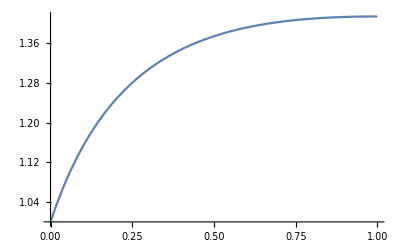

√2 σc

```mathematica
"If we use the Kraus Junction Conditions They're unstable, but fine, we can look at the dynamics of the radion"
Solve[μ/Ps^2+Ps^2(1-(σ/σc)^2)==0,σ]
σ/.%[[2]]
√(1+μ/Ps^4) σc/.Ps->√(√μ Cosh[-Log[√ξ]])//Simplify
Plot[%/.σc->1,{ξ,0,1}]
%%/.ξ->1
```

-(2 (ξc+ξ^2 ξc-ξ (1+ξc^2)))/(√ξ (1+ξ) (1+ξc)^2)

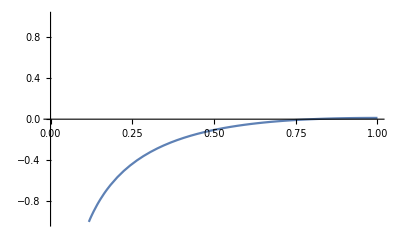

```mathematica
1/(√μ)(μ/Ps^2+Ps^2(1-(σ/σc)^2)/.Ps->√(√μ Cosh[-Log[√ξ]])/.σ->√(1+(4 ξc)/(1+ξc)^2)σc/.σc->1//Simplify)
 
Plot[%/.ξc->0.8,{ξ,0,1},PlotRange->{-1,1}]
(*Manipulate[Plot[%,{ξ,0,1},PlotRange->{-10,10}],{f,0,10}]*)
```

## Dilaton - Dalton Dilation potential

### Reproduce Zamir’s analysis

## Scrap

```mathematica
1/2 D[a[η]^-4 h[η]D[a[η]^2,η],η]/.a->afunc
k(a[η]^-2 D[h[η],η]-a[η]^-4 h[η]D[a[η]^2,η])/.a->afunc
```

1/2 (-4 ⅇ^(2 k η) k^2 h[η]-2 ⅇ^(2 k η) k h'[η])

k (2 ⅇ^(2 k η) k h[η]+ⅇ^(2 k η) h'[η])

```mathematica
D[g[η]^-1,{η,2}]-g[η] D[g[η]^-1,{η,1}]^2
DSolve[%==0,g,η]//Simplify
```

g'[η]^2/g[η]^3-g''[η]/g[η]^2

{{g→Function[{η},ⅇ^(η C[1]) C[2]]}}

```mathematica
D[g[η]^-1,{η,2}]+2 E^(k η)D[g[η]^-1,{η,1}] D[E^(-k η),{η,1}]-g[η] D[E^(-k η),{η,1}]^2
DSolve[%==0,g,η]//Simplify
```

-ⅇ^(-2 k η) k^2 g[η]+(2 k g'[η])/g[η]^2+(2 g'[η]^2)/g[η]^3-g''[η]/g[η]^2

DSolve[(2 g'[η] (k g[η]+g'[η]))/g[η]==ⅇ^(-2 k η) k^2 g[η]^3+g''[η],g,η]

#### Check if perturbed AdS-S metric has vanishing R_ηη

```mathematica
g0AdSS=DiagonalMatrix[{2 shη^2/chη,-2chη,-2chη,-2chη}]
```

{{2 √μ Sinh[(2 η)/l+Log[μ]/2] Tanh[(2 η)/l+Log[μ]/2],0,0,0},{0,-2 √μ Cosh[(2 η)/l+Log[μ]/2],0,0},{0,0,-2 √μ Cosh[(2 η)/l+Log[μ]/2],0},{0,0,0,-2 √μ Cosh[(2 η)/l+Log[μ]/2]}}

```mathematica
D[Inverse[g0AdSS],{η,2}]//Simplify;
D[Inverse[g0AdSS],{η,1}].g0AdSS.D[Inverse[g0AdSS],{η,1}];
%%-%//Simplify
(*Inverse[%]//Simplify*)
Series[%//TrigToExp//PowerExpand,{μ,0,1}]//Normal
"So At NTLO, we get something proportional to δg_μν"
```

{{1/(l^2 √μ)(1+3 Cosh[(4 η)/l+Log[μ]]) Csch[(2 η)/l+Log[μ]/2]^4 Sech[(2 η)/l+Log[μ]/2],0,0,0},{0,(2 Sech[(2 η)/l+Log[μ]/2]^3)/(l^2 √μ),0,0},{0,0,(2 Sech[(2 η)/l+Log[μ]/2]^3)/(l^2 √μ),0},{0,0,0,(2 Sech[(2 η)/l+Log[μ]/2]^3)/(l^2 √μ)}}

{{(48 ⅇ^((6 η)/l) μ)/l^2,0,0,0},{0,(16 ⅇ^((6 η)/l) μ)/l^2,0,0},{0,0,(16 ⅇ^((6 η)/l) μ)/l^2,0},{0,0,0,(16 ⅇ^((6 η)/l) μ)/l^2}}

So At NTLO, we get something proportional to δg_μν

```mathematica
Series[D[Inverse[g0AdSS],{η,2}]//Simplify//TrigToExp//PowerExpand,{μ,0,1}]//Normal
Series[D[Inverse[g0AdSS],{η,1}].g0AdSS.D[Inverse[g0AdSS],{η,1}]//TrigToExp//PowerExpand,{μ,0,1}]//Normal
%%-%//Simplify
```

{{(4 ⅇ^((2 η)/l))/l^2+(108 ⅇ^((6 η)/l) μ)/l^2,0,0,0},{0,-(4 ⅇ^((2 η)/l))/l^2+(36 ⅇ^((6 η)/l) μ)/l^2,0,0},{0,0,-(4 ⅇ^((2 η)/l))/l^2+(36 ⅇ^((6 η)/l) μ)/l^2,0},{0,0,0,-(4 ⅇ^((2 η)/l))/l^2+(36 ⅇ^((6 η)/l) μ)/l^2}}

{{(4 ⅇ^((2 η)/l))/l^2+(60 ⅇ^((6 η)/l) μ)/l^2,0,0,0},{0,-(4 ⅇ^((2 η)/l))/l^2+(20 ⅇ^((6 η)/l) μ)/l^2,0,0},{0,0,-(4 ⅇ^((2 η)/l))/l^2+(20 ⅇ^((6 η)/l) μ)/l^2,0},{0,0,0,-(4 ⅇ^((2 η)/l))/l^2+(20 ⅇ^((6 η)/l) μ)/l^2}}

{{(48 ⅇ^((6 η)/l) μ)/l^2,0,0,0},{0,(16 ⅇ^((6 η)/l) μ)/l^2,0,0},{0,0,(16 ⅇ^((6 η)/l) μ)/l^2,0},{0,0,0,(16 ⅇ^((6 η)/l) μ)/l^2}}

#### Junction condition solution AdS-S

```mathematica
"For f =0"
D[h[η],η]+2k h[η]- ηξμν 4 k μ E^(2k η)
DSolve[%==0,h,η]
```

For f =0

-4 ⅇ^(2 k η) k ηξμν μ+2 k h[η]+h'[η]

{{h→Function[{η},ⅇ^(2 k η) ηξμν μ+ⅇ^(-2 k η) C[1]]}}

```mathematica
ⅇ^(2 k η) ηξμν μ
D[%,η]+2 k %//Simplify
```

ⅇ^(2 k η) ηξμν μ

4 ⅇ^(2 k η) k ηξμν μ

```mathematica
Solve[η == tη + fx E^(2 k tη),tη]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{tη→(2 k η-ProductLog[2 ⅇ^(2 k η) fx k])/(2 k)}}

#### Convenient form for the metric

```mathematica
"The 00 part of the metric can be written as"
2chη(shη/chη)^2
"It would be convenient to define the metric in terms of something proportional to η_μν and something proportional to δ_0δ_0. We can write the metric as"
2 chη Subscript[η, μν] + 2 Subscript[δ, μ]^o Subscript[δ, ν]^o chη((shη/chη)^2-1)//Simplify
2 chη Subscript[η, μν] + 2 Subscript[δ, μ]^o Subscript[δ, ν]^o 1/chη(shη^2-chη^2)//Simplify
"And since "
shη^2-chη^2//Simplify
" we can write"
2 chη Subscript[η, μν] - 2 Subscript[δ, μ]^o Subscript[δ, ν]^o μ/chη//Simplify
"The derivatives of chη are simple"
chη
D[%,η]
D[%,η]//Simplify
"The derivatives of chη^-1 are not simple, but their power expansion is all that is left at higher order"
Series[2chη//TrigToExp//PowerExpand,{μ,0,3}]//Normal
Series[(2 μ)/chη//TrigToExp//PowerExpand,{μ,0,6}]//Normal
"So the lorentz violating term can be written as a simple closed sum. What does the inverse metric look like?"
DiagonalMatrix@{2 ch - (2 μ)/ch,-2ch,-2ch,-2ch}
Inverse@%//Simplify
"So we can similarily write the inverse 00 component which is not propto η^μν as "
(*chη/(2(chη^2-μ))-1/(2 chη)//Simplify*)
HoldForm@(chη/(2(chη^2-μ))-1/(2 chη))
μ/(2chη shη^2)//Simplify
HoldForm@(μ/(2chη shη^2))
Series[μ/(2chη shη^2)//TrigToExp//PowerExpand,{μ,0,6}]//Normal
(*Series[1/(4 μ chη)//TrigToExp//PowerExpand,{μ,0,6}]//Normal*)
"this doesn't seem to make things any better. Ah but it does. We can use the hyperbolic trig identities to simplify things and do everything analytically"
```

The 00 part of the metric can be written as

2 √μ Sinh[(2 η)/l+Log[μ]/2] Tanh[(2 η)/l+Log[μ]/2]

It would be convenient to define the metric in terms of something proportional to η_μν and something proportional to δ_0δ_0. We can write the metric as

√μ Sech[(2 η)/l+Log[μ]/2] (-2 δ_μ^o δ_ν^o+(1+Cosh[(4 η)/l+Log[μ]]) η_μν)

√μ Sech[(2 η)/l+Log[μ]/2] (-2 δ_μ^o δ_ν^o+(1+Cosh[(4 η)/l+Log[μ]]) η_μν)

And since

-μ

we can write

√μ Sech[(2 η)/l+Log[μ]/2] (-2 δ_μ^o δ_ν^o+(1+Cosh[(4 η)/l+Log[μ]]) η_μν)

The derivatives of chη are simple

√μ Cosh[(2 η)/l+Log[μ]/2]

(2 √μ Sinh[(2 η)/l+Log[μ]/2])/l

(4 √μ Cosh[(2 η)/l+Log[μ]/2])/l^2

The derivatives of chη^-1 are not simple, but their power expansion is all that is left at higher order

ⅇ^(-(2 η)/l)+ⅇ^((2 η)/l) μ

4 ⅇ^((2 η)/l) μ-4 ⅇ^((6 η)/l) μ^2+4 ⅇ^((10 η)/l) μ^3-4 ⅇ^((14 η)/l) μ^4+4 ⅇ^((18 η)/l) μ^5-4 ⅇ^((22 η)/l) μ^6

So the lorentz violating term can be written as a simple closed sum. What does the inverse metric look like?

{{2 ch-(2 μ)/ch,0,0,0},{0,-2 ch,0,0},{0,0,-2 ch,0},{0,0,0,-2 ch}}

{{ch/(2 ch^2-2 μ),0,0,0},{0,-1/(2 ch),0,0},{0,0,-1/(2 ch),0},{0,0,0,-1/(2 ch)}}

So we can similarily write the inverse 00 component which is not propto η^μν as

chη/(2 (chη^2-μ))-1/(2 chη)

(Csch[(2 η)/l+Log[μ]/2] Csch[(4 η)/l+Log[μ]])/(√μ)

μ/(2 chη shη^2)

4 ⅇ^((6 η)/l) μ+4 ⅇ^((10 η)/l) μ^2+8 ⅇ^((14 η)/l) μ^3+8 ⅇ^((18 η)/l) μ^4+12 ⅇ^((22 η)/l) μ^5+12 ⅇ^((26 η)/l) μ^6

this doesn't seem to make things any better. Ah but it does. We can use the hyperbolic trig identities to simplify things and do everything analytically

```mathematica
"We need integrals of the inverse metric for gauge transformations "
Integrate[chη/shη^2,η]
Integrate[1/chη,η]
Series[%//TrigToExp//PowerExpand,{μ,0,6}]//Normal
Integrate[shη^2/chη,η]//Simplify
```

We need integrals of the inverse metric for gauge transformations

-(l Csch[(2 η)/l+Log[μ]/2])/(2 √μ)

(l ArcTan[Sinh[(2 η)/l+Log[μ]/2]])/(2 √μ)

ⅇ^((2 η)/l) l-1/3 ⅇ^((6 η)/l) l μ+1/5 ⅇ^((10 η)/l) l μ^2-1/7 ⅇ^((14 η)/l) l μ^3+1/9 ⅇ^((18 η)/l) l μ^4-1/11 ⅇ^((22 η)/l) l μ^5+1/13 ⅇ^((26 η)/l) l μ^6-(ⅈ (l Log[-(ⅈ ⅇ^(-(2 η)/l))/(2 √μ)]-l Log[(ⅈ ⅇ^(-(2 η)/l))/(2 √μ)]))/(4 √μ)

1/2 l √μ (-ArcTan[Sinh[(2 η)/l+Log[μ]/2]]+Sinh[(2 η)/l+Log[μ]/2])

```mathematica
Simplify[TrigToExp[1/2 l √μ (-ArcTan[Sinh[(2 η)/l+Log[μ]/2]]+Sinh[(2 η)/l+Log[μ]/2])]]
```

1/4 l (-ⅇ^(-(2 η)/l)+ⅇ^((2 η)/l) μ-ⅈ √μ Log[-(ⅈ ⅇ^(-(2 η)/l) (ⅈ+ⅇ^((2 η)/l) √μ)^2)/(2 √μ)]+ⅈ √μ Log[1+(ⅈ ⅇ^(-(2 η)/l) (-1+ⅇ^((4 η)/l) μ))/(2 √μ)])

```mathematica
Integrate[1/(E^x+E^-x),x]
```

ArcTan[ⅇ^x]

```mathematica
Simplify[TrigToExp[ArcTan[ⅇ^x]]]
```

1/2 ⅈ (Log[1-ⅈ ⅇ^x]-Log[1+ⅈ ⅇ^x])

```mathematica
Solve[I ==Log[x],x]
```

{{x→ⅇ^ⅈ}}

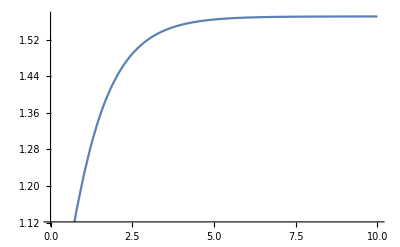

```mathematica
Plot[ArcTan[E^x],{x,0,10}]
```

```mathematica
Integrate[1/chη,η]
Series[%//TrigToExp//PowerExpand,{μ,0,1}]//ExpToTrig
```

(l ArcTan[Sinh[(2 η)/l+Log[μ]/2]])/(2 √μ)

-(ⅈ (l Log[-(ⅈ (Cosh[(2 η)/l]-Sinh[(2 η)/l]))/(2 √μ)]-l Log[(ⅈ (Cosh[(2 η)/l]-Sinh[(2 η)/l]))/(2 √μ)]))/(4 √μ)+(l Cosh[(2 η)/l]+l Sinh[(2 η)/l])+1/3 (-l Cosh[(6 η)/l]-l Sinh[(6 η)/l]) μ+O[μ]^(3/2)

```mathematica
Tan[θ ]==Sinh[(2 η)/l+Log[μ]/2]/1
```

Tan[θ]==Sinh[(2 η)/l+Log[μ]/2]

1/2 ⅇ^(-(2 η)/l)-1/2 ⅇ^((2 η)/l) μ+O[μ]^2

ArcTan[1/2 ⅇ^(-(2 η)/l)-1/2 ⅇ^((2 η)/l) μ]

ArcTan[1/2 ⅇ^(-(2 η)/l)]-(2 ⅇ^((6 η)/l) μ)/(1+4 ⅇ^((4 η)/l))+O[μ]^2

```mathematica
shη//TrigToExp
```

1/2 ⅇ^(-(2 η)/l)-1/2 ⅇ^((2 η)/l) μ

```mathematica
ArcTan[x]//TrigToExp
```

1/2 ⅈ Log[1-ⅈ x]-1/2 ⅈ Log[1+ⅈ x]

```mathematica
I/2(Log[Abs[1-I x]]- Log[Abs[1+I x]]) + I/2(I arg[1-I x]-I arg[1+I x])
%==I/2(I arg[1-I x]-I arg[1+I x])
```

1/2 ⅈ (ⅈ arg[1-ⅈ x]-ⅈ arg[1+ⅈ x])+1/2 ⅈ (Log[Abs[1-ⅈ x]]-Log[Abs[1+ⅈ x]])

1/2 ⅈ (ⅈ arg[1-ⅈ x]-ⅈ arg[1+ⅈ x])+1/2 ⅈ (Log[Abs[1-ⅈ x]]-Log[Abs[1+ⅈ x]])==1/2 ⅈ (ⅈ arg[1-ⅈ x]-ⅈ arg[1+ⅈ x])

```mathematica
Integrate[Series[1/chη//TrigToExp//PowerExpand,{μ,0,1}]//Normal,η]
Series[Integrate[1/chη,η,Assumptions->{η∈ Reals}]//TrigToExp//PowerExpand,{μ,0,1}]//Normal
```

ⅇ^((2 η)/l) l-1/3 ⅇ^((6 η)/l) l μ

ⅇ^((2 η)/l) l-1/3 ⅇ^((6 η)/l) l μ-(ⅈ (l Log[-(ⅈ ⅇ^(-(2 η)/l))/(2 √μ)]-l Log[(ⅈ ⅇ^(-(2 η)/l))/(2 √μ)]))/(4 √μ)

```mathematica
Integrate[1/chη,η,Assumptions->{η∈ Reals}]//TrigToExp//PowerExpand
Series[%,{μ,0,1}]
```

(ⅈ l Log[1-1/2 ⅈ (-ⅇ^(-(2 η)/l)/(√μ)+ⅇ^((2 η)/l) √μ)])/(4 √μ)-(ⅈ l Log[1+1/2 ⅈ (-ⅇ^(-(2 η)/l)/(√μ)+ⅇ^((2 η)/l) √μ)])/(4 √μ)

-(ⅈ (l Log[-(ⅈ ⅇ^(-(2 η)/l))/(2 √μ)]-l Log[(ⅈ ⅇ^(-(2 η)/l))/(2 √μ)]))/(4 √μ)+ⅇ^((2 η)/l) l-1/3 (ⅇ^((6 η)/l) l) μ+O[μ]^(3/2)

```mathematica
Integrate[1/chη,η]
Series[shη//TrigToExp//PowerExpand,{μ,0,1}]
ArcTan[Normal@%]
Series[%,{μ,0,1}]
```

(l ArcTan[Sinh[(2 η)/l+Log[μ]/2]])/(2 √μ)

1/2 ⅇ^(-(2 η)/l)-1/2 ⅇ^((2 η)/l) μ+O[μ]^2

ArcTan[1/2 ⅇ^(-(2 η)/l)-1/2 ⅇ^((2 η)/l) μ]

ArcTan[1/2 ⅇ^(-(2 η)/l)]-(2 ⅇ^((6 η)/l) μ)/(1+4 ⅇ^((4 η)/l))+O[μ]^2

```mathematica
Evaluate[-I/2 Log[(x/I-1)/(x/I+1)]/.x->HoldForm[-I Sin[I z]]]//Simplify
-1/2 I Log[(Sin[I z]+1)/(Sin[I z]-1)]
```

-1/2 ⅈ Log[(-ⅈ+-ⅈ Sin[ⅈ z])/(ⅈ+-ⅈ Sin[ⅈ z])]

-1/2 ⅈ Log[(1+ⅈ Sinh[z])/(-1+ⅈ Sinh[z])]

```mathematica
ArcTan[Sin[x]]//TrigToExp
```

1/2 ⅈ Log[1+1/2 (ⅇ^(-ⅈ x)-ⅇ^(ⅈ x))]-1/2 ⅈ Log[1+1/2 (-ⅇ^(-ⅈ x)+ⅇ^(ⅈ x))]

```mathematica
ArcTan[E^x]
```

ArcTan[ⅇ^x]

```mathematica
chη//TrigToExp
```

1/2 ⅇ^(-(2 η)/l)+1/2 ⅇ^((2 η)/l) μ

```mathematica
1/(μ E^(2 η/l)+E^(-2 η/l))
E^(-2 η/l)/(μ+E^(-4 η/l))
Integrate[%,η]
```

1/(ⅇ^(-(2 η)/l)+ⅇ^((2 η)/l) μ)

ⅇ^(-(2 η)/l)/(ⅇ^(-(4 η)/l)+μ)

(l ArcTan[ⅇ^((2 η)/l) √μ])/(2 √μ)

```mathematica
1/N@EulerGamma
```

1.73245

```mathematica
D[ArcTan[shη],η]
%//TrigToExp//FullSimplify
```

-(2 √μ Cosh[(2 η)/l+Log[μ]/2])/(l (1+μ Sinh[(2 η)/l+Log[μ]/2]^2))

-(4 ⅇ^((2 η)/l) (1+ⅇ^((4 η)/l) μ))/(l-2 ⅇ^((4 η)/l) l (-2+μ)+ⅇ^((8 η)/l) l μ^2)

```mathematica
Integrate[1/chη,η]
D[%,η]//Simplify
```

(l ArcTan[Sinh[(2 η)/l+Log[μ]/2]])/(2 √μ)

Sech[(2 η)/l+Log[μ]/2]/(√μ)

```mathematica
1/(chη shη^2)+
```

-(l Csch[(2 η)/l+Log[μ]/2] Hypergeometric2F1[-1/2,1,1/2,-Sinh[(2 η)/l+Log[μ]/2]^2])/(2 μ^(3/2))

```mathematica
1/2 Integrate[chη/shη^2,η]
-(*1/2*)Integrate[1/chη,η]
```

-(l Csch[(2 η)/l+Log[μ]/2])/(4 √μ)

-(l ArcTan[Sinh[(2 η)/l+Log[μ]/2]])/(2 √μ)

```mathematica
shη
```

-√μ Sinh[(2 η)/l+Log[μ]/2]

```mathematica
chη
```

√μ Cosh[(2 η)/l+Log[μ]/2]

```mathematica
Sinh[(2 η)/l+Log[μ]/2]
-shη
```

Sinh[(2 η)/l+Log[μ]/2]

√μ Sinh[(2 η)/l+Log[μ]/2]

```mathematica
D[chη,η]
Series[%//TrigToExp,{μ,0,1}]
```

(2 √μ Sinh[(2 η)/l+Log[μ]/2])/l

-ⅇ^(-(2 η)/l)/l+(ⅇ^((2 η)/l) μ)/l+O[μ]^2

```mathematica
D[chη,η]
Series[shη/chη//TrigToExp,{μ,0,1}]
```

(2 √μ Sinh[(2 η)/l+Log[μ]/2])/l

1-2 ⅇ^((4 η)/l) μ+O[μ]^(3/2)

```mathematica
shη
```

-√μ Sinh[(2 η)/l+Log[μ]/2]

```mathematica
Series[2 shη^2/chη//TrigToExp,{μ,0,1}]
Series[-2chη//TrigToExp,{μ,0,1}]
```

ⅇ^(-(2 η)/l)-3 ⅇ^((2 η)/l) μ+O[μ]^(3/2)

-ⅇ^(-(2 η)/l)-ⅇ^((2 η)/l) μ+O[μ]^2

```mathematica
D[chη,η]
Series[%//TrigToExp,{μ,0,1}]
```

(2 √μ Sinh[(2 η)/l+Log[μ]/2])/l

-ⅇ^(-(2 η)/l)/l+(ⅇ^((2 η)/l) μ)/l+O[μ]^2

```mathematica
gAdSS
```

```mathematica
gAdSS = 2 DiagonalMatrix[{ch[η] - μh/ch[η],-ch[η],-ch[η],-ch[η],-1/2}]/.ch[η]->chη/.μ->μh
```

{{2 (√μh Cosh[(2 η)/l+Log[μh]/2]-√μh Sech[(2 η)/l+Log[μh]/2]),0,0,0,0},{0,-2 √μh Cosh[(2 η)/l+Log[μh]/2],0,0,0},{0,0,-2 √μh Cosh[(2 η)/l+Log[μh]/2],0,0},{0,0,0,-2 √μh Cosh[(2 η)/l+Log[μh]/2],0},{0,0,0,0,-1}}

```mathematica
D[Tr[Inverse[gAdSS].D[gAdSS,η]],η]//Simplify
2/l μh/shη^3 D[gAdSS,η][[1,1]]/.μ->μh
%%-%//Simplify
Series[%//TrigToExp,{μh,0,1}]
```

-(32 Csch[(4 η)/l+Log[μh]]^2)/l^2

-(4 Csch[(2 η)/l+Log[μh]/2]^3 ((2 √μh Sinh[(2 η)/l+Log[μh]/2])/l+(2 √μh Sech[(2 η)/l+Log[μh]/2] Tanh[(2 η)/l+Log[μh]/2])/l))/(l √μh)

(8 Csch[(2 η)/l+Log[μh]/2]^2)/l^2

(32 ⅇ^((4 η)/l) μh)/l^2+O[μh]^(3/2)

```mathematica
D[-2 μ/chη,η]//FullSimplify
%/( 2 √μ shη^2/chη)^2
Series[%//TrigToExp,{μ,0,1}]
(*Series[%//TrigToExp,{μ,0,1}]*)
```

(4 √μ Sech[(2 η)/l+Log[μ]/2] Tanh[(2 η)/l+Log[μ]/2])/l

Csch[(2 η)/l+Log[μ]/2]^3/(l μ^(3/2))

-(8 ⅇ^((6 η)/l))/l-(24 ⅇ^((10 η)/l) μ)/l+O[μ]^2

```mathematica
D[( 2 shη^2/chη)^-1,η]//Simplify
Series[%//TrigToExp,{μ,0,1}]
```

-((3+Cosh[(4 η)/l+Log[μ]]) Csch[(2 η)/l+Log[μ]/2]^3)/(2 l √μ)

(2 ⅇ^((2 η)/l))/l+(18 ⅇ^((6 η)/l) μ)/l+O[μ]^2

```mathematica
D[Tr[Inverse[gAdSS].D[gAdSS,η]],η]//Simplify
2/l μh/shη^3 D[gAdSS,η][[1,1]]/.μ->μh
%%-%//Simplify
Series[%//TrigToExp,{μh,0,1}]
```

-(32 Csch[(4 η)/l+Log[μh]]^2)/l^2

-(4 Csch[(2 η)/l+Log[μh]/2]^3 ((2 √μh Sinh[(2 η)/l+Log[μh]/2])/l+(2 √μh Sech[(2 η)/l+Log[μh]/2] Tanh[(2 η)/l+Log[μh]/2])/l))/(l √μh)

(8 Csch[(2 η)/l+Log[μh]/2]^2)/l^2

(32 ⅇ^((4 η)/l) μh)/l^2+O[μh]^(3/2)

#### tut scrap

```mathematica
{{γ,-γ β,0,0},{-γ β,γ,0,0},{0,0,1,0},{0,0,0,1}}.{{0,Ex,Ey,0},{-Ex,0,0,0},{-Ey,0,0,0},{0,0,0,0}}.{{γ,-γ β,0,0},{-γ β,γ,0,0},{0,0,1,0},{0,0,0,1}}/.γ->1/(√(1-β^2))//Simplify//MatrixForm
```

(0 | Ex | Ey/(√(1-β^2)) | 0
-Ex | 0 | -(Ey β)/(√(1-β^2)) | 0
-Ey/(√(1-β^2)) | (Ey β)/(√(1-β^2)) | 0 | 0
0 | 0 | 0 | 0)

#### GT scrap

```mathematica
1/ch/.ch->√(μ/(2 ξ))(1+ξ)
dξ->D[E^(4 η/l)μ,η]dη/.η->l/4 Log[ξ/μ]/.l->1/k
%% (dξ/.%)/dη//PowerExpand
Integrate[%,ξ]
```

(√2)/(√(μ/ξ) (1+ξ))

dξ→4 dη k ξ

(4 √2 k ξ^(3/2))/(√μ (1+ξ))

(4 √2 k (2/3 (-3+ξ) √ξ+2 ArcTan[√ξ]))/(√μ)

```mathematica
μ/(2 sh^2 ch)/.ch->√(μ/(2 ξ))(1+ξ)/.sh->√(μ/(2 ξ))(1-ξ)
dξ->D[E^(4 η/l)μ,η]dη/.η->l/4 Log[ξ/μ]/.l->1/k
%% (dξ/.%)/dη//PowerExpand
Integrate[%,ξ]
```

(√2 ξ)/((1-ξ)^2 √(μ/ξ) (1+ξ))

dξ→4 dη k ξ

(4 √2 k ξ^(5/2))/(√μ (1-ξ)^2 (1+ξ))

(2 √2 k ((√ξ (-5+4 ξ))/(-1+ξ)-ArcTan[√ξ]-4 ArcTanh[√ξ]))/(√μ)

```mathematica
ch/(2 sh^2)/.ch->√(μ/(4 ξ))(1+ξ)/.sh->√(μ/(4 ξ))(1-ξ)//PowerExpand
dξ->D[E^(4 η/l)μ,η]dη/.η->l/4 Log[ξ/μ]/.l->1/k
%% (dξ/.%)/dη//PowerExpand
Integrate[%,ξ]
```

(√ξ (1+ξ))/(√μ (1-ξ)^2)

dξ→4 dη k ξ

(4 k ξ^(3/2) (1+ξ))/(√μ (1-ξ)^2)

(4 k ((2 √ξ (-12+8 ξ+ξ^2))/(3 (-1+ξ))-8 ArcTanh[√ξ]))/(√μ)

```mathematica
D[√(μ/(4 ξ))(1+ξ),ξ]//Simplify//PowerExpand
```

(√μ (-1+ξ))/(4 ξ^(3/2))

```mathematica
1/(2ch)/.ch->√(μ/(4 ξ))(1+ξ)
dξ->D[E^(4 η/l)μ,η]dη/.η->l/4 Log[ξ/μ]/.l->1/k
%% (dξ/.%)/dη/.ξ->E^(4 η k)μ//PowerExpand
Integrate[%,η]//Simplify
```

1/(√(μ/ξ) (1+ξ))

dξ→4 dη k ξ

(4 ⅇ^(6 k η) k μ)/(1+ⅇ^(4 k η) μ)

2 ⅇ^(2 k η)-(2 ArcTan[ⅇ^(2 k η) √μ])/(√μ)

```mathematica
ch/(2 sh^2)/.ch->√(μ/(4 ξ))(1+ξ)/.sh->√(μ/(4 ξ))(1-ξ)//PowerExpand
dξ->D[E^(4 η/l)μ,η]dη/.η->l/4 Log[ξ/μ]/.l->1/k
%% (dξ/.%)/dη/.ξ->E^(4 η k)μ//PowerExpand
Integrate[%,η]//FullSimplify
```

(√ξ (1+ξ))/(√μ (1-ξ)^2)

dξ→4 dη k ξ

(4 ⅇ^(6 k η) k μ (1+ⅇ^(4 k η) μ))/((1-ⅇ^(4 k η) μ)^2)

2 (ⅇ^(2 k η)+1/(ⅇ^(-2 k η)-ⅇ^(2 k η) μ)-(2 ArcTanh[ⅇ^(2 k η) √μ])/(√μ))

```mathematica
μ/(2 sh^2 ch)/.ch->√(μ/(4 ξ))(1+ξ)/.sh->√(μ/(4 ξ))(1-ξ)//PowerExpand
dξ->D[E^(4 η/l)μ,η]dη/.η->l/4 Log[ξ/μ]/.l->1/k
%% (dξ/.%)/dη/.ξ->E^(4 η k)μ//PowerExpand
Integrate[%,η]//FullSimplify;
%/.η->1/(4 k)Log[ξ/μ]//PowerExpand
Series[%,{ξ,0,3}]
```

(4 ξ^(3/2))/(√μ (1-ξ)^2 (1+ξ))

dξ→4 dη k ξ

(16 ⅇ^(10 k η) k μ^2)/((1-ⅇ^(4 k η) μ)^2 (1+ⅇ^(4 k η) μ))

(2 ((√ξ)/(1-ξ)+ArcTan[√ξ]-2 ArcTanh[√ξ]))/(√μ)

(8 ξ^(5/2))/(5 √μ)+O[ξ]^(7/2)

Above is incorrect because of measure

```mathematica
μ/(2 sh^2 ch)/.ch->√(μ/(4 ξ))(1+ξ)/.sh->√(μ/(4 ξ))(1-ξ)//PowerExpand
(*dξ->D[E^(4 η/l)μ,η]dη/.η->l/4 Log[ξ/μ]/.l->1/k*)
(*%% (dξ/.%)/dη/.ξ->E^(4 η k)μ//PowerExpand*)
Integrate[%/.ξ->E^(4 η k)μ,η]//PowerExpand//Simplify
%/.η->1/(4 k)Log[ξ/μ]//PowerExpand
Series[%,{ξ,0,3}]
```

(4 ξ^(3/2))/(√μ (1-ξ)^2 (1+ξ))

(ⅇ^(2 k η)/(1-ⅇ^(4 k η) μ)-ArcTan[ⅇ^(2 k η) √μ]/(√μ))/(2 k)

((√ξ)/(√μ (1-ξ))-ArcTan[√ξ]/(√μ))/(2 k)

(2 ξ^(3/2))/(3 k √μ)+(2 ξ^(5/2))/(5 k √μ)+O[ξ]^(7/2)

This is the integral of the GT in AdS-S

```mathematica
1/(2 ch)/.ch->√(μ/(4 ξ))(1+ξ)/.sh->√(μ/(4 ξ))(1-ξ)//PowerExpand
(*dξ->D[E^(4 η/l)μ,η]dη/.η->l/4 Log[ξ/μ]/.l->1/k*)
(*%% (dξ/.%)/dη/.ξ->E^(4 η k)μ//PowerExpand*)
Integrate[%/.ξ->E^(4 η k)μ,η]//PowerExpand//Simplify
%/.η->1/(4 k)Log[ξ/μ]//PowerExpand
Series[%,{ξ,0,3}]
```

(√ξ)/(√μ (1+ξ))

ArcTan[ⅇ^(2 k η) √μ]/(2 k √μ)

ArcTan[√ξ]/(2 k √μ)

(√ξ)/(2 k √μ)-ξ^(3/2)/(6 (k √μ))+ξ^(5/2)/(10 k √μ)+O[ξ]^(7/2)

```mathematica
Series[ArcTan[√x]/(√x),{x,0,15}]
"So ArcTan[√x] is given by: √x (Σ^∞)_(n = 0) (-x)^n/(1  +  2  n)"
Series[ArcTanh[x],{x,0,15}]
Series[Tanh[-Log@√x],{x,0,15}]
Series[(1-x)/(1+x),{x,0,15}]
```

1-x/3+x^2/5-x^3/7+x^4/9-x^5/11+x^6/13-x^7/15+x^8/17-x^9/19+x^10/21-x^11/23+x^12/25-x^13/27+x^14/29-x^15/31+O[x]^(31/2)

So ArcTan[√x] is given by: √x (Σ^∞)_(n = 0) (-x)^n/(1  +  2  n)

x+x^3/3+x^5/5+x^7/7+x^9/9+x^11/11+x^13/13+x^15/15+O[x]^16

1-2 x+2 x^2-2 x^3+2 x^4-2 x^5+2 x^6-2 x^7+2 x^8-2 x^9+2 x^10-2 x^11+2 x^12-2 x^13+2 x^14-2 x^15+O[x]^16

1-2 x+2 x^2-2 x^3+2 x^4-2 x^5+2 x^6-2 x^7+2 x^8-2 x^9+2 x^10-2 x^11+2 x^12-2 x^13+2 x^14-2 x^15+O[x]^16

```mathematica
shη/chη^2
D[%,η]
%//Simplify
```

-(Sech[(2 η)/l+Log[μ]/2] Tanh[(2 η)/l+Log[μ]/2])/(√μ)

-(2 Sech[(2 η)/l+Log[μ]/2]^3)/(l √μ)+(2 Sech[(2 η)/l+Log[μ]/2] Tanh[(2 η)/l+Log[μ]/2]^2)/(l √μ)

((-3+Cosh[(4 η)/l+Log[μ]]) Sech[(2 η)/l+Log[μ]/2]^3)/(l √μ)

```mathematica
Sech[(2 η)/l+Log[μ]/2]^-1
```

Cosh[(2 η)/l+Log[μ]/2]

```mathematica
D[sh[η]/ch[η]^2,η]
%/.{sh'[η]->-2k ch[η],ch'[η]->-2k sh[η]}//Simplify
%/.sh[η]->√(ch[η]^2-μ)//Simplify
D[ch[η],η]
%/.{sh'[η]->-2k ch[η],ch'[η]->-2k sh[η]}//Simplify
```

-(2 sh[η] ch'[η])/ch[η]^3+sh'[η]/ch[η]^2

-(2 k (ch[η]^2-2 sh[η]^2))/ch[η]^3

(2 k (-2 μ+ch[η]^2))/ch[η]^3

ch'[η]

-2 k sh[η]

```mathematica
√(μ/ξ)(1+ξ)ArcTan[√ξ]/(√μ)//PowerExpand
D[%,ξ]//Simplify//PowerExpand//Simplify
%/(%%)//FullSimplify
```

((1+ξ) ArcTan[√ξ])/(√ξ)

(√ξ+(-1+ξ) ArcTan[√ξ])/(2 ξ^(3/2))

(√ξ+(-1+ξ) ArcTan[√ξ])/(2 ξ (1+ξ) ArcTan[√ξ])

#### ML SC scrap

```mathematica
U=1/2{{1,1},{1,-1}};
η2={{1,0},{0,-1}};
U.η2
%.Transpose[U]
```

{{1/2,-1/2},{1/2,1/2}}

{{0,1/2},{1/2,0}}

```mathematica
pi = {p0,pn,pp1,pp2}
(*pf = {(p0-pn)/2,(pn+p0)/2,pp1,pp2}*)
pf = {p0-pn,pn+p0,pp1,pp2}
(*Jac=#.DiagonalMatrix[{√2,√2,1,1}]&@Table[Table[D[pf[[i]],pi[[j]]],{i,4}],{j,4}]*)
(*Inverse[%].DiagonalMatrix[{1,-1,-1,-1}].%*)
Jac=#&@Table[Table[D[pf[[i]],pi[[j]]],{i,4}],{j,4}]
(*Inverse[%].DiagonalMatrix[{1,-1,-1,-1}].%*)
{{0,1/2,0,0},{1/2,0,0,0},{0,0,-1,0},{0,0,0,-1}}
pi.Jac.%.Transpose[Jac].pi//Expand
pf.%%.pf//Expand
(*{p0-pn,pn+p0,pp1,pp2}.%.{p0-pn,pn+p0,pp1,pp2}//Expand*)
```

{p0,pn,pp1,pp2}

{p0-pn,p0+pn,pp1,pp2}

{{1,1,0,0},{-1,1,0,0},{0,0,1,0},{0,0,0,1}}

{{0,1/2,0,0},{1/2,0,0,0},{0,0,-1,0},{0,0,0,-1}}

p0^2-pn^2-pp1^2-pp2^2

p0^2-pn^2-pp1^2-pp2^2

```mathematica
Solve[pf=={p0p,pnp,pp1,pp2},{p0,pn}]
```

{{p0→(p0p+pnp)/2,pn→1/2 (-p0p+pnp)}}

```mathematica
pi = {p0,pn,pp1,pp2}
(*pf = {(p0-pn)/2,(pn+p0)/2,pp1,pp2}*)
pf = {(p0-pn)/(√2),(pn+p0)/(√2),pp1,pp2}
(*pf = {p0p,pnp,pp1,pp2}*)
(*Jac=#.DiagonalMatrix[{√2,√2,1,1}]&@Table[Table[D[pf[[i]],pi[[j]]],{i,4}],{j,4}]*)
(*Inverse[%].DiagonalMatrix[{1,-1,-1,-1}].%*)
(*Jac=#&@Table[Table[D[pi[[i]],pf[[j]]],{j,4}],{i,4}]
%.DiagonalMatrix[{1,-1,-1,-1}].Transpose[%]*)
Jac=#&@Table[Table[D[pf[[i]],pi[[j]]],{j,4}],{i,4}]
%.DiagonalMatrix[{1,-1,-1,-1}].Transpose[%]
(*DiagonalMatrix[{1,-1,-1,-1}]*)
(*{{0,1/2,0,0},{1/2,0,0,0},{0,0,-1,0},{0,0,0,-1}}*)
pi.Jac.%.Inverse[Jac].pi//Expand
pi.Jac.%%.Transpose[Jac].pi//Expand
pf.%%%.pf//Expand
pi.Transpose@Jac.%%%%.Jac.pi//Expand
```

{p0,pn,pp1,pp2}

{(p0-pn)/(√2),(p0+pn)/(√2),pp1,pp2}

{{1/(√2),-1/(√2),0,0},{1/(√2),1/(√2),0,0},{0,0,1,0},{0,0,0,1}}

{{0,1,0,0},{1,0,0,0},{0,0,-1,0},{0,0,0,-1}}

-p0^2+pn^2-pp1^2-pp2^2

-p0^2+pn^2-pp1^2-pp2^2

p0^2-pn^2-pp1^2-pp2^2

p0^2-pn^2-pp1^2-pp2^2

```mathematica
"try to change normalization"
```

```mathematica
Transpose[Jac].pi
Inverse[Jac].pi
```

{p0-pn,p0+pn,pp1,pp2}

{p0/2-pn/2,p0/2+pn/2,pp1,pp2}

```mathematica
pi = {p0,pn,pp1,pp2}
(*pf = {(p0-pn)/2,(pn+p0)/2,pp1,pp2}*)
pf = {p0-pn,pn+p0,pp1,pp2}
(*Jac=#.DiagonalMatrix[{√2,√2,1,1}]&@Table[Table[D[pf[[i]],pi[[j]]],{i,4}],{j,4}]*)
(*Inverse[%].DiagonalMatrix[{1,-1,-1,-1}].%*)
Jac=#&@Table[Table[D[pf[[i]],pi[[j]]],{i,4}],{j,4}]
(*Inverse[%].DiagonalMatrix[{1,-1,-1,-1}].%*)
{{0,1/2,0,0},{1/2,0,0,0},{0,0,-1,0},{0,0,0,-1}}
pi.Jac.%.Transpose[Jac].pi//Expand
pf.%%.pf//Expand
```

{p0,pn,pp1,pp2}

{p0-pn,p0+pn,pp1,pp2}

{{1,1,0,0},{-1,1,0,0},{0,0,1,0},{0,0,0,1}}

{{0,1/2,0,0},{1/2,0,0,0},{0,0,-1,0},{0,0,0,-1}}

p0^2-pn^2-pp1^2-pp2^2

p0^2-pn^2-pp1^2-pp2^2

```mathematica
(pf/.pfsol)//Simplify
```

{p0p,pnp,pp1,pp2}

```mathematica
pi = {p0,pn,pp1,pp2}
(*pf = {(p0-pn)/2,(pn+p0)/2,pp1,pp2}*)
pf = {p0-pn,pn+p0,pp1,pp2}
pfsol=Solve[%[[;;2]]=={p0p,pnp},{p0,pn}][[1]]
(*pf = {p0p,pnp,pp1,pp2}*)
(*Jac=#.DiagonalMatrix[{√2,√2,1,1}]&@Table[Table[D[pf[[i]],pi[[j]]],{i,4}],{j,4}]*)
(*Inverse[%].DiagonalMatrix[{1,-1,-1,-1}].%*)
(*Jac=#&@Table[Table[D[pi[[i]],pf[[j]]],{j,4}],{i,4}]
%.DiagonalMatrix[{1,-1,-1,-1}].Transpose[%]*)
Jac=#&@Table[Table[D[(pi/.pfsol)[[i]],(pf/.pfsol//Simplify)[[j]]],{i,4}],{j,4}]
%.DiagonalMatrix[{1,-1,-1,-1}].Transpose[%]
(*DiagonalMatrix[{1,-1,-1,-1}]*)
(*{{0,1/2,0,0},{1/2,0,0,0},{0,0,-1,0},{0,0,0,-1}}*)
(*pi.Jac.%.Inverse[Jac].pi//Expand
pi.Jac.%%.Transpose[Jac].pi//Expand*)
pf.%.pf//Expand
(*pi.Transpose@Jac.%%%%.Jac.pi//Expand*)
```

{p0,pn,pp1,pp2}

{p0-pn,p0+pn,pp1,pp2}

{p0→(p0p+pnp)/2,pn→1/2 (-p0p+pnp)}

{{1/2,-1/2,0,0},{1/2,1/2,0,0},{0,0,1,0},{0,0,0,1}}

{{0,1/2,0,0},{1/2,0,0,0},{0,0,-1,0},{0,0,0,-1}}

p0^2-pn^2-pp1^2-pp2^2

#### Ml

```mathematica
z1 z2 p0^2 θ^2/2+2/p0^2(2 p0^4 z1^3 θ^2 + 2 p0^4 z2^3 θ^2)/.z1->z /.z2->1-z//Simplify
```

1/2 p0^2 (8-23 z+23 z^2) θ^2

```mathematica
Integrate[Boole[ϵ^2-(2 (s+sp)-4 Min[z(1-z),zp(1-zp)] √(s/(z(1-z)) sp/(zp(1-zp))))>0],z]//Simplify
```

Piecewise[{{z, (z^2+zp≥z+zp^2&&2 (s+sp+2 z^2 √((s sp)/((-1+z) z (-1+zp) zp)))<4 z √((s sp)/((-1+z) z (-1+zp) zp))+ϵ^2)||(z^2+zp<z+zp^2&&2 (s+sp+2 √((s sp)/((-1+z) z (-1+zp) zp)) zp^2)<4 √((s sp)/((-1+z) z (-1+zp) zp)) zp+ϵ^2)}, {0, True}}]

```mathematica
z(1-z)
```

(1-z) z

#### Perturbativity and back reaction

```mathematica
gbr =a^2 DiagonalMatrix[{(1-ξ)^2/(1+ξ),-(1+ξ),-(1+ξ),-(1+ξ),-a^-2}]/.a->E^(-k (η+A κ))/.ξ->ξ E^(- k κ B);
Series[%,{κ,0,1}]-(Series[%,{κ,0,0}]//Normal)//Simplify//Normal
```

{{-(ⅇ^(-2 k η) k κ (-1+ξ) (B ξ (3+ξ)+2 A (-1+ξ^2)))/(1+ξ)^2,0,0,0,0},{0,ⅇ^(-2 k η) k κ (B ξ+2 A (1+ξ)),0,0,0},{0,0,ⅇ^(-2 k η) k κ (B ξ+2 A (1+ξ)),0,0},{0,0,0,ⅇ^(-2 k η) k κ (B ξ+2 A (1+ξ)),0},{0,0,0,0,0}}

```mathematica
Solve[{(-2 A+3 B ξ+2 A ξ^2+B ξ^2)==0,2 A+2 A ξ+B ξ==0},{A,B}]//Simplify
```

{{A→0,B→0}}